```mathematica
Quit[];
```

```mathematica
Clear["Global`*"];
```

## Schwarzschild M=1

Setup

Invert tortoise

```mathematica
Clear[r]
M=1;
sol=NDSolve[{r'[rstar]==1-(2 M)/r[rstar],r[0]==2.01M},r,{rstar,-1000,1000},(*Method->"StiffnessSwitching",*)PrecisionGoal->MachinePrecision,WorkingPrecision->20]
r[rstar_]=First[r[rstar]/.sol];
```

{{r→InterpolatingFunction[{{-1000.0000000000000000, 1000.0000000000000000}}, <>]}}

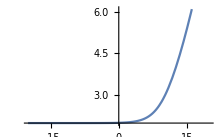

```mathematica
(*r[rstar_]=r[rstar]/.First[Out[2]];*)
Plot[{r[x](*,Evaluate[D[r[x],x]]*)},{x,-20,20},PlotRange->Automatic]
```

```mathematica
NumberForm[{r[-20],r[0],r[120]},10]
```

{2.000000456,2.010000000,101.0445977}

Define V_eff

```mathematica
Vschw[r_,l_]:=SetPrecision[(1-(2M)/r) ((l(l+1))/r^2+(2M)/r^3),20];
```

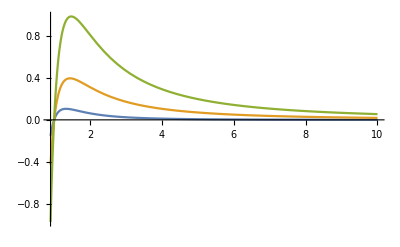
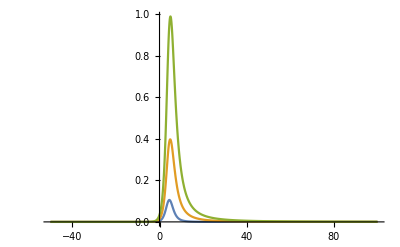

```mathematica
Row[{Plot[{Vschw[r,0],Vschw[r,1],Vschw[r,2]},{r,0.9,10},PlotRange->All],
Plot[{Vschw[r[rstar],0],Vschw[r[rstar],1],Vschw[r[rstar],2]},{rstar,-50,100},PlotRange->All]}]
```

Checking that the inversion of r behaves well on the effective potential

```mathematica
r[5]//N
{Vschw[2.01M,0],Vschw[r[0],0]}//N
{Vschw[2.114910577751456,0],Vschw[r[5],0]}//N
```

2.11491

{0.00122531,0.00122531}

{0.0114874,0.0114874}

Discretize V_eff

```mathematica
VschwDis[i_,l_]:=Vschw[r[rstar],l]/.rstar->i Δrstar ;
```

Checking two different ways of discretizing V_eff

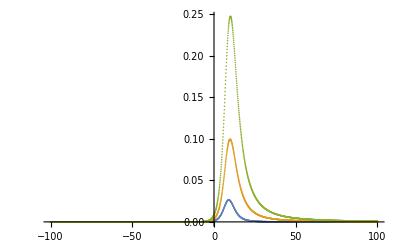
-Graphics--Graphics-

```mathematica
Δrstar=0.1;min=-10^3;max=10^3;
Row[{ListPlot[{Table[{i Δrstar  ,VschwDis[i,0]} ,{i,min,max}],  
Table[{i Δrstar  ,VschwDis[i,1]},{i,min,max}],
Table[{i Δrstar  ,VschwDis[i,2]},{i,min,max}]},Joined->False,PlotRange->All],
ListPlot[{Table[{i Δrstar  ,Vschw[r[i*Δrstar],0]} ,{i,min,max}],  
Table[{i Δrstar  ,Vschw[r[i *Δrstar],1]},{i,min,max}],
Table[{i Δrstar  ,Vschw[r[i*Δrstar],2]},{i,min,max}]},Joined->False,PlotRange->All]}]
Clear[Δrstar]
```

```mathematica
FDschw[iter_,tfinal_,l_]:=(
Clear[ψ,Length1,rstarmax,rstarmin,Δrstar,imax,imin,jmax,σ,center,ψinit2,ψinit];
(*---------Discretization setup----------*)
rstarmax=100;rstarmin=-100;Length1=(rstarmax-rstarmin);
Δrstar=Length1/iter;Δt=Δrstar*0.7;
imax=IntegerPart[N[rstarmax/Δrstar]];imin=IntegerPart[N[rstarmin/Δrstar]];
jmax = IntegerPart[N[tfinal/Δt]];
(*-------messages to check code behavior-------*)
Print[Style["# of Iterations in space = ",Blue,14,Italic,FontFamily->"Courier"],Style[iter,14,Blue,Italic]]
(**)
Print[ Style["(r_*)^max =  ",Blue,14,Italic,FontFamily->"Courier"],Style[rstarmax " , ",Blue,14,Italic,FontFamily->"Courier"],
Style["r^max =  ",Blue,14,Italic,FontFamily->"Courier"], Style[NumberForm[ r[rstarmax],10],Blue,14,Italic,FontFamily->"Courier"]]
Print[ Style["(r_*)^min =  ",Blue,14,Italic,FontFamily->"Courier"],Style[rstarmin " , ",Blue,14,Italic,FontFamily->"Courier"],
Style["r^min =  ",Blue,14,Italic,FontFamily->"Courier"], Style[NumberForm[ r[rstarmin],10],Blue,14,Italic,FontFamily->"Courier"]]
(**)
Print[Style[ "I_max = ",Blue,14,Italic,FontFamily->"Courier"],Style[imax,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style[ "I_min = ",Blue,14,Italic,FontFamily->"Courier"],Style[imin,Blue,14,Italic,FontFamily->"Courier"]]
(**)
Print[Style["Space Discretization step = ",Blue,14,Italic,FontFamily->"Courier"],Style[Δrstar,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["t_final/M = ",Blue,14,Italic,FontFamily->"Courier"],Style[tfinal/M,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style[ "# of Iterations in time = J_max = ",Blue,14,Italic,FontFamily->"Courier"],Style[jmax,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["Time Discretization step = ",Blue,14,Italic,FontFamily->"Courier"],Style[Δt,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["Δt/(Δr_*) = ",Blue,14,Italic,FontFamily->"Courier"],Style[N[Δt/Δrstar],Blue,14,Italic,FontFamily->"Courier"]];
(*-------V effective Discretization------*)
Do[V[i_]:=SetPrecision[Vschw[r[i* Δrstar],l] ,20],{i,imin,imax}]
(*--------Initial Condtions--------*) 
σ=5;center=0;
ψ[i_,0]:=ψinit2[rstar] /.rstar->i Δrstar  ;
ψinit2[rstar_]:=SetPrecision[ Exp[-(rstar-center)^2/(2 σ^2)],20];
(*-------------------------------*)
ψ[i_,-1]:=SetPrecision[ψinit[r[rstar]] ,20] /.rstar->i Δrstar ;
ψinit[r[rstar_]]=0; 
(**)
(*--------Iterating Scheme---------*)
Do[ (*ψ[imin,j_]:=ψ[imin,j]=(*ψ[imin+1,j-2]*)SetPrecision[ψ[imin+1,j-1]+((Δt-Δrstar)/(Δt+Δrstar))*( ψ[imin+1,j]-ψ[imin,j-1]),20];*)
ψ[i_,j_]:=ψ[i,j]= SetPrecision[-ψ[i,j-2]+(Δt/Δrstar)^2(ψ[i+1,j-1]+ψ[i-1,j-1]) + (2-2 (Δt/Δrstar)^2-V[i] Δt^2) ψ[i,j-1],20];
(*--------Boundary Conditions--------*)
(*ψ[imax,j_]:=ψ[imax,j]=(*ψ[imax-1,j-2]*)SetPrecision[ψ[imax-1,j-1]+((Δt-Δrstar)/(Δt+Δrstar))*( ψ[imax-1,j]-ψ[imax,j-1]) ,20]  ;*)
,{j,1,jmax},{i,imin+1,imax-1}] 

);
```

lambda = 0

l=0

```mathematica
FDschw[1200,150,0]
```

# of Iterations in space = 1200

(r_*)^max =  110  , r^max =  93.75952809

(r_*)^min =  -40  , r^min =  2.000000053

I_max = 880

I_min = -320

Space Discretization step = 1/8

t_final/M = 150

# of Iterations in time = J_max = 2400

Time Discretization step = 0.0625

Δt/(Δr_*) = 0.5

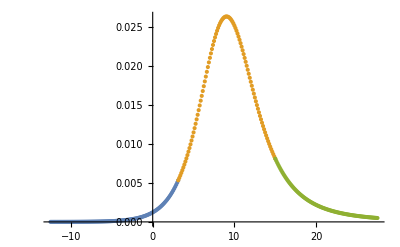

```mathematica
ListPlot[{Table[{i Δrstar  ,Vschw[r[i*Δrstar],0]},{i,-100,25}],
Table[{i Δrstar  ,Vschw[r[i*Δrstar],0]},{i,25,120}],
Table[{i Δrstar  ,Vschw[r[i*Δrstar],0]},{i,120,220}]},Joined->False,PlotRange->All]
```

2.002101862796826

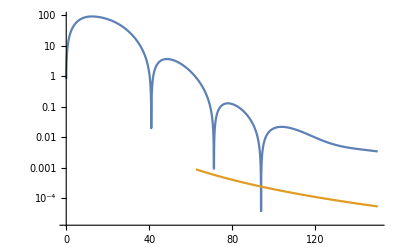

```mathematica
i=-25;
NumberForm[r[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},  ListLogPlot[{Table[{(j Δt)/M ,Evaluate[Abs[ψ[i,j]]]},{j,0,jmax}]  
,Table[{(j Δt)/M,Evaluate[10^2.7(j Δt)^(-(3.2))]},{j,1000,jmax}]},Joined->True,PlotRange->All] ]
```

```mathematica
Schwl0data= Table[{(j Δt)/M ,ψ[i,j]},{j,0,jmax}]  ;
```

```mathematica
Export["Schw_l0data.txt" ,Schwl0data,"Table","FieldSeparators"->" "];
```

```mathematica
Schwl0data=Import["Schw_l0data.txt","Table"];
```

```mathematica
FilePrint["Schw_l0data.txt"]
```

0. E^(-25/128)
0.125 1.6450761366501538
0.25 2.4674167470857507
0.375 3.2895204429906055
0.5 4.111308311073053
0.625 4.932701487924793
0.75 5.753621172468916
0.875 6.573988638392754
1. 7.393725246562527
1.125 8.212752457416656
1.25 9.030991843333826
1.375 9.848365100969612
1.5 10.664794063550307
1.625 11.480200713103695
1.75 12.294507192595443
1.875 13.107635817931008
2. 13.919509089783089
2.125 14.730049705217924
2.25 15.539180569116667
2.375 16.34682480540794
2.5 17.152905768126917
2.625 17.957347052284508
2.75 18.760072504473943
2.875 19.561006233086125
3. 20.36007261798104
3.125 21.157196319488257
3.25 21.952302286677153
3.375 22.745315764914118
3.5 23.536162302773125
3.625 24.324767758367813
3.75 25.111058305137405
3.875 25.894960437074626
4. 26.676400973359357
4.125 27.45530706236663
4.25 28.23160618503901
4.375 29.005226157630418
4.5 29.776095133826
4.625 30.544141606220293
4.75 31.30929440710196
4.875 32.0714827084576
5. 32.830636021075364
5.125 33.58668419260529
5.25 34.339557404424625
5.375 35.08918616717028
5.5 35.83550131484046
5.625 36.57843399742501
5.75 37.31791567208133
5.875 38.05387809290767
6. 38.78625329936641
6.125 39.514973603372496
6.25 40.23997157499835
6.375 40.9611800266744
6.5 41.67853199570959
6.625 42.391960724943054
6.75 43.10139964138023
6.875 43.806782332753784
7. 44.508042522044164
7.125 45.20511404004863
7.25 45.897930796068515
7.375 46.58642674670729
7.5 47.27053586268735
7.625 47.950192093565825
7.75 48.62532933028216
7.875 49.29588136556823
8. 49.961781852317436
8.125 50.62296425997609
8.25 51.27936182887762
8.375 51.93090752224997
8.5 52.57753397548426
8.625 53.219173442242045
8.75 53.855757737127014
8.875 54.48721817493038
9. 55.11348550681654
9.125 55.73448985417693
9.25 56.35016064117229
9.375 56.96042652713393
9.5 57.565215339946306
9.625 58.16445401127197
9.75 58.758068514067304
9.875 59.345983802402706
10. 59.92812375329639
10.125 60.504411110189274
10.25 61.07476742781117
10.375 61.63911301838516
10.5 62.19736689922453
10.625 62.74944674170021
10.75 63.2952688213513
10.875 63.8347479687696
11. 64.36779752105271
11.125 64.8943292742311
11.25 65.41425343806955
11.375 65.92747859573377
11.5 66.43391167159139
11.625 66.93345791054305
11.75 67.42602087165506
11.875 67.91150243770474
12. 68.38980284099785
12.125 68.86082070494399
12.25 69.32445310066012
12.375 69.78059561827627
12.5 70.22914245333395
12.625 70.66998650928265
12.75 71.10301951727689
12.875 71.52813217416183
13. 71.94521429883547
13.125 72.35415500634673
13.25 72.75484289839493
13.375 73.14716626852825
13.5 73.53101332037504
13.625 73.90627239764328
13.75 74.27283222523822
13.875 74.63058216143672
14. 74.97941246136116
14.125 75.31921455184464
14.25 75.64988131717955
14.375 75.97130739439638
14.5 76.28338947591975
14.625 76.58602661690962
14.75 76.8791205443195
14.875 77.16257596449937
15. 77.43630086582016
15.125 77.70020681228057
15.25 77.95420922365683
15.375 78.19822763793871
15.5 78.43218595289424
15.625 78.65601264551687
15.75 78.86964097020734
15.875 79.07300913794174
16. 79.26606047871505
16.125 79.44874358821735
16.25 79.62101245771768
16.375 79.78282658459324
16.5 79.93415106070782
16.625 80.07495663704981
16.75 80.20521976504438
16.875 80.3249226167371
17. 80.43405308681928
17.125 80.53260477908114
17.25 80.62057697881086
17.375 80.69797461160518
17.5 80.7648081885
17.625 80.82109373732443
17.75 80.86685272050643
17.875 80.90211193999087
18. 80.92690343040466
18.125 80.94126434212114
18.25 80.94523681630973
18.375 80.93886785410338
18.5 80.92220918141771
18.625 80.89531710981935
18.75 80.85825239275337
18.875 80.81108007615694
19. 80.75386934337578
19.125 80.68669335594979
19.25 80.6096290932013
19.375 80.52275719365284
19.5 80.42616179991906
19.625 80.3199304066874
19.75 80.20415371005697
19.875 80.07892545675452
20. 79.94434229338333
20.125 79.80050361767366
20.25 79.64751143432696
20.375 79.48547021695124
20.5 79.3144867754822
20.625 79.13467012682315
20.75 78.94613136636977
20.875 78.7489835396469
21. 78.54334151538023
21.125 78.329321862518
21.25 78.10704273324261
21.375 77.87662375226897
21.5 77.6381859109494
21.625 77.39185146406092
21.75 77.13774382795147
21.875 76.8759874802728
22. 76.60670786269274
22.125 76.33003128799383
22.25 76.04608485193394
22.375 75.75499634899397
22.5 75.45689419057979
22.625 75.15190732473478
22.75 74.84016515753993
22.875 74.52179747728403
23. 74.19693438252023
23.125 73.86570621427194
23.25 73.52824349153175
23.375 73.18467684861587
23.5 72.83513697331485
23.625 72.4797545458654
23.75 72.11866017980537
23.875 71.75198436603829
24. 71.37985742073073
24.125 71.0024094364744
24.25 70.61977023529194
24.375 70.23206932214902
24.5 69.83943583860018
24.625 69.44199851736946
24.75 69.03988563922411
24.875 68.6332249930571
25. 68.22214383897713
25.125 67.8067688732231
25.25 67.38722619357239
25.375 66.96364126468633
25.5 66.53613888394364
25.625 66.10484314893512
25.75 65.66987742749096
25.875 65.23136433014588
26. 64.78942568406946
26.125 64.3441825073607
26.25 63.89575498329525
26.375 63.44426243505691
26.5 62.98982330193816
26.625 62.532555117620504
26.75 62.07257449027273
26.875 61.60999708355139
27. 61.14493759767993
27.125 60.677509750529744
27.25 60.20782625940164
27.375 59.7359988243628
27.5 59.262138113401846
27.625 58.78635374881917
27.75 58.30875429388589
27.875 57.82944723921981
28. 57.34853898920703
28.125 56.86613484940759
28.25 56.38233901569354
28.375 55.89725456501161
28.5 55.41098344684444
28.625 54.923626474362315
28.75 54.43528331501079
28.875 53.9460524812656
29. 53.456031322678285
29.125 52.96531601978093
29.25 52.47400157934739
29.375 51.98218182980543
29.5 51.489949415864714
29.625 50.99739579247638
29.75 50.504611219213984
29.875 50.01168475624392
30. 49.51870426214459
30.125 49.02575639267291
30.25 48.53292659913215
30.375 48.04029912565376
30.5 47.547957005940724
30.625 47.055982060805015
30.75 46.56445489750368
30.875 46.07345491069566
31. 45.58306028378799
31.125 45.09334798940164
31.25 44.604393788704186
31.375 44.11627223058001
31.5 43.629056652008664
31.625 43.14281918025884
31.75 42.65763073622401
31.875 42.17356103751026
32. 41.69067860034352
32.125 41.209050740599736
32.25 40.728743575223525
32.375 40.24982202516961
32.5 39.772349819897954
32.625 39.296389502329454
32.75 38.82200243298823
32.875 38.34924879296524
33. 37.87818758654191
33.125 37.40887664476995
33.25 36.94137263062896
33.375 36.47573104517545
33.5 36.012006233412514
33.625 35.550251389037506
33.75 35.09051855837542
33.875 34.63285864466285
34. 34.177321413662945
34.125 33.7239555005442
34.25 33.27280841698106
34.375 32.82392655739296
34.5 32.377355204154384
34.625 31.93313853265436
34.75 31.491319617326795
34.875 31.051940439005968
35. 30.615041892884136
35.125 30.180663795931157
35.25 29.74884489324819
35.375 29.31962286390675
35.5 28.893034327390517
35.625 28.46911485130108
35.75 28.047898959931047
35.875 27.629420142615167
36. 27.213710861073277
36.125 26.80080255597852
36.25 26.390725653785463
36.375 25.983509574700562
36.5 25.579182741710316
36.625 25.177772589688523
36.75 24.779305573607452
36.875 24.383807175779758
37. 23.991301913031027
37.125 23.60181334484792
37.25 23.21536408272336
37.375 22.831975799881892
37.5 22.451669240275308
37.625 22.074464226469978
37.75 21.700379667136055
37.875 21.32943356528942
38. 20.96164302781298
38.125 20.59702427566144
38.25 20.23559265356823
38.375 19.877362638575196
38.5 19.522347847843264
38.625 19.17056104692758
38.75 18.822014159335318
38.875 18.476718277053156
39. 18.13468367087455
39.125 17.795919799572992
39.25 17.460435318069454
39.375 17.12823808571873
39.5 16.799335175782637
39.625 16.473732886108767
39.75 16.15143674995351
39.875 15.832451545778701
40. 15.516781305824225
40.125 15.204429324423327
40.25 14.895398167305146
40.375 14.589689682254674
40.5 14.287305010273787
40.625 13.988244595942529
40.75 13.692508196435325
40.875 13.400094889911133
41. 13.111003084601302
41.125 12.825230529299683
41.25 12.542774324682739
41.375 12.26363093413303
41.5 11.987796193208595
41.625 11.715265318164132
41.75 11.446032914819401
41.875 11.180092988760778
42. 10.917438956637119
42.125 10.658063657304217
42.25 10.401959361716443
42.375 10.149117781626755
42.5 9.899530078259955
42.625 9.653186872146007
42.75 9.410078254221036
42.875 9.170193797125398
43. 8.933522565443203
43.125 8.700053124604878
43.25 8.469773549403973
43.375 8.242671433420401
43.5 8.01873389978215
43.625 7.797947612439842
43.75 7.580298786642075
43.875 7.365773198030949
44. 7.154356191040124
44.125 6.9460326878964604
44.25 6.740787198931233
44.375 6.538603833660197
44.5 6.339466311356367
44.625 6.1433579702937555
44.75 5.950261776051194
44.875 5.76016033010041
45. 5.573035879589671
45.125 5.388870328076732
45.25 5.207645246048117
45.375 5.0293418802354894
45.5 4.8539411618291854
45.625 4.681423714669193
45.75 4.511769864454241
45.875 4.344959649000878
46. 4.18097282855887
46.125 4.019788895102131
46.25 3.8613870804331922
46.375 3.7057463639928367
46.5 3.5528454814712167
46.625 3.402662934494983
46.75 3.2551770005995415
46.875 3.1103657423840527
47. 2.968207015467254
47.125 2.828678475924627
47.25 2.691757588294262
47.375 2.5574216346217966
47.5 2.4256477239687313
47.625 2.296412801318501
47.75 2.1696936553283077
47.875 2.0454669253928848
48. 1.9237091090472966
48.125 1.8043965703238536
48.25 1.687505548697976
48.375 1.5730121676381894
48.5 1.4608924420892813
48.625 1.351122285151993
48.75 1.2436775148893746
48.875 1.1385338619698717
49. 1.0356669779753895
49.125 0.9350524434999916
49.25 0.8366657752967948
49.375 0.740482432555184
49.5 0.6464778231186624
49.625 0.5546273104038928
49.75 0.46490622101779605
49.875 0.3772898523254353
50. 0.2917534791958099
50.125 0.20827235985350095
50.25 0.1268217415157902
50.375 0.04737686658912621
50.5 -0.03008702043795196
50.625 -0.10559466601978054
50.75 -0.17917080126657278
50.875 -0.250840136542757
51. -0.320627356403194
51.125 -0.3885571141091695
51.25 -0.454654025475622
51.375 -0.5189426625332654
51.5 -0.5814475477479366
51.625 -0.6421931490915758
51.75 -0.7012038755442427
51.875 -0.7585040723060825
52. -0.8141180153862899
52.125 -0.8680699059298033
52.25 -0.9203838649786262
52.375 -0.9710839290337443
52.5 -1.020194046114279
52.625 -1.0677380716441127
52.75 -1.113739763772482
52.875 -1.1582227783773629
53. -1.2012106643918485
53.125 -1.2427268598690757
53.25 -1.2827946885876853
53.375 -1.3214373565879622
53.5 -1.3586779482046607
53.625 -1.394539421745847
53.75 -1.429044605395053
53.875 -1.4622161937838256
54. -1.4940767451294739
54.125 -1.5246486783923372
54.25 -1.5539542699942677
54.375 -1.5820156501606086
54.5 -1.6088547993974665
54.625 -1.6344935455685805
54.75 -1.6589535615473374
54.875 -1.6822563629637335
55. -1.7044233055763356
55.125 -1.725475582256081
55.25 -1.7454342200280342
55.375 -1.7643200776415484
55.5 -1.7821538437141733
55.625 -1.7989560350340121
55.75 -1.814746994548661
55.875 -1.8295468889624606
56. -1.843375706323727
56.125 -1.8562532540700922
56.25 -1.8681991576375434
56.375 -1.8792328592811771
56.5 -1.8893736166413198
56.625 -1.898640500920519
56.75 -1.9070523949904918
56.875 -1.9146279918883904
57. -1.9213857938600796
57.125 -1.927344111659832
57.25 -1.9325210636513694
57.375 -1.9369345745270483
57.5 -1.9406023739036848
57.625 -1.9435419952405062
57.75 -1.9457707752821705
57.875 -1.9473058537957777
58. -1.948164173162763
58.125 -1.9483624776001265
58.25 -1.947917312210711
58.375 -1.9468450222898628
58.5 -1.9451617531308227
58.625 -1.9428834501556866
58.75 -1.9400258589528494
58.875 -1.936604524958569
59. -1.9326347929250498
59.125 -1.9281318065803763
59.25 -1.9231105087568774
59.375 -1.917585641871405
59.5 -1.9115717483622763
59.625 -1.9050831707886755
59.75 -1.8981340516787937
59.875 -1.8907383335063157
60. -1.8829097591012762
60.125 -1.8746618724343846
60.25 -1.8660080194071496
60.375 -1.8569613483265193
60.5 -1.8475348100951698
60.625 -1.8377411584676007
60.75 -1.8275929507028066
60.875 -1.817102548607334
61. -1.8062821196324506
61.125 -1.7951436376818048
61.25 -1.7836988836065313
61.375 -1.7719594457046908
61.5 -1.7599367205757794
61.625 -1.7476419143778426
61.75 -1.7350860441861842
61.875 -1.7222799390926418
62. -1.709234240969301
62.125 -1.6959594051764213
62.25 -1.6824657015802424
62.375 -1.6687632159807269
62.5 -1.6548618516873645
62.625 -1.6407713308698069
62.75 -1.6265011955555375
62.875 -1.6120608085134167
63. -1.5974593543983626
63.125 -1.582705841308126
63.25 -1.5678091025331997
63.375 -1.5527777981199484
63.5 -1.537620416069391
63.625 -1.5223452733658847
63.75 -1.5069605172149112
63.875 -1.4914741266896732
64. -1.4758939146139758
64.125 -1.4602275293006222
64.25 -1.4444824559204292
64.375 -1.4286660176482107
64.5 -1.4127853769629306
64.625 -1.396847537347742
64.75 -1.3808593452669298
64.875 -1.3648274920441592
65. -1.3487585153729102
65.125 -1.3326588005546616
65.25 -1.316534581833953
65.375 -1.300391944118635
65.5 -1.2842368250144895
65.625 -1.2680750168099313
65.75 -1.2519121681011636
65.875 -1.2357537851002767
66. -1.2196052329811926
66.125 -1.2034717375903108
66.25 -1.1873583875051879
66.375 -1.1712701360943767
66.5 -1.1552118032326772
66.625 -1.1391880766595683
66.75 -1.123203513315456
66.875 -1.107262541016492
67. -1.091369460506695
67.125 -1.075528447563886
67.25 -1.0597435547824603
67.375 -1.0440187129651768
67.5 -1.0283577324324908
67.625 -1.012764304638928
67.75 -0.9972420041911421
67.875 -0.9817942909732196
68. -0.9664245119764081
68.125 -0.9511359027097281
68.25 -0.9359315884683884
68.375 -0.920814585872685
68.5 -0.9057878048276651
68.625 -0.890854050643476
68.75 -0.8760160258934547
68.875 -0.8612763318313357
69. -0.8466374696078081
69.125 -0.8321018417163832
69.25 -0.8176717538734729
69.375 -0.8033494171117845
69.5 -0.7891369496499908
69.625 -0.7750363783063847
69.75 -0.7610496396555042
69.875 -0.7471785813688407
70. -0.7334249639973444
70.125 -0.719790463018252
70.25 -0.7062766707012713
70.375 -0.6928850975103156
70.5 -0.6796171731946127
70.625 -0.6664742480152633
70.75 -0.6534575944152865
70.875 -0.6405684090026835
71. -0.6278078143997988
71.125 -0.6151768606264455
71.25 -0.6026765261221775
71.375 -0.5903077188525881
71.5 -0.5780712778549013
71.625 -0.5659679751423328
71.75 -0.5539985175248585
71.875 -0.5421635479685056
72. -0.5304636465474997
72.125 -0.5188993314268933
72.25 -0.5074710602745086
72.375 -0.49617923207386333
72.5 -0.485024188906029
72.625 -0.47400621728108594
72.75 -0.46312554902056124
72.875 -0.4523823621153764
73. -0.4417767819975658
73.125 -0.43130888325116246
73.25 -0.4209786913462047
73.375 -0.4107861839394137
73.5 -0.4007312916887864
73.625 -0.39081389898799107
73.75 -0.38103384509372173
73.875 -0.371390925725966
74. -0.3618848947464887
74.125 -0.35251546542664225
74.25 -0.34328231119711267
74.375 -0.3341850662617024
74.5 -0.32522332657839537
74.625 -0.31639665134237005
74.75 -0.3077045646025348
74.875 -0.29914655649515043
75. -0.290722083932656
75.125 -0.28243057110129766
75.25 -0.27427141029591096
75.375 -0.26624396328078775
75.5 -0.2583475628389546
75.625 -0.2505815139709255
75.75 -0.24294509452727842
75.875 -0.23543755559589186
76. -0.22805812219219046
76.125 -0.22080599449457805
76.25 -0.21368034932215302
76.375 -0.20668034129839974
76.5 -0.19980510343272187
76.625 -0.19305374740411238
76.75 -0.18642536411015032
76.875 -0.17991902477519328
77. -0.17353378235314046
77.125 -0.16726867265623352
77.25 -0.161122714891076
77.375 -0.15509491184636856
77.5 -0.14918425030526736
77.625 -0.1433897020258889
77.75 -0.1377102250666008
77.875 -0.1321447648804106
78. -0.1266922548111863
78.125 -0.12135161619367554
78.25 -0.11612175863492591
78.375 -0.11100158086784116
78.5 -0.10598997199724464
78.625 -0.10108581256055266
78.75 -0.09628797498996355
78.875 -0.0915953236333836
79. -0.08700671491151658
79.125 -0.08252099804626863
79.25 -0.07813701622652616
79.375 -0.0738536076359686
79.5 -0.06966960588693658
79.625 -0.06558383997111801
79.75 -0.06159513429963326
79.875 -0.05770230930899796
80. -0.0539041825461676
80.125 -0.05019956966443449
80.25 -0.046587284834524324
80.375 -0.04306614063397467
80.5 -0.03963494797810044
80.625 -0.03629251660702271
80.75 -0.033037656090087505
80.875 -0.02986917679084447
81. -0.026785890260677642
81.125 -0.023786609075740383
81.25 -0.020870146667070644
81.375 -0.018035317692856562
81.5 -0.015280938962826372
81.625 -0.012605830373332669
81.75 -0.01000881528853645
81.875 -0.007488720333596058
82. -0.005044375132451354
82.125 -0.002674612570035248
82.25 -0.00037826963763726556
82.375 0.0018458116609122487
82.5 0.0039987839358428725
82.625 0.006081794653574143
82.75 0.008095986482607757
82.875 0.010042497136198557
83. 0.011922458604623513
83.125 0.0137369962769176
83.25 0.015487228570972919
83.375 0.0171742672029282
83.5 0.018799217608108286
83.625 0.02036317888310742
83.75 0.021867243094011224
83.875 0.023312494425117944
84. 0.02470000880861363
84.125 0.02603085421352129
84.25 0.027306091133104823
84.375 0.028526772620641107
84.5 0.029693943671690246
84.625 0.030808640398991272
84.75 0.03187188965826197
84.875 0.03288470934949442
85. 0.033848108962393875
85.125 0.034763089699900926
85.25 0.0356306439323315
85.375 0.03645175439766664
85.5 0.037227393820437875
85.625 0.03795852521868134
85.75 0.03864610249927122
85.875 0.03929107066320712
86. 0.03989436532929623
86.125 0.04045691195912971
86.25 0.040979625466407876
86.375 0.04146341052336123
86.5 0.04190916219812408
86.625 0.04231776623577771
86.75 0.042690098649121835
86.875 0.0430270249677151
87. 0.04332939983539992
87.125 0.04359806731052946
87.25 0.043833861537874594
87.375 0.04403760709945791
87.5 0.04421011866988166
87.625 0.04435220028890547
87.75 0.044464644945326655
87.875 0.04454823486587893
88. 0.04460374221452796
88.125 0.044631929507195876
88.25 0.044633549329041164
88.375 0.044609343630135585
88.5 0.044560043294251526
88.625 0.044486368411855944
88.75 0.04438902900007353
88.875 0.04426872547553029
89. 0.04412614843093704
89.125 0.04396197795349389
89.25 0.04377688317748007
89.375 0.043571522537282414
89.5 0.0433465445017253
89.625 0.04310258809941931
89.75 0.04284028275199314
89.875 0.04256024761494596
90. 0.04226309111329561
90.125 0.041949411171118806
90.25 0.04161979595439606
90.375 0.04127482444342795
90.5 0.040915066320035574
90.625 0.04054108133061406
90.75 0.040153418804383945
90.875 0.03975261785641973
91. 0.03933920813363198
91.125 0.03891371042906479
91.25 0.038476636620441824
91.375 0.03802848905524926
91.5 0.037569760051410724
91.625 0.03710093207122882
91.75 0.03662247846554173
91.875 0.036134864124923435
92. 0.03563854546698422
92.125 0.035133969843377695
92.25 0.03462157502300297
92.375 0.03410178933476099
92.5 0.03357503240538401
92.625 0.03304171584281011
92.75 0.032502243269690576
92.875 0.031957009752247904
93. 0.03140640126632663
93.125 0.030850794807278918
93.25 0.030290559117393374
93.375 0.029726055396967845
93.5 0.029157637381538058
93.625 0.028585650792557895
93.75 0.028010432786836535
93.875 0.027432312032278854
94. 0.026851609421279652
94.125 0.026268638805295272
94.25 0.02568370711338502
94.375 0.025097113824712518
94.5 0.024509150402069805
94.625 0.02392010033253645
94.75 0.023330239823582247
94.875 0.022739838557179815
95. 0.022149159847323484
95.125 0.021558460134396253
95.25 0.02096798840367755
95.375 0.020377986190368173
95.5 0.019788688255568357
95.625 0.019200323356243228
95.75 0.018613114439438104
95.875 0.01802727815852338
96. 0.017443024277661
96.125 0.016860555640916684
96.25 0.016280068825655032
96.375 0.01570175492497155
96.5 0.015125799776467974
96.625 0.014552383500450308
96.75 0.013981679891455445
96.875 0.013413856351423871
97. 0.01284907451834779
97.125 0.012287491057981704
97.25 0.011729257925098045
97.375 0.011174521923730833
97.5 0.010623424086996862
97.625 0.010076099574604648
97.75 0.009532678274955731
97.875 0.008993285603197539
98. 0.008458042792940525
98.125 0.007927066478601436
98.25 0.007400468064791184
98.375 0.006878353588646692
98.5 0.00636082429390257
98.625 0.0058479774326123226
98.75 0.005339906585416283
98.875 0.004836701266044331
99. 0.0043384462815916815
99.125 0.0038452215603466664
99.25 0.00335710269662641
99.375 0.0028741617537212166
99.5 0.0023964676108930326
99.625 0.0019240855900936606
99.75 0.0014570768084843774
99.875 0.0009954979725950094
100. 0.0005394018929663871
100.125 0.00008883828608102437
100.25 -0.0003561458536467767
100.375 -0.0007955066048848406
100.5 -0.0012292037732238989
100.625 -0.0016572011296809538
100.75 -0.0020794659269476874
100.875 -0.002495968100496928
101. -0.0029066798732720104
101.125 -0.003311576084427853
101.25 -0.0037106348481671476
101.375 -0.00410383782380384
101.5 -0.004491169763387246
101.625 -0.004872617717652053
101.75 -0.005248170618939297
101.875 -0.005617819587635636
102. -0.005981558594615362
102.125 -0.006339384761652427
102.25 -0.006691297940727212
102.375 -0.007037299926480476
102.5 -0.007377394018885435
102.625 -0.007711585307411193
102.75 -0.00803988133570713
102.875 -0.008362292431049505
103. -0.008678831315419137
103.125 -0.00898951232590016
103.25 -0.00929435095851663
103.375 -0.009593364130165205
103.5 -0.009886570844228485
103.625 -0.010173992547716317
103.75 -0.01045565277407965
103.875 -0.01073157637285025
104. -0.011001789035977916
104.125 -0.011266317537580737
104.25 -0.011525190399185172
104.375 -0.01177843827316043
104.5 -0.012026093617094401
104.625 -0.01226818993383114
104.75 -0.012504761281588101
104.875 -0.01273584249160198
105. -0.012961469831728452
105.125 -0.013181681414721728
105.25 -0.013396516903863863
105.375 -0.013606016764415365
105.5 -0.013810221758736028
105.625 -0.014009173141948463
105.75 -0.014202913322696704
105.875 -0.01439148629481497
106. -0.014574937373793713
106.125 -0.01475331246051724
106.25 -0.014926657522528253
106.375 -0.015095018767836265
106.5 -0.015258443301673827
106.625 -0.015416979580093304
106.75 -0.015570677176778906
106.875 -0.015719586059854664
107. -0.015863756060397527
107.125 -0.016003237024552412
107.25 -0.016138079465168473
107.375 -0.016268335035839368
107.5 -0.01639405632746699
107.625 -0.01651529615880679
107.75 -0.016632107033291404
107.875 -0.016744541269666385
108. -0.01685265164747005
108.125 -0.0169564919000486
108.25 -0.017056116540193574
108.375 -0.017151580164965666
108.5 -0.017242936901818277
108.625 -0.017330240517994353
108.75 -0.017413545058896085
108.875 -0.017492905358657385
109. -0.017568376894146198
109.125 -0.01764001510452391
109.25 -0.01770787482759446
109.375 -0.017772010388203512
109.5 -0.01783247622858429
109.625 -0.01788932743508652
109.75 -0.01794261961979449
109.875 -0.017992408255213303
110. -0.018038748101740738
110.125 -0.018081693275348
110.25 -0.01812129786905516
110.375 -0.018157616494441895
110.5 -0.018190704190083635
110.625 -0.018220615771668905
110.75 -0.018247405251440335
110.875 -0.018271125885464257
111. -0.01829183078546772
111.125 -0.018309573473813772
111.25 -0.01832440781794587
111.375 -0.018336387396177038
111.5 -0.01834556490989336
111.625 -0.01835199221072252
111.75 -0.018355720902010254
111.875 -0.018356802905979103
112. -0.018355290423361117
112.125 -0.018351235315057904
112.25 -0.018344688507876804
112.375 -0.018335700001934227
112.5 -0.01832431946110335
112.625 -0.0183105967911055
112.75 -0.01829458212348818
112.875 -0.018276325213304433
113. -0.018255874839129573
113.125 -0.018233278791073504
113.25 -0.018208584449603795
113.375 -0.018181839373363682
113.5 -0.018153091306631654
113.625 -0.018122387593104583
113.75 -0.018089774570899723
113.875 -0.018055297541572694
114. -0.018019001336793607
114.125 -0.017980930914750018
114.25 -0.0179411313902312
114.375 -0.01789964746455606
114.5 -0.01785652281622347
114.625 -0.017811800051338145
114.75 -0.017765521257665604
114.875 -0.017717728608523352
115. -0.01766846441463553
115.125 -0.01761777057021562
115.25 -0.01756568793991149
115.375 -0.01751225629107768
115.5 -0.0174575148348127
115.625 -0.017401502836306083
115.75 -0.017344259687612315
115.875 -0.01728582436984247
116. -0.01722623483698618
116.125 -0.01716552793044934
116.25 -0.01710373990671314
116.375 -0.0170409070531614
116.5 -0.016977065780958797
116.625 -0.016912252103313576
116.75 -0.01684650101676633
116.875 -0.01677984639844821
117. -0.016712321520058887
117.125 -0.016643959668238863
117.25 -0.016574794256725183
117.375 -0.016504858320590246
117.5 -0.016434183895531678
117.625 -0.01636280189829877
117.75 -0.016290742626734744
117.875 -0.01621803638382574
118. -0.016144713608349404
118.125 -0.01607080438500018
118.25 -0.01599633782220912
118.375 -0.015921341916202918
118.5 -0.015845844036898534
118.625 -0.015769871554800096
118.75 -0.015693451989359404
118.875 -0.015616612534863787
119. -0.015539379437275354
119.125 -0.01546177784238075
119.25 -0.015383832267362457
119.375 -0.01530556722976862
119.5 -0.015227007412843134
119.625 -0.015148177207066729
119.75 -0.015069100086513807
119.875 -0.01498979844157421
120. -0.014910294036058895
120.125 -0.014830608637484083
120.25 -0.014750764198607186
120.375 -0.014670782414465787
120.5 -0.014590684098722774
120.625 -0.014510489001468535
120.75 -0.014430216251794775
120.875 -0.014349884988712631
121. -0.014269514558161606
121.125 -0.014189124085364855
121.25 -0.014108731851586872
121.375 -0.014028355097508433
121.5 -0.01394801045123614
121.625 -0.013867714559231905
121.75 -0.01378748429809953
121.875 -0.013707336362069984
122. -0.013627286640567535
122.125 -0.013547350007635933
122.25 -0.013467540735373174
122.375 -0.013387873124294195
122.5 -0.013308361729234625
122.625 -0.013229020961786983
122.75 -0.013149864469061944
122.875 -0.013070904909644538
123. -0.012992154352465923
123.125 -0.01291362490605161
123.25 -0.012835328957896132
123.375 -0.012757278791660049
123.5 -0.012679485967494238
123.625 -0.012601961085005723
123.75 -0.012524714167609351
123.875 -0.012447755290158461
124. -0.012371094831174226
124.125 -0.012294743104616552
124.25 -0.012218709742129047
124.375 -0.012143003443494175
124.5 -0.012067632346526339
124.625 -0.011992604652603125
124.75 -0.011917928891134227
124.875 -0.011843613565696631
125. -0.011769666538534878
125.125 -0.011696094768992912
125.25 -0.011622904669057682
125.375 -0.011550102726372951
125.5 -0.011477695780374834
125.625 -0.01140569068258183
125.75 -0.011334093683656598
125.875 -0.01126291016027751
126. -0.011192144956443328
126.125 -0.011121803003572699
126.25 -0.011051889607749988
126.375 -0.010982410123957264
126.5 -0.010913369345989188
126.625 -0.010844771222225616
126.75 -0.010776619182834603
126.875 -0.01070891675660584
127. -0.010641667868788186
127.125 -0.010574876529061588
127.25 -0.010508546224583564
127.375 -0.010442679625106605
127.5 -0.010377278896210438
127.625 -0.010312346312522834
127.75 -0.010247884565636063
127.875 -0.010183896465618293
128. -0.010120384337475995
128.125 -0.010057349716081791
128.25 -0.009994793645603205
128.375 -0.009932717288794237
128.5 -0.00987112224447842
128.625 -0.009810010262367233
128.75 -0.00974938264318308
128.875 -0.009689239923850932
129. -0.00962958216332142
129.125 -0.009570409547672562
129.25 -0.009511722716691005
129.375 -0.009453522491770753
129.5 -0.009395809279914541
129.625 -0.00933858274961307
129.75 -0.009281842103255212
129.875 -0.009225586677800272
130. -0.00916981628001486
130.125 -0.009114530927233367
130.25 -0.00905973025544317
130.375 -0.009005413186259612
130.5 -0.008951578186116596
130.625 -0.008898223862290095
130.75 -0.008845349306374515
130.875 -0.008792953847702633
131. -0.008741036465722166
131.125 -0.008689595448471657
131.25 -0.008638628638746435
131.375 -0.008588134025259894
131.5 -0.00853811009394366
131.625 -0.008488555593814
131.75 -0.008439468953832359
131.875 -0.008390847933283145
132. -0.008342689855125362
132.125 -0.008294992192105671
132.25 -0.008247752925488964
132.375 -0.008200970323163324
132.5 -0.008154642361169133
132.625 -0.008108766366373605
132.75 -0.008063339237224115
132.875 -0.008018358024639223
133. -0.007973820297779257
133.125 -0.007929723934166993
133.25 -0.007886066546045881
133.375 -0.00784284511573377
133.5 -0.007800056204007513
133.625 -0.007757696525632152
133.75 -0.007715763321814625
133.875 -0.007674254162131268
134. -0.007633166375868259
134.125 -0.007592496680421925
134.25 -0.007552241377535941
134.375 -0.00751239692332897
134.5 -0.007472960307072627
134.625 -0.007433928864704663
134.75 -0.007395299715287761
134.875 -0.007357069382818599
135. -0.007319233980557591
135.125 -0.0072817897754521455
135.25 -0.007244733572914491
135.375 -0.007208062541711719
135.5 -0.007171773655665887
135.625 -0.007135863309209225
135.75 -0.007100327490027498
135.875 -0.007065162337769975
136. -0.007030364534503286
136.125 -0.006995931140767887
136.25 -0.00696185904263847
136.375 -0.006928144561364954
136.5 -0.006894783614565635
136.625 -0.006861772269137784
136.75 -0.006829107137079767
136.875 -0.006796785222501993
137. -0.006764803374151359
137.125 -0.00673315788946477
137.25 -0.006701844664551327
137.375 -0.006670859741234503
137.5 -0.006640199707948854
137.625 -0.006609861557488146
137.75 -0.006579842145072113
137.875 -0.006550137787110458
138. -0.006520744400201926
138.125 -0.006491658042252509
138.25 -0.006462875318181075
138.375 -0.006434393248211483
138.5 -0.0064062087315691855
138.625 -0.00637831814025095
138.75 -0.0063507174472638645
138.875 -0.006323402761762589
139. -0.0062963707392963125
139.125 -0.0062696184604425255
139.25 -0.006243142900204481
139.375 -0.006216940517067272
139.5 -0.006191007370698036
139.625 -0.006165339651058566
139.75 -0.006139934092945058
139.875 -0.006114787864772859
140. -0.006089898043744262
140.125 -0.006065261200462196
140.25 -0.006040873506306327
140.375 -0.006016731256479173
140.5 -0.005992831288596786
140.625 -0.005969170881437104
140.75 -0.005945747235942717
140.875 -0.0059225570556533
141. -0.005899596643963582
141.125 -0.005876862421058495
141.25 -0.005854351346316455
141.375 -0.005832060826841678
141.5 -0.005809988204377952
141.625 -0.005788130331835398
141.75 -0.005766483660649169
141.875 -0.005745044751560508
142. -0.0057238107005751025
142.125 -0.0057027790570619765
142.25 -0.005681947316614995
142.375 -0.005661312493932565
142.5 -0.005640871200515547
142.625 -0.005620620149299926
142.75 -0.005600556583964909
142.875 -0.005580678206409055
143. -0.00556098267558872
143.125 -0.005541467176975947
143.25 -0.005522128490795689
143.375 -0.0055029634904887595
143.5 -0.005483969575152237
143.625 -0.005465144606201331
143.75 -0.00544648641221759
143.875 -0.0054279923552210405
144. -0.0054096593896671595
144.125 -0.005391484554744457
144.25 -0.005373465409749164
144.375 -0.005355599979742968
144.5 -0.005337886266426189
144.625 -0.005320321811434226
144.75 -0.005302903746295431
144.875 -0.005285629278563259
145. -0.005268496129933708
145.125 -0.005251502490716354
145.25 -0.005234646536749691
145.375 -0.005217925989930979
145.5 -0.0052013381593388015
145.625 -0.005184880421207726
145.75 -0.005168550659604495
145.875 -0.0051523472295284265
146. -0.005136268479874006
146.125 -0.005120312311388406
146.25 -0.005104476209156522
146.375 -0.005088757716433856
146.5 -0.005073154877712157
146.625 -0.005057666210274045
146.75 -0.005042290233202518
146.875 -0.005027025022943995
147. -0.005011868237338105
147.125 -0.00499681758332063
147.25 -0.004981871262219063
147.375 -0.004967027949602479
147.5 -0.004952286330350396
147.625 -0.004937644652002684
147.75 -0.0049231007405101885
147.875 -0.004908652461806769
148. -0.00489429816915952
148.125 -0.004880036691140918
148.25 -0.004865866872763093
148.375 -0.004851787126802245
148.5 -0.004837795441464777
148.625 -0.004823889835849457
148.75 -0.004810068809188788
148.875 -0.004796331336762846
149. -0.004782676417081494
149.125 -0.004769102621346829
149.25 -0.0047556080932214355
149.375 -0.0047421909982151575
149.5 -0.004728849974678981
149.625 -0.004715584137497768
149.75 -0.00470239263130054
149.875 -0.00468927417820305
150. -0.004676227069837924
150.125 -0.00466324961068389
150.25 -0.004650340570674471
150.375 -0.004637499196521939
150.5 -0.00462472477095557
150.625 -0.004612016158902095
150.75 -0.004599371791944445
150.875 -0.004586790105608505
151. -0.004574269993437848
151.125 -0.004561810825785614
151.25 -0.004549412015067168
151.375 -0.004537072560532117
151.5 -0.0045247910253265996
151.625 -0.004512565967767866
151.75 -0.004500396396746884
151.875 -0.0044882817978210395
152. -0.004476221704449525
152.125 -0.00446421524148963
152.25 -0.00445226109502859
152.375 -0.004440357937686521
152.5 -0.004428504885231727
152.625 -0.004416701529827467
152.75 -0.004404947517222966
152.875 -0.004393242089093806
153. -0.004381584045788824
153.125 -0.004369972165687415
153.25 -0.004358405662911784
153.375 -0.004346884227592968
153.5 -0.004335407609006752
153.625 -0.004323975156889827
153.75 -0.004312585777248791
153.875 -0.004301238345787278
154. -0.0042899321665790325
154.125 -0.004278667019194153
154.25 -0.00426744274775082
154.375 -0.004256258801336442
154.5 -0.004245114183044085
154.625 -0.004234007857518836
154.75 -0.004222939210490457
154.875 -0.004211908102620081
155. -0.004200914464433106
155.125 -0.004189957835947722
155.25 -0.00417903730906947
155.375 -0.004168151929278576
155.5 -0.004157301155908909
155.625 -0.0041464849225791986
155.75 -0.004135703237986997
155.875 -0.004124955724866102
156. -0.004114241555888184
156.125 -0.0041035598495254046
156.25 -0.004092910130965313
156.375 -0.0040822923989827795
156.5 -0.00407170673256035
156.625 -0.00406115282928277
156.75 -0.004050629934889442
156.875 -0.004040137233349806
157. -0.0040296743083084756
157.125 -0.004019241216251986
157.25 -0.004008838098910375
157.375 -0.003998464721185934
157.5 -0.003988120394500723
157.625 -0.003977804361140626
157.75 -0.0039675162561551075
157.875 -0.003957256186698326
158. -0.00394702435017125
158.125 -0.003936820571760004
158.25 -0.003926644221683947
158.375 -0.003916494593826675
158.5 -0.003906371367994871
158.625 -0.003896274695317836
158.75 -0.003886204822113888
158.875 -0.003876161627146373
159. -0.003866144532906216
159.125 -0.0038561528785635846
159.25 -0.0038461863824898906
159.375 -0.003836245233586308
159.5 -0.003826329720838191
159.625 -0.003816439770377587
159.75 -0.0038065748509206877
159.875 -0.0037967343410672096
160. -0.0037869179919881603
160.125 -0.003777126024556484
160.25 -0.0037673587645607573
160.375 -0.0037576161796773946
160.5 -0.003747897779203337
160.625 -0.0037382029757487842
160.75 -0.003728531548000426
160.875 -0.0037188837435161845
161. -0.003709259919542976
161.125 -0.003699660079972498
161.25 -0.0036900837694922124
161.375 -0.003680530429719325
161.5 -0.00367099986196666
161.625 -0.003661492335584036
161.75 -0.0036520082343377428
161.875 -0.003642547593426459
162. -0.003633109988171189
162.125 -0.003623694884637105
162.25 -0.003614302102330072
162.375 -0.0036049319279657026
162.5 -0.003595584767360143
162.625 -0.0035862606825697503
162.75 -0.0035769592752305417
162.875 -0.003567680031714944
163. -0.0035584227856985565
163.125 -0.0035491878372526636
163.25 -0.003539975610202774
163.375 -0.003530786189449082
163.5 -0.0035216191990506502
163.625 -0.003512474141951883
163.75 -0.0035033508623605195
163.875 -0.003494249670075526
164. -0.003485171003290939
164.125 -0.003476114966165411
164.25 -0.0034670812017374908
164.375 -0.0034580692262292326
164.5 -0.003449078891144327
164.625 -0.003440110512726036
164.75 -0.003431164540195365
164.875 -0.0034222410936774177
165. -0.003413339832084055
165.125 -0.0034044602820360436
165.25 -0.003395602299587235
165.375 -0.0033867662046643396
165.5 -0.0033779524546647837
165.625 -0.0033691611827946404
165.75 -0.0033603920610392668
165.875 -0.003351644623773458
166. -0.0033429187290727304
166.125 -0.0033342146980400297
166.25 -0.003325532993716095
166.375 -0.0033168737598787473
166.5 -0.003308236679195598
166.625 -0.0032996212915617973
166.75 -0.0032910274549393425
166.875 -0.0032824554894679246
167. -0.00327390586164
167.125 -0.003265378723612644
167.25 -0.003256873766638862
167.375 -0.003248390534178084
167.5 -0.0032399288822141372
167.625 -0.0032314891280586775
167.75 -0.0032230717397511545
167.875 -0.003214676875935981
168. -0.0032063042346648085
168.125 -0.003197953361318525
168.25 -0.0031896241083490097
168.375 -0.0031813167886796073
168.5 -0.0031730318702867548
168.625 -0.003164769516692021
168.75 -0.003156529431226198
168.875 -0.0031483111598036993
169. -0.0031401145500391256
169.125 -0.003131939909156173
169.25 -0.0031237877037115468
169.375 -0.0031156581007496763
169.5 -0.0031075508076130673
169.625 -0.003099465369602878
169.75 -0.0030914016284179476
169.875 -0.0030833598844865863
170. -0.0030753406018025242
170.125 -0.0030673439498021637
170.25 -0.0030593696388156416
170.375 -0.003051417212649819
170.5 -0.003043486506288635
170.625 -0.0030355778125425873
170.75 -0.003027691591942165
170.875 -0.003019828015379078
171. -0.0030119867952901167
171.125 -0.0030041674732166094
171.25 -0.002996369876737465
171.375 -0.002988594290365141
171.5 -0.0029808411704626793
171.625 -0.002973110688688619
171.75 -0.0029654025589823355
171.875 -0.0029577163201186247
172. -0.002950051791811446
172.125 -0.0029424092497663855
172.25 -0.002934789145589949
172.375 -0.0029271916511004552
172.5 -0.002919616481217463
172.625 -0.002912063171561865
172.75 -0.002904531533684611
172.875 -0.002897021834179398
173. -0.0028895345195270555
173.125 -0.0028820697613019582
173.25 -0.00287462727504448
173.375 -0.0028672065929536018
173.5 -0.0028598075182120716
173.625 -0.002852430308090354
173.75 -0.0028450754036914716
173.875 -0.002837742976089081
174. -0.0028304327412506597
174.125 -0.0028231442278476935
174.25 -0.0028158772306274846
174.375 -0.0028086319974286
174.5 -0.0028014089637952975
174.625 -0.002794208300099397
174.75 -0.002787029722603123
174.875 -0.0027798727564296837
175. -0.00277273718793932
175.125 -0.0027656232555709525
175.25 -0.002758531389279706
175.375 -0.0027514617586759
175.5 -0.002744414080301967
175.625 -0.0027373878758007184
175.75 -0.0027303829232567366
175.875 -0.0027233994517881902
176. -0.0027164378857721487
176.125 -0.002709498394044704
176.25 -0.0027025806934755257
176.375 -0.0026956843023772745
176.5 -0.0026888089907740735
176.625 -0.0026819549786600717
176.75 -0.00267512268496226
176.875 -0.002668312277828078
177. -0.0026615234745686264
177.125 -0.002654755790351792
177.25 -0.0026480089873713473
177.375 -0.0026412832767081108
177.5 -0.0026345790719977686
177.625 -0.0026278965408407596
177.75 -0.0026212354011810476
177.875 -0.0026145951653112173
178. -0.0026079755878977745
178.125 -0.002601376871367078
178.25 -0.002594799424242934
178.375 -0.0025882434137242363
178.5 -0.002581708558586754
178.625 -0.0025751943685494052
178.75 -0.002568700591120995
178.875 -0.002562227420423881
179. -0.0025557752601402875
179.125 -0.002549344277273693
179.25 -0.002542934191645108
179.375 -0.0025365445106784344
179.5 -0.0025301749750641827
179.625 -0.0025238257709689666
179.75 -0.002517497297548383
179.875 -0.00251118972189836
180. -0.0025049027651835166
180.125 -0.002498635932860595
180.25 -0.002492388959133352
180.375 -0.002486162022504781
180.5 -0.0024799555178488856
180.625 -0.0024737696125999263
180.75 -0.002467604029577666
180.875 -0.0024614582726675853
181. -0.00245533207001509
181.125 -0.002449225592839892
181.25 -0.0024431392320285548
181.375 -0.0024370731555991465
181.5 -0.002431027088299862
181.625 -0.0024250005327902694
181.75 -0.0024189932115492975
181.875 -0.002413005288887213
182. -0.002407037152021853
182.125 -0.002401088969844618
182.25 -0.0023951604693513645
182.375 -0.002389251152352519
182.5 -0.002383360736059317
182.625 -0.002377489378227661
182.75 -0.0023716374626883705
182.875 -0.0023658051594537075
183. -0.002359992198053741
183.125 -0.0023541980798127563
183.25 -0.002348422517078875
183.375 -0.0023426656614256164
183.5 -0.002336927893593786
183.625 -0.0023312093849682477
183.75 -0.0023255098678922077
183.875 -0.0023198288435550543
184. -0.0023141660198403536
184.125 -0.0023085215425149986
184.25 -0.002302895789534465
184.375 -0.0022972889339066493
184.5 -0.0022917007110450104
184.625 -0.0022861306223111557
184.75 -0.002280578371467187
184.875 -0.0022750440988019297
185. -0.002269528179770566
185.125 -0.00226403078927209
185.25 -0.002258551666096935
185.375 -0.002253090312147689
185.5 -0.002247646427453365
185.625 -0.0022422201471558123
185.75 -0.0022368118444419656
185.875 -0.002231421696270405
186. -0.0022260494449993927
186.125 -0.002220694593349724
186.25 -0.002215356837971137
186.375 -0.0022100363092198887
186.5 -0.0022047333783196134
186.625 -0.0021994482245305666
186.75 -0.002194180594003969
186.875 -0.0021889299905333234
187. -0.0021836961076753935
187.125 -0.0021784790712825494
187.25 -0.0021732792508612777
187.375 -0.002168096828193397
187.5 -0.002162931553455543
187.625 -0.002157782931783986
187.75 -0.0021526506539322286
187.875 -0.0021475348415137003
188. -0.0021424358625327248
188.125 -0.0021373539014790575
188.25 -0.0021322887127599743
188.375 -0.002127239803103626
188.5 -0.0021222068607286036
188.625 -0.0021171900032457168
188.75 -0.0021121895973353166
188.875 -0.0021072058303431285
189. -0.00210223846108302
189.125 -0.0020972869981123053
189.25 -0.0020923511273896645
189.375 -0.002087430962777235
189.5 -0.0020825268698253805
189.625 -0.0020776390388856283
189.75 -0.0020727672333361114
189.875 -0.0020679109637644928
190. -0.0020630699140992475
190.125 -0.002058244194663422
190.25 -0.0020534341700346585
190.375 -0.0020486400336920123
190.5 -0.002043861553712557
190.625 -0.002039098242893233
190.75 -0.002034349783338804
190.875 -0.0020296162820208387
191. -0.002024898102685286
191.125 -0.002020195442053385
191.25 -0.002015508073037275
191.375 -0.0020108355108263824
191.5 -0.0020061774359063918
191.625 -0.0020015339520686763
191.75 -0.001996905422334328
191.875 -0.0019922920467334987
192. -0.001987693603098653
192.125 -0.0019831096091542004
192.25 -0.001978539743950092
192.375 -0.0019739841082677123
192.5 -0.0019694430645211727
192.625 -0.0019649168161268485
192.75 -0.0019604051459226526
192.875 -0.0019559075742967094
193. -0.0019514237790238438
193.125 -0.001946953858021537
193.25 -0.0019424981731937685
193.375 -0.001938056931400678
193.5 -0.0019336299205461645
193.625 -0.0019292166637769335
193.75 -0.0019248168377126104
193.875 -0.0019204305375154053
194. -0.0019160581246541312
194.125 -0.001911699809490399
194.25 -0.0019073553850715306
194.375 -0.001903024377414915
194.5 -0.0018987064621028519
194.625 -0.0018944017316177685
194.75 -0.0018901105470081326
194.875 -0.0018858331221274954
195. -0.0018815692551964948
195.125 -0.0018773184752076029
195.25 -0.0018730804568584235
195.375 -0.001868855290087249
195.5 -0.0018646433355937297
195.625 -0.0018604448107400748
195.75 -0.0018562595189327738
195.875 -0.0018520869921877956
196. -0.0018479269043943695
196.125 -0.001843779343007203
196.25 -0.00183964466839026
196.375 -0.0018355231013948237
196.5 -0.0018314144506086435
196.625 -0.0018273182511152153
196.75 -0.0018232341760745369
196.875 -0.0018191623105257536
197. -0.0018151030145226099
197.125 -0.0018110565124045174
197.25 -0.0018070226179611863
197.375 -0.0018030008694163665
197.5 -0.001798990939303518
197.625 -0.001794992910319766
197.75 -0.0017910071422092564
197.875 -0.0017870338627390514
198. -0.001783072890836946
198.125 -0.0017791237678531698
198.25 -0.001775186165736867
198.375 -0.0017712601649017758
198.5 -0.0017673461248143773
198.625 -0.0017634442766672298
198.75 -0.0017595544445181438
198.875 -0.0017556761728581445
199. -0.0017518091330850462
199.125 -0.0017479534033491904
199.25 -0.001744109342821647
199.375 -0.0017402771860758508
199.5 -0.0017364567622668227
199.625 -0.0017326476190348905
199.75 -0.0017288494272674482
199.875 -0.0017250622628852846
200. -0.0017212864847580035
200.125 -0.0017175223307976748
200.25 -0.0017137696352124403
200.375 -0.0017100279487767462
200.5 -0.001706296941880812
200.625 -0.0017025766882312384
200.75 -0.0016988675463915544
200.875 -0.0016951697575916772
201. -0.0016914831610762473
201.125 -0.0016878073107495424
201.25 -0.0016841418764940662
201.375 -0.0016804869297587259
201.5 -0.0016768428287242735
201.625 -0.0016732098178675362
201.75 -0.001669587741454248
201.875 -0.0016659761565719512
202. -0.0016623747326734279
202.125 -0.0016587835389801858
202.25 -0.001655202933230689
202.375 -0.0016516331630233231
202.5 -0.0016480740775247178
202.625 -0.0016445252369509046
202.75 -0.0016409863103393932
202.875 -0.0016374573647200841
203. -0.00163393875739384
203.125 -0.0016304307390413821
203.25 -0.001626933163676546
203.375 -0.001623445594611285
203.5 -0.0016199677004618241
203.625 -0.0016164995460605102
203.75 -0.001613041488237038
203.875 -0.0016095937806936472
204. -0.0016061562822295976
204.125 -0.0016027285592127955
204.25 -0.0015993102798149443
204.375 -0.0015959015066383266
204.5 -0.0015925025959836476
204.625 -0.0015891138045071673
204.75 -0.0015857349957517058
204.875 -0.001582365739144355
205. -0.001579005702440582
205.125 -0.0015756549460197535
205.25 -0.00157231382560667
205.375 -0.001568982600719394
205.5 -0.0015656611395479182
205.625 -0.0015623490145141349
205.75 -0.001559045892927098
205.875 -0.0015557518329215709
206. -0.0015524671896117415
206.125 -0.0015491922253359613
206.25 -0.0015459268129073048
206.375 -0.0015426705277458317
206.5 -0.0015394230367213014
206.625 -0.0015361843956936813
206.75 -0.0015329549590793819
206.875 -0.001529734991917713
207. -0.0015265243715451497
207.125 -0.0015233226763350467
207.25 -0.0015201295727171338
207.375 -0.0015169451142765446
207.5 -0.0015137696546989382
207.625 -0.001510603461665663
207.75 -0.0015074464169887256
207.875 -0.0015042981019839012
208. -0.0015011581826515166
208.125 -0.001498026710288234
208.25 -0.0014949040377780641
208.375 -0.0014917904353296501
208.5 -0.0014886857891231696
208.625 -0.0014855896833624153
208.75 -0.0014825017836187769
208.875 -0.001479422138916083
209. -0.0014763511013243975
209.125 -0.0014732889435298668
209.25 -0.0014702355560192145
209.375 -0.0014671905258396606
209.5 -0.0014641535181065105
209.625 -0.0014611245795334825
209.75 -0.001458104061304778
209.875 -0.0014550922384854214
210. -0.0014520890057812537
210.125 -0.0014490939530421275
210.25 -0.0014461067449349136
210.375 -0.0014431274258869776
210.5 -0.00144015634619909
210.625 -0.0014371937832832228
210.75 -0.00143423963601218
210.875 -0.0014312934969846968
211. -0.0014283550303654982
211.125 -0.0014254242782294458
211.25 -0.0014225015899113846
211.375 -0.001419587245091491
211.5 -0.00141668114676634
211.625 -0.0014137828902885
211.75 -0.0014108921393484754
211.875 -0.0014080089336720798
212. -0.001405133621576079
212.125 -0.001402266484913102
212.25 -0.0013994074307089445
212.375 -0.0013965560570156884
212.5 -0.001393712027037423
212.625 -0.0013908753781494902
212.75 -0.0013880464576284536
212.875 -0.0013852255494540174
213. -0.0013824125646362277
213.125 -0.0013796071039024363
213.25 -0.0013768088299590006
213.375 -0.0013740177778025905
213.5 -0.0013712342936038873
213.625 -0.0013684586633796385
213.75 -0.0013656908020485197
213.875 -0.001362930312982054
214. -0.0013601768583960672
214.125 -0.0013574304709174081
214.25 -0.0013546914955882919
214.375 -0.0013519602204082864
214.5 -0.0013492365641483055
214.625 -0.0013465201327930562
214.75 -0.0013438105880596912
214.875 -0.0013411079601901867
215. -0.0013384125930501695
215.125 -0.001335724776546106
215.25 -0.0013330444332313408
215.375 -0.0013303711716716998
215.5 -0.0013277046530914328
215.625 -0.001325044905359888
215.75 -0.0013223922711503428
215.875 -0.0013197470422237343
216. -0.0013171091448470388
216.125 -0.0013144781901087389
216.25 -0.0013118538387015463
216.375 -0.0013092361160938445
216.5 -0.0013066253637383008
216.625 -0.0013040218752267923
216.75 -0.001301425580534839
216.875 -0.0012988360932886464
217. -0.0012962530736626765
217.125 -0.0012936765447045613
217.25 -0.0012911068465820744
217.375 -0.0012885442746326363
217.5 -0.0012859887624746247
217.625 -0.0012834399262480825
217.75 -0.001280897425609574
217.875 -0.0012783612811695273
218. -0.0012758318317531035
218.125 -0.0012733093743628938
218.25 -0.0012707938462052598
218.375 -0.0012682848659394978
218.5 -0.0012657820927581137
218.625 -0.0012632855448854179
218.75 -0.0012607955598036734
218.875 -0.0012583124361216008
219. -0.0012558361145511095
219.125 -0.0012533662162083322
219.25 -0.0012509023997935985
219.375 -0.0012484446811304702
219.5 -0.0012459933963288215
219.625 -0.0012435488455549205
219.75 -0.001241110972982849
219.875 -0.001238679402174414
220. -0.0012362537913593252
220.125 -0.0012338341539852961
220.25 -0.001231420824784285
220.375 -0.001229014105435253
220.5 -0.001226613943511672
220.625 -0.0012242199649702208
220.75 -0.0012218318275433247
220.875 -0.0012194495422890258
221. -0.0012170734425431214
221.125 -0.0012147038314713884
221.25 -0.0012123406600252273
221.375 -0.0012099835565491453
221.5 -0.0012076321782784863
221.625 -0.0012052865338701617
221.75 -0.001202946955231612
221.875 -0.0012006137469774518
222. -0.001198286863421125
222.125 -0.0011959659353133355
222.25 -0.0011936506194231684
222.375 -0.0011913409220067974
222.5 -0.0011890371734850104
222.625 -0.0011867396798177746
222.75 -0.0011844483985801995
222.875 -0.001182162962878851
223. -0.0011798830290276783
223.125 -0.0011776086009270398
223.25 -0.0011753400075501313
223.375 -0.001173077556214552
223.5 -0.0011708212077477913
223.625 -0.0011685705975950252
223.75 -0.0011663253815917133
223.875 -0.0011640855612430005
224. -0.001161851464016127
224.125 -0.0011596233985278807
224.25 -0.0011574013288312027
224.375 -0.0011551848927310183
224.5 -0.001152973745635221
224.625 -0.00115076788669124
224.75 -0.0011485676418498552
224.875 -0.0011463733209702998
225. -0.0011441848912625888
225.125 -0.0011420019928475313
225.25 -0.00113982428069386
225.375 -0.0011376517515898346
225.5 -0.0011354847299527592
225.625 -0.0011333235268496046
225.75 -0.0011311681126179298
225.875 -0.0011290181296932968
226. -0.001126873232630815
226.125 -0.0011247334158847539
226.25 -0.001122599002336512
226.375 -0.0011204703042289568
226.5 -0.0011183472949906112
226.625 -0.00111622961935714
226.75 -0.0011141169314800956
226.875 -0.0011120092234911654
227. -0.001109906816721967
227.125 -0.0011078100245475477
227.25 -0.0011057188234349263
227.375 -0.0011036328603851431
227.5 -0.0011015517891379283
227.625 -0.001099475599507627
227.75 -0.001097404611276987
227.875 -0.0010953391389452883
228. -0.001093279162010435
228.125 -0.0010912243297383406
228.25 -0.0010891742954549344
228.375 -0.001087129046636707
228.5 -0.0010850889014742795
228.625 -0.0010830541755463994
228.75 -0.0010810248513690769
228.875 -0.001079000580507685
229. -0.0010769810159342275
229.125 -0.0010749661428257652
229.25 -0.0010729562777632338
229.375 -0.001070951737338132
229.5 -0.0010689525070117555
229.625 -0.0010669582406135749
229.75 -0.001064968590772891
229.875 -0.0010629835403958272
230. -0.0010610034044602759
230.125 -0.0010590285005402694
230.25 -0.001057058816993616
230.375 -0.0010550940098775106
230.5 -0.0010531337314700817
230.625 -0.0010511779624171082
230.75 -0.0010492270161053417
230.875 -0.001047281211098351
231. -0.0010453405386609835
231.125 -0.0010434046570989544
231.25 -0.0010414732183593233
231.375 -0.0010395462008226434
231.5 -0.0010376239162402585
231.625 -0.0010357066840962594
231.75 -0.001033794498506096
231.875 -0.0010318870200109222
232. -0.0010299839002549998
232.125 -0.0010280851153900536
232.25 -0.001026190975540953
232.375 -0.0010243018010859114
232.5 -0.0010224175889531819
232.625 -0.0010205380019012973
232.75 -0.0010186626912824777
232.875 -0.0010167916310397107
233. -0.0010149251296738787
233.125 -0.0010130635084348927
233.25 -0.0010112067670354672
233.375 -0.001009354570442987
233.5 -0.0010075065697352985
233.625 -0.0010056627366702717
233.75 -0.0010038233781256092
233.875 -0.0010019888161894156
234. -0.0010001590533062848
234.125 -0.0009983337566086487
234.25 -0.0009965125768826735
234.375 -0.0009946954837076367
234.5 -0.0009928827823542168
234.625 -0.0009910747957642646
234.75 -0.000989271529128275
234.875 -0.0009874726517564915
235. -0.0009856778141473408
235.125 -0.0009838869836845325
235.25 -0.0009821004639913272
235.375 -0.0009803185788158108
235.5 -0.000978541336066278
235.625 -0.0009767684072375014
235.75 -0.0009749994425716784
235.875 -0.0009732344072855795
236. -0.0009714736033595468
236.125 -0.000969717355331389
236.25 -0.0009679656738115354
236.375 -0.0009662182324811837
236.5 -0.0009644746813388474
236.625 -0.0009627349834329062
236.75 -0.0009609994390682152
236.875 -0.0009592683735188401
237. -0.0009575418000543617
237.125 -0.0009558193945348711
237.25 -0.0009541008067387984
237.375 -0.0009523859975716268
237.5 -0.0009506752656641172
237.625 -0.0009489689370061428
237.75 -0.0009472670275118806
237.875 -0.0009455692152361305
238. -0.0009438751497773638
238.125 -0.0009421847899272195
238.25 -0.000940498432625944
238.375 -0.000938816404516089
238.5 -0.0009371387240827753
238.625 -0.0009354650715366383
238.75 -0.0009337950963104593
238.875 -0.0009321287551283006
239. -0.0009304663432777789
239.125 -0.0009288081880574093
239.25 -0.0009271543104970917
239.375 -0.0009255043929331775
239.5 -0.0009238580846192825
239.625 -0.0009222153402156819
239.75 -0.0009205764533652094
239.875 -0.0009189417520240094
240. -0.0009173112597636362
240.125 -0.0009156846610445234
240.25 -0.0009140616049404734
240.375 -0.0009124420440394302
240.5 -0.0009108262703168223
240.625 -0.0009092146123571775
240.75 -0.0009076070962557406
240.875 -0.0009060034086024016
241. -0.0009044031983127632
241.125 -0.0009028064159186224
241.25 -0.0009012133517222607
241.375 -0.0008996243349134432
241.5 -0.0008980393940914792
241.625 -0.0008964582179752064
241.75 -0.0008948804553335147
241.875 -0.0008933060546413097
242. -0.000891735304498538
242.125 -0.0008901685346550635
242.25 -0.0008886057761886728
242.375 -0.0008870467199696842
242.5 -0.0008854910146843086
242.625 -0.0008839386068142767
242.75 -0.0008823897832740379
242.875 -0.0008808448743281501
243. -0.0008793039134523367
243.125 -0.0008777665936003242
243.25 -0.0008762325633526645
243.375 -0.0008747017672181087
243.5 -0.0008731744904619505
243.625 -0.0008716510638894699
243.75 -0.0008701315233819752
243.875 -0.0008686155639734633
244. -0.0008671028341330954
244.125 -0.0008655932763875567
244.25 -0.0008640871743353606
244.375 -0.0008625848592974713
244.5 -0.0008610863695388091
244.625 -0.0008595914021657718
244.75 -0.0008580996055431614
244.875 -0.0008566109202276769
245. -0.0008551256281585304
245.125 -0.0008536440611758606
245.25 -0.0008521662599359043
245.375 -0.0008506919236317772
245.5 -0.0008492207005322548
245.625 -0.0008477525292063183
245.75 -0.0008462876898824032
245.875 -0.0008448265148527249
246. -0.0008433690471176417
246.125 -0.0008419149879568059
246.25 -0.0008404639855870876
246.375 -0.0008390159766479741
246.5 -0.0008375712396961722
246.625 -0.0008361301074841898
246.75 -0.0008346926253472601
246.875 -0.0008332584966441648
247. -0.0008318273695378497
247.125 -0.0008303991787266954
247.25 -0.0008289742010592729
247.375 -0.0008275527696922909
247.5 -0.000826134932246959
247.625 -0.0008247203941478319
247.75 -0.0008233088035324018
247.875 -0.0008219000932073903
248. -0.0008204945383531261
248.125 -0.0008190924725436654
248.25 -0.0008176939456765095
248.375 -0.0008162986652224917
248.5 -0.0008149062792698627
248.625 -0.0008135167187007951
248.75 -0.0008121302569835747
248.875 -0.0008107472280694602
249. -0.0008093676841224382
249.125 -0.0008079913346971215
249.25 -0.0008066178279046556
249.375 -0.0008052470927697931
249.5 -0.000803879401070705
249.625 -0.0008025150871009976
249.75 -0.0008011542052238671
249.875 -0.0007997964670180869
250. -0.0007984415205917581
250.125 -0.0007970892931174601
250.25 -0.0007957400546987824
250.375 -0.000794394139979794
250.5 -0.0007930516055211726
250.625 -0.0007917121649211605
250.75 -0.0007903754662798763
250.875 -0.000789041434906863
251. -0.000787710339210052
251.125 -0.0007863825141616322
251.25 -0.0007850580185166712
251.375 -0.0007837365679241554
251.5 -0.0007824178105343884
251.625 -0.0007811016698490801
251.75 -0.0007797884126003406
251.875 -0.000778478374061131
252. -0.0007771716151218524
252.125 -0.0007758678534198317
252.25 -0.0007745667371099162
252.375 -0.0007732681878600218
252.5 -0.0007719724707143993
252.625 -0.0007706799212478702
252.75 -0.0007693906025070284
252.875 -0.0007681042341607117
253. -0.0007668204644201151
253.125 -0.0007655392131528159
253.25 -0.0007642607437087327
253.375 -0.0007629853919202773
253.5 -0.0007617132229341607
253.625 -0.0007604439584131863
253.75 -0.0007591772466183189
253.875 -0.0007579130056303019
254. -0.0007566514971189372
254.125 -0.0007553930571807396
254.25 -0.0007541377530688736
254.375 -0.000752885308456475
254.5 -0.0007516353716770808
254.625 -0.0007503878590350455
254.75 -0.000749143030500766
254.875 -0.0007479012223886212
255. -0.0007466625040096721
255.125 -0.000745426601024394
255.25 -0.0007441931618500902
255.375 -0.0007429621010436082
255.5 -0.0007417336768966623
255.625 -0.0007405082259410779
255.75 -0.0007392858195323035
255.875 -0.000738066185308575
256. -0.000736848971772485
256.125 -0.0007356340917368545
256.25 -0.0007344218018063495
256.375 -0.0007332124387084753
256.5 -0.000732006075822709
256.625 -0.0007308024427637546
256.75 -0.0007296011881399828
256.875 -0.0007284022230462078
257. -0.0007272058024106781
257.125 -0.0007260122631451555
257.25 -0.0007248216806323327
257.375 -0.0007236337864515711
257.5 -0.0007224482293196288
257.625 -0.0007212649186176444
257.75 -0.0007200841075863099
257.875 -0.0007189061332923091
258. -0.0007177310730911797
258.125 -0.0007165586605185469
258.25 -0.0007153885444214244
258.375 -0.0007142206325049502
258.5 -0.0007130551763502499
258.625 -0.0007118925131809518
258.75 -0.0007107327223050634
258.875 -0.0007095755391883012
259. -0.0007084206127900573
259.125 -0.0007072678491324844
259.25 -0.0007061174981360966
259.375 -0.000704969897183145
259.5 -0.000703825127539802
259.625 -0.0007026829266110583
259.75 -0.0007015429434728522
259.875 -0.0007004050824512894
260. -0.0006992695917731692
260.125 -0.0006981368089412896
260.25 -0.0006970068171619788
260.375 -0.0006958793557960419
260.5 -0.0006947540740759613
260.625 -0.0006936308746648917
260.75 -0.0006925100040971585
260.875 -0.0006913917999679089
261. -0.0006902763473944413
261.125 -0.0006891633876926972
261.25 -0.0006880525702829643
261.375 -0.0006869437962012789
261.5 -0.0006858373102943879
261.625 -0.0006847334502106723
261.75 -0.000683632302916573
261.875 -0.0006825336116376256
262. -0.0006814370259790666
262.125 -0.0006803424453852389
262.25 -0.0006792501130611309
262.375 -0.000678160366736763
262.5 -0.0006770732952293007
262.625 -0.0006759886436573494
262.75 -0.000674906061789626
262.875 -0.0006738254474586585
263. -0.0006727470422089794
263.125 -0.0006716711838365725
263.25 -0.0006705979630027623
263.375 -0.0006695271267259436
263.5 -0.0006684583249526453
263.625 -0.0006673914539117484
263.75 -0.0006663267534799141
263.875 -0.000665264561502312
264. -0.0006642049704770575
264.125 -0.0006631477293383744
264.25 -0.0006620924882431636
264.375 -0.0006610391418397376
264.5 -0.000659987928326117
264.625 -0.0006589391855516828
264.75 -0.0006578930077992541
264.875 -0.000656849145894234
265. -0.0006558072502217674
265.125 -0.0006547672138946906
265.25 -0.0006537292734727387
265.375 -0.0006526937668218074
265.5 -0.0006516607899937138
265.625 -0.0006506300956779999
265.75 -0.0006496013344642219
265.875 -0.0006485743979099188
266. -0.0006475495209133662
266.125 -0.0006465270413295929
266.25 -0.0006455070569602858
266.375 -0.0006444893223646856
266.5 -0.0006434734883707016
266.625 -0.0006424594450267097
266.75 -0.0006414474256023011
266.875 -0.0006404377679454793
267. -0.0006394305715879355
267.125 -0.0006384255929342323
267.25 -0.0006374224830377024
267.375 -0.0006364211304372507
267.5 -0.000635421766775852
267.625 -0.0006344247298898921
267.75 -0.0006334301210303372
267.875 -0.0006324376984368982
268. -0.0006314471133820284
268.125 -0.0006304582528886536
268.25 -0.0006294713469612878
268.375 -0.0006284867334106799
268.5 -0.0006275045152030541
268.625 -0.0006265244524295324
268.75 -0.0006255461966138734
268.875 -0.0006245696332910639
269. -0.0006235949908292267
269.125 -0.0006226226069838628
269.25 -0.0006216525863915658
269.375 -0.0006206846909616037
269.5 -0.0006197185724653231
269.625 -0.0006187541149733653
269.75 -0.0006177915452509874
269.875 -0.000616831201023953
270. -0.0006158731886088338
270.125 -0.0006149172717283274
270.25 -0.0006139631023861982
270.375 -0.0006130105631653097
270.5 -0.0006120598791997999
270.625 -0.0006111113881612788
270.75 -0.0006101651980367315
270.875 -0.000609221074371537
271. -0.0006082786694204708
271.125 -0.0006073378642891754
271.25 -0.000606398882472932
271.375 -0.0006054620615710551
271.5 -0.0006045275112334233
271.625 -0.0006035949988465762
271.75 -0.0006026641769541695
271.875 -0.0006017349252153259
272. -0.0006008074654839971
272.125 -0.0005998821352480321
272.25 -0.000598959045767404
272.375 -0.0005980379662353429
272.5 -0.0005971185494847687
272.625 -0.0005962006737541734
272.75 -0.000595284559283298
272.875 -0.0005943705434585808
273. -0.0005934587391428373
273.125 -0.000592548917323891
273.25 -0.0005916407311176031
273.375 -0.0005907340573416128
273.5 -0.0005898291146217391
273.625 -0.0005889262402419364
273.75 -0.0005880255486697154
273.875 -0.000587126812694785
274. -0.0005862296857209878
274.125 -0.0005853340431332742
274.25 -0.000584440101908469
274.375 -0.0005835481991845739
274.5 -0.0005826584510131752
274.625 -0.0005817706320128048
274.75 -0.000580884395944603
274.875 -0.000579999616834858
275. -0.0005791165100432767
275.125 -0.00057823541252795
275.25 -0.0005773564418405968
275.375 -0.0005764793743383289
275.5 -0.0005756038640853945
275.625 -0.0005747297837487004
275.75 -0.0005738573471133471
275.875 -0.0005729868910198403
276. -0.0005721185345810919
276.125 -0.000571252055938468
276.25 -0.0005703871094784777
276.375 -0.0005695235664916314
276.5 -0.0005686616391340089
276.625 -0.0005678016640526508
276.75 -0.0005669437618558074
276.875 -0.0005660877124442891
277. -0.0005652331705535149
277.125 -0.0005643800061576549
277.25 -0.0005635284298424573
277.375 -0.0005626787780898361
277.5 -0.0005618311729941469
277.625 -0.0005609853961823272
277.75 -0.0005601411027018525
277.875 -0.0005592981611849193
278. -0.0005584567806384036
278.125 -0.0005576172973886142
278.25 -0.0005567798350418709
278.375 -0.0005559441769856131
278.5 -0.0005551099786053013
278.625 -0.0005542771071883327
278.75 -0.0005534457701220037
278.875 -0.0005526163035123028
279. -0.0005517888324218817
279.125 -0.0005509631419842447
279.25 -0.0005501388879583711
279.375 -0.0005493159363513233
279.5 -0.0005484944929884123
279.625 -0.0005476748937798729
279.75 -0.0005468572652340185
279.875 -0.0005460413942007512
280. -0.0005452269367811413
280.125 -0.0005444137576744727
280.25 -0.0005436020611172523
280.375 -0.0005427921827970601
280.5 -0.0005419842506498841
280.625 -0.0005411780532458846
280.75 -0.0005403732470579458
280.875 -0.0005395696955215505
281. -0.0005387676013221194
281.125 -0.0005379672999408831
281.25 -0.0005371689207355227
281.375 -0.0005363722539780996
281.5 -0.0005355769564925195
281.625 -0.0005347828904305427
281.75 -0.0005339902569071181
281.875 -0.0005331993911813754
282. -0.0005324104240282605
282.125 -0.0005316231474331318
282.25 -0.0005308372185908573
282.375 -0.000530052498380522
282.5 -0.0005292691863347238
282.625 -0.0005284876174594618
282.75 -0.0005277079239192925
282.875 -0.0005269298994139524
283. -0.0005261532015465424
283.125 -0.0005253776899784264
283.25 -0.0005246035626999783
283.375 -0.0005238311544652982
283.5 -0.0005230605987903281
283.625 -0.0005222916910315902
283.75 -0.000521524089148378
283.875 -0.0005207576515531629
284. -0.0005199925746864377
284.125 -0.0005192291930623263
284.25 -0.0005184676415748334
284.375 -0.0005177077172725103
284.5 -0.0005169490785041515
284.625 -0.0005161915824519852
284.75 -0.0005154354240041833
284.875 -0.0005146809374183043
285. -0.0005139282589524122
285.125 -0.0005131771873482576
285.25 -0.0005124273813563345
285.375 -0.0005116786969325659
285.5 -0.0005109313273906453
285.625 -0.000510185606684845
285.75 -0.0005094416723895598
285.875 -0.0005086993249201019
286. -0.0005079582234493921
286.125 -0.0005072182227543703
286.25 -0.000506479514619914
286.375 -0.0005057424327200765
286.5 -0.0005050071159455789
286.625 -0.0005042733663766458
286.75 -0.0005035408436037331
286.875 -0.0005028094012224824
287. -0.0005020792294783379
287.125 -0.0005013506617394506
287.25 -0.000500623838178615
287.375 -0.0004998985625135029
287.5 -0.0004991744947428021
287.625 -0.000498451487288985
287.75 -0.0004977297288748577
287.875 -0.0004970095525819909
288. -0.0004962910998885256
288.125 -0.0004955741761792315
288.25 -0.0004948584418898128
288.375 -0.0004941437482790385
288.5 -0.0004934302825202715
288.625 -0.0004927183773472956
288.75 -0.0004920081754742304
288.875 -0.000491299483912124
289. -0.0004905919635444455
289.125 -0.0004898854645222089
289.25 -0.0004891801725396194
289.375 -0.000488476420032707
289.5 -0.0004877743509630102
289.625 -0.00048707377394405633
289.75 -0.0004863743502639664
289.875 -0.0004856759289196342
290. -0.0004849786940873287
290.125 -0.00048428297788188565
290.25 -0.00048358892551093766
290.375 -0.0004828963472136685
290.5 -0.000482204904722776
290.625 -0.00048151444591998843
290.75 -0.00048082515348356336
290.875 -0.0004801373592021594
291. -0.0004794512095101334
291.125 -0.0004787665162565494
291.25 -0.0004780829416168934
291.375 -0.00047740033236461934
291.5 -0.0004767188696803555
291.625 -0.00047603888500963147
291.75 -0.00047536052598265606
291.875 -0.0004746836060285571
292. -0.00047400778775163365
292.125 -0.0004733329168236149
292.25 -0.00047265917294874035
292.375 -0.0004719868872559329
292.5 -0.0004713162085961375
292.625 -0.0004706469519974577
292.75 -0.0004699787805012406
292.875 -0.0004693115386704415
293. -0.00046864540471153166
293.125 -0.00046798070941188037
293.25 -0.00046731760283081475
293.375 -0.0004666559016047
293.5 -0.00046599526923453384
293.625 -0.000465335549187888
293.75 -0.0004646769181578471
293.875 -0.0004640197065463824
294. -0.0004633640655734679
294.125 -0.00046270981346380896
294.25 -0.00046205661420171306
294.375 -0.00046140431021459035
294.5 -0.0004607530767379607
294.625 -0.0004601032438165715
294.75 -0.00045945496382300967
294.875 -0.0004588080565376903
295. -0.0004581621863898631
295.125 -0.0004575171947356669
295.25 -0.0004568732553332047
295.375 -0.0004562306978618893
295.5 -0.00045558967585229725
295.625 -0.0004549500106602485
295.75 -0.00045431136718812734
295.875 -0.0004536735857443742
296. -0.0004530368386162757
296.125 -0.0004524014551062734
296.25 -0.000451767589884941
296.375 -0.000451135065874403
296.5 -0.0004505035484550692
296.625 -0.0004498728768968866
296.75 -0.00044924322201457404
296.875 -0.0004486149127148569
297. -0.0004479881047823664
297.125 -0.0004473626226899986
297.25 -0.00044673813230113263
297.375 -0.00044611447186676745
297.5 -0.00044549181074745524
297.625 -0.0004448704774602679
297.75 -0.00044425062889998253
297.875 -0.0004436320910878414
298. -0.0004430145303770095
298.125 -0.0004423977840114136
298.25 -0.00044178201990248563
298.375 -0.0004411675661683318
298.5 -0.00044055458079475193
298.625 -0.0004399428913348996
298.75 -0.0004393321646269036
298.875 -0.00043872223691241943
299. -0.00043811327465904265
299.125 -0.0004375056055857126
299.25 -0.0004368993887665547
299.375 -0.00043629445328855653
299.5 -0.00043569046648245794
299.625 -0.0004350872635919649
299.75 -0.00043448500963003155
299.875 -0.0004338840318885063
300. -0.0004332844904978995

checking that after re-importing the data, the LogPlot remains unchanged (that is why I calculate the Absolute values of the 2nd column of my data)

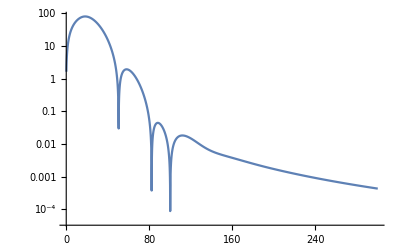

```mathematica
Schwl0data[[;;,2]]= Abs[Schwl0data[[;;,2]]];
ListLogPlot[{Schwl0data},Joined->True,PlotRange->Automatic]
```

lambda = 1(+extra check on Bound.Cond. formulation)

l=1

```mathematica
FDschw[1500,200,1]
```

# of Iterations in space = 1500

(r_*)^max =  100  , r^max =  83.98654919

(r_*)^min =  -100  , r^min =  2.000000000

I_max = 750

I_min = -750

Space Discretization step = 2/15

t_final/M = 200

# of Iterations in time = J_max = 2142

Time Discretization step = 0.0933333

Δt/(Δr_*) = 0.7

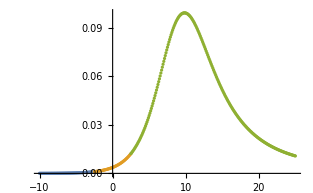

```mathematica
ListPlot[{Table[{i Δrstar  ,Vschw[r[i*Δrstar],1]},{i,-100,-25}],
Table[{i Δrstar  ,Vschw[r[i*Δrstar],1]},{i,-25,25}],
Table[{i Δrstar  ,Vschw[r[i*Δrstar],1]},{i,25,250}]},Joined->False,PlotRange->All]
```

```mathematica
i=-10;
NumberForm[r[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/M,Evaluate[Abs[ψ[i,j]]]},{j,0,2000(*jmax+2000*)}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All] ]
```

2.0051466451803374802

$Aborted

```mathematica
ListAnimate[Table[Block[{$RecursionLimit=Infinity},
ListPlot[{Table[{i Δrstar  ,ψ[i,j]},{i,imin,imax}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ],{j,0,3000,50}]]
```

```mathematica
Schwl1data= Table[{(j Δt)/M ,ψ[i,j]},{j,0,jmax+2000}]  ;
```

```mathematica
Export["Schw_l1M1data1.txt" ,Schwl1data];
Export["Schw_l1M1data2.txt" ,Schwl1data,"Table","FieldSeparators"->" "];
```

```mathematica
Clear[Schwl1data]
```

```mathematica
Schwl1data=Import["Schw_l1M1data2.txt","Table"];
```

```mathematica
FilePrint["Schw_l1M1data1.txt"]
```

{0., E^(-98/5625)}
{0.06533333333333333, 1.9652856265248881}
{0.13066666666666665, 2.9474992420351587}
{0.19599999999999998, 3.9291980208316013}
{0.2613333333333333, 4.910210684825513}
{0.32666666666666666, 5.8903662420112415}
{0.39199999999999996, 6.869494057577301}
{0.45733333333333326, 7.847423924754437}
{0.5226666666666666, 8.823986135346322}
{0.588, 9.799011549852569}
{0.6533333333333333, 10.77233166705221}
{0.7186666666666666, 11.743778692921204}
{0.7839999999999999, 12.71318560882257}
{0.8493333333333333, 13.680386238966102}
{0.9146666666666665, 14.645215317116449}
{0.9799999999999999, 15.60750855246477}
{1.0453333333333332, 16.56710269456522}
{1.1106666666666665, 17.523835597291303}
{1.176, 18.477546281802226}
{1.2413333333333332, 19.428074998473836}
{1.3066666666666666, 20.375263287707853}
{1.3719999999999999, 21.318954039557614}
{1.4373333333333331, 22.25899155215742}
{1.5026666666666666, 23.195221588937684}
{1.5679999999999998, 24.12749143456418}
{1.633333333333333, 25.05564994952762}
{1.6986666666666665, 25.979547623330923}
{1.7639999999999998, 26.899036626223}
{1.829333333333333, 27.813970859417083}
{1.8946666666666665, 28.724206003762426}
{1.9599999999999997, 29.62959956689168}
{2.025333333333333, 30.530010928863422}
{2.0906666666666665, 31.425301386262596}
{2.1559999999999997, 32.31533419470851}
{2.221333333333333, 33.19997460978607}
{2.2866666666666666, 34.07908992647154}
{2.352, 34.952549517094134}
{2.417333333333333, 35.820224867795986}
{2.4826666666666664, 36.68198961338539}
{2.5479999999999996, 37.537719570413024}
{2.6133333333333333, 38.3872927682412}
{2.6786666666666665, 39.230589477908474}
{2.7439999999999998, 40.067492238767436}
{2.809333333333333, 40.897885883074146}
{2.8746666666666663, 41.72165755874445}
{2.9399999999999995, 42.5386967503328}
{3.005333333333333, 43.348895298109746}
{3.0706666666666664, 44.15214741510305}
{3.1359999999999997, 44.94834970212702}
{3.201333333333333, 45.73740116097557}
{3.266666666666666, 46.519203205928385}
{3.332, 47.29365967354959}
{3.397333333333333, 48.06067683065795}
{3.4626666666666663, 48.82016338045226}
{3.5279999999999996, 49.572030466952754}
{3.593333333333333, 50.31619167792249}
{3.658666666666666, 51.05256304625616}
{3.7239999999999998, 51.78106304972891}
{3.789333333333333, 52.501612609129715}
{3.8546666666666662, 53.21413508496459}
{3.9199999999999995, 53.918556272863476}
{3.9853333333333327, 54.61480439765931}
{4.050666666666666, 55.30281010610969}
{4.116, 55.98250645841994}
{4.181333333333333, 56.65382891882756}
{4.246666666666666, 57.316715345387955}
{4.311999999999999, 57.97110597894815}
{4.377333333333333, 58.61694343127054}
{4.442666666666666, 59.25417267223444}
{4.507999999999999, 59.88274101582559}
{4.573333333333333, 60.50259810437781}
{4.6386666666666665, 61.11369589058794}
{4.704, 61.715988617236}
{4.769333333333333, 62.30943279499824}
{4.834666666666666, 62.89398717894037}
{4.8999999999999995, 63.46961274418222}
{4.965333333333333, 64.03627266094145}
{5.030666666666666, 64.59393226881319}
{5.095999999999999, 65.1425590499221}
{5.161333333333332, 65.68212260073096}
{5.226666666666667, 66.21259460276984}
{5.292, 66.73394879290628}
{5.357333333333333, 67.24616093358496}
{5.422666666666666, 67.74920878289643}
{5.4879999999999995, 68.24307206403786}
{5.553333333333333, 68.7277324340492}
{5.618666666666666, 69.20317345224336}
{5.683999999999999, 69.6693805488574}
{5.7493333333333325, 70.12634099403873}
{5.814666666666666, 70.57404386687297}
{5.879999999999999, 71.01248002422162}
{5.945333333333333, 71.44164206954272}
{6.010666666666666, 71.86152432211638}
{6.076, 72.27212278691346}
{6.141333333333333, 72.67343512496316}
{6.206666666666666, 73.06546062394573}
{6.271999999999999, 73.44820016901758}
{6.337333333333333, 73.82165621422115}
{6.402666666666666, 74.18583275477684}
{6.467999999999999, 74.54073530013999}
{6.533333333333332, 74.88637084748306}
{6.598666666666666, 75.22274785556927}
{6.664, 75.54987621939813}
{6.729333333333333, 75.86776724590443}
{6.794666666666666, 76.17643363049379}
{6.859999999999999, 76.47588943404243}
{6.925333333333333, 76.76615006041905}
{6.990666666666666, 77.04723223493248}
{7.055999999999999, 77.31915398380742}
{7.121333333333332, 77.58193461428519}
{7.186666666666666, 77.83559469500354}
{7.251999999999999, 78.08015603679331}
{7.317333333333332, 78.31564167412296}
{7.382666666666666, 78.54207584694011}
{7.4479999999999995, 78.75948398235509}
{7.513333333333333, 78.96789267597255}
{7.578666666666666, 79.16732967318762}
{7.643999999999999, 79.35782385077351}
{7.7093333333333325, 79.53940519883977}
{7.774666666666666, 79.71210480337733}
{7.839999999999999, 79.8759548300407}
{7.905333333333332, 80.03098850982236}
{7.9706666666666655, 80.17724012662906}
{8.036, 80.31474500611746}
{8.101333333333333, 80.44353950507312}
{8.166666666666666, 80.56366100092637}
{8.232, 80.67514788121488}
{8.297333333333333, 80.7780395329231}
{8.362666666666666, 80.87237633192404}
{8.427999999999999, 80.95819963305625}
{8.493333333333332, 81.03555176118033}
{8.558666666666666, 81.10447600285131}
{8.623999999999999, 81.1650165977387}
{8.689333333333332, 81.2172187292308}
{8.754666666666665, 81.26112851444528}
{8.819999999999999, 81.29679299426054}
{8.885333333333332, 81.32426012365795}
{8.950666666666665, 81.34357876213105}
{9.015999999999998, 81.35479866372299}
{9.081333333333333, 81.35797046638505}
{9.146666666666667, 81.35314568055118}
{9.212, 81.34037667706167}
{9.277333333333333, 81.3197166748023}
{9.342666666666666, 81.29121972832617}
{9.408, 81.25494071517855}
{9.473333333333333, 81.21093532225832}
{9.538666666666666, 81.15926003096888}
{9.604, 81.09997210172104}
{9.669333333333332, 81.03312955844521}
{9.734666666666666, 80.95879117296323}
{9.799999999999999, 80.87701644847586}
{9.865333333333332, 80.78786560186094}
{9.930666666666665, 80.69139954527562}
{9.995999999999999, 80.58767986761139}
{10.061333333333332, 80.47676881572959}
{10.126666666666665, 80.35872927505636}
{10.191999999999998, 80.23362474938233}
{10.257333333333332, 80.10151934005847}
{10.322666666666665, 79.96247772481836}
{10.387999999999998, 79.81656513635986}
{10.453333333333333, 79.66384734071647}
{10.518666666666666, 79.50439061526369}
{10.584, 79.33826172613679}
{10.649333333333333, 79.16552790517055}
{10.714666666666666, 78.9862568268497}
{10.78, 78.80051658550843}
{10.845333333333333, 78.60837567236698}
{10.910666666666666, 78.40990295196791}
{10.975999999999999, 78.20516763833716}
{11.041333333333332, 77.99423927158271}
{11.106666666666666, 77.77718769498203}
{11.171999999999999, 77.55408303190723}
{11.237333333333332, 77.32499566232416}
{11.302666666666665, 77.08999619946789}
{11.367999999999999, 76.84915546726259}
{11.433333333333332, 76.60254447820682}
{11.498666666666665, 76.35023441114915}
{11.563999999999998, 76.09229658904228}
{11.629333333333332, 75.82880245727526}
{11.694666666666665, 75.55982356278605}
{11.759999999999998, 75.28543153357519}
{11.825333333333331, 75.00569805835788}
{11.890666666666666, 74.72069486659483}
{11.956, 74.43049370923103}
{12.021333333333333, 74.13516634013205}
{12.086666666666666, 73.83478449801186}
{12.152, 73.52941988878098}
{12.217333333333332, 73.21914416841862}
{12.282666666666666, 72.9040289265078}
{12.347999999999999, 72.58414567050815}
{12.413333333333332, 72.25956581070857}
{12.478666666666665, 71.93036064570794}
{12.543999999999999, 71.5966013484095}
{12.609333333333332, 71.25835895276998}
{12.674666666666665, 70.9157043414894}
{12.739999999999998, 70.56870823444244}
{12.805333333333332, 70.21744117754264}
{12.870666666666665, 69.86197353214926}
{12.935999999999998, 69.50237546540968}
{13.001333333333331, 69.13871694154166}
{13.066666666666665, 68.77106771360197}
{13.131999999999998, 68.39949731556804}
{13.197333333333331, 68.02407505515836}
{13.262666666666666, 67.64487000771094}
{13.328, 67.26195101076429}
{13.393333333333333, 66.87538665887686}
{13.458666666666666, 66.48524529887719}
{13.524, 66.09159502604238}
{13.589333333333332, 65.69450368112388}
{13.654666666666666, 65.29403884766607}
{13.719999999999999, 64.89026784951041}
{13.785333333333332, 64.48325774897924}
{13.850666666666665, 64.07307534595881}
{13.915999999999999, 63.65978717742324}
{13.981333333333332, 63.243459517012425}
{14.046666666666665, 62.8241583749536}
{14.111999999999998, 62.40194949874106}
{14.177333333333332, 61.976898374380205}
{14.242666666666665, 61.549070227716705}
{14.307999999999998, 61.118530025867}
{14.373333333333331, 60.68534247916271}
{14.438666666666665, 60.249572043661466}
{14.503999999999998, 59.811282923811646}
{14.569333333333331, 59.37053907507348}
{14.634666666666664, 58.9274042067908}
{14.7, 58.48194178554249}
{14.765333333333333, 58.03421503872963}
{14.830666666666666, 57.58428695808104}
{14.895999999999999, 57.132220303169206}
{14.961333333333332, 56.678077605213375}
{15.026666666666666, 56.22192117113802}
{15.091999999999999, 55.76381308760243}
{15.157333333333332, 55.30381522491194}
{15.222666666666665, 54.841989240998195}
{15.287999999999998, 54.37839658557155}
{15.353333333333332, 53.913098504288314}
{15.418666666666665, 53.44615604276691}
{15.483999999999998, 52.97763005050833}
{15.549333333333331, 52.507581184858275}
{15.614666666666665, 52.036069914987024}
{15.679999999999998, 51.56315652573088}
{15.745333333333331, 51.088901121229966}
{15.810666666666664, 50.61336362846062}
{15.875999999999998, 50.13660380075003}
{15.941333333333331, 49.65868122119545}
{16.006666666666664, 49.17965530584008}
{16.072, 48.69958530659955}
{16.13733333333333, 48.2185303140792}
{16.202666666666666, 47.736549260333966}
{16.267999999999997, 47.25370092142086}
{16.333333333333332, 46.77004391960921}
{16.398666666666664, 46.28563672534957}
{16.464, 45.80053765917286}
{16.52933333333333, 45.31480489345421}
{16.594666666666665, 44.82849645382005}
{16.659999999999997, 44.341670220191325}
{16.72533333333333, 43.8543839276905}
{16.790666666666667, 43.36669516747385}
{16.855999999999998, 42.87866138725218}
{16.921333333333333, 42.39033989136755}
{16.986666666666665, 41.901787840640395}
{17.052, 41.41306225217304}
{17.11733333333333, 40.924219998919}
{17.182666666666666, 40.43531780877485}
{17.247999999999998, 39.94641226334157}
{17.313333333333333, 39.457559796642684}
{17.378666666666664, 38.96881669370253}
{17.444, 38.480239088660944}
{17.50933333333333, 37.99188296246021}
{17.574666666666666, 37.50380414045342}
{17.639999999999997, 37.016058289969614}
{17.705333333333332, 36.52870091747967}
{17.770666666666664, 36.04178736525851}
{17.836, 35.55537280789658}
{17.90133333333333, 35.069512248843196}
{17.966666666666665, 34.58426051665799}
{18.031999999999996, 34.09967226072599}
{18.09733333333333, 33.61580194672708}
{18.162666666666667, 33.132703852171616}
{18.227999999999998, 32.65043206177121}
{18.293333333333333, 32.16904046229346}
{18.358666666666664, 31.688582737078576}
{18.424, 31.209112360612693}
{18.48933333333333, 30.73068259305708}
{18.554666666666666, 30.25334647432831}
{18.619999999999997, 29.77715681777099}
{18.685333333333332, 29.30216620384548}
{18.750666666666664, 28.828426973869234}
{18.816, 28.35599122340664}
{18.88133333333333, 27.884910795214502}
{18.946666666666665, 27.41523727214333}
{19.011999999999997, 26.9470219701611}
{19.077333333333332, 26.480315931138517}
{19.142666666666663, 26.015169915186068}
{19.208, 25.55163439288168}
{19.27333333333333, 25.089759537661255}
{19.338666666666665, 24.629595218088877}
{19.403999999999996, 24.171190989706236}
{19.46933333333333, 23.71459608670939}
{19.534666666666666, 23.25985941380055}
{19.599999999999998, 22.807029538034026}
{19.665333333333333, 22.356154680298157}
{19.730666666666664, 21.907282706571415}
{19.796, 21.460461119339218}
{19.86133333333333, 21.01573704910616}
{19.926666666666666, 20.573157245626803}
{19.991999999999997, 20.132768068876153}
{20.057333333333332, 19.694615480145025}
{20.122666666666664, 19.2587450333093}
{20.188, 18.825201865917688}
{20.25333333333333, 18.39403069001104}
{20.318666666666665, 17.965275783018665}
{20.383999999999997, 17.53898097887886}
{20.449333333333332, 17.115189659083523}
{20.514666666666663, 16.69394474347437}
{20.58, 16.27528868106786}
{20.64533333333333, 15.859263441126332}
{20.710666666666665, 15.445910504252675}
{20.775999999999996, 15.03527085328174}
{20.84133333333333, 14.627384964161925}
{20.906666666666666, 14.222292797081861}
{20.971999999999998, 13.820033787704928}
{21.037333333333333, 13.420646838262902}
{21.102666666666664, 13.02417030861729}
{21.168, 12.63064200754967}
{21.23333333333333, 12.240099184224794}
{21.298666666666666, 11.852578519584041}
{21.363999999999997, 11.468116117701582}
{21.429333333333332, 11.086747497346227}
{21.494666666666664, 10.708507583761108}
{21.56, 10.333430700446259}
{21.62533333333333, 9.961550560915581}
{21.690666666666665, 9.592900260635039}
{21.755999999999997, 9.227512269205645}
{21.82133333333333, 8.865418422617598}
{21.886666666666663, 8.506649915504}
{21.951999999999998, 8.151237293554841}
{22.01733333333333, 7.799210446187742}
{22.082666666666665, 7.450598599350033}
{22.147999999999996, 7.1054303083559125}
{22.21333333333333, 6.763733450868738}
{22.278666666666663, 6.425535220139945}
{22.343999999999998, 6.0908621184291984}
{22.409333333333333, 5.759739950502375}
{22.474666666666664, 5.432193817267431}
{22.54, 5.10824810965739}
{22.60533333333333, 4.787926502732105}
{22.670666666666666, 4.471251949904776}
{22.735999999999997, 4.158246677308558}
{22.801333333333332, 3.848932178394735}
{22.866666666666664, 3.543329208773402}
{22.932, 3.2414577812261713}
{22.99733333333333, 2.9433371608713768}
{23.062666666666665, 2.6489858605430525}
{23.127999999999997, 2.3584216364222224}
{23.19333333333333, 2.071661483883866}
{23.258666666666663, 1.788721633518462}
{23.323999999999998, 1.5096175473509654}
{23.38933333333333, 1.2343639153088213}
{23.454666666666665, 0.9629746519420275}
{23.519999999999996, 0.6954628933480287}
{23.58533333333333, 0.431840994282749}
{23.650666666666663, 0.17212052550633866}
{23.715999999999998, -0.08368772859338594}
{23.781333333333333, -0.33557377213707595}
{23.846666666666664, -0.5835283997072327}
{23.912, -0.8275431980887772}
{23.97733333333333, -1.0676105477192146}
{24.042666666666666, -1.3037236238613419}
{24.107999999999997, -1.5358763975873289}
{24.173333333333332, -1.7640636365754157}
{24.238666666666663, -1.9882809056169548}
{24.304, -2.208524566811562}
{24.36933333333333, -2.4247917795587566}
{24.434666666666665, -2.6370805003873516}
{24.499999999999996, -2.845389482508498}
{24.56533333333333, -3.049718275028499}
{24.630666666666663, -3.2500672219356135}
{24.695999999999998, -3.446437460946282}
{24.76133333333333, -3.638830922098973}
{24.826666666666664, -3.8272503259882367}
{24.891999999999996, -4.011699181744813}
{24.95733333333333, -4.192181784891094}
{25.022666666666662, -4.368703214976402}
{25.087999999999997, -4.541269332843592}
{25.153333333333332, -4.70988677761095}
{25.218666666666664, -4.874562963537946}
{25.284, -5.0353060767081566}
{25.34933333333333, -5.192125071346202}
{25.414666666666665, -5.345029665819582}
{25.479999999999997, -5.494030338525247}
{25.545333333333332, -5.6391383236328405}
{25.610666666666663, -5.780365606475832}
{25.676, -5.917724918599859}
{25.74133333333333, -6.0512297326895235}
{25.806666666666665, -6.180894257391184}
{25.871999999999996, -6.306733431807924}
{25.93733333333333, -6.42876291962891}
{26.002666666666663, -6.546999103124658}
{26.067999999999998, -6.6614590770753095}
{26.13333333333333, -6.77216064240447}
{26.198666666666664, -6.879122299431102}
{26.263999999999996, -6.982363240969738}
{26.32933333333333, -7.081903345396933}
{26.394666666666662, -7.177763169464292}
{26.459999999999997, -7.269963940720784}
{26.525333333333332, -7.35852754976194}
{26.590666666666664, -7.443476542473589}
{26.656, -7.524834112069378}
{26.72133333333333, -7.60262409073729}
{26.786666666666665, -7.676870941089145}
{26.851999999999997, -7.747599747626852}
{26.917333333333332, -7.8148362080541185}
{26.982666666666663, -7.878606624205994}
{27.048, -7.938937892756554}
{27.11333333333333, -7.995857495958899}
{27.178666666666665, -8.049393492284938}
{27.243999999999996, -8.099574506701114}
{27.30933333333333, -8.146429720698034}
{27.374666666666663, -8.189988862360968}
{27.439999999999998, -8.23028219639534}
{27.50533333333333, -8.267340513815572}
{27.570666666666664, -8.301195121365707}
{27.635999999999996, -8.331877830982236}
{27.70133333333333, -8.359420949266077}
{27.766666666666662, -8.383857266654198}
{27.831999999999997, -8.405220046304823}
{27.897333333333332, -8.42354301301945}
{27.962666666666664, -8.438860342225194}
{28.028, -8.451206648700994}
{28.09333333333333, -8.46061697500431}
{28.158666666666665, -8.467126779923252}
{28.223999999999997, -8.470771927035809}
{28.28933333333333, -8.471588673064042}
{28.354666666666663, -8.46961365592202}
{28.419999999999998, -8.46488388277269}
{28.48533333333333, -8.45743671823272}
{28.550666666666665, -8.44730987242879}
{28.615999999999996, -8.434541388748324}
{28.68133333333333, -8.419169631578816}
{28.746666666666663, -8.401233274228819}
{28.811999999999998, -8.380771286760712}
{28.87733333333333, -8.357822923526623}
{28.942666666666664, -8.332427710670215}
{29.007999999999996, -8.304625433836126}
{29.07333333333333, -8.27445612585328}
{29.138666666666662, -8.241960054138316}
{29.203999999999997, -8.207177708041387}
{29.26933333333333, -8.170149786417449}
{29.334666666666664, -8.13091718523349}
{29.4, -8.08952098492089}
{29.46533333333333, -8.04600243764742}
{29.530666666666665, -8.000402954824473}
{29.595999999999997, -7.952764094710604}
{29.66133333333333, -7.903127549792749}
{29.726666666666663, -7.851535134066441}
{29.791999999999998, -7.798028770553256}
{29.85733333333333, -7.742650478971492}
{29.922666666666665, -7.685442363223826}
{29.987999999999996, -7.6264465987668375}
{30.05333333333333, -7.56570542021272}
{30.118666666666662, -7.503261109136262}
{30.183999999999997, -7.439155981743624}
{30.24933333333333, -7.373432376410234}
{30.314666666666664, -7.306132641439857}
{30.379999999999995, -7.237299123074974}
{30.44533333333333, -7.1669741534181535}
{30.510666666666662, -7.095200038214948}
{30.575999999999997, -7.022019044841874}
{30.64133333333333, -6.9474733905848}
{30.706666666666663, -6.87160523088045}
{30.772, -6.794456647417643}
{30.83733333333333, -6.716069636423796}
{30.902666666666665, -6.636486097273397}
{30.967999999999996, -6.555747821112988}
{31.03333333333333, -6.473896479349893}
{31.098666666666663, -6.390973612304029}
{31.163999999999998, -6.3070206182057245}
{31.22933333333333, -6.222078742263435}
{31.294666666666664, -6.136189065604738}
{31.359999999999996, -6.049392494356693}
{31.42533333333333, -5.961729749088657}
{31.490666666666662, -5.873241354377265}
{31.555999999999997, -5.783967628259729}
{31.62133333333333, -5.693948671802479}
{31.686666666666664, -5.603224359041134}
{31.751999999999995, -5.5118343270922825}
{31.81733333333333, -5.419817966173557}
{31.882666666666662, -5.327214409715761}
{31.947999999999997, -5.234062524848409}
{32.01333333333333, -5.140400903103203}
{32.07866666666666, -5.046267851049841}
{32.144, -4.951701381001938}
{32.20933333333333, -4.85673920209206}
{32.27466666666666, -4.761418711606672}
{32.339999999999996, -4.665776986281035}
{32.40533333333333, -4.569850773644255}
{32.470666666666666, -4.473676483723235}
{32.535999999999994, -4.377290181043519}
{32.60133333333333, -4.280727576620598}
{32.666666666666664, -4.18402401998414}
{32.732, -4.087214491545761}
{32.79733333333333, -3.990333595294974}
{32.86266666666666, -3.8934155515179736}
{32.928, -3.7964941895352764}
{32.99333333333333, -3.699602940763452}
{33.05866666666666, -3.6027748321303448}
{33.123999999999995, -3.5060424795464673}
{33.18933333333333, -3.4094380813843204}
{33.254666666666665, -3.3129934122589506}
{33.31999999999999, -3.216739817181314}
{33.38533333333333, -3.1207082058014928}
{33.45066666666666, -3.0249290466522707}
{33.516, -2.9294323616683595}
{33.58133333333333, -2.834247721091472}
{33.64666666666666, -2.7394042384983996}
{33.711999999999996, -2.644930565825365}
{33.77733333333333, -2.5508548886406217}
{33.842666666666666, -2.45720492180984}
{33.907999999999994, -2.364007905316335}
{33.97333333333333, -2.2712906000767523}
{34.038666666666664, -2.1790792839764657}
{34.104, -2.0873997482987474}
{34.16933333333333, -1.996277294338738}
{34.23466666666666, -1.9057367300152237}
{34.3, -1.8158023666731775}
{34.36533333333333, -1.7264980162753343}
{34.43066666666666, -1.637846988805938}
{34.495999999999995, -1.5498720896775966}
{34.56133333333333, -1.4625956173002441}
{34.626666666666665, -1.3760393610290633}
{34.69199999999999, -1.290224599348764}
{34.75733333333333, -1.2051720980688319}
{34.82266666666666, -1.1209021086532052}
{34.888, -1.0374343669140793}
{34.95333333333333, -0.9547880919625962}
{35.01866666666666, -0.8729819851803959}
{35.083999999999996, -0.7920342292993161}
{35.14933333333333, -0.7119624878262464}
{35.214666666666666, -0.6327839047415574}
{35.279999999999994, -0.5545151042299099}
{35.34533333333333, -0.47717219049459714}
{35.410666666666664, -0.4007707478943818}
{35.476, -0.3253258413665867}
{35.54133333333333, -0.25085201689544795}
{35.60666666666666, -0.17736330204145004}
{35.672, -0.10487320676720482}
{35.73733333333333, -0.03339472455790096}
{35.80266666666666, 0.0370596663990968}
{35.867999999999995, 0.10647800199357174}
{35.93333333333333, 0.17484883070373955}
{35.998666666666665, 0.24216121180936953}
{36.06399999999999, 0.3084047135316751}
{36.12933333333333, 0.37356941114914444}
{36.19466666666666, 0.43764588487534684}
{36.26, 0.5006252174394199}
{36.32533333333333, 0.5624989915796963}
{36.39066666666666, 0.6232592875276816}
{36.455999999999996, 0.6828986802850704}
{36.52133333333333, 0.7414102366084334}
{36.586666666666666, 0.7987875118940153}
{36.651999999999994, 0.855024547064535}
{36.71733333333333, 0.9101158652806463}
{36.782666666666664, 0.964056468369254}
{36.848, 1.01684183314005}
{36.91333333333333, 1.0684679077128516}
{36.97866666666666, 1.1189311077009532}
{37.044, 1.168228312124388}
{37.10933333333333, 1.2163568592012528}
{37.17466666666666, 1.2633145421561252}
{37.239999999999995, 1.3090996049149943}
{37.30533333333333, 1.3537107375464716}
{37.370666666666665, 1.3971470715728371}
{37.43599999999999, 1.439408175302216}
{37.50133333333333, 1.4804940490765384}
{37.56666666666666, 1.5204051202850728}
{37.632, 1.5591422382417686}
{37.69733333333333, 1.596706669085772}
{37.76266666666666, 1.6331000906253708}
{37.827999999999996, 1.6683245869692653}
{37.89333333333333, 1.7023826430179285}
{37.958666666666666, 1.735277138978397}
{38.023999999999994, 1.7670113448481815}
{38.08933333333333, 1.7975889147103503}
{38.154666666666664, 1.827013880887559}
{38.22, 1.8552906481183042}
{38.28533333333333, 1.8824239877255609}
{38.35066666666666, 1.9084190316218477}
{38.416, 1.9332812661747918}
{38.48133333333333, 1.9570165260927992}
{38.54666666666666, 1.979630988323915}
{38.611999999999995, 2.0011311658171618}
{38.67733333333333, 2.0215239011483686}
{38.742666666666665, 2.0408163601633222}
{38.80799999999999, 2.0590160256524435}
{38.87333333333333, 2.0761306909145003}
{38.93866666666666, 2.0921684531912734}
{39.004, 2.107137707116332}
{39.06933333333333, 2.121047138210945}
{39.13466666666666, 2.1339057162954598}
{39.199999999999996, 2.1457226887804643}
{39.26533333333333, 2.1565075739689483}
{39.330666666666666, 2.1662701544186787}
{39.395999999999994, 2.175020470245856}
{39.46133333333333, 2.182768812319368}
{39.526666666666664, 2.1895257154631946}
{39.592, 2.195301951729715}
{39.65733333333333, 2.200108523639243}
{39.72266666666666, 2.2039566573227414}
{39.788, 2.20685779567023}
{39.85333333333333, 2.2088235915584082}
{39.91866666666666, 2.2098659010682633}
{39.983999999999995, 2.2099967766201245}
{40.04933333333333, 2.2092284601126244}
{40.114666666666665, 2.2075733761468883}
{40.17999999999999, 2.2050441252627624}
{40.24533333333333, 2.2016534771080525}
{40.31066666666666, 2.1974143636108874}
{40.376, 2.1923398722413783}
{40.44133333333333, 2.186443239305465}
{40.50666666666666, 2.179737843188217}
{40.571999999999996, 2.172237197600497}
{40.63733333333333, 2.163954944917213}
{40.702666666666666, 2.1549048495657783}
{40.767999999999994, 2.1451007913810702}
{40.83333333333333, 2.1345567589651835}
{40.898666666666664, 2.1232868431396943}
{40.964, 2.1113052304638655}
{41.02933333333333, 2.0986261967364563}
{41.09466666666666, 2.085264100504866}
{41.16, 2.071233376666599}
{41.22533333333333, 2.0565485301501973}
{41.29066666666666, 2.0412241295966966}
{41.355999999999995, 2.0252748010519723}
{41.42133333333333, 2.0087152217503084}
{41.486666666666665, 1.9915601139887513}
{41.55199999999999, 1.973824239018506}
{41.61733333333333, 1.9555223909517159}
{41.68266666666666, 1.9366693907576265}
{41.748, 1.917280080358581}
{41.81333333333333, 1.8973693167588859}
{41.87866666666666, 1.8769519661944813}
{41.943999999999996, 1.8560428983696595}
{42.00933333333333, 1.834656980800521}
{42.074666666666666, 1.8128090732062332}
{42.13999999999999, 1.7905140219273177}
{42.20533333333333, 1.767786654428261}
{42.27066666666666, 1.744641773911566}
{42.336, 1.7210941539934013}
{42.401333333333326, 1.6971585334133144}
{42.46666666666666, 1.672849610825501}
{42.532, 1.6481820397041334}
{42.59733333333333, 1.6231704233226165}
{42.66266666666666, 1.5978293097745488}
{42.727999999999994, 1.5721731870736795}
{42.79333333333333, 1.5462164783686834}
{42.858666666666664, 1.519973537242486}
{42.92399999999999, 1.4934586430612178}
{42.98933333333333, 1.4666859963999543}
{43.05466666666666, 1.439669714582514}
{43.12, 1.412423827314735}
{43.185333333333325, 1.3849622723753992}
{43.25066666666666, 1.3572988913820638}
{43.315999999999995, 1.3294474256687652}
{43.38133333333333, 1.3014215122643475}
{43.446666666666665, 1.2732346799364094}
{43.51199999999999, 1.2449003453087535}
{43.57733333333333, 1.216431809087358}
{43.64266666666666, 1.1878422523922998}
{43.708, 1.159144733162962}
{43.773333333333326, 1.1303521826358032}
{43.83866666666666, 1.101477401926322}
{43.903999999999996, 1.0725330587205535}
{43.96933333333333, 1.0435316840471418}
{44.03466666666666, 1.0144856691215072}
{44.099999999999994, 0.9854072622890505}
{44.16533333333333, 0.9563085660796447}
{44.230666666666664, 0.9272015343494516}
{44.29599999999999, 0.898097969494908}
{44.36133333333333, 0.8690095197599842}
{44.42666666666666, 0.8399476766547356}
{44.492, 0.8109237724672407}
{44.557333333333325, 0.7819489778483303}
{44.62266666666666, 0.7530342994833994}
{44.687999999999995, 0.7241905778737688}
{44.75333333333333, 0.6954284852166246}
{44.818666666666665, 0.666758523358945}
{44.88399999999999, 0.6381910218321651}
{44.94933333333333, 0.6097361359929908}
{45.01466666666666, 0.581403845266885}
{45.08, 0.5532039514672096}
{45.145333333333326, 0.5251460771888846}
{45.21066666666666, 0.49723966430338984}
{45.275999999999996, 0.4694939725593068}
{45.34133333333333, 0.4419180782604272}
{45.40666666666666, 0.4145208730123421}
{45.471999999999994, 0.3873110625643694}
{45.53733333333333, 0.3602971657587409}
{45.602666666666664, 0.33348751355949213}
{45.66799999999999, 0.3068902481440468}
{45.73333333333333, 0.2805133220829941}
{45.79866666666666, 0.2543644976275983}
{45.864, 0.22845134607933784}
{45.929333333333325, 0.2027812472167781}
{45.99466666666666, 0.17736138880250643}
{46.059999999999995, 0.1521987661969343}
{46.12533333333333, 0.12730018205652513}
{46.190666666666665, 0.10267224608458811}
{46.25599999999999, 0.07832137485327745}
{46.32133333333333, 0.05425379173024171}
{46.38666666666666, 0.030475526891975933}
{46.452, 0.006992417385549617}
{46.517333333333326, -0.016189892747881303}
{46.58266666666666, -0.03906595224840887}
{46.647999999999996, -0.061630502323864605}
{46.71333333333333, -0.08387847629144185}
{46.77866666666666, -0.10580499916735658}
{46.843999999999994, -0.1274053871601556}
{46.90933333333333, -0.14867514707331975}
{46.974666666666664, -0.1696099756657884}
{47.03999999999999, -0.19020575897057182}
{47.10533333333333, -0.21045857152309033}
{47.17066666666666, -0.23036467549731468}
{47.236, -0.24992051980180108}
{47.301333333333325, -0.26912273914382834}
{47.36666666666666, -0.2879681530105566}
{47.431999999999995, -0.3064537645570665}
{47.49733333333333, -0.32457675945555864}
{47.562666666666665, -0.3423345047224845}
{47.62799999999999, -0.35972454747107047}
{47.69333333333333, -0.3767446135703741}
{47.75866666666666, -0.39339260626598466}
{47.824, -0.40966660478808403}
{47.889333333333326, -0.42556486289429224}
{47.95466666666666, -0.4410858073195087}
{48.019999999999996, -0.45622803618727803}
{48.08533333333333, -0.47099031741738184}
{48.15066666666666, -0.4853715870783458}
{48.215999999999994, -0.49937094764812867}
{48.28133333333333, -0.5129876662356595}
{48.346666666666664, -0.5262211728068906}
{48.41199999999999, -0.5390710583666105}
{48.47733333333333, -0.5515370730504007}
{48.54266666666666, -0.5636191241761948}
{48.608, -0.5753172743079078}
{48.673333333333325, -0.5866317392862841}
{48.73866666666666, -0.5975628861727069}
{48.803999999999995, -0.6081112311508469}
{48.86933333333333, -0.6182774374470399}
{48.934666666666665, -0.6280623132297918}
{48.99999999999999, -0.6374668094260034}
{49.06533333333333, -0.6464920174928999}
{49.13066666666666, -0.6551391672143703}
{49.196, -0.6634096244885986}
{49.261333333333326, -0.6713048890370813}
{49.32666666666666, -0.6788265920669021}
{49.391999999999996, -0.6859764939620603}
{49.45733333333333, -0.6927564819784081}
{49.52266666666666, -0.6991685678656098}
{49.587999999999994, -0.7052148854397072}
{49.65333333333333, -0.7108976881882314}
{49.718666666666664, -0.7162193468911644}
{49.78399999999999, -0.7211823471755078}
{49.84933333333333, -0.7257892870177649}
{49.91466666666666, -0.7300428742813388}
{49.98, -0.7339459242818208}
{50.045333333333325, -0.7375013572933542}
{50.11066666666666, -0.740712196000197}
{50.175999999999995, -0.7435815629843595}
{50.24133333333333, -0.7461126782528303}
{50.306666666666665, -0.7483088567143227}
{50.37199999999999, -0.7501735055986994}
{50.43733333333333, -0.7517101219123838}
{50.50266666666666, -0.752922289944419}
{50.568, -0.7538136787313261}
{50.633333333333326, -0.7543880394624934}
{50.69866666666666, -0.7546492029203719}
{50.763999999999996, -0.7546010769816098}
{50.82933333333333, -0.7542476440869273}
{50.89466666666666, -0.7535929586497531}
{50.959999999999994, -0.7526411444974376}
{51.02533333333333, -0.7513963923829133}
{51.090666666666664, -0.7498629574757337}
{51.15599999999999, -0.7480451567906041}
{51.22133333333333, -0.7459473666451442}
{51.28666666666666, -0.7435740201965015}
{51.352, -0.7409296049685161}
{51.417333333333325, -0.7380186603158396}
{51.48266666666666, -0.7348457749131501}
{51.547999999999995, -0.731415584330491}
{51.61333333333333, -0.7277327686105879}
{51.678666666666665, -0.7238020497831659}
{51.74399999999999, -0.7196281893994588}
{51.80933333333333, -0.715215986159059}
{51.87466666666666, -0.7105702735504908}
{51.94, -0.7056959174294757}
{52.005333333333326, -0.7005978136116683}
{52.07066666666666, -0.6952808855626881}
{52.135999999999996, -0.6897500821138808}
{52.20133333333333, -0.6840103751173383}
{52.26666666666666, -0.6780667571090436}
{52.331999999999994, -0.6719242390728217}
{52.39733333333333, -0.6655878482419553}
{52.462666666666664, -0.6590626258424802}
{52.52799999999999, -0.6523536248379019}
{52.59333333333333, -0.645465907776939}
{52.65866666666666, -0.6384045446907147}
{52.724, -0.6311746109348091}
{52.789333333333325, -0.6237811850256325}
{52.85466666666666, -0.6162293465806903}
{52.919999999999995, -0.6085241743198649}
{52.98533333333333, -0.6006707440155906}
{53.050666666666665, -0.5926741264300246}
{53.11599999999999, -0.5845393853556098}
{53.18133333333333, -0.5762715757278878}
{53.24666666666666, -0.5678757416920687}
{53.312, -0.5593569146490756}
{53.377333333333326, -0.550720111403033}
{53.44266666666666, -0.5419703323918094}
{53.507999999999996, -0.5331125598771631}
{53.57333333333333, -0.5241517561068989}
{53.63866666666666, -0.5150928615750268}
{53.70399999999999, -0.5059407933750393}
{53.76933333333333, -0.4967004435195194}
{53.834666666666664, -0.4873766772245931}
{53.89999999999999, -0.4779743312876191}
{53.96533333333333, -0.4684982125672148}
{54.03066666666666, -0.45895309643709226}
{54.096, -0.4493437251979268}
{54.161333333333324, -0.4396748065764355}
{54.22666666666666, -0.42995101233506394}
{54.291999999999994, -0.4201769768637035}
{54.35733333333333, -0.41035729572315915}
{54.422666666666665, -0.40049652426861904}
{54.48799999999999, -0.3905991763908921}
{54.55333333333333, -0.3806697232484845}
{54.61866666666666, -0.37071259194582257}
{54.684, -0.3607321642833061}
{54.749333333333325, -0.3507327756311459}
{54.81466666666666, -0.34071871380324686}
{54.879999999999995, -0.3306942178722364}
{54.94533333333333, -0.32066347704725556}
{55.01066666666666, -0.3106306296804778}
{55.07599999999999, -0.3005997622833913}
{55.14133333333333, -0.2905749084799717}
{55.20666666666666, -0.2805600480126184}
{55.27199999999999, -0.27055910588041676}
{55.337333333333326, -0.2605759514972102}
{55.40266666666666, -0.25061439778325023}
{55.467999999999996, -0.24067820029901058}
{55.533333333333324, -0.2307710565136334}
{55.59866666666666, -0.22089660510337694}
{55.663999999999994, -0.21105842518115717}
{55.72933333333333, -0.20126003555708588}
{55.794666666666664, -0.1915048941346987}
{55.85999999999999, -0.181796397347545}
{55.92533333333333, -0.17213787952529455}
{55.99066666666666, -0.1625326122791301}
{56.056, -0.15298380402254158}
{56.121333333333325, -0.14349459954300298}
{56.18666666666666, -0.13406807950268676}
{56.251999999999995, -0.12470725994632922}
{56.31733333333333, -0.11541509194265016}
{56.38266666666666, -0.1061944612870786}
{56.44799999999999, -0.09704818813428068}
{56.51333333333333, -0.08797902662565274}
{56.57866666666666, -0.07898966464703952}
{56.64399999999999, -0.07008272365782753}
{56.709333333333326, -0.061260758451698566}
{56.77466666666666, -0.05252625690024081}
{56.839999999999996, -0.043881639822083075}
{56.905333333333324, -0.035329260933069616}
{56.97066666666666, -0.02687140673105931}
{57.035999999999994, -0.01851029635168823}
{57.10133333333333, -0.010248081543598738}
{57.166666666666664, -0.002086846733824201}
{57.23199999999999, 0.005971390968170672}
{57.29733333333333, 0.01392468180701709}
{57.36266666666666, 0.021771143305834288}
{57.428, 0.029508960091990156}
{57.493333333333325, 0.037136383779129666}
{57.55866666666666, 0.04465173290081248}
{57.623999999999995, 0.05205339274059234}
{57.68933333333333, 0.05933981505576546}
{57.75466666666666, 0.06650951785128356}
{57.81999999999999, 0.07356108521562976}
{57.88533333333333, 0.0804931670628621}
{57.95066666666666, 0.08730447876157271}
{58.01599999999999, 0.09399380080700404}
{58.081333333333326, 0.10055997856463067}
{58.14666666666666, 0.10700192193059604}
{58.211999999999996, 0.11331860487332639}
{58.277333333333324, 0.1195090650105379}
{58.34266666666666, 0.1255724032663208}
{58.407999999999994, 0.13150778345661454}
{58.47333333333333, 0.13731443175116317}
{58.53866666666666, 0.14299163616238422}
{58.60399999999999, 0.1485387461219162}
{58.66933333333333, 0.1539551719978385}
{58.73466666666666, 0.15924038448483382}
{58.8, 0.16439391401221978}
{58.865333333333325, 0.16941535024614957}
{58.93066666666666, 0.174304341545288}
{58.995999999999995, 0.1790605942870327}
{59.06133333333333, 0.1836838722021607}
{59.12666666666666, 0.18817399580910163}
{59.19199999999999, 0.19253084181494615}
{59.25733333333333, 0.1967543423856795}
{59.32266666666666, 0.20084448441494174}
{59.38799999999999, 0.2048013088967259}
{59.453333333333326, 0.20862491027848287}
{59.51866666666666, 0.21231543568335026}
{59.583999999999996, 0.21587308412070827}
{59.649333333333324, 0.21929810580378134}
{59.71466666666666, 0.22259080146156196}
{59.779999999999994, 0.22575152152093303}
{59.84533333333333, 0.2287806652666485}
{59.91066666666666, 0.2316786801102099}
{59.97599999999999, 0.2344460608672005}
{60.04133333333333, 0.2370833489072253}
{60.10666666666666, 0.2395911312710834}
{60.172, 0.24197003989722393}
{60.237333333333325, 0.24422075087072972}
{60.30266666666666, 0.24634398354872383}
{60.367999999999995, 0.248340499642567}
{60.43333333333333, 0.2502111024083326}
{60.49866666666666, 0.25195663587350436}
{60.56399999999999, 0.2535779839451008}
{60.62933333333333, 0.2550760694644649}
{60.69466666666666, 0.25645185336816245}
{60.75999999999999, 0.2577063338984571}
{60.825333333333326, 0.2588405457012947}
{60.89066666666666, 0.2598555588610158}
{60.955999999999996, 0.2607524780377101}
{61.021333333333324, 0.2615324416671387}
{61.08666666666666, 0.26219662105553854}
{61.151999999999994, 0.26274621940166143}
{61.21733333333333, 0.26318247091659086}
{61.28266666666666, 0.26350664001837215}
{61.34799999999999, 0.2637200204300532}
{61.41333333333333, 0.2638239341961601}
{61.47866666666666, 0.2638197307909152}
{61.544, 0.2637087863126676}
{61.609333333333325, 0.2634925025912559}
{61.67466666666666, 0.2631723062057652}
{61.739999999999995, 0.26274964758689734}
{61.80533333333333, 0.2622260002159607}
{61.87066666666666, 0.2616028597471401}
{61.93599999999999, 0.2608817430329673}
{62.00133333333333, 0.2600641872263995}
{62.06666666666666, 0.259151748988996}
{62.13199999999999, 0.258146003633461}
{62.197333333333326, 0.25704854416294787}
{62.26266666666666, 0.25586098037797717}
{62.327999999999996, 0.25458493809787935}
{62.393333333333324, 0.25322205832848954}
{62.45866666666666, 0.2517739963211949}
{62.523999999999994, 0.2502424206897687}
{62.58933333333333, 0.24862901264890486}
{62.65466666666666, 0.2469354652114186}
{62.71999999999999, 0.24516348227244428}
{62.78533333333333, 0.2433147777409597}
{62.85066666666666, 0.24139107479897753}
{62.916, 0.23939410513221981}
{62.981333333333325, 0.23732560804442926}
{63.04666666666666, 0.23518732960795025}
{63.111999999999995, 0.23298102194674936}
{63.17733333333333, 0.2307084425041803}
{63.24266666666666, 0.22837135319213517}
{63.30799999999999, 0.22597151956482214}
{63.37333333333333, 0.22351071012834625}
{63.43866666666666, 0.22099069564856721}
{63.50399999999999, 0.2184132483393469}
{63.569333333333326, 0.21578014106343177}
{63.63466666666666, 0.2130931466710589}
{63.699999999999996, 0.21035403735044564}
{63.765333333333324, 0.20756458385893503}
{63.83066666666666, 0.2047265547546091}
{63.895999999999994, 0.20184171576608503}
{63.96133333333333, 0.19891182918767458}
{64.02666666666666, 0.19593865315670675}
{64.092, 0.1929239409191967}
{64.15733333333333, 0.18986944023279545}
{64.22266666666665, 0.18677689280828377}
{64.288, 0.18364803363581425}
{64.35333333333332, 0.18048459028747116}
{64.41866666666667, 0.17728828235498728}
{64.484, 0.17406082093896197}
{64.54933333333332, 0.17080390802651066}
{64.61466666666666, 0.16751923583324418}
{64.67999999999999, 0.16420848627687507}
{64.74533333333332, 0.1608733305149255}
{64.81066666666666, 0.1575154283758141}
{64.87599999999999, 0.15413642774263597}
{64.94133333333333, 0.15073796406367004}
{65.00666666666666, 0.14732165993895457}
{65.07199999999999, 0.1438891246062841}
{65.13733333333333, 0.14044195336874532}
{65.20266666666666, 0.13698172714285028}
{65.26799999999999, 0.13351001209400715}
{65.33333333333333, 0.1300283591784724}
{65.39866666666666, 0.1265383036162644}
{65.464, 0.12304136447741447}
{65.52933333333333, 0.11953904436607132}
{65.59466666666665, 0.11603282901908903}
{65.66, 0.11252418682557759}
{65.72533333333332, 0.10901456845137494}
{65.79066666666667, 0.10550540657106666}
{65.856, 0.10199811552351619}
{65.92133333333332, 0.09849409087917031}
{65.98666666666666, 0.09499470910275602}
{66.05199999999999, 0.09150132733214252}
{66.11733333333332, 0.08801528309058733}
{66.18266666666666, 0.0845378939025414}
{66.24799999999999, 0.08107045699440574}
{66.31333333333333, 0.07761424911891261}
{66.37866666666666, 0.07417052632344134}
{66.44399999999999, 0.07074052361472126}
{66.50933333333333, 0.06732545469733187}
{66.57466666666666, 0.06392651184211685}
{66.63999999999999, 0.06054486570958602}
{66.70533333333333, 0.05718166506353079}
{66.77066666666666, 0.05383803654666822}
{66.836, 0.050515084591372016}
{66.90133333333333, 0.047213891296942256}
{66.96666666666665, 0.04393551619195484}
{67.032, 0.04068099604626546}
{67.09733333333332, 0.03745134482202146}
{67.16266666666667, 0.03424755360314887}
{67.228, 0.031070590405958207}
{67.29333333333332, 0.027921400026664937}
{67.35866666666666, 0.02480090403061999}
{67.42399999999999, 0.021710000732169908}
{67.48933333333332, 0.018649565052728793}
{67.55466666666666, 0.015620448402656577}
{67.61999999999999, 0.012623478706344728}
{67.68533333333333, 0.009659460430361418}
{67.75066666666666, 0.006729174488115365}
{67.81599999999999, 0.0038333781549368647}
{67.88133333333333, 0.0009728051264970405}
{67.94666666666666, -0.0018518344072156277}
{68.01199999999999, -0.004639853811812078}
{68.07733333333333, -0.007390590061435963}
{68.14266666666666, -0.01010340364955796}
{68.208, -0.012777678471823399}
{68.27333333333333, -0.015412821831987415}
{68.33866666666665, -0.018008264464215742}
{68.404, -0.020563460415708883}
{68.46933333333332, -0.02307788688918223}
{68.53466666666667, -0.025551044206445602}
{68.6, -0.027982455801534713}
{68.66533333333332, -0.03037166807786524}
{68.73066666666666, -0.03271825021328861}
{68.79599999999999, -0.035021794083047834}
{68.86133333333332, -0.0372819142252317}
{68.92666666666666, -0.0394982476752665}
{68.99199999999999, -0.04167045373676314}
{69.05733333333333, -0.04379821386579755}
{69.12266666666666, -0.04588123161013499}
{69.18799999999999, -0.04791923242373378}
{69.25333333333333, -0.04991196340666232}
{69.31866666666666, -0.05185919315285428}
{69.38399999999999, -0.0537607116646463}
{69.44933333333333, -0.055616330149982456}
{69.51466666666666, -0.05742588073482113}
{69.58, -0.05918921627673201}
{69.64533333333333, -0.0609062102563081}
{69.71066666666665, -0.06257675655954964}
{69.776, -0.06420076916604044}
{69.84133333333332, -0.06577818193088243}
{69.90666666666667, -0.06730894845481283}
{69.972, -0.0687930418544353}
{70.03733333333332, -0.07023045442945365}
{70.10266666666666, -0.07162119741527098}
{70.16799999999999, -0.07296530083341814}
{70.23333333333332, -0.07426281325225678}
{70.29866666666666, -0.07551380143680157}
{70.36399999999999, -0.07671835007459343}
{70.42933333333333, -0.07787656160804478}
{70.49466666666666, -0.07898855598799671}
{70.55999999999999, -0.08005447030948427}
{70.62533333333333, -0.08107445851349084}
{70.69066666666666, -0.08204869120283495}
{70.75599999999999, -0.08297735539096504}
{70.82133333333333, -0.08386065412712414}
{70.88666666666666, -0.08469880617673838}
{70.952, -0.08549204582242187}
{71.01733333333333, -0.08624062261012533}
{71.08266666666665, -0.08694480096694593}
{71.148, -0.08760485986290743}
{71.21333333333332, -0.0882210925987286}
{71.27866666666667, -0.08879380655143163}
{71.344, -0.0893233227880129}
{71.40933333333332, -0.08980997571135664}
{71.47466666666666, -0.09025411283630948}
{71.53999999999999, -0.09065609453667524}
{71.60533333333332, -0.0910162936578911}
{71.67066666666666, -0.09133509514989147}
{71.73599999999999, -0.09161289583302479}
{71.80133333333333, -0.09185010414815115}
{71.86666666666666, -0.09204713977125334}
{71.93199999999999, -0.09220443323603081}
{71.99733333333333, -0.09232242569122762}
{72.06266666666666, -0.09240156865549227}
{72.12799999999999, -0.09244232363675396}
{72.19333333333333, -0.09244516174726503}
{72.25866666666666, -0.0924105634538035}
{72.324, -0.09233901833874615}
{72.38933333333333, -0.09223102472686874}
{72.45466666666665, -0.09208708929553233}
{72.52, -0.09190772681922449}
{72.58533333333332, -0.09169345993819024}
{72.65066666666667, -0.09144481879518207}
{72.716, -0.09116234064340893}
{72.78133333333332, -0.09084656958674937}
{72.84666666666666, -0.09049805635703347}
{72.91199999999999, -0.0901173579630885}
{72.97733333333332, -0.08970503729911751}
{73.04266666666666, -0.08926166288199601}
{73.10799999999999, -0.08878780863813379}
{73.17333333333333, -0.08828405356684359}
{73.23866666666666, -0.08775098135163521}
{73.30399999999999, -0.08718918009600257}
{73.36933333333333, -0.08659924212074648}
{73.43466666666666, -0.0859817636435082}
{73.49999999999999, -0.0853373443952615}
{73.56533333333333, -0.08466658735585848}
{73.63066666666666, -0.08397009856260249}
{73.696, -0.08324848680773587}
{73.76133333333333, -0.08250236326237359}
{73.82666666666665, -0.0817323412129325}
{73.892, -0.08093903588144949}
{73.95733333333332, -0.080123064142562}
{74.02266666666667, -0.0792850441571005}
{74.088, -0.07842559511057814}
{74.15333333333332, -0.07754533704561574}
{74.21866666666666, -0.07664489059966823}
{74.28399999999999, -0.07572487665030263}
{74.34933333333332, -0.07478591605687214}
{74.41466666666666, -0.07382862950530866}
{74.47999999999999, -0.07285363726764847}
{74.54533333333333, -0.07186155886087367}
{74.61066666666666, -0.07085301279283622}
{74.67599999999999, -0.06982861641957938}
{74.74133333333333, -0.06878898572754297}
{74.80666666666666, -0.0677347350077107}
{74.87199999999999, -0.06666647660675842}
{74.93733333333333, -0.06558482079689498}
{75.00266666666666, -0.06449037558138504}
{75.068, -0.06338374638558739}
{75.13333333333333, -0.06226553581425407}
{75.19866666666665, -0.061136343533802893}
{75.264, -0.059996766101649786}
{75.32933333333332, -0.05884739667561539}
{75.39466666666667, -0.05768882477821866}
{75.46, -0.056521636191090456}
{75.52533333333332, -0.055346412808322164}
{75.59066666666666, -0.054163732365583236}
{75.65599999999999, -0.05297416821230982}
{75.72133333333332, -0.05177828921796549}
{75.78666666666666, -0.05057665964939982}
{75.85199999999999, -0.04936983892076081}
{75.91733333333333, -0.04815838137434326}
{75.98266666666666, -0.04694283619831365}
{76.04799999999999, -0.04572374732792437}
{76.11333333333333, -0.04450165321717241}
{76.17866666666666, -0.04327708662902625}
{76.24399999999999, -0.04205057456417829}
{76.30933333333333, -0.04082263818581786}
{76.37466666666666, -0.03959379261382734}
{76.44, -0.038364546724982476}
{76.50533333333333, -0.037135403092139474}
{76.57066666666665, -0.035906857932086984}
{76.636, -0.034679400923005706}
{76.70133333333332, -0.03345351501528521}
{76.76666666666667, -0.03222967638047295}
{76.832, -0.031008354381423714}
{76.89733333333332, -0.029790011413489956}
{76.96266666666666, -0.028575102726616453}
{77.02799999999999, -0.027364076383504285}
{77.09333333333332, -0.026157373251207608}
{77.15866666666666, -0.024955426866267356}
{77.22399999999999, -0.02375866326852511}
{77.28933333333333, -0.02256750096784526}
{77.35466666666666, -0.021382350956239166}
{77.41999999999999, -0.020203616597122262}
{77.48533333333333, -0.019031693471301937}
{77.55066666666666, -0.01786696935153412}
{77.61599999999999, -0.016709824234027535}
{77.68133333333333, -0.015560630251789866}
{77.74666666666666, -0.014419751533238582}
{77.812, -0.013287544183955358}
{77.87733333333333, -0.012164356336338214}
{77.94266666666665, -0.011050528086745198}
{78.008, -0.00994639136699479}
{78.07333333333332, -0.008852269932694726}
{78.13866666666667, -0.0077684794298959105}
{78.204, -0.006695327355748359}
{78.26933333333332, -0.005633112943024968}
{78.33466666666666, -0.004582127154142393}
{78.39999999999999, -0.0035426527634260805}
{78.46533333333332, -0.0025149643409932633}
{78.53066666666666, -0.0014993281506804372}
{78.59599999999999, -0.0004960021489991034}
{78.66133333333333, 0.0004947639186597967}
{78.72666666666666, 0.0014727285116248362}
{78.79199999999999, 0.00243765838231333}
{78.85733333333333, 0.0033893285728299177}
{78.92266666666666, 0.0043275223063403865}
{78.98799999999999, 0.005252030959059047}
{79.05333333333333, 0.00616265413489502}
{79.11866666666666, 0.0070591996581593095}
{79.184, 0.007941483453952056}
{79.24933333333333, 0.008809329499426916}
{79.31466666666665, 0.009662569884778887}
{79.38, 0.010501044802718254}
{79.44533333333332, 0.011324602419384591}
{79.51066666666667, 0.01213309880579553}
{79.576, 0.01292639798518263}
{79.64133333333332, 0.013704371919854247}
{79.70666666666666, 0.014466900374259423}
{79.77199999999999, 0.015213870827703525}
{79.83733333333332, 0.0159451785080671}
{79.90266666666666, 0.01666072637656576}
{79.96799999999999, 0.01736042498457305}
{80.03333333333333, 0.018044192368856956}
{80.09866666666666, 0.0187119540718507}
{80.16399999999999, 0.0193636431247345}
{80.22933333333333, 0.019999199899455436}
{80.29466666666666, 0.020618571987698082}
{80.35999999999999, 0.021221714207992095}
{80.42533333333333, 0.021808588587708382}
{80.49066666666666, 0.022379164211848657}
{80.556, 0.022933417086984865}
{80.62133333333333, 0.0234713301353482}
{80.68666666666665, 0.023992893176158898}
{80.752, 0.02449810277276892}
{80.81733333333332, 0.024986962082984027}
{80.88266666666667, 0.025459480840363608}
{80.948, 0.02591567533518904}
{81.01333333333332, 0.02635556826145154}
{81.07866666666666, 0.02677918855507097}
{81.14399999999999, 0.0271865713627643}
{81.20933333333332, 0.027577758022906435}
{81.27466666666666, 0.027952795913706877}
{81.33999999999999, 0.02831173828079709}
{81.40533333333333, 0.0286546441941012}
{81.47066666666666, 0.028981578528924083}
{81.53599999999999, 0.029292611816710865}
{81.60133333333333, 0.029587820063472405}
{81.66666666666666, 0.0298672846949491}
{81.73199999999999, 0.030131092538023395}
{81.79733333333333, 0.030379335675393828}
{81.86266666666666, 0.03061211125656266}
{81.928, 0.030829521431880794}
{81.99333333333333, 0.031031673334353405}
{82.05866666666665, 0.03121867893923178}
{82.124, 0.031390654869003}
{82.18933333333332, 0.03154772231687933}
{82.25466666666667, 0.03169000702924992}
{82.32, 0.031817639171445686}
{82.38533333333332, 0.031930753128317724}
{82.45066666666666, 0.03202948741758106}
{82.51599999999999, 0.03211398467272919}
{82.58133333333332, 0.03218439151588663}
{82.64666666666666, 0.03224085835567678}
{82.71199999999999, 0.03228353929125493}
{82.77733333333333, 0.03231259209575619}
{82.84266666666666, 0.03232817809700765}
{82.90799999999999, 0.03233046197405746}
{82.97333333333333, 0.03231961165249466}
{83.03866666666666, 0.03229579828843715}
{83.10399999999998, 0.0322591961579621}
{83.16933333333333, 0.032209982453841164}
{83.23466666666666, 0.032148337172844335}
{83.3, 0.03207444310016332}
{83.36533333333333, 0.03198848570819167}
{83.43066666666665, 0.03189065295488631}
{83.496, 0.03178113516376019}
{83.56133333333332, 0.03166012500863295}
{83.62666666666667, 0.03152781742235114}
{83.692, 0.031384409398224775}
{83.75733333333332, 0.03123009986348355}
{83.82266666666666, 0.03106508966419132}
{83.88799999999999, 0.030889581484311656}
{83.95333333333332, 0.03070377965155101}
{84.01866666666666, 0.030507890005085497}
{84.08399999999999, 0.030302119880509105}
{84.14933333333333, 0.03008667803957709}
{84.21466666666666, 0.029861774481686643}
{84.27999999999999, 0.02962762030662273}
{84.34533333333333, 0.029384427699353833}
{84.41066666666666, 0.029132409870743125}
{84.47599999999998, 0.028871780875951613}
{84.54133333333333, 0.028602755473040562}
{84.60666666666665, 0.028325549107353347}
{84.672, 0.028040377863228674}
{84.73733333333332, 0.02774745829042249}
{84.80266666666665, 0.027447007259441495}
{84.868, 0.027139241945370207}
{84.93333333333332, 0.026824379790638737}
{84.99866666666665, 0.026502638340488813}
{85.064, 0.02617423509582676}
{85.12933333333332, 0.025839387496233594}
{85.19466666666666, 0.025498312893700095}
{85.25999999999999, 0.025151228398131376}
{85.32533333333332, 0.0247983507286044}
{85.39066666666666, 0.024439896195335237}
{85.45599999999999, 0.024076080684155465}
{85.52133333333333, 0.023707119512889185}
{85.58666666666666, 0.023333227281888712}
{85.65199999999999, 0.022954617854789822}
{85.71733333333333, 0.02257150435345794}
{85.78266666666666, 0.02218409902593687}
{85.84799999999998, 0.021792613097039604}
{85.91333333333333, 0.021397256747700155}
{85.97866666666665, 0.02099823912013669}
{86.044, 0.02059576819811323}
{86.10933333333332, 0.02019005065835462}
{86.17466666666665, 0.019781291848132408}
{86.24, 0.019369695800136654}
{86.30533333333332, 0.018955465125736606}
{86.37066666666665, 0.018538800868217117}
{86.43599999999999, 0.01811990247841364}
{86.50133333333332, 0.01769896783859744}
{86.56666666666666, 0.01727619316904832}
{86.63199999999999, 0.016851772883971952}
{86.69733333333332, 0.016425899565176955}
{86.76266666666666, 0.015998763994467754}
{86.82799999999999, 0.015570555073813889}
{86.89333333333333, 0.015141459684625002}
{86.95866666666666, 0.014711662659280207}
{87.02399999999999, 0.014281346821425818}
{87.08933333333333, 0.0138506929200515}
{87.15466666666666, 0.013419879492901724}
{87.21999999999998, 0.012989082835685147}
{87.28533333333333, 0.01255847704952372}
{87.35066666666665, 0.01212823398909045}
{87.416, 0.011698523130959117}
{87.48133333333332, 0.01126951154041744}
{87.54666666666665, 0.010841363925247857}
{87.612, 0.010414242597883115}
{87.67733333333332, 0.009988307349420014}
{87.74266666666665, 0.009563715414071727}
{87.80799999999999, 0.009140621528545107}
{87.87333333333332, 0.008719177908082557}
{87.93866666666666, 0.008299534126712407}
{88.00399999999999, 0.007881837079300404}
{88.06933333333332, 0.007466231045789809}
{88.13466666666666, 0.007052857681017624}
{88.19999999999999, 0.006641855901777206}
{88.26533333333333, 0.006233361846370937}
{88.33066666666666, 0.005827508942860041}
{88.39599999999999, 0.005424427912485176}
{88.46133333333333, 0.005024246664206679}
{88.52666666666666, 0.004627090251743944}
{88.59199999999998, 0.0042330809448525835}
{88.65733333333333, 0.0038423382459443385}
{88.72266666666665, 0.003454978792745451}
{88.788, 0.0030711163130291664}
{88.85333333333332, 0.0026908616980736927}
{88.91866666666665, 0.0023143230319105845}
{88.984, 0.0019416055024633902}
{89.04933333333332, 0.0015728113540761028}
{89.11466666666665, 0.0012080399624023745}
{89.17999999999999, 0.0008473878758481514}
{89.24533333333332, 0.0004909487356070173}
{89.31066666666666, 0.00013881322601244297}
{89.37599999999999, -0.00020893085006784082}
{89.44133333333332, -0.0005521985181452007}
{89.50666666666666, -0.0008909077026560603}
{89.57199999999999, -0.0012249792785514694}
{89.63733333333333, -0.001554336996337632}
{89.70266666666666, -0.0018789074181872506}
{89.76799999999999, -0.002198619978771189}
{89.83333333333333, -0.0025134070384496858}
{89.89866666666666, -0.002823203809432756}
{89.96399999999998, -0.0031279482818650593}
{90.02933333333333, -0.003427581274801994}
{90.09466666666665, -0.0037220464908154557}
{90.16, -0.004011290443985329}
{90.22533333333332, -0.004295262376682571}
{90.29066666666665, -0.004573914300489238}
{90.356, -0.004847201052011535}
{90.42133333333332, -0.005115080223484726}
{90.48666666666665, -0.005377512071107192}
{90.55199999999999, -0.005634459545743808}
{90.61733333333332, -0.005885888349632564}
{90.68266666666666, -0.006131766870271173}
{90.74799999999999, -0.006372066081163628}
{90.81333333333332, -0.006606759562226287}
{90.87866666666666, -0.006835823557142984}
{90.94399999999999, -0.007059236911291058}
{91.00933333333333, -0.007276980965861676}
{91.07466666666666, -0.007489039567840938}
{91.13999999999999, -0.007695399127532572}
{91.20533333333333, -0.00789604856111488}
{91.27066666666666, -0.008090979179231055}
{91.33599999999998, -0.008280184686690123}
{91.40133333333333, -0.00846366123975062}
{91.46666666666665, -0.008641407393746404}
{91.532, -0.008813423987118377}
{91.59733333333332, -0.0089797141310124}
{91.66266666666665, -0.009140283265995405}
{91.728, -0.009295139115220275}
{91.79333333333332, -0.009444291564883184}
{91.85866666666665, -0.009587752643879103}
{91.92399999999999, -0.009725536579528576}
{91.98933333333332, -0.009857659756657245}
{92.05466666666666, -0.009984140595505876}
{92.11999999999999, -0.010104999521755332}
{92.18533333333332, -0.010220259020928293}
{92.25066666666666, -0.010329943603718368}
{92.31599999999999, -0.010434079682302743}
{92.38133333333333, -0.010532695530978657}
{92.44666666666666, -0.010625821338812156}
{92.51199999999999, -0.010713489181493768}
{92.57733333333333, -0.010795732897090512}
{92.64266666666666, -0.01087258803771918}
{92.70799999999998, -0.010944091920104934}
{92.77333333333333, -0.011010283604164284}
{92.83866666666665, -0.011071203769090121}
{92.904, -0.011126894656366099}
{92.96933333333332, -0.011177400117823443}
{93.03466666666665, -0.011222765601190772}
{93.1, -0.01126303802759517}
{93.16533333333332, -0.01129826572639186}
{93.23066666666665, -0.011328498480225494}
{93.29599999999999, -0.011353787517512553}
{93.36133333333332, -0.011374185392294}
{93.42666666666666, -0.011389745911470546}
{93.49199999999999, -0.01140052417655107}
{93.55733333333332, -0.011406576583066071}
{93.62266666666666, -0.011407960703638843}
{93.68799999999999, -0.011404735208152534}
{93.75333333333333, -0.011396959901799597}
{93.81866666666666, -0.011384695731354299}
{93.88399999999999, -0.011368004672352234}
{93.94933333333333, -0.011346949642830432}
{94.01466666666666, -0.01132159453733033}
{94.07999999999998, -0.011292004239844233}
{94.14533333333333, -0.011258244515891639}
{94.21066666666665, -0.01122038192052252}
{94.276, -0.01117848382800657}
{94.34133333333332, -0.011132618451203743}
{94.40666666666665, -0.011082854739169043}
{94.472, -0.011029262280056022}
{94.53733333333332, -0.010971911326338237}
{94.60266666666665, -0.010910872820510096}
{94.66799999999999, -0.010846218298894709}
{94.73333333333332, -0.010778019789947744}
{94.79866666666666, -0.010706349834625022}
{94.86399999999999, -0.010631281518212963}
{94.92933333333332, -0.01055288838116564}
{94.99466666666666, -0.010471244313528935}
{95.05999999999999, -0.010386423570031696}
{95.12533333333333, -0.010298500807571734}
{95.19066666666666, -0.010207551003784955}
{95.25599999999999, -0.010113649348516142}
{95.32133333333333, -0.010016871253417815}
{95.38666666666666, -0.009917292394481556}
{95.45199999999998, -0.0098149886387369}
{95.51733333333333, -0.009710035933640589}
{95.58266666666665, -0.0096025103112042}
{95.648, -0.009492487935133161}
{95.71333333333332, -0.009380045035938095}
{95.77866666666665, -0.009265257798862645}
{95.844, -0.00914820236242684}
{95.90933333333332, -0.009028954869806961}
{95.97466666666665, -0.008907591412834813}
{96.03999999999999, -0.00878418791922492}
{96.10533333333332, -0.008658820145344975}
{96.17066666666666, -0.00853156373120843}
{96.23599999999999, -0.008402494153652493}
{96.30133333333332, -0.00827168661370716}
{96.36666666666666, -0.008139216023606137}
{96.43199999999999, -0.008005157064818672}
{96.49733333333333, -0.007869584150589476}
{96.56266666666666, -0.0077325713142064635}
{96.62799999999999, -0.007594192190254155}
{96.69333333333333, -0.0074545200750741995}
{96.75866666666666, -0.007313627898791151}
{96.82399999999998, -0.007171588115261606}
{96.88933333333333, -0.007028472677648851}
{96.95466666666665, -0.006884353100672517}
{97.02, -0.0067393004421137225}
{97.08533333333332, -0.0065933851951806705}
{97.15066666666665, -0.006446677258579577}
{97.216, -0.006299245999998752}
{97.28133333333332, -0.0061511602470454676}
{97.34666666666665, -0.006002488182661739}
{97.41199999999999, -0.005853297309787343}
{97.47733333333332, -0.005703654515466344}
{97.54266666666666, -0.005553626071162067}
{97.60799999999999, -0.005403277531959354}
{97.67333333333332, -0.005252673696035967}
{97.73866666666666, -0.005101878668719383}
{97.80399999999999, -0.004950955871884621}
{97.86933333333333, -0.0047999679475266635}
{97.93466666666666, -0.004648976712388357}
{97.99999999999999, -0.0044980432215661675}
{98.06533333333333, -0.0043472277868079855}
{98.13066666666666, -0.004196589884878717}
{98.19599999999998, -0.004046188107397519}
{98.26133333333333, -0.0038960802233951658}
{98.32666666666665, -0.0037463232063851483}
{98.392, -0.003596973148194884}
{98.45733333333332, -0.0034480852042499937}
{98.52266666666665, -0.003299713654413623}
{98.588, -0.0031519119384962498}
{98.65333333333332, -0.0030047325761531516}
{98.71866666666665, -0.0028582271079500656}
{98.78399999999999, -0.0027124461538567003}
{98.84933333333332, -0.0025674394567471465}
{98.91466666666666, -0.0024232558088575756}
{98.97999999999999, -0.0022799429889952295}
{99.04533333333332, -0.0021375478181316246}
{99.11066666666666, -0.0019961162104739708}
{99.17599999999999, -0.001855693107014107}
{99.24133333333333, -0.001716322409290506}
{99.30666666666666, -0.0015780470314453422}
{99.37199999999999, -0.0014409089582276672}
{99.43733333333333, -0.0013049491860566643}
{99.50266666666666, -0.0011702076539079217}
{99.56799999999998, -0.0010367232914136504}
{99.63333333333333, -0.0009045340831376819}
{99.69866666666665, -0.0007736770173782167}
{99.764, -0.00064418801465691}
{99.82933333333332, -0.0005161019715328948}
{99.89466666666665, -0.0003894528305850865}
{99.96, -0.00026427353714635803}
{100.02533333333332, -0.0001405959657682962}
{100.09066666666665, -0.000018450959351212635}
{100.15599999999999, 0.00010213159570745057}
{100.22133333333332, 0.0002211228045472349}
{100.28666666666666, 0.0003384948389327237}
{100.35199999999999, 0.000454220903255061}
{100.41733333333332, 0.0005682751549476409}
{100.48266666666666, 0.0006806327311064432}
{100.54799999999999, 0.0007912698245674477}
{100.61333333333333, 0.000900163655328132}
{100.67866666666666, 0.0010072923872409439}
{100.74399999999999, 0.0011126351461340734}
{100.80933333333333, 0.00121617209635215}
{100.87466666666666, 0.001317884417845285}
{100.93999999999998, 0.001417754219850583}
{101.00533333333333, 0.0015157645504808438}
{101.07066666666665, 0.0016118994732358231}
{101.136, 0.0017061440500176224}
{101.20133333333332, 0.0017984842525348534}
{101.26666666666665, 0.0018889069632957933}
{101.332, 0.001977400051456844}
{101.39733333333332, 0.002063952361929443}
{101.46266666666665, 0.002148553625388025}
{101.52799999999999, 0.002231194450873233}
{101.59333333333332, 0.0023118664003993275}
{101.65866666666666, 0.0023905619840691368}
{101.72399999999999, 0.0024672745693066454}
{101.78933333333332, 0.002541998365290395}
{101.85466666666666, 0.002614728495987402}
{101.91999999999999, 0.00268546100141748}
{101.98533333333333, 0.002754192746751294}
{102.05066666666666, 0.0028209213986070997}
{102.11599999999999, 0.002885645495952126}
{102.18133333333333, 0.0029483644576234775}
{102.24666666666666, 0.0030090784921436354}
{102.31199999999998, 0.0030677885661108645}
{102.37733333333333, 0.003124496472313133}
{102.44266666666665, 0.003179204843335189}
{102.508, 0.003231917062875747}
{102.57333333333332, 0.003282637226731071}
{102.63866666666665, 0.0033313702077484176}
{102.704, 0.00337812167531017}
{102.76933333333332, 0.0034228980086433566}
{102.83466666666665, 0.0034657062506616666}
{102.89999999999999, 0.003506554169392554}
{102.96533333333332, 0.003545450283318668}
{103.03066666666666, 0.0035824037773702997}
{103.09599999999999, 0.003617424449945505}
{103.16133333333332, 0.0036505227703224423}
{103.22666666666666, 0.0036817099096882726}
{103.29199999999999, 0.0037109976605020608}
{103.35733333333333, 0.003738398377116977}
{103.42266666666666, 0.003763925028706075}
{103.48799999999999, 0.0037875912356990196}
{103.55333333333333, 0.0038094111931429907}
{103.61866666666666, 0.003829399605433438}
{103.68399999999998, 0.0038475717343765315}
{103.74933333333333, 0.0038639434407537576}
{103.81466666666665, 0.003878531112288946}
{103.88, 0.0038913515930140423}
{103.94533333333332, 0.003902422226045743}
{104.01066666666665, 0.003911760899835454}
{104.076, 0.003919385981246717}
{104.14133333333332, 0.00392531624020169}
{104.20666666666665, 0.0039295708869763486}
{104.27199999999999, 0.003932169622786398}
{104.33733333333332, 0.003933132578382981}
{104.40266666666666, 0.003932480234467361}
{104.46799999999999, 0.003930233453197115}
{104.53333333333332, 0.003926413532734859}
{104.59866666666666, 0.003921042151856076}
{104.66399999999999, 0.003914141286751668}
{104.72933333333333, 0.003905733236462651}
{104.79466666666666, 0.003895840680901972}
{104.85999999999999, 0.003884486631890112}
{104.92533333333333, 0.003871694347053467}
{104.99066666666666, 0.003857487349009314}
{105.05599999999998, 0.003841889486292183}
{105.12133333333333, 0.003824924891056648}
{105.18666666666665, 0.003806617890749518}
{105.252, 0.0037869930210070045}
{105.31733333333332, 0.003766075089019783}
{105.38266666666665, 0.00374388913809814}
{105.448, 0.003720460357710642}
{105.51333333333332, 0.003695814090037183}
{105.57866666666665, 0.0036699758953303192}
{105.64399999999999, 0.003642971523543027}
{105.70933333333332, 0.0036148268233036113}
{105.77466666666666, 0.00358556774203003}
{105.83999999999999, 0.0035552203928222925}
{105.90533333333332, 0.00352381103339555}
{105.97066666666666, 0.003491365974642539}
{106.03599999999999, 0.003457911574207534}
{106.10133333333333, 0.0034234743043137345}
{106.16666666666666, 0.0033880807381662446}
{106.23199999999999, 0.003351757458868761}
{106.29733333333333, 0.0033145310465025933}
{106.36266666666666, 0.003276428146215072}
{106.42799999999998, 0.003237475462015891}
{106.49333333333333, 0.0031976996667348245}
{106.55866666666665, 0.00315712738285}
{106.624, 0.0031157852503889832}
{106.68933333333332, 0.0030736999280324556}
{106.75466666666665, 0.003030898004593603}
{106.82, 0.002987405973658438}
{106.88533333333332, 0.0029432503008405535}
{106.95066666666665, 0.0028984574322552833}
{107.01599999999999, 0.0028530537081748984}
{107.08133333333332, 0.0028070653315573372}
{107.14666666666666, 0.002760518433998407}
{107.21199999999999, 0.0027134390914347094}
{107.27733333333332, 0.002665853240661551}
{107.34266666666666, 0.00261778664205167}
{107.40799999999999, 0.0025692649436843927}
{107.47333333333333, 0.0025203137040502636}
{107.53866666666666, 0.0024709583119610465}
{107.60399999999998, 0.002421223943684723}
{107.66933333333333, 0.0023711356247225306}
{107.73466666666666, 0.0023207182593154617}
{107.79999999999998, 0.0022699965543832596}
{107.86533333333333, 0.0022189949714392916}
{107.93066666666665, 0.0021677377854638627}
{107.996, 0.0021162491207764424}
{108.06133333333332, 0.002064552879424736}
{108.12666666666665, 0.0020126726882948626}
{108.192, 0.001960631954797098}
{108.25733333333332, 0.0019084539088833191}
{108.32266666666665, 0.0018561615362818688}
{108.38799999999999, 0.0018037775209756319}
{108.45333333333332, 0.0017513242971466927}
{108.51866666666666, 0.0016988240970648616}
{108.58399999999999, 0.0016462988898068565}
{108.64933333333332, 0.0015937703195660108}
{108.71466666666666, 0.0015412597532871593}
{108.77999999999999, 0.001488788333839043}
{108.84533333333333, 0.001436376924659796}
{108.91066666666666, 0.0013840460445478358}
{108.97599999999998, 0.001331815910720834}
{109.04133333333333, 0.0012797064966782487}
{109.10666666666665, 0.0012277374828968271}
{109.17199999999998, 0.0011759281885104843}
{109.23733333333332, 0.0011242976096177693}
{109.30266666666665, 0.0010728644815281563}
{109.368, 0.001021647235823055}
{109.43333333333332, 0.0009706639292838834}
{109.49866666666665, 0.0009199322770568644}
{109.564, 0.0008694697187874057}
{109.62933333333332, 0.0008192933823484862}
{109.69466666666665, 0.0007694200105037622}
{109.75999999999999, 0.0007198659886424278}
{109.82533333333332, 0.0006706474143132705}
{109.89066666666666, 0.0006217800679156147}
{109.95599999999999, 0.0005732793375994673}
{110.02133333333332, 0.0005251602412180487}
{110.08666666666666, 0.000477437498612217}
{110.15199999999999, 0.00043012550950022755}
{110.21733333333333, 0.0003832382772886396}
{110.28266666666666, 0.0003367894250996817}
{110.34799999999998, 0.00029079227013897586}
{110.41333333333333, 0.00024525980882014465}
{110.47866666666665, 0.00020020464003417951}
{110.54399999999998, 0.0001556389751414199}
{110.60933333333332, 0.000111574713820716}
{110.67466666666665, 0.00006802343650108546}
{110.74, 0.000024996327694124727}
{110.80533333333332, -0.000017495820119818317}
{110.87066666666665, -0.00005944252984512057}
{110.93599999999999, -0.00010083364010344327}
{111.00133333333332, -0.00014165938124506813}
{111.06666666666665, -0.00018191037749660683}
{111.13199999999999, -0.00022157757010326254}
{111.19733333333332, -0.00026065221055529737}
{111.26266666666666, -0.00029912593544708467}
{111.32799999999999, -0.0003369907746022887}
{111.39333333333332, -0.0003742390745732225}
{111.45866666666666, -0.0004108634849142959}
{111.52399999999999, -0.00044685703141290797}
{111.58933333333333, -0.00048221313008699516}
{111.65466666666666, -0.0005169255115268921}
{111.71999999999998, -0.0005509882003313883}
{111.78533333333333, -0.0005843955862798032}
{111.85066666666665, -0.0006171424442166051}
{111.91599999999998, -0.0006492238598466106}
{111.98133333333332, -0.0006806352024433727}
{112.04666666666665, -0.000711372193337889}
{112.112, -0.0007414309314991797}
{112.17733333333332, -0.0007708078214206922}
{112.24266666666665, -0.0007994995394518599}
{112.30799999999999, -0.000827503099160936}
{112.37333333333332, -0.0008548158823826974}
{112.43866666666665, -0.0008814355696939121}
{112.50399999999999, -0.0009073601006307947}
{112.56933333333332, -0.000932587735444478}
{112.63466666666666, -0.0009571170913661163}
{112.69999999999999, -0.0009809470762202246}
{112.76533333333332, -0.0010040768429139108}
{112.83066666666666, -0.0010265058471691203}
{112.89599999999999, -0.0010482338886964133}
{112.96133333333333, -0.0010692610484267912}
{113.02666666666666, -0.0010895876376810596}
{113.09199999999998, -0.0011092142514907393}
{113.15733333333333, -0.0011281418143018434}
{113.22266666666665, -0.0011463715212180917}
{113.28799999999998, -0.0011639047822890492}
{113.35333333333332, -0.0011807432711459153}
{113.41866666666665, -0.0011968889749113772}
{113.484, -0.0012123441398063741}
{113.54933333333332, -0.0012271112109498202}
{113.61466666666665, -0.0012411928760479734}
{113.67999999999999, -0.0012545921192284664}
{113.74533333333332, -0.0012673121713663667}
{113.81066666666665, -0.0012793564457055163}
{113.87599999999999, -0.0012907285762106615}
{113.94133333333332, -0.001301432475024682}
{114.00666666666666, -0.0013114722880707898}
{114.07199999999999, -0.0013208523270559621}
{114.13733333333332, -0.0013295771020625173}
{114.20266666666666, -0.0013376513819758785}
{114.26799999999999, -0.0013450801556511378}
{114.33333333333333, -0.0013518685610228137}
{114.39866666666666, -0.0013580219119271547}
{114.46399999999998, -0.0013635457610289407}
{114.52933333333333, -0.0013684458666075076}
{114.59466666666665, -0.001372728119133556}
{114.65999999999998, -0.0013763985621774737}
{114.72533333333332, -0.0013794634575329215}
{114.79066666666665, -0.0013819292579631162}
{114.856, -0.001383802531753096}
{114.92133333333332, -0.0013850899774460327}
{114.98666666666665, -0.0013857984906185349}
{115.05199999999999, -0.0013859351428356403}
{115.11733333333332, -0.001385507104840598}
{115.18266666666665, -0.0013845216550261007}
{115.24799999999999, -0.0013829862472473679}
{115.31333333333332, -0.0013809084960335486}
{115.37866666666666, -0.0013782960990359266}
{115.44399999999999, -0.0013751568393052843}
{115.50933333333332, -0.0013714986536588585}
{115.57466666666666, -0.0013673296241425766}
{115.63999999999999, -0.0013626579002432413}
{115.70533333333333, -0.0013574916950222548}
{115.77066666666666, -0.0013518393536044698}
{115.83599999999998, -0.0013457093509065777}
{115.90133333333333, -0.001339110214084172}
{115.96666666666665, -0.0013320505125323549}
{116.03199999999998, -0.001324538926072626}
{116.09733333333332, -0.0013165842490357378}
{116.16266666666665, -0.0013081953134916299}
{116.228, -0.0012993809730875345}
{116.29333333333332, -0.0012901501703328324}
{116.35866666666665, -0.0012805119469942556}
{116.42399999999999, -0.0012704753687515313}
{116.48933333333332, -0.0012600495030738968}
{116.55466666666665, -0.0012492434851109463}
{116.61999999999999, -0.0012380665342619068}
{116.68533333333332, -0.0012265278807546151}
{116.75066666666666, -0.001214636737691899}
{116.81599999999999, -0.0012024023650331606}
{116.88133333333332, -0.0011898340921998845}
{116.94666666666666, -0.0011769412471543553}
{117.01199999999999, -0.0011637331228805828}
{117.07733333333331, -0.0011502190389883974}
{117.14266666666666, -0.0011364083701207912}
{117.20799999999998, -0.0011223104779819477}
{117.27333333333333, -0.0011079346724682168}
{117.33866666666665, -0.0010932902704413776}
{117.40399999999998, -0.0010783866297540202}
{117.46933333333332, -0.0010632330847730347}
{117.53466666666665, -0.001047838902454379}
{117.6, -0.001032213337769899}
{117.66533333333332, -0.0010163656729989094}
{117.73066666666665, -0.0010003051572290457}
{117.79599999999999, -0.0009840409577921668}
{117.86133333333332, -0.0009675822119560322}
{117.92666666666665, -0.0009509380710889651}
{117.99199999999999, -0.0009341176445074764}
{118.05733333333332, -0.0009171299466904835}
{118.12266666666666, -0.0008999839449350984}
{118.18799999999999, -0.0008826886080136093}
{118.25333333333332, -0.0008652528546414489}
{118.31866666666666, -0.0008476854968110036}
{118.38399999999999, -0.0008299952831464718}
{118.44933333333331, -0.0008121909517782068}
{118.51466666666666, -0.0007942811837763387}
{118.57999999999998, -0.0007762745429036515}
{118.64533333333333, -0.0007581795142645139}
{118.71066666666665, -0.0007400045610285394}
{118.77599999999998, -0.0007217580832730068}
{118.84133333333332, -0.0007034483546636559}
{118.90666666666665, -0.0006850835560501901}
{118.972, -0.000666671835476002}
{119.03733333333332, -0.0006482212726477251}
{119.10266666666665, -0.0006297398130451656}
{119.16799999999999, -0.0006112352962822226}
{119.23333333333332, -0.0005927155189760615}
{119.29866666666665, -0.0005741882050999967}
{119.36399999999999, -0.000555660938012651}
{119.42933333333332, -0.0005371411833298445}
{119.49466666666666, -0.0005186363540696791}
{119.55999999999999, -0.0005001537870316768}
{119.62533333333332, -0.0004817006733172681}
{119.69066666666666, -0.00046328407566038383}
{119.75599999999999, -0.0004449109953590378}
{119.82133333333331, -0.00042658835473939003}
{119.88666666666666, -0.00040832292662005887}
{119.95199999999998, -0.0003901213460068621}
{120.01733333333333, -0.0003719901783247793}
{120.08266666666665, -0.0003539359080362703}
{120.14799999999998, -0.00033596486754747885}
{120.21333333333332, -0.0003180832432416869}
{120.27866666666665, -0.00030029714453854985}
{120.344, -0.0002826125986692298}
{120.40933333333332, -0.00026503547945274703}
{120.47466666666665, -0.00024757150763471056}
{120.53999999999999, -0.00023022632033822487}
{120.60533333333332, -0.00021300547203597994}
{120.67066666666665, -0.00019591436362988035}
{120.73599999999999, -0.000178958237017293}
{120.80133333333332, -0.00016214224444539477}
{120.86666666666666, -0.0001454714557540103}
{120.93199999999999, -0.00012895078832010398}
{120.99733333333332, -0.00011258499584532015}
{121.06266666666666, -0.00009637873701822473}
{121.12799999999999, -0.00008033658892348848}
{121.19333333333331, -0.00006446297836190526}
{121.25866666666666, -0.00004876216493840841}
{121.32399999999998, -0.00003323830851321462}
{121.38933333333333, -0.000017895488699741208}
{121.45466666666665, -2.7376381238557457*^-6}
{121.51999999999998, 0.000012231480055013492}
{121.58533333333332, 0.000027008206489739637}
{121.65066666666665, 0.00004158896029095635}
{121.716, 0.00005597030331339722}
{121.78133333333332, 0.00007014896795946474}
{121.84666666666665, 0.0000841217938222865}
{121.91199999999999, 0.00009788569676715596}
{121.97733333333332, 0.00011143773033318829}
{122.04266666666665, 0.00012477511858155263}
{122.10799999999999, 0.0001378951954291635}
{122.17333333333332, 0.00015079536842019155}
{122.23866666666666, 0.0001634731768634031}
{122.30399999999999, 0.00017592632952469998}
{122.36933333333332, 0.00018815264712065862}
{122.43466666666666, 0.000200150021066221}
{122.49999999999999, 0.00021191646789078355}
{122.56533333333331, 0.0002234501714213863}
{122.63066666666666, 0.0002347494288371769}
{122.69599999999998, 0.0002458126047818339}
{122.76133333333333, 0.0002566381817549484}
{122.82666666666665, 0.00026722480648239556}
{122.89199999999998, 0.0002775712398806189}
{122.95733333333332, 0.0002876763068500669}
{123.02266666666665, 0.00029753894226857065}
{123.088, 0.0003071582411870735}
{123.15333333333332, 0.0003165334130733977}
{123.21866666666665, 0.0003256637277241336}
{123.28399999999999, 0.00033454855659557095}
{123.34933333333332, 0.00034318742645080886}
{123.41466666666665, 0.00035157997816101787}
{123.47999999999999, 0.0003597259091009182}
{123.54533333333332, 0.000367625009514354}
{123.61066666666666, 0.0003752772192235301}
{123.67599999999999, 0.00038268259132558325}
{123.74133333333332, 0.0003898412315750274}
{123.80666666666666, 0.00039675332955319557}
{123.87199999999999, 0.000403419217937268}
{123.93733333333331, 0.00040983934124415306}
{124.00266666666666, 0.0004160141926634933}
{124.06799999999998, 0.000421944339941856}
{124.13333333333333, 0.0004276304868616996}
{124.19866666666665, 0.000433073447204942}
{124.26399999999998, 0.0004382740794016247}
{124.32933333333332, 0.0004432333069170537}
{124.39466666666665, 0.00044795218153430495}
{124.46, 0.00045243186276638003}
{124.52533333333332, 0.00045667355080526896}
{124.59066666666665, 0.0004606785012580198}
{124.65599999999999, 0.00046444808977870445}
{124.72133333333332, 0.0004679837971078083}
{124.78666666666665, 0.000471287140824304}
{124.85199999999999, 0.0004743596842681001}
{124.91733333333332, 0.00047720310195443073}
{124.98266666666666, 0.00047981917033893716}
{125.04799999999999, 0.0004822096990006161}
{125.11333333333332, 0.0004843765338203665}
{125.17866666666666, 0.00048632162267461414}
{125.24399999999999, 0.00048804701184925365}
{125.30933333333331, 0.0004895547770797924}
{125.37466666666666, 0.0004908470210118613}
{125.43999999999998, 0.0004919259387462095}
{125.50533333333333, 0.0004927938199105136}
{125.57066666666665, 0.0004934529800570489}
{125.63599999999998, 0.0004939057524920418}
{125.70133333333332, 0.0004941545532426627}
{125.76666666666665, 0.0004942018887141963}
{125.832, 0.000494050287849517}
{125.89733333333332, 0.0004937022883670849}
{125.96266666666665, 0.0004931605007266026}
{126.02799999999999, 0.0004924276213483607}
{126.09333333333332, 0.0004915063660188157}
{126.15866666666665, 0.0004903994506317645}
{126.22399999999999, 0.000489109653708}
{126.28933333333332, 0.00048763983509979167}
{126.35466666666666, 0.0004859928711143944}
{126.41999999999999, 0.0004841716298516584}
{126.48533333333332, 0.0004821790317693336}
{126.55066666666666, 0.0004800180737277715}
{126.61599999999999, 0.00047769176636726325}
{126.68133333333331, 0.00047520310430349455}
{126.74666666666666, 0.0004725551243008324}
{126.81199999999998, 0.0004697509343924459}
{126.87733333333333, 0.00046679365388371325}
{126.94266666666665, 0.00046368637863153985}
{127.00799999999998, 0.0004604322364756048}
{127.07333333333332, 0.0004570344212739223}
{127.13866666666665, 0.00045349613596100906}
{127.204, 0.00044982055311562576}
{127.26933333333332, 0.00044601086719490095}
{127.33466666666665, 0.00044207033322001075}
{127.39999999999999, 0.00043800221333693964}
{127.46533333333332, 0.00043380973300524706}
{127.53066666666665, 0.0004294961296520336}
{127.59599999999999, 0.00042506469568099253}
{127.66133333333332, 0.0004205187289044589}
{127.72666666666666, 0.00041586148469255227}
{127.79199999999999, 0.00041109622069138504}
{127.85733333333332, 0.00040622624379731137}
{127.92266666666666, 0.0004012548648079885}
{127.98799999999999, 0.0003961853469477681}
{128.0533333333333, 0.00039102094639151307}
{128.11866666666666, 0.00038576496282061927}
{128.184, 0.0003804206984972578}
{128.2493333333333, 0.00037499140346314405}
{128.31466666666665, 0.0003694803116287212}
{128.38, 0.00036389069467970126}
{128.4453333333333, 0.00035822582595796884}
{128.51066666666665, 0.00035248892266682053}
{128.576, 0.0003466831770852273}
{128.6413333333333, 0.0003408118133202987}
{128.70666666666665, 0.0003348780563441729}
{128.772, 0.0003288850718133648}
{128.83733333333333, 0.0003228359922372129}
{128.90266666666665, 0.00031673397603291945}
{128.968, 0.0003105821818184712}
{129.03333333333333, 0.00030438370630877734}
{129.09866666666665, 0.0002981416053186356}
{129.164, 0.0002918589546629845}
{129.22933333333333, 0.0002855388298334283}
{129.29466666666664, 0.0002791842424708267}
{129.35999999999999, 0.00027279815614391576}
{129.42533333333333, 0.00026638354861870616}
{129.49066666666664, 0.000259943396926976}
{129.55599999999998, 0.0002534806128318558}
{129.62133333333333, 0.0002469980533750426}
{129.68666666666667, 0.00024049858415148084}
{129.75199999999998, 0.00023398506982277002}
{129.81733333333332, 0.00022746030894102697}
{129.88266666666667, 0.00022092703917353583}
{129.94799999999998, 0.00021438800117696}
{130.01333333333332, 0.00020784593464821704}
{130.07866666666666, 0.00020130351295813659}
{130.14399999999998, 0.00019476334299697891}
{130.20933333333332, 0.0001882280291808165}
{130.27466666666666, 0.00018170017506218483}
{130.33999999999997, 0.00017518231824436415}
{130.40533333333332, 0.0001686769248548235}
{130.47066666666666, 0.00016218645321259802}
{130.53599999999997, 0.00015571336095748634}
{130.60133333333332, 0.00014926004069625517}
{130.66666666666666, 0.0001428288091566958}
{130.732, 0.00013642197008101878}
{130.7973333333333, 0.0001300418268351109}
{130.86266666666666, 0.00012369061924664995}
{130.928, 0.0001173705074889352}
{130.9933333333333, 0.00011108363369645635}
{131.05866666666665, 0.00010483213993699435}
{131.124, 0.00009861810673363327}
{131.1893333333333, 0.00009244353184995363}
{131.25466666666665, 0.00008631039017589278}
{131.32, 0.00008022065686697913}
{131.3853333333333, 0.00007417624795920361}
{131.45066666666665, 0.00006817899424784799}
{131.516, 0.00006223069906505028}
{131.58133333333333, 0.00005633316642185407}
{131.64666666666665, 0.000050488144098226605}
{131.712, 0.000044697292740949594}
{131.77733333333333, 0.000038962241068186596}
{131.84266666666664, 0.00003328461882682129}
{131.908, 0.000027666002863108644}
{131.97333333333333, 0.00002210788174409977}
{132.03866666666664, 0.000016611707939750232}
{132.10399999999998, 0.00001117893521421565}
{132.16933333333333, 5.810968012276958*^-6}
{132.23466666666664, 5.091219648026132*^-7}
{132.29999999999998, -4.725327216859407*^-6}
{132.36533333333333, -9.891102222269055*^-6}
{132.43066666666667, -0.000014986971198147493}
{132.49599999999998, -0.000020011791119448806}
{132.56133333333332, -0.000024964462472018672}
{132.62666666666667, -0.00002984388384142798}
{132.69199999999998, -0.0000346489950760485}
{132.75733333333332, -0.0000393788242626816}
{132.82266666666666, -0.00004403244634554237}
{132.88799999999998, -0.0000486089341642947}
{132.95333333333332, -0.0000531073974094363}
{133.01866666666666, -0.000057527032847097804}
{133.08399999999997, -0.00006186708715792352}
{133.14933333333332, -0.0000661268047659124}
{133.21466666666666, -0.00007030546228663376}
{133.27999999999997, -0.00007440242164264053}
{133.34533333333331, -0.00007841709746416162}
{133.41066666666666, -0.00008234890218209713}
{133.476, -0.00008619727570508428}
{133.5413333333333, -0.00008996174089076862}
{133.60666666666665, -0.00009364187563734296}
{133.672, -0.00009723725573307578}
{133.7373333333333, -0.00010074747973525019}
{133.80266666666665, -0.00010417222643243719}
{133.868, -0.0001075112316772112}
{133.9333333333333, -0.00011076422927826061}
{133.99866666666665, -0.00011393097095304369}
{134.064, -0.00011701128550365344}
{134.1293333333333, -0.00012000506060700198}
{134.19466666666665, -0.00012291218210829}
{134.26, -0.00012573254882917984}
{134.32533333333333, -0.00012846613303752326}
{134.39066666666665, -0.00013111296739054865}
{134.456, -0.00013367308309810406}
{134.52133333333333, -0.00013614651942924955}
{134.58666666666664, -0.00013853338497304157}
{134.652, -0.00014083384985467604}
{134.71733333333333, -0.00014304808332851981}
{134.78266666666664, -0.00014517625797201968}
{134.84799999999998, -0.00014721861120399192}
{134.91333333333333, -0.00014917544269886938}
{134.97866666666664, -0.0001510470518557741}
{135.04399999999998, -0.00015283373675655643}
{135.10933333333332, -0.0001545358555595139}
{135.17466666666664, -0.00015615382909892522}
{135.23999999999998, -0.00015768807866228568}
{135.30533333333332, -0.00015913901976134456}
{135.37066666666666, -0.00016050712296505285}
{135.43599999999998, -0.0001617929215847216}
{135.50133333333332, -0.00016299695014751803}
{135.56666666666666, -0.00016411973308824246}
{135.63199999999998, -0.0001651618446926622}
{135.69733333333332, -0.0001661239218163323}
{135.76266666666666, -0.00016700660338221272}
{135.82799999999997, -0.00016781051398210789}
{135.89333333333332, -0.0001685363225446894}
{135.95866666666666, -0.00016918476014020614}
{136.02399999999997, -0.00016975656102715685}
{136.08933333333331, -0.00017025244120903962}
{136.15466666666666, -0.00017067315523758097}
{136.22, -0.00017101951890881165}
{136.2853333333333, -0.0001712923524130148}
{136.35066666666665, -0.00017149245417138193}
{136.416, -0.00017162065534754952}
{136.4813333333333, -0.00017167784707928816}
{136.54666666666665, -0.00017166492602787802}
{136.612, -0.00017158276379469086}
{136.6773333333333, -0.00017143225892828998}
{136.74266666666665, -0.0001712143685192116}
{136.808, -0.00017093005641314452}
{136.8733333333333, -0.0001705802583260047}
{136.93866666666665, -0.00017016593098700744}
{137.004, -0.00016968808793637382}
{137.06933333333333, -0.0001691477508156873}
{137.13466666666665, -0.00016854591043367326}
{137.2, -0.0001678835726684514}
{137.26533333333333, -0.00016716179818368119}
{137.33066666666664, -0.00016638165714660051}
{137.396, -0.0001655441865518003}
{137.46133333333333, -0.00016465043255591173}
{137.52666666666664, -0.00016370149378304734}
{137.59199999999998, -0.0001626984797665698}
{137.65733333333333, -0.00016164246487625274}
{137.72266666666664, -0.00016053452683761386}
{137.78799999999998, -0.00015937579330927424}
{137.85333333333332, -0.00015816740429336015}
{137.91866666666664, -0.00015691046297027644}
{137.98399999999998, -0.00015560607013816763}
{138.04933333333332, -0.00015425537373804684}
{138.11466666666666, -0.0001528595355145285}
{138.17999999999998, -0.0001514196791525352}
{138.24533333333332, -0.0001499369204192698}
{138.31066666666666, -0.00014841241922778056}
{138.37599999999998, -0.0001468473506833914}
{138.44133333333332, -0.000145242850866807}
{138.50666666666666, -0.0001436000425558878}
{138.57199999999997, -0.00014192008956053493}
{138.63733333333332, -0.00014020417235893735}
{138.70266666666666, -0.00013845343181138837}
{138.76799999999997, -0.0001366689901846676}
{138.83333333333331, -0.00013485200737656358}
{138.89866666666666, -0.00013300366141535128}
{138.964, -0.00013112509060607654}
{139.0293333333333, -0.00012921740970969374}
{139.09466666666665, -0.00012728176755344477}
{139.16, -0.00012531933242413402}
{139.2253333333333, -0.00012333123304459208}
{139.29066666666665, -0.00012131856986692003}
{139.356, -0.00011928247373894251}
{139.4213333333333, -0.00011722409631782554}
{139.48666666666665, -0.000115144550257089}
{139.552, -0.00011304491546813309}
{139.6173333333333, -0.00011092629839340265}
{139.68266666666665, -0.00010878982754949035}
{139.748, -0.00010663659341768345}
{139.81333333333333, -0.00010446764962204484}
{139.87866666666665, -0.00010228407229549102}
{139.944, -0.00010008696073158392}
{140.00933333333333, -0.00009787737747751432}
{140.07466666666664, -0.00009565634451680627}
{140.14, -0.00009342490228771577}
{140.20533333333333, -0.00009118411534456212}
{140.27066666666664, -0.00008893501306174491}
{140.33599999999998, -0.00008667858092566566}
{140.40133333333333, -0.00008441581881709107}
{140.46666666666664, -0.00008214775156329655}
{140.53199999999998, -0.00007987537059868446}
{140.59733333333332, -0.0000775996204538692}
{140.66266666666664, -0.00007532145595646934}
{140.72799999999998, -0.00007304185761312996}
{140.79333333333332, -0.00007076177461836096}
{140.85866666666666, -0.00006848210664605368}
{140.92399999999998, -0.00006620375959114431}
{140.98933333333332, -0.00006392766565752949}
{141.05466666666666, -0.00006165472806405638}
{141.11999999999998, -0.00005938579823235584}
{141.18533333333332, -0.00005712172968253366}
{141.25066666666666, -0.00005486340270683127}
{141.31599999999997, -0.00005261167118023374}
{141.38133333333332, -0.00005036733532338467}
{141.44666666666666, -0.0000481311933879768}
{141.51199999999997, -0.000045904070736664355}
{141.5773333333333, -0.00004368676909793621}
{141.64266666666666, -0.000041480035054090336}
{141.708, -0.00003928460914446324}
{141.7733333333333, -0.0000371012591878166}
{141.83866666666665, -0.000034930732384298294}
{141.904, -0.00003277371973964795}
{141.9693333333333, -0.00003063090218698117}
{142.03466666666665, -0.000028502987903319624}
{142.1, -0.0000263906676436488}
{142.1653333333333, -0.00002429457536789438}
{142.23066666666665, -0.000022215330981944217}
{142.296, -0.000020153581323267262}
{142.3613333333333, -0.000018109959115136117}
{142.42666666666665, -0.00001608504020989775}
{142.492, -0.000014079382655599019}
{142.55733333333333, -0.00001209357091724163}
{142.62266666666665, -0.00001012817863145491}
{142.688, -8.183722817235117*^-6}
{142.75333333333333, -6.260699099248224*^-6}
{142.81866666666664, -4.359628872039196*^-6}
{142.884, -2.481026064381896*^-6}
{142.94933333333333, -6.253486109289263*^-7}
{143.01466666666664, 1.2069704034140136*^-6}
{143.07999999999998, 3.0154729483740966*^-6}
{143.14533333333333, 4.799705010650854*^-6}
{143.21066666666664, 6.559267491424099*^-6}
{143.27599999999998, 8.293789401909385*^-6}
{143.34133333333332, 0.000010002875906099437}
{143.40666666666664, 0.000011686132864453187}
{143.47199999999998, 0.000013343219635633519}
{143.53733333333332, 0.000014973826642417045}
{143.60266666666666, 0.000016577621608791066}
{143.66799999999998, 0.000018154269656238578}
{143.73333333333332, 0.000019703487742027238}
{143.79866666666666, 0.000021225026702748906}
{143.86399999999998, 0.000022718615956483892}
{143.92933333333332, 0.000024183978986755837}
{143.99466666666666, 0.000025620889099521364}
{144.05999999999997, 0.00002702915612990969}
{144.12533333333332, 0.000028408569991437597}
{144.19066666666666, 0.000029758911386208373}
{144.25599999999997, 0.00003108000845290143}
{144.3213333333333, 0.00003237172825523484}
{144.38666666666666, 0.000033633919634049415}
{144.452, 0.00003486641908037355}
{144.5173333333333, 0.00003606910781365244}
{144.58266666666665, 0.00003724190806122991}
{144.648, 0.00003838472566414361}
{144.7133333333333, 0.00003949745116723359}
{144.77866666666665, 0.00004058001693568475}
{144.844, 0.00004163239815633255}
{144.9093333333333, 0.000042654555525833764}
{144.97466666666665, 0.000043646431585517794}
{145.04, 0.00004460800756033226}
{145.1053333333333, 0.00004553930910417158}
{145.17066666666665, 0.00004644034943252828}
{145.236, 0.00004731112088398088}
{145.30133333333333, 0.000048151651083093466}
{145.36666666666665, 0.00004896201342431783}
{145.432, 0.000049742271076340444}
{145.49733333333333, 0.000050492463817113226}
{145.56266666666664, 0.000051212663080405664}
{145.628, 0.00005190298707463661}
{145.69333333333333, 0.00005256354607799532}
{145.75866666666664, 0.00005319442469781268}
{145.82399999999998, 0.00005379573544442377}
{145.88933333333333, 0.000054367638355522295}
{145.95466666666664, 0.00005491028791660475}
{146.01999999999998, 0.00005542381083406044}
{146.08533333333332, 0.000055908357769992696}
{146.15066666666664, 0.00005636412739431413}
{146.21599999999998, 0.00005679131536012148}
{146.28133333333332, 0.000057190087716775154}
{146.34666666666666, 0.00005756063033460297}
{146.41199999999998, 0.00005790317716875355}
{146.47733333333332, 0.000058217961751522383}
{146.54266666666666, 0.00005850518656412383}
{146.60799999999998, 0.000058765069774880945}
{146.67333333333332, 0.00005899787735214384}
{146.73866666666666, 0.00005920387733716077}
{146.80399999999997, 0.00005938330549874627}
{146.86933333333332, 0.00005953640919475376}
{146.93466666666666, 0.00005966348310663985}
{146.99999999999997, 0.000059764826516581154}
{147.0653333333333, 0.00005984070543409435}
{147.13066666666666, 0.0000598913932887664}
{147.196, 0.00005991721005110228}
{147.2613333333333, 0.0000599184828196628}
{147.32666666666665, 0.000059895504720359557}
{147.392, 0.00005984857218381314}
{147.4573333333333, 0.00005977802715658182}
{147.52266666666665, 0.00005968422120446339}
{147.588, 0.00005956747143157854}
{147.6533333333333, 0.000059428094101003297}
{147.71866666666665, 0.00005926644968426216}
{147.784, 0.000059082910768240415}
{147.8493333333333, 0.00005887781532975047}
{147.91466666666665, 0.00005865149647271017}
{147.98, 0.00005840432997593141}
{148.04533333333333, 0.00005813670618185031}
{148.11066666666665, 0.00005784898090768122}
{148.176, 0.000057541501053926}
{148.24133333333333, 0.0000572146543126229}
{148.30666666666664, 0.00005686884530557332}
{148.37199999999999, 0.00005650444460289864}
{148.43733333333333, 0.00005612181008332999}
{148.50266666666664, 0.00005572133835431134}
{148.56799999999998, 0.000055303445136900825}
{148.63333333333333, 0.00005486851270291485}
{148.69866666666664, 0.00005441690696683793}
{148.76399999999998, 0.00005394903039592365}
{148.82933333333332, 0.000053465306749683255}
{148.89466666666664, 0.00005296612714166434}
{148.95999999999998, 0.00005245186265340636}
{149.02533333333332, 0.000051922918472750155}
{149.09066666666666, 0.000051379723290521054}
{149.15599999999998, 0.00005082267441692165}
{149.22133333333332, 0.00005025214566468114}
{149.28666666666666, 0.00004966854214445032}
{149.35199999999998, 0.000049072294399617735}
{149.41733333333332, 0.000048463803137636454}
{149.48266666666666, 0.000047843442428755276}
{149.54799999999997, 0.0000472116146818218}
{149.61333333333332, 0.000046568749430041874}
{149.67866666666666, 0.000045915248088842306}
{149.74399999999997, 0.00004525148257221519}
{149.8093333333333, 0.000044577850104807244}
{149.87466666666666, 0.00004389477659327249}
{149.94, 0.000043202661736717543}
{150.0053333333333, 0.00004250187308065197}
{150.07066666666665, 0.000041792800290479227}
{150.136, 0.000041075863057461634}
{150.2013333333333, 0.000040351456950360804}
{150.26666666666665, 0.00003961994301409328}
{150.332, 0.00003888170117149196}
{150.3973333333333, 0.0000381371425751084}
{150.46266666666665, 0.000037386656515018514}
{150.528, 0.00003663059561172149}
{150.5933333333333, 0.000035869327988642185}
{150.65866666666665, 0.000035103254007381723}
{150.724, 0.000034332754627215306}
{150.78933333333333, 0.00003355817230316999}
{150.85466666666665, 0.000032779861525491374}
{150.92, 0.00003199820976832951}
{150.98533333333333, 0.000031213587681612156}
{151.05066666666664, 0.000030426325925969756}
{151.11599999999999, 0.00002963676378238521}
{151.18133333333333, 0.00002884527409358717}
{151.24666666666664, 0.00002805221550585039}
{151.31199999999998, 0.000027257905358011088}
{151.37733333333333, 0.000026462666096878208}
{151.44266666666664, 0.000025666854145278413}
{151.50799999999998, 0.000024870814578843133}
{151.57333333333332, 0.000024074850228420736}
{151.63866666666664, 0.00002327926549517897}
{151.70399999999998, 0.000022484398875926602}
{151.76933333333332, 0.00002169058040123428}
{151.83466666666666, 0.00002089809724336886}
{151.89999999999998, 0.000020107234677449354}
{151.96533333333332, 0.00001931831200300084}
{152.03066666666666, 0.000018531642964597497}
{152.09599999999998, 0.000017747498070914747}
{152.16133333333332, 0.00001696614244453398}
{152.22666666666666, 0.00001618787494748391}
{152.29199999999997, 0.000015412991918174457}
{152.35733333333332, 0.00001464174648933089}
{152.42266666666666, 0.000013874383014407603}
{152.48799999999997, 0.000013111179018443934}
{152.5533333333333, 0.00001235241244035562}
{152.61866666666666, 0.000011598318287690253}
{152.684, 0.000010849119513374922}
{152.7493333333333, 0.000010105071545888943}
{152.81466666666665, 9.366433207893653*^-6}
{152.88, 8.633420928623695*^-6}
{152.9453333333333, 7.906235830446771*^-6}
{153.01066666666665, 7.185110562771994*^-6}
{153.076, 6.470284155466951*^-6}
{153.1413333333333, 5.76195414595547*^-6}
{153.20666666666665, 5.060299675781565*^-6}
{153.272, 4.36553023876933*^-6}
{153.3373333333333, 3.67786457912792*^-6}
{153.40266666666665, 2.997481063016428*^-6}
{153.468, 2.3245366852216024*^-6}
{153.53333333333333, 1.659217457439781*^-6}
{153.59866666666665, 1.0017215164787964*^-6}
{153.664, 3.522080589631046*^-7}
{153.72933333333333, -2.8918791747273356*^-7}
{153.79466666666664, -9.223039727037335*^-7}
{153.85999999999999, -1.5469628014258435*^-6}
{153.92533333333333, -2.1630243620964215*^-6}
{153.99066666666664, -2.7703754665389352*^-6}
{154.05599999999998, -3.3688772175044656*^-6}
{154.12133333333333, -3.958373191806474*^-6}
{154.18666666666664, -4.538742307415339*^-6}
{154.25199999999998, -5.109892841556958*^-6}
{154.31733333333332, -5.6717092859231075*^-6}
{154.38266666666664, -6.224056022132261*^-6}
{154.44799999999998, -6.766830557437726*^-6}
{154.51333333333332, -7.299962099861096*^-6}
{154.57866666666666, -7.823358277701356*^-6}
{154.64399999999998, -8.336904229793033*^-6}
{154.70933333333332, -8.840515704331559*^-6}
{154.77466666666666, -9.334142154741496*^-6}
{154.83999999999997, -9.81771379040822*^-6}
{154.90533333333332, -0.000010291136182858092}
{154.97066666666666, -0.000010754342837023514}
{155.03599999999997, -0.000011207302733630417}
{155.10133333333332, -0.000011649968111853548}
{155.16666666666666, -0.000012082264679836773}
{155.23199999999997, -0.00001250414322945648}
{155.2973333333333, -0.000012915591449353886}
{155.36266666666666, -0.00001331658280112193}
{155.428, -0.000013707062539977474}
{155.4933333333333, -0.000014086998103995599}
{155.55866666666665, -0.000014456395050119757}
{155.624, -0.000014815247279288342}
{155.6893333333333, -0.000015163518973623706}
{155.75466666666665, -0.000015501193486812963}
{155.82, -0.000015828293308890052}
{155.8853333333333, -0.000016144831929387175}
{155.95066666666665, -0.000016450791779674743}
{156.016, -0.000016746171314080792}
{156.0813333333333, -0.000017031008911709912}
{156.14666666666665, -0.000017305336716983368}
{156.212, -0.000017569154698857637}
{156.27733333333333, -0.00001782247555221174}
{156.34266666666664, -0.00001806535237760446}
{156.408, -0.000018297834882422257}
{156.47333333333333, -0.00001851993978984821}
{156.53866666666664, -0.000018731693224582766}
{156.60399999999998, -0.000018933161906326043}
{156.66933333333333, -0.00001912441198873543}
{156.73466666666664, -0.000019305476062149333}
{156.79999999999998, -0.000019476392754853337}
{156.86533333333333, -0.000019637241193653034}
{156.93066666666664, -0.000019788102747525854}
{156.99599999999998, -0.000019929024907998473}
{157.06133333333332, -0.000020060057906214723}
{157.12666666666664, -0.000020181292197886897}
{157.19199999999998, -0.00002029282328363454}
{157.25733333333332, -0.00002039471261567788}
{157.32266666666666, -0.00002048702095053335}
{157.38799999999998, -0.000020569848677826927}
{157.45333333333332, -0.000020643304100900185}
{157.51866666666666, -0.00002070746171985063}
{157.58399999999997, -0.000020762392005065234}
{157.64933333333332, -0.000020808204109874064}
{157.71466666666666, -0.000020845017762066643}
{157.77999999999997, -0.000020872919352526717}
{157.84533333333331, -0.000020891988104999803}
{157.91066666666666, -0.000020902340867336843}
{157.97599999999997, -0.0000209041076184008}
{158.0413333333333, -0.000020897385532069292}
{158.10666666666665, -0.000020882261435082453}
{158.172, -0.0000208588585392926}
{158.2373333333333, -0.000020827315806135046}
{158.30266666666665, -0.000020787740232039984}
{158.368, -0.000020740225346529453}
{158.4333333333333, -0.000020684899555539833}
{158.49866666666665, -0.000020621909546662485}
{158.564, -0.00002055137110743667}
{158.6293333333333, -0.000020473383455749062}
{158.69466666666665, -0.00002038807884846162}
{158.76, -0.000020295610278263168}
{158.8253333333333, -0.00002019610131808511}
{158.89066666666665, -0.000020089656147898676}
{158.956, -0.000019976409868232815}
{159.02133333333333, -0.000019856520430780462}
{159.08666666666664, -0.000019730117961179283}
{159.152, -0.000019597310622666927}
{159.21733333333333, -0.000019458235338563723}
{159.28266666666664, -0.000019313053872902893}
{159.34799999999998, -0.000019161901851471115}
{159.41333333333333, -0.000019004890442712044}
{159.47866666666664, -0.000018842157249481005}
{159.54399999999998, -0.000018673866642743784}
{159.60933333333332, -0.000018500158827851772}
{159.67466666666664, -0.000018321147256083093}
{159.73999999999998, -0.000018136969224424877}
{159.80533333333332, -0.000017947790402835026}
{159.87066666666664, -0.000017753754381454444}
{159.93599999999998, -0.000017554976006018682}
{160.00133333333332, -0.000017351591418636358}
{160.06666666666666, -0.000017143766633866288}
{160.13199999999998, -0.000016931647729375904}
{160.19733333333332, -0.000016715350096437797}
{160.26266666666666, -0.000016495007690376738}
{160.32799999999997, -0.000016270785728068277}
{160.39333333333332, -0.000016042831874533894}
{160.45866666666666, -0.00001581126139059052}
{160.52399999999997, -0.000015576205189224672}
{160.58933333333331, -0.00001533782660289783}
{160.65466666666666, -0.000015096273975768563}
{160.71999999999997, -0.00001485166181118592}
{160.7853333333333, -0.000014604117219836549}
{160.85066666666665, -0.000014353800586044578}
{160.916, -0.000014100859953435127}
{160.9813333333333, -0.000013845408421848386}
{161.04666666666665, -0.000013587568707204671}
{161.112, -0.000013327497472873604}
{161.1773333333333, -0.000013065341684904464}
{161.24266666666665, -0.00001280121235151699}
{161.308, -0.000012535226956799397}
{161.3733333333333, -0.000012267537448816836}
{161.43866666666665, -0.000011998288988453828}
{161.504, -0.000011727590167529466}
{161.5693333333333, -0.000011455552821136585}
{161.63466666666665, -0.000011182323318695842}
{161.7, -0.00001090804405821662}
{161.76533333333333, -0.000010632820593284943}
{161.83066666666664, -0.000010356758672826074}
{161.896, -0.00001007999852002014}
{161.96133333333333, -9.802679168649479*^-6}
{162.02666666666664, -9.524902681417995*^-6}
{162.09199999999998, -9.246768233151303*^-6}
{162.15733333333333, -8.968409190170587*^-6}
{162.22266666666664, -8.689960514762587*^-6}
{162.28799999999998, -8.411520309851327*^-6}
{162.35333333333332, -8.13318076124241*^-6}
{162.41866666666664, -7.855067828598778*^-6}
{162.48399999999998, -7.5773119453699026*^-6}
{162.54933333333332, -7.300007067704382*^-6}
{162.61466666666664, -7.023238145105394*^-6}
{162.67999999999998, -6.747123110219807*^-6}
{162.74533333333332, -6.471787167812426*^-6}
{162.81066666666666, -6.197319765889779*^-6}
{162.87599999999998, -5.923798439886114*^-6}
{162.94133333333332, -5.651332727070122*^-6}
{163.00666666666666, -5.380042148119081*^-6}
{163.07199999999997, -5.110011412880269*^-6}
{163.13733333333332, -4.841310496304831*^-6}
{163.20266666666666, -4.5740401275826944*^-6}
{163.26799999999997, -4.308313585877373*^-6}
{163.33333333333331, -4.0442105427037*^-6}
{163.39866666666666, -3.7817933604759482*^-6}
{163.46399999999997, -3.5211538261689588*^-6}
{163.5293333333333, -3.2623987264384888*^-6}
{163.59466666666665, -3.0056025353448276*^-6}
{163.66, -2.750819872299992*^-6}
{163.7253333333333, -2.498133261167948*^-6}
{163.79066666666665, -2.247642616811108*^-6}
{163.856, -1.9994170902775645*^-6}
{163.9213333333333, -1.7535036105239771*^-6}
{163.98666666666665, -1.509975347485786*^-6}
{164.052, -1.2689251286352395*^-6}
{164.1173333333333, -1.030416700636591*^-6}
{164.18266666666665, -7.944893029275042*^-7}
{164.248, -5.612065909446386*^-7}
{164.3133333333333, -3.306540953271148*^-7}
{164.37866666666665, -1.0289020346359748*^-7}
{164.444, 1.2205335646225188*^-7}
{164.50933333333333, 3.4412251655460055*^-7}
{164.57466666666664, 5.632393100935572*^-7}
{164.64, 7.793507533691625*^-7}
{164.70533333333333, 9.924324163709986*^-7}
{164.77066666666664, 1.2024397151737852*^-6}
{164.83599999999998, 1.409302315537475*^-6}
{164.90133333333333, 1.612972566865112*^-6}
{164.96666666666664, 1.8134331088617907*^-6}
{165.03199999999998, 2.010648801856199*^-6}
{165.09733333333332, 2.204557125136055*^-6}
{165.16266666666664, 2.3951157689314425*^-6}
{165.22799999999998, 2.58231415313182*^-6}
{165.29333333333332, 2.7661263422629704*^-6}
{165.35866666666664, 2.9464976144087075*^-6}
{165.42399999999998, 3.1233909556442523*^-6}
{165.48933333333332, 3.2968023391747633*^-6}
{165.55466666666666, 3.4667148133216333*^-6}
{165.61999999999998, 3.633081318713951*^-6}
{165.68533333333332, 3.795869915690389*^-6}
{165.75066666666666, 3.955082858995703*^-6}
{165.81599999999997, 4.110712117688375*^-6}
{165.88133333333332, 4.262718350901191*^-6}
{165.94666666666666, 4.41107444210896*^-6}
{166.01199999999997, 4.555788362035335*^-6}
{166.0773333333333, 4.696860644501825*^-6}
{166.14266666666666, 4.8342597153486965*^-6}
{166.20799999999997, 4.967963269509921*^-6}
{166.2733333333333, 5.097984607494831*^-6}
{166.33866666666665, 5.224332395008489*^-6}
{166.404, 5.346982653906521*^-6}
{166.4693333333333, 5.465917734367827*^-6}
{166.53466666666665, 5.581155856633809*^-6}
{166.6, 5.692713381852025*^-6}
{166.6653333333333, 5.8005737237420225*^-6}
{166.73066666666665, 5.904723717897788*^-6}
{166.796, 6.0051861342985296*^-6}
{166.8613333333333, 6.101984643653371*^-6}
{166.92666666666665, 6.19510985231992*^-6}
{166.992, 6.284552864099124*^-6}
{167.0573333333333, 6.370340560188245*^-6}
{167.12266666666665, 6.452503478777896*^-6}
{167.188, 6.531039189740657*^-6}
{167.25333333333333, 6.605942826495657*^-6}
{167.31866666666664, 6.677244896915865*^-6}
{167.384, 6.7449822944262746*^-6}
{167.44933333333333, 6.809159281605983*^-6}
{167.51466666666664, 6.869774822520101*^-6}
{167.57999999999998, 6.9268626792342295*^-6}
{167.64533333333333, 6.980465696810759*^-6}
{167.71066666666664, 7.030594562608168*^-6}
{167.77599999999998, 7.077251708296195*^-6}
{167.84133333333332, 7.120473516022716*^-6}
{167.90666666666664, 7.1603082338360516*^-6}
{167.97199999999998, 7.196772855455187*^-6}
{168.03733333333332, 7.229873257130224*^-6}
{168.10266666666664, 7.259647984552468*^-6}
{168.16799999999998, 7.286149931345018*^-6}
{168.23333333333332, 7.309401876947347*^-6}
{168.29866666666666, 7.329412933488709*^-6}
{168.36399999999998, 7.346223549304364*^-6}
{168.42933333333332, 7.359890846006418*^-6}
{168.49466666666666, 7.370443013623075*^-6}
{168.55999999999997, 7.377892051065297*^-6}
{168.62533333333332, 7.382279800355872*^-6}
{168.69066666666666, 7.383667061258973*^-6}
{168.75599999999997, 7.382087126678589*^-6}
{168.8213333333333, 7.3775547208691155*^-6}
{168.88666666666666, 7.370112717284902*^-6}
{168.95199999999997, 7.359825023971599*^-6}
{169.0173333333333, 7.346729549311187*^-6}
{169.08266666666665, 7.330843387528402*^-6}
{169.148, 7.312210042020958*^-6}
{169.2133333333333, 7.290896112456753*^-6}
{169.27866666666665, 7.266943834112955*^-6}
{169.344, 7.240372356683099*^-6}
{169.4093333333333, 7.211225254414719*^-6}
{169.47466666666665, 7.179571243455618*^-6}
{169.54, 7.145456662659291*^-6}
{169.6053333333333, 7.108902651302857*^-6}
{169.67066666666665, 7.069952434365502*^-6}
{169.736, 7.0286761109993355*^-6}
{169.8013333333333, 6.98512361669123*^-6}
{169.86666666666665, 6.939317931148341*^-6}
{169.932, 6.891301704637899*^-6}
{169.9973333333333, 6.841145922858555*^-6}
{170.06266666666664, 6.788903662366817*^-6}
{170.128, 6.734599485447495*^-6}
{170.19333333333333, 6.6782751431779635*^-6}
{170.25866666666664, 6.6200020044885764*^-6}
{170.32399999999998, 6.559835871140414*^-6}
{170.38933333333333, 6.497802659551223*^-6}
{170.45466666666664, 6.4339429143710554*^-6}
{170.51999999999998, 6.368327909714091*^-6}
{170.58533333333332, 6.301015791936799*^-6}
{170.65066666666664, 6.232033628687311*^-6}
{170.71599999999998, 6.1614204450265015*^-6}
{170.78133333333332, 6.089246913672297*^-6}
{170.84666666666664, 6.0155731434443655*^-6}
{170.91199999999998, 5.940427210668974*^-6}
{170.97733333333332, 5.863846385140016*^-6}
{171.04266666666666, 5.785900240080667*^-6}
{171.10799999999998, 5.706650390325137*^-6}
{171.17333333333332, 5.626125707191449*^-6}
{171.23866666666666, 5.5443614853303*^-6}
{171.30399999999997, 5.461425801103688*^-6}
{171.36933333333332, 5.377381446625491*^-6}
{171.43466666666666, 5.292257971021069*^-6}
{171.49999999999997, 5.206088487206825*^-6}
{171.5653333333333, 5.118939082030355*^-6}
{171.63066666666666, 5.0308732541583996*^-6}
{171.69599999999997, 4.941921058820301*^-6}
{171.7613333333333, 4.852113324226446*^-6}
{171.82666666666665, 4.761513831972568*^-6}
{171.892, 4.670186418551325*^-6}
{171.9573333333333, 4.578161450541264*^-6}
{172.02266666666665, 4.485467298120154*^-6}
{172.088, 4.392165103360952*^-6}
{172.1533333333333, 4.298318731472621*^-6}
{172.21866666666665, 4.20395875199213*^-6}
{172.284, 4.1091109401757674*^-6}
{172.3493333333333, 4.013833417193195*^-6}
{172.41466666666665, 3.918189685589768*^-6}
{172.48, 3.822210376557063*^-6}
{172.5453333333333, 3.7259185740798765*^-6}
{172.61066666666665, 3.629369058705318*^-6}
{172.676, 3.5326246284310917*^-6}
{172.7413333333333, 3.4357159130379335*^-6}
{172.80666666666664, 3.338663346367057*^-6}
{172.87199999999999, 3.241518174006174*^-6}
{172.93733333333333, 3.1443421481587917*^-6}
{173.00266666666664, 3.0471656934609987*^-6}
{173.06799999999998, 2.9500064600050126*^-6}
{173.13333333333333, 2.8529118866948173*^-6}
{173.19866666666664, 2.7559424188290975*^-6}
{173.26399999999998, 2.659128272341427*^-6}
{173.32933333333332, 2.5624843830731005*^-6}
{173.39466666666664, 2.466054186426635*^-6}
{173.45999999999998, 2.369896468312183*^-6}
{173.52533333333332, 2.2740410743586285*^-6}
{173.59066666666664, 2.1785002120771227*^-6}
{173.65599999999998, 2.0833131574254987*^-6}
{173.72133333333332, 1.9885367960207923*^-6}
{173.78666666666666, 1.8942005527267893*^-6}
{173.85199999999998, 1.800313964537764*^-6}
{173.91733333333332, 1.7069120085677076*^-6}
{173.98266666666666, 1.614049402400249*^-6}
{174.04799999999997, 1.521755079543195*^-6}
{174.11333333333332, 1.4300359897159356*^-6}
{174.17866666666666, 1.3389227137659013*^-6}
{174.24399999999997, 1.2484675367572457*^-6}
{174.3093333333333, 1.158698803813071*^-6}
{174.37466666666666, 1.0696209695881912*^-6}
{174.43999999999997, 9.812601878890178*^-7}
{174.5053333333333, 8.936661197480087*^-7}
{174.57066666666665, 8.068664583708996*^-7}
{174.636, 7.208632627641927*^-7}
{174.7013333333333, 6.35678234852998*^-7}
{174.76666666666665, 5.513582107646582*^-7}
{174.832, 4.6793012238873455*^-7}
{174.8973333333333, 3.8539367877374336*^-7}
{174.96266666666665, 3.037661149669598*^-7}
{175.028, 2.2309136197455088*^-7}
{175.0933333333333, 1.4339567365583874*^-7}
{175.15866666666665, 6.467659726930029*^-8}
{175.224, -1.3053135486137862*^-8}
{175.2893333333333, -8.975275115372573*^-8}
{175.35466666666665, -1.653967683533204*^-7}
{175.42, -2.399896646085172*^-7}
{175.4853333333333, -3.135231749805583*^-7}
{175.55066666666664, -3.8595981587803564*^-7}
{175.61599999999999, -4.572748339920039*^-7}
{175.68133333333333, -5.274744400302866*^-7}
{175.74666666666664, -5.965547149277643*^-7}
{175.81199999999998, -6.644817001792359*^-7}
{175.87733333333333, -7.312315696304631*^-7}
{175.94266666666664, -7.968121244505969*^-7}
{176.00799999999998, -8.612235525580178*^-7}
{176.07333333333332, -9.244353748226287*^-7}
{176.13866666666664, -9.864247125282015*^-7}
{176.20399999999998, -1.0472008720851858*^-6}
{176.26933333333332, -1.1067680944395928*^-6}
{176.33466666666664, -1.1650994469814096*^-6}
{176.39999999999998, -1.2221729671524295*^-6}
{176.46533333333332, -1.2779992310901647*^-6}
{176.53066666666666, -1.3325863640973455*^-6}
{176.59599999999998, -1.3859110516600798*^-6}
{176.66133333333332, -1.4379523184227066*^-6}
{176.72666666666666, -1.4887218876017188*^-6}
{176.79199999999997, -1.5382316432133306*^-6}
{176.85733333333332, -1.5864618925947169*^-6}
{176.92266666666666, -1.6333925442297763*^-6}
{176.98799999999997, -1.679036144432846*^-6}
{177.0533333333333, -1.7234081328645478*^-6}
{177.11866666666666, -1.7664925807611981*^-6}
{177.18399999999997, -1.8082704183838732*^-6}
{177.2493333333333, -1.8487547953063094*^-6}
{177.31466666666665, -1.8879643763718404*^-6}
{177.38, -1.925886950095031*^-6}
{177.4453333333333, -1.962504571241972*^-6}
{177.51066666666665, -1.997830882113959*^-6}
{177.576, -2.031887507512231*^-6}
{177.6413333333333, -2.0646658254280734*^-6}
{177.70666666666665, -2.096148985117998*^-6}
{177.772, -2.126350967091427*^-6}
{177.8373333333333, -2.1552961586174936*^-6}
{177.90266666666665, -2.1829795026518474*^-6}
{177.968, -2.20938528300621*^-6}
{178.0333333333333, -2.2345276791280753*^-6}
{178.09866666666665, -2.258433602359823*^-6}
{178.164, -2.281101442919879*^-6}
{178.2293333333333, -2.3025165361470244*^-6}
{178.29466666666664, -2.3226930168724104*^-6}
{178.35999999999999, -2.3416600529352174*^-6}
{178.42533333333333, -2.359419434469979*^-6}
{178.49066666666664, -2.375957600235711*^-6}
{178.55599999999998, -2.3912885234123554*^-6}
{178.62133333333333, -2.405443420137413*^-6}
{178.68666666666664, -2.4184274013111306*^-6}
{178.75199999999998, -2.430227936709235*^-6}
{178.81733333333332, -2.440858546016251*^-6}
{178.88266666666664, -2.4503521780690538*^-6}
{178.94799999999998, -2.4587172658536497*^-6}
{179.01333333333332, -2.4659424678015655*^-6}
{179.07866666666663, -2.4720407188159027*^-6}
{179.14399999999998, -2.477046300492063*^-6}
{179.20933333333332, -2.4809707238714515*^-6}
{179.27466666666666, -2.4838038389686525*^-6}
{179.33999999999997, -2.485557927876452*^-6}
{179.40533333333332, -2.4862683720005627*^-6}
{179.47066666666666, -2.48594960404306*^-6}
{179.53599999999997, -2.4845926262733266*^-6}
{179.60133333333332, -2.4822089140547345*^-6}
{179.66666666666666, -2.478834686590466*^-6}
{179.73199999999997, -2.4744872005252226*^-6}
{179.7973333333333, -2.469158669702553*^-6}
{179.86266666666666, -2.462859654796507*^-6}
{179.92799999999997, -2.4556268801353672*^-6}
{179.9933333333333, -2.4474801794227305*^-6}
{180.05866666666665, -2.43841293070067*^-6}
{180.124, -2.428434696014947*^-6}
{180.1893333333333, -2.4175824974941394*^-6}
{180.25466666666665, -2.4058786171342483*^-6}
{180.32, -2.39331757877877*^-6}
{180.3853333333333, -2.3799078094065933*^-6}
{180.45066666666665, -2.3656863618960677*^-6}
{180.516, -2.3506778327617544*^-6}
{180.5813333333333, -2.3348779097784395*^-6}
{180.64666666666665, -2.318293764981314*^-6}
{180.712, -2.3009621957453393*^-6}
{180.7773333333333, -2.2829099788924786*^-6}
{180.84266666666664, -2.2641340246245824*^-6}
{180.908, -2.2446401299922744*^-6}
{180.9733333333333, -2.22446443866874*^-6}
{181.03866666666664, -2.2036356419447488*^-6}
{181.10399999999998, -2.182151962611187*^-6}
{181.16933333333333, -2.1600179256465993*^-6}
{181.23466666666664, -2.137268836969907*^-6}
{181.29999999999998, -2.1139350398838936*^-6}
{181.36533333333333, -2.0900159779328396*^-6}
{181.43066666666664, -2.0655148366149086*^-6}
{181.49599999999998, -2.0404658779782455*^-6}
{181.56133333333332, -2.0149009248102975*^-6}
{181.62666666666664, -1.988820630949318*^-6}
{181.69199999999998, -1.9622267811545023*^-6}
{181.75733333333332, -1.935152355697817*^-6}
{181.82266666666663, -1.9076304978361386*^-6}
{181.88799999999998, -1.879663141557779*^-6}
{181.95333333333332, -1.851250671994849*^-6}
{182.01866666666666, -1.822424501227621*^-6}
{182.08399999999997, -1.7932188122904191*^-6}
{182.14933333333332, -1.7636368371777914*^-6}
{182.21466666666666, -1.7336776393038363*^-6}
{182.27999999999997, -1.7033708672619335*^-6}
{182.34533333333331, -1.6727514368808424*^-6}
{182.41066666666666, -1.6418237928721138*^-6}
{182.47599999999997, -1.6105857413421754*^-6}
{182.5413333333333, -1.579065124457675*^-6}
{182.60666666666665, -1.547297486773632*^-6}
{182.67199999999997, -1.5152884669248865*^-6}
{182.7373333333333, -1.4830345338667593*^-6}
{182.80266666666665, -1.4505614345783594*^-6}
{182.868, -1.4179050960763063*^-6}
{182.9333333333333, -1.3850724160557062*^-6}
{182.99866666666665, -1.3520586751290483*^-6}
{183.064, -1.318887402402736*^-6}
{183.1293333333333, -1.2855946505613663*^-6}
{183.19466666666665, -1.2521885345081427*^-6}
{183.26, -1.2186632242523323*^-6}
{183.3253333333333, -1.1850398889459733*^-6}
{183.39066666666665, -1.1513544267507433*^-6}
{183.456, -1.1176161208820069*^-6}
{183.5213333333333, -1.0838181910063395*^-6}
{183.58666666666664, -1.0499794398297359*^-6}
{183.652, -1.0161353648282193*^-6}
{183.7173333333333, -9.822962360465542*^-7}
{183.78266666666664, -9.484543324439478*^-7}
{183.84799999999998, -9.146261107588242*^-7}
{183.91333333333333, -8.808466199422358*^-7}
{183.97866666666664, -8.471270963355301*^-7}
{184.04399999999998, -8.134588498197635*^-7}
{184.10933333333332, -7.798558477707138*^-7}
{184.17466666666664, -7.463525631535994*^-7}
{184.23999999999998, -7.129612719983918*^-7}
{184.30533333333332, -6.796724182581682*^-7}
{184.37066666666664, -6.464973237060202*^-7}
{184.43599999999998, -6.134696132913602*^-7}
{184.50133333333332, -5.806025936656517*^-7}
{184.56666666666663, -5.478860412366586*^-7}
{184.63199999999998, -5.153286296331179*^-7}
{184.69733333333332, -4.829628869241798*^-7}
{184.76266666666666, -4.508030311837007*^-7}
{184.82799999999997, -4.1883830158809316*^-7}
{184.89333333333332, -3.8707480451371155*^-7}
{184.95866666666666, -3.555438675701879*^-7}
{185.02399999999997, -3.2426055134478964*^-7}
{185.08933333333331, -2.9321360335654286*^-7}
{185.15466666666666, -2.6240651305086*^-7}
{185.21999999999997, -2.3186923283518607*^-7}
{185.2853333333333, -2.01617628286538*^-7}
{185.35066666666665, -1.7164011386126472*^-7}
{185.41599999999997, -1.419376454518266*^-7}
{185.4813333333333, -1.125387037453121*^-7}
{185.54666666666665, -8.345989219883774*^-8}
{185.612, -5.468931379829035*^-8}
{185.6773333333333, -2.622530147554784*^-8}
{185.74266666666665, 1.905311529959937*^-9}
{185.808, 2.9685134193532805*^-8}
{185.8733333333333, 5.7126090137204846*^-8}
{185.93866666666665, 8.42323591462603*^-8}
{186.004, 1.1097897208712665*^-7}
{186.0693333333333, 1.3734792407994708*^-7}
{186.13466666666665, 1.6335105476697732*^-7}
{186.2, 1.8899493483795175*^-7}
{186.2653333333333, 2.1425656514557042*^-7}
{186.33066666666664, 2.3911744151933784*^-7}
{186.396, 2.6358921898706906*^-7}
{186.4613333333333, 2.876807228417647*^-7}
{186.52666666666664, 3.113709470267127*^-7}
{186.59199999999998, 3.346409199206767*^-7}
{186.65733333333333, 3.575020231800518*^-7}
{186.72266666666664, 3.799653214421423*^-7}
{186.78799999999998, 4.0201196295204614*^-7}
{186.85333333333332, 4.2362256590511454*^-7}
{186.91866666666664, 4.4480802300500697*^-7}
{186.98399999999998, 4.655814632452499*^-7}
{187.04933333333332, 4.859263252676143*^-7}
{187.11466666666664, 5.058229983059791*^-7}
{187.17999999999998, 5.252817784653039*^-7}
{187.24533333333332, 5.443176458298087*^-7}
{187.31066666666663, 5.629163533124669*^-7}
{187.37599999999998, 5.81058210432155*^-7}
{187.44133333333332, 5.987528663046363*^-7}
{187.50666666666666, 6.160169530706108*^-7}
{187.57199999999997, 6.328384753568903*^-7}
{187.63733333333332, 6.491977358684932*^-7}
{187.70266666666666, 6.651037358906417*^-7}
{187.76799999999997, 6.805746855938251*^-7}
{187.83333333333331, 6.956008303139649*^-7}
{187.89866666666666, 7.101624738851328*^-7}
{187.96399999999997, 7.242679041585031*^-7}
{188.0293333333333, 7.379368753574151*^-7}
{188.09466666666665, 7.511619354941601*^-7}
{188.15999999999997, 7.639233381738669*^-7}
{188.2253333333333, 7.762283918159622*^-7}
{188.29066666666665, 7.880982417646087*^-7}
{188.356, 7.995279576630531*^-7}
{188.4213333333333, 8.104979999777944*^-7}
{188.48666666666665, 8.210145445967872*^-7}
{188.552, 8.310997406483039*^-7}
{188.6173333333333, 8.407510654953719*^-7}
{188.68266666666665, 8.49949368927806*^-7}
{188.748, 8.586997752406708*^-7}
{188.8133333333333, 8.670253202491307*^-7}
{188.87866666666665, 8.74925829087248*^-7}
{188.944, 8.823825642083913*^-7}
{189.0093333333333, 8.893994760961961*^-7}
{189.07466666666664, 8.96000265789186*^-7}
{189.14, 9.021870897132473*^-7}
{189.2053333333333, 9.079418063408718*^-7}
{189.27066666666664, 9.132672385213343*^-7}
{189.33599999999998, 9.181875686650714*^-7}
{189.40133333333333, 9.227071247103091*^-7}
{189.46666666666664, 9.268083277796785*^-7}
{189.53199999999998, 9.304928048170216*^-7}
{189.59733333333332, 9.337851095027412*^-7}
{189.66266666666664, 9.366917789234474*^-7}
{189.72799999999998, 9.39195943425674*^-7}
{189.79333333333332, 9.412980244002286*^-7}
{189.85866666666664, 9.430227644814437*^-7}
{189.92399999999998, 9.443788044482297*^-7}
{189.98933333333332, 9.453499855310136*^-7}
{190.05466666666663, 9.459354183923286*^-7}
{190.11999999999998, 9.461598510014407*^-7}
{190.18533333333332, 9.460340349565148*^-7}
{190.25066666666666, 9.455426862237709*^-7}
{190.31599999999997, 9.446835765435465*^-7}
{190.38133333333332, 9.434811987751941*^-7}
{190.44666666666666, 9.419482883478389*^-7}
{190.51199999999997, 9.400705650299318*^-7}
{190.5773333333333, 9.378445237832796*^-7}
{190.64266666666666, 9.352942372428787*^-7}
{190.70799999999997, 9.324343008194661*^-7}
{190.7733333333333, 9.292515031311497*^-7}
{190.83866666666665, 9.25741057851581*^-7}
{190.90399999999997, 9.219263975017956*^-7}
{190.9693333333333, 9.178238157488297*^-7}
{191.03466666666665, 9.134212637275122*^-7}
{191.1, 9.087127963092992*^-7}
{191.1653333333333, 9.037211404464979*^-7}
{191.23066666666665, 8.984641761560533*^-7}
{191.296, 8.929309914193603*^-7}
{191.3613333333333, 8.871143857229162*^-7}
{191.42666666666665, 8.810361539995156*^-7}
{191.492, 8.747156860625612*^-7}
{191.5573333333333, 8.681434164075793*^-7}
{191.62266666666665, 8.613110540638908*^-7}
{191.688, 8.542392917987389*^-7}
{191.7533333333333, 8.469487380662604*^-7}
{191.81866666666664, 8.394310884504625*^-7}
{191.884, 8.316770204842017*^-7}
{191.9493333333333, 8.237061216882984*^-7}
{192.01466666666664, 8.155401997758443*^-7}
{192.07999999999998, 8.07172260862739*^-7}
{192.14533333333333, 7.985919111836884*^-7}
{192.21066666666664, 7.898174084981575*^-7}
{192.27599999999998, 7.808716006504704*^-7}
{192.34133333333332, 7.717489121321536*^-7}
{192.40666666666664, 7.6243802608591*^-7}
{192.47199999999998, 7.529557879146501*^-7}
{192.53733333333332, 7.433259169754197*^-7}
{192.60266666666664, 7.335442529230141*^-7}
{192.66799999999998, 7.235986062715831*^-7}
{192.73333333333332, 7.135042914208072*^-7}
{192.79866666666663, 7.032857226816883*^-7}
{192.86399999999998, 6.92940136493557*^-7}
{192.92933333333332, 6.824545148123002*^-7}
{192.99466666666666, 6.718425714647025*^-7}
{193.05999999999997, 6.61129363690397*^-7}
{193.12533333333332, 6.5031364981088*^-7}
{193.19066666666666, 6.393816707578629*^-7}
{193.25599999999997, 6.283453480783895*^-7}
{193.3213333333333, 6.172301450526029*^-7}
{193.38666666666666, 6.060364168186541*^-7}
{193.45199999999997, 5.947498877180491*^-7}
{193.5173333333333, 5.8338062851161*^-7}
{193.58266666666665, 5.719541931511604*^-7}
{193.64799999999997, 5.60472375428829*^-7}
{193.7133333333333, 5.489204929748333*^-7}
{193.77866666666665, 5.373068679471557*^-7}
{193.844, 5.256571176851159*^-7}
{193.9093333333333, 5.139744579475684*^-7}
{193.97466666666665, 5.022438031474873*^-7}
{194.04, 4.904716211761934*^-7}
{194.1053333333333, 4.786834668227213*^-7}
{194.17066666666665, 4.668840363044048*^-7}
{194.236, 4.5505797680220565*^-7}
{194.3013333333333, 4.432098340529577*^-7}
{194.36666666666665, 4.313648950795911*^-7}
{194.432, 4.195293133188419*^-7}
{194.4973333333333, 4.0768761760647475*^-7}
{194.56266666666664, 3.9584243256497003*^-7}
{194.628, 3.840185946426333*^-7}
{194.6933333333333, 3.7222365065734695*^-7}
{194.75866666666664, 3.60442135744456*^-7}
{194.82399999999998, 3.4867479202464726*^-7}
{194.88933333333333, 3.36945869411613*^-7}
{194.95466666666664, 3.252642364776816*^-7}
{195.01999999999998, 3.136145138155821*^-7}
{195.08533333333332, 3.019955842049983*^-7}
{195.15066666666664, 2.904310194366391*^-7}
{195.21599999999998, 2.7893100500544226*^-7}
{195.28133333333332, 2.6748035142879895*^-7}
{195.34666666666664, 2.560760544084888*^-7}
{195.41199999999998, 2.4474081868645144*^-7}
{195.47733333333332, 2.334860792644289*^-7}
{195.54266666666663, 2.222969733010456*^-7}
{195.60799999999998, 2.1116868093513465*^-7}
{195.67333333333332, 2.0012292817448294*^-7}
{195.73866666666666, 1.8917233116905584*^-7}
{195.80399999999997, 1.783024337140422*^-7}
{195.86933333333332, 1.675066225982709*^-7}
{195.93466666666666, 1.568055444273891*^-7}
{195.99999999999997, 1.4621301260146264*^-7}
{196.0653333333333, 1.3571515991260006*^-7}
{196.13066666666666, 1.2530360901884612*^-7}
{196.19599999999997, 1.1499767660655659*^-7}
{196.2613333333333, 1.048121850694229*^-7}
{196.32666666666665, 9.47339783246323*^-8}
{196.39199999999997, 8.475310543192918*^-8}
{196.4573333333333, 7.488754111067304*^-8}
{196.52266666666665, 6.515303234556948*^-8}
{196.588, 5.5537161972963894*^-8}
{196.6533333333333, 4.60284183696359*^-8}
{196.71866666666665, 3.664331533212264*^-8}
{196.784, 2.739847069555663*^-8}
{196.8493333333333, 1.828235862626437*^-8}
{196.91466666666665, 9.282034887768834*^-9}
{196.98, 4.124610324321061*^-10}
{197.0453333333333, -8.308976613529294*^-9}
{197.11066666666665, -1.6892817636976753*^-8}
{197.176, -2.5353354565669364*^-8}
{197.2413333333333, -3.3677338793067115*^-8}
{197.30666666666664, -4.184680539346734*^-8}
{197.37199999999999, -4.987120864074777*^-8}
{197.4373333333333, -5.776592810987367*^-8}
{197.50266666666664, -6.551934208295845*^-8}
{197.56799999999998, -7.311300256971471*^-8}
{197.63333333333333, -8.055534224448328*^-8}
{197.69866666666664, -8.78628534654122*^-8}
{197.76399999999998, -9.502562948562874*^-8}
{197.82933333333332, -1.0202477608213739*^-7}
{197.89466666666664, -1.0886755680904252*^-7}
{197.95999999999998, -1.1557142142052112*^-7}
{198.02533333333332, -1.2212823918648938*^-7}
{198.09066666666664, -1.2851881283037948*^-7}
{198.15599999999998, -1.3474921090339143*^-7}
{198.22133333333332, -1.4083772708626257*^-7}
{198.28666666666663, -1.4677802666983792*^-7}
{198.35199999999998, -1.5255068247355715*^-7}
{198.41733333333332, -1.5816049007705582*^-7}
{198.48266666666666, -1.6362645962656923*^-7}
{198.54799999999997, -1.6894409291825198*^-7}
{198.61333333333332, -1.7409382941011277*^-7}
{198.67866666666666, -1.7907910762077708*^-7}
{198.74399999999997, -1.8391951633663724*^-7}
{198.8093333333333, -1.8861248993050534*^-7}
{198.87466666666666, -1.931385517216628*^-7}
{198.93999999999997, -1.9749975690998256*^-7}
{199.0053333333333, -2.0171601307533357*^-7}
{199.07066666666665, -2.0578655507099946*^-7}
{199.13599999999997, -2.096920958476078*^-7}
{199.2013333333333, -2.1343341252120676*^-7}
{199.26666666666665, -2.170307241502663*^-7}
{199.332, -2.2048506122579303*^-7}
{199.3973333333333, -2.2377731194062302*^-7}
{199.46266666666665, -2.2690682720712117*^-7}
{199.528, -2.298939822171137*^-7}
{199.5933333333333, -2.3274169813426806*^-7}
{199.65866666666665, -2.35431281633301*^-7}
{199.724, -2.3796067931085743*^-7}
{199.7893333333333, -2.403501873112328*^-7}
{199.85466666666665, -2.4260446695452727*^-7}
{199.92, -2.447053123978941*^-7}
{199.9853333333333, -2.4664933050539153*^-7}
{200.05066666666664, -2.484566945643824*^-7}
{200.11599999999999, -2.5013381443315136*^-7}
{200.1813333333333, -2.5166304514141956*^-7}
{200.24666666666664, -2.530395820591239*^-7}
{200.31199999999998, -2.542832709783187*^-7}
{200.37733333333333, -2.5540222413084964*^-7}
{200.44266666666664, -2.56379528975374*^-7}
{200.50799999999998, -2.5720906799588005*^-7}
{200.57333333333332, -2.579102622180133*^-7}
{200.63866666666664, -2.584928584407964*^-7}
{200.70399999999998, -2.589407374805813*^-7}
{200.76933333333332, -2.5924644302775574*^-7}
{200.83466666666664, -2.594287846128837*^-7}
{200.89999999999998, -2.594990517476667*^-7}
{200.96533333333332, -2.5944203825210187*^-7}
{201.03066666666663, -2.5924903475689433*^-7}
{201.09599999999998, -2.589381406473042*^-7}
{201.16133333333332, -2.5852211089474345*^-7}
{201.22666666666666, -2.5798674467749183*^-7}
{201.29199999999997, -2.5732216369153563*^-7}
{201.35733333333332, -2.5654569401569785*^-7}
{201.42266666666666, -2.556714786965413*^-7}
{201.48799999999997, -2.546862958472424*^-7}
{201.5533333333333, -2.535789697116455*^-7}
{201.61866666666666, -2.523658588739005*^-7}
{201.68399999999997, -2.510625576982112*^-7}
{201.7493333333333, -2.496571742116564*^-7}
{201.81466666666665, -2.4813740549372445*^-7}
{201.87999999999997, -2.46518367553763*^-7}
{201.9453333333333, -2.448167784252707*^-7}
{202.01066666666665, -2.430221173117085*^-7}
{202.07599999999996, -2.411211635138356*^-7}
{202.1413333333333, -2.391277606374955*^-7}
{202.20666666666665, -2.3705955234909724*^-7}
{202.272, -2.3490735685882361*^-7}
{202.3373333333333, -2.3265716656910506*^-7}
{202.40266666666665, -2.3032160483432153*^-7}
{202.468, -2.2791919974367084*^-7}
{202.5333333333333, -2.254421075780485*^-7}
{202.59866666666665, -2.2287551256917403*^-7}
{202.664, -2.202306745966065*^-7}
{202.7293333333333, -2.1752690078856218*^-7}
{202.79466666666664, -2.1475778999843156*^-7}
{202.85999999999999, -2.1190785820595864*^-7}
{202.9253333333333, -2.0898693469250453*^-7}
{202.99066666666664, -2.0601495617571988*^-7}
{203.05599999999998, -2.0298698407246447*^-7}
{203.12133333333333, -1.998869658927321*^-7}
{203.18666666666664, -1.9672324227476887*^-7}
{203.25199999999998, -1.9351624878516778*^-7}
{203.31733333333332, -1.9026254748114638*^-7}
{203.38266666666664, -1.869456445864966*^-7}
{203.44799999999998, -1.8357234460297687*^-7}
{203.51333333333332, -1.8016339956261423*^-7}
{203.57866666666663, -1.7671681363472363*^-7}
{203.64399999999998, -1.7321573350716716*^-7}
{203.70933333333332, -1.696654652173767*^-7}
{203.77466666666663, -1.6608707248156692*^-7}
{203.83999999999997, -1.624800679042664*^-7}
{203.90533333333332, -1.588272651382439*^-7}
{203.97066666666666, -1.5513230100054768*^-7}
{204.03599999999997, -1.5141637550721476*^-7}
{204.10133333333332, -1.4768062493682407*^-7}
{204.16666666666666, -1.4390778603469533*^-7}
{204.23199999999997, -1.4009981508872038*^-7}
{204.2973333333333, -1.3627777120859792*^-7}
{204.36266666666666, -1.3244426704154014*^-7}
{204.42799999999997, -1.2858208261099905*^-7}
{204.4933333333333, -1.2469162270346875*^-7}
{204.55866666666665, -1.2079380140625085*^-7}
{204.62399999999997, -1.1689269949503192*^-7}
{204.6893333333333, -1.1297114317783333*^-7}
{204.75466666666665, -1.0902785576770122*^-7}
{204.81999999999996, -1.0508343562387656*^-7}
{204.8853333333333, -1.0114350519031609*^-7}
{204.95066666666665, -9.719120845154952*^-8}
{205.016, -9.322366576957531*^-8}
{205.0813333333333, -8.926092509129659*^-8}
{205.14666666666665, -8.530993526699605*^-8}
{205.212, -8.135419625979731*^-8}
{205.2773333333333, -7.738935409301175*^-8}
{205.34266666666664, -7.343494658362998*^-8}
{205.408, -6.949926402644999*^-8}
{205.4733333333333, -6.556619164712306*^-8}
{205.53866666666664, -6.162983886240475*^-8}
{205.60399999999998, -5.770911181894034*^-8}
{205.6693333333333, -5.3813653026014704*^-8}
{205.73466666666664, -4.992784817766474*^-8}
{205.79999999999998, -4.604424098588687*^-8}
{205.86533333333333, -4.218094297718354*^-8}
{205.93066666666664, -3.8348960477718544*^-8}
{205.99599999999998, -3.453340163742626*^-8}
{206.06133333333332, -3.0725309154030514*^-8}
{206.12666666666664, -2.6941762856720385*^-8}
{206.19199999999998, -2.3194950436054488*^-8}
{206.25733333333332, -1.9470837531415498*^-8}
{206.32266666666663, -1.5759170537104376*^-8}
{206.38799999999998, -1.2075977903158609*^-8}
{206.45333333333332, -8.434505970698992*^-9}
{206.51866666666663, -4.821571916334603*^-9}
{206.58399999999997, -1.2256578448208806*^-9}
{206.64933333333332, 2.3383176457401463*^-9}
{206.71466666666666, 5.856073233106713*^-9}
{206.77999999999997, 9.339824612188025*^-9}
{206.84533333333331, 1.2802284182146806*^-8}
{206.91066666666666, 1.6229772073312383*^-8}
{206.97599999999997, 1.960711966140825*^-8}
{207.0413333333333, 2.2945546280463733*^-8}
{207.10666666666665, 2.62588666671087*^-8}
{207.17199999999997, 2.9534633538485584*^-8}
{207.2373333333333, 3.27567661575478*^-8}
{207.30266666666665, 3.5935367920371665*^-8}
{207.36799999999997, 3.9085339158456546*^-8}
{207.4333333333333, 4.2195659905851885*^-8}
{207.49866666666665, 4.524947686220421*^-8}
{207.56399999999996, 4.825564595384921*^-8}
{207.6293333333333, 5.1229983724199195*^-8}
{207.69466666666665, 5.4162971950447287*^-8}
{207.76, 5.7037142087149885*^-8}
{207.8253333333333, 5.986005595710572*^-8}
{207.89066666666665, 6.264830242900541*^-8}
{207.956, 6.53938867084043*^-8}
{208.0213333333333, 6.807882718931228*^-8}
{208.08666666666664, 7.07093354009761*^-8}
{208.152, 7.330265115209997*^-8}
{208.2173333333333, 7.585236594206382*^-8}
{208.28266666666664, 7.834014873967346*^-8}
{208.34799999999998, 8.077085498821222*^-8}
{208.4133333333333, 8.316223495702097*^-8}
{208.47866666666664, 8.550943227230219*^-8}
{208.54399999999998, 8.77938289680625*^-8}
{208.60933333333332, 9.001890321884805*^-8}
{208.67466666666664, 9.220286608568465*^-8}
{208.73999999999998, 9.43425048467191*^-8}
{208.80533333333332, 9.641902530879909*^-8}
{208.87066666666664, 9.84344214828555*^-8}
{208.93599999999998, 1.0040716989767421*^-7}
{209.00133333333332, 1.0233573979335588*^-7}
{209.06666666666663, 1.0420136948214378*^-7}
{209.13199999999998, 1.0600458415125884*^-7}
{209.19733333333332, 1.0776391004528148*^-7}
{209.26266666666663, 1.0947939383138978*^-7}
{209.32799999999997, 1.1113245322965935*^-7}
{209.39333333333332, 1.1272230445222545*^-7}
{209.45866666666666, 1.1426751863840791*^-7}
{209.52399999999997, 1.1576963155658795*^-7}
{209.58933333333331, 1.1721014316689219*^-7}
{209.65466666666666, 1.18586857159641*^-7}
{209.71999999999997, 1.1991840511227545*^-7}
{209.7853333333333, 1.212080447374198*^-7}
{209.85066666666665, 1.2243755437041815*^-7}
{209.91599999999997, 1.2360315000969007*^-7}
{209.9813333333333, 1.2472314678398378*^-7}
{210.04666666666665, 1.258024490861778*^-7}
{210.11199999999997, 1.2682340475079778*^-7}
{210.1773333333333, 1.2778083968713605*^-7}
{210.24266666666665, 1.2869262285929746*^-7}
{210.30799999999996, 1.2956514150144805*^-7}
{210.3733333333333, 1.30381353976611*^-7}
{210.43866666666665, 1.311347704687957*^-7}
{210.504, 1.318427614655155*^-7}
{210.5693333333333, 1.325131661394675*^-7}
{210.63466666666665, 1.331296400392995*^-7}
{210.7, 1.3368439789317417*^-7}
{210.7653333333333, 1.3419417345986854*^-7}
{210.83066666666664, 1.3466817153164175*^-7}
{210.896, 1.3509083388405374*^-7}
{210.9613333333333, 1.3545315418037502*^-7}
{211.02666666666664, 1.357711684719449*^-7}
{211.09199999999998, 1.3605543042656683*^-7}
{211.1573333333333, 1.3629129220779848*^-7}
{211.22266666666664, 1.3646856837376287*^-7}
{211.28799999999998, 1.3660241761802846*^-7}
{211.35333333333332, 1.3670457024274324*^-7}
{211.41866666666664, 1.3676133498407672*^-7}
{211.48399999999998, 1.367614670322513*^-7}
{211.54933333333332, 1.3671925300574726*^-7}
{211.61466666666664, 1.3664758196723164*^-7}
{211.67999999999998, 1.365337876170077*^-7}
{211.74533333333332, 1.363655871352314*^-7}
{211.81066666666663, 1.3615627711376763*^-7}
{211.87599999999998, 1.3591983278696573*^-7}
{211.94133333333332, 1.3564471349770463*^-7}
{212.00666666666663, 1.3531767673081482*^-7}
{212.07199999999997, 1.349509213619497*^-7}
{212.13733333333332, 1.3455939742447004*^-7}
{212.20266666666666, 1.3413275533926874*^-7}
{212.26799999999997, 1.336568623596967*^-7}
{212.33333333333331, 1.3314270187437167*^-7}
{212.39866666666666, 1.3260607688268877*^-7}
{212.46399999999997, 1.3203794952212268*^-7}
{212.5293333333333, 1.3142352008091783*^-7}
{212.59466666666665, 1.307725908494362*^-7}
{212.65999999999997, 1.3010168268534068*^-7}
{212.7253333333333, 1.2940296408692605*^-7}
{212.79066666666665, 1.2866089642269528*^-7}
{212.85599999999997, 1.2788398963879582*^-7}
{212.9213333333333, 1.270894650145627*^-7}
{212.98666666666665, 1.2627089260795603*^-7}
{213.05199999999996, 1.2541218879795226*^-7}
{213.1173333333333, 1.245205002354219*^-7}
{213.18266666666665, 1.236135399483116*^-7}
{213.248, 1.2268624049297065*^-7}
{213.3133333333333, 1.2172209795968533*^-7}
{213.37866666666665, 1.2072694979048232*^-7}
{213.444, 1.1971894612836912*^-7}
{213.5093333333333, 1.186943463432708*^-7}
{213.57466666666664, 1.1763619342318411*^-7}
{213.64, 1.1654891688180697*^-7}
{213.7053333333333, 1.154510727801528*^-7}
{213.77066666666664, 1.1434040792867801*^-7}
{213.83599999999998, 1.1319966252692932*^-7}
{213.9013333333333, 1.1203175249488173*^-7}
{213.96666666666664, 1.108554373490373*^-7}
{214.03199999999998, 1.0966996789441151*^-7}
{214.09733333333332, 1.0845794161466422*^-7}
{214.16266666666664, 1.0722075041956277*^-7}
{214.22799999999998, 1.0597720164188157*^-7}
{214.29333333333332, 1.0472804958044526*^-7}
{214.35866666666664, 1.0345590894589725*^-7}
{214.42399999999998, 1.02160673013378*^-7}
{214.48933333333332, 1.0086104132873257*^-7}
{214.55466666666663, 9.955920621568597*^-8}
{214.61999999999998, 9.82379084760363*^-8}
{214.68533333333332, 9.689560757622004*^-8}
{214.75066666666663, 9.555082930849105*^-8}
{214.81599999999997, 9.42071708502208*^-8}
{214.88133333333332, 9.28475459615111*^-8}
{214.94666666666666, 9.146896451849949*^-8}
{215.01199999999997, 9.008970604766012*^-8}
{215.0773333333333, 8.87148031592295*^-8}
{215.14266666666666, 8.732742150834253*^-8}
{215.20799999999997, 8.59230288665461*^-8}
{215.2733333333333, 8.451946744457941*^-8}
{215.33866666666665, 8.31232408147951*^-8}
{215.40399999999997, 8.171803884926407*^-8}
{215.4693333333333, 8.029792400115403*^-8}
{215.53466666666665, 7.888014907925088*^-8}
{215.59999999999997, 7.74725267434264*^-8}
{215.6653333333333, 7.605929487960945*^-8}
{215.73066666666665, 7.463315641816446*^-8}
{215.79599999999996, 7.321071815740236*^-8}
{215.8613333333333, 7.180108627700357*^-8}
{215.92666666666665, 7.038912616367776*^-8}
{215.992, 6.896616161902981*^-8}
{216.0573333333333, 6.754799733807443*^-8}
{216.12266666666665, 6.61450117564256*^-8}
{216.188, 6.47429162957795*^-8}
{216.2533333333333, 6.333182304191224*^-8}
{216.31866666666664, 6.192664388072379*^-8}
{216.384, 6.05388798522734*^-8}
{216.4493333333333, 5.9155083067507314*^-8}
{216.51466666666664, 5.776416324527632*^-8}
{216.57999999999998, 5.638003671921821*^-8}
{216.6453333333333, 5.501528335236729*^-8}
{216.71066666666664, 5.3657436696154855*^-8}
{216.77599999999998, 5.229431867621131*^-8}
{216.84133333333332, 5.0938759611426554*^-8}
{216.90666666666664, 4.960431194899328*^-8}
{216.97199999999998, 4.827957238991674*^-8}
{217.03733333333332, 4.695138047360381*^-8}
{217.10266666666664, 4.563138719641465*^-8}
{217.16799999999998, 4.433395875068811*^-8}
{217.23333333333332, 4.304877765087082*^-8}
{217.29866666666663, 4.176185129735804*^-8}
{217.36399999999998, 4.0483726475882465*^-8}
{217.42933333333332, 3.922957227885355*^-8}
{217.49466666666663, 3.79901299459556*^-8}
{217.55999999999997, 3.675047069567727*^-8}
{217.62533333333332, 3.5519865112785994*^-8}
{217.69066666666666, 3.431427916361566*^-8}
{217.75599999999997, 3.312576937425471*^-8}
{217.8213333333333, 3.193868790279533*^-8}
{217.88666666666666, 3.0760936160725725*^-8}
{217.95199999999997, 2.960906461305209*^-8}
{218.0173333333333, 2.8476418059006708*^-8}
{218.08266666666665, 2.734670418762592*^-8}
{218.14799999999997, 2.6226397323874817*^-8}
{218.2133333333333, 2.5132537449831645*^-8}
{218.27866666666665, 2.4059848554605754*^-8}
{218.34399999999997, 2.2991551752108685*^-8}
{218.4093333333333, 2.193265323454998*^-8}
{218.47466666666665, 2.0900528676082605*^-8}
{218.53999999999996, 1.9891297952000077*^-8}
{218.6053333333333, 1.888784486389676*^-8}
{218.67066666666665, 1.7893723972429077*^-8}
{218.736, 1.692653783157135*^-8}
{218.8013333333333, 1.5983795468917427*^-8}
{218.86666666666665, 1.504812125832393*^-8}
{218.932, 1.4121568367957664*^-8}
{218.9973333333333, 1.3221836063460195*^-8}
{219.06266666666664, 1.2347861720179*^-8}
{219.128, 1.1482189880553105*^-8}
{219.1933333333333, 1.0625411139881638*^-8}
{219.25866666666664, 9.795187328150491*^-9}
{219.32399999999998, 8.99183039265075*^-9}
{219.3893333333333, 8.197896285668118*^-9}
{219.45466666666664, 7.412544737300469*^-9}
{219.51999999999998, 6.653320047595693*^-9}
{219.58533333333332, 5.921898910282994*^-9}
{219.65066666666664, 5.2009402321274804*^-9}
{219.71599999999998, 4.488180647807006*^-9}
{219.78133333333332, 3.800942633214592*^-9}
{219.84666666666664, 3.142232637217619*^-9}
{219.91199999999998, 2.4948716423492975*^-9}
{219.97733333333332, 1.8551627712697646*^-9}
{220.04266666666663, 1.2401493563107746*^-9}
{220.10799999999998, 6.542691161947931*^-10}
{220.17333333333332, 8.071413504547471*^-11}
{220.23866666666663, -4.856495601597053*^-10}
{220.30399999999997, -1.028328254610752*^-9}
{220.36933333333332, -1.5416400037273644*^-9}
{220.43466666666666, -2.0419025399107744*^-9}
{220.49999999999997, -2.5354641648179252*^-9}
{220.5653333333333, -3.0063085832546087*^-9}
{220.63066666666666, -3.4475741761247125*^-9}
{220.69599999999997, -3.875191424148113*^-9}
{220.7613333333333, -4.296841748619634*^-9}
{220.82666666666665, -4.69702827304098*^-9}
{220.89199999999997, -5.067547897008479*^-9}
{220.9573333333333, -5.4237139858850125*^-9}
{221.02266666666665, -5.774553674522048*^-9}
{221.08799999999997, -6.105336808741656*^-9}
{221.1533333333333, -6.406640840972394*^-9}
{221.21866666666665, -6.693017234666981*^-9}
{221.28399999999996, -6.974704463587163*^-9}
{221.3493333333333, -7.237800664773779*^-9}
{221.41466666666665, -7.471733574211*^-9}
{221.48, -7.690227152153489*^-9}
{221.5453333333333, -7.904701332604806*^-9}
{221.61066666666665, -8.102192367162745*^-9}
{221.676, -8.27102364286406*^-9}
{221.7413333333333, -8.423964250551414*^-9}
{221.80666666666664, -8.573552453239153*^-9}
{221.87199999999999, -8.707903011628725*^-9}
{221.9373333333333, -8.814315489398605*^-9}
{222.00266666666664, -8.904421436052363*^-9}
{222.06799999999998, -8.991689809377139*^-9}
{222.1333333333333, -9.065417150392208*^-9}
{222.19866666666664, -9.112107110838965*^-9}
{222.26399999999998, -9.142282536742856*^-9}
{222.32933333333332, -9.170210540701347*^-9}
{222.39466666666664, -9.186306883652142*^-9}
{222.45999999999998, -9.17628538235643*^-9}
{222.52533333333332, -9.149527603000412*^-9}
{222.59066666666664, -9.121125329582541*^-9}
{222.65599999999998, -9.082787488781434*^-9}
{222.72133333333332, -9.019529742137659*^-9}
{222.78666666666663, -8.939374681178303*^-9}
{222.85199999999998, -8.857940044628961*^-9}
{222.91733333333332, -8.768247548402401*^-9}
{222.98266666666663, -8.654917147710537*^-9}
{223.04799999999997, -8.524804373654518*^-9}
{223.11333333333332, -8.393966942534959*^-9}
{223.17866666666666, -8.256567326000796*^-9}
{223.24399999999997, -8.096748194163156*^-9}
{223.3093333333333, -7.920205137016546*^-9}
{223.37466666666666, -7.743505109354515*^-9}
{223.43999999999997, -7.5620477188672*^-9}
{223.5053333333333, -7.3595065001165945*^-9}
{223.57066666666665, -7.14030536853523*^-9}
{223.63599999999997, -6.92146413563508*^-9}
{223.7013333333333, -6.699721917457914*^-9}
{223.76666666666665, -6.458350753774384*^-9}
{223.83199999999997, -6.200371760734583*^-9}
{223.8973333333333, -5.943125709227564*^-9}
{223.96266666666665, -5.684789675255251*^-9}
{224.02799999999996, -5.408390857806823*^-9}
{224.0933333333333, -5.115479466421165*^-9}
{224.15866666666665, -4.823556892130867*^-9}
{224.224, -4.5323110046456344*^-9}
{224.2893333333333, -4.2247541802501455*^-9}
{224.35466666666665, -3.900993591371325*^-9}
{224.42, -3.578488997264548*^-9}
{224.4853333333333, -3.258311858541811*^-9}
{224.55066666666664, -2.9234900547323716*^-9}
{224.61599999999999, -2.572677235991402*^-9}
{224.6813333333333, -2.2232379141333072*^-9}
{224.74666666666664, -1.8777475671758463*^-9}
{224.81199999999998, -1.5194911617904369*^-9}
{224.8773333333333, -1.1456928636796362*^-9}
{224.94266666666664, -7.733668696618466*^-10}
{225.00799999999998, -4.063988615235861*^-10}
{225.07333333333332, -2.8397240650589064*^-11}
{225.13866666666664, 3.647049799227786*^-10}
{225.20399999999998, 7.562073255635511*^-10}
{225.26933333333332, 1.140906430963034*^-9}
{225.33466666666664, 1.5348570545146729*^-9}
{225.39999999999998, 1.9435070533902055*^-9}
{225.46533333333332, 2.3506064132972494*^-9}
{225.53066666666663, 2.749576453521544*^-9}
{225.59599999999998, 3.1558898576373047*^-9}
{225.66133333333332, 3.5762707804807535*^-9}
{225.72666666666663, 3.995095740725064*^-9}
{225.79199999999997, 4.4046061513905665*^-9}
{225.85733333333332, 4.819693225732219*^-9}
{225.92266666666666, 5.248287676962389*^-9}
{225.98799999999997, 5.67539560240129*^-9}
{226.0533333333333, 6.092072384625887*^-9}
{226.11866666666666, 6.51256180784679*^-9}
{226.18399999999997, 6.946003986920192*^-9}
{226.2493333333333, 7.378123639467009*^-9}
{226.31466666666665, 7.798777257055948*^-9}
{226.37999999999997, 8.22142383662284*^-9}
{226.4453333333333, 8.656398880317452*^-9}
{226.51066666666665, 9.090320600505897*^-9}
{226.57599999999996, 9.511916530068253*^-9}
{226.6413333333333, 9.933672125011863*^-9}
{226.70666666666665, 1.0366953961714441*^-8}
{226.77199999999996, 1.0799386487565553*^-8}
{226.8373333333333, 1.1218773426494633*^-8}
{226.90266666666665, 1.1636654276501227*^-8}
{226.968, 1.2065349721661448*^-8}
{227.0333333333333, 1.2493494195253203*^-8}
{227.09866666666665, 1.2907993127870708*^-8}
{227.164, 1.3319371701671488*^-8}
{227.2293333333333, 1.374083863282953*^-8}
{227.29466666666664, 1.4162062390271373*^-8}
{227.35999999999999, 1.4569028381112885*^-8}
{227.4253333333333, 1.4971120836836484*^-8}
{227.49066666666664, 1.538244543348341*^-8}
{227.55599999999998, 1.5793983278023964*^-8}
{227.6213333333333, 1.6191036832897874*^-8}
{227.68666666666664, 1.6581724214883005*^-8}
{227.75199999999998, 1.6980746992444205*^-8}
{227.81733333333332, 1.7380309184706347*^-8}
{227.88266666666664, 1.7765149548809417*^-8}
{227.94799999999998, 1.8142177136840894*^-8}
{228.01333333333332, 1.852665314810194*^-8}
{228.07866666666663, 1.8912044775039066*^-8}
{228.14399999999998, 1.9282616075993346*^-8}
{228.20933333333332, 1.964403807481172*^-8}
{228.27466666666663, 2.0012033127922547*^-8}
{228.33999999999997, 2.038134053555864*^-8}
{228.40533333333332, 2.0735823049939833*^-8}
{228.47066666666663, 2.1079884536395936*^-8}
{228.53599999999997, 2.1429631317367706*^-8}
{228.60133333333332, 2.1781120239123383*^-8}
{228.66666666666666, 2.211791368652143*^-8}
{228.73199999999997, 2.24431082664171*^-8}
{228.7973333333333, 2.277306361802571*^-8}
{228.86266666666666, 2.3105145814513785*^-8}
{228.92799999999997, 2.3422723506896413*^-8}
{228.9933333333333, 2.3727625730280787*^-8}
{229.05866666666665, 2.4036428861190254*^-8}
{229.12399999999997, 2.4347819164570626*^-8}
{229.1893333333333, 2.4644991485418853*^-8}
{229.25466666666665, 2.492842935407786*^-8}
{229.31999999999996, 2.5214865477854525*^-8}
{229.3853333333333, 2.550442614149484*^-8}
{229.45066666666665, 2.5780276351962815*^-8}
{229.51599999999996, 2.604145586618336*^-8}
{229.5813333333333, 2.6304625076716733*^-8}
{229.64666666666665, 2.6571333632724023*^-8}
{229.712, 2.6824910868268055*^-8}
{229.7773333333333, 2.7063037646030064*^-8}
{229.84266666666664, 2.7302205363511658*^-8}
{229.908, 2.7545354268916195*^-8}
{229.9733333333333, 2.7776064698070114*^-8}
{230.03866666666664, 2.799063605099729*^-8}
{230.10399999999998, 2.820522553290712*^-8}
{230.1693333333333, 2.8424124330144578*^-8}
{230.23466666666664, 2.8631335558739604*^-8}
{230.29999999999998, 2.882190639296348*^-8}
{230.3653333333333, 2.9011604818781776*^-8}
{230.43066666666664, 2.9206005173287127*^-8}
{230.49599999999998, 2.9389556097829233*^-8}
{230.56133333333332, 2.9556022207668888*^-8}
{230.62666666666664, 2.9720658919454147*^-8}
{230.69199999999998, 2.989030735067863*^-8}
{230.75733333333332, 3.005001053292661*^-8}
{230.82266666666663, 3.019233477739488*^-8}
{230.88799999999998, 3.0331930732216646*^-8}
{230.95333333333332, 3.047683456580015*^-8}
{231.01866666666663, 3.0612750297364486*^-8}
{231.08399999999997, 3.073107714169988*^-8}
{231.14933333333332, 3.08457579512401*^-8}
{231.21466666666663, 3.0965978560866546*^-8}
{231.27999999999997, 3.1078231025139004*^-8}
{231.34533333333331, 3.117284518578405*^-8}
{231.41066666666666, 3.126296725750944*^-8}
{231.47599999999997, 3.1358822934742216*^-8}
{231.5413333333333, 3.1447730862630435*^-8}
{231.60666666666665, 3.1519022424143245*^-8}
{231.67199999999997, 3.158501756337258*^-8}
{231.7373333333333, 3.16569578810345*^-8}
{231.80266666666665, 3.1723058947794846*^-8}
{231.86799999999997, 3.177167224788678*^-8}
{231.9333333333333, 3.1814170174198934*^-8}
{231.99866666666665, 3.1862739032436364*^-8}
{232.06399999999996, 3.1906602745240546*^-8}
{232.1293333333333, 3.1933231713364494*^-8}
{232.19466666666665, 3.195295541877244*^-8}
{232.25999999999996, 3.197878166364856*^-8}
{232.3253333333333, 3.200100428028815*^-8}
{232.39066666666665, 3.2006344065494155*^-8}
{232.456, 3.2004082124342954*^-8}
{232.5213333333333, 3.200797307489795*^-8}
{232.58666666666664, 3.2009397358036436*^-8}
{232.652, 3.199436604050225*^-8}
{232.7173333333333, 3.1971053604816666*^-8}
{232.78266666666664, 3.1953913850214084*^-8}
{232.84799999999998, 3.193550485130735*^-8}
{232.9133333333333, 3.190121445500174*^-8}
{232.97866666666664, 3.185801680917522*^-8}
{233.04399999999998, 3.1820915695814796*^-8}
{233.1093333333333, 3.178364481246785*^-8}
{233.17466666666664, 3.1731039915104*^-8}
{233.23999999999998, 3.166886224964146*^-8}
{233.30533333333332, 3.1612667972935114*^-8}
{233.37066666666664, 3.155752407935157*^-8}
{233.43599999999998, 3.148785437164068*^-8}
{233.50133333333332, 3.1408091331400435*^-8}
{233.56666666666663, 3.133410542910647*^-8}
{233.63199999999998, 3.126223902302386*^-8}
{233.69733333333332, 3.117660222194904*^-8}
{233.76266666666663, 3.108031642586759*^-8}
{233.82799999999997, 3.0989526581977355*^-8}
{233.89333333333332, 3.090195826346965*^-8}
{233.95866666666663, 3.0801591488027785*^-8}
{234.02399999999997, 3.0690214609414173*^-8}
{234.08933333333331, 3.058402522069602*^-8}
{234.15466666666663, 3.04820114259502*^-8}
{234.21999999999997, 3.036811183585206*^-8}
{234.2853333333333, 3.0242884592596384*^-8}
{234.35066666666665, 3.012258022920212*^-8}
{234.41599999999997, 3.00074338789971*^-8}
{234.4813333333333, 2.9881337088376155*^-8}
{234.54666666666665, 2.9743551059883622*^-8}
{234.61199999999997, 2.9610320223467916*^-8}
{234.6773333333333, 2.9483213344764527*^-8}
{234.74266666666665, 2.934621102211883*^-8}
{234.80799999999996, 2.9197243935152572*^-8}
{234.8733333333333, 2.9052403720200858*^-8}
{234.93866666666665, 2.8914589624125218*^-8}
{235.00399999999996, 2.8768007488087048*^-8}
{235.0693333333333, 2.8609274465600577*^-8}
{235.13466666666665, 2.8454191061631397*^-8}
{235.2, 2.8306939822816458*^-8}
{235.2653333333333, 2.8152064242326074*^-8}
{235.33066666666664, 2.7984920399261533*^-8}
{235.396, 2.782092923345563*^-8}
{235.4613333333333, 2.766551968908543*^-8}
{235.52666666666664, 2.7503661049801958*^-8}
{235.59199999999998, 2.7329477054680645*^-8}
{235.6573333333333, 2.7157906677386393*^-8}
{235.72266666666664, 2.6995570988381025*^-8}
{235.78799999999998, 2.6827934595548166*^-8}
{235.8533333333333, 2.6647925012446697*^-8}
{235.91866666666664, 2.6469957175103946*^-8}
{235.98399999999998, 2.6301891338884566*^-8}
{236.04933333333332, 2.6129824525184415*^-8}
{236.11466666666664, 2.5945463335844686*^-8}
{236.17999999999998, 2.5762467625621492*^-8}
{236.24533333333332, 2.558981770339766*^-8}
{236.31066666666663, 2.541440705827879*^-8}
{236.37599999999998, 2.522690043999118*^-8}
{236.44133333333332, 2.5040141331775132*^-8}
{236.50666666666663, 2.486408139573697*^-8}
{236.57199999999997, 2.4686419900328844*^-8}
{236.63733333333332, 2.4496889826229843*^-8}
{236.70266666666663, 2.4307558853410013*^-8}
{236.76799999999997, 2.412934071996383*^-8}
{236.83333333333331, 2.3950743811205033*^-8}
{236.89866666666663, 2.3760503162610047*^-8}
{236.96399999999997, 2.356975785777012*^-8}
{237.0293333333333, 2.339033456023731*^-8}
{237.09466666666665, 2.321169538722261*^-8}
{237.15999999999997, 2.3021711549715155*^-8}
{237.2253333333333, 2.2830562875893686*^-8}
{237.29066666666665, 2.265095152163746*^-8}
{237.35599999999997, 2.2473390063847524*^-8}
{237.4213333333333, 2.2284942011980234*^-8}
{237.48666666666665, 2.209467276953962*^-8}
{237.55199999999996, 2.1915969576960604*^-8}
{237.6173333333333, 2.1740400768743118*^-8}
{237.68266666666665, 2.155432550010283*^-8}
{237.74799999999996, 2.1365701801637634*^-8}
{237.8133333333333, 2.1188595590081594*^-8}
{237.87866666666665, 2.1015765891895265*^-8}
{237.944, 2.0833009049401554*^-8}
{238.0093333333333, 2.06471105608834*^-8}
{238.07466666666664, 2.0472645998205988*^-8}
{238.14, 2.0303533454655087*^-8}
{238.2053333333333, 2.0125074069467922*^-8}
{238.27066666666664, 1.9942846263564842*^-8}
{238.33599999999998, 1.9771830477442517*^-8}
{238.4013333333333, 1.9607118076281954*^-8}
{238.46666666666664, 1.943363273677557*^-8}
{238.53199999999998, 1.9255798066792825*^-8}
{238.5973333333333, 1.9088976858827817*^-8}
{238.66266666666664, 1.8929436216083684*^-8}
{238.72799999999998, 1.876171015722735*^-8}
{238.79333333333332, 1.858897439003394*^-8}
{238.85866666666664, 1.8426934631174114*^-8}
{238.92399999999998, 1.827316945624125*^-8}
{238.98933333333332, 1.8111944382195956*^-8}
{239.05466666666663, 1.79450657453258*^-8}
{239.11999999999998, 1.7788382931423183*^-8}
{239.18533333333332, 1.764083077802308*^-8}
{239.25066666666663, 1.748662472604698*^-8}
{239.31599999999997, 1.7326246454943068*^-8}
{239.38133333333332, 1.7175524087757998*^-8}
{239.44666666666663, 1.7034674373081874*^-8}
{239.51199999999997, 1.6887973620991833*^-8}
{239.5773333333333, 1.6734642275340016*^-8}
{239.64266666666663, 1.659039450712861*^-8}
{239.70799999999997, 1.645665672378589*^-8}
{239.7733333333333, 1.63178201996161*^-8}
{239.83866666666665, 1.6171910874700298*^-8}
{239.90399999999997, 1.603454515672561*^-8}
{239.9693333333333, 1.590839236555696*^-8}
{240.03466666666665, 1.5777972758004866*^-8}
{240.09999999999997, 1.563999553184971*^-8}
{240.1653333333333, 1.550981767112398*^-8}
{240.23066666666665, 1.5391385634013534*^-8}
{240.29599999999996, 1.526954393011729*^-8}
{240.3613333333333, 1.5139758739211256*^-8}
{240.42666666666665, 1.501702193364469*^-8}
{240.49199999999996, 1.4906513572188116*^-8}
{240.5573333333333, 1.4793504204675072*^-8}
{240.62266666666665, 1.4672250924887513*^-8}
{240.688, 1.4557257552187771*^-8}
{240.7533333333333, 1.445486375345743*^-8}
{240.81866666666664, 1.4350854788043065*^-8}
{240.884, 1.4238353888832584*^-8}
{240.9493333333333, 1.413131196812526*^-8}
{241.01466666666664, 1.40371495714925*^-8}
{241.07999999999998, 1.394217414533502*^-8}
{241.1453333333333, 1.3838385771460712*^-8}
{241.21066666666664, 1.3739183387847701*^-8}
{241.27599999999998, 1.3653184552425322*^-8}
{241.3413333333333, 1.3567389239778659*^-8}
{241.40666666666664, 1.3472623692583952*^-8}
{241.47199999999998, 1.338144190608967*^-8}
{241.53733333333332, 1.3303488947509743*^-8}
{241.60266666666664, 1.3226624587036066*^-8}
{241.66799999999998, 1.3140745004374042*^-8}
{241.73333333333332, 1.305758876199293*^-8}
{241.79866666666663, 1.2987738849474623*^-8}
{241.86399999999998, 1.2919902263103315*^-8}
{241.92933333333332, 1.2843037295340424*^-8}
{241.99466666666663, 1.2767940335625878*^-8}
{242.05999999999997, 1.2706017816909961*^-8}
{242.12533333333332, 1.2646888723429796*^-8}
{242.19066666666663, 1.2578721459327434*^-8}
{242.25599999999997, 1.2511434798465236*^-8}
{242.3213333333333, 1.2457273234361842*^-8}
{242.38666666666663, 1.2406797641394204*^-8}
{242.45199999999997, 1.2347332473185092*^-8}
{242.5173333333333, 1.2287749964198699*^-8}
{242.58266666666665, 1.2241066826023474*^-8}
{242.64799999999997, 1.2198955316735084*^-8}
{242.7133333333333, 1.2148069035542518*^-8}
{242.77866666666665, 1.2096162633563646*^-8}
{242.84399999999997, 1.2056842201386834*^-8}
{242.9093333333333, 1.2022854356512524*^-8}
{242.97466666666665, 1.1980250202717124*^-8}
{243.03999999999996, 1.1935660216304087*^-8}
{243.1053333333333, 1.190324902586741*^-8}
{243.17066666666665, 1.1876928928964143*^-8}
{243.23599999999996, 1.1842274149159905*^-8}
{243.3013333333333, 1.1804778233952928*^-8}
{243.36666666666665, 1.1779080063766198*^-8}
{243.432, 1.1760253909274454*^-8}
{243.4973333333333, 1.1733395424708755*^-8}
{243.56266666666664, 1.170273070641263*^-8}
{243.628, 1.1683261184922463*^-8}
{243.6933333333333, 1.1671341942468269*^-8}
{243.75866666666664, 1.1651809740838222*^-8}
{243.82399999999998, 1.1627657302904056*^-8}
{243.8893333333333, 1.1614122748799039*^-8}
{243.95466666666664, 1.160879689792856*^-8}
{244.01999999999998, 1.1596296841403219*^-8}
{244.0853333333333, 1.1578323050550456*^-8}
{244.15066666666664, 1.1570244904781427*^-8}
{244.21599999999998, 1.1570963907605032*^-8}
{244.28133333333332, 1.1565086983425942*^-8}
{244.34666666666664, 1.1553071416887042*^-8}
{244.41199999999998, 1.1550244275711723*^-8}
{244.47733333333332, 1.1556671327424897*^-8}
{244.54266666666663, 1.1556968381640632*^-8}
{244.60799999999998, 1.1550415004647373*^-8}
{244.67333333333332, 1.1552328951191302*^-8}
{244.73866666666663, 1.1563996263097172*^-8}
{244.80399999999997, 1.1570082594243793*^-8}
{244.86933333333332, 1.1568604765173215*^-8}
{244.93466666666663, 1.1574752645939869*^-8}
{244.99999999999997, 1.1591092507734272*^-8}
{245.0653333333333, 1.16025220296039*^-8}
{245.13066666666663, 1.1605816821362045*^-8}
{245.19599999999997, 1.161585820408781*^-8}
{245.2613333333333, 1.1636383045495225*^-8}
{245.32666666666665, 1.1652617497957765*^-8}
{245.39199999999997, 1.1660216026761095*^-8}
{245.4573333333333, 1.1673745139644933*^-8}
{245.52266666666665, 1.1698059946194438*^-8}
{245.58799999999997, 1.1718693037019987*^-8}
{245.6533333333333, 1.1730143941700978*^-8}
{245.71866666666665, 1.1746650351635526*^-8}
{245.78399999999996, 1.1774286405280341*^-8}
{245.8493333333333, 1.1799002130734489*^-8}
{245.91466666666665, 1.1814042860474997*^-8}
{245.97999999999996, 1.1833082396613654*^-8}
{246.0453333333333, 1.1863377591983007*^-8}
{246.11066666666665, 1.1891522124678513*^-8}
{246.176, 1.1909672099647909*^-8}
{246.2413333333333, 1.1930857795049128*^-8}
{246.30666666666664, 1.1963404750948821*^-8}
{246.37199999999999, 1.1994580185327096*^-8}
{246.4373333333333, 1.2015486905497042*^-8}
{246.50266666666664, 1.2038437065900664*^-8}
{246.56799999999998, 1.2072790479329899*^-8}
{246.6333333333333, 1.21065876439461*^-8}
{246.69866666666664, 1.2129923208948834*^-8}
{246.76399999999998, 1.215425852030534*^-8}
{246.8293333333333, 1.218987859755343*^-8}
{246.89466666666664, 1.2225692134648056*^-8}
{246.95999999999998, 1.2250932760014465*^-8}
{247.02533333333332, 1.2276218583275605*^-8}
{247.09066666666664, 1.2312714346427175*^-8}
{247.15599999999998, 1.235022428059474*^-8}
{247.22133333333332, 1.237710966205872*^-8}
{247.28666666666663, 1.2402997221320055*^-8}
{247.35199999999998, 1.2439831214260136*^-8}
{247.41733333333332, 1.247843977487093*^-8}
{247.48266666666663, 1.2506509517187931*^-8}
{247.54799999999997, 1.253269191992369*^-8}
{247.61333333333332, 1.2569588805432256*^-8}
{247.67866666666663, 1.260898801335225*^-8}
{247.74399999999997, 1.2637909806682856*^-8}
{247.8093333333333, 1.2664026055160119*^-8}
{247.87466666666663, 1.2700614368788654*^-8}
{247.93999999999997, 1.2740490378425102*^-8}
{248.0053333333333, 1.2769995471632031*^-8}
{248.07066666666665, 1.2795683613890228*^-8}
{248.13599999999997, 1.2831460323689909*^-8}
{248.2013333333333, 1.2871342882828351*^-8}
{248.26666666666665, 1.2901148116038303*^-8}
{248.33199999999997, 1.2926204980540184*^-8}
{248.3973333333333, 1.2960858170715186*^-8}
{248.46266666666665, 1.3000350664289657*^-8}
{248.52799999999996, 1.3030114778583387*^-8}
{248.5933333333333, 1.3054229720962243*^-8}
{248.65866666666665, 1.308735303485491*^-8}
{248.72399999999996, 1.3126007135629793*^-8}
{248.7893333333333, 1.3155438506186596*^-8}
{248.85466666666665, 1.3178511798118705*^-8}
{248.92, 1.3210016380304021*^-8}
{248.9853333333333, 1.3247621757829018*^-8}
{249.05066666666664, 1.327642954644772*^-8}
{249.11599999999999, 1.3298155333938766*^-8}
{249.1813333333333, 1.3327721878630283*^-8}
{249.24666666666664, 1.3363964873153764*^-8}
{249.31199999999998, 1.3391884081087782*^-8}
{249.3773333333333, 1.3412015895463058*^-8}
{249.44266666666664, 1.343934889928622*^-8}
{249.50799999999998, 1.3473915435821103*^-8}
{249.5733333333333, 1.3500706845533451*^-8}
{249.63866666666664, 1.351907945302137*^-8}
{249.70399999999998, 1.3544008037665326*^-8}
{249.76933333333332, 1.3576706515256788*^-8}
{249.83466666666664, 1.3602184160626465*^-8}
{249.89999999999998, 1.3618562620409324*^-8}
{249.96533333333332, 1.3640750651484144*^-8}
{250.03066666666663, 1.3671266163285527*^-8}
{250.09599999999998, 1.3695315182628402*^-8}
{250.16133333333332, 1.3709737083250996*^-8}
{250.22666666666663, 1.3729146302619021*^-8}
{250.29199999999997, 1.3757289107016844*^-8}
{250.35733333333332, 1.3779713072300983*^-8}
{250.42266666666663, 1.379205524119149*^-8}
{250.48799999999997, 1.380853681137467*^-8}
{250.5533333333333, 1.3834086730089814*^-8}
{250.61866666666663, 1.3854716706207671*^-8}
{250.68399999999997, 1.386493610286347*^-8}
{250.7493333333333, 1.3878465405458106*^-8}
{250.81466666666665, 1.390131376834303*^-8}
{250.87999999999997, 1.392000404319618*^-8}
{250.9453333333333, 1.3927968182296994*^-8}
{251.01066666666665, 1.3938363045281007*^-8}
{251.07599999999996, 1.3958253839942199*^-8}
{251.1413333333333, 1.3974804907012023*^-8}
{251.20666666666665, 1.3980486405068663*^-8}
{251.27199999999996, 1.3987822438926826*^-8}
{251.3373333333333, 1.4004788110950454*^-8}
{251.40266666666665, 1.4019136767540449*^-8}
{251.46799999999996, 1.4022395922087395*^-8}
{251.5333333333333, 1.4026480739284543*^-8}
{251.59866666666665, 1.4040354331352331*^-8}
{251.664, 1.4052482167167167*^-8}
{251.7293333333333, 1.4053451789009622*^-8}
{251.79466666666664, 1.4054402977855018*^-8}
{251.85999999999999, 1.4065162278993516*^-8}
{251.9253333333333, 1.4074977773143326*^-8}
{251.99066666666664, 1.4073621913047046*^-8}
{252.05599999999998, 1.4071464917909456*^-8}
{252.1213333333333, 1.40791420046868*^-8}
{252.18666666666664, 1.4086677795918185*^-8}
{252.25199999999998, 1.4083022374758966*^-8}
{252.3173333333333, 1.4077723227965166*^-8}
{252.38266666666664, 1.4082228279248978*^-8}
{252.44799999999998, 1.4087435986485004*^-8}
{252.51333333333332, 1.4081510652805944*^-8}
{252.57866666666663, 1.4073090100392205*^-8}
{252.64399999999998, 1.4074403506130504*^-8}
{252.70933333333332, 1.4077335770455802*^-8}
{252.77466666666663, 1.4069313989770478*^-8}
{252.83999999999997, 1.4057911161552019*^-8}
{252.90533333333332, 1.4055999841118081*^-8}
{252.97066666666663, 1.405655782247272*^-8}
{253.03599999999997, 1.404646853415729*^-8}
{253.10133333333332, 1.4032250748142142*^-8}
{253.16666666666663, 1.402729462552249*^-8}
{253.23199999999997, 1.4025609583049205*^-8}
{253.2973333333333, 1.4013520592709596*^-8}
{253.36266666666663, 1.3996418365294224*^-8}
{253.42799999999997, 1.3988193110234912*^-8}
{253.4933333333333, 1.3984071000293483*^-8}
{253.55866666666665, 1.3970038989026627*^-8}
{253.62399999999997, 1.395034330000111*^-8}
{253.6893333333333, 1.3939177642788927*^-8}
{253.75466666666665, 1.393287388484154*^-8}
{253.81999999999996, 1.3917093730669146*^-8}
{253.8853333333333, 1.3894919648861879*^-8}
{253.95066666666665, 1.3880807610686454*^-8}
{254.01599999999996, 1.3872268823478185*^-8}
{254.0813333333333, 1.3854767815665085*^-8}
{254.14666666666665, 1.3830221210272076*^-8}
{254.21199999999996, 1.381325210932656*^-8}
{254.2773333333333, 1.3802555026015044*^-8}
{254.34266666666664, 1.3783484002113875*^-8}
{254.408, 1.3756774663860236*^-8}
{254.4733333333333, 1.3737109447545588*^-8}
{254.53866666666664, 1.3724351585601516*^-8}
{254.60399999999998, 1.3703833630547247*^-8}
{254.6693333333333, 1.36751331202923*^-8}
{254.73466666666664, 1.3652926911648931*^-8}
{254.79999999999998, 1.3638232007249987*^-8}
{254.8653333333333, 1.3616398229242672*^-8}
{254.93066666666664, 1.3585822453291584*^-8}
{254.99599999999998, 1.356113671375728*^-8}
{255.0613333333333, 1.3544589888279626*^-8}
{255.12666666666664, 1.3521650666465601*^-8}
{255.19199999999998, 1.3489449357550276*^-8}
{255.25733333333332, 1.3462383145278998*^-8}
{255.32266666666663, 1.3443938679352693*^-8}
{255.38799999999998, 1.3419921156950275*^-8}
{255.45333333333332, 1.3386317517734987*^-8}
{255.51866666666663, 1.3357190821438521*^-8}
{255.58399999999997, 1.3337144404972434*^-8}
{255.64933333333332, 1.3312299642555665*^-8}
{255.71466666666663, 1.3277464059666975*^-8}
{255.77999999999997, 1.324629387643575*^-8}
{255.84533333333331, 1.322457151118227*^-8}
{255.91066666666663, 1.319892922221895*^-8}
{255.97599999999997, 1.3163058027830064*^-8}
{256.0413333333333, 1.313004998376687*^-8}
{256.1066666666666, 1.3106747621906863*^-8}
{256.17199999999997, 1.3080386310258865*^-8}
{256.2373333333333, 1.3043664598066012*^-8}
{256.30266666666665, 1.3009080665985652*^-8}
{256.368, 1.298445095350915*^-8}
{256.4333333333333, 1.2957601120486102*^-8}
{256.4986666666666, 1.292022668797531*^-8}
{256.56399999999996, 1.2884169177194365*^-8}
{256.6293333333333, 1.285822900084571*^-8}
{256.69466666666665, 1.2830950472185915*^-8}
{256.76, 1.2793090057719243*^-8}
{256.82533333333333, 1.2755734183873684*^-8}
{256.8906666666666, 1.272858683040093*^-8}
{256.95599999999996, 1.2700986962598487*^-8}
{257.0213333333333, 1.2662835673647797*^-8}
{257.08666666666664, 1.2624406710023796*^-8}
{257.152, 1.2596225080646453*^-8}
{257.21733333333333, 1.2568453146524083*^-8}
{257.2826666666666, 1.2530179796343134*^-8}
{257.34799999999996, 1.2490818224293074*^-8}
{257.4133333333333, 1.2461687943260233*^-8}
{257.47866666666664, 1.2433861704668031*^-8}
{257.544, 1.2395669979021707*^-8}
{257.6093333333333, 1.2355569035931908*^-8}
{257.67466666666667, 1.2325585153203674*^-8}
{257.73999999999995, 1.2297774120723506*^-8}
{257.8053333333333, 1.2259796146985478*^-8}
{257.87066666666664, 1.2219083977666549*^-8}
{257.936, 1.2188282760641149*^-8}
{258.0013333333333, 1.2160515143191508*^-8}
{258.06666666666666, 1.2122914722496136*^-8}
{258.13199999999995, 1.2081872126225325*^-8}
{258.1973333333333, 1.2050516838343575*^-8}
{258.26266666666663, 1.2022977067426811*^-8}
{258.328, 1.1985868528774616*^-8}
{258.3933333333333, 1.1944519658268125*^-8}
{258.45866666666666, 1.19125651229156*^-8}
{258.524, 1.1885286902206945*^-8}
{258.5893333333333, 1.1848900570695796*^-8}
{258.6546666666666, 1.1807575721141967*^-8}
{258.71999999999997, 1.1775271168990928*^-8}
{258.7853333333333, 1.1748398321417673*^-8}
{258.85066666666665, 1.1712854980491662*^-8}
{258.916, 1.1671639741151831*^-8}
{258.9813333333333, 1.1638978250381836*^-8}
{259.0466666666666, 1.1612496831935213*^-8}
{259.11199999999997, 1.1577924441388474*^-8}
{259.1773333333333, 1.1537054078863626*^-8}
{259.24266666666665, 1.1504190964650779*^-8}
{259.308, 1.147810826771357*^-8}
{259.37333333333333, 1.1444477882473366*^-8}
{259.4386666666666, 1.1403977298273883*^-8}
{259.50399999999996, 1.1370979704048905*^-8}
{259.5693333333333, 1.1345411361970349*^-8}
{259.63466666666665, 1.1312926328889028*^-8}
{259.7, 1.1273036169004046*^-8}
{259.76533333333333, 1.1240067627411614*^-8}
{259.8306666666666, 1.1215085515919093*^-8}
{259.89599999999996, 1.1183802020634132*^-8}
{259.9613333333333, 1.1144563942355638*^-8}
{260.02666666666664, 1.1111590010632901*^-8}
{260.092, 1.1087133321814394*^-8}
{260.1573333333333, 1.1057101817987248*^-8}
{260.2226666666666, 1.101868464378085*^-8}
{260.28799999999995, 1.0985850427954536*^-8}
{260.3533333333333, 1.0961976420975823*^-8}
{260.41866666666664, 1.0933254199388432*^-8}
{260.484, 1.0895773086859011*^-8}
{260.5493333333333, 1.0863198591640916*^-8}
{260.61466666666666, 1.0840006564801654*^-8}
{260.67999999999995, 1.0812717454213968*^-8}
{260.7453333333333, 1.0776297306933175*^-8}
{260.81066666666663, 1.0744011275757143*^-8}
{260.876, 1.0721451398033885*^-8}
{260.9413333333333, 1.069561288756515*^-8}
{261.00666666666666, 1.066036872904129*^-8}
{261.07199999999995, 1.0628420720789568*^-8}
{261.1373333333333, 1.0606378947500755*^-8}
{261.20266666666663, 1.0581852052705931*^-8}
{261.268, 1.0547803130143852*^-8}
{261.3333333333333, 1.0516369557025416*^-8}
{261.39866666666666, 1.0495053078452098*^-8}
{261.464, 1.0471984859469804*^-8}
{261.5293333333333, 1.0439177543728156*^-8}
{261.5946666666666, 1.0408195248001479*^-8}
{261.65999999999997, 1.0387509629721988*^-8}
{261.7253333333333, 1.0365896713539105*^-8}
{261.79066666666665, 1.0334412841534424*^-8}
{261.856, 1.0303911798102194*^-8}
{261.9213333333333, 1.02838012908614*^-8}
{261.9866666666666, 1.0263654503804309*^-8}
{262.05199999999996, 1.0233666935558839*^-8}
{262.1173333333333, 1.0203852020145669*^-8}
{262.18266666666665, 1.0184391810937873*^-8}
{262.248, 1.016568636100534*^-8}
{262.31333333333333, 1.0137190722271331*^-8}
{262.3786666666666, 1.0108087934662865*^-8}
{262.44399999999996, 1.0089268997127215*^-8}
{262.5093333333333, 1.0071954758509477*^-8}
{262.57466666666664, 1.004488735848566*^-8}
{262.64, 1.0016411376382735*^-8}
{262.70533333333333, 9.99814729063019*^-9}
{262.7706666666666, 9.982218523269065*^-9}
{262.83599999999996, 9.95666214291797*^-9}
{262.9013333333333, 9.928862972686288*^-9}
{262.96666666666664, 9.911107866796128*^-9}
{263.032, 9.89653385213848*^-9}
{263.0973333333333, 9.872564365901005*^-9}
{263.16266666666667, 9.84552330447471*^-9}
{263.22799999999995, 9.828241446577941*^-9}
{263.2933333333333, 9.814942113513865*^-9}
{263.35866666666664, 9.792573768544388*^-9}
{263.424, 9.766364690382012*^-9}
{263.4893333333333, 9.749554810145969*^-9}
{263.55466666666666, 9.737445655799293*^-9}
{263.61999999999995, 9.716600817241096*^-9}
{263.6853333333333, 9.691162946844707*^-9}
{263.75066666666663, 9.674748825926962*^-9}
{263.816, 9.663813673970285*^-9}
{263.8813333333333, 9.644631815796802*^-9}
{263.94666666666666, 9.620172647699635*^-9}
{264.012, 9.604226597903293*^-9}
{264.0773333333333, 9.59433535661557*^-9}
{264.1426666666666, 9.576584291148681*^-9}
{264.20799999999997, 9.552865862117209*^-9}
{264.2733333333333, 9.537203046305741*^-9}
{264.33866666666665, 9.528327309341703*^-9}
{264.404, 9.512189975623492*^-9}
{264.4693333333333, 9.489450314165218*^-9}
{264.5346666666666, 9.474119729267944*^-9}
{264.59999999999997, 9.466081298988348*^-9}
{264.6653333333333, 9.45132759131768*^-9}
{264.73066666666665, 9.429406854594129*^-9}
{264.796, 9.414302049587563*^-9}
{264.86133333333333, 9.40706055712731*^-9}
{264.9266666666666, 9.39379295899297*^-9}
{264.99199999999996, 9.372898097374351*^-9}
{265.0573333333333, 9.358150523493222*^-9}
{265.12266666666665, 9.35165713013044*^-9}
{265.188, 9.339717897273617*^-9}
{265.25333333333333, 9.31968364785557*^-9}
{265.3186666666666, 9.305157956033375*^-9}
{265.38399999999996, 9.299357188277128*^-9}
{265.4493333333333, 9.288827751072539*^-9}
{265.51466666666664, 9.269797326611035*^-9}
{265.58, 9.255512335812059*^-9}
{265.6453333333333, 9.250227886395723*^-9}
{265.7106666666666, 9.24086376304678*^-9}
{265.77599999999995, 9.222669938634455*^-9}
{265.8413333333333, 9.20857240366142*^-9}
{265.90666666666664, 9.20386230992442*^-9}
{265.972, 9.195814892538797*^-9}
{266.0373333333333, 9.178577258281827*^-9}
{266.10266666666666, 9.164584387966815*^-9}
{266.16799999999995, 9.160181689434087*^-9}
{266.2333333333333, 9.15322781813576*^-9}
{266.29866666666663, 9.136912719518188*^-9}
{266.364, 9.123073427160823*^-9}
{266.4293333333333, 9.118945548829485*^-9}
{266.49466666666666, 9.112965697134313*^-9}
{266.55999999999995, 9.097451296723846*^-9}
{266.6253333333333, 9.0836752723761*^-9}
{266.69066666666663, 9.079774666962244*^-9}
{266.756, 9.074794196520019*^-9}
{266.8213333333333, 9.06014007034049*^-9}
{266.88666666666666, 9.04639928446673*^-9}
{266.952, 9.042574171331186*^-9}
{267.0173333333333, 9.038443759020935*^-9}
{267.0826666666666, 9.02461805301247*^-9}
{267.14799999999997, 9.010963841216162*^-9}
{267.2133333333333, 9.00727036947823*^-9}
{267.27866666666665, 9.004034902502579*^-9}
{267.344, 8.99103495713567*^-9}
{267.4093333333333, 8.977327398053922*^-9}
{267.4746666666666, 8.973516116228565*^-9}
{267.53999999999996, 8.971026253622635*^-9}
{267.6053333333333, 8.958944207675675*^-9}
{267.67066666666665, 8.945383044795565*^-9}
{267.736, 8.941527709429627*^-9}
{267.80133333333333, 8.9396770675512*^-9}
{267.8666666666666, 8.928327195333473*^-9}
{267.93199999999996, 8.914713356820471*^-9}
{267.9973333333333, 8.910622591389376*^-9}
{268.06266666666664, 8.909293459071274*^-9}
{268.128, 8.898678444834621*^-9}
{268.1933333333333, 8.885058835685682*^-9}
{268.2586666666666, 8.880716192573034*^-9}
{268.32399999999996, 8.87983430279627*^-9}
{268.3893333333333, 8.869888343712595*^-9}
{268.45466666666664, 8.856212547873187*^-9}
{268.52, 8.851574541037112*^-9}
{268.5853333333333, 8.851151434609298*^-9}
{268.65066666666667, 8.841942608644763*^-9}
{268.71599999999995, 8.828206114368876*^-9}
{268.7813333333333, 8.823103519689323*^-9}
{268.84666666666664, 8.82292444646048*^-9}
{268.912, 8.814377551538843*^-9}
{268.9773333333333, 8.800644864946539*^-9}
{269.04266666666666, 8.795142549894075*^-9}
{269.10799999999995, 8.795217896164432*^-9}
{269.1733333333333, 8.787332640964887*^-9}
{269.23866666666663, 8.773588238899003*^-9}
{269.304, 8.767616353755434*^-9}
{269.3693333333333, 8.76786468671679*^-9}
{269.43466666666666, 8.76060593644897*^-9}
{269.5, 8.746791384062506*^-9}
{269.5653333333333, 8.74016654373545*^-9}
{269.6306666666666, 8.740350047997802*^-9}
{269.69599999999997, 8.733604758885074*^-9}
{269.7613333333333, 8.719778330203799*^-9}
{269.82666666666665, 8.712630384496706*^-9}
{269.892, 8.712890021239523*^-9}
{269.9573333333333, 8.706799893495886*^-9}
{270.0226666666666, 8.6930056609581*^-9}
{270.08799999999997, 8.685168640822785*^-9}
{270.1533333333333, 8.685223543912185*^-9}
{270.21866666666665, 8.679630645202074*^-9}
{270.284, 8.665892610052797*^-9}
{270.3493333333333, 8.657390577713661*^-9}
{270.4146666666666, 8.65714247977894*^-9}
{270.47999999999996, 8.651930525958823*^-9}
{270.5453333333333, 8.638247402580993*^-9}
{270.61066666666665, 8.629167270609088*^-9}
{270.676, 8.62869329338708*^-9}
{270.74133333333333, 8.623889441518638*^-9}
{270.8066666666666, 8.610226030405995*^-9}
{270.87199999999996, 8.600462428657248*^-9}
{270.9373333333333, 8.59965239636862*^-9}
{271.00266666666664, 8.595243161782356*^-9}
{271.068, 8.581664642857779*^-9}
{271.1333333333333, 8.571235587044482*^-9}
{271.1986666666666, 8.570030235752979*^-9}
{271.26399999999995, 8.565985961313235*^-9}
{271.3293333333333, 8.552530789778155*^-9}
{271.39466666666664, 8.541433480823369*^-9}
{271.46, 8.539724448586825*^-9}
{271.5253333333333, 8.535922505171311*^-9}
{271.59066666666666, 8.522539039840742*^-9}
{271.65599999999995, 8.510755837492768*^-9}
{271.7213333333333, 8.508530423719849*^-9}
{271.78666666666663, 8.505027196028585*^-9}
{271.852, 8.491846438507954*^-9}
{271.9173333333333, 8.479442047789565*^-9}
{271.98266666666666, 8.476600960265434*^-9}
{272.04799999999994, 8.473235706311658*^-9}
{272.1133333333333, 8.460187799566492*^-9}
{272.17866666666663, 8.447185642678864*^-9}
{272.24399999999997, 8.443755172459725*^-9}
{272.3093333333333, 8.44052095951799*^-9}
{272.37466666666666, 8.427568050370198*^-9}
{272.44, 8.413887441459274*^-9}
{272.5053333333333, 8.409790228618684*^-9}
{272.5706666666666, 8.406732425763805*^-9}
{272.63599999999997, 8.394062668370938*^-9}
{272.7013333333333, 8.379869475299174*^-9}
{272.76666666666665, 8.375100078376735*^-9}
{272.832, 8.372098245391856*^-9}
{272.8973333333333, 8.359618831425165*^-9}
{272.9626666666666, 8.344878259312473*^-9}
{273.02799999999996, 8.339416842304053*^-9}
{273.0933333333333, 8.336473512583462*^-9}
{273.15866666666665, 8.324215495021979*^-9}
{273.224, 8.308917646294259*^-9}
{273.28933333333333, 8.30268719907989*^-9}
{273.3546666666666, 8.299772507838383*^-9}
{273.41999999999996, 8.287836392170402*^-9}
{273.4853333333333, 8.272086365351416*^-9}
{273.55066666666664, 8.265019531061055*^-9}
{273.616, 8.26193126010972*^-9}
{273.6813333333333, 8.250178151600102*^-9}
{273.7466666666666, 8.233995765501074*^-9}
{273.81199999999995, 8.22620971775873*^-9}
{273.8773333333333, 8.223096775757576*^-9}
{273.94266666666664, 8.21167641476779*^-9}
{274.008, 8.195138126050999*^-9}
{274.0733333333333, 8.186566649177009*^-9}
{274.13866666666667, 8.183275676483882*^-9}
{274.20399999999995, 8.172074796641598*^-9}
{274.2693333333333, 8.155152910950679*^-9}
{274.33466666666664, 8.145821461702502*^-9}
{274.4, 8.142422095946032*^-9}
{274.4653333333333, 8.131542677704934*^-9}
{274.53066666666666, 8.114293074229601*^-9}
{274.59599999999995, 8.104168156917223*^-9}
{274.6613333333333, 8.100629114751636*^-9}
{274.72666666666663, 8.090117456651502*^-9}
{274.792, 8.072553024380219*^-9}
{274.8573333333333, 8.06148506768842*^-9}
{274.92266666666666, 8.057619676070609*^-9}
{274.988, 8.047512446372788*^-9}
{275.0533333333333, 8.029916057786677*^-9}
{275.1186666666666, 8.018183888100742*^-9}
{275.18399999999997, 8.01408580620797*^-9}
{275.2493333333333, 8.004345828727499*^-9}
{275.31466666666665, 7.986644790625125*^-9}
{275.38, 7.97413724705705*^-9}
{275.4453333333333, 7.96967128208618*^-9}
{275.5106666666666, 7.96022998626679*^-9}
{275.57599999999996, 7.94244895839215*^-9}
{275.6413333333333, 7.929201641336097*^-9}
{275.70666666666665, 7.924383063037747*^-9}
{275.772, 7.915309050985533*^-9}
{275.8373333333333, 7.897582418255138*^-9}
{275.9026666666666, 7.883682708586655*^-9}
{275.96799999999996, 7.878491863439897*^-9}
{276.0333333333333, 7.869752462679554*^-9}
{276.09866666666665, 7.852126444863995*^-9}
{276.164, 7.837656080110118*^-9}
{276.22933333333333, 7.8321274053281*^-9}
{276.2946666666666, 7.82370147809529*^-9}
{276.35999999999996, 7.806119767362264*^-9}
{276.4253333333333, 7.790988348773042*^-9}
{276.49066666666664, 7.785033975975569*^-9}
{276.556, 7.776902944613169*^-9}
{276.6213333333333, 7.759408818936685*^-9}
{276.6866666666666, 7.743651943816721*^-9}
{276.75199999999995, 7.737306760808342*^-9}
{276.8173333333333, 7.729574373563598*^-9}
{276.88266666666664, 7.71229770241443*^-9}
{276.948, 7.695931226179766*^-9}
{277.0133333333333, 7.689100576554672*^-9}
{277.07866666666666, 7.681745215460186*^-9}
{277.14399999999995, 7.664814625363576*^-9}
{277.2093333333333, 7.64795753321965*^-9}
{277.27466666666663, 7.640619100742945*^-9}
{277.34, 7.633576760010949*^-9}
{277.4053333333333, 7.617007804848169*^-9}
{277.47066666666666, 7.59966556599563*^-9}
{277.53599999999994, 7.591685040880708*^-9}
{277.6013333333333, 7.584784125966859*^-9}
{277.66666666666663, 7.56859221615383*^-9}
{277.73199999999997, 7.550996372149336*^-9}
{277.7973333333333, 7.54262664003587*^-9}
{277.86266666666666, 7.535970249636524*^-9}
{277.928, 7.520096052864171*^-9}
{277.9933333333333, 7.502105189735506*^-9}
{278.0586666666666, 7.493231257385014*^-9}
{278.12399999999997, 7.486832860224305*^-9}
{278.1893333333333, 7.471427399733395*^-9}
{278.25466666666665, 7.453219218999843*^-9}
{278.32, 7.443945761747934*^-9}
{278.3853333333333, 7.4378420638308456*^-9}
{278.4506666666666, 7.422883544329644*^-9}
{278.51599999999996, 7.404317265288116*^-9}
{278.5813333333333, 7.394394470223023*^-9}
{278.64666666666665, 7.388405439038033*^-9}
{278.712, 7.373937526187285*^-9}
{278.77733333333333, 7.355200308585424*^-9}
{278.8426666666666, 7.344773627711973*^-9}
{278.90799999999996, 7.3389677382241535*^-9}
{278.9733333333333, 7.325067369602132*^-9}
{279.03866666666664, 7.30624738835855*^-9}
{279.104, 7.295341488233779*^-9}
{279.1693333333333, 7.289688463738979*^-9}
{279.2346666666666, 7.276348290147476*^-9}
{279.29999999999995, 7.257465505313866*^-9}
{279.3653333333333, 7.246081730602518*^-9}
{279.43066666666664, 7.240593329948086*^-9}
{279.496, 7.227885108741762*^-9}
{279.5613333333333, 7.209002907676695*^-9}
{279.62666666666667, 7.1970914045498185*^-9}
{279.69199999999995, 7.1916501261707225*^-9}
{279.7573333333333, 7.179522067028471*^-9}
{279.82266666666663, 7.160655986459026*^-9}
{279.888, 7.14819094056293*^-9}
{279.9533333333333, 7.142730931514612*^-9}
{280.01866666666666, 7.131197041084845*^-9}
{280.08399999999995, 7.112465485161444*^-9}
{280.1493333333333, 7.0995610817991725*^-9}
{280.21466666666663, 7.094140719214298*^-9}
{280.28, 7.0832561736544284*^-9}
{280.3453333333333, 7.064704838770651*^-9}
{280.41066666666666, 7.051311497132457*^-9}
{280.476, 7.045809215745047*^-9}
{280.5413333333333, 7.035542586195936*^-9}
{280.6066666666666, 7.017302213770818*^-9}
{280.67199999999997, 7.003584928863186*^-9}
{280.7373333333333, 6.998056072074334*^-9}
{280.80266666666665, 6.988354064168135*^-9}
{280.868, 6.970333821771986*^-9}
{280.9333333333333, 6.956206690640593*^-9}
{280.9986666666666, 6.950615154310063*^-9}
{281.06399999999996, 6.941533509670634*^-9}
{281.1293333333333, 6.92382372984517*^-9}
{281.19466666666665, 6.909288649587498*^-9}
{281.26, 6.903542462343559*^-9}
{281.3253333333333, 6.89503220723939*^-9}
{281.3906666666666, 6.877699833371661*^-9}
{281.45599999999996, 6.862853455210271*^-9}
{281.5213333333333, 6.857000191893306*^-9}
{281.58666666666664, 6.8491086875072895*^-9}
{281.652, 6.832257572358817*^-9}
{281.71733333333333, 6.817211909675094*^-9}
{281.7826666666666, 6.8113001300247085*^-9}
{281.84799999999996, 6.8040003981887625*^-9}
{281.9133333333333, 6.787523501432961*^-9}
{281.97866666666664, 6.772090114055725*^-9}
{282.044, 6.7659530808190365*^-9}
{282.1093333333333, 6.759259356205818*^-9}
{282.1746666666666, 6.743336421097359*^-9}
{282.23999999999995, 6.7276367909136285*^-9}
{282.3053333333333, 6.721198517167734*^-9}
{282.37066666666664, 6.714965365623207*^-9}
{282.436, 6.699563032406854*^-9}
{282.5013333333333, 6.683663706537171*^-9}
{282.56666666666666, 6.676980408888317*^-9}
{282.63199999999995, 6.671249725115523*^-9}
{282.6973333333333, 6.6564490466382605*^-9}
{282.76266666666663, 6.640428995828271*^-9}
{282.828, 6.633493950943408*^-9}
{282.8933333333333, 6.628184653284266*^-9}
{282.95866666666666, 6.6138972149133964*^-9}
{283.02399999999994, 6.597681518060229*^-9}
{283.0893333333333, 6.590459448877197*^-9}
{283.1546666666666, 6.585665983208976*^-9}
{283.21999999999997, 6.572134482511766*^-9}
{283.2853333333333, 6.555939037580076*^-9}
{283.35066666666665, 6.548410793472227*^-9}
{283.416, 6.543880898121996*^-9}
{283.4813333333333, 6.530806758666375*^-9}
{283.5466666666666, 6.514449689106414*^-9}
{283.61199999999997, 6.50661039015612*^-9}
{283.6773333333333, 6.502517563895929*^-9}
{283.74266666666665, 6.4901752278164314*^-9}
{283.808, 6.4738644298753645*^-9}
{283.8733333333333, 6.465738907645405*^-9}
{283.9386666666666, 6.461979680084252*^-9}
{284.00399999999996, 6.4502545580634285*^-9}
{284.0693333333333, 6.43389266996815*^-9}
{284.13466666666665, 6.425401564783987*^-9}
{284.2, 6.42198953937824*^-9}
{284.26533333333333, 6.411018765389657*^-9}
{284.3306666666666, 6.394718179616428*^-9}
{284.39599999999996, 6.385790158110175*^-9}
{284.4613333333333, 6.382552961196311*^-9}
{284.52666666666664, 6.3722916520747785*^-9}
{284.592, 6.3561924847035885*^-9}
{284.6573333333333, 6.346991275636527*^-9}
{284.7226666666666, 6.34398107278607*^-9}
{284.78799999999995, 6.334378583494513*^-9}
{284.8533333333333, 6.318365782629038*^-9}
{284.91866666666664, 6.308731318177878*^-9}
{284.984, 6.305826090345115*^-9}
{285.0493333333333, 6.296909803276733*^-9}
{285.11466666666666, 6.281141251344637*^-9}
{285.17999999999995, 6.271212556666125*^-9}
{285.2453333333333, 6.268428916554818*^-9}
{285.31066666666663, 6.26010705914686*^-9}
{285.376, 6.2444346433139255*^-9}
{285.4413333333333, 6.234081754044089*^-9}
{285.50666666666666, 6.231435319152999*^-9}
{285.57199999999995, 6.223919501191592*^-9}
{285.6373333333333, 6.208566838992287*^-9}
{285.70266666666663, 6.197765310111589*^-9}
{285.768, 6.194991669344637*^-9}
{285.8333333333333, 6.188068096858781*^-9}
{285.89866666666666, 6.173076028582517*^-9}
{285.964, 6.162017611857789*^-9}
{286.0293333333333, 6.159238313244793*^-9}
{286.0946666666666, 6.152869680061871*^-9}
{286.15999999999997, 6.138093571474187*^-9}
{286.2253333333333, 6.126634216689565*^-9}
{286.29066666666665, 6.123840659945721*^-9}
{286.356, 6.118218865822159*^-9}
{286.4213333333333, 6.1039088156569345*^-9}
{286.4866666666666, 6.092105721776885*^-9}
{286.55199999999996, 6.089107384900321*^-9}
{286.6173333333333, 6.084010234290253*^-9}
{286.68266666666665, 6.0701105745019215*^-9}
{286.748, 6.058037992194328*^-9}
{286.8133333333333, 6.054906230019526*^-9}
{286.8786666666666, 6.050367112796857*^-9}
{286.94399999999996, 6.0368899708154635*^-9}
{287.0093333333333, 6.024510029573936*^-9}
{287.07466666666664, 6.021151982674226*^-9}
{287.14, 6.017101618079736*^-9}
{287.20533333333333, 6.004050784332836*^-9}
{287.2706666666666, 5.991384468833323*^-9}
{287.33599999999996, 5.987795820847003*^-9}
{287.4013333333333, 5.984258901690483*^-9}
{287.46666666666664, 5.971717669531899*^-9}
{287.532, 5.958827144903653*^-9}
{287.5973333333333, 5.954995141768363*^-9}
{287.6626666666666, 5.951956324831964*^-9}
{287.72799999999995, 5.9399621637802815*^-9}
{287.7933333333333, 5.926852439099879*^-9}
{287.85866666666664, 5.922666739218559*^-9}
{287.924, 5.919977295667446*^-9}
{287.9893333333333, 5.908459532024956*^-9}
{288.05466666666666, 5.895112179188806*^-9}
{288.11999999999995, 5.890520333954094*^-9}
{288.1853333333333, 5.888131172865474*^-9}
{288.25066666666663, 5.877156397671244*^-9}
{288.316, 5.863754292146708*^-9}
{288.3813333333333, 5.858934679767115*^-9}
{288.44666666666666, 5.856921277248366*^-9}
{288.51199999999994, 5.8464437771655285*^-9}
{288.5773333333333, 5.83284930590646*^-9}
{288.6426666666666, 5.827652459818472*^-9}
{288.70799999999997, 5.825958453831493*^-9}
{288.7733333333333, 5.816024394657548*^-9}
{288.83866666666665, 5.8022714996823446*^-9}
{288.904, 5.796649451147156*^-9}
{288.9693333333333, 5.7952218022165276*^-9}
{289.0346666666666, 5.785839550014985*^-9}
{289.09999999999997, 5.7719237361816054*^-9}
{289.1653333333333, 5.765803038022205*^-9}
{289.23066666666665, 5.764621636814752*^-9}
{289.296, 5.755946228817359*^-9}
{289.3613333333333, 5.74207560810855*^-9}
{289.4266666666666, 5.7354882835587115*^-9}
{289.49199999999996, 5.734398726079023*^-9}
{289.5573333333333, 5.726294225945811*^-9}
{289.62266666666665, 5.712474761085073*^-9}
{289.688, 5.7054980923782234*^-9}
{289.75333333333333, 5.704543036023917*^-9}
{289.8186666666666, 5.696972164524174*^-9}
{289.88399999999996, 5.683061994713772*^-9}
{289.9493333333333, 5.675486940528301*^-9}
{290.01466666666664, 5.674553390419141*^-9}
{290.08, 5.667627296591569*^-9}
{290.1453333333333, 5.653837179429619*^-9}
{290.2106666666666, 5.64572701505658*^-9}
{290.27599999999995, 5.644708656404025*^-9}
{290.3413333333333, 5.638372530100053*^-9}
{290.40666666666664, 5.624814627685011*^-9}
{290.472, 5.616302679815376*^-9}
{290.5373333333333, 5.615199664924404*^-9}
{290.60266666666666, 5.609369232371227*^-9}
{290.66799999999995, 5.59599240254269*^-9}
{290.7333333333333, 5.5870639681781645*^-9}
{290.79866666666663, 5.585845562621254*^-9}
{290.864, 5.580483679404906*^-9}
{290.9293333333333, 5.567275615991007*^-9}
{290.99466666666666, 5.557930008876436*^-9}
{291.05999999999995, 5.556599251179628*^-9}
{291.1253333333333, 5.551743935925924*^-9}
{291.19066666666663, 5.538777480734038*^-9}
{291.256, 5.529066991673722*^-9}
{291.3213333333333, 5.527627449050344*^-9}
{291.38666666666666, 5.523253162252302*^-9}
{291.452, 5.510465981786613*^-9}
{291.5173333333333, 5.5002741574202586*^-9}
{291.5826666666666, 5.498636509232285*^-9}
{291.64799999999997, 5.494811936006936*^-9}
{291.7133333333333, 5.482410577025546*^-9}
{291.77866666666665, 5.471890264033055*^-9}
{291.844, 5.4700208712070725*^-9}
{291.9093333333333, 5.466580594926931*^-9}
{291.9746666666666, 5.454375796927024*^-9}
{292.03999999999996, 5.443363062573914*^-9}
{292.1053333333333, 5.441186691619135*^-9}
{292.17066666666665, 5.438234063130174*^-9}
{292.236, 5.426464646852489*^-9}
{292.3013333333333, 5.415129543724472*^-9}
{292.3666666666666, 5.412622368924717*^-9}
{292.43199999999996, 5.4100420870945956*^-9}
{292.4973333333333, 5.39864483647384*^-9}
{292.56266666666664, 5.386960112270083*^-9}
{292.628, 5.384055640868478*^-9}
{292.6933333333333, 5.38178009317475*^-9}
{292.7586666666666, 5.370766236393779*^-9}
{292.82399999999996, 5.358792660281314*^-9}
{292.8893333333333, 5.355519919624172*^-9}
{292.95466666666664, 5.353550548019318*^-9}
{293.02, 5.342943149029697*^-9}
{293.0853333333333, 5.330708191897157*^-9}
{293.1506666666666, 5.32705629090615*^-9}
{293.21599999999995, 5.325365493175542*^-9}
{293.2813333333333, 5.315154283599347*^-9}
{293.34666666666664, 5.3026363063875005*^-9}
{293.412, 5.298554490140928*^-9}
{293.4773333333333, 5.29713066650452*^-9}
{293.54266666666666, 5.287396874011766*^-9}
{293.60799999999995, 5.274702665781558*^-9}
{293.6733333333333, 5.270225088562321*^-9}
{293.73866666666663, 5.269024591506951*^-9}
{293.804, 5.25968509683978*^-9}
{293.8693333333333, 5.246700057624087*^-9}
{293.93466666666666, 5.241733001202087*^-9}
{293.99999999999994, 5.240806772270308*^-9}
{294.0653333333333, 5.232064485855072*^-9}
{294.1306666666666, 5.218928455817503*^-9}
{294.19599999999997, 5.213362646600724*^-9}
{294.2613333333333, 5.212471574667302*^-9}
{294.32666666666665, 5.204230453582095*^-9}
{294.392, 5.191050876287477*^-9}
{294.4573333333333, 5.185015372285601*^-9}
{294.5226666666666, 5.184182917541762*^-9}
{294.58799999999997, 5.176423854504779*^-9}
{294.6533333333333, 5.163231601861381*^-9}
{294.71866666666665, 5.1567993291257895*^-9}
{294.784, 5.156082342971535*^-9}
{294.8493333333333, 5.1487953134168335*^-9}
{294.9146666666666, 5.135482867733047*^-9}
{294.97999999999996, 5.128505620142123*^-9}
{295.0453333333333, 5.127875765899354*^-9}
{295.11066666666665, 5.121228453621503*^-9}
{295.176, 5.107987590954445*^-9}
{295.24133333333333, 5.100446232721829*^-9}
{295.3066666666666, 5.099695586608017*^-9}
{295.37199999999996, 5.0935324448368385*^-9}
{295.4373333333333, 5.080379519638252*^-9}
{295.50266666666664, 5.072349377015731*^-9}
{295.568, 5.0715046591484645*^-9}
{295.6333333333333, 5.065846328679815*^-9}
{295.6986666666666, 5.05284247178241*^-9}
{295.76399999999995, 5.044365814836478*^-9}
{295.8293333333333, 5.04340113584787*^-9}
{295.89466666666664, 5.038199016225911*^-9}
{295.96, 5.025309415971707*^-9}
{296.0253333333333, 5.016327633090305*^-9}
{296.09066666666666, 5.0151518334876735*^-9}
{296.15599999999995, 5.0103570685005234*^-9}
{296.2213333333333, 4.997626525991377*^-9}
{296.28666666666663, 4.988244804809328*^-9}
{296.352, 4.986991066038706*^-9}
{296.4173333333333, 4.982768960824159*^-9}
{296.48266666666666, 4.97034854492228*^-9}
{296.54799999999994, 4.9606048530875975*^-9}
{296.6133333333333, 4.959180949854798*^-9}
{296.67866666666663, 4.955402954088095*^-9}
{296.74399999999997, 4.943192129366251*^-9}
{296.8093333333333, 4.932993234706351*^-9}
{296.87466666666666, 4.931318161592143*^-9}
{296.94, 4.927975077552182*^-9}
{297.0053333333333, 4.916027149186321*^-9}
{297.0706666666666, 4.90539819238451*^-9}
{297.13599999999997, 4.903456942998245*^-9}
{297.2013333333333, 4.9005865274694895*^-9}
{297.26666666666665, 4.888999758600245*^-9}
{297.332, 4.8779669773790266*^-9}
{297.3973333333333, 4.8756582795930436*^-9}
{297.4626666666666, 4.873167144654459*^-9}
{297.52799999999996, 4.861972721916024*^-9}
{297.5933333333333, 4.850612561219519*^-9}
{297.65866666666665, 4.8479377625194876*^-9}
{297.724, 4.8457911790134655*^-9}
{297.7893333333333, 4.835022516337934*^-9}
{297.8546666666666, 4.823416752789024*^-9}
{297.91999999999996, 4.820409113221571*^-9}
{297.9853333333333, 4.8185765604078154*^-9}
{298.05066666666664, 4.8081937151272214*^-9}
{298.116, 4.79631607261818*^-9}
{298.1813333333333, 4.792973388087789*^-9}
{298.2466666666666, 4.7915166142562814*^-9}
{298.31199999999995, 4.781631662595275*^-9}
{298.3773333333333, 4.76953251153957*^-9}
{298.44266666666664, 4.765780143728558*^-9}
{298.508, 4.764598747496298*^-9}
{298.5733333333333, 4.755208216155291*^-9}
{298.6386666666666, 4.742958679621183*^-9}
{298.70399999999995, 4.738853875071992*^-9}
{298.7693333333333, 4.737987839082686*^-9}
{298.83466666666664, 4.729140982878243*^-9}
{298.9, 4.716742265612911*^-9}
{298.9653333333333, 4.712185924717923*^-9}
{299.03066666666666, 4.711520066029766*^-9}
{299.09599999999995, 4.703203196181567*^-9}
{299.1613333333333, 4.690721178013975*^-9}
{299.22666666666663, 4.685765918521011*^-9}
{299.292, 4.68534450634581*^-9}
{299.3573333333333, 4.677637345899401*^-9}
{299.42266666666666, 4.665107169444988*^-9}
{299.48799999999994, 4.6596215419127025*^-9}
{299.5533333333333, 4.65920439735167*^-9}
{299.6186666666666, 4.6519643051492236*^-9}
{299.68399999999997, 4.639441214938048*^-9}
{299.7493333333333, 4.6335895478345414*^-9}
{299.81466666666665, 4.633328688721003*^-9}
{299.88, 4.626638907266226*^-9}
{299.9453333333333, 4.6141043643024766*^-9}
{300.0106666666666, 4.607773265770598*^-9}
{300.07599999999996, 4.607570630969671*^-9}
{300.1413333333333, 4.601470810803893*^-9}
{300.20666666666665, 4.589075475513548*^-9}
{300.272, 4.582397828273021*^-9}
{300.3373333333333, 4.5823229259369905*^-9}
{300.4026666666666, 4.576857151124124*^-9}
{300.46799999999996, 4.564590129610697*^-9}
{300.5333333333333, 4.557432683681011*^-9}
{300.59866666666665, 4.5573095279872136*^-9}
{300.664, 4.5524525398332574*^-9}
{300.72933333333333, 4.540481973923273*^-9}
{300.7946666666666, 4.533025847822527*^-9}
{300.85999999999996, 4.532891300160673*^-9}
{300.9253333333333, 4.528578465141384*^-9}
{300.99066666666664, 4.516857604503553*^-9}
{301.056, 4.509105584088547*^-9}
{301.1213333333333, 4.50898023834172*^-9}
{301.1866666666666, 4.5052298163543294*^-9}
{301.25199999999995, 4.493756056439459*^-9}
{301.3173333333333, 4.485673949047513*^-9}
{301.38266666666664, 4.485537418228317*^-9}
{301.448, 4.482389506234425*^-9}
{301.5133333333333, 4.471199307657116*^-9}
{301.57866666666666, 4.462713467304267*^-9}
{301.64399999999995, 4.462425889791937*^-9}
{301.7093333333333, 4.4598427578967064*^-9}
{301.77466666666663, 4.449043929246922*^-9}
{301.84, 4.440265603518974*^-9}
{301.9053333333333, 4.4398552165570785*^-9}
{301.97066666666666, 4.437879927536749*^-9}
{302.03599999999994, 4.4276114359412625*^-9}
{302.1013333333333, 4.418670622982037*^-9}
{302.16666666666663, 4.418120559546937*^-9}
{302.23199999999997, 4.4166193578142985*^-9}
{302.2973333333333, 4.406759742304*^-9}
{302.36266666666666, 4.397607043064193*^-9}
{302.42799999999994, 4.3969351902887876*^-9}
{302.4933333333333, 4.395995338091474*^-9}
{302.5586666666666, 4.386661421406435*^-9}
{302.62399999999997, 4.377327269791964*^-9}
{302.6893333333333, 4.376419566683672*^-9}
{302.75466666666665, 4.375892446966239*^-9}
{302.82, 4.367057205443655*^-9}
{302.8853333333333, 4.357655488706651*^-9}
{302.9506666666666, 4.3566595191866276*^-9}
{303.0159999999

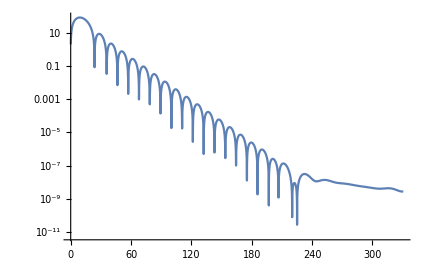

```mathematica
Schwl1data[[;;,2]]= Abs[Schwl1data[[;;,2]]];
ListLogPlot[{Schwl1data},Joined->True,PlotRange->Automatic]
```

11/02/2021:
 came back to test an idea for the boundary conditions of free waves at infinities

```mathematica
FDschw[500,200,1]
```

# of Iterations in space = 500

(r_*)^max =  50  , r^max =  35.76104438

(r_*)^min =  -50  , r^min =  2.000000000

I_max = 250

I_min = -250

Space Discretization step = 1/5

t_final/M = 200

# of Iterations in time = J_max = 1428

Time Discretization step = 0.14

Δt/(Δr_*) = 0.7

2.0036904185598743986

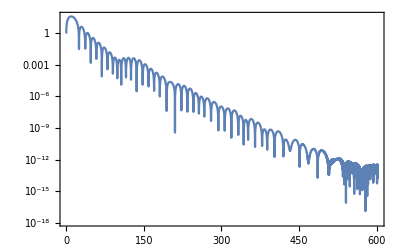

```mathematica
Block[{$RecursionLimit=Infinity,i=-10},
Print[NumberForm[r[i*Δrstar],20]];
ListLogPlot[{Table[{(j Δt)/M,Evaluate[Abs[ψ[i,j]]]},{j,0,4300}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

The Boundary conditions , as formulated, are not perfect. There is still some reflection, due to internal numerical errors, causing the small “bumps” on the ringdown . This reflection also causes extra oscillations on the late-time tail that we expect to see.  
We need a more robust formulation of the boundary conditions

```mathematica
ListAnimate[Table[Block[{$RecursionLimit=Infinity},
ListPlot[{Table[{i Δrstar  ,ψ[i,j]},{i,imin,imax}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ],{j,0,3000,30}]]
```

lambda = 10

l=10

```mathematica
FDschw[1800,250,10]
```

# of Iterations in space = 1800

(r_*)^max =  120  , r^max =  103.555671

(r_*)^min =  -20  , r^min =  2.000000451

I_max = 1542

I_min = -257

Space Discretization step = 7/90

t_final/M = 250

# of Iterations in time = J_max = 4591

Time Discretization step = 0.0544444

Δt/(Δr_*) = 0.7

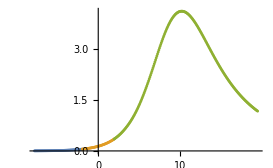

```mathematica
ListPlot[{Table[{i Δrstar  ,Vschw[r[i*Δrstar],10]},{i,-100,-25}],
Table[{i Δrstar  ,Vschw[r[i*Δrstar],10]},{i,-25,25}],
Table[{i Δrstar  ,Vschw[r[i*Δrstar],10]},{i,25,250}]},Joined->False,PlotRange->All]
```

2.008240157768338

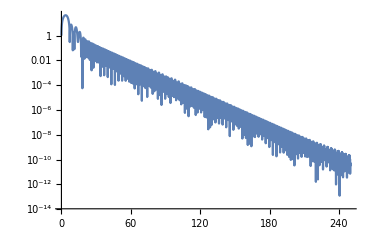

```mathematica
i=-5;
NumberForm[r[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/M,Evaluate[Abs[ψ[i,j]]]},{j,0,jmax}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All] ]
```

```mathematica
Schwl10data= Table[{(j Δt)/M ,ψ[i,j]},{j,0,jmax}]  ;
```

```mathematica
Export["Schw_l10M1data1.txt" ,Schwl10data];
Export["Schw_l10M1data2.txt" ,Schwl10data,"Table","FieldSeparators"->" "];
```

```mathematica
Clear[Schwl10data]
```

```mathematica
Schwl10data=Import["Schw_l10M1data2.txt","Table"];
```

```mathematica
FilePrint["Schw_l10M1data1.txt"]
```

{0., E^(-49/16200)}
{0.05444444444444444, 1.99350854394107}
{0.10888888888888888, 2.9891347651501396}
{0.16333333333333333, 3.9834072743129854}
{0.21777777777777776, 4.975874750743708}
{0.2722222222222222, 5.966085804992376}
{0.32666666666666666, 6.9535889638095805}
{0.38111111111111107, 7.937932656220274}
{0.43555555555555553, 8.918665201280483}
{0.49, 9.895334797997442}
{0.5444444444444444, 10.867489517761223}
{0.5988888888888888, 11.834677299660743}
{0.6533333333333333, 12.796445949124179}
{0.7077777777777777, 13.752343140286087}
{0.7622222222222221, 14.701916422418885}
{0.8166666666666667, 15.644713230844607}
{0.8711111111111111, 16.580280902956986}
{0.9255555555555555, 17.508166700133515}
{0.98, 18.427917836222957}
{1.0344444444444443, 19.339081512947274}
{1.0888888888888888, 20.241204962095175}
{1.1433333333333333, 21.133835494024318}
{1.1977777777777776, 22.016520551973656}
{1.2522222222222221, 22.888807772144844}
{1.3066666666666666, 23.750245050239474}
{1.361111111111111, 24.60038061563229}
{1.4155555555555555, 25.43876311424965}
{1.47, 26.26494170071662}
{1.5244444444444443, 27.078466140057362}
{1.5788888888888888, 27.878886919534484}
{1.6333333333333333, 28.665755371806693}
{1.6877777777777776, 29.438623810960845}
{1.7422222222222221, 30.197045682985785}
{1.7966666666666666, 30.940575732013798}
{1.851111111111111, 31.668770182985075}
{1.9055555555555554, 32.381186939896615}
{1.96, 33.077385796798985}
{2.0144444444444445, 33.756928657744915}
{2.0688888888888886, 34.419379763552755}
{2.123333333333333, 35.064305927057575}
{2.1777777777777776, 35.69127678153281}
{2.232222222222222, 36.2998650463048}
{2.2866666666666666, 36.889646809782455}
{2.341111111111111, 37.46020182716647}
{2.395555555555555, 38.01111383125675}
{2.4499999999999997, 38.541970858631664}
{2.5044444444444443, 39.05236559532881}
{2.5588888888888888, 39.54189574375436}
{2.6133333333333333, 40.010164409074555}
{2.667777777777778, 40.45678050337719}
{2.722222222222222, 40.881359169248725}
{2.7766666666666664, 41.28352222633321}
{2.831111111111111, 41.662898642222814}
{2.8855555555555554, 42.0191250259185}
{2.94, 42.3518461425904}
{2.9944444444444445, 42.66071545157046}
{3.0488888888888885, 42.94539567045766}
{3.103333333333333, 43.205559365400525}
{3.1577777777777776, 43.44088956532869}
{3.212222222222222, 43.65108039955099}
{3.2666666666666666, 43.83583776089534}
{3.321111111111111, 43.99487999587405}
{3.375555555555555, 44.12793862030346}
{3.4299999999999997, 44.23475905842265}
{3.4844444444444442, 44.31510140662765}
{3.5388888888888888, 44.36874122469421}
{3.5933333333333333, 44.395470355342816}
{3.6477777777777773, 44.395097771017745}
{3.702222222222222, 44.36745044815168}
{3.7566666666666664, 44.31237427068709}
{3.811111111111111, 44.2297349614265}
{3.8655555555555554, 44.119419033665196}
{3.92, 43.981334752456625}
{3.974444444444444, 43.8154130962187}
{4.028888888888889, 43.62160871184155}
{4.083333333333333, 43.39990085924901}
{4.137777777777777, 43.15029434706733}
{4.192222222222222, 42.87282046774784}
{4.246666666666666, 42.567537940604296}
{4.301111111111111, 42.23453386214849}
{4.355555555555555, 41.873924653285414}
{4.41, 41.485856992192886}
{4.464444444444444, 41.07050872925861}
{4.518888888888888, 40.62808978742478}
{4.573333333333333, 40.15884305206852}
{4.627777777777777, 39.66304525028569}
{4.682222222222222, 39.14100781353698}
{4.736666666666666, 38.59307771368733}
{4.79111111111111, 38.01963826451111}
{4.845555555555555, 37.42110988827615}
{4.8999999999999995, 36.797950851632805}
{4.954444444444444, 36.150657969342674}
{5.0088888888888885, 35.479767264162895}
{5.0633333333333335, 34.78585456984958}
{5.1177777777777775, 34.069536073756}
{5.172222222222222, 33.33146880240907}
{5.226666666666667, 32.57235104788787}
{5.281111111111111, 31.792922722739164}
{5.335555555555556, 30.993965630244386}
{5.39, 30.17630364498319}
{5.444444444444444, 29.340802803610647}
{5.498888888888889, 28.48837130136845}
{5.553333333333333, 27.619959382955916}
{5.607777777777778, 26.736559115711174}
{5.662222222222222, 25.839204038188086}
{5.716666666666666, 24.92896868112254}
{5.771111111111111, 24.006967955924807}
{5.825555555555555, 23.07435640067849}
{5.88, 22.132327271615996}
{5.934444444444444, 21.182111472224666}
{5.988888888888889, 20.22497631750071}
{6.043333333333333, 19.262224129826535}
{6.097777777777777, 18.295190656563584}
{6.152222222222222, 17.325243297638295}
{6.206666666666666, 16.353779138276618}
{6.261111111111111, 15.38222278806387}
{6.315555555555555, 14.4120240235617}
{6.369999999999999, 13.444655224588987}
{6.424444444444444, 12.481608596764765}
{6.478888888888888, 11.524393182628229}
{6.533333333333333, 10.574531666040459}
{6.587777777777777, 9.633556966899476}
{6.642222222222222, 8.703008619595161}
{6.696666666666666, 7.784428936663389}
{6.75111111111111, 6.879358966965508}
{6.805555555555555, 5.989334254168367}
{6.859999999999999, 5.115880394798067}
{6.914444444444444, 4.26050839975102}
{6.9688888888888885, 3.4247098752008807}
{7.0233333333333325, 2.6099520437520987}
{7.0777777777777775, 1.8176726234246243}
{7.132222222222222, 1.0492745834010384}
{7.1866666666666665, 0.30612080468469216}
{7.241111111111111, -0.4104713218495138}
{7.295555555555555, -1.0992353358557019}
{7.35, -1.7589611732085446}
{7.404444444444444, -2.388500645337187}
{7.458888888888889, -2.9867729149594013}
{7.513333333333333, -3.5527699469502045}
{7.567777777777778, -4.085561909796745}
{7.622222222222222, -4.584302494357152}
{7.676666666666666, -5.048234105922017}
{7.731111111111111, -5.476692884350816}
{7.785555555555555, -5.86911351776301}
{7.84, -6.225033825893507}
{7.894444444444444, -6.544099088183903}
{7.948888888888888, -6.826066081230896}
{8.003333333333332, -7.07080678110963}
{8.057777777777778, -7.2783116841654625}
{8.112222222222222, -7.448692703114675}
{8.166666666666666, -7.582185600719344}
{8.22111111111111, -7.679151929647791}
{8.275555555555554, -7.740080450948425}
{8.33, -7.765587999963245}
{8.384444444444444, -7.756419759702865}
{8.438888888888888, -7.713448899163755}
{8.493333333333332, -7.637675545321427}
{8.547777777777778, -7.530225073680607}
{8.602222222222222, -7.392345707061317}
{8.656666666666666, -7.225405403825021}
{8.71111111111111, -7.030888010796967}
{8.765555555555554, -6.81038866487257}
{8.82, -6.565608443586638}
{8.874444444444444, -6.298348274325811}
{8.928888888888888, -6.010502112127836}
{8.983333333333333, -5.704049395889401}
{9.037777777777777, -5.381046797460105}
{9.092222222222222, -5.043619286025258}
{9.146666666666667, -4.693950540444708}
{9.20111111111111, -4.334272753710761}
{9.255555555555555, -3.966855880193288}
{9.309999999999999, -3.5939963743801995}
{9.364444444444445, -3.2180054692139133}
{9.418888888888889, -2.841197054748429}
{9.473333333333333, -2.465875236636193}
{9.527777777777777, -2.094321659528944}
{9.58222222222222, -1.728782671250357}
{9.636666666666667, -1.371456400758012}
{9.69111111111111, -1.0244798380285856}
{9.745555555555555, -0.6899160201382986}
{9.799999999999999, -0.3697414259625005}
{9.854444444444443, -0.06583367032368492}
{9.908888888888889, 0.2200404121630599}
{9.963333333333333, 0.4862361922688672}
{10.017777777777777, 0.7312420738764831}
{10.072222222222221, 0.9536896250218259}
{10.126666666666667, 1.1523629217401157}
{10.181111111111111, 1.3262070165237205}
{10.235555555555555, 1.4743354439011007}
{10.29, 1.5960366797750454}
{10.344444444444443, 1.6907794773838654}
{10.398888888888889, 1.758217010938152}
{10.453333333333333, 1.7981897698303846}
{10.507777777777777, 1.8107271573711103}
{10.562222222222221, 1.7960477526563798}
{10.616666666666665, 1.7545581987084367}
{10.671111111111111, 1.686850695484243}
{10.725555555555555, 1.593699097764107}
{10.78, 1.4760536288921409}
{10.834444444444443, 1.3350342218648625}
{10.888888888888888, 1.1719225085958893}
{10.943333333333333, 0.9881525027334586}
{10.997777777777777, 0.7853000418085954}
{11.052222222222222, 0.5650710571568421}
{11.106666666666666, 0.32928874072826453}
{11.16111111111111, 0.07987969542555867}
{11.215555555555556, -0.181140820225128}
{11.27, -0.4516844335804441}
{11.324444444444444, -0.729605869867177}
{11.378888888888888, -1.0127197133153696}
{11.433333333333332, -1.2988175775757687}
{11.487777777777778, -1.5856855336366522}
{11.542222222222222, -1.8711216470226866}
{11.596666666666666, -2.1529534803422967}
{11.65111111111111, -2.429055410485036}
{11.705555555555556, -2.6973656015229257}
{11.76, -2.9559024771406084}
{11.814444444444444, -3.202780545772985}
{11.868888888888888, -3.436225436591031}
{11.923333333333332, -3.6545880056117137}
{11.977777777777778, -3.856357376523663}
{12.032222222222222, -4.04017279184133}
{12.086666666666666, -4.204834162146147}
{12.14111111111111, -4.349311212436842}
{12.195555555555554, -4.47275113603801}
{12.25, -4.574484678563912}
{12.304444444444444, -4.654030588254514}
{12.358888888888888, -4.711098386388294}
{12.413333333333332, -4.745589429973304}
{12.467777777777776, -4.757596253474382}
{12.522222222222222, -4.747400188680813}
{12.576666666666666, -4.715467279521278}
{12.63111111111111, -4.662442531379786}
{12.685555555555554, -4.589142552092629}
{12.739999999999998, -4.496546651318593}
{12.794444444444444, -4.385786477231129}
{12.848888888888888, -4.2581342906649855}
{12.903333333333332, -4.114989996103345}
{12.957777777777777, -3.957867056192173}
{13.01222222222222, -3.788377420770283}
{13.066666666666666, -3.6082156155237075}
{13.12111111111111, -3.4191421527344943}
{13.175555555555555, -3.2229664317520608}
{13.229999999999999, -3.0215292925921773}
{13.284444444444444, -2.816685389069755}
{13.338888888888889, -2.6102855592495815}
{13.393333333333333, -2.404159374053183}
{13.447777777777777, -2.200098034264928}
{13.50222222222222, -1.9998377773405123}
{13.556666666666667, -1.805043957325981}
{13.61111111111111, -1.6172959607775432}
{13.665555555555555, -1.4380731070300254}
{13.719999999999999, -1.2687416627466925}
{13.774444444444443, -1.1105430924985473}
{13.828888888888889, -0.9645836626098887}
{13.883333333333333, -0.8318254996274921}
{13.937777777777777, -0.7130791805930239}
{13.992222222222221, -0.6089979153113206}
{14.046666666666665, -0.520073372021726}
{14.101111111111111, -0.4466331831065379}
{14.155555555555555, -0.3888401427509339}
{14.209999999999999, -0.34669308654559167}
{14.264444444444443, -0.3200294308525791}
{14.318888888888887, -0.3085293373779505}
{14.373333333333333, -0.311721447446251}
{14.427777777777777, -0.32899010864500794}
{14.482222222222221, -0.359584003573571}
{14.536666666666665, -0.40262608176331793}
{14.59111111111111, -0.4571246816510165}
{14.645555555555555, -0.521985712073188}
{14.7, -0.5960257518673693}
{14.754444444444443, -0.677985922244885}
{14.808888888888887, -0.7665463810399069}
{14.863333333333333, -0.8603412783913822}
{14.917777777777777, -0.95797400713072}
{14.972222222222221, -1.0580325821474754}
{15.026666666666666, -1.1591049859655604}
{15.08111111111111, -1.2597943177927986}
{15.135555555555555, -1.3587335837215049}
{15.19, -1.4545999716167577}
{15.244444444444444, -1.5461284639974924}
{15.298888888888888, -1.6321246510398197}
{15.353333333333332, -1.7114766134736656}
{15.407777777777778, -1.7831657554898666}
{15.462222222222222, -1.8462764820676076}
{15.516666666666666, -1.9000046302426175}
{15.57111111111111, -1.9436645773449068}
{15.625555555555554, -1.9766949627531432}
{15.68, -1.9986629758470555}
{15.734444444444444, -2.0092671809258396}
{15.788888888888888, -2.0083388667699493}
{15.843333333333332, -1.9958419232075155}
{15.897777777777776, -1.9718712620390362}
{15.952222222222222, -1.936649816957233}
{16.006666666666664, -1.8905241744007555}
{16.06111111111111, -1.8339589011178568}
{16.115555555555556, -1.767529645525561}
{16.169999999999998, -1.6919151027711157}
{16.224444444444444, -1.6078879478064265}
{16.278888888888886, -1.5163048519659719}
{16.333333333333332, -1.4180957046973355}
{16.387777777777778, -1.314252167890056}
{16.44222222222222, -1.2058156988286444}
{16.496666666666666, -1.093865184726485}
{16.55111111111111, -0.9795043323910924}
{16.605555555555554, -0.8638489544406983}
{16.66, -0.7480142945382277}
{16.714444444444442, -0.6331025357777044}
{16.76888888888889, -0.5201906317975977}
{16.82333333333333, -0.41031859076631394}
{16.877777777777776, -0.3044783357750653}
{16.932222222222222, -0.2036032615911184}
{16.986666666666665, -0.10855859921866323}
{17.04111111111111, -0.020132684769876563}
{17.095555555555556, 0.060970783881014436}
{17.15, 0.13413942695584405}
{17.204444444444444, 0.19885773390543476}
{17.258888888888887, 0.2547114383898021}
{17.313333333333333, 0.3013906869626145}
{17.36777777777778, 0.3386919815449699}
{17.42222222222222, 0.3665188857841164}
{17.476666666666667, 0.38488150288048245}
{17.53111111111111, 0.39389475127308077}
{17.585555555555555, 0.39377547533927365}
{17.64, 0.3848384355472755}
{17.694444444444443, 0.36749123649235876}
{17.74888888888889, 0.3422282686477552}
{17.80333333333333, 0.30962374915735835}
{17.857777777777777, 0.27032394993193215}
{17.912222222222223, 0.22503870931377107}
{17.966666666666665, 0.1745323369440339}
{18.02111111111111, 0.11961402821977807}
{18.075555555555553, 0.061127902580587826}
{18.13, -0.00005721944439263105}
{18.184444444444445, -0.06305817794354067}
{18.238888888888887, -0.12698784849254918}
{18.293333333333333, -0.19096541166305936}
{18.347777777777775, -0.2541264052755313}
{18.40222222222222, -0.3156324463630015}
{18.456666666666667, -0.3746805104651977}
{18.51111111111111, -0.43051166688082754}
{18.565555555555555, -0.482419181296886}
{18.619999999999997, -0.5297559018887881}
{18.674444444444443, -0.5719408486429011}
{18.72888888888889, -0.6084649389290929}
{18.78333333333333, -0.6388957992884841}
{18.837777777777777, -0.6628816223611939}
{18.89222222222222, -0.6801540330987466}
{18.946666666666665, -0.6905299418026414}
{19.00111111111111, -0.6939123800966616}
{19.055555555555554, -0.6902903271350772}
{19.11, -0.6797375383636531}
{19.16444444444444, -0.6624104003904921}
{19.218888888888888, -0.6385448530773337}
{19.273333333333333, -0.6084524312424665}
{19.327777777777776, -0.5725154815209869}
{19.38222222222222, -0.5311816170336914}
{19.436666666666664, -0.48495748668927097}
{19.49111111111111, -0.43440194541351024}
{19.545555555555556, -0.38011871170073647}
{19.599999999999998, -0.3227486005668397}
{19.654444444444444, -0.26296142906389525}
{19.708888888888886, -0.20144769781495253}
{19.763333333333332, -0.13891014855868358}
{19.817777777777778, -0.07605529360316063}
{19.87222222222222, -0.01358501629503045}
{19.926666666666666, 0.047811655894122534}
{19.981111111111108, 0.10746651088970367}
{20.035555555555554, 0.1647397586163306}
{20.09, 0.21902720155925498}
{20.144444444444442, 0.2697668872940989}
{20.198888888888888, 0.31644517030799696}
{20.253333333333334, 0.35860212341276604}
{20.307777777777776, 0.3958362458829071}
{20.362222222222222, 0.4278084192861112}
{20.416666666666664, 0.4542450724045392}
{20.47111111111111, 0.4749405314102812}
{20.525555555555556, 0.4897585408850212}
{20.58, 0.4986329463639014}
{20.634444444444444, 0.5015675390044767}
{20.688888888888886, 0.4986350774275257}
{20.743333333333332, 0.48997551171568376}
{20.797777777777778, 0.4757934392413752}
{20.85222222222222, 0.45635482980406655}
{20.906666666666666, 0.43198306975940615}
{20.96111111111111, 0.4030543833478761}
{21.015555555555554, 0.3699926922056153}
{21.07, 0.3332639784466655}
{21.124444444444443, 0.2933702252115302}
{21.17888888888889, 0.25084301424338534}
{21.23333333333333, 0.20623685987825427}
{21.287777777777777, 0.16012235911064512}
{21.342222222222222, 0.11307924142829462}
{21.396666666666665, 0.06568940416282368}
{21.45111111111111, 0.018530015598935815}
{21.505555555555553, -0.02783323579837508}
{21.56, -0.07285266812847194}
{21.614444444444445, -0.11600483241851542}
{21.668888888888887, -0.15679636875579028}
{21.723333333333333, -0.19476942969370545}
{21.777777777777775, -0.22950661264128897}
{21.83222222222222, -0.2606353474254454}
{21.886666666666667, -0.287831693780013}
{21.94111111111111, -0.3108235130674121}
{21.995555555555555, -0.32939298518899984}
{22.049999999999997, -0.34337844784998817}
{22.104444444444443, -0.35267554464639067}
{22.15888888888889, -0.3572376785732555}
{22.21333333333333, -0.35707577499979165}
{22.267777777777777, -0.3522573646489619}
{22.32222222222222, -0.3429050057223277}
{22.376666666666665, -0.32919407337087847}
{22.43111111111111, -0.3113499512694924}
{22.485555555555553, -0.2896446654005061}
{22.54, -0.26439300679032474}
{22.59444444444444, -0.235948196547492}
{22.648888888888887, -0.20469715079526682}
{22.703333333333333, -0.17105540614943401}
{22.757777777777775, -0.13546177020179745}
{22.81222222222222, -0.09837276474689688}
{22.866666666666664, -0.06025693050169317}
{22.92111111111111, -0.021589062162613026}
{22.975555555555555, 0.01715555669087023}
{23.029999999999998, 0.05550684960733335}
{23.084444444444443, 0.09300550744640546}
{23.138888888888886, 0.1292083489606906}
{23.19333333333333, 0.16369342021685093}
{23.247777777777777, 0.19606477467023978}
{23.30222222222222, 0.2259568813251433}
{23.356666666666666, 0.2530386139849907}
{23.41111111111111, 0.2770167789093501}
{23.465555555555554, 0.29763914367587135}
{23.52, 0.3146969378429464}
{23.574444444444442, 0.3280268032713319}
{23.628888888888888, 0.3375121772434532}
{23.683333333333334, 0.3430840977616123}
{23.737777777777776, 0.344721429091762}
{23.79222222222222, 0.34245051340458577}
{23.846666666666664, 0.3363442593489541}
{23.90111111111111, 0.32652068395497036}
{23.955555555555556, 0.31314093245116487}
{24.009999999999998, 0.29640680770168454}
{24.064444444444444, 0.2765578444938045}
{24.118888888888886, 0.25386796750916374}
{24.173333333333332, 0.2286417782796039}
{24.227777777777778, 0.20121052191076919}
{24.28222222222222, 0.17192778557580796}
{24.336666666666666, 0.14116498152637807}
{24.39111111111111, 0.10930667127062388}
{24.445555555555554, 0.07674579082769102}
{24.5, 0.04387883549914137}
{24.554444444444442, 0.01110106010225207}
{24.608888888888888, -0.021198248391263497}
{24.66333333333333, -0.05264036792185631}
{24.717777777777776, -0.08286155424128366}
{24.772222222222222, -0.11151722133393031}
{24.826666666666664, -0.1382858427621103}
{24.88111111111111, -0.16287252830420706}
{24.935555555555553, -0.18501223618686885}
{24.99, -0.20447258917486102}
{25.044444444444444, -0.22105626655655453}
{25.098888888888887, -0.23460294614307084}
{25.153333333333332, -0.2449907772463062}
{25.207777777777775, -0.2521373749459861}
{25.26222222222222, -0.2560003308464701}
{25.316666666666666, -0.25657723768883256}
{25.37111111111111, -0.2539052317593571}
{25.425555555555555, -0.24806006659177557}
{25.479999999999997, -0.23915473642772295}
{25.534444444444443, -0.22733766910186426}
{25.58888888888889, -0.21279051316286768}
{25.64333333333333, -0.195725552695943}
{25.697777777777777, -0.17638278743266617}
{25.75222222222222, -0.15502671511274072}
{25.806666666666665, -0.13194285584505966}
{25.86111111111111, -0.10743406510323322}
{25.915555555555553, -0.08181668463177098}
{25.97, -0.05541657758723495}
{26.02444444444444, -0.028565094109153408}
{26.078888888888887, -0.0015950181524873805}
{26.133333333333333, 0.025163452652875083}
{26.187777777777775, 0.05138664769309774}
{26.24222222222222, 0.07676124132171935}
{26.296666666666663, 0.10098790244306423}
{26.35111111111111, 0.12378473066961106}
{26.405555555555555, 0.14489044133270776}
{26.459999999999997, 0.16406726739795252}
{26.514444444444443, 0.18110354593808797}
{26.56888888888889, 0.19581595831129808}
{26.62333333333333, 0.20805140174685857}
{26.677777777777777, 0.21768847772029104}
{26.73222222222222, 0.22463858337735662}
{26.786666666666665, 0.22884659385881884}
{26.84111111111111, 0.23029113213232535}
{26.895555555555553, 0.2289844315738339}
{26.95, 0.2249717978786472}
{27.00444444444444, 0.21833067766695088}
{27.058888888888887, 0.20916934903149614}
{27.113333333333333, 0.19762525787216081}
{27.167777777777776, 0.18386302486720868}
{27.22222222222222, 0.16807214710476523}
{27.276666666666664, 0.15046442446738786}
{27.33111111111111, 0.13127114855991512}
{27.385555555555555, 0.11074009203296681}
{27.439999999999998, 0.08913233317105153}
{27.494444444444444, 0.06671895421398903}
{27.548888888888886, 0.043777658092790245}
{27.60333333333333, 0.020589347070912353}
{27.657777777777778, -0.0025652985439255996}
{27.71222222222222, -0.025409202595482572}
{27.766666666666666, -0.047672192660323014}
{27.821111111111108, -0.06909417588896205}
{27.875555555555554, -0.08942815743916976}
{27.93, -0.10844306958617506}
{27.984444444444442, -0.12592637666663725}
{28.038888888888888, -0.14168642422921263}
{28.09333333333333, -0.1555545097887947}
{28.147777777777776, -0.1673866564507082}
{28.202222222222222, -0.17706506886766937}
{28.256666666666664, -0.18449925438366788}
{28.31111111111111, -0.18962680198905782}
{28.365555555555552, -0.19241381695678297}
{28.419999999999998, -0.19285500771028133}
{28.474444444444444, -0.19097342426709032}
{28.528888888888886, -0.1868198571887018}
{28.583333333333332, -0.18047191174924912}
{28.637777777777774, -0.172032770513374}
{28.69222222222222, -0.16162965895786305}
{28.746666666666666, -0.1494120372950051}
{28.80111111111111, -0.13554954719185594}
{28.855555555555554, -0.12022973976868828}
{28.909999999999997, -0.10365561076864381}
{28.964444444444442, -0.08604297556505668}
{29.01888888888889, -0.06761772137613006}
{29.07333333333333, -0.04861297059382429}
{29.127777777777776, -0.02926618639487999}
{29.18222222222222, -0.00981625643856264}
{29.236666666666665, 0.009499405973674427}
{29.29111111111111, 0.0284477085832774}
{29.345555555555553, 0.04680264498017413}
{29.4, 0.06434794535299507}
{29.454444444444444, 0.08087957854914848}
{29.508888888888887, 0.09620807646813881}
{29.563333333333333, 0.11016065866916354}
{29.617777777777775, 0.12258313453183606}
{29.67222222222222, 0.13334155865058292}
{29.726666666666667, 0.1423236212720538}
{29.78111111111111, 0.1494397637295166}
{29.835555555555555, 0.1546240096723119}
{29.889999999999997, 0.15783450151390416}
{29.944444444444443, 0.15905373744912152}
{29.99888888888889, 0.15828851306994046}
{30.05333333333333, 0.15556957318498607}
{30.107777777777777, 0.15095097775436078}
{30.16222222222222, 0.14450919086318498}
{30.216666666666665, 0.1363419100974189}
{30.27111111111111, 0.12656665534023898}
{30.325555555555553, 0.11531913343749418}
{30.38, 0.10275139865291216}
{30.43444444444444, 0.0890298363720394}
{30.488888888888887, 0.07433299872104765}
{30.543333333333333, 0.05884931692635294}
{30.597777777777775, 0.042774716748902694}
{30.65222222222222, 0.026310169513240715}
{30.706666666666663, 0.009659211704851463}
{30.76111111111111, -0.006974539150882506}
{30.815555555555555, -0.023389845225387285}
{30.869999999999997, -0.039390253979662664}
{30.924444444444443, -0.054786417193054195}
{30.978888888888886, -0.06939829856059901}
{31.03333333333333, -0.08305724758533536}
{31.087777777777777, -0.09560791426192118}
{31.14222222222222, -0.10690997995947335}
{31.196666666666665, -0.11683968737333594}
{31.251111111111108, -0.12529115660133539}
{31.305555555555554, -0.13217747225925566}
{31.36, -0.1374315276096536}
{31.41444444444444, -0.14100661947908172}
{31.468888888888888, -0.1428767929479274}
{31.52333333333333, -0.1430369332584951}
{31.577777777777776, -0.14150260306061335}
{31.63222222222222, -0.1383096305992651}
{31.686666666666664, -0.13351346004161843}
{31.74111111111111, -0.12718827367721616}
{31.795555555555552, -0.11942589548195921}
{31.849999999999998, -0.11033449208072664}
{31.904444444444444, -0.1000370925235293}
{31.958888888888886, -0.08866994644451323}
{32.01333333333333, -0.07638073859288048}
{32.06777777777778, -0.06332668283810348}
{32.12222222222222, -0.04967252346538088}
{32.17666666666666, -0.03558846905441494}
{32.23111111111111, -0.02124808109138921}
{32.285555555555554, -0.006826142869422323}
{32.339999999999996, 0.007503461962652012}
{32.394444444444446, 0.02156983512128832}
{32.44888888888889, 0.035207092289666855}
{32.50333333333333, 0.048256311540823715}
{32.55777777777777, 0.06056737563441748}
{32.61222222222222, 0.07200068612115977}
{32.666666666666664, 0.08242873317882313}
{32.72111111111111, 0.09173750495973829}
{32.775555555555556, 0.09982771804606486}
{32.83, 0.10661585474910996}
{32.88444444444444, 0.11203499983100754}
{32.93888888888889, 0.11603547021195029}
{32.99333333333333, 0.11858522938306104}
{33.047777777777775, 0.11967008217169794}
{33.10222222222222, 0.11929365264089803}
{33.156666666666666, 0.11747714951948396}
{33.21111111111111, 0.1142589216227838}
{33.26555555555555, 0.10969380893366917}
{33.32, 0.10385230186546207}
{33.37444444444444, 0.09681952296918328}
{33.428888888888885, 0.08869404291035753}
{33.483333333333334, 0.07958654459336716}
{33.53777777777778, 0.06961835538432784}
{33.59222222222222, 0.05891986883471327}
{33.64666666666666, 0.04762887407591353}
{33.70111111111111, 0.035888811656063044}
{33.75555555555555, 0.023846979547155693}
{33.809999999999995, 0.011652713955429432}
{33.864444444444445, -0.0005444345788501205}
{33.91888888888889, -0.012596510253145177}
{33.97333333333333, -0.024358922999384913}
{34.02777777777778, -0.03569215786089304}
{34.08222222222222, -0.04646340418733313}
{34.13666666666666, -0.0565480884646454}
{34.19111111111111, -0.06583129205996982}
{34.245555555555555, -0.07420903533657744}
{34.3, -0.0815894151483895}
{34.35444444444444, -0.08789358623065353}
{34.40888888888889, -0.09305657537841949}
{34.46333333333333, -0.0970279176648001}
{34.51777777777777, -0.0997721096781791}
{34.57222222222222, -0.10126887895793384}
{34.626666666666665, -0.10151326771995765}
{34.68111111111111, -0.10051552913389483}
{34.73555555555556, -0.09830083985293743}
{34.79, -0.09490883690547262}
{34.84444444444444, -0.09039298609469412}
{34.898888888888884, -0.08481978865241789}
{34.95333333333333, -0.07826783760517253}
{35.007777777777775, -0.07082673947590186}
{35.06222222222222, -0.06259591574190682}
{35.11666666666667, -0.05368329719211678}
{35.17111111111111, -0.04420392797191277}
{35.22555555555555, -0.03427849968378873}
{35.28, -0.024031834221679926}
{35.33444444444444, -0.013591331690363653}
{35.388888888888886, -0.003085402156099617}
{35.44333333333333, 0.007358097211766409}
{35.49777777777778, 0.017613400314656465}
{35.55222222222222, 0.027558329696772715}
{35.60666666666666, 0.037075736455080804}
{35.66111111111111, 0.04605486338119242}
{35.715555555555554, 0.05439261498770658}
{35.769999999999996, 0.06199472232764859}
{35.824444444444445, 0.06877679045178231}
{35.87888888888889, 0.07466521490602235}
{35.93333333333333, 0.07959795669043626}
{35.98777777777777, 0.08352516992778937}
{36.04222222222222, 0.08640967719687138}
{36.096666666666664, 0.0882272863614555}
{36.151111111111106, 0.08896694567531194}
{36.205555555555556, 0.08863073894857447}
{36.26, 0.08723372365840502}
{36.31444444444444, 0.08480361373957807}
{36.36888888888889, 0.08138031130899619}
{36.42333333333333, 0.0770152963574074}
{36.477777777777774, 0.07177088454844559}
{36.53222222222222, 0.06571936176995671}
{36.586666666666666, 0.05894200584804195}
{36.64111111111111, 0.05152801004222784}
{36.69555555555555, 0.043573323743858014}
{36.75, 0.03517942371363974}
{36.80444444444444, 0.026452029985798285}
{36.858888888888885, 0.01749978397279929}
{36.913333333333334, 0.008432906614538011}
{36.967777777777776, -0.0006381483756311146}
{37.02222222222222, -0.00960403137830848}
{37.07666666666666, -0.01835780653514054}
{37.13111111111111, -0.02679621712684476}
{37.18555555555555, -0.034820893035599286}
{37.239999999999995, -0.04233948790914019}
{37.294444444444444, -0.04926673192890871}
{37.34888888888889, -0.05552538673796706}
{37.40333333333333, -0.06104709304246489}
{37.45777777777778, -0.06577310341640338}
{37.51222222222222, -0.0696548917292852}
{37.56666666666666, -0.0726546314727922}
{37.62111111111111, -0.07474553943695436}
{37.675555555555555, -0.07591208367018946}
{37.73, -0.07615005386387688}
{37.78444444444444, -0.0754664930686409}
{37.83888888888889, -0.07387949370964374}
{37.89333333333333, -0.071417863478468}
{37.94777777777777, -0.06812066588910057}
{38.00222222222222, -0.06403664066173982}
{38.056666666666665, -0.05922351272454481}
{38.11111111111111, -0.0537472010432505}
{38.16555555555556, -0.04768093742665172}
{38.22, -0.041104305194382275}
{38.27444444444444, -0.03410221053491405}
{38.32888888888888, -0.026763801373868336}
{38.38333333333333, -0.019181347052497393}
{38.437777777777775, -0.011449091069675999}
{38.49222222222222, -0.0036620912572859904}
{38.54666666666667, 0.004084936796263126}
{38.60111111111111, 0.011698759303094218}
{38.65555555555555, 0.019088734893879584}
{38.71, 0.02616788309398182}
{38.76444444444444, 0.03285389654500498}
{38.818888888888885, 0.03907008536088923}
{38.87333333333333, 0.04474624455612844}
{38.92777777777778, 0.049819434915378456}
{38.98222222222222, 0.05423466716533413}
{39.03666666666666, 0.057945482091985925}
{39.09111111111111, 0.060914422277074554}
{39.14555555555555, 0.06311339105688363}
{39.199999999999996, 0.06452389397804142}
{39.254444444444445, 0.06513716083409168}
{39.30888888888889, 0.06495414960052087}
{39.36333333333333, 0.0639854337418319}
{39.41777777777777, 0.06225097395388085}
{39.47222222222222, 0.059779777961795524}
{39.526666666666664, 0.05660945513956093}
{39.581111111111106, 0.05278567282831895}
{39.635555555555555, 0.04836152048958152}
{39.69, 0.04339678988359695}
{39.74444444444444, 0.03795718226923952}
{39.79888888888889, 0.03211345346669271}
{39.85333333333333, 0.025940506366324504}
{39.907777777777774, 0.019516441840843907}
{39.962222222222216, 0.012921581315560472}
{40.016666666666666, 0.006237473698796901}
{40.07111111111111, -0.0004541024899408575}
{40.12555555555555, -0.0070721303360677034}
{40.18, -0.013537325903314652}
{40.23444444444444, -0.01977307754941174}
{40.288888888888884, -0.02570634341744901}
{40.343333333333334, -0.03126849742808449}
{40.397777777777776, -0.03639611288479431}
{40.45222222222222, -0.041031674107960645}
{40.50666666666667, -0.045124209417692976}
{40.56111111111111, -0.048629839445733875}
{40.61555555555555, -0.05151223391097701}
{40.669999999999995, -0.05374297145313236}
{40.724444444444444, -0.0553018002711041}
{40.778888888888886, -0.056176798326323094}
{40.83333333333333, -0.05636443118148925}
{40.88777777777778, -0.055869506936064635}
{40.94222222222222, -0.05470503087271544}
{40.99666666666666, -0.05289196355074707}
{41.05111111111111, -0.050458885319417834}
{41.105555555555554, -0.04744157131509299}
{41.16, -0.04388248391955218}
{41.21444444444444, -0.03983019065843935}
{41.26888888888889, -0.03533871448018324}
{41.32333333333333, -0.030466823955451347}
{41.37777777777777, -0.025277273420365023}
{41.43222222222222, -0.0198360037976395}
{41.486666666666665, -0.014211313379341735}
{41.54111111111111, -0.008473007846434804}
{41.595555555555556, -0.0026915407442970884}
{41.65, 0.003062844030843479}
{41.70444444444444, 0.00872095808811935}
{41.75888888888888, 0.014215493733491387}
{41.81333333333333, 0.019481818095695387}
{41.867777777777775, 0.024458725812433656}
{41.92222222222222, 0.029089142218946814}
{41.97666666666667, 0.033320770176926376}
{42.03111111111111, 0.03710667275612145}
{42.08555555555555, 0.040405784267171764}
{42.14, 0.043183344733994274}
{42.19444444444444, 0.045411254493409575}
{42.248888888888885, 0.047068344995237134}
{42.30333333333333, 0.048140562253543864}
{42.35777777777778, 0.04862106207178183}
{42.41222222222222, 0.04851021796551145}
{42.46666666666666, 0.04781554220606078}
{42.52111111111111, 0.04655152067857689}
{42.57555555555555, 0.04473936479152237}
{42.629999999999995, 0.04240668546526312}
{42.684444444444445, 0.039587093643179826}
{42.73888888888889, 0.03631973174219965}
{42.79333333333333, 0.03264874268396427}
{42.84777777777777, 0.028622684745037208}
{42.90222222222222, 0.024293899635478358}
{42.95666666666666, 0.019717840748214636}
{43.011111111111106, 0.014952370289974988}
{43.065555555555555, 0.010057035286254018}
{43.12, 0.005092331284156391}
{43.17444444444444, 0.00011896159768421104}
{43.22888888888889, -0.004802898807468585}
{43.28333333333333, -0.00961432476815065}
{43.337777777777774, -0.014258339216396165}
{43.39222222222222, -0.018680581290260463}
{43.446666666666665, -0.02282993648147074}
{43.50111111111111, -0.026659120429367897}
{43.55555555555555, -0.03012520977481281}
{43.61, -0.03319011537923954}
{43.66444444444444, -0.03582099284398314}
{43.718888888888884, -0.037990584857481406}
{43.77333333333333, -0.03967749185073248}
{43.827777777777776, -0.04086636959440718}
{43.88222222222222, -0.04154805223850198}
{43.93666666666667, -0.04171959892939211}
{43.99111111111111, -0.04138426406726035}
{44.04555555555555, -0.04055139350180994}
{44.099999999999994, -0.03923624889381801}
{44.154444444444444, -0.03745976197175228}
{44.208888888888886, -0.03524822213787209}
{44.26333333333333, -0.03263290301949758}
{44.31777777777778, -0.0296496333900549}
{44.37222222222222, -0.02633831710037907}
{44.42666666666666, -0.022742408032834144}
{44.48111111111111, -0.018908347998646883}
{44.535555555555554, -0.0148849751071959}
{44.589999999999996, -0.010722908961761196}
{44.64444444444444, -0.006473919959590502}
{44.69888888888889, -0.002190291568523975}
{44.75333333333333, 0.0020758162154619923}
{44.80777777777777, 0.006272995626645803}
{44.86222222222222, 0.010351205052021414}
{44.916666666666664, 0.014262359793514793}
{44.97111111111111, 0.01796089227268896}
{45.025555555555556, 0.02140427627326675}
{45.08, 0.024553509797626334}
{45.13444444444444, 0.02737355010216096}
{45.18888888888888, 0.029833695578356797}
{45.24333333333333, 0.03190791143097915}
{45.297777777777775, 0.03357509641095385}
{45.35222222222222, 0.034819286995633816}
{45.406666666666666, 0.0356297965525671}
{45.46111111111111, 0.03600128945643439}
{45.51555555555555, 0.03593379061970021}
{45.57, 0.035432630034708826}
{45.62444444444444, 0.034508322953439696}
{45.678888888888885, 0.0331763887548584}
{45.73333333333333, 0.03145711207683164}
{45.78777777777778, 0.029375248784525774}
{45.84222222222222, 0.026959680110910312}
{45.89666666666666, 0.024243020573250926}
{45.95111111111111, 0.021261185705056026}
{46.00555555555555, 0.018052924379578127}
{46.059999999999995, 0.014659320883858403}
{46.114444444444445, 0.011123273908275739}
{46.16888888888889, 0.007488959877716493}
{46.22333333333333, 0.0038012864628366953}
{46.27777777777777, 0.00010534204942178656}
{46.33222222222222, -0.0035541513634668475}
{46.38666666666666, -0.007133374303154321}
{46.441111111111105, -0.01058992938344551}
{46.495555555555555, -0.013883339171613853}
{46.55, -0.01697551585864661}
{46.60444444444444, -0.019831196327252314}
{46.65888888888889, -0.022418338399097022}
{46.71333333333333, -0.02470847493060756}
{46.76777777777777, -0.026677021272821476}
{46.82222222222222, -0.028303531779551486}
{46.876666666666665, -0.029571903398598533}
{46.93111111111111, -0.030470525547984073}
{46.98555555555555, -0.030992374456138144}
{47.04, -0.03113505026026355}
{47.09444444444444, -0.030900757533956973}
{47.148888888888884, -0.030296231233453458}
{47.20333333333333, -0.02933260903831105}
{47.257777777777775, -0.028025250990551705}
{47.31222222222222, -0.026393509597885362}
{47.36666666666667, -0.024460454909246913}
{47.42111111111111, -0.022252557954790444}
{47.47555555555555, -0.019799335565752096}
{47.529999999999994, -0.017132961614450107}
{47.58444444444444, -0.014287850980269523}
{47.638888888888886, -0.011300221248993656}
{47.69333333333333, -0.008207636390672075}
{47.74777777777778, -0.005048538367729227}
{47.80222222222222, -0.0018617737552133326}
{47.85666666666666, 0.0013138790578381557}
{47.91111111111111, 0.004440177693777829}
{47.965555555555554, 0.0074798728881065564}
{48.019999999999996, 0.010397148128916506}
{48.07444444444444, 0.013158036800818333}
{48.12888888888889, 0.01573081336592258}
{48.18333333333333, 0.018086354081480436}
{48.23777777777777, 0.020198461863234426}
{48.29222222222222, 0.022044151729799424}
{48.346666666666664, 0.02360389514388279}
{48.401111111111106, 0.02486182079133792}
{48.455555555555556, 0.025805868462781042}
{48.51, 0.02642789454094121}
{48.56444444444444, 0.02672372968417591}
{48.61888888888888, 0.026693188685287663}
{48.67333333333333, 0.026340031518439073}
{48.727777777777774, 0.025671876312044352}
{48.78222222222222, 0.024700067158302936}
{48.836666666666666, 0.023439499120893506}
{48.89111111111111, 0.021908401642196464}
{48.94555555555555, 0.020128083042820738}
{49., 0.01812264095205637}
{49.05444444444444, 0.015918642934286076}
{49.108888888888885, 0.013544780140196446}
{49.16333333333333, 0.011031497974394804}
{49.217777777777776, 0.008410609805233692}
{49.27222222222222, 0.005714899090455366}
{49.32666666666666, 0.002977713535719722}
{49.38111111111111, 0.0002325556825007527}
{49.43555555555555, -0.002487323799695349}
{49.489999999999995, -0.005149324583751225}
{49.544444444444444, -0.007721883459602721}
{49.59888888888889, -0.010174845566283315}
{49.65333333333333, -0.012479814510601924}
{49.70777777777778, -0.014610476599325087}
{49.76222222222222, -0.01654289675577448}
{49.81666666666666, -0.018255783656939254}
{49.871111111111105, -0.019730720015935507}
{49.925555555555555, -0.020952354715460392}
{49.98, -0.02190855602475406}
{50.03444444444444, -0.02259052537946371}
{50.08888888888889, -0.022992869634448437}
{50.14333333333333, -0.023113630366479343}
{50.19777777777777, -0.022954271404186103}
{50.25222222222222, -0.022519626200554938}
{50.306666666666665, -0.021817805053462987}
{50.36111111111111, -0.020860062629277233}
{50.41555555555555, -0.019660628805221327}
{50.47, -0.018236506384631763}
{50.52444444444444, -0.016607237513495184}
{50.57888888888888, -0.014794640767760877}
{50.63333333333333, -0.012822523303291668}
{50.687777777777775, -0.010716373026416343}
{50.74222222222222, -0.008503033849670551}
{50.79666666666667, -0.006210366867151866}
{50.85111111111111, -0.003866902498816188}
{50.90555555555555, -0.001501489205255638}
{50.959999999999994, 0.0008570577025732377}
{51.01444444444444, 0.0031803042596959936}
{51.068888888888885, 0.005440538174265195}
{51.12333333333333, 0.007611095875872416}
{51.17777777777778, 0.009666673112010561}
{51.23222222222222, 0.011583616922713392}
{51.28666666666666, 0.01334019507739498}
{51.34111111111111, 0.014916838508690413}
{51.39555555555555, 0.016296354613072238}
{51.449999999999996, 0.017464110613815073}
{51.50444444444444, 0.018408184624752258}
{51.55888888888889, 0.019119481427836482}
{51.61333333333333, 0.01959181232243435}
{51.66777777777777, 0.019821939972116932}
{51.72222222222222, 0.019809587744130195}
{51.776666666666664, 0.019557412258643426}
{51.831111111111106, 0.019070940118737445}
{51.885555555555555, 0.018358471510512907}
{51.94, 0.017430951990972415}
{51.99444444444444, 0.016301812775136097}
{52.04888888888888, 0.014986781899600853}
{52.10333333333333, 0.013503670422906977}
{52.157777777777774, 0.0118721364528988}
{52.212222222222216, 0.010113428497930944}
{52.266666666666666, 0.008250111438450163}
{52.32111111111111, 0.006305780197523694}
{52.37555555555555, 0.004304764786584788}
{52.43, 0.0022718287916676135}
{52.48444444444444, 0.00023186485111515148}
{52.538888888888884, -0.0017904075796014662}
{52.59333333333333, -0.0037707383167279286}
{52.647777777777776, -0.005685634455474297}
{52.70222222222222, -0.00751263720121032}
{52.75666666666666, -0.00923058272620716}
{52.81111111111111, -0.010819843692990614}
{52.86555555555555, -0.012262550282497257}
{52.919999999999995, -0.013542788711069082}
{52.974444444444444, -0.014646773530378583}
{53.028888888888886, -0.015562991387699746}
{53.08333333333333, -0.016282316325891596}
{53.13777777777778, -0.016798096105495874}
{53.19222222222222, -0.01710620730745292}
{53.24666666666666, -0.017205078224890032}
{53.301111111111105, -0.017095681073560208}
{53.355555555555554, -0.01678149464851924}
{53.41, -0.01626843674030075}
{53.46444444444444, -0.015564766658624732}
{53.51888888888889, -0.01468096076283304}
{53.57333333333333, -0.013629563628475366}
{53.62777777777777, -0.012425015523617827}
{53.68222222222222, -0.011083457615742715}
{53.736666666666665, -0.009622518832498239}
{53.79111111111111, -0.008061088111831677}
{53.84555555555555, -0.006419073646436865}
{53.9, -0.004717151136458304}
{53.95444444444444, -0.002976505460725259}
{54.00888888888888, -0.0012185700433763606}
{54.06333333333333, 0.0005352341193244302}
{54.117777777777775, 0.002263757757957789}
{54.17222222222222, 0.003946376679463044}
{54.22666666666667, 0.005563234971248058}
{54.28111111111111, 0.007095476334248087}
{54.33555555555555, 0.008525462119957916}
{54.38999999999999, 0.009836972520265476}
{54.44444444444444, 0.011015387357312665}
{54.498888888888885, 0.012047845498098321}
{54.55333333333333, 0.012923382531170383}
{54.60777777777778, 0.013633044326993518}
{54.66222222222222, 0.014169973973417108}
{54.71666666666666, 0.01452947219079756}
{54.77111111111111, 0.014709032198139202}
{54.82555555555555, 0.014708348056183953}
{54.879999999999995, 0.014529295196105277}
{54.93444444444444, 0.014175884410038564}
{54.98888888888889, 0.013654191634263943}
{55.04333333333333, 0.012972263936617412}
{55.09777777777777, 0.012140001557874782}
{55.15222222222222, 0.011169018300394696}
{55.20666666666666, 0.010072483736759464}
{55.261111111111106, 0.008864948781615062}
{55.315555555555555, 0.007562155318691803}
{55.37, 0.00618083283009187}
{55.42444444444444, 0.004738486230581227}
{55.47888888888888, 0.0032531771506982337}
{55.53333333333333, 0.001743299748624404}
{55.587777777777774, 0.00022735415538817773}
{55.642222222222216, -0.0012762780373216484}
{55.696666666666665, -0.0027495538214072843}
{55.75111111111111, -0.004174983396610032}
{55.80555555555555, -0.005535836644331561}
{55.86, -0.006816337369879275}
{55.91444444444444, -0.008001843211974991}
{55.968888888888884, -0.009079010871204798}
{56.02333333333333, -0.010035944767508131}
{56.077777777777776, -0.010862325821223416}
{56.13222222222222, -0.011549518978254122}
{56.18666666666666, -0.012090660080680014}
{56.24111111111111, -0.012480721350081993}
{56.29555555555555, -0.01271655323624617}
{56.349999999999994, -0.01279690219268842}
{56.404444444444444, -0.012722406083971424}
{56.458888888888886, -0.012495567762988477}
{56.51333333333333, -0.01212070570257427}
{56.56777777777778, -0.011603882190664962}
{56.62222222222222, -0.010952811836289168}
{56.67666666666666, -0.010176752093180287}
{56.731111111111105, -0.009286375678839064}
{56.785555555555554, -0.008293626148261013}
{56.839999999999996, -0.007211560153076554}
{56.89444444444444, -0.006054178970825048}
{56.94888888888889, -0.004836249862603695}
{57.00333333333333, -0.003573118911687147}
{57.05777777777777, -0.0022805192551732154}
{57.11222222222222, -0.0009743777538371995}
{57.166666666666664, 0.00032937908084666994}
{57.22111111111111, 0.0016150182979282307}
{57.27555555555555, 0.002867189029633883}
{57.33, 0.004071103281475094}
{57.38444444444444, 0.005212708351257398}
{57.43888888888888, 0.00627884975949575}
{57.49333333333333, 0.007257421392644982}
{57.547777777777775, 0.008137500234791477}
{57.60222222222222, 0.008909465606457275}
{57.656666666666666, 0.009565102633680059}
{57.71111111111111, 0.010097687516509798}
{57.76555555555555, 0.010502052691816335}
{57.81999999999999, 0.010774632608632756}
{57.87444444444444, 0.010913490883829698}
{57.928888888888885, 0.010918327453600074}
{57.98333333333333, 0.010790464665731055}
{58.03777777777778, 0.010532813896466708}
{58.09222222222222, 0.0101498245252298}
{58.14666666666666, 0.009647414921736886}
{58.20111111111111, 0.009032885186480308}
{58.25555555555555, 0.008314813976546502}
{58.309999999999995, 0.007502942155123524}
{58.36444444444444, 0.0066080437757892845}
{58.41888888888889, 0.005641784718938321}
{58.47333333333333, 0.004616571787524476}
{58.52777777777777, 0.003545395599655536}
{58.58222222222222, 0.0024416683308701084}
{58.63666666666666, 0.0013190568643631699}
{58.691111111111105, 0.00019131425902812224}
{58.745555555555555, -0.0009278869179303481}
{58.8, -0.0020251181804824183}
{58.85444444444444, -0.0030873552179476156}
{58.90888888888889, -0.004102131880855207}
{58.96333333333333, -0.005057684702064573}
{59.01777777777777, -0.00594308695157723}
{59.072222222222216, -0.006748372301014955}
{59.126666666666665, -0.007464646133321934}
{59.18111111111111, -0.008084181667493136}
{59.23555555555555, -0.008600500401340746}
{59.29, -0.009008437697965561}
{59.34444444444444, -0.009304192440890908}
{59.398888888888884, -0.009485358667891266}
{59.45333333333333, -0.00955093935187183}
{59.507777777777775, -0.009501344017886576}
{59.56222222222222, -0.00933837010086991}
{59.61666666666666, -0.009065166753651478}
{59.67111111111111, -0.00868618194222834}
{59.72555555555555, -0.00820709533404144}
{59.779999999999994, -0.007634737792723358}
{59.83444444444444, -0.006976996890520108}
{59.888888888888886, -0.006242709795199378}
{59.94333333333333, -0.005441546659690624}
{59.99777777777778, -0.004583886025341731}
{60.05222222222222, -0.0036806821235260082}
{60.10666666666666, -0.0027433256851582266}
{60.161111111111104, -0.0017835017073659382}
{60.215555555555554, -0.0008130460790100381}
{60.269999999999996, 0.00015619888451256928}
{60.32444444444444, 0.001112528465482098}
{60.37888888888889, 0.002044515707206482}
{60.43333333333333, 0.0029411457644764006}
{60.48777777777777, 0.0037919445492078947}
{60.54222222222222, 0.004587100546738955}
{60.596666666666664, 0.005317576746104602}
{60.651111111111106, 0.005975210991295772}
{60.70555555555555, 0.006552805297008801}
{60.76, 0.007044203677612573}
{60.81444444444444, 0.007444356053597192}
{60.86888888888888, 0.007749367023480215}
{60.92333333333333, 0.007956530657311823}
{60.977777777777774, 0.008064351688721225}
{61.03222222222222, 0.008072551429426415}
{61.086666666666666, 0.007982057772324058}
{61.14111111111111, 0.007794981098102951}
{61.19555555555555, 0.00751457730907795}
{61.24999999999999, 0.007145197074524936}
{61.30444444444444, 0.0066922211918543605}
{61.358888888888885, 0.006161984447018974}
{61.41333333333333, 0.005561689927917014}
{61.467777777777776, 0.004899313505751836}
{61.52222222222222, 0.004183498763971643}
{61.57666666666666, 0.0034234451201402456}
{61.63111111111111, 0.002628791598879706}
{61.68555555555555, 0.0018094963731434565}
{61.739999999999995, 0.0009757124796064048}
{61.79444444444444, 0.0001376625343494488}
{61.84888888888889, -0.0006944848778795314}
{61.90333333333333, -0.001510736899669813}
{61.95777777777777, -0.0023013959340321202}
{62.01222222222222, -0.0030571744094064915}
{62.06666666666666, -0.003769302185544451}
{62.121111111111105, -0.004429626507574329}
{62.175555555555555, -0.005030704679959102}
{62.23, -0.005565887343107481}
{62.28444444444444, -0.006029390094868726}
{62.33888888888889, -0.0064163537265437345}
{62.39333333333333, -0.006722893855837728}
{62.44777777777777, -0.00694613851230496}
{62.502222222222215, -0.007084251912050187}
{62.556666666666665, -0.007136445169803979}
{62.61111111111111, -0.007102975426280262}
{62.66555555555555, -0.006985132692175426}
{62.72, -0.006785213186822692}
{62.77444444444444, -0.006506480397304119}
{62.82888888888888, -0.006153115996540691}
{62.88333333333333, -0.005730160620859663}
{62.937777777777775, -0.005243443756496007}
{62.99222222222222, -0.004699504324603065}
{63.04666666666666, -0.0041055046187593505}
{63.10111111111111, -0.0034691381428374624}
{63.15555555555555, -0.002798530903605613}
{63.209999999999994, -0.002102137909363837}
{63.26444444444444, -0.0013886378183490034}
{63.318888888888885, -0.0006668266089925206}
{63.37333333333333, 0.00005449009464774789}
{63.42777777777778, 0.0007666043788682527}
{63.48222222222222, 0.0014610101071703926}
{63.53666666666666, 0.002129502750711336}
{63.591111111111104, 0.0027642755083980286}
{63.64555555555555, 0.0033580103901264353}
{63.699999999999996, 0.0039039615174274334}
{63.75444444444444, 0.004396029845777037}
{63.80888888888889, 0.004828830197248695}
{63.86333333333333, 0.00519774981612386}
{63.91777777777777, 0.005498996122347448}
{63.97222222222222, 0.005729633181045555}
{64.02666666666666, 0.005887608268644307}
{64.08111111111111, 0.005971768406910745}
{64.13555555555556, 0.005981865068324596}
{64.19, 0.005918546955178552}
{64.24444444444444, 0.005783342756531366}
{64.29888888888888, 0.005578634431045087}
{64.35333333333332, 0.005307619753258079}
{64.40777777777777, 0.004974264378456548}
{64.46222222222222, 0.0045832457836967044}
{64.51666666666667, 0.004139890226699029}
{64.57111111111111, 0.003650101903132557}
{64.62555555555555, 0.0031202847875993083}
{64.67999999999999, 0.002557259812371957}
{64.73444444444443, 0.001968178954523473}
{64.78888888888889, 0.0013604356901095462}
{64.84333333333333, 0.000741572344077886}
{64.89777777777778, 0.0001191870734908062}
{64.95222222222222, -0.000499157729097322}
{65.00666666666666, -0.0011060260775202606}
{65.0611111111111, -0.0016941977197667837}
{65.11555555555555, -0.0022567535596242196}
{65.17, -0.002787155388839287}
{65.22444444444444, -0.0032793205173143364}
{65.27888888888889, -0.003727691307985825}
{65.33333333333333, -0.004127297373629803}
{65.38777777777777, -0.0044738088417968}
{65.44222222222221, -0.004763581552331371}
{65.49666666666667, -0.004993694703702601}
{65.55111111111111, -0.005161979197820815}
{65.60555555555555, -0.005267035399181143}
{65.66, -0.00530824153208638}
{65.71444444444444, -0.0052857538061965945}
{65.76888888888888, -0.005200497072720284}
{65.82333333333332, -0.0050541450722373605}
{65.87777777777778, -0.004849091852723571}
{65.93222222222222, -0.004588415997175747}
{65.98666666666666, -0.0042758369869851905}
{66.0411111111111, -0.0039156630563831904}
{66.09555555555555, -0.0035127323826112}
{66.14999999999999, -0.003072349692916575}
{66.20444444444443, -0.0026002180312255673}
{66.25888888888889, -0.0021023652116888294}
{66.31333333333333, -0.0015850669153823858}
{66.36777777777777, -0.0010547687848161346}
{66.42222222222222, -0.0005180075150901786}
{66.47666666666666, 0.000018669525869980828}
{66.5311111111111, 0.0005487842701037411}
{66.58555555555556, 0.0010660050837227443}
{66.64, 0.001564220987970056}
{66.69444444444444, 0.002037613605534535}
{66.74888888888889, 0.0024807252226056653}
{66.80333333333333, 0.0028885206467349225}
{66.85777777777777, 0.0032564428748640523}
{66.91222222222221, 0.003580463530399893}
{66.96666666666667, 0.0038571268836758077}
{67.02111111111111, 0.004083585395809884}
{67.07555555555555, 0.004257627005969411}
{67.13, 0.004377695536126345}
{67.18444444444444, 0.0044429035456207576}
{67.23888888888888, 0.004453035918929389}
{67.29333333333332, 0.0044085446610504465}
{67.34777777777778, 0.004310536711637944}
{67.40222222222222, 0.004160754646585004}
{67.45666666666666, 0.003961548901643147}
{67.5111111111111, 0.0037158422203653965}
{67.56555555555555, 0.0034270885203349505}
{67.61999999999999, 0.0030992265257842482}
{67.67444444444445, 0.002736627088434642}
{67.72888888888889, 0.002344035032413737}
{67.78333333333333, 0.0019265079806834013}
{67.83777777777777, 0.0014893528722013662}
{67.89222222222222, 0.0010380592603435356}
{67.94666666666666, 0.0005782302201398346}
{68.0011111111111, 0.00011551342363626997}
{68.05555555555556, -0.0003444667009173242}
{68.11, -0.0007961766133326114}
{68.16444444444444, -0.0012342404511261403}
{68.21888888888888, -0.0016535034775099532}
{68.27333333333333, -0.0020490912259947657}
{68.32777777777777, -0.002416465350157222}
{68.38222222222223, -0.0027514758393101446}
{68.43666666666667, -0.0030504073411800584}
{68.49111111111111, -0.003310018719974417}
{68.54555555555555, -0.0035275770911232683}
{68.6, -0.0037008864220046947}
{68.65444444444444, -0.0038283087791831506}
{68.70888888888888, -0.003908777528249207}
{68.76333333333334, -0.003941804017831627}
{68.81777777777778, -0.003927478316460967}
{68.87222222222222, -0.0038664624722598235}
{68.92666666666666, -0.0037599758044681575}
{68.9811111111111, -0.0036097740414678197}
{69.03555555555555, -0.003418123337301525}
{69.08999999999999, -0.003187768010060697}
{69.14444444444445, -0.0029218916754923294}
{69.19888888888889, -0.0026240738036032094}
{69.25333333333333, -0.0022982431156569074}
{69.30777777777777, -0.0019486269640168977}
{69.36222222222221, -0.0015796964408267777}
{69.41666666666666, -0.0011961093371968105}
{69.47111111111111, -0.0008026526320299948}
{69.52555555555556, -0.00040418383780278517}
{69.58, -5.5708975991820365*^-6}
{69.63444444444444, 0.00038836729713293954}
{69.68888888888888, 0.0007729179728033441}
{69.74333333333333, 0.0011435297408537146}
{69.79777777777777, 0.0014958665543017202}
{69.85222222222222, 0.0018258584827052285}
{69.90666666666667, 0.0021297475347561746}
{69.96111111111111, 0.0024041292072927945}
{70.01555555555555, 0.0026459905433398405}
{70.07, 0.0028527431475436084}
{70.12444444444444, 0.0030222495237522506}
{70.17888888888888, 0.00315284355798835}
{70.23333333333333, 0.003243346293929147}
{70.28777777777778, 0.0032930758439070253}
{70.34222222222222, 0.003301849999123234}
{70.39666666666666, 0.003269982538881754}
{70.4511111111111, 0.0031982747663937203}
{70.50555555555555, 0.0030880015279135665}
{70.56, 0.002940890485472572}
{70.61444444444444, 0.002759095795757471}
{70.66888888888889, 0.0025451680620005427}
{70.72333333333333, 0.0023020201922690025}
{70.77777777777777, 0.0020328880956392635}
{70.83222222222221, 0.0017412874473902175}
{70.88666666666666, 0.001430968639307946}
{70.94111111111111, 0.001105869842063629}
{70.99555555555555, 0.0007700671866244031}
{71.05, 0.00042772326490043717}
{71.10444444444444, 0.00008303619287072035}
{71.15888888888888, -0.00025981065383238956}
{71.21333333333332, -0.0005966992559297191}
{71.26777777777778, -0.0009236268727434658}
{71.32222222222222, -0.0012367530322438954}
{71.37666666666667, -0.0015324434111538233}
{71.43111111111111, -0.0018073117643300142}
{71.48555555555555, -0.002058259128186385}
{71.53999999999999, -0.0022825081835152073}
{71.59444444444443, -0.0024776326298393977}
{71.64888888888889, -0.002641582945837896}
{71.70333333333333, -0.002772708116470103}
{71.75777777777778, -0.0028697714223981964}
{71.81222222222222, -0.0029319602357702076}
{71.86666666666666, -0.0029588914521527293}
{71.9211111111111, -0.00295061253678407}
{71.97555555555554, -0.0029075965322058884}
{72.03, -0.0028307310793100997}
{72.08444444444444, -0.0027213033284332524}
{72.13888888888889, -0.0025809811079583194}
{72.19333333333333, -0.002411788941329594}
{72.24777777777777, -0.0022160790413855522}
{72.30222222222221, -0.001996499350032049}
{72.35666666666667, -0.0017559593252627396}
{72.41111111111111, -0.0014975922594457776}
{72.46555555555555, -0.0012247142643289168}
{72.52, -0.0009407820898506554}
{72.57444444444444, -0.000649350724073606}
{72.62888888888888, -0.000354029670601117}
{72.68333333333332, -0.0000584379509256395}
{72.73777777777778, 0.00023384001485137566}
{72.79222222222222, 0.00051929656229377}
{72.84666666666666, 0.000794542054717413}
{72.9011111111111, 0.001056345413064062}
{72.95555555555555, 0.0013016718771627776}
{73.00999999999999, 0.0015277168754231536}
{73.06444444444443, 0.0017319371479160041}
{73.11888888888889, 0.001912079534849944}
{73.17333333333333, 0.002066205625849692}
{73.22777777777777, 0.0021927111924016024}
{73.28222222222222, 0.0022903416677018777}
{73.33666666666666, 0.002358204411660576}
{73.3911111111111, 0.0023957762393903904}
{73.44555555555556, 0.002402905227621887}
{73.5, 0.0023798082022025973}
{73.55444444444444, 0.0023270649831291777}
{73.60888888888888, 0.0022456081677215095}
{73.66333333333333, 0.002136707564145702}
{73.71777777777777, 0.00200195079546489}
{73.77222222222221, 0.0018432214595692376}
{73.82666666666667, 0.0016626739053993542}
{73.88111111111111, 0.0014627038019669118}
{73.93555555555555, 0.0012459160778966365}
{73.99, 0.0010150918590960227}
{74.04444444444444, 0.0007731536881130337}
{74.09888888888888, 0.0005231282027389757}
{74.15333333333332, 0.0002681078231311539}
{74.20777777777778, 0.000011213226273150976}
{74.26222222222222, -0.00024444396276967725}
{74.31666666666666, -0.0004957991625321915}
{74.3711111111111, -0.0007398720857885366}
{74.42555555555555, -0.0009738014182048111}
{74.47999999999999, -0.001194877430737111}
{74.53444444444445, -0.0014005735791600333}
{74.58888888888889, -0.0015885758824417493}
{74.64333333333333, -0.00175680828691129}
{74.69777777777777, -0.0019034545254863042}
{74.75222222222222, -0.0020269777373596726}
{74.80666666666666, -0.0021261369240201866}
{74.8611111111111, -0.0021999985526991363}
{74.91555555555556, -0.002247943862183114}
{74.97, -0.0022696733766300044}
{75.02444444444444, -0.00226520802310489}
{75.07888888888888, -0.002234885301157861}
{75.13333333333333, -0.0021793511132072894}
{75.18777777777777, -0.0020995489935736393}
{75.24222222222222, -0.0019967064500743116}
{75.29666666666667, -0.0018723170007908367}
{75.35111111111111, -0.0017281185418283646}
{75.40555555555555, -0.0015660699727894905}
{75.46, -0.0013883260757155407}
{75.51444444444444, -0.0011972093296326045}
{75.56888888888888, -0.0009951792676789588}
{75.62333333333333, -0.0007848014210493793}
{75.67777777777778, -0.0005687160649299134}
{75.73222222222222, -0.0003496054915376425}
{75.78666666666666, -0.0001301603147876928}
{75.8411111111111, 0.00008695311862242454}
{75.89555555555555, 0.00029912385260206695}
{75.94999999999999, 0.0005038272762431926}
{76.00444444444445, 0.0006986555845967216}
{76.05888888888889, 0.000881345728034361}
{76.11333333333333, 0.0010498044207646708}
{76.16777777777777, 0.0012021315853863027}
{76.22222222222221, 0.0013366421541030084}
{76.27666666666666, 0.0014518843404847904}
{76.33111111111111, 0.0015466539401302582}
{76.38555555555556, 0.0016200061562331647}
{76.44, 0.0016712651591661613}
{76.49444444444444, 0.0017000296751299541}
{76.54888888888888, 0.0017061741826222942}
{76.60333333333332, 0.001689847342806718}
{76.65777777777777, 0.0016514681737202005}
{76.71222222222222, 0.001591718463411645}
{76.76666666666667, 0.0015115310235649508}
{76.82111111111111, 0.001412075519546741}
{76.87555555555555, 0.001294742667773128}
{76.92999999999999, 0.0011611254835110407}
{76.98444444444443, 0.0010129971771975308}
{77.03888888888888, 0.0008522874967703462}
{77.09333333333333, 0.0006810585400848967}
{77.14777777777778, 0.0005014788710658259}
{77.20222222222222, 0.000315795486031405}
{77.25666666666666, 0.00012630542101981}
{77.3111111111111, -0.00006467180898302803}
{77.36555555555555, -0.00025482200753275635}
{77.42, -0.0004418648953064821}
{77.47444444444444, -0.0006235818021534193}
{77.52888888888889, -0.0007978411677923461}
{77.58333333333333, -0.0009626228777785998}
{77.63777777777777, -0.0011160421673430446}
{77.69222222222221, -0.0012563715405973855}
{77.74666666666666, -0.0013820593930306212}
{77.80111111111111, -0.0014917463683174728}
{77.85555555555555, -0.001584280394075254}
{77.91, -0.0016587290549138223}
{77.96444444444444, -0.0017143880129434719}
{78.01888888888888, -0.0017507865381412146}
{78.07333333333332, -0.0017676913263227078}
{78.12777777777778, -0.0017651075053216599}
{78.18222222222222, -0.001743275587058628}
{78.23666666666666, -0.0017026654610950325}
{78.2911111111111, -0.00164396883431555}
{78.34555555555555, -0.001568089263200987}
{78.39999999999999, -0.0014761285827275534}
{78.45444444444443, -0.00136937083657492}
{78.50888888888889, -0.001249265307342842}
{78.56333333333333, -0.0011174080168029554}
{78.61777777777777, -0.0009755205220458819}
{78.67222222222222, -0.0008254270754963735}
{78.72666666666666, -0.0006690318874072425}
{78.7811111111111, -0.0005082960425885868}
{78.83555555555554, -0.00034521287864309764}
{78.89, -0.00018178279801816833}
{78.94444444444444, -0.00001998932614091911}
{78.99888888888889, 0.00013822390270571664}
{79.05333333333333, 0.0002909764893998213}
{79.10777777777777, 0.00043647412874688973}
{79.16222222222221, 0.0005730291643920899}
{79.21666666666667, 0.0006990790790393096}
{79.27111111111111, 0.0008132042837568244}
{79.32555555555555, 0.0009141446016095972}
{79.38, 0.0010008126785032503}
{79.43444444444444, 0.0010723045207869574}
{79.48888888888888, 0.0011279086561622367}
{79.54333333333332, 0.0011671135593187972}
{79.59777777777778, 0.0011896116665049742}
{79.65222222222222, 0.001195300159884943}
{79.70666666666666, 0.0011842801565962607}
{79.7611111111111, 0.0011568542029838172}
{79.81555555555555, 0.0011135205067371557}
{79.86999999999999, 0.0010549640678079425}
{79.92444444444443, 0.0009820464636507236}
{79.97888888888889, 0.0008957944370859368}
{80.03333333333333, 0.0007973858224406114}
{80.08777777777777, 0.0006881329283111885}
{80.14222222222222, 0.0005694652140917075}
{80.19666666666666, 0.0004429116242028135}
{80.2511111111111, 0.00031008119447357367}
{80.30555555555556, 0.00017264196790682486}
{80.36, 0.00003230008425421615}
{80.41444444444444, -0.00010922042358422748}
{80.46888888888888, -0.0002501984684479291}
{80.52333333333333, -0.00038893747336052835}
{80.57777777777777, -0.0005237858305611985}
{80.63222222222221, -0.000653155604950982}
{80.68666666666667, -0.0007755408182068086}
{80.74111111111111, -0.0008895355762233865}
{80.79555555555555, -0.0009938502998643383}
{80.85, -0.0010873253393485411}
{80.90444444444444, -0.0011689433332365854}
{80.95888888888888, -0.0012378407816555862}
{81.01333333333334, -0.0012933172304439545}
{81.06777777777778, -0.0013348413123121104}
{81.12222222222222, -0.0013620550467184128}
{81.17666666666666, -0.0013747770924787276}
{81.2311111111111, -0.001373003514376738}
{81.28555555555555, -0.0013569052933343055}
{81.33999999999999, -0.0013268240197731149}
{81.39444444444445, -0.0012832666852898972}
{81.44888888888889, -0.0012268983058267297}
{81.50333333333333, -0.0011585315878143193}
{81.55777777777777, -0.0010791150927007107}
{81.61222222222221, -0.0009897210125729575}
{81.66666666666666, -0.0008915314500113101}
{81.7211111111111, -0.0007858223770024397}
{81.77555555555556, -0.0006739467058106527}
{81.83, -0.000557317742346733}
{81.88444444444444, -0.0004373920485621672}
{81.93888888888888, -0.00031565082188911623}
{81.99333333333333, -0.00019358115393166794}
{82.04777777777777, -0.0000726585476209462}
{82.10222222222222, 0.00004567018129996198}
{82.15666666666667, 0.00016000461153030818}
{82.21111111111111, 0.00026900779088616085}
{82.26555555555555, 0.0003714212409213803}
{82.32, 0.0004660786996148618}
{82.37444444444444, 0.0005519197265127205}
{82.42888888888888, 0.0006280020939843578}
{82.48333333333333, 0.0006935115126583501}
{82.53777777777778, 0.0007477694582838321}
{82.59222222222222, 0.0007902403747949504}
{82.64666666666666, 0.0008205373733941876}
{82.7011111111111, 0.0008384249921251544}
{82.75555555555555, 0.0008438197536643698}
{82.80999999999999, 0.000836789949553187}
{82.86444444444444, 0.0008175539809345015}
{82.91888888888889, 0.000786475851187686}
{82.97333333333333, 0.0007440585136975744}
{83.02777777777777, 0.0006909366416764834}
{83.08222222222221, 0.0006278683562629079}
{83.13666666666666, 0.0005557245371495703}
{83.19111111111111, 0.0004754763639677812}
{83.24555555555555, 0.0003881827631801996}
{83.3, 0.0002949774828885793}
{83.35444444444444, 0.00019705443294128048}
{83.40888888888888, 0.0000956518512317419}
{83.46333333333332, -7.96296370618117*^-6}
{83.51777777777777, -0.00011250847602079529}
{83.57222222222222, -0.00021670466514137323}
{83.62666666666667, -0.00031928927222794824}
{83.68111111111111, -0.00041903278269693673}
{83.73555555555555, -0.0005147521466652601}
{83.78999999999999, -0.0006053246466239947}
{83.84444444444443, -0.0006897016392623854}
{83.89888888888889, -0.0007669204417354513}
{83.95333333333333, -0.0008361142760551793}
{84.00777777777778, -0.0008965217366166161}
{84.06222222222222, -0.0009474956990709688}
{84.11666666666666, -0.0009885100062246687}
{84.1711111111111, -0.0010191637798845003}
{84.22555555555554, -0.0010391848881555381}
{84.28, -0.0010484326936013}
{84.33444444444444, -0.0010468985075556916}
{84.38888888888889, -0.0010347035453679987}
{84.44333333333333, -0.0010120959712580614}
{84.49777777777777, -0.000979447365733381}
{84.55222222222221, -0.0009372471396155235}
{84.60666666666665, -0.0008860946318263386}
{84.66111111111111, -0.0008266905187911998}
{84.71555555555555, -0.0007598280609797997}
{84.77, -0.0006863828044709287}
{84.82444444444444, -0.0006073004012180028}
{84.87888888888888, -0.0005235841827642494}
{84.93333333333332, -0.00043628317801824217}
{84.98777777777778, -0.00034647927117532147}
{85.04222222222222, -0.00025527306587376893}
{85.09666666666666, -0.00016377005737411917}
{85.1511111111111, -0.00007306793352095407}
{85.20555555555555, 0.00001575624238270919}
{85.25999999999999, 0.00010165952512579477}
{85.31444444444443, 0.00018364573020577065}
{85.36888888888889, 0.00026077631092562037}
{85.42333333333333, 0.00033218068046785216}
{85.47777777777777, 0.000397066685280138}
{85.53222222222222, 0.00045472981386715885}
{85.58666666666666, 0.00050456016433386}
{85.6411111111111, 0.000546048359384004}
{85.69555555555554, 0.0005787912781276347}
{85.75, 0.000602496327801059}
{85.80444444444444, 0.0006169832392107483}
{85.85888888888888, 0.0006221845571293644}
{85.91333333333333, 0.0006181458607793861}
{85.96777777777777, 0.0006050245913686976}
{86.02222222222221, 0.000583086441687157}
{86.07666666666667, 0.0005527004537565233}
{86.13111111111111, 0.000514334014745267}
{86.18555555555555, 0.00046854678332213266}
{86.24, 0.0004159824712691107}
{86.29444444444444, 0.0003573595816529743}
{86.34888888888888, 0.00029346242579863054}
{86.40333333333332, 0.0002251315960878812}
{86.45777777777778, 0.000153252778085024}
{86.51222222222222, 0.0000787449302809711}
{86.56666666666666, 2.549253522969374*^-6}
{86.6211111111111, -0.00007438174653142654}
{86.67555555555555, -0.0001510962785559317}
{86.72999999999999, -0.0002266554435643308}
{86.78444444444445, -0.0003001440864190823}
{86.83888888888889, -0.0003706809130490755}
{86.89333333333333, -0.00043742912361907453}
{86.94777777777777, -0.0004996067760208085}
{87.00222222222222, -0.0005564953664780803}
{87.05666666666666, -0.0006074471350136763}
{87.1111111111111, -0.0006518924348311297}
{87.16555555555556, -0.0006893465426214122}
{87.22, -0.0007194143982936185}
{87.27444444444444, -0.0007417937110472012}
{87.32888888888888, -0.0007562778644439145}
{87.38333333333333, -0.0007627581758769191}
{87.43777777777777, -0.0007612240207777748}
{87.49222222222221, -0.00075176119191807}
{87.54666666666667, -0.0007345500140478962}
{87.60111111111111, -0.0007098629517009992}
{87.65555555555555, -0.0006780602516559062}
{87.71, -0.0006395839178552277}
{87.76444444444444, -0.0005949516093326311}
{87.81888888888888, -0.0005447503737524538}
{87.87333333333333, -0.0004896287882846807}
{87.92777777777778, -0.0004302877181540422}
{87.98222222222222, -0.0003674713270867871}
{88.03666666666666, -0.00030195840981340994}
{88.0911111111111, -0.0002345526398334072}
{88.14555555555555, -0.00016607183440317161}
{88.19999999999999, -0.00009733788214417007}
{88.25444444444445, -0.000029167538002291643}
{88.30888888888889, 0.00003763731241209253}
{88.36333333333333, 0.00010229994834156587}
{88.41777777777777, 0.00016407804672424417}
{88.47222222222221, 0.0002222715373255004}
{88.52666666666666, 0.00027623048134624}
{88.5811111111111, 0.00032536315411049645}
{88.63555555555556, 0.0003691427632414042}
{88.69, 0.00040711239824716577}
{88.74444444444444, 0.000438889623242847}
{88.79888888888888, 0.0004641710582596261}
{88.85333333333332, 0.0004827354587262136}
{88.90777777777777, 0.000494444814762516}
{88.96222222222222, 0.0004992448921220116}
{89.01666666666667, 0.0004971657291969695}
{89.07111111111111, 0.0004883206928582029}
{89.12555555555555, 0.0004729035468155361}
{89.17999999999999, 0.00045118495482234525}
{89.23444444444443, 0.00042350909575545904}
{89.28888888888888, 0.00039028909160344883}
{89.34333333333333, 0.0003520006318724929}
{89.39777777777778, 0.0003091751989406281}
{89.45222222222222, 0.00026239371814773847}
{89.50666666666666, 0.00021227942819254257}
{89.5611111111111, 0.00015948927585083349}
{89.61555555555555, 0.00010470519679674076}
{89.66999999999999, 0.00004862623018195286}
{89.72444444444444, -8.039652586822575*^-6}
{89.77888888888889, -0.00006458479364243025}
{89.83333333333333, -0.0001203108783058467}
{89.88777777777777, -0.00017453670356500387}
{89.94222222222221, -0.00022660573215296922}
{89.99666666666666, -0.00027589432725519543}
{90.05111111111111, -0.0003218194758622689}
{90.10555555555555, -0.0003638448845187589}
{90.16, -0.00040148643214189784}
{90.21444444444444, -0.0004343179911076003}
{90.26888888888888, -0.0004619765465908412}
{90.32333333333332, -0.000484165448847702}
{90.37777777777777, -0.0005006567270685071}
{90.43222222222222, -0.0005112935955194173}
{90.48666666666666, -0.0005159922198558402}
{90.5411111111111, -0.0005147415447500186}
{90.59555555555555, -0.0005076020545853497}
{90.64999999999999, -0.0004947047124540952}
{90.70444444444443, -0.0004762492903979456}
{90.75888888888889, -0.0004525008662574611}
{90.81333333333333, -0.0004237852936000793}
{90.86777777777777, -0.00039048499082142943}
{90.92222222222222, -0.0003530344058505581}
{90.97666666666666, -0.0003119139065504819}
{91.0311111111111, -0.00026764282298278664}
{91.08555555555554, -0.00022077306743644072}
{91.14, -0.00017188282330346955}
{91.19444444444444, -0.00012156902265065634}
{91.24888888888889, -0.0000704392390641444}
{91.30333333333333, -0.000019104475752212093}
{91.35777777777777, 0.000031827538710637384}
{91.41222222222221, 0.0000817598651010108}
{91.46666666666665, 0.00013011417238315823}
{91.52111111111111, 0.00017633735373011908}
{91.57555555555555, 0.00021990722044582268}
{91.63, 0.00026033863680789964}
{91.68444444444444, 0.00029718972833428167}
{91.73888888888888, 0.00033006665493519484}
{91.79333333333332, 0.00035862713515577896}
{91.84777777777778, 0.000382584132590254}
{91.90222222222222, 0.0004017094892375362}
{91.95666666666666, 0.0004158360162064485}
{92.0111111111111, 0.00042485814127611734}
{92.06555555555555, 0.00042873256962731935}
{92.11999999999999, 0.0004274789010656469}
{92.17444444444443, 0.00042117874705994345}
{92.22888888888889, 0.0004099733621533114}
{92.28333333333333, 0.00039406128135478113}
{92.33777777777777, 0.0003736960636443766}
{92.39222222222222, 0.00034918272466623985}
{92.44666666666666, 0.00032087278387253805}
{92.5011111111111, 0.000289159436399053}
{92.55555555555554, 0.0002544730975247838}
{92.61, 0.000217275943050484}
{92.66444444444444, 0.00017805527221273113}
{92.71888888888888, 0.0001373172002715279}
{92.77333333333333, 0.00009558106168954835}
{92.82777777777777, 0.0000533731837229463}
{92.88222222222221, 0.000011219746356905}
{92.93666666666667, -0.000030359791902452052}
{92.99111111111111, -0.00007085820603448809}
{93.04555555555555, -0.00010978626345088037}
{93.1, -0.00014667913657165786}
{93.15444444444444, -0.00018110204134811137}
{93.20888888888888, -0.00021265450766631334}
{93.26333333333332, -0.00024097456404200576}
{93.31777777777778, -0.00026574337492006557}
{93.37222222222222, -0.0002866889757635768}
{93.42666666666666, -0.0003035884292070486}
{93.4811111111111, -0.00031626965873035855}
{93.53555555555555, -0.00032461363367238184}
{93.58999999999999, -0.00032855563938961625}
{93.64444444444445, -0.00032808488361158963}
{93.69888888888889, -0.0003232436650418173}
{93.75333333333333, -0.00031412691088083855}
{93.80777777777777, -0.0003008809150272806}
{93.86222222222221, -0.00028370046078236936}
{93.91666666666666, -0.00026282551353633873}
{93.9711111111111, -0.00023853841357357008}
{94.02555555555556, -0.00021116050163700573}
{94.08, -0.0001810472937678928}
{94.13444444444444, -0.00014858333513990512}
{94.18888888888888, -0.00011417777119875121}
{94.24333333333333, -0.00007825966720549075}
{94.29777777777777, -0.000041272121634711506}
{94.35222222222221, -3.6662289942803*^-6}
{94.40666666666667, 0.00003410398065311749}
{94.46111111111111, 0.00007158650179513618}
{94.51555555555555, 0.00010833724425761872}
{94.57, 0.00014392589255529}
{94.62444444444444, 0.0001779405381304121}
{94.67888888888888, 0.00020999187503440477}
{94.73333333333333, 0.0002397180713062204}
{94.78777777777778, 0.0002667894651635148}
{94.84222222222222, 0.00029091184146787014}
{94.89666666666666, 0.00031182899854910863}
{94.9511111111111, 0.0003293258003514766}
{95.00555555555555, 0.00034323098816827294}
{95.05999999999999, 0.00035341847495625644}
{95.11444444444444, 0.00035980775392524165}
{95.16888888888889, 0.0003623646958349404}
{95.22333333333333, 0.0003611021428337396}
{95.27777777777777, 0.00035607900108528126}
{95.33222222222221, 0.0003473983831962654}
{95.38666666666666, 0.0003352061456195324}
{95.4411111111111, 0.0003196893648370843}
{95.49555555555555, 0.00030107344051492164}
{95.55, 0.0002796182892029457}
{95.60444444444444, 0.0002556150304926242}
{95.65888888888888, 0.0002293828422135621}
{95.71333333333332, 0.00020126466106497453}
{95.76777777777777, 0.00017162209443835827}
{95.82222222222222, 0.00014083098391371062}
{95.87666666666667, 0.0001092774223282153}
{95.93111111111111, 0.0000773528883916766}
{95.98555555555555, 0.000045448754544153696}
{96.03999999999999, 0.00001395162660024622}
{96.09444444444443, -0.000016760567509214652}
{96.14888888888888, -0.000046323089930432076}
{96.20333333333333, -0.00007438937234005349}
{96.25777777777778, -0.00010063500665680819}
{96.31222222222222, -0.0001247607245254169}
{96.36666666666666, -0.00014649573011615814}
{96.4211111111111, -0.0001656013841041616}
{96.47555555555554, -0.0001818738038548364}
{96.53, -0.0001951452607315475}
{96.58444444444444, -0.00020528575131917702}
{96.63888888888889, -0.00021220487744385292}
{96.69333333333333, -0.00021585263575830252}
{96.74777777777777, -0.00021621890656889638}
{96.80222222222221, -0.00021333302463071515}
{96.85666666666665, -0.00020726370422066386}
{96.91111111111111, -0.00019811796514156453}
{96.96555555555555, -0.00018603875966331727}
{97.02, -0.000171202678334315}
{97.07444444444444, -0.00015381813954544124}
{97.12888888888888, -0.0001341227609046058}
{97.18333333333332, -0.00011237952076340621}
{97.23777777777777, -0.00008887306839492857}
{97.29222222222222, -0.00006390671080699704}
{97.34666666666666, -0.00003779882737660434}
{97.4011111111111, -0.000010878224507723474}
{97.45555555555555, 0.00001652024786121192}
{97.50999999999999, 0.0000440591795232153}
{97.56444444444443, 0.00007140237941990257}
{97.61888888888889, 0.00009821954055832838}
{97.67333333333333, 0.00012419052334759062}
{97.72777777777777, 0.00014900852269803677}
{97.78222222222222, 0.00017238326412255075}
{97.83666666666666, 0.00019404492424110847}
{97.8911111111111, 0.0002137475803622108}
{97.94555555555554, 0.00023127137189498132}
{98., 0.0002464244679008538}
{98.05444444444444, 0.00025904564412323604}
{98.10888888888888, 0.0002690063600864677}
{98.16333333333333, 0.00027621144804403216}
{98.21777777777777, 0.0002805994549057248}
{98.27222222222221, 0.00028214354651415397}
{98.32666666666665, 0.0002808519609646445}
{98.38111111111111, 0.0002767670602487464}
{98.43555555555555, 0.000269963962598167}
{98.49, 0.00026054976458355744}
{98.54444444444444, 0.00024866244151278166}
{98.59888888888888, 0.0002344684180275741}
{98.65333333333332, 0.00021815972364920376}
{98.70777777777778, 0.00019995183135221192}
{98.76222222222222, 0.00018008137105362778}
{98.81666666666666, 0.0001588026546880972}
{98.8711111111111, 0.00013638384854829945}
{98.92555555555555, 0.0001131039659640613}
{98.97999999999999, 0.00008924997375294453}
{99.03444444444443, 0.00006511289409021657}
{99.08888888888889, 0.00004098364559640985}
{99.14333333333333, 0.00001714985569185834}
{99.19777777777777, -6.106964443256003*^-6}
{99.25222222222222, -0.00002851505592513719}
{99.30666666666666, -0.00004981621992696159}
{99.3611111111111, -0.00006976852253725571}
{99.41555555555556, -0.00008814841140336889}
{99.47, -0.00010475347217062922}
{99.52444444444444, -0.00011940530063641776}
{99.57888888888888, -0.00013195118868405373}
{99.63333333333333, -0.00014226504754630574}
{99.68777777777777, -0.00015024884751759282}
{99.74222222222221, -0.00015583417283834199}
{99.79666666666667, -0.00015898257523234754}
{99.85111111111111, -0.00015968505915302437}
{99.90555555555555, -0.0001579620224039532}
{99.96, -0.000153863377298165}
{100.01444444444444, -0.00014746753088081224}
{100.06888888888888, -0.0001388794648042978}
{100.12333333333332, -0.0001282292729454243}
{100.17777777777778, -0.00011567100782960082}
{100.23222222222222, -0.00010138051583651626}
{100.28666666666666, -0.0000855524049459257}
{100.3411111111111, -0.00006839752436984274}
{100.39555555555555, -0.0000501409288752124}
{100.44999999999999, -0.00003101901291855838}
{100.50444444444445, -0.000011275855409954245}
{100.55888888888889, 8.839839600318905*^-6}
{100.61333333333333, 0.000029077118469180957}
{100.66777777777777, 0.000049185777338024635}
{100.72222222222221, 0.00006892005412614103}
{100.77666666666666, 0.0000880416381013426}
{100.8311111111111, 0.00010632180209360589}
{100.88555555555556, 0.00012354395573394058}
{100.94, 0.0001395068038823241}
{100.99444444444444, 0.00015402676113828812}
{101.04888888888888, 0.00016693932833048645}
{101.10333333333332, 0.0001781007172097336}
{101.15777777777777, 0.0001873900264442832}
{101.21222222222221, 0.00019471065950968307}
{101.26666666666667, 0.00019999059787270877}
{101.32111111111111, 0.00020318279858889198}
{101.37555555555555, 0.0002042661387800889}
{101.42999999999999, 0.00020324564825070573}
{101.48444444444443, 0.0002001515558317301}
{101.53888888888888, 0.00019503839397956406}
{101.59333333333333, 0.0001879847003025858}
{101.64777777777778, 0.00017909211564824914}
{101.70222222222222, 0.00016848331892545417}
{101.75666666666666, 0.00015630000854508215}
{101.8111111111111, 0.00014270157878845094}
{101.86555555555555, 0.0001278633538449717}
{101.91999999999999, 0.00011197373476423857}
{101.97444444444444, 0.0000952314224081872}
{102.02888888888889, 0.00007784346486259227}
{102.08333333333333, 0.00006002305750225452}
{102.13777777777777, 0.000041986365454095955}
{102.19222222222221, 0.000023949471614168674}
{102.24666666666666, 6.126287544225987*^-6}
{102.30111111111111, -0.000011273578212460318}
{102.35555555555555, -0.000028047810875521813}
{102.41, -0.000044004209003310794}
{102.46444444444444, -0.00005896241847152116}
{102.51888888888888, -0.00007275551920485583}
{102.57333333333332, -0.00008523236702612966}
{102.62777777777777, -0.00009625974508824867}
{102.68222222222222, -0.00010572334458926732}
{102.73666666666666, -0.00011352844436191689}
{102.7911111111111, -0.00011960127508093109}
{102.84555555555555, -0.00012389021664858745}
{102.89999999999999, -0.00012636579233985166}
{102.95444444444443, -0.0001270202573363608}
{103.00888888888888, -0.00012586784553570113}
{103.06333333333333, -0.00012294492371692597}
{103.11777777777777, -0.00011830896823204648}
{103.17222222222222, -0.00011203708475496964}
{103.22666666666666, -0.00010422520493426822}
{103.2811111111111, -0.00009498731287077085}
{103.33555555555554, -0.00008445357385562774}
{103.39, -0.00007276800194289815}
{103.44444444444444, -0.0000600868593028707}
{103.49888888888889, -0.00004657724456478515}
{103.55333333333333, -0.00003241470385637861}
{103.60777777777777, -0.00001778040924430636}
{103.66222222222221, -2.85914394344886*^-6}
{103.71666666666665, 0.000012162345878315455}
{103.77111111111111, 0.000027097834767319086}
{103.82555555555555, 0.000041764492515986784}
{103.88, 0.000055984877251396794}
{103.93444444444444, 0.00006958838726012274}
{103.98888888888888, 0.00008241340638510075}
{104.04333333333332, 0.00009430980605998123}
{104.09777777777776, 0.00010514051215160498}
{104.15222222222222, 0.0001147823794830369}
{104.20666666666666, 0.00012312763753627724}
{104.2611111111111, 0.00013008568383254744}
{104.31555555555555, 0.00013558392594748112}
{104.36999999999999, 0.00013956781972285153}
{104.42444444444443, 0.00014200139004564574}
{104.47888888888889, 0.0001428681273952681}
{104.53333333333333, 0.00014217096432643522}
{104.58777777777777, 0.00013993138476178885}
{104.64222222222222, 0.000136188967371654}
{104.69666666666666, 0.000131001373394341}
{104.7511111111111, 0.00012444349462302745}
{104.80555555555554, 0.00011660571895623435}
{104.86, 0.00010759261956712339}
{104.91444444444444, 0.0000975221927720207}
{104.96888888888888, 0.00008652437813897963}
{105.02333333333333, 0.00007473872078900154}
{105.07777777777777, 0.00006231247491538673}
{105.13222222222221, 0.000049399383557781774}
{105.18666666666665, 0.00003615789064819097}
{105.24111111111111, 0.0000227485452790925}
{105.29555555555555, 9.331877424031397*^-6}
{105.35, -3.932916286775076*^-6}
{105.40444444444444, -0.000016889694495133674}
{105.45888888888888, -0.000029387843183628152}
{105.51333333333332, -0.00004128425124469441}
{105.56777777777778, -0.00005244435441748623}
{105.62222222222222, -0.00006274343539665103}
{105.67666666666666, -0.00007206862629386062}
{105.7311111111111, -0.00008032041138179869}
{105.78555555555555, -0.00008741310532036065}
{105.83999999999999, -0.00009327546020526183}
{105.89444444444443, -0.00009785195088889765}
{105.94888888888889, -0.00010110359145345552}
{106.00333333333333, -0.00010300767443408798}
{106.05777777777777, -0.0001035575459047457}
{106.11222222222221, -0.0001027630663283882}
{106.16666666666666, -0.00010065067320335253}
{106.2211111111111, -0.00009726235829930635}
{106.27555555555556, -0.00009265462513521676}
{106.33, -0.00008689817185159912}
{106.38444444444444, -0.000080077284662698}
{106.43888888888888, -0.0000722881793956042}
{106.49333333333333, -0.00006363730063897006}
{106.54777777777777, -0.000054240411384317435}
{106.60222222222221, -0.000044221531459454735}
{106.65666666666667, -0.00003371088960879057}
{106.71111111111111, -0.000022842833143048484}
{106.76555555555555, -0.000011754606570395182}
{106.82, -5.85132987111041*^-7}
{106.87444444444444, 0.000010527107445600165}
{106.92888888888888, 0.00002144623334143607}
{106.98333333333332, 0.00003204017240627383}
{107.03777777777778, 0.00004218171531464967}
{107.09222222222222, 0.000051750386865756936}
{107.14666666666666, 0.000060634350369536114}
{107.2011111111111, 0.00006873130737955229}
{107.25555555555555, 0.00007594910316868051}
{107.30999999999999, 0.00008220707613605973}
{107.36444444444444, 0.0000874374594664273}
{107.41888888888889, 0.0000915857489638321}
{107.47333333333333, 0.00009461066677097145}
{107.52777777777777, 0.00009648481849504996}
{107.58222222222221, 0.00009719545031671025}
{107.63666666666666, 0.00009674418056402118}
{107.6911111111111, 0.00009514625190194603}
{107.74555555555555, 0.00009243045399527633}
{107.8, 0.0000886392251284498}
{107.85444444444444, 0.0000838277752322121}
{107.90888888888888, 0.00007806268906664596}
{107.96333333333332, 0.00007142120294743569}
{108.01777777777777, 0.00006399076686940427}
{108.07222222222221, 0.000055867708546209713}
{108.12666666666667, 0.000047155366054329716}
{108.18111111111111, 0.00003796291564827018}
{108.23555555555555, 0.00002840460958732211}
{108.28999999999999, 0.000018598219764044094}
{108.34444444444443, 8.66295678754847*^-6}
{108.39888888888888, -1.2818870866857142*^-6}
{108.45333333333333, -0.000011117755108593335}
{108.50777777777778, -0.000020728323405476958}
{108.56222222222222, -0.000030001510605486816}
{108.61666666666666, -0.00003883074113746979}
{108.6711111111111, -0.00004711554738237636}
{108.72555555555554, -0.00005476274176344245}
{108.77999999999999, -0.00006168809615571665}
{108.83444444444444, -0.00006781727104726644}
{108.88888888888889, -0.00007308598342285664}
{108.94333333333333, -0.0000774406497235618}
{108.99777777777777, -0.00008083954877631424}
{109.05222222222221, -0.00008325325829262309}
{109.10666666666665, -0.00008466425976333869}
{109.16111111111111, -0.00008506694653691585}
{109.21555555555555, -0.00008446818780020992}
{109.27, -0.00008288722206637044}
{109.32444444444444, -0.00008035468218386484}
{109.37888888888888, -0.00007691197686844}
{109.43333333333332, -0.00007261128752111906}
{109.48777777777777, -0.00006751498134427051}
{109.54222222222222, -0.00006169415067699903}
{109.59666666666666, -0.00005522748437990376}
{109.6511111111111, -0.000048200832295965165}
{109.70555555555555, -0.00004070629716698293}
{109.75999999999999, -0.00003284047210719692}
{109.81444444444443, -0.000024703000177993563}
{109.86888888888888, -0.00001639591408070569}
{109.92333333333333, -8.022628619850203*^-6}
{109.97777777777777, 3.1388760932125834*^-7}
{110.03222222222222, 8.512624438792021*^-6}
{110.08666666666666, 0.000016475177451835338}
{110.1411111111111, 0.00002410661506538204}
{110.19555555555554, 0.00003131712993844699}
{110.25, 0.00003802338762816971}
{110.30444444444444, 0.00004414893953306636}
{110.35888888888888, 0.0000496247375998584}
{110.41333333333333, 0.00005439040467863421}
{110.46777777777777, 0.00005839523244872331}
{110.52222222222221, 0.00006159819633587126}
{110.57666666666665, 0.00006396797284106398}
{110.63111111111111, 0.00006548369932615351}
{110.68555555555555, 0.0000661355149927645}
{110.74, 0.0000659241008680138}
{110.79444444444444, 0.00006486014659344395}
{110.84888888888888, 0.00006296456540200846}
{110.90333333333332, 0.00006026856901007903}
{110.95777777777776, 0.00005681275391884564}
{111.01222222222222, 0.000052646063002376716}
{111.06666666666666, 0.000047825518677725495}
{111.1211111111111, 0.00004241591694619176}
{111.17555555555555, 0.00003648857206200851}
{111.22999999999999, 0.000030119904844187188}
{111.28444444444443, 0.00002339083795908837}
{111.33888888888889, 0.00001638626823227336}
{111.39333333333333, 9.193648242554723*^-6}
{111.44777777777777, 1.901392204016818*^-6}
{111.50222222222222, -5.4018724564769125*^-6}
{111.55666666666666, -0.000012627854883814756}
{111.6111111111111, -0.00001968997296534121}
{111.66555555555554, -0.000026504917720843874}
{111.72, -0.00003299333987047992}
{111.77444444444444, -0.000039080221270370494}
{111.82888888888888, -0.00004469600089435995}
{111.88333333333333, -0.00004977791604317416}
{111.93777777777777, -0.00005427044948808376}
{111.99222222222221, -0.000058125359552928666}
{112.04666666666667, -0.00006130240607081828}
{112.10111111111111, -0.00006377032851506961}
{112.15555555555555, -0.00006550693661090604}
{112.21, -0.00006649870320003372}
{112.26444444444444, -0.00006674100909949018}
{112.31888888888888, -0.00006623869515234741}
{112.37333333333332, -0.00006500575943772545}
{112.42777777777778, -0.00006306450018232142}
{112.48222222222222, -0.000060445283236593774}
{112.53666666666666, -0.00005718668987200227}
{112.5911111111111, -0.00005333486775825349}
{112.64555555555555, -0.00004894229404233967}
{112.69999999999999, -0.00004406714967207234}
{112.75444444444443, -0.000038773161343488696}
{112.80888888888889, -0.00003312872529704359}
{112.86333333333333, -0.000027205427718534047}
{112.91777777777777, -0.000021077171478608607}
{112.97222222222221, -0.000014819864920487914}
{113.02666666666666, -8.510484223772719*^-6}
{113.0811111111111, -2.225527589078421*^-6}
{113.13555555555556, 3.959928507767536*^-6}
{113.19, 9.972518223537672*^-6}
{113.24444444444444, 0.000015741405907213773}
{113.29888888888888, 0.000021199716363144522}
{113.35333333333332, 0.00002628537500715616}
{113.40777777777777, 0.00003094121082012291}
{113.46222222222221, 0.00003511549877582199}
{113.51666666666667, 0.000038763120963851526}
{113.57111111111111, 0.00004184616449784033}
{113.62555555555555, 0.00004433371761921727}
{113.67999999999999, 0.000046202025539036464}
{113.73444444444443, 0.000047435284001638046}
{113.78888888888888, 0.000048025916155290095}
{113.84333333333332, 0.00004797400528323026}
{113.89777777777778, 0.000047287022804924835}
{113.95222222222222, 0.000045980226463035035}
{114.00666666666666, 0.000044076609361654814}
{114.0611111111111, 0.000041605985896191114}
{114.11555555555555, 0.000038604324106452564}
{114.16999999999999, 0.000035113792952419}
{114.22444444444444, 0.00003118244678192159}
{114.27888888888889, 0.000026863048666361848}
{114.33333333333333, 0.000022212103974582606}
{114.38777777777777, 0.000017289661559538623}
{114.44222222222221, 0.000012158851977214683}
{114.49666666666666, 6.8845821832000865*^-6}
{114.5511111111111, 1.5324114176420596*^-6}
{114.60555555555555, -3.8317512366140456*^-6}
{114.66, -9.142106279162708*^-6}
{114.71444444444444, -0.000014334240611830944}
{114.76888888888888, -0.000019346251983839713}
{114.82333333333332, -0.000024119003812361116}
{114.87777777777777, -0.000028596432768253327}
{114.93222222222222, -0.000032726646538552356}
{114.98666666666666, -0.00003646290470603062}
{115.0411111111111, -0.000039763695267106995}
{115.09555555555555, -0.00004259276859695585}
{115.14999999999999, -0.00004491993955801307}
{115.20444444444443, -0.00004672182031254033}
{115.25888888888888, -0.00004798163258123569}
{115.31333333333333, -0.00004868889607738643}
{115.36777777777777, -0.00004883987230566678}
{115.42222222222222, -0.000048438001705831744}
{115.47666666666666, -0.000047493425242015694}
{115.5311111111111, -0.00004602231725593075}
{115.58555555555554, -0.000044046971281454555}
{115.63999999999999, -0.00004159595681538335}
{115.69444444444444, -0.00003870338633141873}
{115.74888888888889, -0.00003540794435826173}
{115.80333333333333, -0.000031752675662571564}
{115.85777777777777, -0.000027784933850715795}
{115.91222222222221, -0.00002355548339583198}
{115.96666666666665, -0.000019117326838989094}
{116.02111111111111, -0.00001452530156213484}
{116.07555555555555, -9.83593298418287*^-6}
{116.13, -5.106496200692478*^-6}
{116.18444444444444, -3.9377280079161153*^-7}
{116.23888888888888, 4.246413899681405*^-6}
{116.29333333333332, 8.75931129885274*^-6}
{116.34777777777776, 0.000013092081146048173}
{116.40222222222222, 0.000017194977140062154}
{116.45666666666666, 0.000021021743216945785}
{116.5111111111111, 0.000024529570539067222}
{116.56555555555555, 0.000027679726362070765}
{116.61999999999999, 0.00003043855063284771}
{116.67444444444443, 0.00003277768573666542}
{116.72888888888887, 0.000034673788626333147}
{116.78333333333333, 0.00003610886169145281}
{116.83777777777777, 0.00003707099369111031}
{116.89222222222222, 0.00003755436307842381}
{116.94666666666666, 0.000037558663566235314}
{117.0011111111111, 0.00003708910444475717}
{117.05555555555554, 0.000036156873634259076}
{117.11, 0.00003477891023676532}
{117.16444444444444, 0.00003297705624546194}
{117.21888888888888, 0.000030777748318390726}
{117.27333333333333, 0.000028212234306394765}
{117.32777777777777, 0.000025316162762781242}
{117.38222222222221, 0.00002212852408074746}
{117.43666666666665, 0.000018691104108128867}
{117.49111111111111, 0.00001504853043565006}
{117.54555555555555, 0.000011247767555276215}
{117.6, 7.336947923045395*^-6}
{117.65444444444444, 3.364690961666332*^-6}
{117.70888888888888, -6.199164660306863*^-7}
{117.76333333333332, -4.5678078627971466*^-6}
{117.81777777777778, -8.43109802196753*^-6}
{117.87222222222222, -0.000012163782653379256}
{117.92666666666666, -0.000015721712651098914}
{117.9811111111111, -0.00001906295272515573}
{118.03555555555555, -0.000022148820753720818}
{118.08999999999999, -0.000024944499642625698}
{118.14444444444443, -0.000027418870345710403}
{118.19888888888889, -0.000029544649690147747}
{118.25333333333333, -0.00003129921962991901}
{118.30777777777777, -0.000032665073952740456}
{118.36222222222221, -0.00003362944720456508}
{118.41666666666666, -0.00003418417711046008}
{118.4711111111111, -0.00003432627510285852}
{118.52555555555554, -0.0000340581725336362}
{118.58, -0.00003338712687131656}
{118.63444444444444, -0.000032324800198136516}
{118.68888888888888, -0.000030887569195663}
{118.74333333333333, -0.000029096582196271912}
{118.79777777777777, -0.000026976970523035673}
{118.85222222222221, -0.000024557180612938033}
{118.90666666666667, -0.000021869066237672384}
{118.96111111111111, -0.00001894781004133311}
{119.01555555555555, -0.000015831007942551058}
{119.07, -0.000012557830050662242}
{119.12444444444444, -9.168972096659202*^-6}
{119.17888888888888, -5.706525130735407*^-6}
{119.23333333333332, -2.2130269946363912*^-6}
{119.28777777777778, 1.2694504456652453*^-6}
{119.34222222222222, 4.699395734578679*^-6}
{119.39666666666666, 8.035943424380627*^-6}
{119.4511111111111, 0.000011239753502864423}
{119.50555555555555, 0.000014273896779174666}
{119.55999999999999, 0.000017103901520926652}
{119.61444444444443, 0.000019697704158480776}
{119.66888888888889, 0.00002202636851687544}
{119.72333333333333, 0.000024064857691362342}
{119.77777777777777, 0.000025791958343521406}
{119.83222222222221, 0.000027190029808413745}
{119.88666666666666, 0.00002824549920180061}
{119.9411111111111, 0.00002894946367978805}
{119.99555555555555, 0.000029297450656327676}
{120.05, 0.000029288934204206677}
{120.10444444444444, 0.00002892757969559865}
{120.15888888888888, 0.000028221659005733897}
{120.21333333333332, 0.000027183644551276163}
{120.26777777777777, 0.000025829502496849838}
{120.32222222222221, 0.000024178701329500643}
{120.37666666666667, 0.000022254462361292997}
{120.43111111111111, 0.000020083224154201755}
{120.48555555555555, 0.000017693759729537336}
{120.53999999999999, 0.000015116999536503915}
{120.59444444444443, 0.000012386173059590041}
{120.64888888888888, 9.53621082295662*^-6}
{120.70333333333332, 6.602760769352424*^-6}
{120.75777777777778, 3.6219008865056143*^-6}
{120.81222222222222, 6.302485805736551*^-7}
{120.86666666666666, -2.3356156223906222*^-6}
{120.9211111111111, -5.240143942847357*^-6}
{120.97555555555554, -8.04913419107823*^-6}
{121.02999999999999, -0.000010729570869707055}
{121.08444444444444, -0.000013250094996255933}
{121.13888888888889, -0.000015581926780985084}
{121.19333333333333, -0.000017699126017877233}
{121.24777777777777, -0.00001957831307665036}
{121.30222222222221, -0.00002119896259824375}
{121.35666666666665, -0.000022544185846276935}
{121.4111111111111, -0.00002360088201473632}
{121.46555555555555, -0.000024359293122163415}
{121.52, -0.000024813079475380925}
{121.57444444444444, -0.000024959924086039954}
{121.62888888888888, -0.00002480154937851688}
{121.68333333333332, -0.0000243430928737484}
{121.73777777777777, -0.000023592956568032826}
{121.79222222222222, -0.000022563230461986623}
{121.84666666666666, -0.000021269583772823812}
{121.9011111111111, -0.00001973048302603129}
{121.95555555555555, -0.00001796684193807104}
{122.00999999999999, -0.00001600229424036993}
{122.06444444444443, -0.000013862999862276782}
{122.11888888888888, -0.000011576756884722876}
{122.17333333333333, -9.172506629287599*^-6}
{122.22777777777777, -6.680511474774554*^-6}
{122.28222222222222, -4.13213894880646*^-6}
{122.33666666666666, -1.5589386944119117*^-6}
{122.3911111111111, 1.0079256852022924*^-6}
{122.44555555555554, 3.5375248121098884*^-6}
{122.49999999999999, 5.999329072653683*^-6}
{122.55444444444444, 8.364089276583203*^-6}
{122.60888888888888, 0.000010604403506065216}
{122.66333333333333, 0.000012694523086804394}
{122.71777777777777, 0.00001461040001920642}
{122.77222222222221, 0.000016330455870894657}
{122.82666666666665, 0.000017836083597661942}
{122.88111111111111, 0.000019111357176762224}
{122.93555555555555, 0.00002014291065630171}
{122.99, 0.000020920545965903376}
{123.04444444444444, 0.000021437628077926878}
{123.09888888888888, 0.000021690668461822974}
{123.15333333333332, 0.000021679011959870896}
{123.20777777777776, 0.000021405262094572312}
{123.26222222222222, 0.000020875556574515787}
{123.31666666666666, 0.000020099024192134006}
{123.3711111111111, 0.000019087285983036388}
{123.42555555555555, 0.000017854706836688476}
{123.47999999999999, 0.000016418567863371734}
{123.53444444444443, 0.00001479842523697213}
{123.58888888888887, 0.000013015460339431906}
{123.64333333333333, 0.000011092593313334181}
{123.69777777777777, 9.054593541213993*^-6}
{123.75222222222222, 6.927391730230705*^-6}
{123.80666666666666, 4.737334764823296*^-6}
{123.8611111111111, 2.5112154621686216*^-6}
{123.91555555555554, 2.763780084035484*^-7}
{123.97, -1.9399526573108943*^-6}
{124.02444444444444, -4.111445346385763*^-6}
{124.07888888888888, -6.212655199575559*^-6}
{124.13333333333333, -8.218862739020261*^-6}
{124.18777777777777, -0.000010106662537470795}
{124.24222222222221, -0.00001185470316203107}
{124.29666666666665, -0.000013443645539034059}
{124.35111111111111, -0.000014855894183815707}
{124.40555555555555, -0.0000160760504540649}
{124.46, -0.000017091567467982506}
{124.51444444444444, -0.000017892633470903602}
{124.56888888888888, -0.000018471761247283864}
{124.62333333333332, -0.000018824072855541568}
{124.67777777777778, -0.000018947840745027495}
{124.73222222222222, -0.000018844278349418416}
{124.78666666666666, -0.000018516978233246676}
{124.8411111111111, -0.000017972020743645452}
{124.89555555555555, -0.00001721839822747063}
{124.94999999999999, -0.00001626772076525483}
{125.00444444444443, -0.00001513351950202347}
{125.05888888888889, -0.000013831197263482596}
{125.11333333333333, -0.0000123783573007257}
{125.16777777777777, -0.000010794455438412512}
{125.22222222222221, -9.100007496593623*^-6}
{125.27666666666666, -7.316421007952505*^-6}
{125.3311111111111, -5.4662688007272955*^-6}
{125.38555555555554, -3.5729354529803546*^-6}
{125.44, -1.6597825209296452*^-6}
{125.49444444444444, 2.500867260269266*^-7}
{125.54888888888888, 2.133558567618219*^-6}
{125.60333333333332, 3.967813049891557*^-6}
{125.65777777777777, 5.731142484677694*^-6}
{125.71222222222221, 7.403199420580751*^-6}
{125.76666666666667, 8.964682970023778*^-6}
{125.82111111111111, 0.000010397542065960151}
{125.87555555555555, 0.000011685724904035628}
{125.92999999999999, 0.0000128153932535137}
{125.98444444444443, 0.000013774524612888494}
{126.03888888888888, 0.000014552975866015043}
{126.09333333333332, 0.000015143125571490665}
{126.14777777777778, 0.000015540024433273462}
{126.20222222222222, 0.00001574089211347159}
{126.25666666666666, 0.00001574502242435753}
{126.3111111111111, 0.000015554301026505108}
{126.36555555555555, 0.000015173283045644774}
{126.41999999999999, 0.000014608585322815923}
{126.47444444444443, 0.000013868636851580858}
{126.52888888888889, 0.000012964076830401097}
{126.58333333333333, 0.00001190777222895774}
{126.63777777777777, 0.00001071412780017461}
{126.69222222222221, 9.398706631344842*^-6}
{126.74666666666666, 7.978533465209067*^-6}
{126.8011111111111, 6.472083384637482*^-6}
{126.85555555555555, 4.89854900351824*^-6}
{126.91, 3.277371829996517*^-6}
{126.96444444444444, 1.628489630369555*^-6}
{127.01888888888888, -2.7661083863354354*^-8}
{127.07333333333332, -1.670871688077377*^-6}
{127.12777777777777, -3.2816707532769086*^-6}
{127.18222222222221, -4.841088391784394*^-6}
{127.23666666666666, -6.330594496779233*^-6}
{127.2911111111111, -7.732769634657037*^-6}
{127.34555555555555, -9.03180783072394*^-6}
{127.39999999999999, -0.000010213251976162682}
{127.45444444444443, -0.000011263833456952624}
{127.50888888888888, -0.000012172045923170707}
{127.56333333333333, -0.000012928604162753008}
{127.61777777777777, -0.00001352612159552302}
{127.67222222222222, -0.000013958825603645839}
{127.72666666666666, -0.00001422300783126152}
{127.7811111111111, -0.000014317417718728604}
{127.83555555555554, -0.000014242870232356411}
{127.88999999999999, -0.000014001829576573001}
{127.94444444444444, -0.000013598728598471199}
{127.99888888888889, -0.000013040294439365917}
{128.0533333333333, -0.000012335093716994295}
{128.10777777777778, -0.000011492996728128347}
{128.16222222222223, -0.00001052537766973913}
{128.21666666666667, -9.445388035957331*^-6}
{128.2711111111111, -8.267463827571625*^-6}
{128.32555555555555, -7.006699149382203*^-6}
{128.38, -5.67895467115852*^-6}
{128.43444444444444, -4.301108404374832*^-6}
{128.48888888888888, -2.890561976963871*^-6}
{128.54333333333332, -1.4645637665871776*^-6}
{128.59777777777776, -4.026261369717468*^-8}
{128.6522222222222, 1.365027013747101*^-6}
{128.70666666666665, 2.7342772872666126*^-6}
{128.7611111111111, 4.051430458646418*^-6}
{128.81555555555553, 5.301361018851981*^-6}
{128.87, 6.469559601745026*^-6}
{128.92444444444445, 7.542503885801435*^-6}
{128.9788888888889, 8.508308699056386*^-6}
{129.03333333333333, 9.356670862144472*^-6}
{129.08777777777777, 0.000010078473464012736}
{129.14222222222222, 0.000010666045163418318}
{129.19666666666666, 0.000011113747859383332}
{129.2511111111111, 0.000011417882995978502}
{129.30555555555554, 0.000011576200997658696}
{129.35999999999999, 0.000011588033415783956}
{129.41444444444443, 0.000011454804243012824}
{129.46888888888887, 0.000011179892087281805}
{129.5233333333333, 0.0000107680459691679}
{129.57777777777778, 0.000010225391626694869}
{129.63222222222223, 9.559869123973755*^-6}
{129.68666666666667, 8.781061472228212*^-6}
{129.7411111111111, 7.899534109190933*^-6}
{129.79555555555555, 6.926732483338896*^-6}
{129.85, 5.87536338855469*^-6}
{129.90444444444444, 4.759214245394602*^-6}
{129.95888888888888, 3.5924464435454847*^-6}
{130.01333333333332, 2.3894132261862234*^-6}
{130.06777777777776, 1.1650124522548973*^-6}
{130.1222222222222, -6.547069741076519*^-8}
{130.17666666666665, -1.2870790454501136*^-6}
{130.2311111111111, -2.485410253657738*^-6}
{130.28555555555556, -3.6462608934006987*^-6}
{130.34, -4.75572548554091*^-6}
{130.39444444444445, -5.8008824005738575*^-6}
{130.4488888888889, -6.770031203659418*^-6}
{130.50333333333333, -7.652304514012883*^-6}
{130.55777777777777, -8.437678621763971*^-6}
{130.61222222222221, -9.117597869464652*^-6}
{130.66666666666666, -9.685195403863008*^-6}
{130.7211111111111, -0.00001013485238863246}
{130.77555555555554, -0.000010462100162584826}
{130.82999999999998, -0.00001066416209138574}
{130.88444444444443, -0.000010740142420435378}
{130.93888888888887, -0.000010690525224967657}
{130.99333333333334, -0.000010516961799604473}
{131.04777777777778, -0.000010222722885160267}
{131.10222222222222, -9.81285416915946*^-6}
{131.15666666666667, -9.293621595960753*^-6}
{131.2111111111111, -8.672192327318606*^-6}
{131.26555555555555, -7.957004520289135*^-6}
{131.32, -7.157901423628484*^-6}
{131.37444444444444, -6.285542549815089*^-6}
{131.42888888888888, -5.350999100125563*^-6}
{131.48333333333332, -4.366060162478564*^-6}
{131.53777777777776, -3.3433677813742953*^-6}
{131.5922222222222, -2.2958229258126177*^-6}
{131.64666666666665, -1.2361248109908434*^-6}
{131.7011111111111, -1.7703948664558378*^-7}
{131.75555555555556, 8.684363895124054*^-7}
{131.81, 1.8876418158301386*^-6}
{131.86444444444444, 2.8687357954408575*^-6}
{131.9188888888889, 3.8004388969380616*^-6}
{131.97333333333333, 4.6718134096902045*^-6}
{132.02777777777777, 5.4727706417518375*^-6}
{132.0822222222222, 6.1945493142549126*^-6}
{132.13666666666666, 6.829444022334452*^-6}
{132.1911111111111, 7.370507867127919*^-6}
{132.24555555555554, 7.811976715305426*^-6}
{132.29999999999998, 8.149719849928671*^-6}
{132.35444444444443, 8.380940898863433*^-6}
{132.40888888888887, 8.503791594193765*^-6}
{132.46333333333334, 8.517699840137781*^-6}
{132.51777777777778, 8.423781997623298*^-6}
{132.57222222222222, 8.224513429345977*^-6}
{132.62666666666667, 7.923254320930912*^-6}
{132.6811111111111, 7.524480955450968*^-6}
{132.73555555555555, 7.034161245831066*^-6}
{132.79, 6.45940407365574*^-6}
{132.84444444444443, 5.807910192912336*^-6}
{132.89888888888888, 5.0881178685689855*^-6}
{132.95333333333332, 4.309554175065082*^-6}
{133.00777777777776, 3.4824824867000265*^-6}
{133.0622222222222, 2.6173012153516235*^-6}
{133.11666666666665, 1.724623858231541*^-6}
{133.17111111111112, 8.156261071160171*^-7}
{133.22555555555556, -9.828277552409672*^-8}
{133.28, -1.0060850048877907*^-6}
{133.33444444444444, -1.8971152163006346*^-6}
{133.38888888888889, -2.76069456389507*^-6}
{133.44333333333333, -3.5864081951683472*^-6}
{133.49777777777777, -4.364725069810742*^-6}
{133.5522222222222, -5.086975757532266*^-6}
{133.60666666666665, -5.744946860517992*^-6}
{133.6611111111111, -6.331083584654811*^-6}
{133.71555555555554, -6.839079588558657*^-6}
{133.76999999999998, -7.263852582215864*^-6}
{133.82444444444442, -7.601084594475393*^-6}
{133.8788888888889, -7.847333518500707*^-6}
{133.93333333333334, -8.000576479837673*^-6}
{133.98777777777778, -8.060172873828604*^-6}
{134.04222222222222, -8.026345486317644*^-6}
{134.09666666666666, -7.900195044077952*^-6}
{134.1511111111111, -7.684190874444776*^-6}
{134.20555555555555, -7.38212136535429*^-6}
{134.26, -6.998521655001142*^-6}
{134.31444444444443, -6.5385960736952015*^-6}
{134.36888888888888, -6.0086602843140875*^-6}
{134.42333333333332, -5.416089093509638*^-6}
{134.47777777777776, -4.768706270644356*^-6}
{134.5322222222222, -4.0746292976644844*^-6}
{134.58666666666664, -3.3426757312470163*^-6}
{134.64111111111112, -2.5823258365197186*^-6}
{134.69555555555556, -1.8030971709703189*^-6}
{134.75, -1.0143326229750138*^-6}
{134.80444444444444, -2.255890899773601*^-7}
{134.85888888888888, 5.533636448492938*^-7}
{134.91333333333333, 1.3131578637760104*^-6}
{134.96777777777777, 2.0450732775376203*^-6}
{135.0222222222222, 2.7406468372735332*^-6}
{135.07666666666665, 3.3916164695783784*^-6}
{135.1311111111111, 3.990501041161216*^-6}
{135.18555555555554, 4.530857769773676*^-6}
{135.23999999999998, 5.006874532733638*^-6}
{135.29444444444442, 5.41323957502918*^-6}
{135.3488888888889, 5.745667158024551*^-6}
{135.40333333333334, 6.001151277679875*^-6}
{135.45777777777778, 6.177530982334844*^-6}
{135.51222222222222, 6.273277007920554*^-6}
{135.56666666666666, 6.287951894601856*^-6}
{135.6211111111111, 6.222452508778416*^-6}
{135.67555555555555, 6.078547531366671*^-6}
{135.73, 5.8585811688869235*^-6}
{135.78444444444443, 5.565865761457225*^-6}
{135.83888888888887, 5.2049145651335535*^-6}
{135.89333333333332, 4.780959565292773*^-6}
{135.94777777777776, 4.299581560638709*^-6}
{136.0022222222222, 3.7670420462915953*^-6}
{136.05666666666667, 3.1905157222244072*^-6}
{136.11111111111111, 2.577604374872155*^-6}
{136.16555555555556, 1.9359099863399507*^-6}
{136.22, 1.2733192968666302*^-6}
{136.27444444444444, 5.982510347508588*^-7}
{136.32888888888888, -8.081357986894607*^-8}
{136.38333333333333, -7.557936925088928*^-7}
{136.43777777777777, -1.4187547510469004*^-6}
{136.4922222222222, -2.06162948162245*^-6}
{136.54666666666665, -2.676649071191914*^-6}
{136.6011111111111, -3.256820367379605*^-6}
{136.65555555555554, -3.795685750469047*^-6}
{136.70999999999998, -4.2869967997416245*^-6}
{136.76444444444445, -4.725088013495356*^-6}
{136.8188888888889, -5.105349809397971*^-6}
{136.87333333333333, -5.423989599464279*^-6}
{136.92777777777778, -5.677647511669255*^-6}
{136.98222222222222, -5.863699077571578*^-6}
{137.03666666666666, -5.9807113551117516*^-6}
{137.0911111111111, -6.028198884125391*^-6}
{137.14555555555555, -6.00617809067786*^-6}
{137.2, -5.915393031785717*^-6}
{137.25444444444443, -5.757749438667419*^-6}
{137.30888888888887, -5.536066743621608*^-6}
{137.36333333333332, -5.253575809088689*^-6}
{137.41777777777776, -4.914070039650366*^-6}
{137.4722222222222, -4.522319931191884*^-6}
{137.52666666666667, -4.083829716845335*^-6}
{137.5811111111111, -3.60429034114627*^-6}
{137.63555555555556, -3.089665270256999*^-6}
{137.69, -2.546594467892228*^-6}
{137.74444444444444, -1.982169976282809*^-6}
{137.79888888888888, -1.403361554797175*^-6}
{137.85333333333332, -8.170514085567123*^-7}
{137.90777777777777, -2.304402556184492*^-7}
{137.9622222222222, 3.491410241234574*^-7}
{138.01666666666665, 9.148132047908657*^-7}
{138.0711111111111, 1.4601488891604698*^-6}
{138.12555555555554, 1.9787508416584473*^-6}
{138.17999999999998, 2.4643873957140735*^-6}
{138.23444444444445, 2.9115626836702653*^-6}
{138.2888888888889, 3.3155369472406837*^-6}
{138.34333333333333, 3.671878164936954*^-6}
{138.39777777777778, 3.976530951628105*^-6}
{138.45222222222222, 4.226359878420146*^-6}
{138.50666666666666, 4.41917927831099*^-6}
{138.5611111111111, 4.5532720301035266*^-6}
{138.61555555555555, 4.627384096010675*^-6}
{138.67, 4.641231487852978*^-6}
{138.72444444444443, 4.595534903995311*^-6}
{138.77888888888887, 4.491506016972885*^-6}
{138.83333333333331, 4.330766724824235*^-6}
{138.88777777777776, 4.1158171341593796*^-6}
{138.94222222222223, 3.850076961206348*^-6}
{138.99666666666667, 3.5373464467010677*^-6}
{139.0511111111111, 3.1816562898578713*^-6}
{139.10555555555555, 2.7877004495547865*^-6}
{139.16, 2.3608920968267514*^-6}
{139.21444444444444, 1.906812006714844*^-6}
{139.26888888888888, 1.431000747960888*^-6}
{139.32333333333332, 9.393650022208534*^-7}
{139.37777777777777, 4.3825988885774683*^-7}
{139.4322222222222, -6.605867204973931*^-8}
{139.48666666666665, -5.676845818642012*^-7}
{139.5411111111111, -1.0606704955682889*^-6}
{139.59555555555553, -1.53890580490046*^-6}
{139.65, -1.996642871946748*^-6}
{139.70444444444445, -2.428774959541362*^-6}
{139.7588888888889, -2.830449434505766*^-6}
{139.81333333333333, -3.1968939986483053*^-6}
{139.86777777777777, -3.5239058842392953*^-6}
{139.92222222222222, -3.80814368871194*^-6}
{139.97666666666666, -4.046736688263758*^-6}
{140.0311111111111, -4.237050984775401*^-6}
{140.08555555555554, -4.377130175179278*^-6}
{140.14, -4.465991951145395*^-6}
{140.19444444444443, -4.503230116452192*^-6}
{140.24888888888887, -4.488717758027601*^-6}
{140.3033333333333, -4.422993536831018*^-6}
{140.35777777777776, -4.307559397646538*^-6}
{140.41222222222223, -4.14447755903234*^-6}
{140.46666666666667, -3.9360139026250315*^-6}
{140.5211111111111, -3.684970053555037*^-6}
{140.57555555555555, -3.394984127527524*^-6}
{140.63, -3.070130445575089*^-6}
{140.68444444444444, -2.7145119850818846*^-6}
{140.73888888888888, -2.3325437623546745*^-6}
{140.79333333333332, -1.929263142563819*^-6}
{140.84777777777776, -1.5099441966958157*^-6}
{140.9022222222222, -1.079652156026284*^-6}
{140.95666666666665, -6.434872973452954*^-7}
{141.0111111111111, -2.069141855007738*^-7}
{141.06555555555553, 2.2459518069928234*^-7}
{141.12, 6.460300288018218*^-7}
{141.17444444444445, 1.0526258635933415*^-6}
{141.2288888888889, 1.4395064762127371*^-6}
{141.28333333333333, 1.80199801077528*^-6}
{141.33777777777777, 2.136106230235375*^-6}
{141.39222222222222, 2.4383208731568496*^-6}
{141.44666666666666, 2.705221011995103*^-6}
{141.5011111111111, 2.9337348978329466*^-6}
{141.55555555555554, 3.121614003636992*^-6}
{141.60999999999999, 3.2672500269276423*^-6}
{141.66444444444443, 3.369239390293946*^-6}
{141.71888888888887, 3.426581657272785*^-6}
{141.7733333333333, 3.439142822149104*^-6}
{141.82777777777778, 3.4074827649607176*^-6}
{141.88222222222223, 3.3323796300415297*^-6}
{141.93666666666667, 3.2149647543365948*^-6}
{141.9911111111111, 3.0571725786078588*^-6}
{142.04555555555555, 2.8615812119598954*^-6}
{142.1, 2.630902608958885*^-6}
{142.15444444444444, 2.368057169122892*^-6}
{142.20888888888888, 2.0766123191063395*^-6}
{142.26333333333332, 1.7606431069189393*^-6}
{142.31777777777776, 1.424198447805356*^-6}
{142.3722222222222, 1.0713228240280847*^-6}
{142.42666666666665, 7.064891884555907*^-7}
{142.4811111111111, 3.3448946270111165*^-7}
{142.53555555555556, -4.01100853766999*^-8}
{142.59, -4.1299004351910085*^-7}
{142.64444444444445, -7.796431548126355*^-7}
{142.6988888888889, -1.135442961484821*^-6}
{142.75333333333333, -1.4761854295128828*^-6}
{142.80777777777777, -1.7981425376550144*^-6}
{142.86222222222221, -2.0976185388714048*^-6}
{142.91666666666666, -2.3709677645029497*^-6}
{142.9711111111111, -2.615120625350367*^-6}
{143.02555555555554, -2.8276605669142505*^-6}
{143.07999999999998, -3.0063662286295615*^-6}
{143.13444444444443, -3.1491712453526427*^-6}
{143.18888888888887, -3.254664945839211*^-6}
{143.2433333333333, -3.3221867009404803*^-6}
{143.29777777777778, -3.3513525419112405*^-6}
{143.35222222222222, -3.341953974667682*^-6}
{143.40666666666667, -3.294427823587296*^-6}
{143.4611111111111, -3.209965928142317*^-6}
{143.51555555555555, -3.090029005507789*^-6}
{143.57, -2.9361861211755623*^-6}
{143.62444444444444, -2.750552604750303*^-6}
{143.67888888888888, -2.5359171333725843*^-6}
{143.73333333333332, -2.295249715060425*^-6}
{143.78777777777776, -2.0314877179212828*^-6}
{143.8422222222222, -1.74794474965813*^-6}
{143.89666666666665, -1.4484605760742843*^-6}
{143.9511111111111, -1.1369132688350573*^-6}
{144.00555555555556, -8.169607625014411*^-7}
{144.06, -4.9242621175441*^-7}
{144.11444444444444, -1.6747825899892374*^-7}
{144.1688888888889, 1.5384075313317334*^-7}
{144.22333333333333, 4.6790706891721785*^-7}
{144.27777777777777, 7.711472294095968*^-7}
{144.3322222222222, 1.0598198326467297*^-6}
{144.38666666666666, 1.3304594951122218*^-6}
{144.4411111111111, 1.580192477722165*^-6}
{144.49555555555554, 1.8063796341865457*^-6}
{144.54999999999998, 2.006354033588009*^-6}
{144.60444444444443, 2.1778271657668023*^-6}
{144.65888888888887, 2.3192192450101436*^-6}
{144.71333333333334, 2.4293098057216624*^-6}
{144.76777777777778, 2.506927966045986*^-6}
{144.82222222222222, 2.551314164103572*^-6}
{144.87666666666667, 2.562459531663109*^-6}
{144.9311111111111, 2.540763721198209*^-6}
{144.98555555555555, 2.4866782496297152*^-6}
{145.04, 2.4010209200217773*^-6}
{145.09444444444443, 2.285322355090781*^-6}
{145.14888888888888, 2.14149432984906*^-6}
{145.20333333333332, 1.971430507370557*^-6}
{145.25777777777776, 1.7772744338494074*^-6}
{145.3122222222222, 1.5617746689747884*^-6}
{145.36666666666665, 1.3279702040526884*^-6}
{145.4211111111111, 1.078756392974631*^-6}
{145.47555555555556, 8.171105864509343*^-7}
{145.53, 5.464597161397274*^-7}
{145.58444444444444, 2.7039143908496043*^-7}
{145.63888888888889, -7.804706222531042*^-9}
{145.69333333333333, -2.8494786320602604*^-7}
{145.74777777777777, -5.575805713414753*^-7}
{145.8022222222222, -8.222224632445316*^-7}
{145.85666666666665, -1.0758432343743969*^-6}
{145.9111111111111, -1.3157029026212956*^-6}
{145.96555555555554, -1.538943849252668*^-6}
{146.01999999999998, -1.7428006222886563*^-6}
{146.07444444444442, -1.925077143901154*^-6}
{146.12888888888887, -2.084011211719322*^-6}
{146.18333333333334, -2.2178406086269785*^-6}
{146.23777777777778, -2.324962404020805*^-6}
{146.29222222222222, -2.404406586702751*^-6}
{146.34666666666666, -2.455721562277485*^-6}
{146.4011111111111, -2.478513859538308*^-6}
{146.45555555555555, -2.4725534720576394*^-6}
{146.51, -2.438239078604117*^-6}
{146.56444444444443, -2.376504164983747*^-6}
{146.61888888888888, -2.2883330802491826*^-6}
{146.67333333333332, -2.17481242984798*^-6}
{146.72777777777776, -2.0375862722572273*^-6}
{146.7822222222222, -1.8787855119281793*^-6}
{146.83666666666664, -1.7005262499415043*^-6}
{146.89111111111112, -1.5049104571890278*^-6}
{146.94555555555556, -1.2944722975894526*^-6}
{147., -1.0721358431529093*^-6}
{147.05444444444444, -8.40704193441263*^-7}
{147.10888888888888, -6.028151878142493*^-7}
{147.16333333333333, -3.613819406373103*^-7}
{147.21777777777777, -1.1958526103149257*^-7}
{147.2722222222222, 1.1963669230240145*^-7}
{147.32666666666665, 3.53670578732149*^-7}
{147.3811111111111, 5.797892328272347*^-7}
{147.43555555555554, 7.951180109374465*^-7}
{147.48999999999998, 9.971349090508026*^-7}
{147.54444444444442, 1.1837836724177487*^-6}
{147.5988888888889, 1.3530337099786957*^-6}
{147.65333333333334, 1.5027997230996822*^-6}
{147.70777777777778, 1.6314230839200067*^-6}
{147.76222222222222, 1.7378102686898042*^-6}
{147.81666666666666, 1.8209898541177482*^-6}
{147.8711111111111, 1.8799822703388511*^-6}
{147.92555555555555, 1.914256137317563*^-6}
{147.98, 1.9238884130411147*^-6}
{148.03444444444443, 1.909119388560178*^-6}
{148.08888888888887, 1.8701723711579225*^-6}
{148.14333333333332, 1.807681648718028*^-6}
{148.19777777777776, 1.7228733769525464*^-6}
{148.2522222222222, 1.6171221238933517*^-6}
{148.30666666666664, 1.4917231533468482*^-6}
{148.36111111111111, 1.3482914607815148*^-6}
{148.41555555555556, 1.1889649351502547*^-6}
{148.47, 1.0159685599845156*^-6}
{148.52444444444444, 8.313446236302683*^-7}
{148.57888888888888, 6.373245503649193*^-7}
{148.63333333333333, 4.365575989431681*^-7}
{148.68777777777777, 2.3169046394159652*^-7}
{148.7422222222222, 2.506251454983487*^-8}
{148.79666666666665, -1.8094639284290372*^-7}
{148.8511111111111, -3.8365755651286914*^-7}
{148.90555555555554, -5.804900428993599*^-7}
{148.95999999999998, -7.692926371020265*^-7}
{149.01444444444442, -9.480165428451943*^-7}
{149.0688888888889, -1.1144235671948653*^-6}
{149.12333333333333, -1.2664511325547014*^-6}
{149.17777777777778, -1.402564110899432*^-6}
{149.23222222222222, -1.52144526688974*^-6}
{149.28666666666666, -1.621667517059242*^-6}
{149.3411111111111, -1.7020211074820106*^-6}
{149.39555555555555, -1.7618795079715287*^-6}
{149.45, -1.8009064900403834*^-6}
{149.50444444444443, -1.8186921303188277*^-6}
{149.55888888888887, -1.8150381989556616*^-6}
{149.61333333333332, -1.7903343509486235*^-6}
{149.66777777777776, -1.7452828715540132*^-6}
{149.7222222222222, -1.6805006547648092*^-6}
{149.77666666666667, -1.596761493898447*^-6}
{149.8311111111111, -1.495381106120311*^-6}
{149.88555555555556, -1.3779627553488553*^-6}
{149.94, -1.2459698574097876*^-6}
{149.99444444444444, -1.1009262731761054*^-6}
{150.04888888888888, -9.448107076396452*^-7}
{150.10333333333332, -7.798282416643032*^-7}
{150.15777777777777, -6.079602009822177*^-7}
{150.2122222222222, -4.311254139502323*^-7}
{150.26666666666665, -2.5158583004688926*^-7}
{150.3211111111111, -7.174998033117725*^-8}
{150.37555555555554, 1.0629211875504569*^-7}
{150.42999999999998, 2.806427158700492*^-7}
{150.48444444444445, 4.491771545211131*^-7}
{150.5388888888889, 6.097024375620495*^-7}
{150.59333333333333, 7.604294859574696*^-7}
{150.64777777777778, 8.998779001588801*^-7}
{150.70222222222222, 1.026441382201556*^-6}
{150.75666666666666, 1.1385030941285463*^-6}
{150.8111111111111, 1.2349080612600278*^-6}
{150.86555555555555, 1.3148958571053374*^-6}
{150.92, 1.3776501995067225*^-6}
{150.97444444444443, 1.4223676411571928*^-6}
{151.02888888888887, 1.448724682952127*^-6}
{151.08333333333331, 1.4568367806420535*^-6}
{151.13777777777776, 1.4467935757129158*^-6}
{151.1922222222222, 1.4186796671552767*^-6}
{151.24666666666667, 1.3730330388047624*^-6}
{151.3011111111111, 1.3108306389504504*^-6}
{151.35555555555555, 1.2330128014552009*^-6}
{151.41, 1.140457149482846*^-6}
{151.46444444444444, 1.0344269784417887*^-6}
{151.51888888888888, 9.165854125703558*^-7}
{151.57333333333332, 7.88514459822761*^-7}
{151.62777777777777, 6.516451025177902*^-7}
{151.6822222222222, 5.076959294968627*^-7}
{151.73666666666665, 3.5871914133827376*^-7}
{151.7911111111111, 2.066210086213058*^-7}
{151.84555555555553, 5.3052614680903814*^-8}
{151.89999999999998, -1.0015994348971368*^-7}
{151.95444444444445, -2.5093386491367366*^-7}
{152.0088888888889, -3.974004835911019*^-7}
{152.06333333333333, -5.380488528786791*^-7}
{152.11777777777777, -6.713025009040353*^-7}
{152.17222222222222, -7.953985076955363*^-7}
{152.22666666666666, -9.088426159943396*^-7}
{152.2811111111111, -1.0105823256149096*^-6}
{152.33555555555554, -1.099589768129807*^-6}
{152.39, -1.1746991794279662*^-6}
{152.44444444444443, -1.2350404233883805*^-6}
{152.49888888888887, -1.280237713111654*^-6}
{152.5533333333333, -1.3099989376311099*^-6}
{152.60777777777776, -1.3239108135366418*^-6}
{152.66222222222223, -1.3218466885212255*^-6}
{152.71666666666667, -1.304188526597666*^-6}
{152.7711111111111, -1.2714246490276988*^-6}
{152.82555555555555, -1.2239037696060297*^-6}
{152.88, -1.1622148057370736*^-6}
{152.93444444444444, -1.0874313886370104*^-6}
{152.98888888888888, -1.0007217196162873*^-6}
{153.04333333333332, -9.030646675984505*^-7}
{153.09777777777776, -7.956010545353362*^-7}
{153.1522222222222, -6.799012329951315*^-7}
{153.20666666666665, -5.575920552555772*^-7}
{153.2611111111111, -4.300398304834638*^-7}
{153.31555555555553, -2.9867405206849674*^-7}
{153.37, -1.6527956103692302*^-7}
{153.42444444444445, -3.1646364724745915*^-8}
{153.4788888888889, 1.0077491821389498*^-7}
{153.53333333333333, 2.3057525810794444*^-7}
{153.58777777777777, 3.5606870201228774*^-7}
{153.64222222222222, 4.7561382208895186*^-7}
{153.69666666666666, 5.879798568112602*^-7}
{153.7511111111111, 6.920731619985433*^-7}
{153.80555555555554, 7.86591151528475*^-7}
{153.85999999999999, 8.703099283738356*^-7}
{153.91444444444443, 9.424666477891036*^-7}
{153.96888888888887, 1.0025090909085287*^-6}
{154.0233333333333, 1.0497218149531929*^-6}
{154.07777777777775, 1.08347609477207*^-6}
{154.13222222222223, 1.1036242985274188*^-6}
{154.18666666666667, 1.1102727244389788*^-6}
{154.2411111111111, 1.1033813256164335*^-6}
{154.29555555555555, 1.082973713529394*^-6}
{154.35, 1.0495406261103862*^-6}
{154.40444444444444, 1.0038374324321878*^-6}
{154.45888888888888, 9.464604575302983*^-7}
{154.51333333333332, 8.780165961731703*^-7}
{154.56777777777776, 7.995344153979468*^-7}
{154.6222222222222, 7.122890099823741*^-7}
{154.67666666666665, 6.173594394141606*^-7}
{154.7311111111111, 5.157590161343505*^-7}
{154.78555555555553, 4.0885372129440235*^-7}
{154.84, 2.982180141975202*^-7}
{154.89444444444445, 1.851789928098756*^-7}
{154.9488888888889, 7.090951372040242*^-8}
{155.00333333333333, -4.314575237094038*^-8}
{155.05777777777777, -1.553796001532255*^-7}
{155.11222222222221, -2.6448528962108116*^-7}
{155.16666666666666, -3.693979213718936*^-7}
{155.2211111111111, -4.688603557258904*^-7}
{155.27555555555554, -5.614939127739742*^-7}
{155.32999999999998, -6.462625711652872*^-7}
{155.38444444444443, -7.224462555957828*^-7}
{155.43888888888887, -7.891988535481612*^-7}
{155.4933333333333, -8.455775638610908*^-7}
{155.54777777777778, -8.910031380076757*^-7}
{155.60222222222222, -9.252631819174661*^-7}
{155.65666666666667, -9.480633639971293*^-7}
{155.7111111111111, -9.590138893114167*^-7}
{155.76555555555555, -9.580817515216463*^-7}
{155.82, -9.456231784219768*^-7}
{155.87444444444444, -9.219304727564252*^-7}
{155.92888888888888, -8.871756982315944*^-7}
{155.98333333333332, -8.418522600519229*^-7}
{156.03777777777776, -7.868366564132819*^-7}
{156.0922222222222, -7.229345958976655*^-7}
{156.14666666666665, -6.507834743711315*^-7}
{156.2011111111111, -5.712819656697471*^-7}
{156.25555555555556, -4.856823279011754*^-7}
{156.31, -3.9514055073639606*^-7}
{156.36444444444444, -3.005803493752291*^-7}
{156.4188888888889, -2.0311027510703629*^-7}
{156.47333333333333, -1.0414837729707206*^-7}
{156.52777777777777, -4.981877179573607*^-9}
{156.5822222222222, 9.340367118778225*^-8}
{156.63666666666666, 1.8991971628998218*^-7}
{156.6911111111111, 2.8321590627404797*^-7}
{156.74555555555554, 3.7210539424925234*^-7}
{156.79999999999998, 4.557665960380284*^-7}
{156.85444444444443, 5.33350862167208*^-7}
{156.90888888888887, 6.037881406572143*^-7}
{156.9633333333333, 6.661922525473146*^-7}
{157.01777777777778, 7.200899824492113*^-7}
{157.07222222222222, 7.650414839239378*^-7}
{157.12666666666667, 8.004099125244596*^-7}
{157.1811111111111, 8.257426062034918*^-7}
{157.23555555555555, 8.410246754179337*^-7}
{157.29, 8.463133943598424*^-7}
{157.34444444444443, 8.4147244855435*^-7}
{157.39888888888888, 8.265260684813033*^-7}
{157.45333333333332, 8.019352301283231*^-7}
{157.50777777777776, 7.68248418855119*^-7}
{157.5622222222222, 7.258025836135699*^-7}
{157.61666666666665, 6.750485486320194*^-7}
{157.6711111111111, 6.168487734433079*^-7}
{157.72555555555556, 5.521477283786353*^-7}
{157.78, 4.816428698234274*^-7}
{157.83444444444444, 4.060808734630382*^-7}
{157.88888888888889, 3.265767275893911*^-7}
{157.94333333333333, 2.4430765886325476*^-7}
{157.99777777777777, 1.6015832861057303*^-7}
{158.0522222222222, 7.498820756079581*^-8}
{158.10666666666665, -1.002786644830429*^-8}
{158.1611111111111, -9.367801848499563*^-8}
{158.21555555555554, -1.7508922050385987*^-7}
{158.26999999999998, -2.5348802544227684*^-7}
{158.32444444444442, -3.2783844628781817*^-7}
{158.37888888888887, -3.970885758093248*^-7}
{158.43333333333334, -4.605628697873359*^-7}
{158.48777777777778, -5.177502766985334*^-7}
{158.54222222222222, -5.679209248865606*^-7}
{158.59666666666666, -6.10337785177854*^-7}
{158.6511111111111, -6.446612219020897*^-7}
{158.70555555555555, -6.707642861181591*^-7}
{158.76, -6.883293197004172*^-7}
{158.81444444444443, -6.970222879175186*^-7}
{158.86888888888888, -6.969062198453165*^-7}
{158.92333333333332, -6.882842632759118*^-7}
{158.97777777777776, -6.712784711705864*^-7}
{159.0322222222222, -6.459655981769965*^-7}
{159.08666666666664, -6.127968474385603*^-7}
{159.14111111111112, -5.724700073305713*^-7}
{159.19555555555556, -5.254938106627731*^-7}
{159.25, -4.72285275578436*^-7}
{159.30444444444444, -4.135940581713862*^-7}
{159.35888888888888, -3.5040556025329087*^-7}
{159.41333333333333, -2.834950251504697*^-7}
{159.46777777777777, -2.1348747256165524*^-7}
{159.5222222222222, -1.4128568790701547*^-7}
{159.57666666666665, -6.800667412297258*^-8}
{159.6311111111111, 5.469781508226156*^-9}
{159.68555555555554, 7.847695036466034*^-8}
{159.73999999999998, 1.5013027211708572*^-7}
{159.79444444444442, 2.1935516796903583*^-7}
{159.84888888888887, 2.8533904815817385*^-7}
{159.90333333333334, 3.47541009091521*^-7}
{159.95777777777778, 4.0525889375292147*^-7}
{160.01222222222222, 4.5761943601275384*^-7}
{160.06666666666666, 5.040261643083306*^-7}
{160.1211111111111, 5.442011140145585*^-7}
{160.17555555555555, 5.777510797217257*^-7}
{160.23, 6.0411890888839*^-7}
{160.28444444444443, 6.23023281255862*^-7}
{160.33888888888887, 6.345310818340488*^-7}
{160.39333333333332, 6.386248044492985*^-7}
{160.44777777777776, 6.35114795048809*^-7}
{160.5022222222222, 6.2406767314417*^-7}
{160.55666666666664, 6.059085413898004*^-7}
{160.61111111111111, 5.809922700203344*^-7}
{160.66555555555556, 5.494776399721241*^-7}
{160.72, 5.11742216751666*^-7}
{160.77444444444444, 4.6851425564634054*^-7}
{160.82888888888888, 4.204512552787445*^-7}
{160.88333333333333, 3.679777960933317*^-7}
{160.93777777777777, 3.1168545462894137*^-7}
{160.9922222222222, 2.5249485873329723*^-7}
{161.04666666666665, 1.9124556162437156*^-7}
{161.1011111111111, 1.28500105646157*^-7}
{161.15555555555554, 6.49280088731045*^-8}
{161.20999999999998, 1.4985739650820682*^-9}
{161.26444444444442, -6.09135480639225*^-8}
{161.3188888888889, -1.217549758870866*^-7}
{161.37333333333333, -1.8042622098534822*^-7}
{161.42777777777778, -2.3605771719947008*^-7}
{161.48222222222222, -2.8788440036380116*^-7}
{161.53666666666666, -3.3549984363271145*^-7}
{161.5911111111111, -3.7850620809177737*^-7}
{161.64555555555555, -4.162591107433495*^-7}
{161.7, -4.482186237334039*^-7}
{161.75444444444443, -4.7422801317090036*^-7}
{161.80888888888887, -4.941821362252161*^-7}
{161.86333333333332, -5.077419006181665*^-7}
{161.91777777777776, -5.146586647781648*^-7}
{161.9722222222222, -5.150750714599965*^-7}
{162.02666666666667, -5.092135276387784*^-7}
{162.0811111111111, -4.970619479784329*^-7}
{162.13555555555556, -4.786694876150628*^-7}
{162.19, -4.5446751757527223*^-7}
{162.24444444444444, -4.2498030546835854*^-7}
{162.29888888888888, -3.904845708069345*^-7}
{162.35333333333332, -3.512754365456207*^-7}
{162.40777777777777, -3.080062495780358*^-7}
{162.4622222222222, -2.614240713107767*^-7}
{162.51666666666665, -2.120062093122907*^-7}
{162.5711111111111, -1.6019591827119042*^-7}
{162.62555555555554, -1.0676019238838302*^-7}
{162.67999999999998, -5.2553078803322526*^-8}
{162.73444444444442, 1.867070850965796*^-9}
{162.7888888888889, 5.6032176256476936*^-8}
{162.84333333333333, 1.0918950441743236*^-7}
{162.89777777777778, 1.6050755470484697*^-7}
{162.95222222222222, 2.0947407177634755*^-7}
{163.00666666666666, 2.557206466015528*^-7}
{163.0611111111111, 2.986316523228282*^-7}
{163.11555555555555, 3.375167055542912*^-7}
{163.17, 3.720200549907672*^-7}
{163.22444444444443, 4.019750200903487*^-7}
{163.27888888888887, 4.2699817834515217*^-7}
{163.33333333333331, 4.466263530182827*^-7}
{163.38777777777776, 4.6073384396175015*^-7}
{163.4422222222222, 4.694168244786098*^-7}
{163.49666666666667, 4.725748249532537*^-7}
{163.5511111111111, 4.700109952931201*^-7}
{163.60555555555555, 4.6185411953432097*^-7}
{163.66, 4.484733965331995*^-7}
{163.71444444444444, 4.3004992129658996*^-7}
{163.76888888888888, 4.066399244792402*^-7}
{163.82333333333332, 3.7859924920025594*^-7}
{163.87777777777777, 3.465293857569804*^-7}
{163.9322222222222, 3.1084217263355644*^-7}
{163.98666666666665, 2.7178635805908155*^-7}
{164.0411111111111, 2.2987271073096806*^-7}
{164.09555555555553, 1.8585259163762842*^-7}
{164.14999999999998, 1.4027971804010367*^-7}
{164.20444444444445, 9.350104561885965*^-8}
{164.2588888888889, 4.608093881284106*^-8}
{164.31333333333333, -1.1864506575603518*^-9}
{164.36777777777777, -4.771426820827741*^-8}
{164.42222222222222, -9.316626270742331*^-8}
{164.47666666666666, -1.370349122710113*^-7}
{164.5311111111111, -1.785941224125626*^-7}
{164.58555555555554, -2.1733117026885737*^-7}
{164.64, -2.530226510211475*^-7}
{164.69444444444443, -2.853163853656728*^-7}
{164.74888888888887, -3.136484265108248*^-7}
{164.8033333333333, -3.376660797326967*^-7}
{164.85777777777776, -3.573350085190127*^-7}
{164.91222222222223, -3.725267747046033*^-7}
{164.96666666666667, -3.829000737808719*^-7}
{165.0211111111111, -3.883115689576186*^-7}
{165.07555555555555, -3.889529174099159*^-7}
{165.13, -3.84946191532179*^-7}
{165.18444444444444, -3.761899633580801*^-7}
{165.23888888888888, -3.6275529655390887*^-7}
{165.29333333333332, -3.450518129862459*^-7}
{165.34777777777776, -3.2343373910994465*^-7}
{165.4022222222222, -2.980122223988893*^-7}
{165.45666666666665, -2.6903444878255633*^-7}
{165.5111111111111, -2.3707818692881772*^-7}
{165.56555555555553, -2.0267159379647539*^-7}
{165.61999999999998, -1.6607377824409684*^-7}
{165.67444444444445, -1.276355076948594*^-7}
{165.7288888888889, -8.802185045844115*^-8}
{165.78333333333333, -4.784912702830041*^-8}
{165.83777777777777, -7.436252631519968*^-9}
{165.89222222222222, 3.2854115608597366*^-8}
{165.94666666666666, 7.236520382842612*^-8}
{166.0011111111111, 1.1048864768960604*^-7}
{166.05555555555554, 1.4693962904505717*^-7}
{166.10999999999999, 1.814363292015482*^-7}
{166.16444444444443, 2.134223978518075*^-7}
{166.21888888888887, 2.4238575979898575*^-7}
{166.2733333333333, 2.681574040389649*^-7}
{166.32777777777775, 2.9061250320668907*^-7}
{166.38222222222223, 3.093667282410517*^-7}
{166.43666666666667, 3.2406861815607475*^-7}
{166.4911111111111, 3.347194013748652*^-7}
{166.54555555555555, 3.4139707155310377*^-7}
{166.6, 3.4392809059853083*^-7}
{166.65444444444444, 3.4215115678051623*^-7}
{166.70888888888888, 3.362556893018198*^-7}
{166.76333333333332, 3.265304157777087*^-7}
{166.81777777777776, 3.1301264642748523*^-7}
{166.8722222222222, 2.9572199490525665*^-7}
{166.92666666666665, 2.750155299546506*^-7}
{166.9811111111111, 2.5136266060773487*^-7}
{167.03555555555553, 2.249746598690216*^-7}
{167.09, 1.9600751001490173*^-7}
{167.14444444444445, 1.6493210347800696*^-7}
{167.1988888888889, 1.3233745997496666*^-7}
{167.25333333333333, 9.85435830461258*^-8}
{167.30777777777777, 6.377302058595993*^-8}
{167.36222222222221, 2.8534674958280447*^-8}
{167.41666666666666, -6.542484011069204*^-9}
{167.4711111111111, -4.110981046520488*^-8}
{167.52555555555554, -7.495883284710177*^-8}
{167.57999999999998, -1.0762535770724887*^-7}
{167.63444444444443, -1.3852326251462225*^-7}
{167.68888888888887, -1.6735456830329976*^-7}
{167.7433333333333, -1.940006233717757*^-7}
{167.79777777777778, -2.181158472724103*^-7}
{167.85222222222222, -2.3922744462004506*^-7}
{167.90666666666667, -2.5715171723576604*^-7}
{167.9611111111111, -2.719164601822011*^-7}
{168.01555555555555, -2.8334635583960666*^-7}
{168.07, -2.9112757808136926*^-7}
{168.12444444444444, -2.95227252382983*^-7}
{168.17888888888888, -2.9584708617313407*^-7}
{168.23333333333332, -2.9300277017737503*^-7}
{168.28777777777776, -2.865529982240756*^-7}
{168.3422222222222, -2.7661937527155094*^-7}
{168.39666666666665, -2.635715440858013*^-7}
{168.4511111111111, -2.4760339495956905*^-7}
{168.50555555555553, -2.2872662747222696*^-7}
{168.56, -2.0718877722234597*^-7}
{168.61444444444444, -1.8349027321594527*^-7}
{168.6688888888889, -1.5796062497230862*^-7}
{168.72333333333333, -1.3071719221313567*^-7}
{168.77777777777777, -1.020793098167129*^-7}
{168.8322222222222, -7.261780350012987*^-8}
{168.88666666666666, -4.273461194203853*^-8}
{168.9411111111111, -1.2587892453261662*^-8}
{168.99555555555554, 1.749960429275498*^-8}
{169.04999999999998, 4.6958179997966585*^-8}
{169.10444444444443, 7.53846493152703*^-8}
{169.15888888888887, 1.026494554678962*^-7}
{169.2133333333333, 1.28495741781454*^-7}
{169.26777777777778, 1.5242397098388826*^-7}
{169.32222222222222, 1.7409516113334845*^-7}
{169.37666666666667, 1.9346876708661566*^-7}
{169.4311111111111, 2.1041098742698825*^-7}
{169.48555555555555, 2.24546468215836*^-7}
{169.54, 2.3564821222692827*^-7}
{169.59444444444443, 2.4380483999109973*^-7}
{169.64888888888888, 2.490402124637256*^-7}
{169.70333333333332, 2.511328755724986*^-7}
{169.75777777777776, 2.4998989421342956*^-7}
{169.8122222222222, 2.458421553706789*^-7}
{169.86666666666665, 2.3887759387092953*^-7}
{169.9211111111111, 2.2902960255641228*^-7}
{169.97555555555556, 2.1633255978770662*^-7}
{170.03, 2.011440514911407*^-7}
{170.08444444444444, 1.837942223905026*^-7}
{170.13888888888889, 1.643448358812368*^-7}
{170.19333333333333, 1.429246321985308*^-7}
{170.24777777777777, 1.1997745994737415*^-7}
{170.3022222222222, 9.593049544885375*^-8}
{170.35666666666665, 7.092614560885056*^-8}
{170.4111111111111, 4.5135766897010485*^-8}
{170.46555555555554, 1.9032707597031363*^-8}
{170.51999999999998, -6.917874841550168*^-9}
{170.57444444444442, -3.2551817507261526*^-8}
{170.62888888888887, -5.77151195479545*^-8}
{170.68333333333334, -8.19670625315669*^-8}
{170.73777777777778, -1.0486612199185258*^-7}
{170.79222222222222, -1.2628480777905843*^-7}
{170.84666666666666, -1.4614282943117418*^-7}
{170.9011111111111, -1.640877340274249*^-7}
{170.95555555555555, -1.7975423489546363*^-7}
{171.01, -1.9309844391052195*^-7}
{171.06444444444443, -2.0415606619091802*^-7}
{171.11888888888888, -2.1270213180878334*^-7}
{171.17333333333332, -2.1848181419659155*^-7}
{171.22777777777776, -2.215616301797405*^-7}
{171.2822222222222, -2.2211387058405341*^-7}
{171.33666666666664, -2.200573681142065*^-7}
{171.3911111111111, -2.152582488205879*^-7}
{171.44555555555556, -2.0789582600738991*^-7}
{171.5, -1.982746506678297*^-7}
{171.55444444444444, -1.864487204358708*^-7}
{171.60888888888888, -1.7239106796067227*^-7}
{171.66333333333333, -1.5637221218986997*^-7}
{171.71777777777777, -1.3880131288876128*^-7}
{171.7722222222222, -1.1983666317267607*^-7}
{171.82666666666665, -9.952351523024053*^-8}
{171.8811111111111, -7.818305543234177*^-8}
{171.93555555555554, -5.628406656556401*^-8}
{171.98999999999998, -3.404277440753436*^-8}
{172.04444444444442, -1.1528734960624054*^-8}
{172.09888888888887, 1.0937544072875173*^-8}
{172.15333333333334, 3.2881094000622435*^-8}
{172.20777777777778, 5.408010747613237*^-8}
{172.26222222222222, 7.449195241204629*^-8}
{172.31666666666666, 9.384883805660703*^-8}
{172.3711111111111, 1.1172136440573246*^-7}
{172.42555555555555, 1.2793046575810126*^-7}
{172.48, 1.4250514296991856*^-7}
{172.53444444444443, 1.5527341973775572*^-7}
{172.58888888888887, 1.658921315493618*^-7}
{172.64333333333332, 1.7426019078296097*^-7}
{172.69777777777776, 1.8050791486859647*^-7}
{172.7522222222222, 1.84585560854668*^-7}
{172.80666666666664, 1.8625893852712513*^-7}
{172.86111111111111, 1.8552114032539672*^-7}
{172.91555555555556, 1.826133298394993*^-7}
{172.97, 1.7761342117384775*^-7}
{173.02444444444444, 1.7039762322726108*^-7}
{173.07888888888888, 1.610480680666816*^-7}
{173.13333333333333, 1.4990495291232675*^-7}
{173.18777777777777, 1.3715814246301982*^-7}
{173.2422222222222, 1.227752088987377*^-7}
{173.29666666666665, 1.0690268033550152*^-7}
{173.3511111111111, 8.994946755715644*^-8}
{173.40555555555554, 7.21843405090292*^-8}
{173.45999999999998, 5.363140794165003*^-8}
{173.51444444444442, 3.446291111053223*^-8}
{173.5688888888889, 1.5113823521058636*^-8}
{173.62333333333333, -4.111747941725963*^-9}
{173.67777777777778, -2.3176381140410773*^-8}
{173.73222222222222, -4.1926942194401026*^-8}
{173.78666666666666, -5.994908507759642*^-8}
{173.8411111111111, -7.694892374504679*^-8}
{173.89555555555555, -9.291868356411673*^-8}
{173.95, -1.0776658219356204*^-7}
{174.00444444444443, -1.211409366042859*^-7}
{174.05888888888887, -1.3279706917336915*^-7}
{174.11333333333332, -1.4279125090036884*^-7}
{174.16777777777776, -1.5112478354423149*^-7}
{174.2222222222222, -1.575385613425986*^-7}
{174.27666666666664, -1.6186264411899625*^-7}
{174.3311111111111, -1.6423694872389068*^-7}
{174.38555555555556, -1.6477151002767994*^-7}
{174.44, -1.633126717751897*^-7}
{174.49444444444444, -1.5977307511128477*^-7}
{174.54888888888888, -1.5437767518586277*^-7}
{174.60333333333332, -1.473423575424679*^-7}
{174.65777777777777, -1.3861332946650586*^-7}
{174.7122222222222, -1.2817551775541857*^-7}
{174.76666666666665, -1.1632244685495575*^-7}
{174.8211111111111, -1.0335549000278145*^-7}
{174.87555555555554, -8.929850811781405*^-8}
{174.92999999999998, -7.418305660581247*^-8}
{174.98444444444442, -5.8340644324918*^-8}
{175.0388888888889, -4.212480760865203*^-8}
{175.09333333333333, -2.5603273038715565*^-8}
{175.14777777777778, -8.818687401591126*^-9}
{175.20222222222222, 7.898168374357897*^-9}
{175.25666666666666, 2.4181315681787504*^-8}
{175.3111111111111, 3.9957453603740965*^-8}
{175.36555555555555, 5.521087368924975*^-8}
{175.42, 6.965088173177827*^-8}
{175.47444444444443, 8.293773296747356*^-8}
{175.52888888888887, 9.502795323875448*^-8}
{175.58333333333331, 1.0596590305903083*^-7}
{175.63777777777776, 1.1553362955390622*^-7}
{175.6922222222222, 1.2344812340723182*^-7}
{175.74666666666667, 1.2972156267486463*^-7}
{175.8011111111111, 1.3448049180256412*^-7}
{175.85555555555555, 1.376000918078206*^-7}
{175.91, 1.388713518631665*^-7}
{175.96444444444444, 1.383737548770892*^-7}
{176.01888888888888, 1.3632305582865449*^-7}
{176.07333333333332, 1.326922938833509*^-7}
{176.12777777777777, 1.2734790878331012*^-7}
{176.1822222222222, 1.2043251689238086*^-7}
{176.23666666666665, 1.1224224091815921*^-7}
{176.2911111111111, 1.0283699861652649*^-7}
{176.34555555555553, 9.214495212130573*^-8}
{176.39999999999998, 8.035316047529479*^-8}
{176.45444444444442, 6.781542142742812*^-8}
{176.5088888888889, 5.465459584726981*^-8}
{176.56333333333333, 4.0835104577674685*^-8}
{176.61777777777777, 2.655930739460333*^-8}
{176.67222222222222, 1.2206725670654052*^-8}
{176.72666666666666, -2.0687038195512807*^-9}
{176.7811111111111, -1.6298091422404598*^-8}
{176.83555555555554, -3.029759563465413*^-8}
{176.89, -4.369707094262758*^-8}
{176.94444444444443, -5.63449055887443*^-8}
{176.99888888888887, -6.829925218344508*^-8}
{177.0533333333333, -7.9426617091749*^-8}
{177.10777777777776, -8.939795796317335*^-8}
{177.1622222222222, -9.809271479684205*^-8}
{177.21666666666667, -1.0562142560253796*^-7}
{177.2711111111111, -1.1192508769380638*^-7}
{177.32555555555555, -1.1673852568052281*^-7}
{177.38, -1.1999089214070023*^-7}
{177.43444444444444, -1.2185933131837887*^-7}
{177.48888888888888, -1.223714911575188*^-7}
{177.54333333333332, -1.2133629288050067*^-7}
{177.59777777777776, -1.1873826847351083*^-7}
{177.6522222222222, -1.1482187004111628*^-7}
{177.70666666666665, -1.0969970535912079*^-7}
{177.7611111111111, -1.0325126724989619*^-7}
{177.81555555555553, -9.550866375355236*^-8}
{177.86999999999998, -8.677107059952519*^-8}
{177.92444444444445, -7.722134989095161*^-8}
{177.9788888888889, -6.67936910059209*^-8}
{178.03333333333333, -5.55485390038511*^-8}
{178.08777777777777, -4.38166167875065*^-8}
{178.14222222222222, -3.182658868129186*^-8}
{178.19666666666666, -1.9542831209241134*^-8}
{178.2511111111111, -7.02755344581022*^-9}
{178.30555555555554, 5.3862499509541955*^-9}
{178.35999999999999, 1.745342894802818*^-8}
{178.41444444444443, 2.920734744177366*^-8}
{178.46888888888887, 4.0612486737823596*^-8}
{178.5233333333333, 5.1363382501897214*^-8}
{178.57777777777775, 6.122699713680575*^-8}
{178.63222222222223, 7.026025949938565*^-8}
{178.68666666666667, 7.847924546787056*^-8}
{178.7411111111111, 8.563101835325066*^-8}
{178.79555555555555, 9.151732363253987*^-8}
{178.85, 9.623733776405483*^-8}
{178.90444444444444, 9.987530509995596*^-8}
{178.95888888888888, 1.0224661759567193*^-7}
{179.01333333333332, 1.0320066557332972*^-7}
{179.06777777777776, 1.0288709008977891*^-7}
{179.1222222222222, 1.0146375567368427*^-7}
{179.17666666666665, 9.88186943215183*^-8}
{179.2311111111111, 9.485019178994012*^-8}
{179.28555555555553, 8.975478490066359*^-8}
{179.33999999999997, 8.375744155682683*^-8}
{179.39444444444445, 7.681133389758876*^-8}
{179.4488888888889, 6.885360044022075*^-8}
{179.50333333333333, 6.011334809183795*^-8}
{179.55777777777777, 5.0865834182199646*^-8}
{179.61222222222221, 4.111221500479947*^-8}
{179.66666666666666, 3.080967387068969*^-8}
{179.7211111111111, 2.0197703157584737*^-8}
{179.77555555555554, 9.578054467815846*^-9}
{179.82999999999998, -1.0231937707574986*^-9}
{179.88444444444443, -1.1652254390732067*^-8}
{179.93888888888887, -2.20848867564031*^-8}
{179.9933333333333, -3.201906030164641*^-8}
{180.04777777777775, -4.142810101422733*^-8}
{180.10222222222222, -5.0384984255871804*^-8}
{180.15666666666667, -5.870503769891903*^-8}
{180.2111111111111, -6.610978156000008*^-8}
{180.26555555555555, -7.259276277962836*^-8}
{180.32, -7.827234420154062*^-8}
{180.37444444444444, -8.302195481788038*^-8}
{180.42888888888888, -8.660395773625696*^-8}
{180.48333333333332, -8.904564474488099*^-8}
{180.53777777777776, -9.052121166035175*^-8}
{180.5922222222222, -9.097179991105039*^-8}
{180.64666666666665, -9.020856013625284*^-8}
{180.7011111111111, -8.829637925778186*^-8}
{180.75555555555553, -8.546568169395141*^-8}
{180.81, -8.172466069200495*^-8}
{180.86444444444444, -7.693099725611546*^-8}
{180.9188888888889, -7.118098415702717*^-8}
{180.97333333333333, -6.475175430964465*^-8}
{181.02777777777777, -5.770825105083892*^-8}
{181.0822222222222, -4.994331438481566*^-8}
{181.13666666666666, -4.1569901271187616*^-8}
{181.1911111111111, -3.289427989400549*^-8}
{181.24555555555554, -2.4020481991866367*^-8}
{181.29999999999998, -1.48587803635803*^-8}
{181.35444444444443, -5.51870455054969*^-9}
{181.40888888888887, 3.6864842341465024*^-9}
{181.4633333333333, 1.2635085947396473*^-8}
{181.51777777777778, 2.1419781516157025*^-8}
{181.57222222222222, 2.995603010508202*^-8}
{181.62666666666667, 3.794617113506811*^-8}
{181.6811111111111, 4.5271742706250354*^-8}
{181.73555555555555, 5.2047154787671746*^-8}
{181.79, 5.8231735058547585*^-8}
{181.84444444444443, 6.356248737470882*^-8}
{181.89888888888888, 6.794077444970575*^-8}
{181.95333333333332, 7.151626217957208*^-8}
{182.00777777777776, 7.430489275668914*^-8}
{182.0622222222222, 7.609066014540303*^-8}
{182.11666666666665, 7.680413274721037*^-8}
{182.1711111111111, 7.663599057473686*^-8}
{182.22555555555553, 7.566323470864105*^-8}
{182.28, 7.3720597851343*^-8}
{182.33444444444444, 7.07685362932836*^-8}
{182.38888888888889, 6.703564963590626*^-8}
{182.44333333333333, 6.265554636796913*^-8}
{182.49777777777777, 5.750881011903656*^-8}
{182.5522222222222, 5.1578203688460745*^-8}
{182.60666666666665, 4.5119111508790736*^-8}
{182.6611111111111, 3.830949154926197*^-8}
{182.71555555555554, 3.1063630684586375*^-8}
{182.76999999999998, 2.3372509171480006*^-8}
{182.82444444444442, 1.5501308794048714*^-8}
{182.87888888888887, 7.654842237194792*^-9}
{182.9333333333333, -2.3545276822107797*^-10}
{182.98777777777778, -8.187910956330596*^-9}
{183.04222222222222, -1.5947175041061312*^-8}
{183.09666666666666, -2.330098237165378*^-8}
{183.1511111111111, -3.0318280382185756*^-8}
{183.20555555555555, -3.70441634858981*^-8}
{183.26, -4.3251729608858445*^-8}
{183.31444444444443, -4.873895013183924*^-8}
{183.36888888888888, -5.3590152523756914*^-8}
{183.42333333333332, -5.7891181363008636*^-8}
{183.47777777777776, -6.145800874463862*^-8}
{183.5322222222222, -6.411171331855867*^-8}
{183.58666666666664, -6.596152678152028*^-8}
{183.6411111111111, -6.714188307133822*^-8}
{183.69555555555556, -6.751945101839865*^-8}
{183.75, -6.69444513707505*^-8}
{183.80444444444444, -6.555338842092177*^-8}
{183.85888888888888, -6.35295918473312*^-8}
{183.91333333333333, -6.07905819973273*^-8}
{183.96777777777777, -5.721422352198272*^-8}
{184.0222222222222, -5.2959242920165245*^-8}
{184.07666666666665, -4.825078282798757*^-8}
{184.1311111111111, -4.305016972773822*^-8}
{184.18555555555554, -3.72546106166579*^-8}
{184.23999999999998, -3.103358166487858*^-8}
{184.29444444444442, -2.464089114136537*^-8}
{184.34888888888887, -1.806914907670564*^-8}
{184.40333333333334, -1.1221931768750811*^-8}
{184.45777777777778, -4.264013980589592*^-9}
{184.51222222222222, 2.538746259338514*^-9}
{184.56666666666666, 9.177805293211473*^-9}
{184.6211111111111, 1.575813358739749*^-8}
{184.67555555555555, 2.213621083030256*^-8}
{184.73, 2.805118735260975*^-8}
{184.78444444444443, 3.3493659583494914*^-8}
{184.83888888888887, 3.8590895219440304*^-8}
{184.89333333333332, 4.323520819758199*^-8}
{184.94777777777776, 4.718524794398216*^-8}
{185.0022222222222, 5.044264362714352*^-8}
{185.05666666666664, 5.316677515687658*^-8}
{185.1111111111111, 5.529578903435433*^-8}
{185.16555555555556, 5.661735727848853*^-8}
{185.22, 5.7150716842062044*^-8}
{185.27444444444444, 5.709138955344328*^-8}
{185.32888888888888, 5.642719334454355*^-8}
{185.38333333333333, 5.4978050525965486*^-8}
{185.43777777777777, 5.278097498119348*^-8}
{185.4922222222222, 5.006503654275253*^-8}
{185.54666666666665, 4.6864860620250356*^-8}
{185.6011111111111, 4.3029383691511935*^-8}
{185.65555555555554, 3.8607423410854174*^-8}
{185.70999999999998, 3.385303849940053*^-8}
{185.76444444444442, 2.8839036231708082*^-8}
{185.81888888888886, 2.343479815220124*^-8}
{185.87333333333333, 1.7690136209968405*^-8}
{185.92777777777778, 1.187109159884603*^-8}
{185.98222222222222, 6.076029216363003*^-9}
{186.03666666666666, 1.8288638971932875*^-10}
{186.0911111111111, -5.770938306108714*^-9}
{186.14555555555555, -1.152245331055799*^-8}
{186.2, -1.6961790946001778*^-8}
{186.25444444444443, -2.2214983331012146*^-8}
{186.30888888888887, -2.7270312540352154*^-8}
{186.36333333333332, -3.188221203746702*^-8}
{186.41777777777776, -3.594225671869821*^-8}
{186.4722222222222, -3.959117857493637*^-8}
{186.52666666666664, -4.2853622101024647*^-8}
{186.5811111111111, -4.551264249285464*^-8}
{186.63555555555556, -4.747059417043433*^-8}
{186.69, -4.8889562157974076*^-8}
{186.74444444444444, -4.983671537492779*^-8}
{186.79888888888888, -5.013014982439042*^-8}
{186.85333333333332, -4.968734942178505*^-8}
{186.90777777777777, -4.869306301870312*^-8}
{186.9622222222222, -4.725746695999227*^-8}
{187.01666666666665, -4.5234383415714625*^-8}
{187.0711111111111, -4.255515386829161*^-8}
{187.12555555555554, -3.9422898079475066*^-8}
{187.17999999999998, -3.598570526003367*^-8}
{187.23444444444442, -3.2128520228038814*^-8}
{187.2888888888889, -2.7790404683532337*^-8}
{187.34333333333333, -2.3183920884146717*^-8}
{187.39777777777778, -1.8485434783605432*^-8}
{187.45222222222222, -1.3602175110787947*^-8}
{187.50666666666666, -8.47112574827592*^-9}
{187.5611111111111, -3.30229620231715*^-9}
{187.61555555555555, 1.7118379625007008*^-9}
{187.67, 6.652546899450381*^-9}
{187.72444444444443, 1.159609851340327*^-8}
{187.77888888888887, 1.6348000635261458*^-8}
{187.83333333333331, 2.0712384442555032*^-8}
{187.88777777777776, 2.4769638649848187*^-8}
{187.9422222222222, 2.861944790143444*^-8}
{187.99666666666664, 3.209422934140569*^-8}
{188.0511111111111, 3.500558157031419*^-8}
{188.10555555555555, 3.7441379983861276*^-8}
{188.16, 3.9532026307079104*^-8}
{188.21444444444444, 4.1144849329740785*^-8}
{188.26888888888888, 4.2106085024700365*^-8}
{188.32333333333332, 4.251549348227552*^-8}
{188.37777777777777, 4.253719063633225*^-8}
{188.4322222222222, 4.207690159080695*^-8}
{188.48666666666665, 4.0978056867164124*^-8}
{188.5411111111111, 3.935189806189914*^-8}
{188.59555555555553, 3.739421076564531*^-8}
{188.64999999999998, 3.504757871498247*^-8}
{188.70444444444442, 3.217046668590178*^-8}
{188.7588888888889, 2.8880717553922508*^-8}
{188.81333333333333, 2.5399301505293896*^-8}
{188.86777777777777, 2.1699784211913194*^-8}
{188.92222222222222, 1.76494900928396*^-8}
{188.97666666666666, 1.3364327801065688*^-8}
{189.0311111111111, 9.080603321558844*^-9}
{189.08555555555554, 4.79402732190138*^-9}
{189.14, 3.722101793849981*^-10}
{189.19444444444443, -4.081324578351609*^-9}
{189.24888888888887, -8.326354921508473*^-9}
{189.3033333333333, -1.2354970361824094*^-8}
{189.35777777777776, -1.6308302868200287*^-8}
{189.4122222222222, -2.010557573600816*^-8}
{189.46666666666667, -2.3513684287830074*^-8}
{189.5211111111111, -2.6521731268886782*^-8}
{189.57555555555555, -2.9287285573000515*^-8}
{189.63, -3.176072015358385*^-8}
{189.68444444444444, -3.372471030847035*^-8}
{189.73888888888888, -3.517189233900642*^-8}
{189.79333333333332, -3.6280904416619324*^-8}
{189.84777777777776, -3.703833248694493*^-8}
{189.9022222222222, -3.724783706186797*^-8}
{189.95666666666665, -3.6908455218856106*^-8}
{190.0111111111111, -3.622049446810425*^-8}
{190.06555555555553, -3.520752399834521*^-8}
{190.11999999999998, -3.3695176714724755*^-8}
{190.17444444444445, -3.168769481343913*^-8}
{190.2288888888889, -2.9403549175301093*^-8}
{190.28333333333333, -2.6899882996417085*^-8}
{190.33777777777777, -2.4021269053989635*^-8}
{190.39222222222222, -2.0772220927655736*^-8}
{190.44666666666666, -1.7382316943364755*^-8}
{190.5011111111111, -1.3935510116770423*^-8}
{190.55555555555554, -1.028929301995154*^-8}
{190.60999999999999, -6.440926202151987*^-9}
{190.66444444444443, -2.6217015525733194*^-9}
{190.71888888888887, 1.066444063325243*^-9}
{190.7733333333333, 4.760678706166434*^-9}
{190.82777777777775, 8.479527273674082*^-9}
{190.8822222222222, 1.2000029945635931*^-8}
{190.93666666666667, 1.521144962102406*^-8}
{190.9911111111111, 1.8253074181306954*^-8}
{191.04555555555555, 2.116707482892191*^-8}
{191.1, 2.374782298631151*^-8}
{191.15444444444444, 2.58836306052246*^-8}
{191.20888888888888, 2.7721607278666437*^-8}
{191.26333333333332, 2.9333218535189935*^-8}
{191.31777777777776, 3.0536697393468076*^-8}
{191.3722222222222, 3.122462891837934*^-8}
{191.42666666666665, 3.155472284884133*^-8}
{191.4811111111111, 3.16301190877358*^-8}
{191.53555555555553, 3.1296041545235725*^-8}
{191.58999999999997, 3.045117390062875*^-8}
{191.64444444444445, 2.9263082579556587*^-8}
{191.6988888888889, 2.786524960855705*^-8}
{191.75333333333333, 2.6129313317251997*^-8}
{191.80777777777777, 2.3958347038783954*^-8}
{191.86222222222221, 2.152559045113605*^-8}
{191.91666666666666, 1.899014418437139*^-8}
{191.9711111111111, 1.624631604538605*^-8}
{192.02555555555554, 1.3197021593010833*^-8}
{192.07999999999998, 1.001433073654981*^-8}
{192.13444444444443, 6.875661481127657*^-9}
{192.18888888888887, 3.6919430330812267*^-9}
{192.2433333333333, 3.595450155693884*^-10}
{192.29777777777775, -2.9589361792236443*^-9}
{192.35222222222222, -6.07625018695602*^-9}
{192.40666666666667, -9.071683362515376*^-9}
{192.4611111111111, -1.2062105588587083*^-8}
{192.51555555555555, -1.490268458863702*^-8}
{192.57, -1.7404617274343274*^-8}
{192.62444444444444, -1.96436685015811*^-8}
{192.67888888888888, -2.1755527170803424*^-8}
{192.73333333333332, -2.3619928421289597*^-8}
{192.78777777777776, -2.5053170698596836*^-8}
{192.8422222222222, -2.61319198282334*^-8}
{192.89666666666665, -2.7014019297264237*^-8}
{192.9511111111111, -2.7608011698367238*^-8}
{193.00555555555553, -2.7739290003722572*^-8}
{193.06, -2.7487093810189052*^-8}
{193.11444444444444, -2.7031814239566365*^-8}
{193.1688888888889, -2.6311976960886715*^-8}
{193.22333333333333, -2.5163008217359415*^-8}
{193.27777777777777, -2.366529089915418*^-8}
{193.3322222222222, -2.2018924947926095*^-8}
{193.38666666666666, -2.0190414568434914*^-8}
{193.4411111111111, -1.8023266291349543*^-8}
{193.49555555555554, -1.5594914494305774*^-8}
{193.54999999999998, -1.3119707525880985*^-8}
{193.60444444444443, -1.0587596895047273*^-8}
{193.65888888888887, -7.845979278658313*^-9}
{193.7133333333333, -4.963282169063525*^-9}
{193.76777777777775, -2.1608145912801613*^-9}
{193.82222222222222, 5.541399070847538*^-10}
{193.87666666666667, 3.3355987883997324*^-9}
{193.9311111111111, 6.130882481153686*^-9}
{193.98555555555555, 8.719489728579134*^-9}
{194.04, 1.1083216095028358*^-8}
{194.09444444444443, 1.3382724653205519*^-8}
{194.14888888888888, 1.5587361675914185*^-8}
{194.20333333333332, 1.7484496325109733*^-8}
{194.25777777777776, 1.9050463227499336*^-8}
{194.3122222222222, 2.0456470390417393*^-8}
{194.36666666666665, 2.169850259317472*^-8}
{194.4211111111111, 2.2577058527916186*^-8}
{194.47555555555553, 2.306653625063595*^-8}
{194.53, 2.3350371824841174*^-8}
{194.58444444444444, 2.3453352053661183*^-8}
{194.63888888888889, 2.3191896947442728*^-8}
{194.69333333333333, 2.253951459803027*^-8}
{194.74777777777777, 2.1690878804253032*^-8}
{194.8022222222222, 2.0698899793988538*^-8}
{194.85666666666665, 1.9395969825581554*^-8}
{194.9111111111111, 1.7753212994235903*^-8}
{194.96555555555554, 1.597304744021762*^-8}
{195.01999999999998, 1.4133312763892612*^-8}
{195.07444444444442, 1.2080067548544225*^-8}
{195.12888888888887, 9.778414604432477*^-9}
{195.1833333333333, 7.432944571706118*^-9}
{195.23777777777778, 5.141215812120059*^-9}
{195.29222222222222, 2.7589346503742537*^-9}
{195.34666666666666, 2.4025628713046865*^-10}
{195.4011111111111, -2.214649310141653*^-9}
{195.45555555555555, -4.494578468206825*^-9}
{195.51, -6.738797777289477*^-9}
{195.56444444444443, -9.009317602728136*^-9}
{195.61888888888888, -1.1117074014682047*^-8}
{195.67333333333332, -1.2943178745417326*^-8}
{195.72777777777776, -1.4625989102383492*^-8}
{195.7822222222222, -1.6247991881290217*^-8}
{195.83666666666664, -1.7636855000381487*^-8}
{195.8911111111111, -1.867086613867127*^-8}
{195.94555555555556, -1.9490241515722944*^-8}
{196., -2.0200520806986734*^-8}
{196.05444444444444, -2.0649805756914436*^-8}
{196.10888888888888, -2.0716502068644747*^-8}
{196.16333333333333, -2.054344765701432*^-8}
{196.21777777777777, -2.0259597946852175*^-8}
{196.2722222222222, -1.9734881525344994*^-8}
{196.32666666666665, -1.8848488733387173*^-8}
{196.3811111111111, -1.7744327832060887*^-8}
{196.43555555555554, -1.6572734058734668*^-8}
{196.48999999999998, -1.522454632404971*^-8}
{196.54444444444442, -1.3578315942019614*^-8}
{196.59888888888887, -1.1775464660286634*^-8}
{196.6533333333333, -9.983624994154445*^-9}
{196.70777777777778, -8.111688664492753*^-9}
{196.76222222222222, -6.0344895622107056*^-9}
{196.81666666666666, -3.885976609060764*^-9}
{196.8711111111111, -1.8456842888419712*^-9}
{196.92555555555555, 1.6341195944787555*^-10}
{196.98, 2.274098740984647*^-9}
{197.03444444444443, 4.365537080415971*^-9}
{197.08888888888887, 6.252227631053164*^-9}
{197.14333333333332, 8.001314951318207*^-9}
{197.19777777777776, 9.756885380689094*^-9}
{197.2522222222222, 1.141636497317883*^-8}
{197.30666666666664, 1.2793736458368416*^-8}
{197.3611111111111, 1.3949867955465863*^-8}
{197.41555555555556, 1.5042874120474916*^-8}
{197.47, 1.599234941367941*^-8}
{197.52444444444444, 1.661587551418385*^-8}
{197.57888888888888, 1.6970244418486114*^-8}
{197.63333333333333, 1.722870162391704*^-8}
{197.68777777777777, 1.7335093533840486*^-8}
{197.7422222222222, 1.7112861560291325*^-8}
{197.79666666666665, 1.6615034350731145*^-8}
{197.8511111111111, 1.6029092800990748*^-8}
{197.90555555555554, 1.532319159965738*^-8}
{197.95999999999998, 1.4326958584848688*^-8}
{198.01444444444442, 1.3088047188822361*^-8}
{198.06888888888886, 1.1805249323916171*^-8}
{198.12333333333333, 1.046911033058268*^-8}
{198.17777777777778, 8.914085770487215*^-9}
{198.23222222222222, 7.179359827674973*^-9}
{198.28666666666666, 5.470579141766392*^-9}
{198.3411111111111, 3.79721944541754*^-9}
{198.39555555555555, 1.995934453253119*^-9}
{198.45, 9.342010559936166*^-11}
{198.50444444444443, -1.7030414062078019*^-9}
{198.55888888888887, -3.36917988624972*^-9}
{198.61333333333332, -5.069256187172061*^-9}
{198.66777777777776, -6.793358114157887*^-9}
{198.7222222222222, -8.33793301908159*^-9}
{198.77666666666664, -9.66797524376344*^-9}
{198.8311111111111, -1.0951300984896852*^-8}
{198.88555555555556, -1.219830829329271*^-8}
{198.94, -1.3213762297005325*^-8}
{198.99444444444444, -1.3955234418883796*^-8}
{199.04888888888888, -1.4595781584776444*^-8}
{199.10333333333332, -1.5168388382138344*^-8}
{199.15777777777777, -1.548935671814079*^-8}
{199.2122222222222, -1.551073856376035*^-8}
{199.26666666666665, -1.5410941356761816*^-8}
{199.3211111111111, -1.5246057744800727*^-8}
{199.37555555555554, -1.4845404932239854*^-8}
{199.42999999999998, -1.4155777761136338*^-8}
{199.48444444444442, -1.3359383393335694*^-8}
{199.53888888888886, -1.2534234285990163*^-8}
{199.59333333333333, -1.1522513615936437*^-8}
{199.64777777777778, -1.026447360158667*^-8}
{199.70222222222222, -8.942936812212045*^-9}
{199.75666666666666, -7.654960501447912*^-9}
{199.8111111111111, -6.2539928164334635*^-9}
{199.86555555555555, -4.6713552011875816*^-9}
{199.92, -3.0863197269083082*^-9}
{199.97444444444443, -1.611084797207031*^-9}
{200.02888888888887, -1.0783785911311731*^-10}
{200.08333333333331, 1.5040640020051502*^-9}
{200.13777777777776, 3.0534894039211014*^-9}
{200.1922222222222, 4.4172977938204775*^-9}
{200.24666666666664, 5.7272032849633115*^-9}
{200.3011111111111, 7.078767363490048*^-9}
{200.35555555555555, 8.313422743849533*^-9}
{200.41, 9.301012261319164*^-9}
{200.46444444444444, 1.0169217041612272*^-8}
{200.51888888888888, 1.1030581192512121*^-8}
{200.57333333333332, 1.1742602643531055*^-8}
{200.62777777777777, 1.2171228469850599*^-8}
{200.6822222222222, 1.2441255419050622*^-8}
{200.73666666666665, 1.2683024218783064*^-8}
{200.7911111111111, 1.2772151368818544*^-8}
{200.84555555555553, 1.2572387800681198*^-8}
{200.89999999999998, 1.2205374549270199*^-8}
{200.95444444444442, 1.1818551795929199*^-8}
{201.0088888888889, 1.1306209652957742*^-8}
{201.06333333333333, 1.0530225871787678*^-8}
{201.11777777777777, 9.607438315083396*^-9}
{201.17222222222222, 8.700189915085921*^-9}
{201.22666666666666, 7.720514182626379*^-9}
{201.2811111111111, 6.52744884847123*^-9}
{201.33555555555554, 5.2302234636724845*^-9}
{201.39, 4.002734965856996*^-9}
{201.44444444444443, 2.7727643942150433*^-9}
{201.49888888888887, 1.3946801902882756*^-9}
{201.5533333333333, -3.3451795157144006*^-11}
{201.60777777777776, -1.330265736293992*^-9}
{201.6622222222222, -2.554803091594339*^-9}
{201.71666666666667, -3.859445272706996*^-9}
{201.7711111111111, -5.1609102774981514*^-9}
{201.82555555555555, -6.274535320908741*^-9}
{201.88, -7.248774969497908*^-9}
{201.93444444444444, -8.244576611080755*^-9}
{201.98888888888888, -9.196552098112375*^-9}
{202.04333333333332, -9.920359277172848*^-9}
{202.09777777777776, -1.0455862116183994*^-8}
{202.1522222222222, -1.097361522530942*^-8}
{202.20666666666665, -1.142829615379943*^-8}
{202.2611111111111, -1.1638515782009462*^-8}
{202.31555555555553, -1.1636470756275557*^-8}
{202.36999999999998, -1.1602118925886732*^-8}
{202.42444444444442, -1.1511095630202474*^-8}
{202.4788888888889, -1.1186470735752344*^-8}
{202.53333333333333, -1.0652613581367517*^-8}
{202.58777777777777, -1.0097389643880308*^-8}
{202.64222222222222, -9.516824893546043*^-9}
{202.69666666666666, -8.738604962682458*^-9}
{202.7511111111111, -7.77795674234272*^-9}
{202.80555555555554, -6.828046065736103*^-9}
{202.85999999999999, -5.9036124768579176*^-9}
{202.91444444444443, -4.836116455676651*^-9}
{202.96888888888887, -3.6294329279416363*^-9}
{203.0233333333333, -2.478525152163258*^-9}
{203.07777777777775, -1.4143517723666589*^-9}
{203.1322222222222, -2.7075183015983984*^-10}
{203.18666666666667, 9.62317955134482*^-10}
{203.2411111111111, 2.091996453934451*^-9}
{203.29555555555555, 3.0740198622760643*^-9}
{203.35, 4.073729600022577*^-9}
{203.40444444444444, 5.1174749350800974*^-9}
{203.45888888888888, 6.018105888068243*^-9}
{203.51333333333332, 6.720712768820331*^-9}
{203.56777777777776, 7.391045256659103*^-9}
{203.6222222222222, 8.07365047884941*^-9}
{203.67666666666665, 8.590112666958308*^-9}
{203.7311111111111, 8.876867433588532*^-9}
{203.78555555555553, 9.100436542350707*^-9}
{203.83999999999997, 9.324429347578827*^-9}
{203.89444444444445, 9.381200784743672*^-9}
{203.9488888888889, 9.199620735257015*^-9}
{204.00333333333333, 8.946342675594247*^-9}
{204.05777777777777, 8.703731292576873*^-9}
{204.11222222222221, 8.315788659485574*^-9}
{204.16666666666666, 7.703858987191236*^-9}
{204.2211111111111, 7.033030757486962*^-9}
{204.27555555555554, 6.403003026842857*^-9}
{204.32999999999998, 5.669269116133384*^-9}
{204.38444444444443, 4.744782511419573*^-9}
{204.43888888888887, 3.790444535047527*^-9}
{204.4933333333333, 2.9208987912394717*^-9}
{204.54777777777775, 2.0021730493796564*^-9}
{204.60222222222222, 9.374195736835732*^-10}
{204.65666666666667, -1.1976229997215495*^-10}
{204.7111111111111, -1.0427476247090252*^-9}
{204.76555555555555, -1.9564170924079304*^-9}
{204.82, -2.969067187904533*^-9}
{204.87444444444444, -3.937601964764638*^-9}
{204.92888888888888, -4.726428122757156*^-9}
{204.98333333333332, -5.452700549098743*^-9}
{205.03777777777776, -6.237546853530192*^-9}
{205.0922222222222, -6.951268619413277*^-9}
{205.14666666666665, -7.452042522660283*^-9}
{205.2011111111111, -7.850233009519634*^-9}
{205.25555555555553, -8.280468421394627*^-9}
{205.30999999999997, -8.628547754957184*^-9}
{205.36444444444444, -8.748497383232951*^-9}
{205.4188888888889, -8.74419324954474*^-9}
{205.47333333333333, -8.763616378038272*^-9}
{205.52777777777777, -8.709205595063697*^-9}
{205.5822222222222, -8.431971423891854*^-9}
{205.63666666666666, -8.02863691591671*^-9}
{205.6911111111111, -7.659320014378474*^-9}
{205.74555555555554, -7.243197267825158*^-9}
{205.79999999999998, -6.628534321172946*^-9}
{205.85444444444443, -5.9034719794449116*^-9}
{205.90888888888887, -5.238220358756255*^-9}
{205.9633333333333, -4.5679402301615685*^-9}
{206.01777777777775, -3.737669410006976*^-9}
{206.07222222222222, -2.8248343252737432*^-9}
{206.12666666666667, -2.006971924359624*^-9}
{206.1811111111111, -1.233863737594093*^-9}
{206.23555555555555, -3.4646158317677253*^-10}
{206.29, 5.909344986236483*^-10}
{206.34444444444443, 1.3965790979773547*^-9}
{206.39888888888888, 2.1077227554825476*^-9}
{206.45333333333332, 2.8883576342861705*^-9}
{206.50777777777776, 3.6895271456370442*^-9}
{206.5622222222222, 4.328277378950149*^-9}
{206.61666666666665, 4.8305026088675555*^-9}
{206.6711111111111, 5.3657992636942716*^-9}
{206.72555555555553, 5.9023528936416095*^-9}
{206.78, 6.2585038826271605*^-9}
{206.83444444444444, 6.449865895991524*^-9}
{206.88888888888889, 6.651642667432446*^-9}
{206.94333333333333, 6.850224187328799*^-9}
{206.99777777777777, 6.867059965599031*^-9}
{207.0522222222222, 6.707881960661526*^-9}
{207.10666666666665, 6.552712598217313*^-9}
{207.1611111111111, 6.4063593456650905*^-9}
{207.21555555555554, 6.094431234016227*^-9}
{207.26999999999998, 5.612423656014627*^-9}
{207.32444444444442, 5.143479000038662*^-9}
{207.37888888888887, 4.7100790809419085*^-9}
{207.4333333333333, 4.14231843227788*^-9}
{207.48777777777775, 3.4245921952683837*^-9}
{207.54222222222222, 2.74087051976542*^-9}
{207.59666666666666, 2.1297911117532955*^-9}
{207.6511111111111, 1.4255341100523684*^-9}
{207.70555555555555, 6.000152886623175*^-10}
{207.76, -1.6465486673136296*^-10}
{207.81444444444443, -8.15543502506577*^-10}
{207.86888888888888, -1.5149985486337774*^-9}
{207.92333333333332, -2.305063505870726*^-9}
{207.97777777777776, -3.0083095558891643*^-9}
{208.0322222222222, -3.5595329467552754*^-9}
{208.08666666666664, -4.11822584529379*^-9}
{208.1411111111111, -4.741664440692541*^-9}
{208.19555555555553, -5.259675368029156*^-9}
{208.25, -5.596577911385487*^-9}
{208.30444444444444, -5.909270010913214*^-9}
{208.35888888888888, -6.27102013501067*^-9}
{208.41333333333333, -6.520976204917982*^-9}
{208.46777777777777, -6.574319820037767*^-9}
{208.5222222222222, -6.585042852200179*^-9}
{208.57666666666665, -6.642416607939013*^-9}
{208.6311111111111, -6.5962449619397734*^-9}
{208.68555555555554, -6.353309671423252*^-9}
{208.73999999999998, -6.0637670443468714*^-9}
{208.79444444444442, -5.8321620746174535*^-9}
{208.84888888888887, -5.519551444787093*^-9}
{208.9033333333333, -5.024413553969605*^-9}
{208.95777777777778, -4.491488246888837*^-9}
{209.01222222222222, -4.0391424667990015*^-9}
{209.06666666666666, -3.539622853197414*^-9}
{209.1211111111111, -2.8826772714729244*^-9}
{209.17555555555555, -2.205534721156933*^-9}
{209.23, -1.638382782230358*^-9}
{209.28444444444443, -1.0641805748922063*^-9}
{209.33888888888887, -3.633087701683606*^-10}
{209.39333333333332, 3.3681479906716477*^-10}
{209.44777777777776, 8.965094951565652*^-10}
{209.5022222222222, 1.4228331138217677*^-9}
{209.55666666666664, 2.0454067994826466*^-9}
{209.6111111111111, 2.6488078392178904*^-9}
{209.66555555555556, 3.0861419006187*^-9}
{209.72, 3.455135099757947*^-9}
{209.77444444444444, 3.8957828965556225*^-9}
{209.82888888888888, 4.306497011250902*^-9}
{209.88333333333333, 4.5351782922422894*^-9}
{209.93777777777777, 4.670578568685252*^-9}
{209.9922222222222, 4.862955629789311*^-9}
{210.04666666666665, 5.025802180783106*^-9}
{210.1011111111111, 5.0032997901164596*^-9}
{210.15555555555554, 4.875090053486853*^-9}
{210.20999999999998, 4.8009824083643424*^-9}
{210.26444444444442, 4.71014468467238*^-9}
{210.31888888888886, 4.443940600651058*^-9}
{210.3733333333333, 4.072187425908847*^-9}
{210.42777777777778, 3.762859866353672*^-9}
{210.48222222222222, 3.4607374475518454*^-9}
{210.53666666666666, 3.00479110556383*^-9}
{210.5911111111111, 2.4539049878510403*^-9}
{210.64555555555555, 1.9823098399775065*^-9}
{210.7, 1.5497198535736418*^-9}
{210.75444444444443, 9.92641557544098*^-10}
{210.80888888888887, 3.5757896537826717*^-10}
{210.86333333333332, -1.7718013335299467*^-10}
{210.91777777777776, -6.379168811248979*^-10}
{210.9722222222222, -1.1908295139849149*^-9}
{211.02666666666664, -1.803402990408222*^-9}
{211.08111111111108, -2.295708945765421*^-9}
{211.13555555555556, -2.6810588358978956*^-9}
{211.19, -3.1284155326932616*^-9}
{211.24444444444444, -3.62055972141509*^-9}
{211.29888888888888, -3.978209346858635*^-9}
{211.35333333333332, -4.202741619329518*^-9}
{211.40777777777777, -4.4657716149700005*^-9}
{211.4622222222222, -4.766259217692789*^-9}
{211.51666666666665, -4.927392659517233*^-9}
{211.5711111111111, -4.939260592420152*^-9}
{211.62555555555554, -4.975605634294368*^-9}
{211.67999999999998, -5.051983620156726*^-9}
{211.73444444444442, -4.995435666624547*^-9}
{211.78888888888886, -4.784948145720459*^-9}
{211.84333333333333, -4.595260582485309*^-9}
{211.89777777777778, -4.4582679417184384*^-9}
{211.95222222222222, -4.205733177368644*^-9}
{212.00666666666666, -3.805372987427695*^-9}
{212.0611111111111, -3.4313656517078725*^-9}
{212.11555555555555, -3.131117287898072*^-9}
{212.17, -2.741450860727589*^-9}
{212.22444444444443, -2.2182487190653326*^-9}
{212.27888888888887, -1.7331945201907199*^-9}
{212.33333333333331, -1.3479918072005923*^-9}
{212.38777777777776, -9.045862708425815*^-10}
{212.4422222222222, -3.462906491034374*^-10}
{212.49666666666664, 1.5987280371089523*^-10}
{212.5511111111111, 5.394135594744314*^-10}
{212.60555555555555, 9.453406453127395*^-10}
{212.66, 1.4475642954519232*^-9}
{212.71444444444444, 1.8857960684934356*^-9}
{212.76888888888888, 2.174282544495621*^-9}
{212.82333333333332, 2.461035943398452*^-9}
{212.87777777777777, 2.8296548680439855*^-9}
{212.9322222222222, 3.128417901036132*^-9}
{212.98666666666665, 3.2616212829396556*^-9}
{213.0411111111111, 3.372040933157845*^-9}
{213.09555555555553, 3.557025867710257*^-9}
{213.14999999999998, 3.6748860787079263*^-9}
{213.20444444444442, 3.6210024387449184*^-9}
{213.25888888888886, 3.532315114624913*^-9}
{213.31333333333333, 3.519447329469807*^-9}
{213.36777777777777, 3.45165464280665*^-9}
{213.42222222222222, 3.216015170709657*^-9}
{213.47666666666666, 2.942638746727862*^-9}
{213.5311111111111, 2.7544817010387717*^-9}
{213.58555555555554, 2.5322249546724402*^-9}
{213.64, 2.154914486017443*^-9}
{213.69444444444443, 1.7444430083680427*^-9}
{213.74888888888887, 1.4346452598838725*^-9}
{213.8033333333333, 1.1176634183801349*^-9}
{213.85777777777776, 6.645568994189617*^-10}
{213.9122222222222, 1.8745722692890468*^-10}
{213.96666666666664, -1.7064739169374493*^-10}
{214.0211111111111, -5.064120790978289*^-10}
{214.07555555555555, -9.568831294107438*^-10}
{214.13, -1.4213271460524187*^-9}
{214.18444444444444, -1.749442568051283*^-9}
{214.23888888888888, -2.0269728632088764*^-9}
{214.29333333333332, -2.399041466871335*^-9}
{214.34777777777776, -2.7777767843298984*^-9}
{214.4022222222222, -3.0073743693842297*^-9}
{214.45666666666665, -3.1629494241038184*^-9}
{214.5111111111111, -3.397483996814558*^-9}
{214.56555555555553, -3.637119343772611*^-9}
{214.61999999999998, -3.722103012197554*^-9}
{214.67444444444442, -3.716970381093505*^-9}
{214.7288888888889, -3.7819775552250376*^-9}
{214.78333333333333, -3.857973474309888*^-9}
{214.83777777777777, -3.782420005096897*^-9}
{214.89222222222222, -3.6089832743598068*^-9}
{214.94666666666666, -3.5042289010494123*^-9}
{215.0011111111111, -3.424035984020506*^-9}
{215.05555555555554, -3.2039601190641993*^-9}
{215.10999999999999, -2.8861983533251955*^-9}
{215.16444444444443, -2.6421787634630544*^-9}
{215.21888888888887, -2.4426035581016903*^-9}
{215.2733333333333, -2.1216562652408416*^-9}
{215.32777777777775, -1.7092752828759248*^-9}
{215.3822222222222, -1.3800670269816893*^-9}
{215.43666666666667, -1.1190464388725791*^-9}
{215.4911111111111, -7.593244342271515*^-10}
{215.54555555555555, -3.176135152313297*^-10}
{215.6, 3.021479426831191*^-11}
{215.65444444444444, 2.8554516769761794*^-10}
{215.70888888888888, 6.160410658396549*^-10}
{215.76333333333332, 1.0190525505827124*^-9}
{215.81777777777776, 1.3193322391994082*^-9}
{215.8722222222222, 1.5054790751253898*^-9}
{215.92666666666665, 1.7456535417312813*^-9}
{215.9811111111111, 2.051966894926899*^-9}
{216.03555555555553, 2.251500976764902*^-9}
{216.08999999999997, 2.3206810956434025*^-9}
{216.14444444444442, 2.427592891401284*^-9}
{216.1988888888889, 2.5994951578261684*^-9}
{216.25333333333333, 2.6673301819595864*^-9}
{216.30777777777777, 2.59583860464704*^-9}
{216.36222222222221, 2.5521300616647674*^-9}
{216.41666666666666, 2.578469896471943*^-9}
{216.4711111111111, 2.510766220314853*^-9}
{216.52555555555554, 2.3023665050206243*^-9}
{216.57999999999998, 2.118323518160145*^-9}
{216.63444444444443, 2.0154325079162317*^-9}
{216.68888888888887, 1.8352688581996322*^-9}
{216.7433333333333, 1.5197150541913081*^-9}
{216.79777777777775, 1.230331250981416*^-9}
{216.8522222222222, 1.037627298586686*^-9}
{216.90666666666667, 7.893304643924916*^-10}
{216.9611111111111, 4.1566535602769804*^-10}
{217.01555555555555, 7.306445272048756*^-11}
{217.07, -1.5535180487961494*^-10}
{217.12444444444444, -4.153935103613069*^-10}
{217.17888888888888, -7.886822197189594*^-10}
{217.23333333333332, -1.1255648323377962*^-9}
{217.28777777777776, -1.3315676493369232*^-9}
{217.3422222222222, -1.5458630622156782*^-9}
{217.39666666666665, -1.8620915106278237*^-9}
{217.4511111111111, -2.1389477377381166*^-9}
{217.50555555555553, -2.2717819387459335*^-9}
{217.55999999999997, -2.39278896417428*^-9}
{217.61444444444444, -2.6075417152307017*^-9}
{217.6688888888889, -2.7844695299975116*^-9}
{217.72333333333333, -2.809870500660952*^-9}
{217.77777777777777, -2.808488886661591*^-9}
{217.8322222222222, -2.8974043659164535*^-9}
{217.88666666666666, -2.9558011856212125*^-9}
{217.9411111111111, -2.861830687404263*^-9}
{217.99555555555554, -2.7321364286712237*^-9}
{218.04999999999998, -2.694588546729006*^-9}
{218.10444444444443, -2.6398026728438933*^-9}
{218.15888888888887, -2.4383908418286535*^-9}
{218.2133333333333, -2.1979298942722615*^-9}
{218.26777777777775, -2.0559969708752095*^-9}
{218.32222222222222, -1.9150531489074587*^-9}
{218.37666666666667, -1.6386940880174924*^-9}
{218.4311111111111, -1.324344079681196*^-9}
{218.48555555555555, -1.1178713008995759*^-9}
{218.54, -9.336242700170944*^-10}
{218.59444444444443, -6.28543769842581*^-10}
{218.64888888888888, -2.8879985858682424*^-10}
{218.70333333333332, -6.70458134523958*^-11}
{218.75777777777776, 1.1060125634205076*^-10}
{218.8122222222222, 3.9357252922499935*^-10}
{218.86666666666665, 7.080510247404485*^-10}
{218.9211111111111, 8.961187519909931*^-10}
{218.97555555555553, 1.019999957651255*^-9}
{219.02999999999997, 1.2350955735193707*^-9}
{219.08444444444444, 1.4808972801274687*^-9}
{219.13888888888889, 1.5957011692737716*^-9}
{219.19333333333333, 1.6301595943465226*^-9}
{219.24777777777777, 1.7450790514518952*^-9}
{219.3022222222222, 1.893954785004663*^-9}
{219.35666666666665, 1.9125460339655732*^-9}
{219.4111111111111, 1.8397900286211344*^-9}
{219.46555555555554, 1.8410299136418988*^-9}
{219.51999999999998, 1.8841953147197004*^-9}
{219.57444444444442, 1.8036648565011421*^-9}
{219.62888888888887, 1.6264490661961701*^-9}
{219.6833333333333, 1.5212775732666836*^-9}
{219.73777777777775, 1.4705115851225886*^-9}
{219.79222222222222, 1.3079764798467047*^-9}
{219.84666666666666, 1.0483656309967009*^-9}
{219.9011111111111, 8.624513359966502*^-10}
{219.95555555555555, 7.467803384973578*^-10}
{220.01, 5.352727044202327*^-10}
{220.06444444444443, 2.2978579700445696*^-10}
{220.11888888888888, 1.5989454336525168*^-12}
{220.17333333333332, -1.390056607164515*^-10}
{220.22777777777776, -3.5743220260045645*^-10}
{220.2822222222222, -6.651658889276817*^-10}
{220.33666666666664, -8.920514893111011*^-10}
{220.3911111111111, -1.0146789348850744*^-9}
{220.44555555555553, -1.1971867174380018*^-9}
{220.5, -1.4647372814258544*^-9}
{220.55444444444444, -1.6498535221742176*^-9}
{220.60888888888888, -1.7167062614084624*^-9}
{220.66333333333333, -1.8276418892603442*^-9}
{220.71777777777777, -2.0217086044594006*^-9}
{220.7722222222222, -2.1354423933242787*^-9}
{220.82666666666665, -2.1210951308964753*^-9}
{220.8811111111111, -2.13847292497302*^-9}
{220.93555555555554, -2.24050668709673*^-9}
{220.98999999999998, -2.2689681660188043*^-9}
{221.04444444444442, -2.164607404649526*^-9}
{221.09888888888887, -2.083701310316043*^-9}
{221.1533333333333, -2.092695510959378*^-9}
{221.20777777777778, -2.0395877492183996*^-9}
{221.26222222222222, -1.8540077869721763*^-9}
{221.31666666666666, -1.687627572698207*^-9}
{221.3711111111111, -1.6197386140385061*^-9}
{221.42555555555555, -1.5051905781887385*^-9}
{221.48, -1.262624846535993*^-9}
{221.53444444444443, -1.0378712203534095*^-9}
{221.58888888888887, -9.222706744990519*^-10}
{221.64333333333332, -7.781043787337971*^-10}
{221.69777777777776, -5.131562116758241*^-10}
{221.7522222222222, -2.6605380846836947*^-10}
{221.80666666666664, -1.3913020237830916*^-10}
{221.8611111111111, -2.4920641818413485*^-12}
{221.91555555555553, 2.4680423862593914*^-10}
{221.97, 4.786549668581865*^-10}
{222.02444444444444, 5.808019787220205*^-10}
{222.07888888888888, 6.748380908361822*^-10}
{222.13333333333333, 8.740881892254442*^-10}
{222.18777777777777, 1.058177453340208*^-9}
{222.2422222222222, 1.1061240599993995*^-9}
{222.29666666666665, 1.1309052726046205*^-9}
{222.3511111111111, 1.2557766225771883*^-9}
{222.40555555555554, 1.3709727279043475*^-9}
{222.45999999999998, 1.34768219675591*^-9}
{222.51444444444442, 1.2897521217016689*^-9}
{222.56888888888886, 1.3297892112616072*^-9}
{222.6233333333333, 1.3694564442591962*^-9}
{222.67777777777778, 1.2729583198221635*^-9}
{222.73222222222222, 1.1342949364468727*^-9}
{222.78666666666666, 1.0944586599315407*^-9}
{222.8411111111111, 1.0670330491966491*^-9}
{222.89555555555555, 9.100071364864173*^-10}
{222.95, 7.068405366937345*^-10}
{223.00444444444443, 6.058295466006566*^-10}
{223.05888888888887, 5.327337305526565*^-10}
{223.11333333333332, 3.3988752889710423*^-10}
{223.16777777777776, 9.933848035450008*^-11}
{223.2222222222222, -3.458896459142725*^-11}
{223.27666666666664, -1.238082453025855*^-10}
{223.33111111111108, -3.2101845559669815*^-10}
{223.38555555555556, -5.66404695313544*^-10}
{223.44, -7.010261692401735*^-10}
{223.49444444444444, -7.745067658310663*^-10}
{223.54888888888888, -9.439630792535952*^-10}
{223.60333333333332, -1.1625051015181585*^-9}
{223.65777777777777, -1.267939374594395*^-9}
{223.7122222222222, -1.2976652779712614*^-9}
{223.76666666666665, -1.4125397223494795*^-9}
{223.8211111111111, -1.579154676180394*^-9}
{223.87555555555554, -1.6333692674732662*^-9}
{223.92999999999998, -1.6004122027691454*^-9}
{223.98444444444442, -1.6440707468507972*^-9}
{224.03888888888886, -1.7447301900558705*^-9}
{224.09333333333333, -1.7374186602248097*^-9}
{224.14777777777778, -1.6351487463504695*^-9}
{224.20222222222222, -1.6037063381384438*^-9}
{224.25666666666666, -1.637428884014964*^-9}
{224.3111111111111, -1.571522032663104*^-9}
{224.36555555555555, -1.406609124925415*^-9}
{224.42, -1.3092752901886259*^-9}
{224.47444444444443, -1.2876594258209465*^-9}
{224.52888888888887, -1.1780192665698089*^-9}
{224.58333333333331, -9.684433576883078*^-10}
{224.63777777777776, -8.250901194496011*^-10}
{224.6922222222222, -7.696057387179306*^-10}
{224.74666666666664, -6.400389371735277*^-10}
{224.80111111111108, -4.116902179346395*^-10}
{224.85555555555555, -2.4888979263605633*^-10}
{224.91, -1.8631639131551127*^-10}
{224.96444444444444, -6.454344973808691*^-11}
{225.01888888888888, 1.540425606874849*^-10}
{225.07333333333332, 3.0832757413536937*^-10}
{225.12777777777777, 3.5121832418322096*^-10}
{225.1822222222222, 4.3895043427322815*^-10}
{225.23666666666665, 6.220536708059865*^-10}
{225.2911111111111, 7.438619493555721*^-10}
{225.34555555555553, 7.454205189551372*^-10}
{225.39999999999998, 7.790554384135432*^-10}
{225.45444444444442, 9.081263617458059*^-10}
{225.50888888888886, 9.81609339063475*^-10}
{225.56333333333333, 9.292483959816937*^-10}
{225.61777777777777, 8.986372494264547*^-10}
{225.67222222222222, 9.656356404603413*^-10}
{225.72666666666666, 9.858461471930282*^-10}
{225.7811111111111, 8.78166955766982*^-10}
{225.83555555555554, 7.845022954502065*^-10}
{225.89, 7.926755726853418*^-10}
{225.94444444444443, 7.657808427354652*^-10}
{225.99888888888887, 6.123427473630589*^-10}
{226.0533333333333, 4.675755046869808*^-10}
{226.10777777777776, 4.30511447634876*^-10}
{226.1622222222222, 3.72368415956394*^-10}
{226.21666666666664, 1.9166602942777151*^-10}
{226.2711111111111, 1.5857312725332226*^-11}
{226.32555555555555, -4.570288007866178*^-11}
{226.38, -1.1312560505915879*^-10}
{226.43444444444444, -2.974896708736516*^-10}
{226.48888888888888, -4.801592442251243*^-10}
{226.54333333333332, -5.424709472870707*^-10}
{226.59777777777776, -5.954565402358325*^-10}
{226.6522222222222, -7.593779656411248*^-10}
{226.70666666666665, -9.253776739261581*^-10}
{226.7611111111111, -9.664396086079937*^-10}
{226.81555555555553, -9.840643313580222*^-10}
{226.86999999999998, -1.1072194847219212*^-9}
{226.92444444444442, -1.237790855664565*^-9}
{226.9788888888889, -1.2414376942169356*^-9}
{227.03333333333333, -1.20962708514679*^-9}
{227.08777777777777, -1.2792978308691937*^-9}
{227.14222222222222, -1.3637989699071322*^-9}
{227.19666666666666, -1.3224564920566947*^-9}
{227.2511111111111, -1.2362378606589038*^-9}
{227.30555555555554, -1.2492114075646706*^-9}
{227.35999999999999, -1.2867165198758961*^-9}
{227.41444444444443, -1.2026258924270318*^-9}
{227.46888888888887, -1.0668642097931775*^-9}
{227.5233333333333, -1.0296148853973665*^-9}
{227.57777777777775, -1.028545656844508*^-9}
{227.6322222222222, -9.129045608501283*^-10}
{227.68666666666664, -7.410446459425566*^-10}
{227.7411111111111, -6.681526583918402*^-10}
{227.79555555555555, -6.443817968084004*^-10}
{227.85, -5.150677507551299*^-10}
{227.90444444444444, -3.2639554182453866*^-10}
{227.95888888888888, -2.3732503531785594*^-10}
{228.01333333333332, -2.1055739210253492*^-10}
{228.06777777777776, -8.829338117921622*^-11}
{228.1222222222222, 9.59139369330181*^-11}
{228.17666666666665, 1.8056947202410377*^-10}
{228.2311111111111, 1.9049251428052256*^-10}
{228.28555555555553, 2.8590102675829733*^-10}
{228.33999999999997, 4.4628732865334134*^-10}
{228.39444444444442, 5.088128590863744*^-10}
{228.4488888888889, 4.858584870828763*^-10}
{228.50333333333333, 5.392560971703277*^-10}
{228.55777777777777, 6.618472626049684*^-10}
{228.61222222222221, 6.906096566466498*^-10}
{228.66666666666666, 6.255020769197529*^-10}
{228.7211111111111, 6.290173943403402*^-10}
{228.77555555555554, 7.074659102221331*^-10}
{228.82999999999998, 6.987656122650837*^-10}
{228.88444444444443, 5.905175080508409*^-10}
{228.93888888888887, 5.448197137461024*^-10}
{228.9933333333333, 5.813166051293759*^-10}
{229.04777777777775, 5.398215288762043*^-10}
{229.1022222222222, 3.9563260516714697*^-10}
{229.15666666666667, 3.093741334802322*^-10}
{229.2111111111111, 3.1376393672181844*^-10}
{229.26555555555555, 2.513442254659495*^-10}
{229.32, 8.509295181853075*^-11}
{229.37444444444444, -2.702666006974626*^-11}
{229.42888888888888, -3.960700305479057*^-11}
{229.48333333333332, -1.0654389407305673*^-10}
{229.53777777777776, -2.7710590977473837*^-10}
{229.5922222222222, -3.972020345147157*^-10}
{229.64666666666665, -4.0929176279923526*^-10}
{229.7011111111111, -4.629907439582014*^-10}
{229.75555555555553, -6.196937690496778*^-10}
{229.80999999999997, -7.303219893706686*^-10}
{229.86444444444444, -7.257534442788749*^-10}
{229.9188888888889, -7.505723559280688*^-10}
{229.97333333333333, -8.780848562823486*^-10}
{230.02777777777777, -9.653295931996281*^-10}
{230.0822222222222, -9.322007421925892*^-10}
{230.13666666666666, -9.174692572014703*^-10}
{230.1911111111111, -1.005987199238845*^-9}
{230.24555555555554, -1.0619155462502768*^-9}
{230.29999999999998, -9.947793213287548*^-10}
{230.35444444444443, -9.3671492670936*^-10}
{230.40888888888887, -9.835607880674067*^-10}
{230.4633333333333, -1.0074223867305251*^-9}
{230.51777777777775, -9.080392960445043*^-10}
{230.5722222222222, -8.100997286730531*^-10}
{230.62666666666667, -8.197808371605382*^-10}
{230.6811111111111, -8.178365811783799*^-10}
{230.73555555555555, -6.947409899625049*^-10}
{230.79, -5.668411992053125*^-10}
{230.84444444444443, -5.498668380100179*^-10}
{230.89888888888888, -5.338390679429142*^-10}
{230.95333333333332, -4.0050178128942954*^-10}
{231.00777777777776, -2.5693789652158025*^-10}
{231.0622222222222, -2.2749669254270676*^-10}
{231.11666666666665, -2.1199521897221723*^-10}
{231.1711111111111, -8.406995738554536*^-11}
{231.22555555555553, 5.928351988894697*^-11}
{231.27999999999997, 8.609131193476172*^-11}
{231.33444444444444, 8.633077720155507*^-11}
{231.38888888888889, 1.9385150879927875*^-10}
{231.44333333333333, 3.225043831771529*^-10}
{231.49777777777777, 3.336807234958174*^-10}
{231.5522222222222, 3.067369034300731*^-10}
{231.60666666666665, 3.822874134667297*^-10}
{231.6611111111111, 4.856940538793276*^-10}
{231.71555555555554, 4.727269438039959*^-10}
{231.76999999999998, 4.1173029617079186*^-10}
{231.82444444444442, 4.4923222037245174*^-10}
{231.87888888888887, 5.225828467727366*^-10}
{231.9333333333333, 4.828832489673501*^-10}
{231.98777777777775, 3.870906399283225*^-10}
{232.04222222222222, 3.867283237422476*^-10}
{232.09666666666666, 4.3148873212322814*^-10}
{232.1511111111111, 3.6870296385927777*^-10}
{232.20555555555555, 2.435370866504689*^-10}
{232.26, 2.1146223315785315*^-10}
{232.31444444444443, 2.347080445728542*^-10}
{232.36888888888888, 1.577042041847393*^-10}
{232.42333333333332, 1.3477858527467259*^-11}
{232.47777777777776, -3.9617549653174177*^-11}
{232.5322222222222, -2.6708033767638423*^-11}
{232.58666666666664, -1.0544253990084656*^-10}
{232.6411111111111, -2.553221845812786*^-10}
{232.69555555555553, -3.163167596293075*^-10}
{232.75, -3.009442799054216*^-10}
{232.80444444444444, -3.6807791462005217*^-10}
{232.85888888888888, -5.099856933708084*^-10}
{232.91333333333333, -5.661029309559013*^-10}
{232.96777777777777, -5.364088750106866*^-10}
{233.0222222222222, -5.801173075319957*^-10}
{233.07666666666665, -7.024170205015229*^-10}
{233.1311111111111, -7.433691538990951*^-10}
{233.18555555555554, -6.905885084471056*^-10}
{233.23999999999998, -7.0274703063278*^-10}
{233.29444444444442, -7.979718108522161*^-10}
{233.34888888888887, -8.179985448341607*^-10}
{233.4033333333333, -7.38215165191694*^-10}
{233.45777777777775, -7.157902839762212*^-10}
{233.51222222222222, -7.816742873407383*^-10}
{233.56666666666666, -7.80271642184091*^-10}
{233.6211111111111, -6.749081432956611*^-10}
{233.67555555555555, -6.202486248337365*^-10}
{233.73, -6.598334182941341*^-10}
{233.78444444444443, -6.416806947325155*^-10}
{233.83888888888887, -5.172474894221486*^-10}
{233.89333333333332, -4.3763018435089076*^-10}
{233.94777777777776, -4.585379748273196*^-10}
{234.0022222222222, -4.324199121163919*^-10}
{234.05666666666664, -2.9906972267420433*^-10}
{234.1111111111111, -2.049663178431671*^-10}
{234.16555555555553, -2.1751518674885267*^-10}
{234.22, -1.944018164641329*^-10}
{234.27444444444444, -6.401781136877714*^-11}
{234.32888888888888, 3.283881172528967*^-11}
{234.38333333333333, 1.764904539670407*^-11}
{234.43777777777777, 2.6721773537205054*^-11}
{234.4922222222222, 1.4271480385774264*^-10}
{234.54666666666665, 2.315344154552875*^-10}
{234.6011111111111, 2.0422790439755216*^-10}
{234.65555555555554, 1.9038184009929424*^-10}
{234.70999999999998, 2.8322097191359204*^-10}
{234.76444444444442, 3.562065166276316*^-10}
{234.81888888888886, 3.1058716127230017*^-10}
{234.8733333333333, 2.685459936432306*^-10}
{234.92777777777778, 3.333960745050726*^-10}
{234.98222222222222, 3.8698501633169347*^-10}
{235.03666666666666, 3.213617139222929*^-10}
{235.0911111111111, 2.504922727286792*^-10}
{235.14555555555555, 2.871077236928807*^-10}
{235.2, 3.2222762032635204*^-10}
{235.25444444444443, 2.394510335795828*^-10}
{235.30888888888887, 1.4380784650729736*^-10}
{235.36333333333332, 1.5661289955803624*^-10}
{235.41777777777776, 1.7856992129528826*^-10}
{235.4722222222222, 8.544396203174226*^-11}
{235.52666666666664, -2.7373219492015748*^-11}
{235.58111111111108, -3.0764931746574824*^-11}
{235.63555555555556, -1.3762201006345086*^-11}
{235.69, -1.0774838922886235*^-10}
{235.74444444444444, -2.2773119322563066*^-10}
{235.79888888888888, -2.377931149211303*^-10}
{235.85333333333332, -2.1627868101477904*^-10}
{235.90777777777777, -3.0096437491803427*^-10}
{235.9622222222222, -4.178720076882672*^-10}
{236.01666666666665, -4.252797446292563*^-10}
{236.0711111111111, -3.904975791741043*^-10}
{236.12555555555554, -4.5690440073516504*^-10}
{236.17999999999998, -5.620417128078998*^-10}
{236.23444444444442, -5.593580068832197*^-10}
{236.28888888888886, -5.048286455634734*^-10}
{236.3433333333333, -5.466321297245141*^-10}
{236.39777777777778, -6.342795964682094*^-10}
{236.45222222222222, -6.173574464370146*^-10}
{236.50666666666666, -5.401935651344694*^-10}
{236.5611111111111, -5.548522486438674*^-10}
{236.61555555555555, -6.231487614155085*^-10}
{236.67, -5.917888262813941*^-10}
{236.72444444444443, -4.931864290309447*^-10}
{236.77888888888887, -4.822783684324332*^-10}
{236.83333333333331, -5.333395496455605*^-10}
{236.88777777777776, -4.911253703548522*^-10}
{236.9422222222222, -3.7594072343601546*^-10}
{236.99666666666664, -3.445923551939083*^-10}
{237.05111111111108, -3.8388948387970916*^-10}
{237.10555555555555, -3.3752044808894145*^-10}
{237.16, -2.1347564730595094*^-10}
{237.21444444444444, -1.6934328222232738*^-10}
{237.26888888888888, -2.0441297935621692*^-10}
{237.32333333333332, -1.6217292316426205*^-10}
{237.37777777777777, -3.818915715428681*^-11}
{237.4322222222222, 1.0201147875252017*^-11}
{237.48666666666665, -2.8696629070750678*^-11}
{237.5411111111111, 9.758767834152717*^-13}
{237.59555555555553, 1.1620367026518266*^-10}
{237.64999999999998, 1.6102538162405054*^-10}
{237.70444444444442, 1.1148871187576216*^-10}
{237.75888888888886, 1.218319272105377*^-10}
{237.81333333333333, 2.2150384191486465*^-10}
{237.86777777777777, 2.5698513713346217*^-10}
{237.92222222222222, 1.9233729850566955*^-10}
{237.97666666666666, 1.7928638648647048*^-10}
{238.0311111111111, 2.595794816315507*^-10}
{238.08555555555554, 2.831173625808254*^-10}
{238.14, 2.0222960485199493*^-10}
{238.19444444444443, 1.651905503944716*^-10}
{238.24888888888887, 2.2577008581725644*^-10}
{238.3033333333333, 2.382121291830705*^-10}
{238.35777777777776, 1.4338969813048746*^-10}
{238.4122222222222, 8.515675737708864*^-11}
{238.46666666666664, 1.2894228508265775*^-10}
{238.5211111111111, 1.3425122410686725*^-10}
{238.57555555555555, 3.0842185924723206*^-11}
{238.63, -4.288325402255988*^-11}
{238.68444444444444, -1.041826883017786*^-11}
{238.73888888888888, -6.192709331161314*^-12}
{238.79333333333332, -1.1109246524864178*^-10}
{238.84777777777776, -1.9303690207793972*^-10}
{238.9022222222222, -1.6503611704956407*^-10}
{238.95666666666665, -1.5476397772729515*^-10}
{239.0111111111111, -2.533360345403177*^-10}
{239.06555555555553, -3.358790839396525*^-10}
{239.11999999999998, -3.055647282275301*^-10}
{239.17444444444442, -2.8264090568277826*^-10}
{239.22888888888886, -3.6797407615462996*^-10}
{239.28333333333333, -4.4471428324643394*^-10}
{239.33777777777777, -4.0681556102910974*^-10}
{239.39222222222222, -3.663819196321742*^-10}
{239.44666666666666, -4.3346956298060405*^-10}
{239.5011111111111, -5.000786017879997*^-10}
{239.55555555555554, -4.5168752793129685*^-10}
{239.60999999999999, -3.91576447440954*^-10}
{239.66444444444443, -4.382893245176924*^-10}
{239.71888888888887, -4.933616686562797*^-10}
{239.7733333333333, -4.3454487004698335*^-10}
{239.82777777777775, -3.556428602170426*^-10}
{239.8822222222222, -3.8288857519044895*^-10}
{239.93666666666664, -4.2792398902443983*^-10}
{239.9911111111111, -3.6153857996584846*^-10}
{240.04555555555555, -2.674684606998066*^-10}
{240.1, -2.787946247776436*^-10}
{240.15444444444444, -3.1775631074295346*^-10}
{240.20888888888888, -2.4895337242312083*^-10}
{240.26333333333332, -1.4548782150498372*^-10}
{240.31777777777776, -1.4637015106287133*^-10}
{240.3722222222222, -1.848221586920327*^-10}
{240.42666666666665, -1.2002499880470347*^-10}
{240.4811111111111, -1.3921825938380792*^-11}
{240.53555555555553, -1.0496074195367397*^-11}
{240.58999999999997, -5.428512233259283*^-11}
{240.64444444444442, 1.2071624651573449*^-13}
{240.6988888888889, 1.0236689864854636*^-10}
{240.75333333333333, 1.0446118357162169*^-10}
{240.80777777777777, 5.0277325680179735*^-11}
{240.86222222222221, 8.897041683038062*^-11}
{240.91666666666666, 1.8215639194975563*^-10}
{240.9711111111111, 1.788325788488464*^-10}
{241.02555555555554, 1.1105298253918266*^-10}
{241.07999999999998, 1.3078995515764263*^-10}
{241.13444444444443, 2.1188660967666678*^-10}
{241.18888888888887, 2.0133003392518149*^-10}
{241.2433333333333, 1.191958953119814*^-10}
{241.29777777777775, 1.1930765337497308*^-10}
{241.3522222222222, 1.8787355778231167*^-10}
{241.40666666666664, 1.708478069457283*^-10}
{241.4611111111111, 7.622854421737772*^-11}
{241.51555555555555, 5.869049677006751*^-11}
{241.57, 1.1681091856084392*^-10}
{241.62444444444444, 9.641817952548041*^-11}
{241.67888888888888, -6.643849214466602*^-12}
{241.73333333333332, -3.7860560703977934*^-11}
{241.78777777777776, 1.3666233491113673*^-11}
{241.8422222222222, -5.4254669630563494*^-12}
{241.89666666666665, -1.1143824517150095*^-10}
{241.9511111111111, -1.5104914641736894*^-10}
{242.00555555555553, -1.0121106431880545*^-10}
{242.05999999999997, -1.1359311757757852*^-10}
{242.11444444444442, -2.165779811864251*^-10}
{242.1688888888889, -2.590462057652034*^-10}
{242.22333333333333, -2.0604056924309926*^-10}
{242.27777777777777, -2.0667941817081294*^-10}
{242.3322222222222, -3.012974179274911*^-10}
{242.38666666666666, -3.4194764811380674*^-10}
{242.4411111111111, -2.8200513370384017*^-10}
{242.49555555555554, -2.671379969924395*^-10}
{242.54999999999998, -3.4943719917834193*^-10}
{242.60444444444443, -3.851351791045106*^-10}
{242.65888888888887, -3.1629244973565966*^-10}
{242.7133333333333, -2.8421353166881337*^-10}
{242.76777777777775, -3.523854437817946*^-10}
{242.8222222222222, -3.821204753773152*^-10}
{242.87666666666667, -3.045630519461135*^-10}
{242.9311111111111, -2.557822711295607*^-10}
{242.98555555555555, -3.102419975072358*^-10}
{243.04, -3.351918729204658*^-10}
{243.09444444444443, -2.5129614507559334*^-10}
{243.14888888888888, -1.8850462053239208*^-10}
{243.20333333333332, -2.3171392180899453*^-10}
{243.25777777777776, -2.548793973643372*^-10}
{243.3122222222222, -1.6866360544020411*^-10}
{243.36666666666665, -9.606247365630898*^-11}
{243.4211111111111, -1.3181578983673314*^-10}
{243.47555555555553, -1.573125627619406*^-10}
{243.52999999999997, -7.37372873885893*^-11}
{243.58444444444444, 3.679004809924566*^-12}
{243.63888888888889, -2.898148451733461*^-11}
{243.69333333333333, -6.12118507344337*^-11}
{243.74777777777777, 1.470669274445288*^-11}
{243.8022222222222, 9.207068172369305*^-11}
{243.85666666666665, 5.850066502972119*^-11}
{243.9111111111111, 1.5775636092244446*^-11}
{243.96555555555554, 7.988586870361845*^-11}
{244.01999999999998, 1.533527811193083*^-10}
{244.07444444444442, 1.1607048428704358*^-10}
{244.12888888888887, 6.047495072086788*^-11}
{244.1833333333333, 1.1011466765298933*^-10}
{244.23777777777775, 1.7737987532402526*^-10}
{244.2922222222222, 1.352448802069893*^-10}
{244.34666666666666, 6.624905577658022*^-11}
{244.4011111111111, 1.0069830077135726*^-10}
{244.45555555555555, 1.6137042031213143*^-10}
{244.51, 1.1512817596095781*^-10}
{244.56444444444443, 3.412294298697774*^-11}
{244.61888888888888, 5.458838032709128*^-11}
{244.67333333333332, 1.1012539528718374*^-10}
{244.72777777777776, 6.227369047578238*^-11}
{244.7822222222222, -2.76889723066335*^-11}
{244.83666666666664, -1.848674922173416*^-11}
{244.8911111111111, 3.469328071916616*^-11}
{244.94555555555553, -1.108703651374125*^-11}
{244.99999999999997, -1.0584592293376329*^-10}
{245.05444444444444, -1.042100325692607*^-10}
{245.10888888888888, -4.986090590334261*^-11}
{245.16333333333333, -8.93520320297484*^-11}
{245.21777777777777, -1.843515789183473*^-10}
{245.2722222222222, -1.8635845614465135*^-10}
{245.32666666666665, -1.2732364907944717*^-10}
{245.3811111111111, -1.5653313908244321*^-10}
{245.43555555555554, -2.476076227114241*^-10}
{245.48999999999998, -2.499348216532991*^-10}
{245.54444444444442, -1.83571836883096*^-10}
{245.59888888888887, -1.9956662668899745*^-10}
{245.6533333333333, -2.8364226587875757*^-10}
{245.70777777777775, -2.840942911937419*^-10}
{245.76222222222222, -2.0905268557314808*^-10}
{245.81666666666666, -2.1038263802696318*^-10}
{245.8711111111111, -2.8594067320056603*^-10}
{245.92555555555555, -2.8387851797603414*^-10}
{245.98, -2.0041698970110115*^-10}
{246.03444444444443, -1.873280050513383*^-10}
{246.08888888888887, -2.54577506190343*^-10}
{246.14333333333332, -2.5106573461455107*^-10}
{246.19777777777776, -1.611010303025204*^-10}
{246.2522222222222, -1.3539779136589281*^-10}
{246.30666666666664, -1.9594125822538476*^-10}
{246.3611111111111, -1.932969277258214*^-10}
{246.41555555555553,

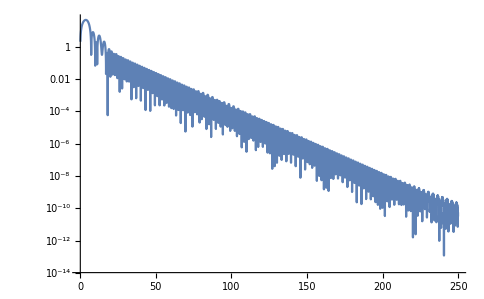

```mathematica
Schwl10data[[;;,2]]= Abs[Schwl10data[[;;,2]]];
ListLogPlot[{Schwl10data},Joined->True,PlotRange->Automatic]
```

## Reissner - Nordstrom + RN - dS

Reissner-Nordstrom M=1, Q=0.8, l=2

## Setup

Horizon locations

```mathematica
M=1; Q=8/10; Λ=0;
rhorplus=M+√(M^2-Q^2)
rhorminus=M-√(M^2-Q^2)
```

8/5

2/5

Invert tortoise

```mathematica
solrn=NDSolve[{r'[rstar]==1-(2 M)/r[rstar]+Q^2/r[rstar]^2- (Λ  r[rstar]^2)/3,r[0]==1.01rhorplus},r,{rstar,-100000,100000},Method->"StiffnessSwitching",PrecisionGoal->MachinePrecision,WorkingPrecision->22, InterpolationOrder-> All ]
```

{{r→InterpolatingFunction[{{-100000.0000000000000000, 100000.0000000000000000}}, <>]}}

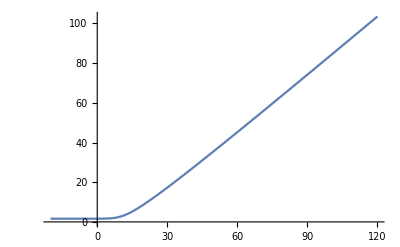

```mathematica
r[rstar_]=r[rstar]/.First[Out[5]];
Plot[{r[x](*,Evaluate[D[r[x],x]]*)},{x,-20,120},PlotRange->Automatic]
```

```mathematica
r[-20]
```

1.60000136620297550556

```mathematica
rhorminus//N
rhorplus//N
```

0.4

1.6

Define V_eff

```mathematica
Vrn[r_,l_]:=(1-(2M)/r+Q^2/r^2- (Λ  r^2)/3) ((l(l+1))/r^2+(2M)/r^3-(2 Q^2)/r^4- (2 Λ)/3);
```

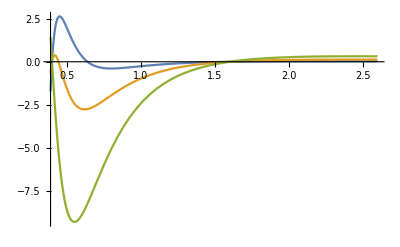
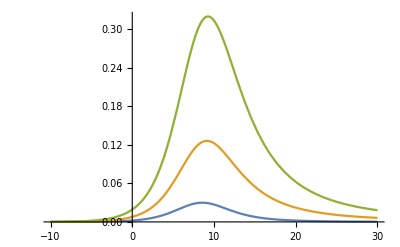

```mathematica
Row[{Plot[{Vrn[r,0],Vrn[r,1],Vrn[r,2]},{r,rhorminus-0.01,rhorplus+1},PlotRange->All],
Plot[{Vrn[r[rstar],0],Vrn[r[rstar],1],Vrn[r[rstar],2]},{rstar,-10,30},PlotRange->All]}]
```

```mathematica
FDrn[iter_,tfinal_,l_]:=(
Clear[ψ,Length1,rstarmax,rstarmin,Δrstar,imax,imin,jmax,σ,center,ψinit2,ψinit];
(*---------Discretization setup----------*)
rstarmax=120;rstarmin=-20;Length1=(rstarmax-rstarmin);
Δrstar=Length1/iter;Δt=Δrstar*0.7;
imax=IntegerPart[N[rstarmax/Δrstar]];imin=IntegerPart[N[rstarmin/Δrstar]];
jmax = IntegerPart[N[tfinal/Δt]];
(*-------messages to check code behavior-------*)
Print[Style["# of Iterations in space = ",Blue,14,Italic,FontFamily->"Courier"],Style[iter,14,Blue,Italic]]
(**)
Print[ Style["(r_*)^max =  ",Blue,14,Italic,FontFamily->"Courier"],Style[rstarmax " , ",Blue,14,Italic,FontFamily->"Courier"],
Style["r^max =  ",Blue,14,Italic,FontFamily->"Courier"], Style[NumberForm[ r[rstarmax],10],Blue,14,Italic,FontFamily->"Courier"]]
Print[ Style["(r_*)^min =  ",Blue,14,Italic,FontFamily->"Courier"],Style[rstarmin " , ",Blue,14,Italic,FontFamily->"Courier"],
Style["r^min =  ",Blue,14,Italic,FontFamily->"Courier"], Style[NumberForm[ r[rstarmin],10],Blue,14,Italic,FontFamily->"Courier"]]
(**)
Print[Style[ "I_max = ",Blue,14,Italic,FontFamily->"Courier"],Style[imax,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style[ "I_min = ",Blue,14,Italic,FontFamily->"Courier"],Style[imin,Blue,14,Italic,FontFamily->"Courier"]]
(**)
Print[Style["Space Discretization step = ",Blue,14,Italic,FontFamily->"Courier"],Style[Δrstar,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["t_final/M = ",Blue,14,Italic,FontFamily->"Courier"],Style[tfinal/M,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style[ "# of Iterations in time = J_max = ",Blue,14,Italic,FontFamily->"Courier"],Style[jmax,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["Time Discretization step = ",Blue,14,Italic,FontFamily->"Courier"],Style[Δt,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["Δt/(Δr_*) = ",Blue,14,Italic,FontFamily->"Courier"],Style[N[Δt/Δrstar],Blue,14,Italic,FontFamily->"Courier"]]
(*-------V effective Discretization------*)
(*VschwDis[i_,l]:=Vschw[r[rstar],l]/.rstar->i Δrstar ;*)
(*--------Initial Condtions--------*) 
σ=5;center=0;
ψ[i_,0]:=ψinit2[rstar] /.rstar->i Δrstar  ;
ψinit2[rstar_]:= Exp[-(rstar-center)^2/(2 σ^2)];
(*-------------------------------*)
ψ[i_,-1]:=ψinit[r[rstar]]  /.rstar->i Δrstar ;
ψinit[r[rstar_]]=0; 
(**)
(*--------Iterating Scheme---------*)
Do[{ψ[i_,j_]:=ψ[i,j]= -ψ[i,j-2]+(Δt/Δrstar)^2(ψ[i+1,j-1]+ψ[i-1,j-1]) + (2-2 (Δt/Δrstar)^2-Vrn[r[i*Δrstar],l] Δt^2) ψ[i,j-1]},{j,1,jmax},{i,imin+1,imax}] 

);
```

## lambda=2

```mathematica
FDrn[1500,350,2]
```

# of Iterations in space = 1500

(r_*)^max =  120  , r^max =  103.5213927

(r_*)^min =  -20  , r^min =  1.600001366

I_max = 1285

I_min = -214

Space Discretization step = 7/75

t_final/M = 350

# of Iterations in time = J_max = 5357

Time Discretization step = 0.0653333

Δt/(Δr_*) = 0.7

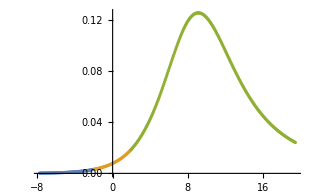

```mathematica
ListPlot[{Table[{i Δrstar  ,Vrn[r[i*Δrstar],1]},{i,-100,-25}],
Table[{i Δrstar  ,Vrn[r[i*Δrstar],1]},{i,-25,25}],
Table[{i Δrstar  ,Vrn[r[i*Δrstar],1]},{i,25,250}]},Joined->False,PlotRange->All]
```

```mathematica
i=-5;
NumberForm[r[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/M,Evaluate[Abs[ψ[i,j]]]},{j,0,jmax+100}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All] ]
```

1.6128731469956757848

$Aborted

```mathematica
RNl2data= Table[{(j Δt)/M ,ψ[i,j]},{j,0,jmax}]  ;
```

```mathematica
Export["RN_l2M1data1.txt" ,RNl2data];
Export["RN_l2M1data2.txt" ,RNl2data,"Table","FieldSeparators"->" "];
```

```mathematica
Clear[RNl2data]
```

```mathematica
RNl2data=Import["RN_l2M1data2.txt","Table"];
```

```mathematica
FilePrint["RN_l2M1data1.txt"]
```

{0., E^(-49/20000)}
{0.049, 1.9949713392700876}
{0.098, 2.9921203792422215}
{0.14700000000000002, 3.9888655088818603}
{0.196, 4.985072166869454}
{0.245, 5.980605856602173}
{0.29400000000000004, 6.975332162377459}
{0.343, 7.969116765510911}
{0.392, 8.96182546037103}
{0.441, 9.953324170346818}
{0.49, 10.943478963760947}
{0.539, 11.932156069718806}
{0.5880000000000001, 12.919221893880824}
{0.637, 13.904543034159355}
{0.686, 14.887986296343197}
{0.735, 15.869418709641637}
{0.784, 16.84870754214149}
{0.8330000000000001, 17.825720316189035}
{0.882, 18.800324823718967}
{0.931, 19.77238914154097}
{0.98, 20.741781646576985}
{1.0290000000000001, 21.70837103103336}
{1.078, 22.672026317486853}
{1.127, 23.632616873857156}
{1.1760000000000002, 24.59001242823613}
{1.225, 25.544083083548646}
{1.274, 26.494699332024137}
{1.323, 27.441732069465626}
{1.372, 28.385052609326582}
{1.421, 29.324532696636492}
{1.47, 30.260044521818013}
{1.5190000000000001, 31.191460734402657}
{1.568, 32.118654456627155}
{1.617, 33.041499296928116}
{1.6660000000000001, 33.959869363420054}
{1.715, 34.87363927746228}
{1.764, 35.78268418736285}
{1.8130000000000002, 36.686879782178615}
{1.862, 37.58610230549301}
{1.911, 38.480228568986774}
{1.96, 39.36913596558602}
{2.009, 40.25270248205392}
{2.0580000000000003, 41.13080671110549}
{2.107, 42.0033278633095}
{2.156, 42.870145778994875}
{2.205, 43.731140940124305}
{2.254, 44.58619448191465}
{2.303, 45.43518820408699}
{2.3520000000000003, 46.27800458188722}
{2.4010000000000002, 47.1145267771114}
{2.45, 47.94463864919595}
{2.499, 48.76822476622925}
{2.548, 49.58517041576872}
{2.597, 50.39536161555081}
{2.646, 51.19868512428309}
{2.6950000000000003, 51.99502845258187}
{2.744, 52.78427987394873}
{2.793, 53.566328435699695}
{2.842, 54.341063969934616}
{2.891, 55.10837710471084}
{2.94, 55.8681592754555}
{2.9890000000000003, 56.62030273650853}
{3.0380000000000003, 57.36470057274675}
{3.087, 58.101246711408095}
{3.136, 58.829835934252145}
{3.185, 59.55036389002647}
{3.234, 60.2627271071183}
{3.283, 60.966823006400396}
{3.3320000000000003, 61.662549914418776}
{3.3810000000000002, 62.34980707699143}
{3.43, 63.0284946731288}
{3.479, 63.698513829233356}
{3.528, 64.35976663374217}
{3.577, 65.01215615242958}
{3.6260000000000003, 65.65558644442575}
{3.6750000000000003, 66.28996257891151}
{3.724, 66.91519065254423}
{3.773, 67.53117780768231}
{3.822, 68.13783225121064}
{3.871, 68.7350632734847}
{3.92, 69.32278126694936}
{3.9690000000000003, 69.90089774426261}
{4.018, 70.46932535596233}
{4.067, 71.02797790783687}
{4.1160000000000005, 71.5767703783527}
{4.165, 72.11561893661286}
{4.214, 72.64444096105875}
{4.263, 73.16315505861762}
{4.312, 73.67168108381145}
{4.361, 74.16994015770904}
{4.41, 74.65785468707004}
{4.4590000000000005, 75.13534838409116}
{4.508, 75.60234628688417}
{4.557, 76.0587747805609}
{4.606, 76.50456161872515}
{4.655, 76.93963594523518}
{4.704000000000001, 77.36392831630403}
{4.753, 77.77737072324665}
{4.8020000000000005, 78.17989661615093}
{4.851, 78.5714409283625}
{4.9, 78.95194010139612}
{4.949, 79.32133211015122}
{4.998, 79.6795564887888}
{5.047000000000001, 80.0265543576314}
{5.096, 80.36226845096377}
{5.1450000000000005, 80.68664314534045}
{5.194, 80.99962448831099}
{5.243, 81.30116022786326}
{5.292, 81.59119984281563}
{5.341, 81.8696945740291}
{5.390000000000001, 82.13659745618638}
{5.439, 82.3918633500871}
{5.488, 82.63544897560361}
{5.537, 82.86731294541144}
{5.586, 83.08741579945128}
{5.635, 83.29572003996759}
{5.684, 83.49219016699783}
{5.7330000000000005, 83.67679271434054}
{5.782, 83.8494962861419}
{5.831, 84.01027159412037}
{5.88, 84.15909149521343}
{5.929, 84.29593102943754}
{5.978000000000001, 84.42076745803841}
{6.027, 84.53358030213332}
{6.0760000000000005, 84.63435138176807}
{6.125, 84.72306485505213}
{6.174, 84.799707257234}
{6.223, 84.86426753992576}
{6.272, 84.91673711059642}
{6.321000000000001, 84.95710987206012}
{6.37, 84.98538226164031}
{6.4190000000000005, 85.00155329006738}
{6.468, 85.00562458032617}
{6.517, 84.99760040634305}
{6.566, 84.97748773114252}
{6.615, 84.94529624432845}
{6.664000000000001, 84.90103839904128}
{6.713, 84.84472944839332}
{6.7620000000000005, 84.776387481038}
{6.811, 84.69603345553644}
{6.86, 84.60369123346939}
{6.909000000000001, 84.49938761129297}
{6.958, 84.38315235070287}
{7.007000000000001, 84.25501820721539}
{7.056, 84.11502095697038}
{7.105, 83.96319942205182}
{7.154, 83.79959549463486}
{7.203, 83.6242541601873}
{7.252000000000001, 83.43722351998495}
{7.301, 83.23855481319991}
{7.3500000000000005, 83.02830243856624}
{7.399, 82.80652397522128}
{7.448, 82.57328020207596}
{7.497, 82.32863511514033}
{7.546, 82.07265594252297}
{7.595000000000001, 81.8054131571491}
{7.644, 81.52698048746323}
{7.6930000000000005, 81.23743492643042}
{7.742, 80.93685673900715}
{7.791, 80.62532946794525}
{7.84, 80.30293993745266}
{7.889, 79.96977825412914}
{7.938000000000001, 79.62593780490955}
{7.987, 79.27151525227792}
{8.036, 78.90661052724855}
{8.085, 78.5313268203145}
{8.134, 78.1457705700851}
{8.183, 77.75005144915545}
{8.232000000000001, 77.34428234692648}
{8.281, 76.92857934936134}
{8.33, 76.50306171588724}
{8.379, 76.06785185377679}
{8.428, 75.62307529019179}
{8.477, 75.16886064162256}
{8.526, 74.70533958017869}
{8.575000000000001, 74.23264679654264}
{8.624, 73.75091996003745}
{8.673, 73.26029967636197}
{8.722, 72.7609294429812}
{8.771, 72.25295560169323}
{8.82, 71.73652728808928}
{8.869, 71.21179637810876}
{8.918000000000001, 70.67891743206214}
{8.967, 70.1380476363188}
{9.016, 69.58934674264562}
{9.065, 69.03297700504427}
{9.114, 68.46910311390536}
{9.163, 67.89789212752505}
{9.212, 67.31951340139992}
{9.261000000000001, 66.7341385157096}
{9.31, 66.14194120087741}
{9.359, 65.5430972607522}
{9.408000000000001, 64.93778449335987}
{9.457, 64.32618260980323}
{9.506, 63.70847315181759}
{9.555, 63.08483940782287}
{9.604000000000001, 62.45546632703993}
{9.653, 61.8205404317121}
{9.702, 61.180249727948926}
{9.751000000000001, 60.53478361555808}
{9.8, 59.884332796783276}
{9.849, 59.229089183748194}
{9.898, 58.56924580464908}
{9.947000000000001, 57.90499670896907}
{9.996, 57.236536872010745}
{10.045, 56.56406209889764}
{10.094000000000001, 55.88776892798031}
{10.143, 55.20785453351294}
{10.192, 54.524516627717276}
{10.241, 53.83795336265994}
{10.290000000000001, 53.14836323224637}
{10.339, 52.455944974165085}
{10.388, 51.760897471501714}
{10.437000000000001, 51.06341965422452}
{10.486, 50.36371040110496}
{10.535, 49.661968442285065}
{10.584, 48.958392262162114}
{10.633000000000001, 48.253180002376936}
{10.682, 47.54652936527828}
{10.731, 46.838637518372614}
{10.780000000000001, 46.12970099976594}
{10.829, 45.419915624259}
{10.878, 44.70947639006582}
{10.927, 43.99857738656617}
{10.976, 43.287411703420474}
{11.025, 42.57617134095166}
{11.074, 41.865047121567066}
{11.123000000000001, 41.15422860228688}
{11.172, 40.44390398870584}
{11.221, 39.73426005060146}
{11.27, 39.025482039102755}
{11.319, 38.31775360524936}
{11.368, 37.61125671999822}
{11.417, 36.90617159596324}
{11.466000000000001, 36.20267661107954}
{11.515, 35.500948234074826}
{11.564, 34.80116095154564}
{11.613000000000001, 34.10348719672512}
{11.662, 33.408097280269295}
{11.711, 32.71515932318691}
{11.76, 32.02483919167529}
{11.809000000000001, 31.3373004336732}
{11.858, 30.6527042173437}
{11.907, 29.971209271815518}
{11.956000000000001, 29.2929718301373}
{12.005, 28.61814557412909}
{12.054, 27.946881581089823}
{12.103, 27.279328272699928}
{12.152000000000001, 26.615631366329193}
{12.201, 25.955933828529968}
{12.25, 25.300375830455007}
{12.299000000000001, 24.64909470533938}
{12.348, 24.002224908368166}
{12.397, 23.359897978918372}
{12.446, 22.722242504847504}
{12.495000000000001, 22.08938408869666}
{12.544, 21.46144531605688}
{12.593, 20.838545726307114}
{12.642000000000001, 20.22080178555027}
{12.691, 19.608326861469006}
{12.74, 19.001231200158788}
{12.789, 18.399621905225697}
{12.838000000000001, 17.803602919183316}
{12.887, 17.21327500684493}
{12.936, 16.62873574052079}
{12.985000000000001, 16.050079487208837}
{13.034, 15.477397397998894}
{13.083, 14.910777399548182}
{13.132, 14.350304187328282}
{13.181000000000001, 13.796059220650818}
{13.23, 13.248120719738504}
{13.279, 12.70656366487736}
{13.328000000000001, 12.171459797338658}
{13.377, 11.642877621873378}
{13.426, 11.120882410972833}
{13.475, 10.605536211109339}
{13.524000000000001, 10.096897850791882}
{13.573, 9.595022950127932}
{13.622, 9.099963931902328}
{13.671000000000001, 8.611770034415926}
{13.72, 8.130487326082658}
{13.769, 7.656158721488755}
{13.818000000000001, 7.188823998773638}
{13.867, 6.728519818528124}
{13.916, 6.275279744351912}
{13.965, 5.829134264863835}
{14.014000000000001, 5.390110816898031}
{14.063, 4.958233809936028}
{14.112, 4.533524651986982}
{14.161000000000001, 4.116001776882508}
{14.21, 3.7056806727201996}
{14.259, 3.302573911343911}
{14.308, 2.906691179013766}
{14.357000000000001, 2.5180393083571175}
{14.406, 2.1366223114223866}
{14.455, 1.762441413633144}
{14.504000000000001, 1.3954950886944897}
{14.553, 1.035779094611022}
{14.602, 0.6832865107559953}
{14.651, 0.3380077757460923}
{14.700000000000001, -0.00006927396399986074}
{14.749, -0.3309593646035164}
{14.798, -0.6546797446341743}
{14.847000000000001, -0.971250143520773}
{14.896, -1.2806927299450908}
{14.945, -1.5830320693979583}
{14.994, -1.8782950809599133}
{15.043000000000001, -2.166510993334895}
{15.092, -2.4477113004083444}
{15.141, -2.7219297164002048}
{15.190000000000001, -2.9892021304125334}
{15.239, -3.2495665603062105}
{15.288, -3.5030631061570845}
{15.337, -3.7497339034790125}
{15.386000000000001, -3.98962307605356}
{15.435, -4.222776688188599}
{15.484, -4.44924269659083}
{15.533000000000001, -4.6690709021412395}
{15.582, -4.882312901503374}
{15.631, -5.089022038298561}
{15.68, -5.289253353911283}
{15.729000000000001, -5.483063538269308}
{15.778, -5.670510880668125}
{15.827, -5.85165522035554}
{15.876000000000001, -6.026557896791167}
{15.925, -6.1952816998977305}
{15.974, -6.357890820507901}
{16.023, -6.514450800783033}
{16.072, -6.66502848440419}
{16.121000000000002, -6.809691966764487}
{16.17, -6.948510545450305}
{16.219, -7.081554670884752}
{16.268, -7.208895896871589}
{16.317, -7.330606831163016}
{16.366, -7.4467610863769895}
{16.415, -7.557433231242663}
{16.464000000000002, -7.662698741888654}
{16.513, -7.7626339531855235}
{16.562, -7.857316010469267}
{16.611, -7.946822821735643}
{16.66, -8.031233010037734}
{16.709, -8.11062586598447}
{16.758, -8.185081300620107}
{16.807000000000002, -8.25467979887638}
{16.856, -8.3195023733986}
{16.905, -8.379630518554997}
{16.954, -8.435146164815418}
{17.003, -8.486131633751304}
{17.052, -8.532669593561893}
{17.101, -8.574843014900871}
{17.150000000000002, -8.612735127078512}
{17.199, -8.646429374894396}
{17.248, -8.67600937610782}
{17.297, -8.701558879337364}
{17.346, -8.723161722370582}
{17.395, -8.740901791099722}
{17.444, -8.754862979166703}
{17.493000000000002, -8.765129148156428}
{17.542, -8.771784088254092}
{17.591, -8.774911479523304}
{17.64, -8.774594853936572}
{17.689, -8.7709175580583}
{17.738, -8.763962716255778}
{17.787, -8.753813194525435}
{17.836000000000002, -8.74055156509075}
{17.885, -8.724260071742279}
{17.934, -8.705020595779768}
{17.983, -8.682914622565898}
{18.032, -8.658023208845032}
{18.081, -8.63042695087277}
{18.13, -8.600205953232441}
{18.179000000000002, -8.56743979827143}
{18.228, -8.532207516273267}
{18.277, -8.494587556477137}
{18.326, -8.45465775887135}
{18.375, -8.4124953266363}
{18.424, -8.368176799284896}
{18.473, -8.32177802664974}
{18.522000000000002, -8.273374143717207}
{18.571, -8.22303954616145}
{18.62, -8.170847866545188}
{18.669, -8.116871951336407}
{18.718, -8.061183838817364}
{18.767, -8.003854737753215}
{18.816000000000003, -7.94495500671308}
{18.865000000000002, -7.884554134159917}
{18.914, -7.822720719447323}
{18.963, -7.759522454631708}
{19.012, -7.695026106937927}
{19.061, -7.629297501941726}
{19.11, -7.562401507647628}
{19.159000000000002, -7.494402019426183}
{19.208000000000002, -7.4253619456153634}
{19.257, -7.355343193786907}
{19.306, -7.284406657876413}
{19.355, -7.212612206203017}
{19.404, -7.140018670169545}
{19.453, -7.06668383357702}
{19.502000000000002, -6.992664422753804}
{19.551000000000002, -6.91801609759036}
{19.6, -6.842793443275751}
{19.649, -6.767049962601091}
{19.698, -6.690838069011829}
{19.747, -6.6142090805648355}
{19.796, -6.537213214612999}
{19.845000000000002, -6.459899583017193}
{19.894000000000002, -6.382316188026872}
{19.943, -6.304509919043394}
{19.992, -6.22652655013773}
{20.041, -6.148410738068845}
{20.09, -6.070206020882243}
{20.139, -5.991954817344491}
{20.188000000000002, -5.9136984271534185}
{20.237000000000002, -5.835477031637614}
{20.286, -5.757329694948064}
{20.335, -5.679294366015069}
{20.384, -5.601407881288223}
{20.433, -5.523705967967397}
{20.482, -5.446223247646893}
{20.531000000000002, -5.368993240635902}
{20.580000000000002, -5.292048371049522}
{20.629, -5.215419972399131}
{20.678, -5.139138293530759}
{20.727, -5.063232505140762}
{20.776, -4.987730707028096}
{20.825, -4.912659935853761}
{20.874000000000002, -4.838046173197534}
{20.923000000000002, -4.763914354090587}
{20.972, -4.690288376231608}
{21.021, -4.617191109711828}
{21.07, -4.544644406998529}
{21.119, -4.472669113295862}
{21.168, -4.401285077521077}
{21.217000000000002, -4.33051116378272}
{21.266000000000002, -4.260365263087388}
{21.315, -4.190864305330579}
{21.364, -4.122024271823791}
{21.413, -4.0538602083073165}
{21.462, -3.986386238168326}
{21.511, -3.9196155758564775}
{21.560000000000002, -3.8535605407483056}
{21.609, -3.788232571471748}
{21.658, -3.7236422404181373}
{21.707, -3.6597992683730416}
{21.756, -3.59671253950209}
{21.805, -3.534390116761864}
{21.854, -3.4728392574851576}
{21.903000000000002, -3.4120664290159626}
{21.952, -3.3520773246013627}
{22.001, -3.2928768796629044}
{22.05, -3.2344692882326007}
{22.099, -3.1768580193812848}
{22.148, -3.1200458338045967}
{22.197, -3.0640348007315303}
{22.246000000000002, -3.008826314988714}
{22.295, -2.9544211140128587}
{22.344, -2.90081929492439}
{22.393, -2.848020331855566}
{22.442, -2.7960230934229013}
{22.491, -2.744825860116886}
{22.54, -2.69442634166374}
{22.589000000000002, -2.6448216945641723}
{22.638, -2.596008539759176}
{22.687, -2.547982980194002}
{22.736, -2.5007406182763225}
{22.785, -2.4542765734277316}
{22.834, -2.408585499736515}
{22.883, -2.363661603498163}
{22.932000000000002, -2.319498660586369}
{22.981, -2.2760900338320362}
{23.03, -2.233428690468238}
{23.079, -2.1915072194572094}
{23.128, -2.150317848599083}
{23.177, -2.1098524615663687}
{23.226000000000003, -2.070102614960484}
{23.275000000000002, -2.0310595552457227}
{23.324, -1.9927142354301808}
{23.373, -1.9550573315969213}
{23.422, -1.9180792594068379}
{23.471, -1.8817701904730213}
{23.52, -1.8461200684594552}
{23.569000000000003, -1.8111186249638154}
{23.618000000000002, -1.7767553953178339}
{23.667, -1.7430197342503149}
{23.716, -1.7099008312616868}
{23.765, -1.6773877257273968}
{23.814, -1.6454693218638214}
{23.863, -1.6141344035446783}
{23.912000000000003, -1.5833716488237528}
{23.961000000000002, -1.5531696441423595}
{24.01, -1.5235168983456313}
{24.059, -1.49440185653419}
{24.108, -1.4658129136228855}
{24.157, -1.437738427551264}
{24.206, -1.410166732252282}
{24.255000000000003, -1.383086150438692}
{24.304000000000002, -1.356485006101829}
{24.353, -1.3303516366398682}
{24.402, -1.3046744046982217}
{24.451, -1.2794417098079112}
{24.5, -1.254641999745268}
{24.549, -1.230263781509215}
{24.598000000000003, -1.2062956319699698}
{24.647000000000002, -1.1827262082943124}
{24.696, -1.1595442581037725}
{24.745, -1.1367386292487167}
{24.794, -1.1142982792196354}
{24.843, -1.0922122843120607}
{24.892, -1.0704698485373432}
{24.941000000000003, -1.04906031215733}
{24.990000000000002, -1.0279731598296775}
{25.039, -1.0071980284829039}
{25.088, -0.9867247149504116}
{25.137, -0.9665431832453363}
{25.186, -0.9466435714280849}
{25.235, -0.9270161981793175}
{25.284000000000002, -0.9076515691438318}
{25.333000000000002, -0.8885403829401428}
{25.382, -0.8696735367545719}
{25.431, -0.8510421316170397}
{25.48, -0.8326374774570846}
{25.529, -0.8144510978567094}
{25.578, -0.7964747343902041}
{25.627000000000002, -0.7787003506241174}
{25.676000000000002, -0.7611201359032248}
{25.725, -0.7437265088684628}
{25.774, -0.7265121205749796}
{25.823, -0.7094698572527283}
{25.872, -0.6925928428551732}
{25.921, -0.6758744413770669}
{25.970000000000002, -0.6593082587956045}
{26.019000000000002, -0.642888144641845}
{26.068, -0.6266081933587081}
{26.117, -0.6104627454650399}
{26.166, -0.5944463883756824}
{26.215, -0.578553956846558}
{26.264, -0.5627805332018055}
{26.313000000000002, -0.5471214474016661}
{26.362000000000002, -0.531572276806544}
{26.411, -0.5161288455690122}
{26.46, -0.5007872238018292}
{26.509, -0.4855437266177776}
{26.558, -0.4703949129112837}
{26.607, -0.45533758377935957}
{26.656000000000002, -0.4403687807123156}
{26.705000000000002, -0.42548578368299944}
{26.754, -0.4106861090268928}
{26.803, -0.39596750698129646}
{26.852, -0.3813279589891484}
{26.901, -0.36676567492326667}
{26.95, -0.3522790901519793}
{26.999000000000002, -0.33786686229147156}
{27.048000000000002, -0.3235278677199936}
{27.097, -0.30926119802963903}
{27.146, -0.29506615636962014}
{27.195, -0.2809422535107748}
{27.244, -0.2668892036725306}
{27.293000000000003, -0.2529069203002724}
{27.342000000000002, -0.23899551178235803}
{27.391000000000002, -0.2251552769284695}
{27.44, -0.2113867002149941}
{27.489, -0.19769044698997698}
{27.538, -0.18406735866281887}
{27.587, -0.17051844769966373}
{27.636000000000003, -0.1570448923946082}
{27.685000000000002, -0.14364803160658407}
{27.734, -0.13032935952216904}
{27.783, -0.11709052027139552}
{27.832, -0.10393330233248166}
{27.881, -0.09085963290594841}
{27.93, -0.07787157235132541}
{27.979000000000003, -0.06497130852575957}
{28.028000000000002, -0.052161150928705546}
{28.077, -0.039443524817931626}
{28.126, -0.026820965420011188}
{28.175, -0.014296112092159766}
{28.224, -0.0018717023109691509}
{28.273, 0.010449434367110494}
{28.322000000000003, 0.02266438222397226}
{28.371000000000002, 0.03477014529757694}
{28.42, 0.04676365344847341}
{28.469, 0.058641768455240675}
{28.518, 0.07040128996722755}
{28.567, 0.08203896140906507}
{28.616, 0.09355147600649338}
{28.665000000000003, 0.10493548284235006}
{28.714000000000002, 0.11618759275397895}
{28.763, 0.1273043841369781}
{28.812, 0.13828240884005757}
{28.861, 0.14911819809146856}
{28.91, 0.1598082682565037}
{28.959, 0.17034912645906009}
{29.008000000000003, 0.1807372762618115}
{29.057000000000002, 0.19096922337910008}
{29.106, 0.20104148121602064}
{29.155, 0.210950576233273}
{29.204, 0.22069305333629963}
{29.253, 0.2302654812975553}
{29.302, 0.23966445800537736}
{29.351000000000003, 0.24888661550513458}
{29.400000000000002, 0.2579286250291152}
{29.449, 0.26678720205873974}
{29.498, 0.2754591112186545}
{29.547, 0.28394117093506815}
{29.596, 0.29223025804674474}
{29.645, 0.3003233124459645}
{29.694000000000003, 0.30821734156110436}
{29.743000000000002, 0.3159094245814435}
{29.792, 0.32339671659859703}
{29.841, 0.33067645277350866}
{29.89, 0.3377459523586882}
{29.939, 0.3446026224473774}
{29.988, 0.35124396160437293}
{30.037000000000003, 0.35766756351555234}
{30.086000000000002, 0.36387112050904147}
{30.135, 0.3698524267948278}
{30.184, 0.37560938155320106}
{30.233, 0.3811399920328278}
{30.282, 0.3864423765389076}
{30.331, 0.3915147671379395}
{30.380000000000003, 0.39635551218117077}
{30.429000000000002, 0.4009630788263196}
{30.478, 0.40533605546916096}
{30.527, 0.40947315389670363}
{30.576, 0.413373211232575}
{30.625, 0.41703519186702476}
{30.674, 0.4204581893166807}
{30.723000000000003, 0.42364142781718}
{30.772000000000002, 0.42658426368618324}
{30.821, 0.42928618665572116}
{30.87, 0.43174682115350954}
{30.919, 0.4339659273339599}
{30.968, 0.4359434018628425}
{31.017, 0.43767927865484957}
{31.066000000000003, 0.4391737295780145}
{31.115000000000002, 0.4404270649294831}
{31.164, 0.44143973365379546}
{31.213, 0.4422123234971315}
{31.262, 0.4427455611443819}
{31.311, 0.44304031215310596}
{31.36, 0.44309758062461385}
{31.409000000000002, 0.44291850879422917}
{31.458000000000002, 0.44250437661808945}
{31.507, 0.4418566011854077}
{31.556, 0.4409767358683278}
{31.605, 0.43986646937492363}
{31.654, 0.4385276248097697}
{31.703000000000003, 0.43696215859051396}
{31.752000000000002, 0.43517215910833323}
{31.801000000000002, 0.43315984527712853}
{31.85, 0.4309275650986662}
{31.899, 0.4284777941151086}
{31.948, 0.4258131336169248}
{31.997, 0.42293630872726645}
{32.046, 0.41985016650828}
{32.095, 0.41655767398642807}
{32.144, 0.41306191594946134}
{32.193, 0.40936609260998397}
{32.242000000000004, 0.40547351729452336}
{32.291000000000004, 0.40138761408264045}
{32.34, 0.39711191523825123}
{32.389, 0.39265005850053797}
{32.438, 0.3880057844017899}
{32.487, 0.38318293356503186}
{32.536, 0.37818544381803826}
{32.585, 0.37301734716302787}
{32.634, 0.36768276677284395}
{32.683, 0.36218591399476757}
{32.732, 0.35653108519777243}
{32.781, 0.35072265847480366}
{32.83, 0.3447650903696207}
{32.879, 0.3386629126367822}
{32.928000000000004, 0.3324207288742392}
{32.977000000000004, 0.3260432110135197}
{33.026, 0.319535095831432}
{33.075, 0.3129011815177829}
{33.124, 0.3061463241462836}
{33.173, 0.2992754340087225}
{33.222, 0.29229347196676175}
{33.271, 0.28520544587969504}
{33.32, 0.2780164069666955}
{33.369, 0.2707314460410043}
{33.418, 0.2633556897573989}
{33.467, 0.2558942969525216}
{33.516, 0.24835245495101188}
{33.565000000000005, 0.2407353757549137}
{33.614000000000004, 0.23304829224177473}
{33.663000000000004, 0.2252964544693892}
{33.712, 0.21748512597713346}
{33.761, 0.20961957998435987}
{33.81, 0.20170509559296268}
{33.859, 0.19374695410724926}
{33.908, 0.18575043538004904}
{33.957, 0.177720814071648}
{34.006, 0.16966335590854653}
{34.055, 0.16158331406715506}
{34.104, 0.15348592561194932}
{34.153, 0.14537640786403574}
{34.202, 0.13725995476550182}
{34.251000000000005, 0.1291417333731501}
{34.300000000000004, 0.12102688043285806}
{34.349000000000004, 0.11292049890342042}
{34.398, 0.10482765447280996}
{34.447, 0.09675337220537683}
{34.496, 0.08870263329340482}
{34.545, 0.08068037177819425}
{34.594, 0.07269147126084062}
{34.643, 0.06474076174273521}
{34.692, 0.0568330165915191}
{34.741, 0.048972949497389485}
{34.79, 0.0411652114171857}
{34.839, 0.0334143876442566}
{34.888, 0.02572499502178035}
{34.937000000000005, 0.01810147916763636}
{34.986000000000004, 0.010548211686176489}
{35.035000000000004, 0.003069487499494065}
{35.084, -0.004330477663123902}
{35.133, -0.011647549743042232}
{35.182, -0.018877678843104786}
{35.231, -0.02601690160745277}
{35.28, -0.03306134343191208}
{35.329, -0.04000722062084561}
{35.378, -0.046850842555626306}
{35.427, -0.05358861376241152}
{35.476, -0.06021703580292487}
{35.525, -0.06673270909172344}
{35.574, -0.07313233472254324}
{35.623000000000005, -0.07941271620573281}
{35.672000000000004, -0.08557076102478872}
{35.721000000000004, -0.09160348210050534}
{35.77, -0.09750799926038138}
{35.819, -0.1032815406320351}
{35.868, -0.10892144385560698}
{35.917, -0.11442515718654435}
{35.966, -0.11979024059859736}
{36.015, -0.12501436682434078}
{36.064, -0.1300953222180924}
{36.113, -0.1350310074939353}
{36.162, -0.13981943845789616}
{36.211, -0.14445874669152856}
{36.26, -0.14894718006468016}
{36.309000000000005, -0.15328310311024831}
{36.358000000000004, -0.15746499738605457}
{36.407000000000004, -0.16149146180200677}
{36.456, -0.16536121278645957}
{36.505, -0.16907308430391169}
{36.554, -0.1726260278519206}
{36.603, -0.17601911243679785}
{36.652, -0.17925152440147518}
{36.701, -0.1823225670967706}
{36.75, -0.18523166052328188}
{36.799, -0.18797834096481078}
{36.848, -0.19056226048957495}
{36.897, -0.19298318628981534}
{36.946, -0.19524099998293423}
{36.995000000000005, -0.19733569691576502}
{37.044000000000004, -0.19926738535446364}
{37.093, -0.20103628551095937}
{37.142, -0.20264272852174006}
{37.191, -0.20408715543998743}
{37.24, -0.20537011613279738}
{37.289, -0.20649226801616227}
{37.338, -0.20745437473322595}
{37.387, -0.2082573048546664}
{37.436, -0.20890203050498837}
{37.485, -0.20938962583085766}
{37.534, -0.20972126540390398}
{37.583, -0.20989822265261507}
{37.632000000000005, -0.2099218682417804}
{37.681000000000004, -0.20979366830141766}
{37.730000000000004, -0.2095151825821371}
{37.779, -0.2090880626447336}
{37.828, -0.20851405001914902}
{37.877, -0.2077949742231455}
{37.926, -0.20693275070032574}
{37.975, -0.20592937879574325}
{38.024, -0.2047869397225901}
{38.073, -0.20350759440151664}
{38.122, -0.20209358121337243}
{38.171, -0.2005472137910208}
{38.22, -0.19887087882324553}
{38.269, -0.19706703374661366}
{38.318000000000005, -0.19513820434630924}
{38.367000000000004, -0.19308698239583072}
{38.416000000000004, -0.1909160233287097}
{38.465, -0.18862804381552428}
{38.514, -0.18622581924699505}
{38.563, -0.1837121812541281}
{38.612, -0.1810900152788844}
{38.661, -0.17836225806921674}
{38.71, -0.17553189507907394}
{38.759, -0.17260195790220145}
{38.808, -0.16957552177314839}
{38.857, -0.1664557030129489}
{38.906, -0.16324565638045474}
{38.955, -0.15994857245301303}
{39.004000000000005, -0.15656767508905506}
{39.053000000000004, -0.15310621885659492}
{39.102000000000004, -0.1495674863699084}
{39.151, -0.1459547856500128}
{39.2, -0.14227144757943702}
{39.249, -0.1385208233446234}
{39.298, -0.13470628179099836}
{39.347, -0.13083120679558388}
{39.396, -0.12689899474381214}
{39.445, -0.12291305201562419}
{39.494, -0.1188767923905032}
{39.543, -0.11479363446333363}
{39.592, -0.11066699917195426}
{39.641, -0.10650030735526121}
{39.690000000000005, -0.10229697723813352}
{39.739000000000004, -0.09806042192012913}
{39.788000000000004, -0.09379404698086218}
{39.837, -0.08950124813651107}
{39.886, -0.08518540883263122}
{39.935, -0.08084989783357363}
{39.984, -0.0764980669309854}
{40.033, -0.07213324872290809}
{40.082, -0.0677587543401406}
{40.131, -0.06337787116224802}
{40.18, -0.05899386065252113}
{40.229, -0.05460995628144669}
{40.278, -0.05022936140962224}
{40.327, -0.04585524715386474}
{40.376000000000005, -0.04149075036986418}
{40.425000000000004, -0.03713897173942014}
{40.474000000000004, -0.03280297383015648}
{40.523, -0.02848577913256231}
{40.572, -0.024190368209086162}
{40.621, -0.01991967796187762}
{40.67, -0.015676599886654367}
{40.719, -0.011463978298745523}
{40.768, -0.007284608664865929}
{40.817, -0.003141236065499882}
{40.866, 0.0009634463426260072}
{40.915, 0.005026798896405444}
{40.964, 0.009046236898560468}
{41.013, 0.013019231949413328}
{41.062000000000005, 0.016943313264301374}
{41.111000000000004, 0.020816069027021277}
{41.160000000000004, 0.024635147655372218}
{41.209, 0.028398258918850696}
{41.258, 0.03210317502766553}
{41.307, 0.035747731760459006}
{41.356, 0.03932982951524985}
{41.405, 0.042847434207638625}
{41.454, 0.04629857812624142}
{41.503, 0.049681360828397504}
{41.552, 0.052993949971294044}
{41.601, 0.05623458198807419}
{41.65, 0.05940156270767494}
{41.699, 0.06249326801538858}
{41.748000000000005, 0.06550814446169612}
{41.797000000000004, 0.06844470971622882}
{41.846000000000004, 0.07130155295279324}
{41.895, 0.07407733527463209}
{41.944, 0.07677079010134977}
{41.993, 0.07938072340342445}
{42.042, 0.08190601385599001}
{42.091, 0.08434561303135242}
{42.14, 0.08669854556690464}
{42.189, 0.0889639091854545}
{42.238, 0.09114087462418712}
{42.287, 0.093228685599835}
{42.336, 0.0952266587628883}
{42.385000000000005, 0.09713418351113273}
{42.434000000000005, 0.09895072170256682}
{42.483000000000004, 0.10067580740127412}
{42.532000000000004, 0.10230904662581365}
{42.581, 0.1038501169656885}
{42.63, 0.10529876708921652}
{42.679, 0.10665481628034341}
{42.728, 0.10791815399117152}
{42.777, 0.10908873927311277}
{42.826, 0.11016660009287531}
{42.875, 0.1111518326726563}
{42.924, 0.11204460085875086}
{42.973, 0.11284513538093062}
{43.022, 0.1135537329915296}
{43.071000000000005, 0.11417075562330954}
{43.120000000000005, 0.11469662958780705}
{43.169000000000004, 0.11513184467812253}
{43.218, 0.11547695314784688}
{43.267, 0.11573256870261799}
{43.316, 0.11589936554323199}
{43.365, 0.11597807732814946}
{43.414, 0.11596949601034603}
{43.463, 0.11587447068021035}
{43.512, 0.11569390646991051}
{43.561, 0.11542876339296879}
{43.61, 0.11508005505803852}
{43.659, 0.1146488473818728}
{43.708, 0.11413625737254407}
{43.757000000000005, 0.11354345186438675}
{43.806000000000004, 0.11287164612857097}
{43.855000000000004, 0.11212210247572493}
{43.904, 0.11129612893629007}
{43.953, 0.11039507790961861}
{44.002, 0.1094203446917743}
{44.051, 0.10837336598815117}
{44.1, 0.10725561850994404}
{44.149, 0.10606861755658134}
{44.198, 0.10481391548140158}
{44.247, 0.1034931001348429}
{44.296, 0.10210779339618054}
{44.345, 0.10065964970852866}
{44.394, 0.09915035450316431}
{44.443000000000005, 0.09758162259414221}
{44.492000000000004, 0.09595519666460717}
{44.541000000000004, 0.0942728457733904}
{44.59, 0.09253636375837844}
{44.639, 0.09074756760317454}
{44.688, 0.08890829589715588}
{44.737, 0.08702040733243344}
{44.786, 0.08508577910629783}
{44.835, 0.08310630528016578}
{44.884, 0.08108389523204612}
{44.933, 0.07902047216192856}
{44.982, 0.07691797151265609}
{45.031, 0.07477833934091761}
{45.08, 0.07260353078029186}
{45.129000000000005, 0.07039550857232676}
{45.178000000000004, 0.06815624152421045}
{45.227000000000004, 0.06588770291071822}
{45.276, 0.06359186896520037}
{45.325, 0.061270717452602895}
{45.374, 0.05892622618119478}
{45.423, 0.0565603714534721}
{45.472, 0.05417512660167031}
{45.521, 0.05177246061789276}
{45.57, 0.04935433673569269}
{45.619, 0.04692271094648875}
{45.668, 0.044479530595009135}
{45.717, 0.04202673308065183}
{45.766, 0.03956624452359233}
{45.815000000000005, 0.03709997836199338}
{45.864000000000004, 0.03462983402132888}
{45.913000000000004, 0.03215769569945059}
{45.962, 0.029685431130284837}
{46.011, 0.027214890275800083}
{46.06, 0.024747904081959923}
{46.109, 0.02228628335849041}
{46.158, 0.01983181765145852}
{46.207, 0.01738627404229849}
{46.256, 0.014951396001733733}
{46.305, 0.01252890237377605}
{46.354, 0.010120486366764395}
{46.403, 0.007727814469986639}
{46.452000000000005, 0.005352525415265283}
{46.501000000000005, 0.0029962292730653607}
{46.550000000000004, 0.0006605065698334178}
{46.599000000000004, -0.0016530926689015213}
{46.648, -0.003943049841112172}
{46.697, -0.006207878553838183}
{46.746, -0.00844612537359216}
{46.795, -0.010656370649733894}
{46.844, -0.012837229314692632}
{46.893, -0.014987351546665242}
{46.942, -0.017105423383699487}
{46.991, -0.01919016740831641}
{47.04, -0.021240343420354413}
{47.089, -0.023254748973756394}
{47.138000000000005, -0.025232219852109217}
{47.187000000000005, -0.027171630611331557}
{47.236000000000004, -0.029071895121944365}
{47.285000000000004, -0.030931966978447842}
{47.334, -0.03275083983564192}
{47.383, -0.03452754780785838}
{47.432, -0.03626116587914803}
{47.481, -0.03795081018546261}
{47.53, -0.03959563821288322}
{47.579, -0.041194849053640174}
{47.628, -0.04274768368427377}
{47.677, -0.04425342512229984}
{47.726, -0.0457113984890212}
{47.775, -0.04712097112417841}
{47.824000000000005, -0.04848155273368164}
{47.873000000000005, -0.04979259542400915}
{47.922000000000004, -0.051053593633965166}
{47.971000000000004, -0.052264084111401814}
{48.02, -0.05342364593341584}
{48.069, -0.054531900422942085}
{48.118, -0.05558851095529787}
{48.167, -0.05659318280205777}
{48.216, -0.05754566302803697}
{48.265, -0.058445740295726994}
{48.314, -0.05929324455371329}
{48.363, -0.06008804675414963}
{48.412, -0.06083005863209837}
{48.461, -0.06151923240457354}
{48.510000000000005, -0.06215556034915133}
{48.559000000000005, -0.06273907440283585}
{48.608000000000004, -0.06326984583048277}
{48.657000000000004, -0.06374798482613792}
{48.706, -0.06417363999116246}
{48.755, -0.06454699782345495}
{48.804, -0.064868282282727}
{48.853, -0.0651377543026086}
{48.902, -0.06535571117843558}
{48.951, -0.06552248595685756}
{49., -0.06563844690677514}
{49.049, -0.06570399695143837}
{49.098, -0.06571957297666957}
{49.147, -0.06568564513161965}
{49.196000000000005, -0.06560271621493947}
{49.245000000000005, -0.06547132103673911}
{49.294000000000004, -0.06529202565863157}
{49.343, -0.0650654266170902}
{49.392, -0.0647921502350502}
{49.441, -0.06447285192401844}
{49.49, -0.06410821536769525}
{49.539, -0.06369895167987998}
{49.588, -0.0632457986522045}
{49.637, -0.06274952000704123}
{49.686, -0.06221090453675914}
{49.735, -0.06163076520847936}
{49.784, -0.06100993835892921}
{49.833, -0.06034928290890715}
{49.882000000000005, -0.059649679470335885}
{49.931000000000004, -0.05891202941042214}
{49.980000000000004, -0.05813725400483216}
{50.029, -0.057326293624443345}
{50.078, -0.056480106822270955}
{50.127, -0.05559966936970497}
{50.176, -0.05468597337937786}
{50.225, -0.05374002647482}
{50.274, -0.052762850868995494}
{50.323, -0.05175548238506304}
{50.372, -0.050718969560274184}
{50.421, -0.049654372809081554}
{50.47, -0.04856276350481186}
{50.519000000000005, -0.04744522299714055}
{50.568000000000005, -0.04630284170802807}
{50.617000000000004, -0.04513671829833018}
{50.666000000000004, -0.04394795876361639}
{50.715, -0.04273767546026514}
{50.764, -0.04150698620430651}
{50.813, -0.04025701345122375}
{50.862, -0.03898888341626381}
{50.911, -0.037703725120393196}
{50.96, -0.036402669502421825}
{51.009, -0.03508684862120918}
{51.058, -0.03375739481021576}
{51.107, -0.03241543975391981}
{51.156, -0.03106211362298042}
{51.205000000000005, -0.029698544307409043}
{51.254000000000005, -0.028325856614436432}
{51.303000000000004, -0.02694517138536976}
{51.352000000000004, -0.0255576046628773}
{51.401, -0.024164266962776737}
{51.45, -0.022766262523294147}
{51.499, -0.02136468847161151}
{51.548, -0.019960634031874973}
{51.597, -0.018555179842579133}
{51.646, -0.01714939726424767}
{51.695, -0.015744347603857886}
{51.744, -0.01434108137139292}
{51.793, -0.012940637649081618}
{51.842, -0.011544043463567376}
{51.891000000000005, -0.010152313075313482}
{51.940000000000005, -0.00876644729060986}
{51.989000000000004, -0.0073874328881617605}
{52.038000000000004, -0.006016242060949489}
{52.087, -0.004653831776702429}
{52.136, -0.003301143151220389}
{52.185, -0.0019591009367702205}
{52.234, -0.0006286130378384061}
{52.283, 0.0006894300521337903}
{52.332, 0.001994155811092276}
{52.381, 0.003284710134707062}
{52.43, 0.00456025774373001}
{52.479, 0.005819982666916204}
{52.528, 0.007063088730828649}
{52.577000000000005, 0.008288799938251212}
{52.626000000000005, 0.00949636079675932}
{52.675000000000004, 0.010685036718461544}
{52.724000000000004, 0.011854114436098196}
{52.773, 0.013002902311703765}
{52.822, 0.014130730585422998}
{52.871, 0.015236951690317819}
{52.92, 0.016320940592610196}
{52.969, 0.017382095029682583}
{53.018, 0.018419835679160952}
{53.067, 0.019433606388121572}
{53.116, 0.020422874436344923}
{53.165, 0.021387130703642836}
{53.214, 0.02232588976014297}
{53.263000000000005, 0.023238690010171734}
{53.312000000000005, 0.0241250938782616}
{53.361000000000004, 0.024984687906676656}
{53.410000000000004, 0.025817082768896098}
{53.459, 0.026621913329592184}
{53.508, 0.02739883875402937}
{53.557, 0.028147542537253066}
{53.606, 0.0288677324433992}
{53.655, 0.029559140484123708}
{53.704, 0.03022152295316439}
{53.753, 0.03085466038970799}
{53.802, 0.031458357446969544}
{53.851, 0.032032442792004755}
{53.9, 0.032576769067672554}
{53.949000000000005, 0.03309121279335268}
{53.998000000000005, 0.033575674167277185}
{54.047000000000004, 0.03403007689181684}
{54.096000000000004, 0.03445436806587687}
{54.145, 0.03484851802650111}
{54.194, 0.03521252008982324}
{54.243, 0.03554639030664394}
{54.292, 0.03585016728914994}
{54.341, 0.03612391199761053}
{54.39, 0.03636770742533406}
{54.439, 0.036581658289933754}
{54.488, 0.036765890798919044}
{54.537, 0.036920552386289364}
{54.586000000000006, 0.03704581134737775}
{54.635000000000005, 0.03714185647162857}
{54.684000000000005, 0.03720889675198661}
{54.733000000000004, 0.037247161076614584}
{54.782000000000004, 0.0372568978200964}
{54.831, 0.037238374424208076}
{54.88, 0.03719187705644414}
{54.929, 0.03711771026219431}
{54.978, 0.03701619651894356}
{55.027, 0.036887675772003074}
{55.076, 0.03673250504807932}
{55.125, 0.03655105807353052}
{55.174, 0.03634372479827842}
{55.223, 0.03611091089367057}
{55.272000000000006, 0.035853037327368865}
{55.321000000000005, 0.035570539953586625}
{55.370000000000005, 0.03526386901351838}
{55.419000000000004, 0.03493348860257698}
{55.468, 0.034579876213045015}
{55.517, 0.034203522302382106}
{55.566, 0.03380492977712316}
{55.615, 0.03338461343684246}
{55.664, 0.032943099491056164}
{55.713, 0.03248092511163646}
{55.762, 0.03199863790706788}
{55.811, 0.031496795350534894}
{55.86, 0.030975964277651608}
{55.909, 0.03043672042900951}
{55.958000000000006, 0.029879647921580425}
{56.007000000000005, 0.02930533866822188}
{56.056000000000004, 0.028714391862680256}
{56.105000000000004, 0.028107413518090648}
{56.154, 0.02748501594214974}
{56.203, 0.026847817155335466}
{56.252, 0.02619644036963652}
{56.301, 0.025531513528563702}
{56.35, 0.02485366879224815}
{56.399, 0.024163541961322213}
{56.448, 0.023461771955708078}
{56.497, 0.022749000361591974}
{56.546, 0.022025870932351626}
{56.595, 0.021293029024737918}
{56.644000000000005, 0.020551121083759772}
{56.693000000000005, 0.01980079420170602}
{56.742000000000004, 0.01904269564036221}
{56.791000000000004, 0.01827747228575026}
{56.84, 0.017505770144848103}
{56.889, 0.016728233921373698}
{56.938, 0.015945506564279722}
{56.987, 0.01515822874692323}
{57.036, 0.014367038381122141}
{57.085, 0.013572570214101595}
{57.134, 0.012775455407688846}
{57.183, 0.011976321047112203}
{57.232, 0.011175789677343236}
{57.281, 0.01037447892518874}
{57.330000000000005, 0.00957300111323564}
{57.379000000000005, 0.008771962803120452}
{57.428000000000004, 0.007971964358697643}
{57.477000000000004, 0.007173599596660914}
{57.526, 0.006377455438535342}
{57.575, 0.005584111492648284}
{57.624, 0.004794139648347836}
{57.673, 0.004008103758236993}
{57.722, 0.0032265593308862944}
{57.771, 0.002450053154881455}
{57.82, 0.0016791229276157294}
{57.869, 0.0009142969718301237}
{57.918, 0.0001560939714239665}
{57.967, -0.0005949773595015953}
{58.016000000000005, -0.00133841861042351}
{58.065000000000005, -0.002073741921637292}
{58.114000000000004, -0.0028004702036927304}
{58.163000000000004, -0.003518137420957168}
{58.212, -0.004226288885477863}
{58.261, -0.004924481466533083}
{58.31, -0.0056122837643293325}
{58.359, -0.006289276344528476}
{58.408, -0.006955051990325786}
{58.457, -0.007609215873351066}
{58.506, -0.008251385681184189}
{58.555, -0.008881191801772218}
{58.604, -0.009498277532358107}
{58.653000000000006, -0.010102299211263363}
{58.702000000000005, -0.010692926299399455}
{58.751000000000005, -0.011269841514202645}
{58.800000000000004, -0.011832740994648623}
{58.849000000000004, -0.012381334393924458}
{58.898, -0.012915344915610716}
{58.947, -0.013434509397326756}
{58.996, -0.013938578431603729}
{59.045, -0.014427316419947923}
{59.094, -0.014900501564918144}
{59.143, -0.01535792590427603}
{59.192, -0.01579939538801218}
{59.241, -0.016224729894713734}
{59.29, -0.016633763181195187}
{59.339000000000006, -0.017026342868495074}
{59.388000000000005, -0.017402330475938126}
{59.437000000000005, -0.017761601401243787}
{59.486000000000004, -0.01810404482979253}
{59.535000000000004, -0.018429563674149507}
{59.584, -0.018738074566388322}
{59.633, -0.01902950780387759}
{59.682, -0.019303807220932966}
{59.731, -0.019560930084110934}
{59.78, -0.019800847044238217}
{59.829, -0.020023542049893362}
{59.878, -0.02022901218456718}
{59.927, -0.020417267520661107}
{59.976, -0.02058833103323525}
{60.025000000000006, -0.0207422384833969}
{60.074000000000005, -0.020879038224205563}
{60.123000000000005, -0.02099879101669159}
{60.172000000000004, -0.02110156990787255}
{60.221000000000004, -0.021187460086611515}
{60.27, -0.0212565586616271}
{60.319, -0.02130897444300754}
{60.368, -0.021344827787393512}
{60.417, -0.02136425042929705}
{60.466, -0.021367385234912495}
{60.515, -0.021354385952777943}
{60.564, -0.021325417029097515}
{60.613, -0.021280653417635235}
{60.662, -0.021220280313318497}
{60.711000000000006, -0.02114449287608079}
{60.760000000000005, -0.021053496019518524}
{60.809000000000005, -0.020947504202468787}
{60.858000000000004, -0.020826741146409266}
{60.907000000000004, -0.02069143953675306}
{60.956, -0.020541840788348024}
{61.005, -0.020378194821962688}
{61.054, -0.020200759769420873}
{61.103, -0.020009801656627538}
{61.152, -0.019805594149601344}
{61.201, -0.019588418319287596}
{61.25, -0.01935856233841349}
{61.299, -0.019116321150459248}
{61.348, -0.018861996199874977}
{61.397000000000006, -0.018595895188712786}
{61.446000000000005, -0.01831833176934046}
{61.495000000000005, -0.01802962520364557}
{61.544000000000004, -0.0177301000809451}
{61.593, -0.017420086069674625}
{61.642, -0.017099917610029065}
{61.691, -0.01676993356789107}
{61.74, -0.016430476944102393}
{61.789, -0.01608189462425755}
{61.838, -0.015724537074960004}
{61.887, -0.015358757996807876}
{61.936, -0.014984914028832128}
{61.985, -0.014603364499533771}
{62.034, -0.014214471130252353}
{62.083000000000006, -0.013818597691212613}
{62.132000000000005, -0.013416109704708367}
{62.181000000000004, -0.013007374200423883}
{62.230000000000004, -0.012592759429325012}
{62.279, -0.012172634526641033}
{62.328, -0.011747369217216957}
{62.377, -0.011317333577988607}
{62.426, -0.010882897765620101}
{62.475, -0.010444431690066773}
{62.524, -0.010002304725198311}
{62.573, -0.00955688548092765}
{62.622, -0.009108541547591359}
{62.671, -0.008657639183756654}
{62.72, -0.008204543035245043}
{62.769000000000005, -0.00774961591911175}
{62.818000000000005, -0.007293218587166386}
{62.867000000000004, -0.006835709431201373}
{62.916000000000004, -0.006377444213416967}
{62.965, -0.0059187758644605026}
{63.014, -0.005460054268307488}
{63.063, -0.005001625987681208}
{63.112, -0.004543834008428098}
{63.161, -0.004087017553470222}
{63.21, -0.0036315118910346155}
{63.259, -0.0031776480828825658}
{63.308, -0.0027257527449792295}
{63.357, -0.0022761478788106675}
{63.406000000000006, -0.0018291507044223905}
{63.455000000000005, -0.0013850734336932262}
{63.504000000000005, -0.0009442230495033681}
{63.553000000000004, -0.0005069011557340145}
{63.602000000000004, -0.00007340383621249572}
{63.651, 0.00035597854522800355}
{63.7, 0.0007809615452511577}
{63.749, 0.0012012667712455113}
{63.798, 0.0016166219956344438}
{63.847, 0.002026761327654696}
{63.896, 0.002431425392083202}
{63.945, 0.002830361438942031}
{63.994, 0.003223323430544801}
{64.043, 0.003610072184059562}
{64.092, 0.003990375527337032}
{64.141, 0.0043640083876874385}
{64.19, 0.004730752851500772}
{64.239, 0.005090398276833565}
{64.288, 0.005442741425444449}
{64.337, 0.005787586530540321}
{64.386, 0.00612474532926348}
{64.435, 0.006454037144998045}
{64.48400000000001, 0.006775288994986173}
{64.533, 0.007088335637083971}
{64.58200000000001, 0.007393019575655117}
{64.631, 0.00768919111370593}
{64.68, 0.007976708435881427}
{64.729, 0.008255437634584892}
{64.778, 0.008525252690048713}
{64.827, 0.008786035492633312}
{64.876, 0.009037675901270446}
{64.925, 0.009280071749643173}
{64.974, 0.009513128801594203}
{65.023, 0.009736760744237762}
{65.072, 0.009950889222089107}
{65.12100000000001, 0.010155443824157746}
{65.17, 0.01035036201614882}
{65.21900000000001, 0.010535589105411632}
{65.268, 0.010711078251278741}
{65.31700000000001, 0.010876790434126373}
{65.366, 0.011032694366086587}
{65.415, 0.011178766429167592}
{65.464, 0.01131499066251982}
{65.513, 0.011441358714589086}
{65.562, 0.011557869734220818}
{65.611, 0.011664530283643884}
{65.66, 0.011761354303752128}
{65.709, 0.01184836305067385}
{65.758, 0.011925584969225427}
{65.807, 0.011993055582560518}
{65.85600000000001, 0.012050817436743433}
{65.905, 0.012098920023282791}
{65.95400000000001, 0.01213741963713031}
{66.003, 0.012166379245013894}
{66.052, 0.012185868410706806}
{66.101, 0.012195963205124737}
{66.15, 0.012196746051157666}
{66.199, 0.012188305572894409}
{66.248, 0.012170736503192158}
{66.297, 0.012144139583070009}
{66.346, 0.012108621395762815}
{66.395, 0.012064294199153202}
{66.444, 0.012011275817331479}
{66.49300000000001, 0.011949689531079246}
{66.542, 0.011879663903635172}
{66.59100000000001, 0.011801332598787828}
{66.64, 0.011714834258184061}
{66.68900000000001, 0.01162031238467487}
{66.738, 0.011517915162303384}
{66.787, 0.011407795262643636}
{66.836, 0.011290109709744919}
{66.885, 0.011165019758138337}
{66.934, 0.011032690709546515}
{66.983, 0.010893291710076027}
{67.032, 0.010746995604675593}
{67.081, 0.010593978811532054}
{67.13000000000001, 0.010434421138011917}
{67.179, 0.010268505571475841}
{67.22800000000001, 0.010096418125235561}
{67.277, 0.009918347710916434}
{67.32600000000001, 0.009734485955879505}
{67.375, 0.009545026990378002}
{67.424, 0.009350167287190611}
{67.473, 0.009150105533667146}
{67.522, 0.008945042452770304}
{67.571, 0.008735180589051903}
{67.62, 0.008520724143972648}
{67.669, 0.008301878849325171}
{67.718, 0.008078851794105498}
{67.767, 0.007851851211842736}
{67.816, 0.007621086313523382}
{67.86500000000001, 0.00738676716381297}
{67.914, 0.007149104515691903}
{67.96300000000001, 0.006908309601611846}
{68.012, 0.006664593966060963}
{68.061, 0.006418169346051108}
{68.11, 0.006169247515292436}
{68.159, 0.005918040081395726}
{68.208, 0.00566475831990667}
{68.257, 0.005409613060370257}
{68.306, 0.005152814541693449}
{68.355, 0.004894572217548223}
{68.404, 0.004635094593683269}
{68.453, 0.004374589120792926}
{68.50200000000001, 0.004113262062501732}
{68.551, 0.0038513183108430894}
{68.60000000000001, 0.003588961228421871}
{68.649, 0.003326392549178734}
{68.69800000000001, 0.0030638122603868596}
{68.747, 0.002801418430056273}
{68.796, 0.0025394070553731163}
{68.845, 0.002277971972121575}
{68.894, 0.0020173047517441454}
{68.943, 0.0017575945423990652}
{68.992, 0.001499027925149433}
{69.041, 0.0012417888327302623}
{69.09, 0.0009860584623874332}
{69.139, 0.0007320151319163596}
{69.188, 0.0004798341448623765}
{69.23700000000001, 0.00022968771930344072}
{69.286, -0.00001825508280451496}
{69.33500000000001, -0.00026382848337364484}
{69.384, -0.0005068701129754209}
{69.433, -0.0007472210717871907}
{69.482, -0.0009847259834087308}
{69.531, -0.0012192331053178654}
{69.58, -0.0014505944426000585}
{69.629, -0.0016786657983860992}
{69.678, -0.001903306810762991}
{69.727, -0.002124381045199222}
{69.776, -0.002341756096332258}
{69.825, -0.002555303627734472}
{69.87400000000001, -0.002764899392052351}
{69.923, -0.0029704233050017108}
{69.97200000000001, -0.0031717595346095412}
{70.021, -0.003368796530252686}
{70.07000000000001, -0.003561427026198765}
{70.119, -0.0037495480968761084}
{70.168, -0.003933061233172898}
{70.217, -0.004111872360973266}
{70.266, -0.004285891828557992}
{70.315, -0.004455034443050836}
{70.364, -0.004619219533476299}
{70.413, -0.004778370959131421}
{70.462, -0.004932417081507599}
{70.511, -0.005081290782012646}
{70.56, -0.005224929511577392}
{70.60900000000001, -0.005363275289273794}
{70.658, -0.00549627465963529}
{70.70700000000001, -0.005623878692075966}
{70.756, -0.005746043017074293}
{70.805, -0.005862727815539249}
{70.854, -0.005973897762466085}
{70.903, -0.006079522008585791}
{70.952, -0.006179574203288667}
{71.001, -0.006274032475380781}
{71.05, -0.006362879364193133}
{71.099, -0.006446101784191702}
{71.148, -0.006523691034939754}
{71.197, -0.006595642773969549}
{71.24600000000001, -0.006661956936575753}
{71.295, -0.006722637684268404}
{71.34400000000001, -0.0067776934021938915}
{71.393, -0.006827136664936105}
{71.44200000000001, -0.006870984146352442}
{71.491, -0.006909256552903667}
{71.54, -0.006941978609038667}
{71.589, -0.006969179016771028}
{71.638, -0.006990890357014278}
{71.687, -0.007007149009001637}
{71.736, -0.007017995124261536}
{71.785, -0.007023472580816257}
{71.834, -0.007023628877475981}
{71.88300000000001, -0.007018515040688786}
{71.932, -0.007008185587934819}
{71.98100000000001, -0.006992698477532765}
{72.03, -0.006972114997363619}
{72.07900000000001, -0.006946499660399609}
{72.128, -0.006915920158249756}
{72.177, -0.0068804473076201035}
{72.226, -0.006840154935219432}
{72.275, -0.0067951197635207974}
{72.324, -0.0067454213552194725}
{72.373, -0.00669114205713663}
{72.422, -0.006632366882856713}
{72.471, -0.0065691833903749235}
{72.52, -0.0065016816184834715}
{72.569, -0.006429954029031246}
{72.61800000000001, -0.0063540953887877135}
{72.667, -0.006274202640555809}
{72.71600000000001, -0.006190374832493835}
{72.765, -0.006102713059660653}
{72.81400000000001, -0.006011320346621919}
{72.863, -0.005916301513643252}
{72.912, -0.005817763099968938}
{72.961, -0.005715813305537932}
{73.01, -0.005610561875792127}
{73.059, -0.0055021199645514645}
{73.108, -0.0053906000522662145}
{73.157, -0.005276115888750882}
{73.206, -0.005158782381628258}
{73.25500000000001, -0.005038715457512858}
{73.304, -0.004916031976252984}
{73.35300000000001, -0.004790849675433753}
{73.402, -0.004663287063779578}
{73.45100000000001, -0.00453346328225535}
{73.5, -0.0044014980153408495}
{73.549, -0.004267511437999945}
{73.598, -0.004131624115246974}
{73.647, -0.003993956864715833}
{73.696, -0.003854630666019961}
{73.745, -0.003713766610857031}
{73.794, -0.003571485809830893}
{73.843, -0.0034279092578988635}
{73.892, -0.00328315774275937}
{73.941, -0.0031373517986974936}
{73.99000000000001, -0.002990611621761306}
{74.039, -0.0028430569395429023}
{74.08800000000001, -0.002694806919478414}
{74.137, -0.0025459801268054422}
{74.186, -0.0023966944489486283}
{74.235, -0.0022470669710565514}
{74.284, -0.00209721388521581}
{74.333, -0.0019472504528840191}
{74.382, -0.001797290939117092}
{74.431, -0.001647448495050276}
{74.48, -0.0014978350689524129}
{74.529, -0.0013485613734970788}
{74.578, -0.0011997368303902063}
{74.62700000000001, -0.0010514694608446983}
{74.676, -0.0009038657992783531}
{74.72500000000001, -0.0007570308656862048}
{74.774, -0.0006110681211315435}
{74.82300000000001, -0.0004660793672024376}
{74.872, -0.00032216466312889316}
{74.921, -0.00017942230343227908}
{74.97, -0.000037948784536822385}
{75.019, 0.00010216128604523736}
{75.068, 0.00024081526854944586}
{75.117, 0.00037792250788380613}
{75.166, 0.0005133943556211453}
{75.215, 0.0006471442503644039}
{75.26400000000001, 0.0007790877920324072}
{75.313, 0.0009091427534180943}
{75.36200000000001, 0.0010372290907065453}
{75.411, 0.0011632690127817893}
{75.46000000000001, 0.0012871870505321364}
{75.509, 0.0014089100632076743}
{75.558, 0.0015283672374685115}
{75.607, 0.001645490144995851}
{75.656, 0.0017602128063662849}
{75.705, 0.0018724716925942275}
{75.754, 0.00198220571313606}
{75.803, 0.0020893562614367938}
{75.852, 0.002193867272836145}
{75.901, 0.0022956852214800197}
{75.95, 0.0023947590977297364}
{75.99900000000001, 0.002491040441519659}
{76.048, 0.0025844833939764698}
{76.09700000000001, 0.0026750446899800905}
{76.146, 0.0027626836255015544}
{76.19500000000001, 0.0028473620787521784}
{76.244, 0.0029290445552889273}
{76.293, 0.003007698176595788}
{76.342, 0.0030832926380191133}
{76.391, 0.003155800217828089}
{76.44, 0.0032251958155881705}
{76.489, 0.0032914569370499983}
{76.538, 0.003354563643371678}
{76.587, 0.003414498548434681}
{76.63600000000001, 0.003471246850568024}
{76.685, 0.0035247963142132003}
{76.73400000000001, 0.003575137211109889}
{76.783, 0.0036222623060803358}
{76.83200000000001, 0.003666166882103463}
{76.881, 0.003706848719334957}
{76.93, 0.003744308029215709}
{76.979, 0.003778547429179928}
{77.028, 0.0038095719611017983}
{77.077, 0.003837389068127209}
{77.126, 0.0038620085226111663}
{77.175, 0.003883442390308359}
{77.224, 0.0039017050423904606}
{77.273, 0.00391681313070537}
{77.322, 0.003928785510555711}
{77.37100000000001, 0.003937643194928439}
{77.42, 0.003943409360159696}
{77.46900000000001, 0.003946109320145387}
{77.518, 0.003945770445086986}
{77.56700000000001, 0.003942422106579763}
{77.616, 0.0039360956771645}
{77.665, 0.003926824503966395}
{77.714, 0.003914643824430863}
{77.763, 0.003899590703091542}
{77.812, 0.0038817040253269846}
{77.861, 0.003861024470961641}
{77.91, 0.0038375944280363635}
{77.959, 0.003811457922094114}
{78.00800000000001, 0.0037826606044695753}
{78.057, 0.0037512497264056443}
{78.10600000000001, 0.0037172740519767137}
{78.155, 0.0036807837808207557}
{78.20400000000001, 0.0036418305312846734}
{78.253, 0.003600467315497744}
{78.302, 0.0035567484524953686}
{78.351, 0.0035107294854029316}
{78.4, 0.003462467159893498}
{78.449, 0.00341201940069702}
{78.498, 0.0033594452258894274}
{78.547, 0.003304804659425899}
{78.596, 0.003248158705330228}
{78.645, 0.003189569326192624}
{78.694, 0.003129099359729285}
{78.74300000000001, 0.0030668124276207144}
{78.792, 0.003002772905709038}
{78.84100000000001, 0.0029370459048042377}
{78.89, 0.0028696971905615874}
{78.93900000000001, 0.0028007930897683865}
{78.988, 0.002730400457012043}
{79.037, 0.002658586658063359}
{79.086, 0.002585419493904817}
{79.135, 0.00251096710546516}
{79.184, 0.0024352979372264}
{79.233, 0.002358480723520482}
{79.282, 0.0022805844176014066}
{79.331, 0.002201678095847824}
{79.38000000000001, 0.0021218309186943414}
{79.429, 0.0020411121199826712}
{79.47800000000001, 0.0019595909418122655}
{79.527, 0.0018773365392630193}
{79.57600000000001, 0.0017944179391919674}
{79.625, 0.0017109040328504323}
{79.674, 0.0016268635171502335}
{79.723, 0.0015423648007902623}
{79.772, 0.0014574759613228878}
{79.821, 0.0013722647411705251}
{79.87, 0.0012867984959412672}
{79.919, 0.0012011441029093116}
{79.968, 0.0011153679167938359}
{80.01700000000001, 0.0010295357692123141}
{80.066, 0.0009437129244928746}
{80.11500000000001, 0.0008579639913352161}
{80.164, 0.0007723528777458935}
{80.21300000000001, 0.0006869427940086327}
{80.262, 0.000601796216437417}
{80.311, 0.0005169748029807674}
{80.36, 0.0004325393476459482}
{80.409, 0.0003485497869349164}
{80.458, 0.0002650651718945185}
{80.507, 0.00018214358841297444}
{80.556, 0.00009984211145227541}
{80.605, 0.00001821681482075693}
{80.654, -0.00006267724819659066}
{80.703, -0.00014278611908803823}
{80.75200000000001, -0.0002220569797495642}
{80.801, -0.0003004381396540626}
{80.85000000000001, -0.00037787904658961933}
{80.899, -0.0004543303547738298}
{80.94800000000001, -0.0005297439699163537}
{80.997, -0.0006040730335342373}
{81.046, -0.0006772719251394919}
{81.095, -0.0007492963237510772}
{81.144, -0.0008201032520474205}
{81.193, -0.0008896510580132369}
{81.242, -0.0009578994086447876}
{81.291, -0.0010248093444475068}
{81.34, -0.0010903433224397976}
{81.38900000000001, -0.0011544651954340768}
{81.438, -0.0012171401974238204}
{81.48700000000001, -0.0012783349906749122}
{81.536, -0.001338017707308765}
{81.58500000000001, -0.0013961579265434822}
{81.634, -0.0014527266520537837}
{81.683, -0.0015076963514054497}
{81.732, -0.0015610409960132127}
{81.781, -0.0016127360366890561}
{81.83, -0.0016627583732956143}
{81.879, -0.0017110863862975373}
{81.928, -0.0017576999749010288}
{81.977, -0.0018025805313155428}
{82.026, -0.0018457109031552329}
{82.075, -0.0018870754170078087}
{82.12400000000001, -0.0019266599146060292}
{82.173, -0.0019644517262025433}
{82.22200000000001, -0.002000439626173708}
{82.271, -0.002034613848504167}
{82.32000000000001, -0.002066966120847036}
{82.369, -0.002097489637509375}
{82.418, -0.0021261790089102325}
{82.467, -0.002153030269019852}
{82.516, -0.0021780409071183787}
{82.565, -0.0022012098407537257}
{82.614, -0.0022225373596864014}
{82.663, -0.002242025125464401}
{82.712, -0.0022596762008581}
{82.76100000000001, -0.0022754950232199474}
{82.81, -0.0022894873435005962}
{82.85900000000001, -0.0023016602180420042}
{82.908, -0.002312022035638984}
{82.95700000000001, -0.0023205824918815943}
{83.006, -0.002327352524083761}
{83.055, -0.0023323442954797315}
{83.104, -0.002335571219677127}
{83.153, -0.002337047936315839}
{83.202, -0.002336790242776537}
{83.251, -0.002334815071267432}
{83.3, -0.002331140510682008}
{83.349, -0.0023257857838688335}
{83.398, -0.0023187711767647472}
{83.447, -0.002310118008705513}
{83.49600000000001, -0.0022998486517485143}
{83.545, -0.002287986510050548}
{83.59400000000001, -0.0022745559472744483}
{83.643, -0.0022595822504914587}
{83.69200000000001, -0.0022430916468613223}
{83.741, -0.0022251112854368687}
{83.79, -0.002205669163726763}
{83.839, -0.0021847940857675136}
{83.888, -0.0021625156761823972}
{83.937, -0.0021388643646417962}
{83.986, -0.0021138713122944405}
{84.035, -0.00208756836453356}
{84.084, -0.0020599880625456505}
{84.13300000000001, -0.0020311636307822423}
{84.182, -0.0020011289040407247}
{84.23100000000001, -0.0019699182754192033}
{84.28, -0.0019375667053597163}
{84.32900000000001, -0.0019041097124041738}
{84.378, -0.001869583301734911}
{84.427, -0.001834023908897261}
{84.476, -0.0017974684063424525}
{84.525, -0.0017599540976511096}
{84.574, -0.0017215186483085895}
{84.623, -0.0016822000258519673}
{84.672, -0.0016420365039793248}
{84.721, -0.001601066660359194}
{84.77000000000001, -0.0015593293103006417}
{84.819, -0.0015168634439450272}
{84.86800000000001, -0.0014737082280458795}
{84.917, -0.001429903007507964}
{84.96600000000001, -0.0013854872426041778}
{85.015, -0.0013405004438252527}
{85.06400000000001, -0.001294982171428858}
{85.113, -0.0012489720408251992}
{85.162, -0.001202509663943508}
{85.211, -0.0011556345822816988}
{85.26, -0.0011083862642320822}
{85.309, -0.0010608041143761822}
{85.358, -0.001012927419659338}
{85.407, -0.0009647952813014993}
{85.456, -0.000916446609940166}
{85.50500000000001, -0.0008679201387972948}
{85.554, -0.0008192543752069526}
{85.60300000000001, -0.0007704875320038225}
{85.652, -0.0007216575204771607}
{85.70100000000001, -0.0006728019672769448}
{85.75, -0.0006239581718050231}
{85.799, -0.0005751630378002976}
{85.848, -0.0005264530641950321}
{85.897, -0.0004778643655507555}
{85.946, -0.00042943263564612384}
{85.995, -0.0003811930799035737}
{86.044, -0.00033318040428810455}
{86.093, -0.0002854288390717084}
{86.14200000000001, -0.00023797210885395502}
{86.191, -0.00019084336638867857}
{86.24000000000001, -0.00014407517967768543}
{86.289, -0.00009769955890940696}
{86.33800000000001, -0.00005174793313791918}
{86.387, -6.25108599709692*^-6}
{86.436, 0.00003876085894756225}
{86.485, 0.00008325840831557907}
{86.534, 0.0001272127153819203}
{86.583, 0.00017059564197802326}
{86.632, 0.00021337977481866052}
{86.681, 0.0002555383929552647}
{86.73, 0.00029704547726286607}
{86.779, 0.00033787576946925753}
{86.828, 0.0003780047901009279}
{86.87700000000001, 0.00041740880362178964}
{86.926, 0.0004560648208963941}
{86.97500000000001, 0.0004939506548889332}
{87.024, 0.0005310449401529714}
{87.07300000000001, 0.000567327096035084}
{87.122, 0.0006027773221420989}
{87.171, 0.0006373766502690087}
{87.22, 0.0006711069653397766}
{87.269, 0.0007039509671138117}
{87.318, 0.0007358921588176892}
{87.367, 0.000766914894925029}
{87.416, 0.0007970044033894265}
{87.465, 0.0008261467462138439}
{87.51400000000001, 0.0008543288014332735}
{87.563, 0.0008815383064681266}
{87.61200000000001, 0.000907763881586158}
{87.661, 0.0009329949897841891}
{87.71000000000001, 0.0009572219123919327}
{87.759, 0.000980435787736872}
{87.808, 0.001002628635687538}
{87.857, 0.0010237933171881426}
{87.906, 0.0010439235037296003}
{87.955, 0.0010630137111603854}
{88.004, 0.0010810593253416125}
{88.053, 0.0010980565618453622}
{88.102, 0.001114002429581578}
{88.15100000000001, 0.0011288947594635668}
{88.2, 0.0011427322310553125}
{88.24900000000001, 0.0011555143329650618}
{88.298, 0.0011672413210852032}
{88.34700000000001, 0.0011779142419144006}
{88.396, 0.001187534960006795}
{88.44500000000001, 0.0011961061195354433}
{88.494, 0.0012036310977091849}
{88.543, 0.0012101140227000933}
{88.592, 0.001215559801693742}
{88.641, 0.0012199740839674484}
{88.69, 0.0012233632099983714}
{88.739, 0.001225734224040537}
{88.788, 0.001227094902702074}
{88.837, 0.0012274537199434743}
{88.88600000000001, 0.0012268197923855511}
{88.935, 0.0012252028865238247}
{88.98400000000001, 0.0012226134476648431}
{89.033, 0.0012190625671933378}
{89.08200000000001, 0.0012145619246575043}
{89.131, 0.0012091237897773506}
{89.18, 0.001202761051710512}
{89.229, 0.0011954871889437815}
{89.278, 0.001187316208608699}
{89.327, 0.001178262643264305}
{89.376, 0.0011683415803655235}
{89.425, 0.0011575686352333027}
{89.474, 0.0011459598883132851}
{89.52300000000001, 0.0011335318769101186}
{89.572, 0.0011203016246636298}
{89.62100000000001, 0.0011062866177801581}
{89.67, 0.0010915047407401778}
{89.71900000000001, 0.001075974263210127}
{89.768, 0.0010597138695754714}
{89.81700000000001, 0.0010427426388237174}
{89.866, 0.0010250799791827233}
{89.915, 0.0010067456101947904}
{89.964, 0.0009877595921444348}
{90.013, 0.0009681423100499407}
{90.062, 0.0009479144079953878}
{90.111, 0.0009270967665050256}
{90.16, 0.0009057105315373962}
{90.209, 0.0008837771027815255}
{90.25800000000001, 0.0008613180684156224}
{90.307, 0.0008383551780970964}
{90.35600000000001, 0.0008149103712912653}
{90.405, 0.0007910057699800263}
{90.45400000000001, 0.0007666636144917265}
{90.503, 0.0007419062324676592}
{90.552, 0.0007167560663668465}
{90.601, 0.0006912356706631649}
{90.65, 0.0006653676492909915}
{90.699, 0.0006391746208821207}
{90.748, 0.0006126792452766449}
{90.797, 0.0005859042253181303}
{90.846, 0.0005588722465420028}
{90.89500000000001, 0.0005316059390490125}
{90.944, 0.0005041279028047442}
{90.99300000000001, 0.00047646071398643763}
{91.042, 0.0004486268674421179}
{91.09100000000001, 0.0004206487356199003}
{91.14, 0.0003925485925270364}
{91.18900000000001, 0.00036434862455605137}
{91.238, 0.000336070876137178}
{91.287, 0.0003077372061046682}
{91.336, 0.00027936931025840205}
{91.385, 0.00025098873667875294}
{91.434, 0.00022261683498022404}
{91.483, 0.00019427471038054248}
{91.532, 0.00016598324468390028}
{91.581, 0.00013776311606687714}
{91.63000000000001, 0.00010963475241165363}
{91.679, 0.00008161828338034239}
{91.72800000000001, 0.000053733559548028566}
{91.777, 0.000026000176538132964}
{91.82600000000001, -1.5625670197687705*^-6}
{91.875, -0.000028935718926408016}
{91.924, -0.00005610065637792702}
{91.973, -0.00008303905783231411}
{92.022, -0.0001097329401137012}
{92.071, -0.00013616470885967883}
{92.12, -0.00016231714366514736}
{92.169, -0.00018817336624868888}
{92.218, -0.00021371687241253184}
{92.26700000000001, -0.00023893158308434218}
{92.316, -0.00026380183167746944}
{92.36500000000001, -0.0002883123287816564}
{92.414, -0.0003124481887876437}
{92.46300000000001, -0.00033619498121844997}
{92.512, -0.00035953872048208373}
{92.561, -0.00038246582738796816}
{92.61, -0.00040496315018785244}
{92.659, -0.00042701801573526605}
{92.708, -0.0004486182217274992}
{92.757, -0.00046975199548053977}
{92.806, -0.0004904080093678816}
{92.855, -0.0005105754314230749}
{92.90400000000001, -0.0005302439200160687}
{92.953, -0.0005494035801422914}
{93.00200000000001, -0.0005680449732688609}
{93.051, -0.0005861591672210982}
{93.10000000000001, -0.0006037377334352537}
{93.149, -0.0006207727009833377}
{93.19800000000001, -0.0006372565606145148}
{93.247, -0.0006531823136263432}
{93.296, -0.0006685434719839393}
{93.345, -0.0006833340106016}
{93.394, -0.0006975483654585406}
{93.443, -0.0007111814809200599}
{93.492, -0.0007242288127701828}
{93.541, -0.0007366862793696206}
{93.59, -0.0007485502540601931}
{93.63900000000001, -0.0007598176105534083}
{93.688, -0.0007704857287276601}
{93.73700000000001, -0.0007805524450207984}
{93.786, -0.0007900160393399139}
{93.83500000000001, -0.000798875278383761}
{93.884, -0.0008071294242778954}
{93.933, -0.0008147781845613465}
{93.982, -0.000821821693639131}
{94.031, -0.0008282605537351391}
{94.08, -0.0008340958464427367}
{94.129, -0.0008393290828331721}
{94.178, -0.0008439621796398698}
{94.227, -0.0008479974975325298}
{94.27600000000001, -0.0008514378555744203}
{94.325, -0.0008542864819783985}
{94.37400000000001, -0.0008565469852827298}
{94.423, -0.0008582233896214823}
{94.47200000000001, -0.0008593201519630983}
{94.521, -0.0008598421140116198}
{94.57000000000001, -0.000859794468790166}
{94.619, -0.0008591827927515748}
{94.668, -0.0008580130656508565}
{94.717, -0.0008562916239227439}
{94.766, -0.000854025122988598}
{94.815, -0.0008512205661122185}
{94.864, -0.0008478853268860755}
{94.913, -0.0008440271044783167}
{94.962, -0.0008396538819406777}
{95.01100000000001, -0.0008347739516435293}
{95.06, -0.0008293959403483026}
{95.10900000000001, -0.0008235287667897343}
{95.158, -0.0008171815963102748}
{95.20700000000001, -0.0008103638626368669}
{95.256, -0.0008030852954030323}
{95.305, -0.0007953558805600606}
{95.354, -0.000787185811824736}
{95.403, -0.0007785855086421355}
{95.452, -0.0007695656459050886}
{95.501, -0.00076013711753451}
{95.55, -0.0007503109852413569}
{95.599, -0.0007400984926650889}
{95.64800000000001, -0.0007295110971179841}
{95.697, -0.0007185604366087258}
{95.74600000000001, -0.000707258276302487}
{95.795, -0.0006956165187695415}
{95.84400000000001, -0.00068364723762428}
{95.893, -0.0006713626483770563}
{95.94200000000001, -0.0006587750530659441}
{95.991, -0.0006458968465126046}
{96.04, -0.000632740551576102}
{96.089, -0.0006193187941191372}
{96.138, -0.0006056442463432789}
{96.187, -0.000591729629058043}
{96.236, -0.0005775877482737665}
{96.28500000000001, -0.0005632314744990405}
{96.334, -0.0005486736853087932}
{96.38300000000001, -0.0005339272636978544}
{96.432, -0.000519005135736097}
{96.48100000000001, -0.0005039202543128962}
{96.53, -0.0004886855413943765}
{96.57900000000001, -0.0004733138825777376}
{96.628, -0.00045781816562279323}
{96.677, -0.00044221126877623144}
{96.726, -0.00042650600309315247}
{96.775, -0.00041071510320206763}
{96.824, -0.0003948512664936369}
{96.873, -0.0003789271462468841}
{96.922, -0.0003629552945321181}
{96.971, -0.000346948149227932}
{97.02000000000001, -0.00033091807349711695}
{97.069, -0.00031487735375012503}
{97.11800000000001, -0.0002988381436244664}
{97.167, -0.0002828124474306356}
{97.21600000000001, -0.0002668121596440589}
{97.265, -0.0002508490676916419}
{97.31400000000001, -0.00023493479739338386}
{97.363, -0.00021908079297337893}
{97.412, -0.00020329835634150527}
{97.461, -0.00018759865475764294}
{97.51, -0.00017199266814837055}
{97.559, -0.0001564911657553526}
{97.608, -0.0001411047448390443}
{97.65700000000001, -0.00012584384317565822}
{97.706, -0.00011071868872290582}
{97.75500000000001, -0.00009573927314722688}
{97.804, -0.00008091538967228644}
{97.85300000000001, -0.00006625665028082465}
{97.902, -0.000051772438036232996}
{97.95100000000001, -0.00003747187761064029}
{98., -0.000023363871980608196}
{98.049, -9.45712428116168*^-6}
{98.098, 4.2399067766515325*^-6}
{98.147, 0.00001771903916697214}
{98.196, 0.00003097233236068921}
{98.245, 0.00004399206102559233}
{98.294, 0.00005677075616899348}
{98.343, 0.0000693012399666783}
{98.39200000000001, 0.00008157659241227857}
{98.441, 0.00009359012079365541}
{98.49000000000001, 0.00010533539703736614}
{98.539, 0.00011680629481529614}
{98.58800000000001, 0.0001279969583425246}
{98.637, 0.00013890176793193525}
{98.686, 0.00014951537325354528}
{98.735, 0.00015983273240522606}
{98.784, 0.00016984908314022864}
{98.833, 0.00017955990486991671}
{98.882, 0.00018896094764065492}
{98.931, 0.00019804827283325917}
{98.98, 0.00020681822700320546}
{99.02900000000001, 0.0002152674006723493}
{99.078, 0.00022339265289349596}
{99.12700000000001, 0.000231191153301733}
{99.176, 0.00023866035874761063}
{99.22500000000001, 0.00024579796921061163}
{99.274, 0.0002526019478442251}
{99.32300000000001, 0.00025907056411537304}
{99.372, 0.0002652023733889681}
{99.421, 0.0002709961702842627}
{99.47, 0.0002764510041396116}
{99.519, 0.00028156622305625795}
{99.568, 0.0002863414566216484}
{99.617, 0.00029077656694471136}
{99.666, 0.00029487165933754576}
{99.715, 0.00029862712705851506}
{99.76400000000001, 0.0003020436375654747}
{99.813, 0.00030512208172145194}
{99.86200000000001, 0.0003078635794823764}
{99.911, 0.00031026952482216875}
{99.96000000000001, 0.00031234157564733627}
{100.009, 0.0003140816017770298}
{100.058, 0.0003154916857689091}
{100.107, 0.0003165741676782022}
{100.156, 0.00031733163862570377}
{100.205, 0.0003177668879516982}
{100.254, 0.00031788289927546216}
{100.303, 0.00031768289482922717}
{100.352, 0.0003171703327340121}
{100.40100000000001, 0.00031634885372991184}
{100.45, 0.000315222272562565}
{100.49900000000001, 0.0003137946216383587}
{100.548, 0.0003120701520527196}
{100.59700000000001, 0.0003100532802806402}
{100.646, 0.0003077485749815933}
{100.69500000000001, 0.0003051607997458263}
{100.744, 0.0003022949179595528}
{100.793, 0.00029915603986722955}
{100.842, 0.0002957494048608777}
{100.891, 0.00029208042301721263}
{100.94, 0.00028815468385456607}
{100.989, 0.0002839779042402749}
{101.03800000000001, 0.00027955590629987224}
{101.087, 0.00027489465741371334}
{101.13600000000001, 0.00027000028283329997}
{101.185, 0.00026487901490315936}
{101.23400000000001, 0.0002595371668206876}
{101.283, 0.0002539811708274905}
{101.33200000000001, 0.00024821759461911497}
{101.381, 0.00024225309228385926}
{101.43, 0.00023609437411104697}
{101.479, 0.0002297482426992031}
{101.528, 0.00022322161309187274}
{101.577, 0.00021652146587511427}
{101.626, 0.0002096548132808381}
{101.675, 0.00020262873290989735}
{101.724, 0.000195450391451416}
{101.77300000000001, 0.0001881270003867139}
{101.822, 0.00018066577874898993}
{101.87100000000001, 0.000173073984222486}
{101.92, 0.00016535894019443402}
{101.96900000000001, 0.00015752799434502068}
{102.018, 0.00014958847839131208}
{102.06700000000001, 0.00014154773644956816}
{102.116, 0.00013341315530789364}
{102.165, 0.00012519212620552782}
{102.214, 0.00011689200179097465}
{102.263, 0.00010852012150275002}
{102.312, 0.0001000838449020514}
{102.361, 0.00009159051702930307}
{102.41000000000001, 0.00008304742292849806}
{102.459, 0.00007446180980836823}
{102.50800000000001, 0.00006584092316351324}
{102.557, 0.00005719197602790744}
{102.60600000000001, 0.00004852210146931308}
{102.655, 0.00003983837133841247}
{102.70400000000001, 0.000031147834832718565}
{102.753, 0.000022457491873325902}
{102.802, 0.000013774244019142184}
{102.851, 5.104909760261456*^-6}
{102.9, -3.543734742383099*^-6}
{102.949, -0.000012164977986908688}
{102.998, -0.000020752223459163446}
{103.047, -0.000029298977944867254}
{103.096, -0.00003779880897182244}
{103.14500000000001, -0.000046245362701355334}
{103.194, -0.000054632415055297384}
{103.24300000000001, -0.00006295386359556415}
{103.292, -0.00007120368339999411}
{103.34100000000001, -0.00007937594044552119}
{103.39, -0.00008746484328287707}
{103.43900000000001, -0.00009546473860684325}
{103.488, -0.00010337006582224453}
{103.537, -0.00011117536568814678}
{103.586, -0.000118875332112299}
{103.635, -0.00012646481154705662}
{103.684, -0.00013393875672375858}
{103.733, -0.00014129223051625013}
{103.78200000000001, -0.00014852045735919966}
{103.831, -0.00015561882637581665}
{103.88000000000001, -0.00016258284465689993}
{103.929, -0.0001694081364175441}
{103.97800000000001, -0.00017609049368491695}
{104.027, -0.00018262588306528488}
{104.07600000000001, -0.0001890103988758574}
{104.125, -0.00019524025768058914}
{104.174, -0.00020131184798951476}
{104.223, -0.000207221740634152}
{104.272, -0.0002129666420082639}
{104.321, -0.0002185433839403589}
{104.37, -0.00022394897205462897}
{104.419, -0.00022918059976658234}
{104.468, -0.00023423560204845133}
{104.51700000000001, -0.00023911144072276836}
{104.566, -0.00024380575110564699}
{104.61500000000001, -0.0002483163595159856}
{104.664, -0.0002526412379439477}
{104.71300000000001, -0.00025677848492624915}
{104.762, -0.00026072637014172643}
{104.811, -0.00026448335526115695}
{104.86, -0.0002680480498117013}
{104.909, -0.00027141918782185015}
{104.958, -0.0002745956701650533}
{105.007, -0.0002775765886747685}
{105.056, -0.0002803611834799631}
{105.105, -0.00028294881549703133}
{105.15400000000001, -0.0002853390062144193}
{105.203, -0.0002875314650049681}
{105.25200000000001, -0.00028952604833171734}
{105.301, -0.0002913227282852589}
{105.35000000000001, -0.0002929216295014479}
{105.399, -0.0002943230595069822}
{105.44800000000001, -0.0002955274701191283}
{105.497, -0.0002965354222086404}
{105.546, -0.0002973476194437055}
{105.595, -0.00029796494155074325}
{105.644, -0.0002983884083746528}
{105.693, -0.00029861914118273474}
{105.742, -0.0002986583928519788}
{105.79100000000001, -0.00029850758365363296}
{105.84, -0.0002981682682719232}
{105.88900000000001, -0.0002976420941156959}
{105.938, -0.00029693082786657547}
{105.98700000000001, -0.0002960363935149978}
{106.036, -0.00029496084249817656}
{106.08500000000001, -0.00029370630930197517}
{106.134, -0.0002922750342388014}
{106.183, -0.00029066940353046275}
{106.232, -0.00028889192279784096}
{106.281, -0.0002869451702482119}
{106.33, -0.0002848318155152971}
{106.379, -0.0002825546615520131}
{106.428, -0.00028011662172740606}
{106.477, -0.0002775206709594763}
{106.52600000000001, -0.00027476986048462107}
{106.575, -0.0002718673612980784}
{106.62400000000001, -0.0002688164450754371}
{106.673, -0.00026562043358778736}
{106.72200000000001, -0.00026228270922745836}
{106.771, -0.00025880675969103175}
{106.82000000000001, -0.00025519616298834316}
{106.869, -0.0002514545356127369}
{106.918, -0.0002475855387149366}
{106.967, -0.0002435929236141865}
{107.016, -0.00023948052101711466}
{107.065, -0.0002352521884387587}
{107.114, -0.00023091181204900477}
{107.16300000000001, -0.00022646335262147997}
{107.212, -0.00022191083895976767}
{107.26100000000001, -0.00021725831498482497}
{107.31, -0.0002125098373703967}
{107.35900000000001, -0.0002076695216860325}
{107.408, -0.0002027415400479446}
{107.45700000000001, -0.00019773006816351917}
{107.506, -0.00019263927873627235}
{107.555, -0.00018747338754301313}
{107.604, -0.00018223665545087913}
{107.653, -0.00017693333586584273}
{107.702, -0.00017156766391205342}
{107.751, -0.00016614390202388966}
{107.8, -0.00016066634627833233}
{107.849, -0.00015513927466541353}
{107.89800000000001, -0.00014956693219148013}
{107.947, -0.00014395357572015002}
{107.99600000000001, -0.00013830348460962247}
{108.045, -0.00013262091017136963}
{108.09400000000001, -0.00012691005676449072}
{108.143, -0.00012117512553906342}
{108.19200000000001, -0.00011542032933164825}
{108.241, -0.00010964984371955159}
{108.29, -0.00010386778423708842}
{108.339, -0.00009807824867228465}
{108.388, -0.00009228533612897737}
{108.437, -0.00008649310010437463}
{108.486, -0.00008070552204289777}
{108.53500000000001, -0.00007492655185256388}
{108.584, -0.0000691601309302151}
{108.63300000000001, -0.00006341014757108724}
{108.682, -0.00005768040707768904}
{108.73100000000001, -0.000051974670259946456}
{108.78, -0.00004629668030645209}
{108.82900000000001, -0.00004065012085037798}
{108.878, -0.000035038582791318946}
{108.927, -0.000029465600438164273}
{108.976, -0.0000239346820475777}
{109.025, -0.000018449270939650424}
{109.074, -0.000013012709330189255}
{109.123, -7.628271804609561*^-6}
{109.17200000000001, -2.2991992064632845*^-6}
{109.221, 2.9713369393805678*^-6}
{109.27000000000001, 8.180273247016913*^-6}
{109.319, 0.000013324623817528476}
{109.36800000000001, 0.000018401443229344173}
{109.417, 0.000023407858615885718}
{109.46600000000001, 0.000028341110951981908}
{109.515, 0.00003319852750459805}
{109.56400000000001, 0.000037977481957507404}
{109.613, 0.00004267542268727836}
{109.662, 0.000047289916139582464}
{109.711, 0.000051818622542840985}
{109.76, 0.00005625925347012123}
{109.809, 0.000060609596174600107}
{109.858, 0.00006486755884071356}
{109.90700000000001, 0.0000690311498109163}
{109.956, 0.00007309843287208771}
{110.00500000000001, 0.0000770675473669632}
{110.054, 0.00008093675490554096}
{110.10300000000001, 0.00008470442228373242}
{110.152, 0.00008836897492853633}
{110.20100000000001, 0.00009192891271515137}
{110.25, 0.00009538285778100835}
{110.299, 0.0000987295411949917}
{110.348, 0.00010196775486743757}
{110.397, 0.00010509636299082365}
{110.446, 0.00010811435067914293}
{110.495, 0.00011102081453551787}
{110.54400000000001, 0.00011381491336424921}
{110.593, 0.0001164958750920942}
{110.64200000000001, 0.00011906304585057527}
{110.691, 0.00012151588457016128}
{110.74000000000001, 0.00012385391295131198}
{110.789, 0.00012607671784375428}
{110.83800000000001, 0.00012818400034353164}
{110.887, 0.0001301755743806147}
{110.936, 0.00013205131633851333}
{110.985, 0.00013381116297413935}
{111.034, 0.00013545516024003113}
{111.083, 0.00013698346585918798}
{111.132, 0.00013839629891069708}
{111.181, 0.00013969393329754825}
{111.23, 0.00014087674598354006}
{111.27900000000001, 0.00014194522358710804}
{111.328, 0.00014289991231184677}
{111.37700000000001, 0.00014374140698294218}
{111.426, 0.00014447039832180255}
{111.47500000000001, 0.0001450876835296497}
{111.524, 0.0001455941169933237}
{111.57300000000001, 0.00014599059503256844}
{111.622, 0.00014627810187286757}
{111.671, 0.0001464577240987206}
{111.72, 0.00014653060247393342}
{111.769, 0.00014649791255699865}
{111.818, 0.00014636090909924893}
{111.867, 0.00014612094425785657}
{111.91600000000001, 0.000145779420814925}
{111.965, 0.00014533776877626261}
{112.01400000000001, 0.000144797487955063}
{112.063, 0.00014416016993670826}
{112.11200000000001, 0.00014342745307313238}
{112.161, 0.00014260099515362167}
{112.21000000000001, 0.00014168251377275084}
{112.259, 0.0001406738118958563}
{112.308, 0.00013957673505312897}
{112.357, 0.00013839314036983064}
{112.406, 0.00013712493444259968}
{112.455, 0.00013577410228146524}
{112.504, 0.00013434266696471227}
{112.553, 0.00013283265522569468}
{112.602, 0.0001312461325831852}
{112.65100000000001, 0.00012958523552544383}
{112.7, 0.00012785213400531162}
{112.74900000000001, 0.00012604899386137446}
{112.798, 0.00012417800890062797}
{112.84700000000001, 0.00012224143603048424}
{112.896, 0.00012024156085461234}
{112.94500000000001, 0.0001181806572347241}
{112.994, 0.00011606101613174709}
{113.043, 0.00011388498346312091}
{113.092, 0.0001116549290845203}
{113.141, 0.00010937320380952158}
{113.19, 0.0001070421647814976}
{113.239, 0.0001046642157314847}
{113.28800000000001, 0.00010224177954725411}
{113.337, 0.00009977725310109227}
{113.38600000000001, 0.00009727302903372211}
{113.435, 0.0000947315381506205}
{113.48400000000001, 0.00009215522575806109}
{113.533, 0.00008954650460275377}
{113.58200000000001, 0.0000869077729228048}
{113.631, 0.00008424145871254547}
{113.68, 0.00008155000001338077}
{113.729, 0.00007883579628284169}
{113.778, 0.00007610122255149672}
{113.827, 0.00007334867524294563}
{113.876, 0.00007058055660634655}
{113.92500000000001, 0.00006779922490008637}
{113.974, 0.00006500700453863646}
{114.02300000000001, 0.00006220623310097356}
{114.072, 0.000059399250018280586}
{114.12100000000001, 0.000056588345984086874}
{114.17, 0.000053775769063391495}
{114.21900000000001, 0.00005096377252627383}
{114.268, 0.00004815460779693229}
{114.31700000000001, 0.00004535047342164087}
{114.366, 0.00004255351716313614}
{114.415, 0.00003976588441765924}
{114.464, 0.00003698971548900386}
{114.513, 0.00003422709437912711}
{114.562, 0.00003148004676222725}
{114.611, 0.000028750588681810554}
{114.66000000000001, 0.00002604072829352712}
{114.709, 0.000023352414879455456}
{114.75800000000001, 0.000020687532613738737}
{114.807, 0.000018047949105241416}
{114.85600000000001, 0.000015435521660447743}
{114.905, 0.000012852047009630406}
{114.95400000000001, 0.000010299250906980794}
{115.003, 7.778836037945264*^-6}
{115.052, 5.292492671207361*^-6}
{115.101, 2.8418495252215097*^-6}
{115.15, 4.2845940239825087*^-7}
{115.199, -1.946153845280426*^-6}
{115.248, -4.2804804137106555*^-6}
{115.29700000000001, -6.573072264021028*^-6}
{115.346, -8.822561393567978*^-6}
{115.39500000000001, -0.000011027614157667161}
{115.444, -0.000013186912189544334}
{115.49300000000001, -0.000015299198283169872}
{115.542, -0.000017363298383978942}
{115.59100000000001, -0.00001937807756756291}
{115.64, -0.000021342417030020942}
{115.68900000000001, -0.000023255257869364554}
{115.738, -0.000025115626586792152}
{115.787, -0.000026922592941411127}
{115.836, -0.000028675243146337803}
{115.885, -0.00003037272129734225}
{115.934, -0.00003201425828401258}
{115.983, -0.00003359913184788836}
{116.03200000000001, -0.0000351266361377828}
{116.081, -0.000036596120437088484}
{116.13000000000001, -0.00003800702126373344}
{116.179, -0.0000393588249515107}
{116.22800000000001, -0.00004065103383577867}
{116.277, -0.00004188320203854262}
{116.32600000000001, -0.000043054970526605355}
{116.375, -0.00004416603244657199}
{116.424, -0.00004521609613407303}
{116.473, -0.00004620491768784764}
{116.522, -0.00004713233879234513}
{116.571, -0.00004799825514695372}
{116.62, -0.00004880257660072695}
{116.66900000000001, -0.00004954525621891857}
{116.718, -0.00005022633050615191}
{116.76700000000001, -0.00005084589114680406}
{116.816, -0.00005140404264130041}
{116.86500000000001, -0.000051900927744156124}
{116.914, -0.000052336769795162044}
{116.96300000000001, -0.000052711847912832236}
{117.012, -0.000053026452418481466}
{117.061, -0.0000532809065136036}
{117.11, -0.000053475610457725404}
{117.159, -0.000053611020366688396}
{117.208, -0.00005368760169234097}
{117.257, -0.00005370584698943585}
{117.30600000000001, -0.00005366632169123313}
{117.355, -0.0000535696467140477}
{117.40400000000001, -0.00005341645030297743}
{117.453, -0.00005320738171153874}
{117.50200000000001, -0.0000529431582529893}
{117.551, -0.00005262455190371292}
{117.60000000000001, -0.00005225233991378033}
{117.649, -0.00005182731428324667}
{117.69800000000001, -0.000051350329692472875}
{117.747, -0.00005082229417129221}
{117.796, -0.00005024411885750753}
{117.845, -0.000049616723256839395}
{117.894, -0.00004894108374713231}
{117.943, -0.00004821822838699188}
{117.992, -0.0000474491861646878}
{118.04100000000001, -0.00004663498798013941}
{118.09, -0.00004577671537083742}
{118.13900000000001, -0.00004487549952640084}
{118.188, -0.00004393247043220614}
{118.23700000000001, -0.000042948753574361436}
{118.286, -0.00004192551850432687}
{118.33500000000001, -0.0000408639820389095}
{118.384, -0.00003976535769059197}
{118.433, -0.000038630848182994246}
{118.482, -0.00003746169353805839}
{118.531, -0.000036259178408662775}
{118.58, -0.000035024582115032286}
{118.629, -0.00003375916702866483}
{118.67800000000001, -0.000032464225879239215}
{118.727, -0.000031141093185042635}
{118.77600000000001, -0.000029791096228134026}
{118.825, -0.000028415539375756757}
{118.87400000000001, -0.000027015750310595303}
{118.923, -0.000025593095536782665}
{118.97200000000001, -0.0000241489326431896}
{119.021, -0.000022684590604925468}
{119.07000000000001, -0.000021201414552578018}
{119.119, -0.000019700785276412718}
{119.168, -0.00001818407320851942}
{119.217, -0.000016652614897058858}
{119.266, -0.000015107755964507515}
{119.315, -0.000013550874405339011}
{119.364, -0.000011983336588472097}
{119.41300000000001, -0.000010406470104375983}
{119.462, -8.821604656415375*^-6}
{119.51100000000001, -7.230099004000072*^-6}
{119.56, -5.633299274956225*^-6}
{119.60900000000001, -4.0325083485854795*^-6}
{119.658, -2.4290243917675355*^-6}
{119.70700000000001, -8.241712909840362*^-7}
{119.756, 7.807403991877185*^-7}
{119.805, 2.3844473222491936*^-6}
{119.854, 3.985697436161614*^-6}
{119.903, 5.583216328380392*^-6}
{119.952, 7.17574336428503*^-6}
{120.001, 8.762068559575753*^-6}
{120.05000000000001, 0.00001034099957137602}
{120.099, 0.000011911324946278613}
{120.14800000000001, 0.000013471847096468364}
{120.197, 0.000015021421982448834}
{120.24600000000001, 0.000016558929287945307}
{120.295, 0.000018083232837083757}
{120.34400000000001, 0.000019593210052502078}
{120.393, 0.00002108779410990196}
{120.44200000000001, 0.000022565947589166467}
{120.491, 0.0000240266204633298}
{120.54, 0.00002546877584551267}
{120.589, 0.000026891434222434417}
{120.638, 0.000028293650689176763}
{120.687, 0.000029674470814486407}
{120.736, 0.000031032952531396976}
{120.78500000000001, 0.000032368212135335894}
{120.834, 0.00003367940525001504}
{120.88300000000001, 0.00003496568092357205}
{120.932, 0.00003622619959850607}
{120.98100000000001, 0.00003746018059031389}
{121.03, 0.0000386668868343505}
{121.07900000000001, 0.000039845577378057205}
{121.128, 0.00004099552122564279}
{121.177, 0.000042116046070062886}
{121.226, 0.00004320652713733088}
{121.275, 0.00004426633850431998}
{121.324, 0.00004529486258847795}
{121.373, 0.00004629153956959729}
{121.42200000000001, 0.00004725586034841789}
{121.471, 0.00004818731720063526}
{121.52000000000001, 0.00004908540905647971}
{121.569, 0.00004994969129249961}
{121.61800000000001, 0.000050779772678138773}
{121.667, 0.00005157526552690042}
{121.71600000000001, 0.00005233578672571431}
{121.765, 0.00005306100772571797}
{121.81400000000001, 0.000053750655675113195}
{121.863, 0.00005440446341988533}
{121.912, 0.00005502216612098306}
{121.961, 0.00005560355095983167}
{122.01, 0.00005614846246753248}
{122.05900000000001, 0.00005665675283821107}
{122.108, 0.00005712827422213325}
{122.15700000000001, 0.00005756292777650857}
{122.206, 0.00005796067312834202}
{122.25500000000001, 0.00005832147936669793}
{122.304, 0.000058645313077184815}
{122.35300000000001, 0.00005893218635936854}
{122.402, 0.000059182170327719706}
{122.45100000000001, 0.00005939534716320906}
{122.5, 0.00005957179403917002}
{122.549, 0.00005971162977588111}
{122.598, 0.00005981503222165329}
{122.647, 0.00005988219165076197}
{122.696, 0.000059913290726772816}
{122.745, 0.00005990854954775008}
{122.79400000000001, 0.0000598682468213569}
{122.843, 0.0000597926748943608}
{122.89200000000001, 0.00005968211584224101}
{122.941, 0.00005953688460511328}
{122.99000000000001, 0.00005935735387200015}
{123.039, 0.00005914391107392777}
{123.08800000000001, 0.000058896930706048634}
{123.137, 0.00005861681520202739}
{123.186, 0.00005830402340007729}
{123.235, 0.00005795902989371537}
{123.284, 0.00005758229379972588}
{123.333, 0.000057174297017166265}
{123.382, 0.0000567355760230121}
{123.43100000000001, 0.00005626668388426323}
{123.48, 0.00005576815572936544}
{123.52900000000001, 0.00005524054413963956}
{123.578, 0.000054684454079503944}
{123.62700000000001, 0.00005410050788542576}
{123.676, 0.00005348930767442369}
{123.72500000000001, 0.000052851467515718284}
{123.774, 0.00005218765116427247}
{123.82300000000001, 0.000051498540334662735}
{123.872, 0.000050784794472355735}
{123.921, 0.00005004707956232383}
{123.97, 0.00004928610832723718}
{124.019, 0.00004850261187948071}
{124.068, 0.00004769729707781045}
{124.117, 0.00004687087180455087}
{124.16600000000001, 0.000046024087433716576}
{124.215, 0.00004515771415482434}
{124.26400000000001, 0.00004427249625064067}
{124.313, 0.00004336917358973584}
{124.36200000000001, 0.000042448525936098035}
{124.411, 0.0000415113520855842}
{124.46000000000001, 0.00004055842350147491}
{124.509, 0.00003959050200669715}
{124.558, 0.000038608385603021465}
{124.607, 0.000037612891425691806}
{124.656, 0.00003660480799302301}
{124.705, 0.000035584909062001026}
{124.754, 0.000034554000756581865}
{124.80300000000001, 0.00003351290846410317}
{124.852, 0.00003246242793533333}
{124.90100000000001, 0.00003140333513654764}
{124.95, 0.000030336434388125075}
{124.99900000000001, 0.00002926254938104722}
{125.048, 0.000028182473528898746}
{125.09700000000001, 0.000027096975738630535}
{125.146, 0.00002600684915504545}
{125.19500000000001, 0.000024912906280850392}
{125.244, 0.000023815928906270298}
{125.293, 0.000022716669830149386}
{125.342, 0.000021615901975999087}
{125.391, 0.000020514417679725683}
{125.44, 0.00001941297847320286}
{125.489, 0.00001831231267006613}
{125.53800000000001, 0.000017213164533916805}
{125.587, 0.000016116297809209025}
{125.63600000000001, 0.000015022445700787047}
{125.685, 0.000013932304247806498}
{125.73400000000001, 0.00001284658116008917}
{125.783, 0.000011766003660374916}
{125.83200000000001, 0.00001069126913355479}
{125.881, 9.62303434426011*^-6}
{125.93, 8.56196349508483*^-6}
{125.979, 7.508740227740403*^-6}
{126.028, 6.4640192731642314*^-6}
{126.077, 5.428411638793548*^-6}
{126.126, 4.402531629763787*^-6}
{126.17500000000001, 3.3870129977630847*^-6}
{126.224, 2.3824619371362524*^-6}
{126.27300000000001, 1.3894382441690614*^-6}
{126.322, 4.08500843202656*^-7}
{126.37100000000001, -5.597720354242682*^-7}
{126.42, -1.5148280457645792*^-6}
{126.46900000000001, -2.4561633470807163*^-6}
{126.518, -3.3832789408922926*^-6}
{126.56700000000001, -4.295656745383454*^-6}
{126.616, -5.1928026996971575*^-6}
{126.665, -6.074272906274868*^-6}
{126.714, -6.939632031846953*^-6}
{126.763, -7.788425821237667*^-6}
{126.81200000000001, -8.620221923416073*^-6}
{126.861, -9.434639442589953*^-6}
{126.91000000000001, -0.00001023130965867432}
{126.959, -0.000011009845080780896}
{127.00800000000001, -0.00001176987765836609}
{127.057, -0.000012511091580142025}
{127.10600000000001, -0.000013233186697909975}
{127.155, -0.000013935844403936326}
{127.20400000000001, -0.000014618762899563854}
{127.253, -0.000015281692856253542}
{127.302, -0.00001592440369502584}
{127.351, -0.000016546646599039387}
{127.4, -0.00001714818679302227}
{127.449, -0.000017728841949895765}
{127.498, -0.000018288451490844472}
{127.54700000000001, -0.000018826836799377504}
{127.596, -0.000019343830185562426}
{127.64500000000001, -0.00001983931585579705}
{127.694, -0.000020313202589184452}
{127.74300000000001, -0.000020765381451405254}
{127.792, -0.000021195751150591752}
{127.84100000000001, -0.000021604261241872104}
{127.89, -0.00002199088844415868}
{127.93900000000001, -0.000022355592219541536}
{127.988, -0.000022698336295843974}
{128.037, -0.000023019133701787974}
{128.086, -0.000023318026877314525}
{128.135, -0.000023595041522037226}
{128.184, -0.000023850204211197388}
{128.233, -0.000024083588928390575}
{128.282, -0.000024295301045817934}
{128.33100000000002, -0.0000244854297382483}
{128.38, -0.00002465406158408397}
{128.429, -0.00002480132828401135}
{128.478, -0.000024927394624474073}
{128.52700000000002, -0.00002503240980171942}
{128.576, -0.000025116516943768582}
{128.625, -0.00002517990170745574}
{128.674, -0.000025222784300652547}
{128.723, -0.000025245370011710283}
{128.772, -0.00002524785454525997}
{128.821, -0.000025230473174612472}
{128.87, -0.00002519349694978355}
{128.919, -0.000025137182824891273}
{128.96800000000002, -0.00002506177472417561}
{129.017, -0.000024967552811102728}
{129.066, -0.000024854833884904866}
{129.115, -0.000024723921546402255}
{129.16400000000002, -0.00002457510309785574}
{129.213, -0.000024408698591739524}
{129.262, -0.00002422506531277016}
{129.311, -0.000024024548237464367}
{129.36, -0.00002380747280789087}
{129.409, -0.000023574193531897168}
{129.458, -0.00002332510260849468}
{129.507, -0.000023060580984406156}
{129.556, -0.000022780986909779887}
{129.60500000000002, -0.0000224867036680484}
{129.654, -0.000022178152371116463}
{129.703, -0.00002185574411798872}
{129.752, -0.000021519864456803945}
{129.80100000000002, -0.000021170919793787378}
{129.85, -0.000020809354162956124}
{129.899, -0.00002043560287498929}
{129.948, -0.000020050073123074947}
{129.997, -0.000019653188759245643}
{130.046, -0.000019245410796981402}
{130.095, -0.000018827192785601225}
{130.144, -0.000018398957757252873}
{130.193, -0.000017961141176995224}
{130.24200000000002, -0.00001751421506172892}
{130.291, -0.00001705864532192888}
{130.34, -0.000016594865157052523}
{130.389, -0.00001612331589750274}
{130.43800000000002, -0.000015644474611033344}
{130.487, -0.00001515881372366684}
{130.536, -0.000014666771058032145}
{130.585, -0.000014168788302395178}
{130.63400000000001, -0.000013665341898872161}
{130.683, -0.000013156905148860184}
{130.732, -0.000012643915038349922}
{130.781, -0.000012126808119169046}
{130.83, -0.000011606054606799112}
{130.87900000000002, -0.00001108212329713844}
{130.928, -0.00001055544529663584}
{130.977, -0.000010026446910378454}
{131.026, -9.49558672116218*^-6}
{131.07500000000002, -8.963323730713286*^-6}
{131.124, -8.430078353017778*^-6}
{131.173, -7.896261986501566*^-6}
{131.222, -7.362316659691576*^-6}
{131.27100000000002, -6.828686610227627*^-6}
{131.32, -6.295776944311437*^-6}
{131.369, -5.7639797646665515*^-6}
{131.418, -5.233716037472848*^-6}
{131.467, -4.705410709221754*^-6}
{131.516, -4.17944932875543*^-6}
{131.565, -3.6562006323126504*^-6}
{131.614, -3.136060375632327*^-6}
{131.663, -2.619430116077654*^-6}
{131.71200000000002, -2.10667204876839*^-6}
{131.761, -1.598127900226896*^-6}
{131.81, -1.0941644699360445*^-6}
{131.859, -5.951562603174167*^-7}
{131.90800000000002, -1.0143883239009842*^-7}
{131.957, 3.8667616755934317*^-7}
{132.006, 8.688541210168375*^-7}
{132.055, 1.3447508522556149*^-6}
{132.104, 1.8140603962681747*^-6}
{132.153, 2.2765038926427814*^-6}
{132.202, 2.7317816534978166*^-6}
{132.251, 3.1795825475794395*^-6}
{132.3, 3.619632599744153*^-6}
{132.34900000000002, 4.051687908852734*^-6}
{132.398, 4.475485993511973*^-6}
{132.447, 4.8907510432948244*^-6}
{132.496, 5.297242987428809*^-6}
{132.54500000000002, 5.694754503568381*^-6}
{132.594, 6.083062020884764*^-6}
{132.643, 6.461926816151425*^-6}
{132.692, 6.8311441820781075*^-6}
{132.741, 7.190544524626734*^-6}
{132.79, 7.539944392617002*^-6}
{132.839, 7.879143457620427*^-6}
{132.888, 8.207973421055768*^-6}
{132.937, 8.526303095353265*^-6}
{132.98600000000002, 8.833989735411605*^-6}
{133.035, 9.130872003375285*^-6}
{133.084, 9.416818450522962*^-6}
{133.133, 9.691736622399653*^-6}
{133.18200000000002, 9.955524888772327*^-6}
{133.231, 0.000010208061220956784}
{133.28, 0.000010449250867247131}
{133.329, 0.000010679039610739977}
{133.37800000000001, 0.000010897366633195504}
{133.427, 0.00001110414916015435}
{133.476, 0.000011299328809642845}
{133.525, 0.000011482888809548331}
{133.574, 0.000011654808316253006}
{133.62300000000002, 0.000011815043163202533}
{133.672, 0.000011963570549835642}
{133.721, 0.000012100409990965639}
{133.77, 0.000012225579370338764}
{133.81900000000002, 0.000012339072006447988}
{133.868, 0.000012440899450873873}
{133.917, 0.000012531115998364484}
{133.966, 0.000012609776685475816}
{134.01500000000001, 0.000012676910785501443}
{134.064, 0.000012732562481877759}
{134.113, 0.000012776818887514143}
{134.162, 0.000012809770330526507}
{134.211, 0.000012831480370377028}
{134.26000000000002, 0.000012842023904566662}
{134.309, 0.000012841518449693466}
{134.358, 0.000012830087123885904}
{134.407, 0.000012807825582597684}
{134.45600000000002, 0.000012774837333493822}
{134.505, 0.000012731267910203771}
{134.554, 0.000012677270638478327}
{134.603, 0.000012612970714285834}
{134.65200000000002, 0.000012538497628677712}
{134.701, 0.000012454022129297892}
{134.75, 0.000012359724990400192}
{134.799, 0.000012255758347747976}
{134.848, 0.000012142274911848621}
{134.897, 0.000012019467513897888}
{134.946, 0.000011887541241019203}
{134.995, 0.000011746672362562903}
{135.044, 0.000011597034035661077}
{135.09300000000002, 0.000011438838021422844}
{135.142, 0.000011272310361187084}
{135.191, 0.000011097648296488953}
{135.24, 0.000010915042396405524}
{135.28900000000002, 0.000010724720147668316}
{135.338, 0.000010526925261467173}
{135.387, 0.000010321872826167324}
{135.436, 0.000010109767689211816}
{135.485, 9.890849636046313*^-6}
{135.534, 9.665376516927503*^-6}
{135.583, 9.433577997416279*^-6}
{135.632, 9.195670070967087*^-6}
{135.681, 8.951901453681598*^-6}
{135.73000000000002, 8.702540608618166*^-6}
{135.779, 8.447828463850896*^-6}
{135.828, 8.187989026707638*^-6}
{135.877, 7.923276651021165*^-6}
{135.92600000000002, 7.653966948486732*^-6}
{135.975, 7.380308757375646*^-6}
{136.024, 7.102530855860867*^-6}
{136.073, 6.820889866664738*^-6}
{136.122, 6.535665130899138*^-6}
{136.171, 6.2471102146797065*^-6}
{136.22, 5.955455644550426*^-6}
{136.269, 5.660957105298587*^-6}
{136.318, 5.363894284597556*^-6}
{136.36700000000002, 5.064522241274035*^-6}
{136.416, 4.763070200508734*^-6}
{136.465, 4.45978979384835*^-6}
{136.514, 4.154957879450923*^-6}
{136.56300000000002, 3.848828007107082*^-6}
{136.612, 3.541625215682738*^-6}
{136.661, 3.2335940514778663*^-6}
{136.71, 2.9250054622800965*^-6}
{136.75900000000001, 2.6161086961353288*^-6}
{136.808, 2.3071220116625214*^-6}
{136.857, 1.998280051282011*^-6}
{136.906, 1.6898448144039992*^-6}
{136.955, 1.3820584404670314*^-6}
{137.00400000000002, 1.0751299379633415*^-6}
{137.053, 7.692815362178911*^-7}
{137.102, 4.6476361735511944*^-7}
{137.151, 1.618087133776851*^-7}
{137.20000000000002, -1.3938565369749406*^-7}
{137.249, -4.386119952276347*^-7}
{137.298, -7.356340847665703*^-7}
{137.347, -1.03023138148938*^-6}
{137.39600000000002, -1.3222198918245318*^-6}
{137.445, -1.611408870774811*^-6}
{137.494, -1.8975784068708205*^-6}
{137.543, -2.180522027566849*^-6}
{137.592, -2.460071114553711*^-6}
{137.641, -2.7360535031513927*^-6}
{137.69, -3.008267503378117*^-6}
{137.739, -3.2765224166390075*^-6}
{137.788, -3.5406664610668762*^-6}
{137.83700000000002, -3.8005476548028934*^-6}
{137.886, -4.055984394386246*^-6}
{137.935, -4.306803423137871*^-6}
{137.984, -4.552870965721009*^-6}
{138.03300000000002, -4.7940562507165245*^-6}
{138.082, -5.030199024183779*^-6}
{138.131, -5.2611447804547836*^-6}
{138.18, -5.486778820955862*^-6}
{138.229, -5.706992577719601*^-6}
{138.278, -5.921648269668988*^-6}
{138.327, -6.130611172340412*^-6}
{138.376, -6.3337863558233355*^-6}
{138.425, -6.5310880163430074*^-6}
{138.47400000000002, -6.722401536651535*^-6}
{138.523, -6.907612640526185*^-6}
{138.572, -7.086646621269988*^-6}
{138.621, -7.259440891259231*^-6}
{138.67000000000002, -7.425904621412293*^-6}
{138.719, -7.585944464340467*^-6}
{138.768, -7.739505970301169*^-6}
{138.817, -7.886549652266665*^-6}
{138.866, -8.027008639501877*^-6}
{138.915, -8.160810826634321*^-6}
{138.964, -8.287922058517455*^-6}
{139.013, -8.408325724903733*^-6}
{139.062, -8.52197871623064*^-6}
{139.11100000000002, -8.628829973941973*^-6}
{139.16, -8.728865256186263*^-6}
{139.209, -8.822090403787425*^-6}
{139.258, -8.908485834312215*^-6}
{139.30700000000002, -8.98802129949689*^-6}
{139.356, -9.060701880962479*^-6}
{139.405, -9.126555035473134*^-6}
{139.454, -9.185583992703647*^-6}
{139.50300000000001, -9.237778710340303*^-6}
{139.552, -9.283162830471192*^-6}
{139.601, -9.321784537201952*^-6}
{139.65, -9.353669075438979*^-6}
{139.699, -9.378825790884084*^-6}
{139.74800000000002, -9.397295786264683*^-6}
{139.797, -9.409146737344512*^-6}
{139.846, -9.414424879066717*^-6}
{139.895, -9.413158041417289*^-6}
{139.94400000000002, -9.405403634057529*^-6}
{139.993, -9.391247437703548*^-6}
{140.042, -9.370755385362593*^-6}
{140.091, -9.343972590686399*^-6}
{140.14000000000001, -9.310971379957564*^-6}
{140.189, -9.271854110677749*^-6}
{140.238, -9.226705049935716*^-6}
{140.287, -9.17558530907417*^-6}
{140.336, -9.118580552783998*^-6}
{140.38500000000002, -9.05580791515625*^-6}
{140.434, -8.9873684283084*^-6}
{140.483, -8.913337887265885*^-6}
{140.532, -8.833813763037488*^-6}
{140.58100000000002, -8.748926076034783*^-6}
{140.63, -8.65879078656062*^-6}
{140.679, -8.563496800859581*^-6}
{140.728, -8.463151782779198*^-6}
{140.77700000000002, -8.357896786637292*^-6}
{140.826, -8.247860840098985*^-6}
{140.875, -8.133144231632388*^-6}
{140.924, -8.013863011590506*^-6}
{140.973, -7.890167313983339*^-6}
{141.022, -7.762197395266763*^-6}
{141.071, -7.630063272282866*^-6}
{141.12, -7.493887590644805*^-6}
{141.169, -7.353827492043834*^-6}
{141.21800000000002, -7.210032405109081*^-6}
{141.267, -7.062620231714976*^-6}
{141.316, -6.911718386140827*^-6}
{141.365, -6.757489080098031*^-6}
{141.41400000000002, -6.600089048563329*^-6}
{141.463, -6.439642322380814*^-6}
{141.512, -6.2762791620878364*^-6}
{141.561, -6.11016471603147*^-6}
{141.61, -5.94146105250636*^-6}
{141.659, -5.770296663302073*^-6}
{141.708, -5.596802914671634*^-6}
{141.757, -5.421145834288517*^-6}
{141.806, -5.2434907587049555*^-6}
{141.85500000000002, -5.063968854107314*^-6}
{141.904, -4.882710873818724*^-6}
{141.953, -4.6998818392657434*^-6}
{142.002, -4.5156484816000394*^-6}
{142.05100000000002, -4.330142938614444*^-6}
{142.1, -4.143493580396318*^-6}
{142.149, -3.9558624318336925*^-6}
{142.198, -3.7674157290524588*^-6}
{142.247, -3.5782850408743176*^-6}
{142.296, -3.3885948593595394*^-6}
{142.345, -3.1985024398721564*^-6}
{142.394, -3.0081716938920858*^-6}
{142.443, -2.8177320467780092*^-6}
{142.49200000000002, -2.62730260789823*^-6}
{142.541, -2.4370341450719692*^-6}
{142.59, -2.2470865151843855*^-6}
{142.639, -2.0575855635695893*^-6}
{142.68800000000002, -1.8686436807336214*^-6}
{142.737, -1.6804035779790352*^-6}
{142.786, -1.4930194208743395*^-6}
{142.835, -1.3066121267480155*^-6}
{142.88400000000001, -1.1212861964735743*^-6}
{142.933, -9.371749449940989*^-7}
{142.982, -7.544253914937088*^-7}
{143.031, -5.73152232730094*^-7}
{143.08, -3.93450888675006*^-7}
{143.12900000000002, -2.1544398200652053*^-7}
{143.178, -3.927014267521514*^-8}
{143.227, 1.349631124422995*^-7}
{143.276, 3.071703751404516*^-7}
{143.32500000000002, 4.772409804423949*^-7}
{143.374, 6.45046034768361*^-7}
{143.423, 8.104861031772852*^-7}
{143.472, 9.73486352265648*^-7}
{143.52100000000002, 1.1339488844427544*^-6}
{143.57, 1.2917556922440559*^-6}
{143.619, 1.4468164198609813*^-6}
{143.668, 1.599067443121185*^-6}
{143.717, 1.7484242363609355*^-6}
{143.76600000000002, 1.8947804603476578*^-6}
{143.815, 2.0380555967737924*^-6}
{143.864, 2.1781978381368858*^-6}
{143.913, 2.3151366196573103*^-6}
{143.96200000000002, 2.4487778424290235*^-6}
{144.011, 2.5790512147118137*^-6}
{144.06, 2.705917041240083*^-6}
{144.109, 2.8293191999542343*^-6}
{144.15800000000002, 2.949176433085227*^-6}
{144.207, 3.0654290419081507*^-6}
{144.256, 3.1780495675965943*^-6}
{144.305, 3.2869965614255982*^-6}
{144.354, 3.392201991164344*^-6}
{144.403, 3.4936169588147523*^-6}
{144.452, 3.5912262107255773*^-6}
{144.501, 3.685003016652792*^-6}
{144.55, 3.774892750065784*^-6}
{144.59900000000002, 3.860857314934953*^-6}
{144.648, 3.942893452700267*^-6}
{144.697, 4.020989106473492*^-6}
{144.746, 4.0951032445072816*^-6}
{144.79500000000002, 4.16520855422928*^-6}
{144.844, 4.231313350346618*^-6}
{144.893, 4.29341982362368*^-6}
{144.942, 4.35150040809775*^-6}
{144.991, 4.405538480374907*^-6}
{145.04, 4.455553587475363*^-6}
{145.089, 4.501561737937421*^-6}
{145.138, 4.543548492274571*^-6}
{145.187, 4.581507509296637*^-6}
{145.23600000000002, 4.61546899775861*^-6}
{145.285, 4.645462286468728*^-6}
{145.334, 4.671485737357276*^-6}
{145.383, 4.693542837651736*^-6}
{145.43200000000002, 4.71167371830121*^-6}
{145.481, 4.725920314743825*^-6}
{145.53, 4.736293308746669*^-6}
{145.579, 4.742805461172178*^-6}
{145.62800000000001, 4.745505944146523*^-6}
{145.677, 4.744448384792483*^-6}
{145.726, 4.739655168066484*^-6}
{145.775, 4.731147819146484*^-6}
{145.824, 4.718983821201756*^-6}
{145.87300000000002, 4.703227618361718*^-6}
{145.922, 4.683912473065287*^-6}
{145.971, 4.661067781170489*^-6}
{146.02, 4.63475826823782*^-6}
{146.06900000000002, 4.6050582174433876*^-6}
{146.118, 4.572011083493348*^-6}
{146.167, 4.535653438225131*^-6}
{146.216, 4.4960562157066314*^-6}
{146.26500000000001, 4.453302375503735*^-6}
{146.314, 4.407444623692725*^-6}
{146.363, 4.358525861368826*^-6}
{146.412, 4.306622176494362*^-6}
{146.461, 4.251824058330823*^-6}
{146.51000000000002, 4.19419249718508*^-6}
{146.559, 4.133775804207584*^-6}
{146.608, 4.070654081858587*^-6}
{146.657, 4.004924145311885*^-6}
{146.70600000000002, 3.936654303973884*^-6}
{146.755, 3.8658974077741146*^-6}
{146.804, 3.792736462194118*^-6}
{146.853, 3.7172733618205384*^-6}
{146.90200000000002, 3.639582678365876*^-6}
{146.951, 3.5597208404893654*^-6}
{147., 3.4777725816140353*^-6}
{147.049, 3.3938436083333268*^-6}
{147.098, 3.308013758634608*^-6}
{147.14700000000002, 3.220342204267089*^-6}
{147.196, 3.1309142852352765*^-6}
{147.245, 3.0398381187051275*^-6}
{147.294, 2.9471975849017725*^-6}
{147.34300000000002, 2.8530536923768505*^-6}
{147.392, 2.7574914694981915*^-6}
{147.441, 2.660620340153689*^-6}
{147.49, 2.5625271108546777*^-6}
{147.53900000000002, 2.463273559957235*^-6}
{147.588, 2.362943249367319*^-6}
{147.637, 2.2616457412986578*^-6}
{147.686, 2.1594698214882306*^-6}
{147.735, 2.0564772159326753*^-6}
{147.784, 1.952748984807158*^-6}
{147.833, 1.84839360050955*^-6}
{147.882, 1.7435007543927293*^-6}
{147.931, 1.6381312380781338*^-6}
{147.98000000000002, 1.5323626167186298*^-6}
{148.029, 1.4263011576948917*^-6}
{148.078, 1.3200365499675484*^-6}
{148.127, 1.213627960227774*^-6}
{148.17600000000002, 1.1071485930906257*^-6}
{148.225, 1.0007013736733582*^-6}
{148.274, 8.943749523062128*^-7}
{148.323, 7.882260990525265*^-7}
{148.372, 6.823228527901812*^-7}
{148.421, 5.767638113540417*^-7}
{148.47, 4.7163570380465217*^-7}
{148.519, 3.6699227217503964*^-7}
{148.568, 2.628957408183975*^-7}
{148.61700000000002, 1.594395420819124*^-7}
{148.666, 5.6707652696343684*^-8}
{148.715, -4.524993574536187*^-8}
{148.764, -1.4637762010563098*^-7}
{148.81300000000002, -2.4658802118980924*^-7}
{148.862, -3.458005521263748*^-7}
{148.911, -4.4396931764409823*^-7}
{148.96, -5.410458236771311*^-7}
{149.00900000000001, -6.369495632948116*^-7}
{149.058, -7.316040992618449*^-7}
{149.107, -8.249680674335856*^-7}
{149.156, -9.170005088725425*^-7}
{149.205, -1.007628475333827*^-6}
{149.25400000000002, -1.096780335505218*^-6}
{149.303, -1.184419596227214*^-6}
{149.352, -1.270513117567617*^-6}
{149.401, -1.3549960294679178*^-6}
{149.45000000000002, -1.4378020164902499*^-6}
{149.499, -1.5188996588564939*^-6}
{149.548, -1.5982637955399482*^-6}
{149.597, -1.6758381388112157*^-6}
{149.64600000000002, -1.7515623441003777*^-6}
{149.695, -1.8254104076344955*^-6}
{149.744, -1.89736517455204*^-6}
{149.793, -1.9673789972701014*^-6}
{149.842, -2.0353976935521897*^-6}
{149.89100000000002, -2.1014008781613296*^-6}
{149.94, -2.1653796400519565*^-6}
{149.989, -2.227295294411646*^-6}
{150.038, -2.2871000359513123*^-6}
{150.08700000000002, -2.344779065145155*^-6}
{150.136, -2.400331673399768*^-6}
{150.185, -2.453728307662563*^-6}
{150.234, -2.5049276784693064*^-6}
{150.28300000000002, -2.553920400772679*^-6}
{150.332, -2.600713725092433*^-6}
{150.381, -2.645287289842254*^-6}
{150.43, -2.6876065335902763*^-6}
{150.479, -2.727667447428905*^-6}
{150.52800000000002, -2.765484992861975*^-6}
{150.577, -2.801047871960246*^-6}
{150.626, -2.834328216879142*^-6}
{150.675, -2.865327175695908*^-6}
{150.72400000000002, -2.8940670832645814*^-6}
{150.773, -2.9205455491112563*^-6}
{150.822, -2.944741363153127*^-6}
{150.871, -2.9666605918788223*^-6}
{150.92000000000002, -2.9863325244817207*^-6}
{150.969, -3.003763387674676*^-6}
{151.018, -3.018938471978358*^-6}
{151.067, -3.031868466426701*^-6}
{151.116, -3.042589186659866*^-6}
{151.165, -3.0511151630364825*^-6}
{151.214, -3.0574379356199657*^-6}
{151.263, -3.061572355036568*^-6}
{151.312, -3.0635601795812317*^-6}
{151.36100000000002, -3.063423895590015*^-6}
{151.41, -3.0611611481832904*^-6}
{151.459, -3.056790595915057*^-6}
{151.508, -3.050359286124899*^-6}
{151.55700000000002, -3.041897047478891*^-6}
{151.606, -3.0314071963108528*^-6}
{151.655, -3.018911727289083*^-6}
{151.704, -3.0044624221468845*^-6}
{151.75300000000001, -2.9880960388520585*^-6}
{151.802, -2.969821260952158*^-6}
{151.851, -2.9496628947530777*^-6}
{151.9, -2.9276766910346193*^-6}
{151.949, -2.9039057001856753*^-6}
{151.99800000000002, -2.8783635719793725*^-6}
{152.047, -2.851077438494167*^-6}
{152.096, -2.8221063221480816*^-6}
{152.145, -2.791498933774776*^-6}
{152.19400000000002, -2.7592734250382207*^-6}
{152.243, -2.7254586794674154*^-6}
{152.292, -2.6901162216061937*^-6}
{152.341, -2.653299766962768*^-6}
{152.39000000000001, -2.6150315355649486*^-6}
{152.439, -2.5753416335816815*^-6}
{152.488, -2.534293334124954*^-6}
{152.537, -2.491944699970839*^-6}
{152.586, -2.4483215971763737*^-6}
{152.63500000000002, -2.4034548116991148*^-6}
{152.684, -2.357408506073344*^-6}
{152.733, -2.3102442821875884*^-6}
{152.782, -2.2619911880359857*^-6}
{152.83100000000002, -2.212680272383222*^-6}
{152.88, -2.1623758732454353*^-6}
{152.929, -2.1111423094808738*^-6}
{152.978, -2.0590111996978685*^-6}
{153.02700000000002, -2.0060133558166336*^-6}
{153.076, -1.9522126809515885*^-6}
{153.125, -1.8976755849284392*^-6}
{153.174, -1.842435737329393*^-6}
{153.223, -1.7865231038901035*^-6}
{153.27200000000002, -1.7300003261223006*^-6}
{153.321, -1.672935159563983*^-6}
{153.37, -1.6153629071398943*^-6}
{153.419, -1.5573123143095286*^-6}
{153.46800000000002, -1.4988440828450689*^-6}
{153.517, -1.4400265212233733*^-6}
{153.566, -1.3808960299893174*^-6}
{153.615, -1.3214797664362891*^-6}
{153.66400000000002, -1.2618359574406035*^-6}
{153.713, -1.202032772774682*^-6}
{153.762, -1.1421071045306475*^-6}
{153.811, -1.0820840034149086*^-6}
{153.86, -1.0220186614173585*^-6}
{153.909, -9.619785977926145*^-7}
{153.958, -9.020008338232566*^-7}
{154.007, -8.421078919402526*^-7}
{154.056, -7.823512598636529*^-7}
{154.10500000000002, -7.227971265661838*^-7}
{154.154, -6.634822416732009*^-7}
{154.203, -6.044263057426174*^-7}
{154.252, -5.456766153143627*^-7}
{154.30100000000002, -4.872974804291847*^-7}
{154.35, -4.293250406679495*^-7}
{154.399, -3.7177588282660177*^-7}
{154.448, -3.146925611747839*^-7}
{154.497, -2.58136884215588*^-7}
{154.546, -2.0214409448025282*^-7}
{154.595, -1.4672760818311073*^-7}
{154.644, -9.192495580242461*^-8}
{154.693, -3.779489459795931*^-8}
{154.74200000000002, 1.562869755321498*^-8}
{154.791, 6.833588354352168*^-8}
{154.84, 1.2029452727672332*^-7}
{154.889, 1.7144931489915466*^-7}
{154.93800000000002, 2.2176789628662681*^-7}
{154.987, 2.7124385649517895*^-7}
{155.036, 3.198507346737228*^-7}
{155.085, 3.6753712044897903*^-7}
{155.13400000000001, 4.142724268066015*^-7}
{155.183, 4.6005375932917736*^-7}
{155.232, 5.048604973631889*^-7}
{155.281, 5.48645536550542*^-7}
{155.33, 5.91380312203544*^-7}
{155.37900000000002, 6.330654486800229*^-7}
{155.428, 6.736862388307127*^-7}
{155.477, 7.132001677954594*^-7}
{155.526, 7.515808993124401*^-7}
{155.57500000000002, 7.888325881212487*^-7}
{155.624, 8.249465209043539*^-7}
{155.673, 8.598849951600892*^-7}
{155.722, 8.936239628998391*^-7}
{155.77100000000002, 9.261709173579334*^-7}
{155.82, 9.575230463601536*^-7}
{155.869, 9.87647649525063*^-7}
{155.918, 1.0165231605692534*^-6}
{155.967, 1.044160411685872*^-6}
{156.01600000000002, 1.0705624883149472*^-6}
{156.065, 1.0957017769584256*^-6}
{156.114, 1.1195591200761893*^-6}
{156.163, 1.1421483923673555*^-6}
{156.21200000000002, 1.1634784038448934*^-6}
{156.261, 1.1835267492893453*^-6}
{156.31, 1.2022767751380452*^-6}
{156.359, 1.2197452350135966*^-6}
{156.40800000000002, 1.2359464830840918*^-6}
{156.457, 1.2508633189738379*^-6}
{156.506, 1.2644815172155323*^-6}
{156.555, 1.2768203762882313*^-6}
{156.604, 1.2878994935405073*^-6}
{156.65300000000002, 1.2977068626938813*^-6}
{156.702, 1.3062307114727035*^-6}
{156.751, 1.3134926447394399*^-6}
{156.8, 1.319517185213356*^-6}
{156.84900000000002, 1.3242974077610699*^-6}
{156.898, 1.3278239396279012*^-6}
{156.947, 1.3301204303781201*^-6}
{156.996, 1.331215962214097*^-6}
{157.04500000000002, 1.3311084397107253*^-6}
{157.094, 1.3297906659860055*^-6}
{157.143, 1.3272880110976292*^-6}
{157.192, 1.3236338687799968*^-6}
{157.241, 1.3188309265597278*^-6}
{157.29, 1.3128740260964745*^-6}
{157.339, 1.3057897807051033*^-6}
{157.388, 1.2976153686065875*^-6}
{157.437, 1.2883580581032774*^-6}
{157.48600000000002, 1.2780146706586697*^-6}
{157.535, 1.2666127498465159*^-6}
{157.584, 1.2541927756572393*^-6}
{157.633, 1.2407663068766368*^-6}
{157.68200000000002, 1.2263320066001318*^-6}
{157.731, 1.2109180201327322*^-6}
{157.78, 1.194567596241821*^-6}
{157.829, 1.1772961488296768*^-6}
{157.87800000000001, 1.1591039253201253*^-6}
{157.927, 1.1400194159743286*^-6}
{157.976, 1.1200883448456666*^-6}
{158.025, 1.0993297322713896*^-6}
{158.074, 1.0777451028603284*^-6}
{158.12300000000002, 1.0553627970234771*^-6}
{158.172, 1.0322305089076462*^-6}
{158.221, 1.0083705776478568*^-6}
{158.27, 9.83785585792435*^-7}
{158.31900000000002, 9.58503316484084*^-7}
{158.368, 9.325729764217588*^-7}
{158.417, 9.060199883168329*^-7}
{158.466, 8.788478214725247*^-7}
{158.51500000000001, 8.51083251395416*^-7}
{158.564, 8.227763868788876*^-7}
{158.613, 7.939553603283644*^-7}
{158.662, 7.646243585810133*^-7}
{158.711, 7.348088141752261*^-7}
{158.76000000000002, 7.045592340212603*^-7}
{158.809, 6.739061322936632*^-7}
{158.858, 6.428542611864022*^-7}
{158.907, 6.114273682015699*^-7}
{158.95600000000002, 5.796757923232691*^-7}
{159.005, 5.476320150549475*^-7}
{159.054, 5.153011850741001*^-7}
{159.103, 4.827051039564081*^-7}
{159.15200000000002, 4.4989347004897894*^-7}
{159.201, 4.1690034350936306*^-7}
{159.25, 3.8373108246126017*^-7}
{159.299, 3.5040528076260256*^-7}
{159.348, 3.169715374301662*^-7}
{159.39700000000002, 2.834650898601451*^-7}
{159.446, 2.4989128756614*^-7}
{159.495, 2.1626726819775187*^-7}
{159.544, 1.8264016310235793*^-7}
{159.59300000000002, 1.4904610302430733*^-7}
{159.642, 1.1549026555200737*^-7}
{159.691, 8.198703712543293*^-8}
{159.74, 4.858162454719803*^-8}
{159.78900000000002, 1.531073399590852*^-8}
{159.838, -1.7820751058880153*^-8}
{159.887, -5.0801446516766764*^-8}
{159.936, -8.35885231135694*^-8}
{159.985, -1.1614498343909536*^-7}
{160.03400000000002, -1.4846622803855777*^-7}
{160.083, -1.805439803139653*^-7}
{160.132, -2.1233824114785307*^-7}
{160.181, -2.438121480523497*^-7}
{160.23000000000002, -2.7496146234326654*^-7}
{160.279, -3.0578101755793855*^-7}
{160.328, -3.3623391563402936*^-7}
{160.377, -3.662837893326195*^-7}
{160.42600000000002, -3.959269078918665*^-7}
{160.475, -4.2516127800218636*^-7}
{160.524, -4.539533356299791*^-7}
{160.573, -4.822675007491939*^-7}
{160.622, -5.101006874420362*^-7}
{160.671, -5.374541565704985*^-7}
{160.72, -5.642978565561763*^-7}
{160.769, -5.905971371782409*^-7}
{160.818, -6.163495596738936*^-7}
{160.86700000000002, -6.415597305638378*^-7}
{160.916, -6.662014363204714*^-7}
{160.965, -6.90241213683924*^-7}
{161.014, -7.136771980875637*^-7}
{161.06300000000002, -7.36517209332038*^-7}
{161.112, -7.587390239928837*^-7}
{161.161, -7.803106220170518*^-7}
{161.21, -8.012307329951965*^-7}
{161.25900000000001, -8.215103033037865*^-7}
{161.308, -8.411312288641998*^-7}
{161.357, -8.600631689985592*^-7}
{161.406, -8.783054656004582*^-7}
{161.455, -8.958720618447841*^-7}
{161.50400000000002, -9.127489976848587*^-7}
{161.553, -9.289077437791798*^-7}
{161.602, -9.443482264440135*^-7}
{161.651, -9.590872584403875*^-7}
{161.70000000000002, -9.731150625060872*^-7}
{161.749, -9.864050620510123*^-7}
{161.798, -9.989577345505465*^-7}
{161.847, -1.0107925906697004*^-6}
{161.89600000000002, -1.0219039825889024*^-6}
{161.945, -1.0322673296193772*^-6}
{161.994, -1.0418835942991684*^-6}
{162.043, -1.050774883624694*^-6}
{162.092, -1.058939747874311*^-6}
{162.14100000000002, -1.0663556943587393*^-6}
{162.19, -1.0730239877621236*^-6}
{162.239, -1.078969000232687*^-6}
{162.288, -1.0841933788505143*^-6}
{162.33700000000002, -1.088676819536168*^-6}
{162.386, -1.0924208380265703*^-6}
{162.435, -1.095451848297429*^-6}
{162.484, -1.0977764995113052*^-6}
{162.53300000000002, -1.0993767103616539*^-6}
{162.582, -1.1002541095849905*^-6}
{162.631, -1.100436855099167*^-6}
{162.68, -1.099935470227959*^-6}
{162.729, -1.0987341455819329*^-6}
{162.77800000000002, -1.0968344995005627*^-6}
{162.827, -1.0942660970738467*^-6}
{162.876, -1.0910431421911603*^-6}
{162.925, -1.0871521308835089*^-6}
{162.97400000000002, -1.082594592129972*^-6}
{163.023, -1.0774011906686621*^-6}
{163.072, -1.0715895811367868*^-6}
{163.121, -1.065148533814718*^-6}
{163.17000000000002, -1.058079371955799*^-6}
{163.219, -1.050413546341739*^-6}
{163.268, -1.0421719342314664*^-6}
{163.317, -1.0333455490815992*^-6}
{163.366, -1.0239353864204213*^-6}
{163.41500000000002, -1.0139733525520404*^-6}
{163.464, -1.0034833046644457*^-6}
{163.513, -9.924584705199085*^-7}
{163.562, -9.808993826414825*^-7}
{163.61100000000002, -9.688379995885075*^-7}
{163.66, -9.563008284427523*^-7}
{163.709, -9.432832997447348*^-7}
{163.758, -9.297854991406602*^-7}
{163.80700000000002, -9.158391773053617*^-7}
{163.856, -9.01473135255656*^-7}
{163.905, -8.866848158847396*^-7}
{163.954, -8.714737101091247*^-7}
{164.00300000000001, -8.558710771009934*^-7}
{164.052, -8.39907750741696*^-7}
{164.101, -8.235831098930554*^-7}
{164.15, -8.068959654011455*^-7}
{164.199, -7.898767958188988*^-7}
{164.24800000000002, -7.725581471353003*^-7}
{164.297, -7.549411737142807*^-7}
{164.346, -7.370238554276138*^-7}
{164.395, -7.188355987736589*^-7}
{164.44400000000002, -7.004104199056961*^-7}
{164.493, -6.817512045721918*^-7}
{164.542, -6.628550072253524*^-7}
{164.591, -6.437498013824383*^-7}
{164.64000000000001, -6.244706899613705*^-7}
{164.689, -6.050221711924695*^-7}
{164.738, -5.854003512237926*^-7}
{164.787, -5.656315702831726*^-7}
{164.836, -5.457517642322619*^-7}
{164.88500000000002, -5.257669480924761*^-7}
{164.934, -5.056721657786732*^-7}
{164.983, -4.854917607424683*^-7}
{165.032, -4.652621073497789*^-7}
{165.08100000000002, -4.4499063246399536*^-7}
{165.13, -4.246713434849806*^-7}
{165.179, -4.0432640126783657*^-7}
{165.228, -3.839923185252678*^-7}
{165.27700000000002, -3.636778309414484*^-7}
{165.326, -3.433759077587708*^-7}
{165.375, -3.2310630663470845*^-7}
{165.424, -3.0290532025188957*^-7}
{165.473, -2.8278283873439325*^-7}
{165.52200000000002, -2.6273081113971734*^-7}
{165.571, -2.4276645977169176*^-7}
{165.62, -2.2292557671698561*^-7}
{165.669, -2.0321906605245317*^-7}
{165.71800000000002, -1.8363784955938583*^-7}
{165.767, -1.6419645580451664*^-7}
{165.816, -1.4492986505404007*^-7}
{165.865, -1.2584981632911873*^-7}
{165.91400000000002, -1.0694619251402135*^-7}
{165.963, -8.823075046088338*^-8}
{166.012, -6.973750720703694*^-8}
{166.061, -5.1479021180322956*^-8}
{166.11, -3.3444186617197285*^-8}
{166.15900000000002, -1.5641805290527896*^-8}
{166.208, 1.8954453728439197*^-9}
{166.257, 1.9154378886232112*^-8}
{166.306, 3.6146998589126746*^-8}
{166.35500000000002, 5.286738666841015*^-8}
{166.404, 6.92843136521868*^-8}
{166.453, 8.538409700047917*^-8}
{166.502, 1.0117973013454083*^-7}
{166.55100000000002, 1.1666834347860673*^-7}
{166.6, 1.3182030826225557*^-7}
{166.649, 1.4662136887127012*^-7}
{166.698, 1.610853307809246*^-7}
{166.747, 1.752124675993595*^-7}
{166.796, 1.8897508768596842*^-7}
{166.845, 2.0235849827704277*^-7}
{166.894, 2.1537713692894114*^-7}
{166.943, 2.2803431193044352*^-7}
{166.99200000000002, 2.4030442693200964*^-7}
{167.041, 2.5217248402982977*^-7}
{167.09, 2.636534659466618*^-7}
{167.139, 2.747536431461494*^-7}
{167.18800000000002, 2.8544962147826673*^-7}
{167.237, 2.9572618438015653*^-7}
{167.286, 3.055988080899025*^-7}
{167.335, 3.1507673997825277*^-7}
{167.38400000000001, 3.2413892980529664*^-7}
{167.433, 3.3276992146796533*^-7}
{167.482, 3.409854083563489*^-7}
{167.531, 3.487974534800144*^-7}
{167.58, 3.5618753969589546*^-7}
{167.62900000000002, 3.631402004720405*^-7}
{167.678, 3.6967127892636566*^-7}
{167.727, 3.757954315807978*^-7}
{167.776, 3.814965695901976*^-7}
{167.82500000000002, 3.867591907161057*^-7}
{167.874, 3.9159923879874654*^-7}
{167.923, 3.96034004210023*^-7}
{167.972, 4.0004997842963085*^-7}
{168.02100000000002, 4.036316191085836*^-7}
{168.07, 4.06794701167753*^-7}
{168.119, 4.095589267266193*^-7}
{168.168, 4.119134037434395*^-7}
{168.217, 4.1384258189437166*^-7}
{168.26600000000002, 4.153618754007603*^-7}
{168.315, 4.1649324748779756*^-7}
{168.364, 4.172285581756662*^-7}
{168.413, 4.1755237547268516*^-7}
{168.46200000000002, 4.174795179407001*^-7}
{168.511, 4.1703384089525583*^-7}
{168.56, 4.162098809014047*^-7}
{168.609, 4.149924649197069*^-7}
{168.65800000000002, 4.1339579925811883*^-7}
{168.707, 4.114454396617*^-7}
{168.756, 4.0913848018505824*^-7}
{168.805, 4.064599539189344*^-7}
{168.854, 4.0342329902901813*^-7}
{168.90300000000002, 4.000556020652479*^-7}
{168.952, 3.9635651126758123*^-7}
{169.001, 3.923112856778414*^-7}
{169.05, 3.879324045497276*^-7}
{169.09900000000002, 3.8324822618767515*^-7}
{169.148, 3.7826090157087065*^-7}
{169.197, 3.7295596167179203*^-7}
{169.246, 3.673447884497385*^-7}
{169.29500000000002, 3.614567782348986*^-7}
{169.344, 3.552965243330963*^-7}
{169.393, 3.4884983854183326*^-7}
{169.442, 3.4212679756759353*^-7}
{169.491, 3.351575307810739*^-7}
{169.54000000000002, 3.2794901651939467*^-7}
{169.589, 3.204874557529181*^-7}
{169.638, 3.1278151002203053*^-7}
{169.687, 3.0486172597573087*^-7}
{169.73600000000002, 2.967373203211618*^-7}
{169.785, 2.8839494648009727*^-7}
{169.834, 2.7984178047850214*^-7}
{169.883, 2.711085145782192*^-7}
{169.93200000000002, 2.6220644533166606*^-7}
{169.981, 2.531227144316914*^-7}
{170.03, 2.438629500797894*^-7}
{170.079, 2.3445773534720806*^-7}
{170.12800000000001, 2.2492026329941932*^-7}
{170.177, 2.1523814538507265*^-7}
{170.226, 2.0541536961439697*^-7}
{170.275, 1.9548217234002623*^-7}
{170.324, 1.8545350884294025*^-7}
{170.37300000000002, 1.7531750428667683*^-7}
{170.422, 1.650764712232498*^-7}
{170.471, 1.5476008070852727*^-7}
{170.52, 1.4438487501902616*^-7}
{170.56900000000002, 1.3393946035980927*^-7}
{170.618, 1.2342438137190277*^-7}
{170.667, 1.1286852432143931*^-7}
{170.716, 1.0228989208569004*^-7}
{170.76500000000001, 9.167760327868546*^-8}
{170.814, 8.10303891905706*^-8}
{170.863, 7.037615072386776*^-8}
{170.912, 5.973421829507356*^-8}
{170.961, 4.909421828547498*^-8}
{171.01000000000002, 3.8452959608547403*^-8}
{171.059, 2.7837112441501632*^-8}
{171.108, 1.72672471995033*^-8}
{171.157, 6.733623055090766*^-9}
{171.20600000000002, -3.768895397202939*^-9}
{171.255, -1.4215182306595924*^-8}
{171.304, -2.458367388465798*^-8}
{171.353, -3.488341519767039*^-8}
{171.40200000000002, -4.512138669581985*^-8}
{171.451, -5.5274124359057884*^-8}
{171.5, -6.531920258201603*^-8}
{171.549, -7.526492345562976*^-8}
{171.598, -8.512012710574725*^-8}
{171.64700000000002, -9.486330086679368*^-8}
{171.696, -1.0447144612762416*^-7}
{171.745, -1.1395209011158378*^-7}
{171.794, -1.2331575935977835*^-7}
{171.84300000000002, -1.325429211960016*^-7}
{171.892, -1.416101869921218*^-7}
{171.941, -1.5052440770957475*^-7}
{171.99, -1.5929782748102806*^-7}
{172.03900000000002, -1.6791296585606815*^-7}
{172.088, -1.763460438713218*^-7}
{172.137, -1.846030896685485*^-7}
{172.186, -1.9269802668607584*^-7}
{172.235, -2.006156903310834*^-7}
{172.28400000000002, -2.0833220612403082*^-7}
{172.333, -2.1585276891380275*^-7}
{172.382, -2.2319279745146015*^-7}
{172.431, -2.3033940891984856*^-7}
{172.48000000000002, -2.3726872809768243*^-7}
{172.529, -2.4398514339384476*^-7}
{172.578, -2.50505587202403*^-7}
{172.627, -2.5681959503343886*^-7}
{172.67600000000002, -2.629033769545265*^-7}
{172.725, -2.6876037747750516*^-7}
{172.774, -2.7440890998716247*^-7}
{172.823, -2.79841064837507*^-7}
{172.872, -2.850333224286005*^-7}
{172.92100000000002, -2.8998807049302607*^-7}
{172.97, -2.9472476478985426*^-7}
{173.019, -2.99238099563901*^-7}
{173.068, -3.035050864739228*^-7}
{173.11700000000002, -3.0752710559731036*^-7}
{173.166, -3.113245605719962*^-7}
{173.215, -3.1489466802053015*^-7}
{173.264, -3.182150777712651*^-7}
{173.31300000000002, -3.2128617828874495*^-7}
{173.362, -3.2412918872899726*^-7}
{173.411, -3.267438171380719*^-7}
{173.46, -3.291084674604195*^-7}
{173.50900000000001, -3.312225636024938*^-7}
{173.558, -3.331080268982513*^-7}
{173.607, -3.347669958268207*^-7}
{173.656, -3.361786365612308*^-7}
{173.705, -3.373413194832262*^-7}
{173.75400000000002, -3.382775437564211*^-7}
{173.803, -3.3899193793481926*^-7}
{173.852, -3.3946457370434365*^-7}
{173.901, -3.396926780316158*^-7}
{173.95000000000002, -3.3969906262956755*^-7}
{173.999, -3.394907926985674*^-7}
{174.048, -3.390490457670299*^-7}
{174.097, -3.3836997460133076*^-7}
{174.14600000000002, -3.374764999667628*^-7}
{174.195, -3.363779510518091*^-7}
{174.244, -3.350566352283365*^-7}
{174.293, -3.335076347905639*^-7}
{174.342, -3.31753848165388*^-7}
{174.39100000000002, -3.2980679707262385*^-7}
{174.44, -3.2764996644886487*^-7}
{174.489, -3.2527730881931235*^-7}
{174.538, -3.227114969458548*^-7}
{174.58700000000002, -3.1996617727313565*^-7}
{174.636, -3.170261408272029*^-7}
{174.685, -3.138842159401576*^-7}
{174.734, -3.1056261571456685*^-7}
{174.78300000000002, -3.070769610991941*^-7}
{174.832, -3.034134581600039*^-7}
{174.881, -2.995638837204567*^-7}
{174.93, -2.955498082877217*^-7}
{174.979, -2.9138863186319177*^-7}
{175.02800000000002, -2.8706799513587205*^-7}
{175.077, -2.825786583533835*^-7}
{175.126, -2.779413822758455*^-7}
{175.175, -2.731751487573771*^-7}
{175.22400000000002, -2.6826901344169547*^-7}
{175.273, -2.6321273927257104*^-7}
{175.322, -2.5802616916979036*^-7}
{175.371, -2.5272977730731054*^-7}
{175.42000000000002, -2.473140994411214*^-7}
{175.469, -2.4176793066986953*^-7}
{175.518, -2.3611001880574965*^-7}
{175.567, -2.3036212589661287*^-7}
{175.616, -2.245162246404748*^-7}
{175.66500000000002, -2.1856012319655565*^-7}
{175.714, -2.1251134724288583*^-7}
{175.763, -2.0639288977618066*^-7}
{175.812, -2.0019828578321024*^-7}
{175.86100000000002, -1.939143953788412*^-7}
{175.91, -1.8755726880837093*^-7}
{175.959, -1.8115084854337847*^-7}
{176.008, -1.7469021764438667*^-7}
{176.05700000000002, -1.6816136991551962*^-7}
{176.106, -1.6157878392331954*^-7}
{176.155, -1.5496721597253769*^-7}
{176.204, -1.4832335724582833*^-7}
{176.25300000000001, -1.4163241554008497*^-7}
{176.30200000000002, -1.3490712672566891*^-7}
{176.351, -1.2817280899001747*^-7}
{176.4, -1.2142774239653518*^-7}
{176.449, -1.146564332876796*^-7}
{176.49800000000002, -1.0786974364496317*^-7}
{176.547, -1.0109331529908053*^-7}
{176.596, -9.432701625860286*^-8}
{176.645, -8.755482802593958*^-8}
{176.69400000000002, -8.078574412787301*^-8}
{176.743, -7.404555379634433*^-8}
{176.792, -6.733564206580369*^-8}
{176.841, -6.063951096417741*^-8}
{176.89000000000001, -5.396419295258017*^-8}
{176.939, -4.7335398835992675*^-8}
{176.988, -4.075592767728776*^-8}
{177.037, -3.420883882083948*^-8}
{177.086, -2.769917254569566*^-8}
{177.13500000000002, -2.1252488231936412*^-8}
{177.184, -1.4873086924438502*^-8}
{177.233, -8.543736952635912*^-9}
{177.282, -2.267395954064909*^-9}
{177.33100000000002, 3.9308186316936856*^-9}
{177.38, 1.0045240688258516*^-8}
{177.429, 1.6093303193395116*^-8}
{177.478, 2.2074083468054974*^-8}
{177.52700000000002, 2.7962981054000188*^-8}
{177.576, 3.375297578424313*^-8}
{177.625, 3.94616597056874*^-8}
{177.674, 4.509027302145209*^-8}
{177.723, 5.061496588193711*^-8}
{177.77200000000002, 5.602736445303493*^-8}
{177.821, 6.134497351636372*^-8}
{177.87, 6.657108812501872*^-8}
{177.919, 7.168278937117845*^-8}
{177.96800000000002, 7.667052714547206*^-8}
{178.017, 8.155170614111018*^-8}
{178.066, 8.633164509055148*^-8}
{178.115, 9.098841061461192*^-8}
{178.16400000000002, 9.55112622941963*^-8}
{178.213, 9.991740318438608*^-8}
{178.262, 1.0421421047561099*^-7}
{178.311, 1.0838091838940995*^-7}
{178.36, 1.1240562865683267*^-7}
{178.40900000000002, 1.1630515642994024*^-7}
{178.458, 1.2008885420686666*^-7}
{178.507, 1.2373729763425156*^-7}
{178.556, 1.2723759229642058*^-7}
{178.60500000000002, 1.3060612354433344*^-7}
{178.654, 1.338541435718564*^-7}
{178.703, 1.3696356802129682*^-7}
{178.752, 1.3992041001083033*^-7}
{178.80100000000002, 1.4274043545490427*^-7}
{178.85, 1.4543684143269427*^-7}
{178.899, 1.4799323181504577*^-7}
{178.948, 1.5039473303155224*^-7}
{178.997, 1.5265626580018355*^-7}
{179.04600000000002, 1.5479264879680328*^-7}
{179.095, 1.567891482751938*^-7}
{179.144, 1.5863014324837545*^-7}
{179.193, 1.603297173411134*^-7}
{179.24200000000002, 1.6190426087424622*^-7}
{179.291, 1.633407773204838*^-7}
{179.34, 1.646229642903094*^-7}
{179.389, 1.6576395063487155*^-7}
{179.43800000000002, 1.6678156729247752*^-7}
{179.487, 1.6766461405275288*^-7}
{179.536, 1.6839618851724015*^-7}
{179.585, 1.6898834891119132*^-7}
{179.63400000000001, 1.6946021824958576*^-7}
{179.683, 1.6980245825804623*^-7}
{179.732, 1.6999771030564818*^-7}
{179.781, 1.7005692191558274*^-7}
{179.83, 1.7000036165861484*^-7}
{179.87900000000002, 1.6982051087676226*^-7}
{179.928, 1.694995437959274*^-7}
{179.977, 1.6904717193710974*^-7}
{180.026, 1.6848472439371446*^-7}
{180.07500000000002, 1.6780663739192648*^-7}
{180.124, 1.6699477009855195*^-7}
{180.173, 1.6605749286749313*^-7}
{180.222, 1.6501698056113514*^-7}
{180.27100000000002, 1.63869595996189*^-7}
{180.32, 1.6259695318695303*^-7}
{180.369, 1.612059961241514*^-7}
{180.418, 1.5971961189243854*^-7}
{180.467, 1.5813616292376297*^-7}
{180.51600000000002, 1.5643715976519771*^-7}
{180.565, 1.5462801516485575*^-7}
{180.614, 1.527320843246018*^-7}
{180.663, 1.5074970182537863*^-7}
{180.71200000000002, 1.4866241528651798*^-7}
{180.761, 1.464740555824165*^-7}
{180.81, 1.4420820544069562*^-7}
{180.859, 1.4186710089084382*^-7}
{180.90800000000002, 1.394324928969826*^-7}
{180.957, 1.3690671696714762*^-7}
{181.006, 1.343134674094123*^-7}
{181.055, 1.3165677502281627*^-7}
{181.104, 1.2891857146070585*^-7}
{181.15300000000002, 1.2609959563757238*^-7}
{181.202, 1.2322349510061233*^-7}
{181.251, 1.2029611188933604*^-7}
{181.3, 1.1729972859712246*^-7}
{181.34900000000002, 1.1423351559505252*^-7}
{181.398, 1.1112089580159708*^-7}
{181.447, 1.0796938628614091*^-7}
{181.496, 1.0476161002807445*^-7}
{181.54500000000002, 1.0149511321911751*^-7}
{181.594, 9.819299422935203*^-8}
{181.643, 9.486450246717544*^-8}
{181.692, 9.149275788142709*^-8}
{181.741, 8.807363179117485*^-8}
{181.79000000000002, 8.462964137867573*^-8}
{181.839, 8.11716556969763*^-8}
{181.888, 7.768340666184183*^-8}
{181.937, 7.415911938354511*^-8}
{181.98600000000002, 7.062056871896273*^-8}
{182.035, 6.708019045638781*^-8}
{182.084, 6.352248544597962*^-8}
{182.133, 5.994006549350767*^-8}
{182.18200000000002, 5.63537051388192*^-8}
{182.231, 5.277718422104569*^-8}
{182.28, 4.919584391580154*^-8}
{182.329, 4.560082805648786*^-8}
{182.37800000000001, 4.201188066239128*^-8}
{182.42700000000002, 3.844405471438312*^-8}
{182.476, 3.488358371600556*^-8}
{182.525, 3.132015854060739*^-8}
{182.574, 2.777232673841855*^-8}
{182.62300000000002, 2.4256256633797344*^-8}
{182.672, 2.075909702797845*^-8}
{182.721, 1.7269129114312197*^-8}
{182.77, 1.3803617435484896*^-8}
{182.81900000000002, 1.0379797628853795*^-8}
{182.868, 6.985860064506226*^-9}
{182.917, 3.608768810181533*^-9}
{182.966, 2.6437964359459723*^-10}
{183.01500000000001, -3.0291642039698536*^-9}
{183.064, -6.2826197794896815*^-9}
{183.113, -9.510297159681944*^-9}
{183.162, -1.2697840029290273*^-8}
{183.211, -1.5826268199290426*^-8}
{183.26000000000002, -1.8905185425926705*^-8}
{183.309, -2.195009776648046*^-8}
{183.358, -2.4948284135930647*^-8}
{183.407, -2.7880086116548322*^-8}
{183.45600000000002, -3.075390603158353*^-8}
{183.505, -3.358634082723606*^-8}
{183.554, -3.6366360827146055*^-8}
{183.603, -3.907370814409494*^-8}
{183.65200000000002, -4.171548689308615*^-8}
{183.701, -4.430928357298959*^-8}
{183.75, -4.6845886801928706*^-8}
{183.799, -4.930462307441563*^-8}
{183.848, -5.169125827012346*^-8}
{183.89700000000002, -5.402422601507346*^-8}
{183.946, -5.629616713306867*^-8}
{183.995, -5.848611617796586*^-8}
{184.044, -6.059846369694678*^-8}
{184.09300000000002, -6.265238478407673*^-8}
{184.142, -6.464244042206345*^-8}
{184.191, -6.654750044026868*^-8}
{184.24, -6.837049643468654*^-8}
{184.28900000000002, -7.013116676233769*^-8}
{184.338, -7.182603736345462*^-8}
{184.387, -7.343400974797451*^-8}
{184.436, -7.495657409692695*^-8}
{184.485, -7.64138913950573*^-8}
{184.53400000000002, -7.780445891988875*^-8}
{184.583, -7.910735353024149*^-8}
{184.632, -8.032260573507295*^-8}
{184.681, -8.147062072822512*^-8}
{184.73000000000002, -8.255183941331766*^-8}
{184.779, -8.354566406453677*^-8}
{184.828, -8.445067836937416*^-8}
{184.877, -8.528733691530358*^-8}
{184.92600000000002, -8.605792534385882*^-8}
{184.975, -8.674230535031054*^-8}
{185.024, -8.7337755286121*^-8}
{185.073, -8.786477507887857*^-8}
{185.122, -8.832745510496361*^-8}
{185.17100000000002, -8.87060915776788*^-8}
{185.22, -8.899655646835275*^-8}
{185.269, -8.92192853406461*^-8}
{185.318, -8.93802386536643*^-8}
{185.36700000000002, -8.946029213040441*^-8}
{185.416, -8.945384841434699*^-8}
{185.465, -8.938105568254447*^-8}
{185.514, -8.924971713423326*^-8}
{185.56300000000002, -8.904150490185627*^-8}
{185.612, -8.874946142631835*^-8}
{185.661, -8.839330752147874*^-8}
{185.71, -8.798256480335626*^-8}
{185.75900000000001, -8.749972594823581*^-8}
{185.80800000000002, -8.693643618269791*^-8}
{185.857, -8.631183343354102*^-8}
{185.906, -8.563715866434007*^-8}
{185.955, -8.489595242822671*^-8}
{186.00400000000002, -8.407856329193661*^-8}
{186.053, -8.320332670005116*^-8}
{186.102, -8.228297033582514*^-8}
{186.151, -8.130212136100668*^-8}
{186.20000000000002, -8.024997039521768*^-8}
{186.249, -7.914404429069824*^-8}
{186.298, -7.799849537016841*^-8}
{186.347, -7.679905972181646*^-8}
{186.39600000000002, -7.553375818042984*^-8}
{186.445, -7.421917019281619*^-8}
{186.494, -7.287078948543206*^-8}
{186.543, -7.147555670261772*^-8}
{186.592, -7.002040427236471*^-8}
{186.64100000000002, -6.852087608233443*^-8}
{186.69, -6.699370922513346*^-8}
{186.739, -6.542707301005518*^-8}
{186.788, -6.380680016298866*^-8}
{186.83700000000002, -6.21472636184152*^-8}
{186.886, -6.046640706378423*^-8}
{186.935, -5.8753799890132277*^-8}
{186.984, -5.699426638141102*^-8}
{187.03300000000002, -5.5200815897665245*^-8}
{187.082, -5.339239522615868*^-8}
{187.131, -5.1560045331848144*^-8}
{187.18, -4.968773460755608*^-8}
{187.229, -4.7787044162141254*^-8}
{187.27800000000002, -4.587776254337257*^-8}
{187.327, -4.3952399343982085*^-8}
{187.376, -4.199412517336274*^-8}
{187.425, -4.001301389244548*^-8}
{187.47400000000002, -3.8029622859143694*^-8}
{187.523, -3.60380634976005*^-8}
{187.572, -3.402084661380266*^-8}
{187.621, -3.1986395402347495*^-8}
{187.67000000000002, -2.9955777647916305*^-8}
{187.719, -2.7924676128791475*^-8}
{187.768, -2.5875064815976937*^-8}
{187.817, -2.3813695455133017*^-8}
{187.866, -2.1762046265985023*^-8}
{187.91500000000002, -1.9717460851296377*^-8}
{187.964, -1.7661545117569116*^-8}
{188.013, -1.5599285070018067*^-8}
{188.062, -1.3552276122812389*^-8}
{188.11100000000002, -1.1519433677095696*^-8}
{188.16, -9.482182446175368*^-9}
{188.209, -7.4438696477060356*^-9}
{188.258, -5.426122672891796*^-9}
{188.30700000000002, -3.4293331835108286*^-9}
{188.356, -1.4347539129635752*^-9}
{188.405, 5.559141427032701*^-10}
{188.454, 2.5210693929293185*^-9}
{188.50300000000001, 4.458843408119107*^-9}
{188.55200000000002, 6.388132634770418*^-9}
{188.601, 8.308966587740447*^-9}
{188.65, 1.0199863274939964*^-8}
{188.699, 1.2057387617135567*^-8}
{188.74800000000002, 1.3900430233330547*^-8}
{188.797, 1.5730806574622746*^-8}
{188.846, 1.7527341804572736*^-8}
{188.895, 1.9285035260751084*^-8}
{188.94400000000002, 2.1022613282824832*^-8}
{188.993, 2.274369334165779*^-8}
{189.042, 2.4427616358231163*^-8}
{189.091, 2.606787229821004*^-8}
{189.14000000000001, 2.768284652166874*^-8}
{189.18900000000002, 2.9277867580641836*^-8}
{189.238, 3.083291655812594*^-8}
{189.287, 3.234005982509952*^-8}
{189.336, 3.381727406082535*^-8}
{189.38500000000002, 3.527159894197147*^-8}
{189.434, 3.668379232040942*^-8}
{189.483, 3.8044509010309145*^-8}
{189.532, 3.937112335755791*^-8}
{189.58100000000002, 4.0672290766574805*^-8}
{189.63, 4.192970894062775*^-8}
{189.679, 4.313277811821045*^-8}
{189.728, 4.429821272956372*^-8}
{189.77700000000002, 4.543618794240633*^-8}
{189.826, 4.6529374745764824*^-8}
{189.875, 4.7565940920874366*^-8}
{189.924, 4.856184903570693*^-8}
{189.973, 4.952876475412516*^-8}
{190.02200000000002, 5.0450455684080035*^-8}
{190.071, 5.131391770284513*^-8}
{190.12, 5.2134247101942405*^-8}
{190.169, 5.2924541169468914*^-8}
{190.21800000000002, 5.366979810150743*^-8}
{190.267, 5.4355929825113006*^-8}
{190.316, 5.499703417458416*^-8}
{190.365, 5.56075140139375*^-8}
{190.41400000000002, 5.6173687796315903*^-8}
{190.463, 5.668050363651085*^-8}
{190.512, 5.714099994017921*^-8}
{190.561, 5.757079065189848*^-8}
{190.61, 5.795756488398371*^-8}
{190.65900000000002, 5.828534796158449*^-8}
{190.708, 5.856599384496289*^-8}
{190.757, 5.8816236049033676*^-8}
{190.806, 5.902527228265846*^-8}
{190.85500000000002, 5.917635777628214*^-8}
{190.904, 5.9280062259215685*^-8}
{190.953, 5.9354049942386406*^-8}
{191.002, 5.9389054900796836*^-8}
{191.05100000000002, 5.936773487284356*^-8}
{191.1, 5.929942154391477*^-8}
{191.149, 5.920262747819157*^-8}
{191.198, 5.906957034539627*^-8}
{191.247, 5.8882250666665796*^-8}
{191.29600000000002, 5.8648616888717955*^-8}
{191.345, 5.8387968621869246*^-8}
{191.394, 5.8094180423333477*^-8}
{191.443, 5.77487870402779*^-8}
{191.49200000000002, 5.7358298963620195*^-8}
{191.541, 5.694264471920236*^-8}
{191.59, 5.649736817744859*^-8}
{191.639, 5.600362052037906*^-8}
{191.68800000000002, 5.5466371426080645*^-8}
{191.737, 5.4906001328088636*^-8}
{191.786, 5.431976220265639*^-8}
{191.835, 5.368860324540699*^-8}
{191.88400000000001, 5.301597727270678*^-8}
{191.93300000000002, 5.2322596677072254*^-8}
{191.982, 5.16074012392095*^-8}
{192.031, 5.085118677555322*^-8}
{192.08, 5.0055786863176184*^-8}
{192.12900000000002, 4.924207776502445*^-8}
{192.178, 4.8410737941460506*^-8}
{192.227, 4.754262321157361*^-8}
{192.276, 4.663799818692568*^-8}
{192.32500000000002, 4.5717766660198196*^-8}
{192.374, 4.478429574097886*^-8}
{192.423, 4.381856018260922*^-8}
{192.472, 4.2819177302090815*^-8}
{192.52100000000002, 4.1806879822097564*^-8}
{192.57000000000002, 4.078570823941097*^-8}
{192.619, 3.9736958014348805*^-8}
{192.668, 3.865770683315684*^-8}
{192.717, 3.7568421981143496*^-8}
{192.76600000000002, 3.6474749421098655*^-8}
{192.815, 3.535834059367775*^-8}
{192.864, 3.421467125751323*^-8}
{192.913, 3.306376723457349*^-8}
{192.96200000000002, 3.1912855774092974*^-8}
{193.011, 3.0744123045136695*^-8}
{193.06, 2.9551534688628756*^-8}
{193.109, 2.8354560190879265*^-8}
{193.15800000000002, 2.716192215137121*^-8}
{193.207, 2.5956405423758488*^-8}
{193.256, 2.4730483364857115*^-8}
{193.305, 2.350295510190682*^-8}
{193.354, 2.22839979045106*^-8}
{193.40300000000002, 2.1057100621216895*^-8}
{193.452, 1.9813269766366228*^-8}
{193.501, 1.857049804810903*^-8}
{193.55, 1.7340357081451267*^-8}
{193.59900000000002, 1.6107151378587753*^-8}
{193.648, 1.486046453689342*^-8}
{193.697, 1.361735393313937*^-8}
{193.746, 1.2390730001243831*^-8}
{193.79500000000002, 1.1165843443334512*^-8}
{193.844, 9.930904626525188*^-9}
{193.893, 8.70186336427439*^-9}
{193.942, 7.492858631779163*^-9}
{193.991, 6.2902343460992584*^-9}
{194.04000000000002, 5.080961886980133*^-9}
{194.089, 3.879751805220767*^-9}
{194.138, 2.701789272676967*^-9}
{194.187, 1.5345545120604212*^-9}
{194.23600000000002, 3.638996655653335*^-10}
{194.285, -7.967577171694389*^-10}
{194.334, -1.931288728564268*^-9}
{194.383, -3.050993570910776*^-9}
{194.43200000000002, -4.170985967501245*^-9}
{194.481, -5.279165980646806*^-9}
{194.53, -6.3586024024051235*^-9}
{194.579, -7.419422131168053*^-9}
{194.62800000000001, -8.477676657913543*^-9}
{194.67700000000002, -9.522607135184929*^-9}
{194.726, -1.053649375003388*^-8}
{194.775, -1.1528216031351282*^-8}
{194.824, -1.2514739988521625*^-8}
{194.87300000000002, -1.3486766058633153*^-8}
{194.922, -1.4425843067341016*^-8}
{194.971, -1.53394604871249*^-8}
{195.02, -1.6245402964720956*^-8}
{195.06900000000002, -1.713600388453659*^-8}
{195.118, -1.7992276039486534*^-8}
{195.167, -1.8820208167017003*^-8}
{195.216, -1.9638156587242407*^-8}
{195.26500000000001, -2.044008950924383*^-8}
{195.31400000000002, -2.1206692190221994*^-8}
{195.363, -2.19425253286587*^-8}
{195.412, -2.2666411152621326*^-8}
{195.461, -2.3373908237825062*^-8}
{195.51000000000002, -2.404542411333274*^-8}
{195.559, -2.4684067996421726*^-8}
{195.608, -2.5309061777468757*^-8}
{195.657, -2.5917609113062006*^-8}
{195.70600000000002, -2.6489935053521752*^-8}
{195.755, -2.7027635706569872*^-8}
{195.804, -2.7550213898551506*^-8}
{195.853, -2.805658329652722*^-8}
{195.90200000000002, -2.8526939743260418*^-8}
{195.951, -2.8961318632359623*^-8}
{196., -2.9379312499197228*^-8}
{196.049, -2.978153103972797*^-8}
{196.098, -3.014831755290928*^-8}
{196.14700000000002, -3.0478219356520155*^-8}
{196.196, -3.079082755775163*^-8}
{196.245, -3.108842039204175*^-8}
{196.294, -3.135155225552935*^-8}
{196.34300000000002, -3.157722191407555*^-8}
{196.392, -3.178484997816904*^-8}
{196.441, -3.197837892908014*^-8}
{196.49, -3.2138759774529356*^-8}
{196.53900000000002, -3.226152836691234*^-8}
{196.588, -3.2365825679287496*^-8}
{196.637, -3.245717881165036*^-8}
{196.686, -3.251697686097348*^-8}
{196.735, -3.253929321673994*^-8}
{196.78400000000002, -3.2542934567028*^-8}
{196.833, -3.253509044760132*^-8}
{196.882, -3.2497749502755685*^-8}
{196.931, -3.242346968603163*^-8}
{196.98000000000002, -3.233045075742365*^-8}
{197.029, -3.222741823657947*^-8}
{197.078, -3.209711639522223*^-8}
{197.127, -3.193073119925727*^-8}
{197.17600000000002, -3.174581091731619*^-8}
{197.225, -3.155259010328273*^-8}
{197.274, -3.13346661905235*^-8}
{197.323, -3.108184163022127*^-8}
{197.372, -3.081080315978885*^-8}
{197.42100000000002, -3.053319234881764*^-8}
{197.47, -3.023364492726763*^-8}
{197.519, -2.9900758974858974*^-8}
{197.568, -2.9550255653923813*^-8}
{197.61700000000002, -2.9194978054642195*^-8}
{197.666, -2.8820575424096682*^-8}
{197.715, -2.8414537662592616*^-8}
{197.764, -2.7991661144745104*^-8}
{197.81300000000002, -2.7566012453962104*^-8}
{197.862, -2.712430936569265*^-8}
{197.911, -2.665288774907024*^-8}
{197.96, -2.6165444403838167*^-8}
{198.00900000000001, -2.567721177012237*^-8}
{198.05800000000002, -2.5176141680138785*^-8}
{198.107, -2.464752287349417*^-8}
{198.156, -2.4103800239741914*^-8}
{198.205, -2.3561210206151768*^-8}
{198.25400000000002, -2.3009031804453052*^-8}
{198.303, -2.2431670930993867*^-8}
{198.352, -2.1840269554214086*^-8}
{198.401, -2.1251910889103673*^-8}
{198.45000000000002, -2.0657200221778427*^-8}
{198.499, -2.00397643455285*^-8}
{198.548, -1.9409453132698892*^-8}
{198.597, -1.878415936114918*^-8}
{198.64600000000002, -1.815585474594063*^-8}
{198.69500000000002, -1.7507397366145877*^-8}
{198.744, -1.684720991717891*^-8}
{198.793, -1.6193889537802858*^-8}
{198.842, -1.554086568877072*^-8}
{198.89100000000002, -1.4870323194118287*^-8}
{198.94, -1.4189146762332553*^-8}
{198.989, -1.3516522244954127*^-8}
{199.038, -1.2847484511385595*^-8}
{199.08700000000002, -1.2163762742112635*^-8}
{199.136, -1.1470630516450416*^-8}
{199.185, -1.0787589258209017*^-8}
{199.234, -1.011118043530875*^-8}
{199.28300000000002, -9.42279011852231*^-9}
{199.332, -8.726147354269415*^-9}
{199.381, -8.04106230618413*^-9}
{199.43, -7.365677821137129*^-9}
{199.479, -6.681160127436859*^-9}
{199.52800000000002, -5.989607080360901*^-9}
{199.577, -5.310910865865797*^-9}
{199.626, -4.644738984184175*^-9}
{199.675, -3.972113544173961*^-9}
{199.72400000000002, -3.293493115310278*^-9}
{199.773, -2.6287811134424295*^-9}
{199.822, -1.9792702631632394*^-9}
{199.871, -1.3260521706291039*^-9}
{199.92000000000002, -6.679631318901331*^-10}
{199.969, -2.472368355279155*^-11}
{200.018, 6.008551241318999*^-10}
{200.067, 1.227558572679793*^-9}
{200.116, 1.8581751425751242*^-9}
{200.16500000000002, 2.473241643510802*^-9}
{200.214, 3.068349071303934*^-9}
{200.263, 3.661964529914374*^-9}
{200.312, 4.25852133090501*^-9}
{200.36100000000002, 4.839084853421486*^-9}
{200.41, 5.3977959795998534*^-9}
{200.459, 5.952649795735852*^-9}
{200.508, 6.5095396158199935*^-9}
{200.55700000000002, 7.050062198588332*^-9}
{200.606, 7.566969014510357*^-9}
{200.655, 8.077787415947425*^-9}
{200.704, 8.589929093260177*^-9}
{200.75300000000001, 9.085636975524645*^-9}
{200.80200000000002, 9.556233179265932*^-9}
{200.851, 1.001857853617668*^-8}
{200.9, 1.0481550402782012*^-8}
{200.949, 1.0928226663055635*^-8}
{200.99800000000002, 1.134861867732177*^-8}
{201.047, 1.1758788431729742*^-8}
{201.096, 1.2168956930173432*^-8}
{201.145, 1.2563149903980669*^-8}
{201.19400000000002, 1.2930220977444437*^-8}
{201.243, 1.3285391312735334*^-8}
{201.292, 1.3640103703903485*^-8}
{201.341, 1.3979312813357964*^-8}
{201.39000000000001, 1.4290716469975729*^-8}
{201.43900000000002, 1.4588617004362694*^-8}
{201.488, 1.4885664210848797*^-8}
{201.537, 1.5167895949612816*^-8}
{201.586, 1.5421988836523952*^-8}
{201.63500000000002, 1.5661265277928423*^-8}
{201.684, 1.5899457762600474*^-8}
{201.733, 1.612367133982468*^-8}
{201.782, 1.6319576927666305*^-8}
{201.83100000000002, 1.6499470227380514*^-8}
{201.88, 1.6678172158181736*^-8}
{201.929, 1.6843973619435108*^-8}
{201.978, 1.6981586430120134*^-8}
{202.02700000000002, 1.710215881866523*^-8}
{202.07600000000002, 1.7221526767457754*^-8}
{202.125, 1.7329281570803075*^-8}
{202.174, 1.740926341088614*^-8}
{202.223, 1.7471357866213498*^-8}
{202.27200000000002, 1.7532300132117877*^-8}
{202.321, 1.758305972311717*^-8}
{202.37, 1.760668166494579*^-8}
{202.419, 1.7611657591696327*^-8}
{202.46800000000002, 1.7615498461690712*^-8}
{202.517, 1.7610707314929342*^-8}
{202.566, 1.757977903224368*^-8}
{202.615, 1.752979578441547*^-8}
{202.66400000000002, 1.7478833104561327*^-8}
{202.713, 1.7420832722208988*^-8}
{202.762, 1.733778679282876*^-8}
{202.811, 1.723537605419547*^-8}
{202.86, 1.7132236373900592*^-8}
{202.90900000000002, 1.7023852883687302*^-8}
{202.958, 1.689178787630409*^-8}
{203.007, 1.674017484512884*^-8}
{203.056, 1.658802850860619*^-8}
{203.10500000000002, 1.643245266472998*^-8}
{203.154, 1.6254784494692834*^-8}
{203.203, 1.6057604395349928*^-8}
{203.252, 1.586013799544154*^-8}
{203.30100000000002, 1.5661103735900292*^-8}
{203.35, 1.5441763171113166*^-8}
{203.399, 1.5203127765452228*^-8}
{203.448, 1.4964430422893328*^-8}
{203.497, 1.472593974790407*^-8}
{203.54600000000002, 1.4469017376128224*^-8}
{203.595, 1.4193249831684408*^-8}
{203.644, 1.3917825078255638*^-8}
{203.693, 1.3644450443701129*^-8}
{203.74200000000002, 1.3354522655877135*^-8}
{203.791, 1.304613902250962*^-8}
{203.84, 1.273842647116811*^-8}
{203.889, 1.2434669983980057*^-8}
{203.93800000000002, 1.2116463501122034*^-8}
{203.987, 1.1780364045823833*^-8}
{204.036, 1.1445266174717319*^-8}
{204.085, 1.111604328478595*^-8}
{204.13400000000001, 1.0774644373026719*^-8}
{204.18300000000002, 1.0416055251384675*^-8}
{204.232, 1.0058687360760063*^-8}
{204.281, 9.708883699044982*^-9}
{204.33, 9.349098948577847*^-9}
{204.37900000000002, 8.972904171375153*^-9}
{204.428, 8.598233044588657*^-9}
{204.477, 8.23290744509681*^-9}
{204.526, 7.859941878809256*^-9}
{204.57500000000002, 7.471387867667537*^-9}
{204.624, 7.084456017312996*^-9}
{204.673, 6.708408669237682*^-9}
{204.722, 6.327086084223576*^-9}
{204.77100000000002, 5.931211540756279*^-9}
{204.82000000000002, 5.537131743344298*^-9}
{204.869, 5.155334176846563*^-9}
{204.918, 4.770498888287571*^-9}
{204.967, 4.372156892420558*^-9}
{205.01600000000002, 3.975825240574896*^-9}
{205.065, 3.5931890072031775*^-9}
{205.114, 3.209775722366702*^-9}
{205.163, 2.8138751642154313*^-9}
{205.21200000000002, 2.4200349159010256*^-9}
{205.261, 2.041105734188121*^-9}
{205.31, 1.6636240232888674*^-9}
{205.359, 1.2747516516414724*^-9}
{205.40800000000002, 8.879606923317012*^-10}
{205.45700000000002, 5.171387447856027*^-10}
{205.506, 1.4987973554957897*^-10}
{205.555, -2.2769397353574123*^-10}
{205.604, -6.032300460791018*^-10}
{205.65300000000002, -9.618601266609605*^-10}
{205.702, -1.3148599367864367*^-9}
{205.751, -1.6770800843081067*^-9}
{205.8, -2.037358494283946*^-9}
{205.84900000000002, -2.3799031012726606*^-9}
{205.898, -2.7147814421901698*^-9}
{205.947, -3.0577925683955555*^-9}
{205.996, -3.3991345386586443*^-9}
{206.04500000000002, -3.7222206835726114*^-9}
{206.094, -4.035770730190865*^-9}
{206.143, -4.356323178361021*^-9}
{206.192, -4.675447126552343*^-9}
{206.241, -4.975893396586026*^-9}
{206.29000000000002, -5.265049595365024*^-9}
{206.339, -5.560167616958247*^-9}
{206.388, -5.854286588179705*^-9}
{206.437, -6.129563613237802*^-9}
{206.48600000000002, -6.391880451199108*^-9}
{206.535, -6.658981521716771*^-9}
{206.584, -6.925437241785039*^-9}
{206.633, -7.1730512775571215*^-9}
{206.68200000000002, -7.406263870942315*^-9}
{206.731, -7.643196144679032*^-9}
{206.78, -7.87994176453156*^-9}
{206.829, -8.098075559269337*^-9}
{206.87800000000001, -8.300600097472668*^-9}
{206.92700000000002, -8.505850716417043*^-9}
{206.976, -8.71133348456299*^-9}
{207.025, -8.898417733313055*^-9}
{207.074, -9.068718557997863*^-9}
{207.12300000000002, -9.240857952219307*^-9}
{207.172, -9.413901696461167*^-9}
{207.221, -9.569079147346652*^-9}
{207.27, -9.706426866467817*^-9}
{207.31900000000002, -9.844604906258772*^-9}
{207.368, -9.98428044737143*^-9}
{207.417, -1.010680856168265*^-8}
{207.466, -1.0210753842186612*^-8}
{207.51500000000001, -1.0314675574838391*^-8}
{207.56400000000002, -1.0420731556720918*^-8}
{207.613, -1.0510430440105944*^-8}
{207.662, -1.0580867670163828*^-8}
{207.711, -1.0650458300688433*^-8}
{207.76000000000002, -1.0722930252862109*^-8}
{207.809, -1.0780095669683111*^-8}
{207.858, -1.081753570199938*^-8}
{207.907, -1.0853294753175166*^-8}
{207.95600000000002, -1.0892588149421384*^-8}
{208.005, -1.0917686994323235*^-8}
{208.054, -1.0922784065288072*^-8}
{208.103, -1.0925513977015058*^-8}
{208.15200000000002, -1.093254873469591*^-8}
{208.20100000000002, -1.0926661527939943*^-8}
{208.25, -1.0900598035443548*^-8}
{208.299, -1.0871419701471354*^-8}
{208.348, -1.0847247867887159*^-8}
{208.39700000000002, -1.0811549957480662*^-8}
{208.446, -1.0755715436576503*^-8}
{208.495, -1.069610269141458*^-8}
{208.544, -1.0642201448123186*^-8}
{208.59300000000002, -1.0578289995440083*^-8}
{208.642, -1.0494474419695667*^-8}
{208.691, -1.0406280401461503*^-8}
{208.74, -1.0324462227154727*^-8}
{208.78900000000002, -1.0234207339528416*^-8}
{208.838, -1.0124429665278291*^-8}
{208.887, -1.0009716213154991*^-8}
{208.936, -9.901973581083319*^-9}
{208.985, -9.787391498788749*^-9}
{209.03400000000002, -9.653837644714937*^-9}
{209.083, -9.514938145057686*^-9}
{209.132, -9.383649496847842*^-9}
{209.181, -9.247148095588504*^-9}
{209.23000000000002, -9.09225371757942*^-9}
{209.279, -8.931549659693769*^-9}
{209.328, -8.779024752470477*^-9}
{209.377, -8.623001125304501*^-9}
{209.42600000000002, -8.4493889203718*^-9}
{209.475, -8.26964125846407*^-9}
{209.524, -8.098601401704552*^-9}
{209.573, -7.925702298079333*^-9}
{209.622, -7.736026339489378*^-9}
{209.67100000000002, -7.539957597526114*^-9}
{209.72, -7.353241843702777*^-9}
{209.769, -7.166457243599004*^-9}
{209.818, -6.963737714354156*^-9}
{209.86700000000002, -6.7541439966808344*^-9}
{209.916, -6.554262110188987*^-9}
{209.965, -6.356095279939322*^-9}
{210.014, -6.143101590092062*^-9}
{210.06300000000002, -5.922939901983582*^-9}
{210.112, -5.7128020653425396*^-9}
{210.161, -5.506100000942777*^-9}
{210.21, -5.285756739374284*^-9}
{210.25900000000001, -5.05802110021516*^-9}
{210.30800000000002, -4.840552106168871*^-9}
{210.357, -4.628152015108145*^-9}
{210.406, -4.403300379091819*^-9}
{210.455, -4.170828008259143*^-9}
{210.50400000000002, -3.948779402739655*^-9}
{210.553, -3.733387542697051*^-9}
{210.602, -3.5068134512266874*^-9}
{210.651, -3.2724800741409468*^-9}
{210.70000000000002, -3.048733775223514*^-9}
{210.749, -2.8332235657276537*^-9}
{210.798, -2.60779671169354*^-9}
{210.847, -2.3743521293853684*^-9}
{210.89600000000002, -2.1514302335634576*^-9}
{210.94500000000002, -1.938216646441403*^-9}
{210.994, -1.7164655906342378*^-9}
{211.043, -1.4865660634956049*^-9}
{211.092, -1.2670957204607273*^-9}
{211.14100000000002, -1.0587378091250658*^-9}
{211.19, -8.432442710373445*^-10}
{211.239, -6.194740938276224*^-10}
{211.288, -4.0591592640585676*^-10}
{211.33700000000002, -2.0475609561556672*^-10}
{211.386, 2.137847780701602*^-12}
{211.435, 2.1746783350609142*^-10}
{211.484, 4.229945104571775*^-10}
{211.53300000000002, 6.150056068748588*^-10}
{211.58200000000002, 8.112753746856058*^-10}
{211.631, 1.015943286308515*^-9}
{211.68, 1.2111645461310699*^-9}
{211.729, 1.3918658235016818*^-9}
{211.77800000000002, 1.5754696977295897*^-9}
{211.827, 1.7675364318171505*^-9}
{211.876, 1.9506676057522457*^-9}
{211.925, 2.1184160484275964*^-9}
{211.97400000000002, 2.287735013956923*^-9}
{212.023, 2.4655511436621665*^-9}
{212.072, 2.6349648338028508*^-9}
{212.121, 2.7881552667779196*^-9}
{212.17000000000002, 2.94154991684467*^-9}
{212.219, 3.1035194799439674*^-9}
{212.268, 3.2578414448034227*^-9}
{212.317, 3.3953102897479707*^-9}
{212.366, 3.5315991833767197*^-9}
{212.41500000000002, 3.6764173605519448*^-9}
{212.464, 3.814372163530765*^-9}
{212.513, 3.934988048978753*^-9}
{212.562, 4.0530809260909856*^-9}
{212.61100000000002, 4.1796287081438925*^-9}
{212.66, 4.300219646827508*^-9}
{212.709, 4.403238375645405*^-9}
{212.758, 4.502519620136744*^-9}
{212.80700000000002, 4.610123759121694*^-9}
{212.856, 4.712634792390437*^-9}
{212.905, 4.797415275434906*^-9}
{212.954, 4.87732727617547*^-9}
{213.00300000000001, 4.96546378573733*^-9}
{213.05200000000002, 5.049425650096739*^-9}
{213.101, 5.11557559133554*^-9}
{213.15, 5.175760631197966*^-9}
{213.199, 5.244134800603202*^-9}
{213.24800000000002, 5.309457829651727*^-9}
{213.297, 5.357105516263875*^-9}
{213.346, 5.397671109430827*^-9}
{213.395, 5.446174953268695*^-9}
{213.44400000000002, 5.492660554356134*^-9}
{213.493, 5.521766617185197*^-9}
{213.542, 5.542874591466414*^-9}
{213.591, 5.571743727810815*^-9}
{213.64000000000001, 5.59963591420904*^-9}
{213.68900000000002, 5.610451854608656*^-9}
{213.738, 5.612329592464924*^-9}
{213.787, 5.621811557447005*^-9}
{213.836, 5.631576454878276*^-9}
{213.88500000000002, 5.624890802345788*^-9}
{213.934, 5.608431377422783*^-9}
{213.983, 5.599227200162*^-9}
{214.032, 5.59138605518763*^-9}
{214.08100000000002, 5.567791179570605*^-9}
{214.13, 5.533770170495583*^-9}
{214.179, 5.506733233105651*^-9}
{214.228, 5.482136603558346*^-9}
{214.27700000000002, 5.44251638678864*^-9}
{214.32600000000002, 5.3918772192049055*^-9}
{214.375, 5.348003924577705*^-9}
{214.424, 5.307737921352226*^-9}
{214.473, 5.253271037304576*^-9}
{214.52200000000002, 5.187150960781573*^-9}
{214.571, 5.1274281395662045*^-9}
{214.62, 5.072456555572832*^-9}
{214.669, 5.004298312043512*^-9}
{214.71800000000002, 4.9240343802761705*^-9}
{214.767, 4.84979011927151*^-9}
{214.816, 4.7813682155762095*^-9}
{214.865, 4.700808530272006*^-9}
{214.91400000000002, 4.6077738159361685*^-9}
{214.96300000000002, 4.520404863966497*^-9}
{215.012, 4.439949514625515*^-9}
{215.061, 4.348468341526056*^-9}
{215.11, 4.244135841253458*^-9}
{215.15900000000002, 4.1450051219718585*^-9}
{215.208, 4.0538694655818965*^-9}
{215.257, 3.953031012603516*^-9}
{215.306, 3.839176536302076*^-9}
{215.35500000000002, 3.730022609125671*^-9}
{215.404, 3.629753132674463*^-9}
{215.453, 3.521004448917811*^-9}
{215.502, 3.399098333614278*^-9}
{215.55100000000002, 3.281429469844853*^-9}
{215.6, 3.173604447303622*^-9}
{215.649, 3.0586706795377565*^-9}
{215.698, 2.930529636875579*^-9}
{215.747, 2.8060681971250265*^-9}
{215.79600000000002, 2.692254615667983*^-9}
{215.845, 2.5726792786107662*^-9}
{215.894, 2.439908755266104*^-9}
{215.943, 2.3102607926287926*^-9}
{215.99200000000002, 2.1920535990536702*^-9}
{216.041, 2.0695241218942166*^-9}
{216.09, 1.933898127845143*^-9}
{216.139, 1.8007370353585835*^-9}
{216.18800000000002, 1.6796117950148473*^-9}
{216.237, 1.5555532554459407*^-9}
{216.286, 1.4186119235476472*^-9}
{216.335, 1.2835775772989226*^-9}
{216.38400000000001, 1.1612063002705849*^-9}
{216.43300000000002, 1.0373356161556417*^-9}
{216.482, 9.008183679874178*^-10}
{216.531, 7.655536075881123*^-10}
{216.58, 6.434500848397468*^-10}
{216.62900000000002, 5.212781772154328*^-10}
{216.678, 3.86747576885565*^-10}
{216.727, 2.5273489921063377*^-10}
{216.776, 1.3223473095821956*^-10}
{216.82500000000002, 1.3120227425357917*^-11}
{216.874, -1.1788207736369404*^-10}
{216.923, -2.4901818706452433*^-10}
{216.972, -3.6640011858182015*^-10}
{217.02100000000002, -4.810731211435897*^-10}
{217.07000000000002, -6.072201358501403*^-10}
{217.119, -7.342276933296018*^-10}
{217.168, -8.473419086674215*^-10}
{217.217, -9.564217511429126*^-10}
{217.26600000000002, -1.0764536900853796*^-9}
{217.315, -1.1980293750189154*^-9}
{217.364, -1.3056413899093768*^-9}
{217.413, -1.4079402589751858*^-9}
{217.46200000000002, -1.5206593780086614*^-9}
{217.511, -1.6356582402244999*^-9}
{217.56, -1.7367318075547098*^-9}
{217.609, -1.8312144007787282*^-9}
{217.65800000000002, -1.9354777769878744*^-9}
{217.70700000000002, -2.0427484711959404*^-9}
{217.756, -2.1362782275700008*^-9}
{217.805, -2.2220407795021486*^-9}
{217.854, -2.3169135244773123*^-9}
{217.90300000000002, -2.4155379725492354*^-9}
{217.952, -2.500780626851141*^-9}
{218.001, -2.5772457016685398*^-9}
{218.05, -2.662151153782482*^-9}
{218.09900000000002, -2.751471820877452*^-9}
{218.148, -2.8277191151203772*^-9}
{218.197, -2.894115642559837*^-9}
{218.246, -2.9681978559327204*^-9}
{218.29500000000002, -3.0473908312444224*^-9}
{218.34400000000002, -3.1140147377397667*^-9}
{218.393, -3.1699004373729685*^-9}
{218.442, -3.232770161081423*^-9}
{218.491, -3.301470449758659*^-9}
{218.54000000000002, -3.3581846704100115*^-9}
{218.589, -3.4032921286661497*^-9}
{218.638, -3.454572758709027*^-9}
{218.687, -3.512324477432243*^-9}
{218.73600000000002, -3.5587548751702944*^-9}
{218.785, -3.592843913439853*^-9}
{218.834, -3.632353422256285*^-9}
{218.883, -3.679016527894375*^-9}
{218.93200000000002, -3.7150993350033023*^-9}
{218.981, -3.738099081943951*^-9}
{219.03, -3.765639782250364*^-9}
{219.079, -3.800981469689291*^-9}
{219.12800000000001, -3.826676866136885*^-9}
{219.17700000000002, -3.838765278557385*^-9}
{219.226, -3.854525681076797*^-9}
{219.275, -3.878638118777197*^-9}
{219.324, -3.894048249750185*^-9}
{219.37300000000002, -3.8953969588288646*^-9}
{219.422, -3.899518789811206*^-9}
{219.471, -3.912487547819004*^-9}
{219.52, -3.91779402799726*^-9}
{219.56900000000002, -3.908772082426409*^-9}
{219.618, -3.901693783738183*^-9}
{219.667, -3.903891444851293*^-9}
{219.716, -3.899413254792399*^-9}
{219.76500000000001, -3.880338658919428*^-9}
{219.81400000000002, -3.862385856259908*^-9}
{219.863, -3.854214769558561*^-9}
{219.912, -3.840551983577586*^-9}
{219.961, -3.812180162978862*^-9}
{220.01000000000002, -3.78403410723072*^-9}
{220.059, -3.765979745099416*^-9}
{220.108, -3.743554437714606*^-9}
{220.157, -3.70639043915404*^-9}
{220.20600000000002, -3.668605219911757*^-9}
{220.255, -3.641211021734505*^-9}
{220.304, -3.6106219932485447*^-9}
{220.353, -3.5653685795819487*^-9}
{220.40200000000002, -3.5186592426577225*^-9}
{220.45100000000002, -3.4825850552621295*^-9}
{220.5, -3.4445290501152395*^-9}
{220.549, -3.3920068430400142*^-9}
{220.598, -3.3372462868946333*^-9}
{220.64700000000002, -3.293327400253303*^-9}
{220.696, -3.2486384333842688*^-9}
{220.745, -3.189719219630045*^-9}
{220.794, -3.1277482443983783*^-9}
{220.84300000000002, -3.076768566310664*^-9}
{220.892, -3.026292439161745*^-9}
{220.941, -2.961948563419302*^-9}
{220.99, -2.893730911339783*^-9}
{221.03900000000002, -2.8365214318657832*^-9}
{221.08800000000002, -2.78104600445088*^-9}
{221.137, -2.7121513905384695*^-9}
{221.186, -2.6385969634815913*^-9}
{221.235, -2.5760185835312045*^-9}
{221.28400000000002, -2.516448726897747*^-9}
{221.333, -2.444073351206376*^-9}
{221.382, -2.3663192202215066*^-9}
{221.431, -2.2993799066793213*^-9}
{221.48000000000002, -2.236581364856206*^-9}
{221.529, -2.1615803899780133*^-9}
{221.578, -2.080516095514605*^-9}
{221.627, -2.010101861632177*^-9}
{221.67600000000002, -1.9449831449239998*^-9}
{221.72500000000002, -1.8683175745535186*^-9}
{221.774, -1.7848673934086734*^-9}
{221.823, -1.711802337052997*^-9}
{221.872, -1.6452358470695873*^-9}
{221.92100000000002, -1.5680019122797582*^-9}
{221.97, -1.4833805316853009*^-9}
{222.019, -1.4087245904780604*^-9}
{222.068, -1.3415621164913788*^-9}
{222.11700000000002, -1.2646188006079035*^-9}
{222.166, -1.17985108265975*^-9}
{222.215, -1.1047265375795842*^-9}
{222.264, -1.0380339299071046*^-9}
{222.31300000000002, -9.622755382234835*^-10}
{222.362, -8.780203282070096*^-10}
{222.411, -8.0292700086321*^-10}
{222.46, -7.373122115006894*^-10}
{222.50900000000001, -6.636644942769075*^-10}
{222.55800000000002, -5.810320674108329*^-10}
{222.607, -5.069505322434887*^-10}
{222.656, -4.431886638475107*^-10}
{222.705, -3.724194307049391*^-10}
{222.75400000000002, -2.9228127224403706*^-10}
{222.803, -2.200703410731039*^-10}
{222.852, -1.589101340557069*^-10}
{222.901, -9.171951846493577*^-11}
{222.95000000000002, -1.4782941690229254*^-11}
{222.999, 5.4879436923249155*^-11}
{223.048, 1.1277616070691254*^-10}
{223.097, 1.7565055922696122*^-10}
{223.14600000000002, 2.485807146939234*^-10}
{223.19500000000002, 3.149559914483353*^-10}
{223.244, 3.6896294981943164*^-10}
{223.293, 4.2690448901636457*^-10}
{223.342, 4.951669365389453*^-10}
{223.39100000000002, 5.576184357992509*^-10}
{223.44, 6.071539816745042*^-10}
{223.489, 6.59583974298165*^-10}
{223.538, 7.226272769424603*^-10}
{223.58700000000002, 7.807214752948466*^-10}
{223.636, 8.254072953922842*^-10}
{223.685, 8.718114765210486*^-10}
{223.734, 9.289931531642389*^-10}
{223.78300000000002, 9.822281311503816*^-10}
{223.83200000000002, 1.0218447673094609*^-9}
{223.881, 1.0620720278684105*^-9}
{223.93, 1.1130453824743736*^-9}
{223.979, 1.1609051840062887*^-9}
{224.02800000000002, 1.1949603498712097*^-9}
{224.077, 1.2286153888930874*^-9}
{224.126, 1.2730464814832882*^-9}
{224.175, 1.3152627526093844*^-9}
{224.22400000000002, 1.343555146901005*^-9}
{224.273, 1.3704156546573674*^-9}
{224.322, 1.4079958300026177*^-9}
{224.371, 1.444250974046868*^-9}
{224.42000000000002, 1.4665672401694727*^-9}
{224.46900000000002, 1.4865329838828527*^-9}
{224.518, 1.5172314619951537*^-9}
{224.567, 1.5475442552669705*^-9}
{224.616, 1.5638984053473368*^-9}
{224.66500000000002, 1.5768898092345766*^-9}
{224.714, 1.6005550671364989*^-9}
{224.763, 1.6248338450629335*^-9}
{224.812, 1.6352118182256405*^-9}
{224.86100000000002, 1.6411536178836734*^-9}
{224.91, 1.6576327201821054*^-9}
{224.959, 1.6758536279888108*^-9}
{225.008, 1.6804589742135786*^-9}
{225.05700000000002, 1.6795614991739867*^-9}
{225.106, 1.6888642629615248*^-9}
{225.155, 1.7009925842843123*^-9}
{225.204, 1.7000301497098325*^-9}
{225.25300000000001, 1.6927088036470526*^-9}
{225.30200000000002, 1.6951797490399844*^-9}
{225.351, 1.7013625658683014*^-9}
{225.4, 1.6949017077869676*^-9}
{225.449, 1.6812626032750325*^-9}
{225.49800000000002, 1.677054809148119*^-9}
{225.547, 1.6775149737346346*^-9}
{225.596, 1.6658781026229176*^-9}
{225.645, 1.6462704670094335*^-9}
{225.69400000000002, 1.6356582735789806*^-9}
{225.743, 1.6306175629024014*^-9}
{225.792, 1.6140489540175764*^-9}
{225.841, 1.5887198980461322*^-9}
{225.89000000000001, 1.5719398812499153*^-9}
{225.93900000000002, 1.5617693197576888*^-9}
{225.988, 1.5409009339432754*^-9}
{226.037, 1.5105842881800974*^-9}
{226.086, 1.4881742329546034*^-9}
{226.13500000000002, 1.4731598921974622*^-9}
{226.184, 1.4482261781832893*^-9}
{226.233, 1.4132349409647593*^-9}
{226.282, 1.385551658317802*^-9}
{226.33100000000002, 1.3661026543148213*^-9}
{226.38, 1.337653412337867*^-9}
{226.429, 1.2986417057647674*^-9}
{226.478, 1.26627173926377*^-9}
{226.52700000000002, 1.2428388955437285*^-9}
{226.57600000000002, 1.2112812328613177*^-9}
{226.625, 1.1686659272339613*^-9}
{226.674, 1.1320050250178077*^-9}
{226.723, 1.10501629346109*^-9}
{226.77200000000002, 1.0709322065312339*^-9}
{226.821, 1.025410218672502*^-9}
{226.87, 9.850756693840991*^-10}
{226.919, 9.550113589472492*^-10}
{226.96800000000002, 9.189033178616556*^-10}
{227.017, 8.711025768113187*^-10}
{227.066, 8.277517433211712*^-10}
{227.115, 7.952003685621928*^-10}
{227.16400000000002, 7.576221209518327*^-10}
{227.21300000000002, 7.08086670146308*^-10}
{227.262, 6.621954311650827*^-10}
{227.311, 6.275808162365046*^-10}
{227.36, 5.89036161029122*^-10}
{227.40900000000002, 5.383818953610269*^-10}
{227.458, 4.905314299508796*^-10}
{227.507, 4.543100550093031*^-10}
{227.556, 4.152430545959365*^-10}
{227.60500000000002, 3.6403078239149883*^-10}
{227.654, 3.148789472724526*^-10}
{227.703, 2.7774149159818076*^-10}
{227.752, 2.3885763293770514*^-10}
{227.80100000000002, 1.877315411420262*^-10}
{227.85000000000002, 1.377282254955463*^-10}
{227.899, 9.99668024360719*^-11}
{227.948, 6.164987682775162*^-11}
{227.997, 1.1234112537016858*^-11}
{228.04600000000002, -3.8898283286980905*^-11}
{228.095, -7.66526871749837*^-11}
{228.144, -1.1385456706696547*^-10}
{228.193, -1.6302676583413107*^-10}
{228.24200000000002, -2.1282723205628052*^-10}
{228.291, -2.5022337484902794*^-10}
{228.34, -2.859231098827182*^-10}
{228.389, -3.332985061138295*^-10}
{228.43800000000002, -3.821758092303355*^-10}
{228.487, -4.188046841369908*^-10}
{228.536, -4.5276006890805893*^-10}
{228.585, -4.980394730855775*^-10}
{228.63400000000001, -5.45500911229447*^-10}
{228.68300000000002, -5.807399164405226*^-10}
{228.732, -6.123414763009355*^-10}
{228.781, -6.550486366581924*^-10}
{228.83, -7.007882738510587*^-10}
{228.87900000000002, -7.343766951090457*^-10}
{228.928, -7.632003794924599*^-10}
{228.977, -8.02734299558855*^-10}
{229.026, -8.462312612329423*^-10}
{229.07500000000002, -8.779143507807898*^-10}
{229.124, -9.038126538173004*^-10}
{229.173, -9.398731938612683*^-10}
{229.222, -9.806891030939226*^-10}
{229.27100000000002, -1.010092680197498*^-9}
{229.32000000000002, -1.0328016166196356*^-9}
{229.369, -1.0651162566095865*^-9}
{229.418, -1.1029536015498938*^-9}
{229.467, -1.1298620932336917*^-9}
{229.51600000000002, -1.1492508914458387*^-9}
{229.565, -1.1776485110297867*^-9}
{229.614, -1.2122505887229504*^-9}
{229.663, -1.2363990598771659*^-9}
{229.71200000000002, -1.2522300232911174*^-9}
{229.761, -1.2764605988801444*^-9}
{229.81, -1.307577518064082*^-9}
{229.859, -1.3287785972634475*^-9}
{229.90800000000002, -1.3409180329585753*^-9}
{229.95700000000002, -1.3608484306285379*^-9}
{230.006, -1.3883685769672909*^-9}
{230.055, -1.4065689029250443*^-9}
{230.104, -1.4149465772808634*^-9}
{230.15300000000002, -1.4304034181461123*^-9}
{230.202, -1.45413022181135*^-9}
{230.251, -1.4692476541636768*^-9}
{230.3, -1.4738580868759366*^-9}
{230.34900000000002, -1.4847800727362167*^-9}
{230.398, -1.5046300462258348*^-9}
{230.447, -1.5166981658094727*^-9}
{230.496, -1.5176422993759597*^-9}
{230.54500000000002, -1.5239917271110772*^-9}
{230.59400000000002, -1.5397756242183185*^-9}
{230.643, -1.5486916604983479*^-9}
{230.692, -1.5460911029487478*^-9}
{230.741, -1.5480744978046604*^-9}
{230.79000000000002, -1.5599088451688898*^-9}
{230.839, -1.5656901041978353*^-9}
{230.888, -1.559507282118895*^-9}
{230.937, -1.557038308313337*^-9}
{230.98600000000002, -1.5648730711321485*^-9}
{231.035, -1.56767304626719*^-9}
{231.084, -1.5582793873935062*^-9}
{231.133, -1.5517343164841956*^-9}
{231.18200000000002, -1.555773727936873*^-9}
{231.23100000000002, -1.5556725940340645*^-9}
{231.28, -1.5431410477240961*^-9}
{231.329, -1.5325959839632845*^-9}
{231.37800000000001, -1.5329046782055678*^-9}
{231.42700000000002, -1.5300157285522758*^-9}
{231.476, -1.514549608729771*^-9}
{231.525, -1.5002505838992285*^-9}
{231.574, -1.4970837014350797*^-9}
{231.62300000000002, -1.49169151428635*^-9}
{231.672, -1.4735590932315071*^-9}
{231.721, -1.4556503564343494*^-9}
{231.77, -1.4490574497905423*^-9}
{231.81900000000002, -1.4413065003116272*^-9}
{231.868, -1.420834033592593*^-9}
{231.917, -1.3996940218490629*^-9}
{231.966, -1.3899972413577354*^-9}
{232.01500000000001, -1.3802231324340634*^-9}
{232.06400000000002, -1.3578090967319914*^-9}
{232.113, -1.3337688050190212*^-9}
{232.162, -1.3211178648982983*^-9}
{232.211, -1.3093877919032893*^-9}
{232.26000000000002, -1.2851752819749102*^-9}
{232.309, -1.2584698685265508*^-9}
{232.358, -1.2431577757235659*^-9}
{232.407, -1.229866992938957*^-9}
{232.45600000000002, -1.2043457134663399*^-9}
{232.505, -1.175391853292059*^-9}
{232.554, -1.1576442686487001*^-9}
{232.603, -1.1429512926764018*^-9}
{232.65200000000002, -1.1163902732493992*^-9}
{232.70100000000002, -1.0855494545555254*^-9}
{232.75, -1.0657217791750106*^-9}
{232.799, -1.0500166767153563*^-9}
{232.848, -1.0229083430469967*^-9}
{232.89700000000002, -9.906539587466424*^-10}
{232.946, -9.69023189995066*^-10}
{232.995, -9.524332454169365*^-10}
{233.044, -9.24958655134212*^-10}
{233.09300000000002, -8.915959009957242*^-10}
{233.142, -8.68505776421726*^-10}
{233.191, -8.513792994024285*^-10}
{233.24, -8.239320604355189*^-10}
{233.28900000000002, -7.898703056436873*^-10}
{233.33800000000002, -7.656727734075897*^-10}
{233.387, -7.483279006502213*^-10}
{233.436, -7.212517464478365*^-10}
{233.485, -6.868028637613579*^-10}
{233.53400000000002, -6.616974203829206*^-10}
{233.583, -6.443145632256632*^-10}
{233.632, -6.179406369904601*^-10}
{233.681, -5.835702299585735*^-10}
{233.73000000000002, -5.579819323226409*^-10}
{233.779, -5.408707245417741*^-10}
{233.828, -5.15457759832436*^-10}
{233.877, -4.813960653067097*^-10}
{233.92600000000002, -4.554996130434258*^-10}
{233.97500000000002, -4.38858585261444*^-10}
{234.024, -4.147594439995081*^-10}
{234.073, -3.8147642439456356*^-10}
{234.122, -3.55685241294178*^-10}
{234.17100000000002, -3.3980877694448987*^-10}
{234.22, -3.17269878385795*^-10}
{234.269, -2.8496587284978585*^-10}
{234.318, -2.5937505310099487*^-10}
{234.36700000000002, -2.4434986556475364*^-10}
{234.416, -2.2366062513432547*^-10}
{234.465, -1.9283930249069135*^-10}
{234.514, -1.6792736799066417*^-10}
{234.56300000000002, -1.5403911859748482*^-10}
{234.61200000000002, -1.3536297917698047*^-10}
{234.661, -1.0616360265985107*^-10}
{234.71, -8.201842242328265*^-11}
{234.75900000000001, -6.930105478848557*^-11}
{234.80800000000002, -5.2739303112958927*^-11}
{234.857, -2.5410898436630635*^-11}
{234.906, -2.3616432093668453*^-12}
{234.955, 8.85270293090337*^-12}
{235.00400000000002, 2.2969354269126154*^-11}
{235.053, 4.8154074674081885*^-11}
{235.102, 7.001978959873361*^-11}
{235.151, 7.981743735153678*^-11}
{235.20000000000002, 9.154024970779835*^-11}
{235.249, 1.1444646096475556*^-10}
{235.298, 1.348835053563731*^-10}
{235.347, 1.4303797614275762*^-10}
{235.39600000000002, 1.5216008684437186*^-10}
{235.44500000000002, 1.7256489182295802*^-10}
{235.494, 1.9137914279590336*^-10}
{235.543, 1.9777013406490495*^-10}
{235.592, 2.0422884613904694*^-10}
{235.64100000000002, 2.22147182155889*^-10}
{235.69, 2.394869080984394*^-10}
{235.739, 2.443071184888505*^-10}
{235.788, 2.481087321790836*^-10}
{235.83700000000002, 2.632816486777982*^-10}
{235.886, 2.7881814108169293*^-10}
{235.935, 2.8186464658415325*^-10}
{235.984, 2.829193597680201*^-10}
{236.03300000000002, 2.9532414106908075*^-10}
{236.08200000000002, 3.0917010157725497*^-10}
{236.131, 3.1066381487836095*^-10}
{236.18, 3.090388204910501*^-10}
{236.229, 3.1841488880479526*^-10}
{236.27800000000002, 3.3021555450551026*^-10}
{236.327, 3.300941273443291*^-10}
{236.376, 3.2607060924224793*^-10}
{236.425, 3.3274304567954867*^-10}
{236.47400000000002, 3.4261643417899185*^-10}
{236.523, 3.4079800312442665*^-10}
{236.572, 3.342353366864584*^-10}
{236.621, 3.3815027210483456*^-10}
{236.67000000000002, 3.4623174845706754*^-10}
{236.71900000000002, 3.4299797319996935*^-10}
{236.768, 3.3410855308228093*^-10}
{236.817, 3.3524660474566*^-10}
{236.866, 3.413856471692751*^-10}
{236.91500000000002, 3.366728853965683*^-10}
{236.964, 3.255378894833864*^-10}
{237.013, 3.240376134251239*^-10}
{237.062, 3.2839006144693343*^-10}
{237.11100000000002, 3.2237137726176447*^-10}
{237.16, 3.091035903172464*^-10}
{237.209, 3.0495858934720646*^-10}
{237.258, 3.075203378881587*^-10}
{237.30700000000002, 3.0036281238808634*^-10}
{237.35600000000002, 2.852602233524238*^-10}
{237.405, 2.7871262715927297*^-10}
{237.454, 2.7961207882373644*^-10}
{237.50300000000001, 2.7142127262825426*^-10}
{237.55200000000002, 2.5459406209892483*^-10}
{237.601, 2.4570142238679513*^-10}
{237.65, 2.449746676003779*^-10}
{237.699, 2.358762149466908*^-10}
{237.74800000000002, 2.1754991244278607*^-10}
{237.797, 2.0655328594705323*^-10}
{237.846, 2.044431656005867*^-10}
{237.895, 1.9471282964569022*^-10}
{237.94400000000002, 1.7511578778754622*^-10}
{237.993, 1.620889829106623*^-10}
{238.042, 1.5860574291246417*^-10}
{238.091, 1.4839260336936155*^-10}
{238.14000000000001, 1.2781143956877322*^-10}
{238.18900000000002, 1.1297602078019335*^-10}
{238.238, 1.0820943664758147*^-10}
{238.287, 9.763807602445161*^-11}
{238.336, 7.634569441615673*^-11}
{238.38500000000002, 6.002566666738898*^-11}
{238.434, 5.423427407489057*^-11}
{238.483, 4.349970784256959*^-11}
{238.532, 2.1631387893772872*^-11}
{238.58100000000002, 3.865930507985177*^-12}
{238.63, -2.9340012359874305*^-12}
{238.679, -1.3672337841394168*^-11}
{238.728, -3.580738294867122*^-11}
{238.77700000000002, -5.4748469783943856*^-11}
{238.82600000000002, -6.241153166262513*^-11}
{238.875, -7.298824177288917*^-11}
{238.924, -9.51073493856419*^-11}
{238.973, -1.149540197375407*^-10}
{239.02200000000002, -1.233400978731924*^-10}
{239.071, -1.3362929661076107*^-10}
{239.12, -1.5546687870411617*^-10}
{239.169, -1.7588403663524816*^-10}
{239.21800000000002, -1.8477406257173884*^-10}
{239.267, -1.9471114675912078*^-10}
{239.316, -2.1624190900975166*^-10}
{239.365, -2.371366221411952*^-10}
{239.41400000000002, -2.463212331587261*^-10}
{239.46300000000002, -2.555805006757181*^-10}
{239.512, -2.764629757533971*^-10}
{239.561, -2.9763738835942046*^-10}
{239.61, -3.070872521939617*^-10}
{239.65900000000002, -3.156497156928307*^-10}
{239.708, -3.357533882910895*^-10}
{239.757, -3.570118046081619*^-10}
{239.806, -3.665167683849284*^-10}
{239.85500000000002, -3.740974358005943*^-10}
{239.904, -3.930664888841316*^-10}
{239.953, -4.1416533965419404*^-10}
{240.002, -4.2372325210840404*^-10}
{240.05100000000002, -4.3042114173899675*^-10}
{240.10000000000002, -4.482273430834153*^-10}
{240.149, -4.689732561641659*^-10}
{240.198, -4.783264325825199*^-10}
{240.247, -4.838660135193403*^-10}
{240.29600000000002, -5.002431073878836*^-10}
{240.345, -5.204870771631262*^-10}
{240.394, -5.296550547166228*^-10}
{240.443, -5.340710136675797*^-10}
{240.49200000000002, -5.488897769019654*^-10}
{240.541, -5.683846721472054*^-10}
{240.59, -5.771741873661184*^-10}
{240.639, -5.803669181793071*^-10}
{240.68800000000002, -5.935550094990357*^-10}
{240.73700000000002, -6.122693158776254*^-10}
{240.786, -6.207265545891617*^-10}
{240.835, -6.227042718597845*^-10}
{240.88400000000001, -6.340716714793469*^-10}
{240.93300000000002, -6.516714997967907*^-10}
{240.982, -6.595408279590364*^-10}
{241.031, -6.602292346766788*^-10}
{241.08, -6.698049702815551*^-10}
{241.12900000000002, -6.863516535921084*^-10}
{241.178, -6.93716938243418*^-10}
{241.227, -6.931598213742194*^-10}
{241.276, -7.008616156216663*^-10}
{241.32500000000002, -7.16187823131401*^-10}
{241.374, -7.229185295750304*^-10}
{241.423, -7.210349640131383*^-10}
{241.472, -7.267533298802658*^-10}
{241.52100000000002, -7.407386133079756*^-10}
{241.57000000000002, -7.46807107049905*^-10}
{241.619, -7.436643977328806*^-10}
{241.668, -7.474576937779769*^-10}
{241.717, -7.6011858667249*^-10}
{241.76600000000002, -7.655512644230263*^-10}
{241.815, -7.611760720235122*^-10}
{241.864, -7.630197014233527*^-10}
{241.913, -7.743311847687692*^-10}
{241.96200000000002, -7.79185012923837*^-10}
{242.011, -7.736307948696796*^-10}
{242.06, -7.73408266799144*^-10}
{242.109, -7.831271680369554*^-10}
{242.15800000000002, -7.872651591006957*^-10}
{242.20700000000002, -7.805887473363486*^-10}
{242.256, -7.784034084851447*^-10}
{242.305, -7.86579251298962*^-10}
{242.354, -7.900779470665742*^-10}
{242.40300000000002, -7.824277051861807*^-10}
{242.452, -7.783879494538154*^-10}
{242.501, -7.850208117035295*^-10}
{242.55, -7.878685960384266*^-10}
{242.59900000000002, -7.792979230024396*^-10}
{242.648, -7.734553771176088*^-10}
{242.697, -7.785529663072883*^-10}
{242.746, -7.808111362869648*^-10}
{242.79500000000002, -7.714992443604455*^-10}
{242.84400000000002, -7.640479412282884*^-10}
{242.893, -7.677018470122984*^-10}
{242.942, -7.693799878255502*^-10}
{242.991, -7.593184418765041*^-10}
{243.04000000000002, -7.502398476030817*^-10}
{243.089, -7.524580415938849*^-10}
{243.138, -7.53680063952879*^-10}
{243.187, -7.430832905595692*^-10}
{243.23600000000002, -7.325036719437206*^-10}
{243.285, -7.332355042096284*^-10}
{243.334, -7.339135594428297*^-10}
{243.383, -7.228145160508438*^-10}
{243.43200000000002, -7.108673194217615*^-10}
{243.48100000000002, -7.102710163097992*^-10}
{243.53, -7.106087318895403*^-10}
{243.579, -6.992637208771328*^-10}
{243.62800000000001, -6.861440645302486*^-10}
{243.67700000000002, -6.842725620451113*^-10}
{243.726, -6.842640392439762*^-10}
{243.775, -6.726979925898328*^-10}
{243.824, -6.584131296909356*^-10}
{243.87300000000002, -6.552301455886663*^-10}
{243.922, -6.54940795727375*^-10}
{243.971, -6.434382452455253*^-10}
{244.02, -6.283583287937197*^-10}
{244.06900000000002, -6.24099557138285*^-10}
{244.11800000000002, -6.236085858102059*^-10}
{244.167, -6.122129793437836*^-10}
{244.216, -5.963804068036084*^-10}
{244.26500000000001, -5.910563492090193*^-10}
{244.31400000000002, -5.903992080037751*^-10}
{244.363, -5.792432762341343*^-10}
{244.412, -5.628188261110095*^-10}
{244.461, -5.565125345808349*^-10}
{244.51000000000002, -5.557481236664775*^-10}
{244.559, -5.44983543108717*^-10}
{244.608, -5.281672622095015*^-10}
{244.657, -5.209888485279833*^-10}
{244.70600000000002, -5.201424339529855*^-10}
{244.755, -5.098329010128697*^-10}
{244.804, -4.927544854389074*^-10}
{244.853, -4.848375874094027*^-10}
{244.90200000000002, -4.840652243180061*^-10}
{244.95100000000002, -4.744418433020453*^-10}
{245., -4.5731200099829395*^-10}
{245.049, -4.486899874462382*^-10}
{245.098, -4.4789481091606134*^-10}
{245.14700000000002, -4.389499193187117*^-10}
{245.196, -4.219297275994327*^-10}
{245.245, -4.1278541573056667*^-10}
{245.294, -4.1204551368469454*^-10}
{245.34300000000002, -4.037976126027209*^-10}
{245.392, -3.869379160704398*^-10}
{245.441, -3.7738334524137886*^-10}
{245.49, -3.7687972900756243*^-10}
{245.53900000000002, -3.695663007135171*^-10}
{245.58800000000002, -3.53071443931818*^-10}
{245.637, -3.431976541329546*^-10}
{245.686, -3.4297852801154306*^-10}
{245.735, -3.3672971397227716*^-10}
{245.78400000000002, -3.2077236252768806*^-10}
{245.833, -3.106443082399926*^-10}
{245.882, -3.1066037958919815*^-10}
{245.931, -3.0545160807166875*^-10}
{245.98000000000002, -2.9006775045419156*^-10}
{246.029, -2.7968498608492336*^-10}
{246.078, -2.7991027118161105*^-10}
{246.127, -2.7584511705634504*^-10}
{246.17600000000002, -2.612988900924633*^-10}
{246.22500000000002, -2.509034523973669*^-10}
{246.274, -2.5142516620099015*^-10}
{246.323, -2.4851657414892414*^-10}
{246.372, -2.348571235148324*^-10}
{246.42100000000002, -2.2451236855444914*^-10}
{246.47, -2.253646035823117*^-10}
{246.519, -2.23649572030825*^-10}
{246.568, -2.1091435325206566*^-10}
{246.61700000000002, -2.0057958983773242*^-10}
{246.666, -2.0165577610158398*^-10}
{246.715, -2.0111573156857784*^-10}
{246.764, -1.894538149981314*^-10}
{246.81300000000002, -1.793312823770324*^-10}
{246.86200000000002, -1.8076193506798886*^-10}
{246.911, -1.8147106858139963*^-10}
{246.96, -1.709400837952567*^-10}
{247.00900000000001, -1.6103913355520655*^-10}
{247.05800000000002, -1.6280203424145448*^-10}
{247.107, -1.6481348805646376*^-10}
{247.156, -1.5554479952484056*^-10}
{247.205, -1.4590878995923036*^-10}
{247.25400000000002, -1.4788313036992163*^-10}
{247.303, -1.5108182706913543*^-10}
{247.352, -1.4313101531292235*^-10}
{247.401, -1.3389572030288997*^-10}
{247.45000000000002, -1.3611276953034496*^-10}
{247.49900000000002, -1.4041529107612395*^-10}
{247.548, -1.3368733294222504*^-10}
{247.597, -1.247637424430097*^-10}
{247.64600000000002, -1.2711746531346855*^-10}
{247.69500000000002, -1.324746787240215*^-10}
{247.744, -1.2705919255024698*^-10}
{247.793, -1.1861419608826757*^-10}
{247.842, -1.2123218997203865*^-10}
{247.89100000000002, -1.2771759384887642*^-10}
{247.94, -1.2365592567782536*^-10}
{247.989, -1.1564626014563067*^-10}
{248.038, -1.1838396456503125*^-10}
{248.08700000000002, -1.258837217343656*^-10}
{248.136, -1.2320344191228138*^-10}
{248.185, -1.1569807108065523*^-10}
{248.234, -1.1850727388654634*^-10}
{248.28300000000002, -1.2688638051872242*^-10}
{248.33200000000002, -1.2550030557776203*^-10}
{248.381, -1.184586362899799*^-10}
{248.43, -1.2124974016402033*^-10}
{248.479, -1.3038598215081048*^-10}
{248.52800000000002, -1.3023204938285257*^-10}
{248.577, -1.236414211142755*^-10}
{248.626, -1.263908330599073*^-10}
{248.675, -1.3631197124617035*^-10}
{248.72400000000002, -1.3755907174530408*^-10}
{248.773, -1.3162261381428123*^-10}
{248.822, -1.3435409485008853*^-10}
{248.871, -1.4488108487785584*^-10}
{248.92000000000002, -1.473206408115503*^-10}
{248.96900000000002, -1.419014339687449*^-10}
{249.018, -1.4450832664208616*^-10}
{249.067, -1.5555919161907984*^-10}
{249.116, -1.5918902191914412*^-10}
{249.16500000000002, -1.5431446836467049*^-10}
{249.214, -1.5671928307038977*^-10}
{249.263, -1.6811183910841782*^-10}
{249.312, -1.7279071986302285*^-10}
{249.36100000000002, -1.68419613972811*^-10}
{249.41, -1.7059383331334502*^-10}
{249.459, -1.822685727312154*^-10}
{249.508, -1.879636354308559*^-10}
{249.55700000000002, -1.8408963232243268*^-10}
{249.60600000000002, -1.8597271463537938*^-10}
{249.655, -1.9782589164341318*^-10}
{249.704, -2.0449755165620727*^-10}
{249.75300000000001, -2.0114359816810464*^-10}
{249.80200000000002, -2.026974856310407*^-10}
{249.851, -2.1462275030214719*^-10}
{249.9, -2.2224679570715146*^-10}
{249.949, -2.1950985584635065*^-10}
{249.99800000000002, -2.2077453800864838*^-10}
{250.047, -2.326234106996049*^-10}
{250.096, -2.4096806992930194*^-10}
{250.145, -2.386931034641573*^-10}
{250.19400000000002, -2.3959244147002186*^-10}
{250.24300000000002, -2.512893326574751*^-10}
{250.292, -2.602677047548907*^-10}
{250.341, -2.5837372999192716*^-10}
{250.39000000000001, -2.5881610659099207*^-10}
{250.43900000000002, -2.702709709231428*^-10}
{250.488, -2.79845337929606*^-10}
{250.537, -2.7832073899065645*^-10}
{250.586, -2.7822683903930077*^-10}
{250.63500000000002, -2.893119228686586*^-10}
{250.684, -2.9944865327481225*^-10}
{250.733, -2.9837824136909566*^-10}
{250.782, -2.977801596853602*^-10}
{250.83100000000002, -3.0836590348739546*^-10}
{250.88, -3.1888732234043705*^-10}
{250.929, -3.1817403233269856*^-10}
{250.978, -3.170074649241447*^-10}
{251.02700000000002, -3.2698576342125697*^-10}
{251.07600000000002, -3.37805975294592*^-10}
{251.125, -3.374605209358731*^-10}
{251.174, -3.3575229533964025*^-10}
{251.223, -3.4506411743462227*^-10}
{251.27200000000002, -3.560905948516053*^-10}
{251.321, -3.5608045213044944*^-10}
{251.37, -3.5381853150306337*^-10}
{251.419, -3.623951149573066*^-10}
{251.46800000000002, -3.735475723913765*^-10}
{251.517, -3.73852223265263*^-10}
{251.566, -3.710161183989254*^-10}
{251.615, -3.787490213611663*^-10}
{251.66400000000002, -3.89887999832426*^-10}
{251.71300000000002, -3.904495022460639*^-10}
{251.762, -3.870461261141365*^-10}
{251.811, -3.9391658715682067*^-10}
{251.86, -4.049940369155751*^-10}
{251.90900000000002, -4.057745282899115*^-10}
{251.958, -4.0173697257318616*^-10}
{252.007, -4.0760981779219805*^-10}
{252.056, -4.1850801986967175*^-10}
{252.10500000000002, -4.1950883155413215*^-10}
{252.154, -4.149128342822221*^-10}
{252.203, -4.198405445107052*^-10}
{252.252, -4.306040884767244*^-10}
{252.30100000000002, -4.3190081010618814*^-10}
{252.35000000000002, -4.2675625517800203*^-10}
{252.399, -4.3057556641567523*^-10}
{252.448, -4.4096454462393467*^-10}
{252.497, -4.4243583490502233*^-10}
{252.54600000000002, -4.3676857388794624*^-10}
{252.595, -4.3953981413676777*^-10}
{252.644, -4.496171078976717*^-10}
{252.693, -4.513624978370164*^-10}
{252.74200000000002, -4.452278891255753*^-10}
{252.791, -4.468405901834022*^-10}
{252.84, -4.5641084722534986*^-10}
{252.889, -4.583726939480316*^-10}
{252.93800000000002, -4.5189429099347536*^-10}
{252.98700000000002, -4.5246513026623827*^-10}
{253.036, -4.6150668781183176*^-10}
{253.085, -4.635910915030761*^-10}
{253.13400000000001, -4.5669538334513585*^-10}
{253.18300000000002, -4.561782722714804*^-10}
{253.232, -4.6469066346929084*^-10}
{253.281, -4.669884071280692*^-10}
{253.33, -4.5979673404873665*^-10}
{253.37900000000002, -4.5819826970088557*^-10}
{253.428, -4.6605079496704*^-10}
{253.477, -4.684261742266967*^-10}
{253.526, -4.6087831235704747*^-10}
{253.57500000000002, -4.581671781794626*^-10}
{253.62400000000002, -4.653404081520755*^-10}
{253.673, -4.678460495686598*^-10}
{253.722, -4.6004977759576505*^-10}
{253.77100000000002, -4.5627561093692503*^-10}
{253.82000000000002, -4.62744697704633*^-10}
{253.869, -4.6539966380855507*^-10}
{253.918, -4.574548232874372*^-10}
{253.967, -4.526775961540599*^-10}
{254.01600000000002, -4.5839850250362836*^-10}
{254.065, -4.611644389438951*^-10}
{254.114, -4.5313934248197973*^-10}
{254.163, -4.474836197950391*^-10}
{254.21200000000002, -4.5255631802419694*^-10}
{254.261, -4.5550606903623044*^-10}
{254.31, -4.4743116230036413*^-10}
{254.359, -4.408174110859099*^-10}
{254.40800000000002, -4.450728448009503*^-10}
{254.45700000000002, -4.480858998221045*^-10}
{254.506, -4.3995359718750736*^-10}
{254.555, -4.324127476048155*^-10}
{254.604, -4.35901994924301*^-10}
{254.65300000000002, -4.391533221830146*^-10}
{254.702, -4.3125552716556374*^-10}
{254.751, -4.2298320382953693*^-10}
{254.8, -4.2567362731955517*^-10}
{254.84900000000002, -4.290577745010751*^-10}
{254.898, -4.214107009740928*^-10}
{254.947, -4.124840421053203*^-10}
{254.996, -4.143400391629886*^-10}
{255.04500000000002, -4.1772460508325415*^-10}
{255.09400000000002, -4.102595441736937*^-10}
{255.143, -4.0072140294160126*^-10}
{255.192, -4.0181411483986746*^-10}
{255.241, -4.052626191045842*^-10}
{255.29000000000002, -3.9807244350430105*^-10}
{255.339, -3.8804315255449173*^-10}
{255.388, -3.884820612534364*^-10}
{255.437, -3.920894055365807*^-10}
{255.48600000000002, -3.852429948346973*^-10}
{255.535, -3.7470281244887675*^-10}
{255.584, -3.743770630983695*^-10}
{255.633, -3.7806832240849753*^-10}
{255.68200000000002, -3.716188443201518*^-10}
{255.73100000000002, -3.606619468012818*^-10}
{255.78, -3.595887510676125*^-10}
{255.829, -3.633510047731464*^-10}
{255.87800000000001, -3.573717733756999*^-10}
{255.92700000000002, -3.4614715473049084*^-10}
{255.976, -3.444640925796182*^-10}
{256.02500000000003, -3.4841360602721157*^-10}
{256.074, -3.430097389473359*^-10}
{256.123, -3.3152632774746904*^-10}
{256.172, -3.290896923481154*^-10}
{256.221, -3.3306188625083146*^-10}
{256.27, -3.282153816319846*^-10}
{256.319, -3.1656144815218696*^-10}
{256.368, -3.134173524003642*^-10}
{256.41700000000003, -3.17431241144547*^-10}
{256.466, -3.1326783871486836*^-10}
{256.515, -3.016590175105883*^-10}
{256.564, -2.9795003519203276*^-10}
{256.613, -3.0202880071752657*^-10}
{256.66200000000003, -2.9856530151914163*^-10}
{256.711, -2.8705948703614455*^-10}
{256.76, -2.828038320972208*^-10}
{256.809, -2.8689602829657457*^-10}
{256.858, -2.840814213096098*^-10}
{256.907, -2.726474830467124*^-10}
{256.956, -2.677876622519368*^-10}
{257.005, -2.71854084925397*^-10}
{257.05400000000003, -2.697852858405481*^-10}
{257.103, -2.586366472186618*^-10}
{257.152, -2.533319644252017*^-10}
{257.201, -2.5739797593350577*^-10}
{257.25, -2.5606834433276913*^-10}
{257.29900000000004, -2.452593103957993*^-10}
{257.348, -2.395890238726634*^-10}
{257.397, -2.4370532773695896*^-10}
{257.446, -2.4314101266470646*^-10}
{257.495, -2.3266164685486946*^-10}
{257.544, -2.2655860153795663*^-10}
{257.593, -2.3067465122991846*^-10}
{257.642, -2.3094089297404056*^-10}
{257.69100000000003, -2.208957465783474*^-10}
{257.74, -2.143082266501355*^-10}
{257.789, -2.1820716590164194*^-10}
{257.838, -2.191586064561855*^-10}
{257.887, -2.0963905966647823*^-10}
{257.93600000000004, -2.027900298016246*^-10}
{257.985, -2.0664072006250844*^-10}
{258.034, -2.0833948836996502*^-10}
{258.083, -1.9932951642721927*^-10}
{258.132, -1.9215063268826592*^-10}
{258.181, -1.9591637774660353*^-10}
{258.23, -1.9847121695593256*^-10}
{258.279, -1.9017803426758654*^-10}
{258.32800000000003, -1.827682908480496*^-10}
{258.377, -1.863620905104829*^-10}
{258.426, -1.8966630513642629*^-10}
{258.475, -1.820952887095392*^-10}
{258.524, -1.7446538907767258*^-10}
{258.57300000000004, -1.7777537645972217*^-10}
{258.622, -1.8168921265904476*^-10}
{258.671, -1.7483823629531853*^-10}
{258.72, -1.6710126536337835*^-10}
{258.769, -1.702185352997474*^-10}
{258.818, -1.747846204028832*^-10}
{258.867, -1.6871231886090514*^-10}
{258.916, -1.6093610427793872*^-10}
{258.96500000000003, -1.6387487879689798*^-10}
{259.014, -1.6905076898499337*^-10}
{259.063, -1.6369206583181616*^-10}
{259.112, -1.557940881388503*^-10}
{259.161, -1.5848807599259951*^-10}
{259.21000000000004, -1.643060735322001*^-10}
{259.259, -1.5977743046824142*^-10}
{259.308, -1.5180427932458588*^-10}
{259.357, -1.5416575410810844*^-10}
{259.406, -1.605652342460271*^-10}
{259.455, -1.5697118167007953*^-10}
{259.504, -1.4905416915368552*^-10}
{259.553, -1.5101318405690784*^-10}
{259.60200000000003, -1.5774381648533346*^-10}
{259.651, -1.548792842007795*^-10}
{259.7, -1.469844832462942*^-10}
{259.749, -1.4863167216120832*^-10}
{259.798, -1.5584325551419155*^-10}
{259.84700000000004, -1.538575338004152*^-10}
{259.896, -1.460120428097619*^-10}
{259.945, -1.4718814270686118*^-10}
{259.994, -1.5468584875462513*^-10}
{260.043, -1.5355977538484388*^-10}
{260.092, -1.4590546647303166*^-10}
{260.141, -1.4672318602467452*^-10}
{260.19, -1.5452451052525103*^-10}
{260.23900000000003, -1.542836235512625*^-10}
{260.288, -1.4688691445723123*^-10}
{260.337, -1.4734445865445308*^-10}
{260.386, -1.5532363823291334*^-10}
{260.435, -1.5580375234048172*^-10}
{260.48400000000004, -1.4855098536817593*^-10}
{260.533, -1.486030083125856*^-10}
{260.582, -1.5680206080051225*^-10}
{260.63100000000003, -1.5814014033785834*^-10}
{260.68, -1.5116007832614944*^-10}
{260.729, -1.5078390846276648*^-10}
{260.778, -1.5903731272764235*^-10}
{260.827, -1.6106940307020302*^-10}
{260.87600000000003, -1.542719857675151*^-10}
{260.925, -1.5340612044277616*^-10}
{260.974, -1.6166788749038813*^-10}
{261.023, -1.6440682525566361*^-10}
{261.072, -1.5783385956381664*^-10}
{261.12100000000004, -1.5646631128770352*^-10}
{261.17, -1.6469444139921484*^-10}
{261.219, -1.6816202532718006*^-10}
{261.26800000000003, -1.6186184547515237*^-10}
{261.317, -1.5993404873878056*^-10}
{261.366, -1.6799445810436642*^-10}
{261.415, -1.7218805210622208*^-10}
{261.464, -1.6635840654337583*^-10}
{261.51300000000003, -1.640747966762405*^-10}
{261.562, -1.7199383753523596*^-10}
{261.611, -1.7680117174365945*^-10}
{261.66, -1.713124164922038*^-10}
{261.709, -1.6854804358063149*^-10}
{261.75800000000004, -1.7619372348764313*^-10}
{261.807, -1.815214518976086*^-10}
{261.856, -1.7633961444354262*^-10}
{261.90500000000003, -1.7306820638906343*^-10}
{261.954, -1.804137043353022*^-10}
{262.003, -1.8629908282364355*^-10}
{262.052, -1.8150844912797185*^-10}
{262.101, -1.777350246982341*^-10}
{262.15000000000003, -1.846799432851999*^-10}
{262.199, -1.9106460654670757*^-10}
{262.248, -1.8673486168479503*^-10}
{262.297, -1.8253542616225756*^-10}
{262.346, -1.890347067117852*^-10}
{262.395, -1.9581045519566325*^-10}
{262.444, -1.9187660484634255*^-10}
{262.493, -1.8720875810013563*^-10}
{262.54200000000003, -1.9319746228807584*^-10}
{262.591, -2.0034330929318328*^-10}
{262.64, -1.9688355239086528*^-10}
{262.689, -1.9182702600339578*^-10}
{262.738, -1.9727016980827343*^-10}
{262.78700000000003, -2.0467601385628186*^-10}
{262.836, -2.0160351970185045*^-10}
{262.885, -1.9609270524082957*^-10}
{262.934, -2.0092595702994235*^-10}
{262.983, -2.0861292802173164*^-10}
{263.032, -2.0608931637963392*^-10}
{263.081, -2.0029268866459722*^-10}
{263.13, -2.045229594640901*^-10}
{263.17900000000003, -2.1237737149974573*^-10}
{263.228, -2.1034125753966888*^-10}
{263.277, -2.0429507948456958*^-10}
{263.326, -2.0795605118405105*^-10}
{263.375, -2.1594896690808596*^-10}
{263.42400000000004, -2.143283013774217*^-10}
{263.473, -2.0791469215978162*^-10}
{263.522, -2.1084004135233532*^-10}
{263.571, -2.1885129775848344*^-10}
{263.62, -2.1768717478716323*^-10}
{263.669, -2.11079010738994*^-10}
{263.718, -2.1342623030934114*^-10}
{263.767, -2.2149904458210574*^-10}
{263.81600000000003, -2.207140469932995*^-10}
{263.865, -2.1374164295955451*^-10}
{263.914, -2.1532550849951784*^-10}
{263.963, -2.2338546575388331*^-10}
{264.012, -2.230514616042748*^-10}
{264.06100000000004, -2.1580490627446028*^-10}
{264.11, -2.166342386668782*^-10}
{264.159, -2.24707183286436*^-10}
{264.208, -2.2498491680501512*^-10}
{264.257, -2.1765096024192526*^-10}
{264.306, -2.1773330776914214*^-10}
{264.355, -2.2565435680714798*^-10}
{264.404, -2.2639578633618946*^-10}
{264.45300000000003, -2.1892503720739515*^-10}
{264.502, -2.1823433254249113*^-10}
{264.551, -2.2597384116132742*^-10}
{264.6, -2.272006791901332*^-10}
{264.649, -2.1963905637602628*^-10}
{264.69800000000004, -2.1815373268508274*^-10}
{264.747, -2.2565518180960517*^-10}
{264.796, -2.2740017134999965*^-10}
{264.845, -2.198561992983653*^-10}
{264.894, -2.1761798453557176*^-10}
{264.943, -2.2483274671826335*^-10}
{264.992, -2.2707597429529763*^-10}
{265.041, -2.1957631541364273*^-10}
{265.09000000000003, -2.1654061922509018*^-10}
{265.139, -2.2335506098314504*^-10}
{265.188, -2.2608736088470342*^-10}
{265.237, -2.187840854038368*^-10}
{265.286, -2.1508652075560342*^-10}
{265.33500000000004, -2.2148426826092733*^-10}
{265.384, -2.2463773717687706*^-10}
{265.433, -2.17545894257118*^-10}
{265.482, -2.1323991538728812*^-10}
{265.531, -2.1921133365805904*^-10}
{265.58, -2.227343638509139*^-10}
{265.629, -2.1582734678466852*^-10}
{265.678, -2.1089713380730277*^-10}
{265.72700000000003, -2.1641198758496974*^-10}
{265.776, -2.2030310399803688*^-10}
{265.825, -2.1362134812870277*^-10}
{265.874, -2.080701703494747*^-10}
{265.923, -2.130598432443151*^-10}
{265.97200000000004, -2.172729925416031*^-10}
{266.021, -2.1087149784480995*^-10}
{266.07, -2.0480221357106103*^-10}
{266.119, -2.093439091105265*^-10}
{266.168, -2.1393600964457494*^-10}
{266.217, -2.0784287172692602*^-10}
{266.266, -2.0119016482848675*^-10}
{266.315, -2.0515835426474175*^-10}
{266.36400000000003, -2.1011858923624193*^-10}
{266.413, -2.0451833511863518*^-10}
{266.462, -1.975046880280145*^-10}
{266.511, -2.0098329341915175*^-10}
{266.56, -2.0628631682559195*^-

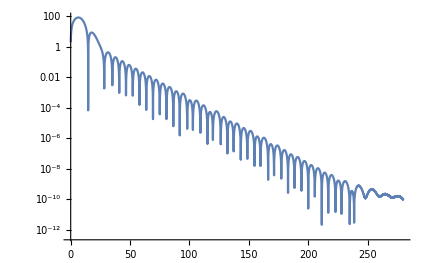

```mathematica
RNl2data[[;;,2]]= Abs[RNl2data[[;;,2]]];
ListLogPlot[{RNl2data},Joined->True,PlotRange->Automatic]
```

Reissner-Nordstrom de-Sitter M=1, Q=0.3, Λ=0.02, l=1

## Setup

Horizon locations (inner (Cauchy) horizon , event horizon , cosmological horizon)

```mathematica
M=1; Q=3/10; Λ=2/100;
```

```mathematica
Solve[(1-(2M)/r+Q^2/r^2- (Λ  r^2)/3)==0,r,Reals]//N
```

{{r→-13.1489},{r→0.0460608},{r→2.00929},{r→11.0936}}

```mathematica
rcauchy= 0.04606078285469926;
revent= 2.0092878253392454;
rcosmo = 11.093555251699417;
```

Invert tortoise

```mathematica
solrnds=NDSolve[{r'[rstar]==1-(2 M)/r[rstar]+Q^2/r[rstar]^2- (Λ  r[rstar]^2)/3,r[0]==1.01revent},r,{rstar,-10000,10000},Method->"StiffnessSwitching",PrecisionGoal->MachinePrecision,WorkingPrecision->MachinePrecision, InterpolationOrder-> All]
```

{{r→InterpolatingFunction[{{-10000., 10000.}}, <>]}}

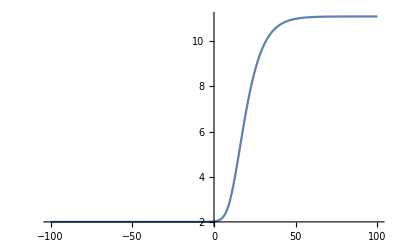

```mathematica
r[rstar_]=r[rstar]/.First[Out[92]];
Plot[{r[x](*,Evaluate[D[r[x],x]]*)},{x,-100,100},PlotRange->Automatic]
```

Define V_eff

```mathematica
Vrnds[r_,l_]:=(1-(2M)/r+Q^2/r^2- (Λ  r^2)/3)  ((l(l+1))/r^2+(2M)/r^3-(2 Q^2)/r^4- (2 Λ)/3);
```

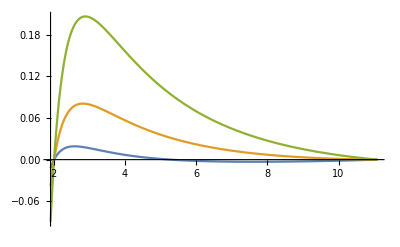
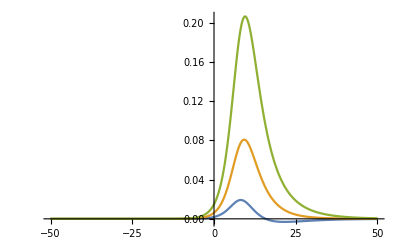

```mathematica
Row[{Plot[{Vrnds[r,0],Vrnds[r,1],Vrnds[r,2]},{r,revent-0.1,rcosmo},PlotRange->All],
Plot[{Vrnds[r[rstar],0],Vrnds[r[rstar],1],Vrnds[r[rstar],2]},{rstar,-50,50},PlotRange->All]}]
```

```mathematica
FDrnds[iter_,tfinal_,l_]:=(
Clear[ψ,Length1,rstarmax,rstarmin,Δrstar,imax,imin,jmax,σ,center,ψinit2,ψinit];
(*---------Discretization setup----------*)
rstarmax=200;rstarmin=-50;Length1=(rstarmax-rstarmin);
Δrstar=Length1/iter;Δt=Δrstar*0.7;
imax=IntegerPart[N[rstarmax/Δrstar]];imin=IntegerPart[N[rstarmin/Δrstar]];
jmax = IntegerPart[N[tfinal/Δt]];
(*-------messages to check code behavior-------*)
Print[Style["# of Iterations in space = ",Blue,14,Italic,FontFamily->"Courier"],Style[iter,14,Blue,Italic]]
(**)
Print[ Style["(r_*)^max =  ",Blue,14,Italic,FontFamily->"Courier"],Style[rstarmax " , ",Blue,14,Italic,FontFamily->"Courier"],
Style["r^max =  ",Blue,14,Italic,FontFamily->"Courier"], Style[NumberForm[ r[rstarmax],10],Blue,14,Italic,FontFamily->"Courier"]]
Print[ Style["(r_*)^min =  ",Blue,14,Italic,FontFamily->"Courier"],Style[rstarmin " , ",Blue,14,Italic,FontFamily->"Courier"],
Style["r^min =  ",Blue,14,Italic,FontFamily->"Courier"], Style[NumberForm[ r[rstarmin],10],Blue,14,Italic,FontFamily->"Courier"]]
(**)
Print[Style[ "I_max = ",Blue,14,Italic,FontFamily->"Courier"],Style[imax,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style[ "I_min = ",Blue,14,Italic,FontFamily->"Courier"],Style[imin,Blue,14,Italic,FontFamily->"Courier"]]
(**)
Print[Style["Space Discretization step = ",Blue,14,Italic,FontFamily->"Courier"],Style[N[Δrstar],Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["t_final/M = ",Blue,14,Italic,FontFamily->"Courier"],Style[tfinal/M,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style[ "# of Iterations in time = J_max = ",Blue,14,Italic,FontFamily->"Courier"],Style[jmax,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["Time Discretization step = ",Blue,14,Italic,FontFamily->"Courier"],Style[Δt,Blue,14,Italic,FontFamily->"Courier"]]
Print[Style["Δt/(Δr_*) = ",Blue,14,Italic,FontFamily->"Courier"],Style[N[Δt/Δrstar],Blue,14,Italic,FontFamily->"Courier"]]
(*-------V effective Discretization------*)
(*VschwDis[i_,l]:=Vschw[r[rstar],l]/.rstar->i Δrstar ;*)
(*--------Initial Condtions--------*) 
σ=5;center=0;
ψ[i_,0]:=ψinit2[rstar] /.rstar->i Δrstar  ;
ψinit2[rstar_]:= Exp[-(rstar-center)^2/(2 σ^2)];
(*-------------------------------*)
ψ[i_,-1]:=ψinit[r[rstar]]  /.rstar->i Δrstar ;
ψinit[r[rstar_]]=0; 
(**)
(*--------Iterating Scheme---------*)
Do[{ψ[i_,j_]:=ψ[i,j]= -ψ[i,j-2]+(Δt/Δrstar)^2(ψ[i+1,j-1]+ψ[i-1,j-1]) + (2-2 (Δt/Δrstar)^2-Vrnds[r[i*Δrstar],l] Δt^2) ψ[i,j-1]},{j,1,jmax},{i,imin+1,imax}] 

);
```

## lambda=1

```mathematica
FDrnds[1000,500,1]
```

# of Iterations in space = 1000

(r_*)^max =  200  , r^max =  11.09355528

(r_*)^min =  -50  , r^min =  2.009287935

I_max = 800

I_min = -200

Space Discretization step = 0.25

t_final/M = 500

# of Iterations in time = J_max = 2857

Time Discretization step = 0.175

Δt/(Δr_*) = 0.7

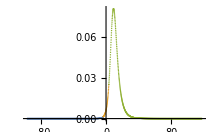

```mathematica
ListPlot[{Table[{i Δrstar  ,Vrnds[r[i*Δrstar],1]},{i,-700,-25}],
Table[{i Δrstar  ,Vrnds[r[i*Δrstar],1]},{i,-25,25}],
Table[{i Δrstar  ,Vrnds[r[i*Δrstar],1]},{i,25,850}]},Joined->False,PlotRange->All]
```

2.020840150792277

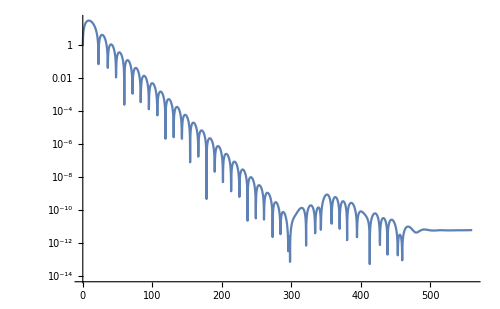

```mathematica
i=-5;
NumberForm[r[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/M,Evaluate[Abs[ψ[i,j]]]},{j,0,3200}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,ImageSize-> 500] ]
```

```mathematica
RNdSl1data= Table[{(j Δt)/M ,ψ[i,j]},{j,0,3200}];
```

```mathematica
Export["RNdS_l1M1data1.txt" ,RNdSl1data];
Export["RNdS_l1M1data2.txt" ,RNdSl1data,"Table","FieldSeparators"->" "];
```

```mathematica
Clear[RNdSl1data]
```

```mathematica
RNdSl1data=Import["RNdS_l1M1data2.txt","Table"];
```

```mathematica
FilePrint["RNdS_l1M1data1.txt"]
```

{0., E^(-49/16200)}
{0.05444444444444444, 1.9938267050517164}
{0.10888888888888888, 2.990407464780069}
{0.16333333333333333, 3.986589215720998}
{0.21777777777777776, 4.982239125854649}
{0.2722222222222222, 5.977224509544556}
{0.32666666666666666, 6.9714128639640185}
{0.38111111111111107, 7.964671905401577}
{0.43555555555555553, 8.956869605430867}
{0.49, 9.947874226927308}
{0.5444444444444444, 10.937554359911092}
{0.5988888888888888, 11.925778957197029}
{0.6533333333333333, 12.912417369833342}
{0.7077777777777777, 13.897339382310347}
{0.7622222222222221, 14.880415247518632}
{0.8166666666666667, 15.861515721438899}
{0.8711111111111111, 16.840512097551166}
{0.9255555555555555, 17.817276240955387}
{0.98, 18.791680622194548}
{1.0344444444444443, 19.7635983507629}
{1.0888888888888888, 20.73290320826767}
{1.1433333333333333, 21.699469681198053}
{1.1977777777777776, 22.66317299325256}
{1.2522222222222221, 23.623889137192222}
{1.3066666666666666, 24.581494906215173}
{1.361111111111111, 25.535867924864696}
{1.4155555555555555, 26.486886679473507}
{1.47, 27.434430548124237}
{1.5244444444444443, 28.378379830099465}
{1.5788888888888888, 29.318615774812912}
{1.6333333333333333, 30.255020610234947}
{1.6877777777777776, 31.187477570827205}
{1.7422222222222221, 32.115870924989984}
{1.7966666666666666, 33.040086002020516}
{1.851111111111111, 33.9600092185741}
{1.9055555555555554, 34.87552810458862}
{1.96, 35.78653132858379}
{2.0144444444444445, 36.69290872223005}
{2.0688888888888886, 37.59455130413602}
{2.123333333333333, 38.49135130289381}
{2.1777777777777776, 39.38320217946862}
{2.232222222222222, 40.26999864898118}
{2.2866666666666666, 41.151636701851366}
{2.341111111111111, 42.02801362423076}
{2.395555555555555, 42.89902801769139}
{2.4499999999999997, 43.764579818211175}
{2.5044444444444443, 44.624570314520945}
{2.5588888888888888, 45.478902165825374}
{2.6133333333333333, 46.32747941884561}
{2.667777777777778, 47.17020752414077}
{2.722222222222222, 48.00699335173776}
{2.7766666666666664, 48.83774520613511}
{2.831111111111111, 49.662372840694054}
{2.8855555555555554, 50.48078747136546}
{2.94, 51.292901789721654}
{2.9944444444444445, 52.09862997533819}
{3.0488888888888885, 52.89788770758491}
{3.103333333333333, 53.690592176815755}
{3.1577777777777776, 54.47666209490343}
{3.212222222222222, 55.2560177051158}
{3.2666666666666666, 56.028580791392}
{3.321111111111111, 56.794274687046645}
{3.375555555555555, 57.55302428285951}
{3.4299999999999997, 58.30475603451438}
{3.4844444444444442, 59.04939796942667}
{3.5388888888888888, 59.78687969302407}
{3.5933333333333333, 60.51713239448511}
{3.6477777777777773, 61.2400888519054}
{3.702222222222222, 61.955683436911094}
{3.7566666666666664, 62.66385211878434}
{3.811111111111111, 63.36453246811749}
{3.8655555555555554, 64.05766365993617}
{3.92, 64.74318647623059}
{3.974444444444444, 65.42104330787744}
{4.028888888888889, 66.09117815592384}
{4.083333333333333, 66.75353663216075}
{4.137777777777777, 67.4080659589506}
{4.192222222222222, 68.05471496839328}
{4.246666666666666, 68.69343410097265}
{4.301111111111111, 69.32417540375779}
{4.355555555555555, 69.94689252813686}
{4.41, 70.56154072704481}
{4.464444444444444, 71.16807685167612}
{4.518888888888888, 71.76645934768696}
{4.573333333333333, 72.3566482509087}
{4.627777777777777, 72.93860518264354}
{4.682222222222222, 73.51229334462505}
{4.736666666666666, 74.07767751364594}
{4.79111111111111, 74.63472403577613}
{4.845555555555555, 75.18340082014039}
{4.8999999999999995, 75.7236773323396}
{4.954444444444444, 76.25552458761985}
{5.0088888888888885, 76.77891514379162}
{5.0633333333333335, 77.29382309383227}
{5.1177777777777775, 77.80022405815592}
{5.172222222222222, 78.29809517661295}
{5.226666666666667, 78.7874151002753}
{5.281111111111111, 79.26816398300973}
{5.335555555555556, 79.74032347282399}
{5.39, 80.20387670298771}
{5.444444444444444, 80.65880828293876}
{5.498888888888889, 81.10510428899244}
{5.553333333333333, 81.54275225488617}
{5.607777777777778, 81.9717411621808}
{5.662222222222222, 82.39206143049515}
{5.716666666666666, 82.80370490754407}
{5.771111111111111, 83.20666485900999}
{5.825555555555555, 83.60093595831151}
{5.88, 83.98651427627235}
{5.934444444444444, 84.36339727062828}
{5.988888888888889, 84.73158377535344}
{6.043333333333333, 85.09107398987268}
{6.097777777777777, 85.44186946820963}
{6.152222222222222, 85.78397310802363}
{6.206666666666666, 86.11738913947437}
{6.261111111111111, 86.4421231139443}
{6.315555555555555, 86.75818189268938}
{6.369999999999999, 87.0655736354118}
{6.424444444444444, 87.36430778868666}
{6.478888888888888, 87.65439507422921}
{6.533333333333333, 87.93584747705982}
{6.587777777777777, 88.20867823359231}
{6.642222222222222, 88.47290181959859}
{6.696666666666666, 88.7285339380119}
{6.75111111111111, 88.97559150659434}
{6.805555555555555, 89.21409264549976}
{6.859999999999999, 89.44405666470732}
{6.914444444444444, 89.66550405127971}
{6.9688888888888885, 89.87845645643324}
{7.0233333333333325, 90.08293668242125}
{7.0777777777777775, 90.27896866920071}
{7.132222222222222, 90.46657748082903}
{7.1866666666666665, 90.64578929155331}
{7.241111111111111, 90.81663137158144}
{7.295555555555555, 90.97913207254476}
{7.35, 91.13332081269641}
{7.404444444444444, 91.27922806193394}
{7.458888888888889, 91.416885326765}
{7.513333333333333, 91.54632513534031}
{7.567777777777778, 91.66758102265875}
{7.622222222222222, 91.78068751598406}
{7.676666666666666, 91.88568012040012}
{7.731111111111111, 91.98259530434144}
{7.785555555555555, 92.071470484935}
{7.84, 92.15234401306046}
{7.894444444444444, 92.2252551581143}
{7.948888888888888, 92.290244092539}
{8.003333333333332, 92.3473518762493}
{8.057777777777778, 92.39662044108357}
{8.112222222222222, 92.43809257527873}
{8.166666666666666, 92.47181190781298}
{8.22111111111111, 92.49782289244827}
{8.275555555555554, 92.5161707914379}
{8.33, 92.52690165898724}
{8.384444444444444, 92.53006232457605}
{8.438888888888888, 92.52570037621079}
{8.493333333333332, 92.51386414361659}
{8.547777777777778, 92.4946026812905}
{8.602222222222222, 92.46796575128138}
{8.656666666666666, 92.43400380564475}
{8.71111111111111, 92.39276796869822}
{8.765555555555554, 92.34431001925674}
{8.82, 92.28868237287313}
{8.874444444444444, 92.22593806394327}
{8.928888888888888, 92.15613072756109}
{8.983333333333333, 92.07931458116236}
{9.037777777777777, 91.99554440607835}
{9.092222222222222, 91.90487552907784}
{9.146666666666667, 91.80736380390262}
{9.20111111111111, 91.70306559274925}
{9.255555555555555, 91.59203774762929}
{9.309999999999999, 91.4743375915912}
{9.364444444444445, 91.35002289990301}
{9.418888888888889, 91.21915188133325}
{9.473333333333333, 91.08178315953806}
{9.527777777777777, 90.9379757544199}
{9.58222222222222, 90.7877890633794}
{9.636666666666667, 90.63128284257269}
{9.69111111111111, 90.46851718833865}
{9.745555555555555, 90.29955251880874}
{9.799999999999999, 90.12444955557773}
{9.854444444444443, 89.9432693053768}
{9.908888888888889, 89.75607304183087}
{9.963333333333333, 89.56292228741198}
{10.017777777777777, 89.36387879561546}
{10.072222222222221, 89.15900453331055}
{10.126666666666667, 88.94836166321798}
{10.181111111111111, 88.73201252652372}
{10.235555555555555, 88.51001962570105}
{10.29, 88.28244560762064}
{10.344444444444443, 88.04935324694712}
{10.398888888888889, 87.81080542973892}
{10.453333333333333, 87.56686513721166}
{10.507777777777777, 87.31759542975605}
{10.562222222222221, 87.06305943132568}
{10.616666666666665, 86.80332031417399}
{10.671111111111111, 86.5384412838222}
{10.725555555555555, 86.26848556423519}
{10.78, 85.99351638332551}
{10.834444444444443, 85.71359695887759}
{10.888888888888888, 85.42879048483184}
{10.943333333333333, 85.13916011782526}
{10.997777777777777, 84.84476896400436}
{11.052222222222222, 84.5456800662193}
{11.106666666666666, 84.24195639164435}
{11.16111111111111, 83.93366081975961}
{11.215555555555556, 83.62085613062682}
{11.27, 83.3036049934833}
{11.324444444444444, 82.981969955731}
{11.378888888888888, 82.65601343234809}
{11.433333333333332, 82.32579769567208}
{11.487777777777778, 81.99138486549602}
{11.542222222222222, 81.65283689949248}
{11.596666666666666, 81.31021558403667}
{11.65111111111111, 80.96358252545632}
{11.705555555555556, 80.61299914164569}
{11.76, 80.25852665397711}
{11.814444444444444, 79.90022607954182}
{11.868888888888888, 79.53815822380372}
{11.923333333333332, 79.17238367366716}
{11.977777777777778, 78.80296279086618}
{12.032222222222222, 78.42995570562906}
{12.086666666666666, 78.05342231068843}
{12.14111111111111, 77.67342225570435}
{12.195555555555554, 77.29001494204887}
{12.25, 76.90325951785721}
{12.304444444444444, 76.51321487334995}
{12.358888888888888, 76.1199396365093}
{12.413333333333332, 75.72349216912592}
{12.467777777777776, 75.32393056313214}
{12.522222222222222, 74.92131263716279}
{12.576666666666666, 74.51569593338763}
{12.63111111111111, 74.10713771467631}
{12.685555555555554, 73.69569496206942}
{12.739999999999998, 73.28142437247962}
{12.794444444444444, 72.8643823566084}
{12.848888888888888, 72.44462503713665}
{12.903333333333332, 72.02220824722278}
{12.957777777777777, 71.59718752926192}
{13.01222222222222, 71.16961813384403}
{13.066666666666666, 70.73955501891746}
{13.12111111111111, 70.30705284920838}
{13.175555555555555, 69.87216599589578}
{13.229999999999999, 69.43494853647039}
{13.284444444444444, 68.99545425472844}
{13.338888888888889, 68.55373664093872}
{13.393333333333333, 68.1098488922371}
{13.447777777777777, 67.66384391322018}
{13.50222222222222, 67.21577431666148}
{13.556666666666667, 66.76569242434243}
{13.61111111111111, 66.31365026806309}
{13.665555555555555, 65.85969959084485}
{13.719999999999999, 65.4038918482428}
{13.774444444444443, 64.94627820970972}
{13.828888888888889, 64.48690956006445}
{13.883333333333333, 64.02583650112715}
{13.937777777777777, 63.5631093534788}
{13.992222222222221, 63.09877815825959}
{14.046666666666665, 62.632892679013146}
{14.101111111111111, 62.165502403647295}
{14.155555555555555, 61.69665654650601}
{14.209999999999999, 61.226404050466535}
{14.264444444444443, 60.754793589032346}
{14.318888888888887, 60.28187356848958}
{14.373333333333333, 59.80769213016506}
{14.427777777777777, 59.33229715272142}
{14.482222222222221, 58.85573625442299}
{14.536666666666665, 58.378056795401136}
{14.59111111111111, 57.899305879975984}
{14.645555555555555, 57.419530359013756}
{14.7, 56.938776832255215}
{14.754444444444443, 56.457091650611005}
{14.808888888888887, 55.97452091847245}
{14.863333333333333, 55.4911104960439}
{14.917777777777777, 55.00690600164263}
{14.972222222222221, 54.521952813936366}
{15.026666666666666, 54.0362960741527}
{15.08111111111111, 53.54998068829428}
{15.135555555555555, 53.0630513293335}
{15.19, 52.57555243933858}
{15.244444444444444, 52.087528231528744}
{15.298888888888888, 51.59902269229546}
{15.353333333333332, 51.11007958320184}
{15.407777777777778, 50.62074244292601}
{15.462222222222222, 50.131054589118946}
{15.516666666666666, 49.64105912019292}
{15.57111111111111, 49.15079891707035}
{15.625555555555554, 48.660316644881235}
{15.68, 48.16965475456968}
{15.734444444444444, 47.678855484406206}
{15.788888888888888, 47.18796086144501}
{15.843333333333332, 46.69701270293721}
{15.897777777777776, 46.20605261765465}
{15.952222222222222, 45.71512200709431}
{16.006666666666664, 45.224262066602535}
{16.06111111111111, 44.73351378646207}
{16.115555555555556, 44.242917952908776}
{16.169999999999998, 43.75251514901922}
{16.224444444444444, 43.262345755485875}
{16.278888888888886, 42.77244995134465}
{16.333333333333332, 42.282867714652}
{16.387777777777778, 41.793638823043715}
{16.44222222222222, 41.304802854161885}
{16.496666666666666, 40.81639918601491}
{16.55111111111111, 40.328466997295735}
{16.605555555555554, 39.84104526759686}
{16.66, 39.354172777486255}
{16.714444444444442, 38.867888108500914}
{16.76888888888889, 38.38222964310441}
{16.82333333333333, 37.89723556455703}
{16.877777777777776, 37.41294385664263}
{16.932222222222222, 36.92939230329721}
{16.986666666666665, 36.446618488205786}
{17.04111111111111, 35.96465979433431}
{17.095555555555556, 35.483553403323356}
{17.15, 35.00333629476433}
{17.204444444444444, 34.524045245438394}
{17.258888888888887, 34.045716828514195}
{17.313333333333333, 33.56838741262611}
{17.36777777777778, 33.09209316082373}
{17.42222222222222, 32.61687002946912}
{17.476666666666667, 32.142753767106925}
{17.53111111111111, 31.66977991324044}
{17.585555555555555, 31.197983796980907}
{17.64, 30.727400535630867}
{17.694444444444443, 30.25806503324443}
{17.74888888888889, 29.790011979115857}
{17.80333333333333, 29.32327584615174}
{17.857777777777777, 28.857890889169877}
{17.912222222222223, 28.39389114317618}
{17.966666666666665, 27.93131042158832}
{18.02111111111111, 27.470182314355412}
{18.075555555555553, 27.010540186000416}
{18.13, 26.55241717364127}
{18.184444444444445, 26.095846184976747}
{18.238888888888887, 25.640859896183883}
{18.293333333333333, 25.187490749735222}
{18.347777777777775, 24.735770952191807}
{18.40222222222222, 24.285732471977415}
{18.456666666666667, 23.837407037085466}
{18.51111111111111, 23.39082613270755}
{18.565555555555555, 22.946020998830406}
{18.619999999999997, 22.503022627824258}
{18.674444444444443, 22.061861761987732}
{18.72888888888889, 21.622568891024923}
{18.78333333333333, 21.18517424948411}
{18.837777777777777, 20.74970781418972}
{18.89222222222222, 20.31619930165161}
{18.946666666666665, 19.884678165423967}
{19.00111111111111, 19.455173593425094}
{19.055555555555554, 19.027714505247918}
{19.11, 18.60232954946162}
{19.16444444444444, 18.179047100882315}
{19.218888888888888, 17.75789525781041}
{19.273333333333333, 17.338901839256582}
{19.327777777777776, 16.9220943821673}
{19.38222222222222, 16.507500138636765}
{19.436666666666664, 16.09514607309506}
{19.49111111111111, 15.685058859485238}
{19.545555555555556, 15.277264878445886}
{19.599999999999998, 14.871790214495205}
{19.654444444444444, 14.46866065320216}
{19.708888888888886, 14.067901678347939}
{19.763333333333332, 13.66953846909762}
{19.817777777777778, 13.273595897187715}
{19.87222222222222, 12.880098524112716}
{19.926666666666666, 12.489070598303519}
{19.981111111111108, 12.100536052318397}
{20.035555555555554, 11.714518500063338}
{20.09, 11.331041234025788}
{20.144444444444442, 10.950127222502672}
{20.198888888888888, 10.571799106840075}
{20.253333333333334, 10.196079198713303}
{20.307777777777776, 9.822989477437408}
{20.362222222222222, 9.452551587277469}
{20.416666666666664, 9.084786834766794}
{20.47111111111111, 8.719716186071691}
{20.525555555555556, 8.357360264404596}
{20.58, 7.997739347447203}
{20.634444444444444, 7.640873364777766}
{20.688888888888886, 7.2867818953456664}
{20.743333333333332, 6.935484165009963}
{20.797777777777778, 6.5869990441022885}
{20.85222222222222, 6.241345044992868}
{20.906666666666666, 5.898540319700489}
{20.96111111111111, 5.558602657577739}
{21.015555555555554, 5.2215494830368705}
{21.07, 4.887397853281587}
{21.124444444444443, 4.55616445607799}
{21.17888888888889, 4.227865607607376}
{21.23333333333333, 3.90251725037537}
{21.287777777777777, 3.5801349511331995}
{21.342222222222222, 3.2607338988337906}
{21.396666666666665, 2.9443289026726394}
{21.45111111111111, 2.630934390198821}
{21.505555555555553, 2.32056440544625}
{21.56, 2.013232607096648}
{21.614444444444445, 1.7089522667280892}
{21.668888888888887, 1.4077362671454363}
{21.723333333333333, 1.1095971007398397}
{21.777777777777775, 0.8145468678775765}
{21.83222222222222, 0.5225972753737841}
{21.886666666666667, 0.23375963505838715}
{21.94111111111111, -0.051955137619594416}
{21.995555555555555, -0.3345365249604396}
{22.049999999999997, -0.6139744082995}
{22.104444444444443, -0.8902590691917162}
{22.15888888888889, -1.1633811905476288}
{22.21333333333333, -1.4333318577438154}
{22.267777777777777, -1.7001025596550081}
{22.32222222222222, -1.9636851895774612}
{22.376666666666665, -2.224072046092476}
{22.43111111111111, -2.4812558339050454}
{22.485555555555553, -2.735229664610687}
{22.54, -2.985987057348581}
{22.59444444444444, -3.2335219393825225}
{22.648888888888887, -3.4778286466555834}
{22.703333333333333, -3.718901924281033}
{22.757777777777775, -3.9567369269181123}
{22.81222222222222, -4.191329219063304}
{22.866666666666664, -4.422674775311167}
{22.92111111111111, -4.65076998055973}
{22.975555555555555, -4.875611630103003}
{23.029999999999998, -5.097196929628095}
{23.084444444444443, -5.315523495175181}
{23.138888888888886, -5.530589353049209}
{23.19333333333333, -5.742392939624157}
{23.247777777777777, -5.9509331010436}
{23.30222222222222, -6.156209092875717}
{23.356666666666666, -6.358220579725164}
{23.41111111111111, -6.556967634744979}
{23.465555555555554, -6.752450739039717}
{23.52, -6.944670781014062}
{23.574444444444442, -7.133629055681089}
{23.628888888888888, -7.31932726387888}
{23.683333333333334, -7.501767511376405}
{23.737777777777776, -7.680952307916554}
{23.79222222222222, -7.856884566219645}
{23.846666666666664, -8.029567600903498}
{23.90111111111111, -8.199005127293315}
{23.955555555555556, -8.365201260161538}
{24.009999999999998, -8.528160512427673}
{24.064444444444444, -8.687887793782437}
{24.118888888888886, -8.84438840920418}
{24.173333333333332, -8.997668057399622}
{24.227777777777778, -9.147732829203179}
{24.28222222222222, -9.294589205907602}
{24.336666666666666, -9.438244057490765}
{24.39111111111111, -9.5787046407625}
{24.445555555555554, -9.715978597468414}
{24.5, -9.850073952331543}
{24.554444444444442, -9.980999110994958}
{24.608888888888888, -10.108762857881338}
{24.66333333333333, -10.233374354007598}
{24.717777777777776, -10.354843134743481}
{24.772222222222222, -10.473179107477034}
{24.826666666666664, -10.588392549195076}
{24.88111111111111, -10.700494104016514}
{24.935555555555553, -10.809494780675319}
{24.99, -10.915405949917215}
{25.044444444444444, -11.018239341810633}
{25.098888888888887, -11.118007043008035}
{25.153333333333332, -11.214721493961953}
{25.207777777777775, -11.308395486062526}
{25.26222222222222, -11.399042158689957}
{25.316666666666666, -11.486674996214655}
{25.37111111111111, -11.571307824956302}
{25.425555555555555, -11.652954810072865}
{25.479999999999997, -11.731630452366781}
{25.534444444444443, -11.807349585036176}
{25.58888888888889, -11.880127370388117}
{25.64333333333333, -11.949979296490705}
{25.697777777777777, -12.016921173746333}
{25.75222222222222, -12.080969131407633}
{25.806666666666665, -12.142139614057335}
{25.86111111111111, -12.2004493780358}
{25.915555555555553, -12.2559154877955}
{25.97, -12.308555312196683}
{26.02444444444444, -12.358386520767587}
{26.078888888888887, -12.405427079920544}
{26.133333333333333, -12.449695249102406}
{26.187777777777775, -12.491209576886034}
{26.24222222222222, -12.529988897025953}
{26.296666666666663, -12.566052324477052}
{26.35111111111111, -12.599419251356071}
{26.405555555555555, -12.630109342845719}
{26.459999999999997, -12.65814253306217}
{26.514444444444443, -12.683539020891349}
{26.56888888888889, -12.706319265777061}
{26.62333333333333, -12.72650398345501}
{26.677777777777777, -12.74411414164952}
{26.73222222222222, -12.759170955743434}
{26.786666666666665, -12.771695884408926}
{26.84111111111111, -12.781710625189}
{26.895555555555553, -12.78923711004151}
{26.95, -12.794297500859654}
{27.00444444444444, -12.796914184962048}
{27.058888888888887, -12.797109770539588}
{27.113333333333333, -12.79490708206541}
{27.167777777777776, -12.790329155683676}
{27.22222222222222, -12.783399234575958}
{27.276666666666664, -12.774140764291573}
{27.33111111111111, -12.7625773880425}
{27.385555555555555, -12.748732941978806}
{27.439999999999998, -12.732631450448888}
{27.494444444444444, -12.71429712123141}
{27.548888888888886, -12.6937543407344}
{27.60333333333333, -12.671027669176144}
{27.657777777777778, -12.646141835757229}
{27.71222222222222, -12.619121733812431}
{27.766666666666666, -12.589992415933377}
{27.821111111111108, -12.558779089074147}
{27.875555555555554, -12.525507109653306}
{27.93, -12.490201978644016}
{27.984444444444442, -12.45288933663938}
{28.038888888888888, -12.41359495890217}
{28.09333333333333, -12.372344750415554}
{28.147777777777776, -12.329164740929848}
{28.202222222222222, -12.284081079989647}
{28.256666666666664, -12.237120031946912}
{28.31111111111111, -12.188307970979082}
{28.365555555555552, -12.137671376110944}
{28.419999999999998, -12.085236826222511}
{28.474444444444444, -12.031030995044542}
{28.528888888888886, -11.975080646162596}
{28.583333333333332, -11.917412628032414}
{28.637777777777774, -11.858053868987485}
{28.69222222222222, -11.797031372236079}
{28.746666666666666, -11.734372210869601}
{28.80111111111111, -11.670103522889463}
{28.855555555555554, -11.604252506232765}
{28.909999999999997, -11.53684641378968}
{28.964444444444442, -11.467912548434413}
{29.01888888888889, -11.397478258081353}
{29.07333333333333, -11.325570930747014}
{29.127777777777776, -11.252217989606095}
{29.18222222222222, -11.1774468880629}
{29.236666666666665, -11.1012851048542}
{29.29111111111111, -11.023760139165153}
{29.345555555555553, -10.944899505742155}
{29.4, -10.864730730022265}
{29.454444444444444, -10.783281343299587}
{29.508888888888887, -10.70057887791216}
{29.563333333333333, -10.616650862429031}
{29.617777777777775, -10.531524816854827}
{29.67222222222222, -10.445228247876203}
{29.726666666666667, -10.357788644136365}
{29.78111111111111, -10.26923347151318}
{29.835555555555555, -10.179590168415167}
{29.889999999999997, -10.088886141123732}
{29.944444444444443, -9.997148759171255}
{29.99888888888889, -9.90440535072678}
{30.05333333333333, -9.81068319799939}
{30.107777777777777, -9.716009532691102}
{30.16222222222222, -9.620411531493454}
{30.216666666666665, -9.52391631159642}
{30.27111111111111, -9.426550926214642}
{30.325555555555553, -9.328342360165381}
{30.38, -9.229317525497686}
{30.43444444444444, -9.129503257139254}
{30.488888888888887, -9.028926308560266}
{30.543333333333333, -8.927613347490048}
{30.597777777777775, -8.82559095169203}
{30.65222222222222, -8.722885604762471}
{30.706666666666663, -8.619523691945965}
{30.76111111111111, -8.515531496003772}
{30.815555555555555, -8.410935193146743}
{30.869999999999997, -8.30576084899866}
{30.924444444444443, -8.200034414576663}
{30.978888888888886, -8.093781722323662}
{31.03333333333333, -7.9870284822105715}
{31.087777777777777, -7.879800277875929}
{31.14222222222222, -7.772122562783408}
{31.196666666666665, -7.664020656429812}
{31.251111111111108, -7.555519740627245}
{31.305555555555554, -7.446644855829742}
{31.36, -7.337420897479165}
{31.41444444444444, -7.227872612399419}
{31.468888888888888, -7.11802459526799}
{31.52333333333333, -7.007901285139085}
{31.577777777777776, -6.897526961988227}
{31.63222222222222, -6.7869257433026995}
{31.686666666666664, -6.6761215807511745}
{31.74111111111111, -6.565138256911703}
{31.795555555555552, -6.453999382023988}
{31.849999999999998, -6.342728390785035}
{31.904444444444444, -6.231348539224762}
{31.958888888888886, -6.119882901646235}
{32.01333333333333, -6.008354367593563}
{32.06777777777778, -5.896785638860781}
{32.12222222222222, -5.785199226580418}
{32.17666666666666, -5.673617448382236}
{32.23111111111111, -5.562062425583432}
{32.285555555555554, -5.450556080417658}
{32.339999999999996, -5.339120133342712}
{32.394444444444446, -5.227776100423166}
{32.44888888888889, -5.11654529074854}
{32.50333333333333, -5.005448803888352}
{32.55777777777777, -4.894507527423948}
{32.61222222222222, -4.783742134559247}
{32.666666666666664, -4.673173081771319}
{32.72111111111111, -4.562820606496399}
{32.775555555555556, -4.452704724890264}
{32.83, -4.3428452296704725}
{32.88444444444444, -4.233261688002599}
{32.93888888888889, -4.123973439420739}
{32.99333333333333, -4.014999593819673}
{33.047777777777775, -3.9063590295311443}
{33.10222222222222, -3.798070391448139}
{33.156666666666666, -3.690152089182451}
{33.21111111111111, -3.582622295290789}
{33.26555555555555, -3.475498943586593}
{33.32, -3.3687997275037516}
{33.37444444444444, -3.262542098492868}
{33.428888888888885, -3.1567432644824684}
{33.483333333333334, -3.0514201884266883}
{33.53777777777778, -2.9465895869087237}
{33.59222222222222, -2.842267928776536}
{33.64666666666666, -2.738471433839666}
{33.70111111111111, -2.635216071652315}
{33.75555555555555, -2.5325175603555907}
{33.809999999999995, -2.4303913655520835}
{33.864444444444445, -2.3288526992377885}
{33.91888888888889, -2.227916518819447}
{33.97333333333333, -2.1275975261939877}
{34.02777777777778, -2.0279101668604347}
{34.08222222222222, -1.928868629085308}
{34.13666666666666, -1.830486843152047}
{34.19111111111111, -1.7327784806751498}
{34.245555555555555, -1.635756953947084}
{34.3, -1.5394354153347543}
{34.35444444444444, -1.4438267567579564}
{34.40888888888889, -1.3489436092347324}
{34.46333333333333, -1.2547983424599873}
{34.51777777777777, -1.1614030644297915}
{34.57222222222222, -1.0687696211451003}
{34.626666666666665, -0.9769095963840875}
{34.68111111111111, -0.8858343115082751}
{34.73555555555556, -0.7955548253104755}
{34.79, -0.7060819339391399}
{34.84444444444444, -0.6174261708926964}
{34.898888888888884, -0.5295978070483589}
{34.95333333333333, -0.4426068507288615}
{35.007777777777775, -0.35646304784200067}
{35.06222222222222, -0.2711758820910519}
{35.11666666666667, -0.18675457522049677}
{35.17111111111111, -0.1032080872960005}
{35.22555555555555, -0.0205451170532176}
{35.28, 0.06122589768214502}
{35.33444444444444, 0.1420967795381346}
{35.388888888888886, 0.22205961110973294}
{35.44333333333333, 0.30110673440760016}
{35.49777777777778, 0.3792307502355679}
{35.55222222222222, 0.45642451753100427}
{35.60666666666666, 0.5326811526779731}
{35.66111111111111, 0.6079940287607903}
{35.715555555555554, 0.6823567747469246}
{35.769999999999996, 0.7557632746317268}
{35.824444444444445, 0.828207666559099}
{35.87888888888889, 0.8996843418876975}
{35.93333333333333, 0.9701879441876213}
{35.98777777777777, 1.0397133681978572}
{36.04222222222222, 1.1082557587624804}
{36.096666666666664, 1.1758105097177622}
{36.151111111111106, 1.2423732627114974}
{36.205555555555556, 1.3079399059820842}
{36.26, 1.3725065731188568}
{36.31444444444444, 1.436069641778856}
{36.36888888888889, 1.4986257323381191}
{36.42333333333333, 1.560171706501797}
{36.477777777777774, 1.620704665897652}
{36.53222222222222, 1.68022195063159}
{36.586666666666666, 1.7387211377805496}
{36.64111111111111, 1.7962000398434432}
{36.69555555555555, 1.8526567031772632}
{36.75, 1.9080894064008882}
{36.80444444444444, 1.9624966587396695}
{36.858888888888885, 2.0158771983274297}
{36.913333333333334, 2.068229990494927}
{36.967777777777776, 2.1195542260315707}
{37.02222222222222, 2.1698493193919677}
{37.07666666666666, 2.2191149068596285}
{37.13111111111111, 2.2673508446980373}
{37.18555555555555, 2.3145572072801968}
{37.239999999999995, 2.3607342851674726}
{37.294444444444444, 2.4058825831457846}
{37.34888888888889, 2.450002818249817}
{37.40333333333333, 2.4930959177706735}
{37.45777777777778, 2.535163017217602}
{37.51222222222222, 2.576205458237574}
{37.56666666666666, 2.6162247865232917}
{37.62111111111111, 2.655222749709313}
{37.675555555555555, 2.693201295227395}
{37.73, 2.7301625681206274}
{37.78444444444444, 2.7661089088461313}
{37.83888888888889, 2.8010428510701204}
{37.89333333333333, 2.8349671194275596}
{37.94777777777777, 2.8678846272420433}
{38.00222222222222, 2.8997984742342546}
{38.056666666666665, 2.9307119442265672}
{38.11111111111111, 2.9606285028176917}
{38.16555555555556, 2.9895517950194384}
{38.22, 3.0174856428820664}
{38.27444444444444, 3.0444340431191645}
{38.32888888888888, 3.0704011647080525}
{38.38333333333333, 3.095391346454531}
{38.437777777777775, 3.1194090945461377}
{38.49222222222222, 3.1424590801079284}
{38.54666666666667, 3.1645461367393275}
{38.60111111111111, 3.1856752580180365}
{38.65555555555555, 3.2058515949923403}
{38.71, 3.2250804536783617}
{38.76444444444444, 3.243367292543778}
{38.818888888888885, 3.2607177199617765}
{38.87333333333333, 3.2771374916535123}
{38.92777777777778, 3.2926325081375194}
{38.98222222222222, 3.3072088121707055}
{39.03666666666666, 3.320872586163029}
{39.09111111111111, 3.333630149580916}
{39.14555555555555, 3.3454879563592854}
{39.199999999999996, 3.356452592310083}
{39.254444444444445, 3.366530772508255}
{39.30888888888889, 3.375729338666864}
{39.36333333333333, 3.3840552565220565}
{39.41777777777777, 3.3915156132191107}
{39.47222222222222, 3.39811761467993}
{39.526666666666664, 3.403868582960385}
{39.581111111111106, 3.4087759536184543}
{39.635555555555555, 3.412847273087598}
{39.69, 3.41609019603567}
{39.74444444444444, 3.418512482714643}
{39.79888888888889, 3.420121996321916}
{39.85333333333333, 3.420926700370644}
{39.907777777777774, 3.4209346560497456}
{39.962222222222216, 3.420154019575865}
{40.016666666666666, 3.4185930395574804}
{40.07111111111111, 3.4162600543715103}
{40.12555555555555, 3.4131634895337988}
{40.18, 3.4093118550628914}
{40.23444444444444, 3.404713742856278}
{40.288888888888884, 3.399377824082172}
{40.343333333333334, 3.39331284656946}
{40.397777777777776, 3.386527632192636}
{40.45222222222222, 3.379031074269381}
{40.50666666666667, 3.370832134976115}
{40.56111111111111, 3.36193984276575}
{40.61555555555555, 3.3523632897824625}
{40.669999999999995, 3.3421116292894655}
{40.724444444444444, 3.331194073116904}
{40.778888888888886, 3.3196198891156827}
{40.83333333333333, 3.307398398610298}
{40.88777777777778, 3.29453897386498}
{40.94222222222222, 3.2810510355718674}
{40.99666666666666, 3.2669440503487635}
{41.05111111111111, 3.2522275282379853}
{41.105555555555554, 3.2369110202187676}
{41.16, 3.2210041157433253}
{41.21444444444444, 3.2045164402860062}
{41.26888888888889, 3.18745765289571}
{41.32333333333333, 3.1698374437619696}
{41.37777777777777, 3.151665531805893}
{41.43222222222222, 3.132951662287536}
{41.486666666666665, 3.113705604418986}
{41.54111111111111, 3.0939371489913112}
{41.595555555555556, 3.0736561060272054}
{41.65, 3.052872302453012}
{41.70444444444444, 3.0315955797789393}
{41.75888888888888, 3.009835791793467}
{41.81333333333333, 2.987602802284002}
{41.867777777777775, 2.9649064827795564}
{41.92222222222222, 2.9417567103041096}
{41.97666666666667, 2.9181633651445953}
{42.03111111111111, 2.8941363286454838}
{42.08555555555555, 2.869685481027692}
{42.14, 2.844820699220625}
{42.19444444444444, 2.81955185470936}
{42.248888888888885, 2.793888811408593}
{42.30333333333333, 2.767841423562862}
{42.35777777777778, 2.7414195336622664}
{42.41222222222222, 2.71463297037396}
{42.46666666666666, 2.6874915465004814}
{42.52111111111111, 2.6600050569660265}
{42.57555555555555, 2.6321832768203834}
{42.629999999999995, 2.6040359592592166}
{42.684444444444445, 2.5755728336711647}
{42.73888888888889, 2.546803603714386}
{42.79333333333333, 2.5177379454129416}
{42.84777777777777, 2.4883855052700907}
{42.90222222222222, 2.458755898408095}
{42.95666666666666, 2.428858706738618}
{43.011111111111106, 2.398703477155062}
{43.065555555555555, 2.3682997197425264}
{43.12, 2.337656906013893}
{43.17444444444444, 2.3067844671773536}
{43.22888888888889, 2.2756917924277933}
{43.28333333333333, 2.24438822725655}
{43.337777777777774, 2.2128830717868504}
{43.39222222222222, 2.181185579141229}
{43.446666666666665, 2.1493049538345423}
{43.50111111111111, 2.1172503501861377}
{43.55555555555555, 2.0850308707572345}
{43.61, 2.052655564820597}
{43.66444444444444, 2.0201334268573166}
{43.718888888888884, 1.9874733950735077}
{43.77333333333333, 1.9546843499417101}
{43.827777777777776, 1.9217751127747449}
{43.88222222222222, 1.8887544443280542}
{43.93666666666667, 1.8556310434226089}
{43.99111111111111, 1.8224135455918558}
{44.04555555555555, 1.7891105217610856}
{44.099999999999994, 1.7557304769566073}
{44.154444444444444, 1.7222818490362035}
{44.208888888888886, 1.6887730074428426}
{44.26333333333333, 1.6552122519904688}
{44.31777777777778, 1.621607811680783}
{44.37222222222222, 1.5879678435421247}
{44.42666666666666, 1.5543004314907833}
{44.48111111111111, 1.5206135852237148}
{44.535555555555554, 1.4869152391431633}
{44.589999999999996, 1.4532132513042468}
{44.64444444444444, 1.419515402384251}
{44.69888888888889, 1.3858293946825126}
{44.75333333333333, 1.3521628511529005}
{44.80777777777777, 1.3185233144600552}
{44.86222222222222, 1.2849182460565647}
{44.916666666666664, 1.251355025289705}
{44.97111111111111, 1.217840948541287}
{45.025555555555556, 1.1843832283920748}
{45.08, 1.1509889928063568}
{45.13444444444444, 1.1176652843448922}
{45.18888888888888, 1.0844190594113365}
{45.24333333333333, 1.0512571875241081}
{45.297777777777775, 1.0181864506076035}
{45.35222222222222, 0.9852135423102295}
{45.406666666666666, 0.9523450673559825}
{45.46111111111111, 0.9195875409224595}
{45.51555555555555, 0.8869473880376678}
{45.57, 0.8544309430019618}
{45.62444444444444, 0.8220444488432006}
{45.678888888888885, 0.789794056799208}
{45.73333333333333, 0.7576858258186105}
{45.78777777777778, 0.7257257220850647}
{45.84222222222222, 0.6939196185741062}
{45.89666666666666, 0.6622732946380702}
{45.95111111111111, 0.6307924356090837}
{46.00555555555555, 0.5994826324236479}
{46.059999999999995, 0.5683493812789565}
{46.114444444444445, 0.5373980833179428}
{46.16888888888889, 0.5066340443322526}
{46.22333333333333, 0.47606247448503963}
{46.27777777777777, 0.445688488064343}
{46.33222222222222, 0.41551710326562386}
{46.38666666666666, 0.38555324199212365}
{46.441111111111105, 0.355801729673322}
{46.495555555555555, 0.32626729511268326}
{46.55, 0.29695457036487194}
{46.60444444444444, 0.26786809063072475}
{46.65888888888889, 0.2390122941685937}
{46.71333333333333, 0.21039152223350818}
{46.76777777777777, 0.1820100190459943}
{46.82222222222222, 0.15387193177863123}
{46.876666666666665, 0.12598131055722991}
{46.93111111111111, 0.09834210848815263}
{46.98555555555555, 0.07095818171535269}
{47.04, 0.04383328949524834}
{47.09444444444444, 0.016971094284561054}
{47.148888888888884, -0.009624838147515843}
{47.20333333333333, -0.035951038577518024}
{47.257777777777775, -0.062004134167983505}
{47.31222222222222, -0.08778084829647018}
{47.36666666666667, -0.11327800036225968}
{47.42111111111111, -0.1384925055636005}
{47.47555555555555, -0.16342137465674064}
{47.529999999999994, -0.18806171370529862}
{47.58444444444444, -0.212410723809543}
{47.638888888888886, -0.23646570080658982}
{47.69333333333333, -0.2602240349520208}
{47.74777777777778, -0.2836832105933379}
{47.80222222222222, -0.3068408058257624}
{47.85666666666666, -0.3296944921195547}
{47.91111111111111, -0.3522420339282432}
{47.965555555555554, -0.37448128828994226}
{48.019999999999996, -0.39641020441356734}
{48.07444444444444, -0.4180268232374824}
{48.12888888888889, -0.4393292769685551}
{48.18333333333333, -0.4603157886153609}
{48.23777777777777, -0.48098467150888075}
{48.29222222222222, -0.5013343287967607}
{48.346666666666664, -0.5213632529174506}
{48.401111111111106, -0.5410700250693563}
{48.455555555555556, -0.5604533146701678}
{48.51, -0.5795118787911733}
{48.56444444444444, -0.598244561570915}
{48.61888888888888, -0.616650293624405}
{48.67333333333333, -0.6347280914451522}
{48.727777777777774, -0.65247705678394}
{48.78222222222222, -0.6698963760065852}
{48.836666666666666, -0.6869853194475884}
{48.89111111111111, -0.7037432407590559}
{48.94555555555555, -0.7201695762382865}
{49., -0.7362638441341137}
{49.05444444444444, -0.7520256439493445}
{49.108888888888885, -0.7674546557408627}
{49.16333333333333, -0.7825506394004927}
{49.217777777777776, -0.7973134339144828}
{49.27222222222222, -0.8117429566190915}
{49.32666666666666, -0.8258392024560905}
{49.38111111111111, -0.8396022432113215}
{49.43555555555555, -0.8530322267319392}
{49.489999999999995, -0.8661293761396233}
{49.544444444444444, -0.8788939890457517}
{49.59888888888889, -0.8913264367519873}
{49.65333333333333, -0.9034271634297621}
{49.70777777777778, -0.9151966852955274}
{49.76222222222222, -0.9266355897899005}
{49.81666666666666, -0.9377445347446892}
{49.871111111111105, -0.9485242475291517}
{49.925555555555555, -0.9589755241916768}
{49.98, -0.9690992286071087}
{50.03444444444444, -0.9788962916144913}
{50.08888888888889, -0.9883677101345435}
{50.14333333333333, -0.9975145462821551}
{50.19777777777777, -1.006337926486136}
{50.25222222222222, -1.0148390406019947}
{50.306666666666665, -1.0230191410050322}
{50.36111111111111, -1.0308795416778878}
{50.41555555555555, -1.0384216173067637}
{50.47, -1.0456468023734302}
{50.52444444444444, -1.0525565902283631}
{50.57888888888888, -1.0591525321576496}
{50.63333333333333, -1.0654362364596983}
{50.687777777777775, -1.0714093675204974}
{50.74222222222222, -1.0770736448710796}
{50.79666666666667, -1.0824308422380422}
{50.85111111111111, -1.0874827866047023}
{50.90555555555555, -1.0922313572734823}
{50.959999999999994, -1.096678484911807}
{51.01444444444444, -1.1008261505904477}
{51.068888888888885, -1.1046763848331094}
{51.12333333333333, -1.10823126666977}
{51.17777777777778, -1.111492922674901}
{51.23222222222222, -1.1144635259975728}
{51.28666666666666, -1.1171452954033496}
{51.34111111111111, -1.119540494322452}
{51.39555555555555, -1.1216514298842257}
{51.449999999999996, -1.123480451942823}
{51.50444444444444, -1.1250299521149862}
{51.55888888888889, -1.1263023628266189}
{51.61333333333333, -1.127300156347315}
{51.66777777777777, -1.1280258438154336}
{51.72222222222222, -1.1284819742753165}
{51.776666666666664, -1.1286711337257214}
{51.831111111111106, -1.1285959441580502}
{51.885555555555555, -1.1282590625844826}
{51.94, -1.1276631800780206}
{51.99444444444444, -1.1268110208260314}
{52.04888888888888, -1.1257053411756404}
{52.10333333333333, -1.1243489286685198}
{52.157777777777774, -1.1227446010870863}
{52.212222222222216, -1.1208952055162196}
{52.266666666666666, -1.1188036173990048}
{52.32111111111111, -1.1164727395815763}
{52.37555555555555, -1.1139055013687835}
{52.43, -1.1111048575971698}
{52.48444444444444, -1.1080737877040996}
{52.538888888888884, -1.1048152947856829}
{52.59333333333333, -1.10133240466482}
{52.647777777777776, -1.0976281649783446}
{52.70222222222222, -1.093705644262648}
{52.75666666666666, -1.0895679310278819}
{52.81111111111111, -1.0852181328412063}
{52.86555555555555, -1.0806593754305602}
{52.919999999999995, -1.0758948017893784}
{52.974444444444444, -1.0709275712699733}
{53.028888888888886, -1.065760858684865}
{53.08333333333333, -1.0603978534297644}
{53.13777777777778, -1.0548417586099081}
{53.19222222222222, -1.0490957901552556}
{53.24666666666666, -1.0431631759424416}
{53.301111111111105, -1.0370471549393143}
{53.355555555555554, -1.0307509763552467}
{53.41, -1.0242778987806578}
{53.46444444444444, -1.0176311893319923}
{53.51888888888889, -1.01081412281998}
{53.57333333333333, -1.0038299809261142}
{53.62777777777777, -0.9966820513688585}
{53.68222222222222, -0.9893736270738895}
{53.736666666666665, -0.9819080053679744}
{53.79111111111111, -0.974288487183517}
{53.84555555555555, -0.9665183762536578}
{53.9, -0.9586009783100035}
{53.95444444444444, -0.9505396003039867}
{54.00888888888888, -0.9423375496411383}
{54.06333333333333, -0.9339981334069205}
{54.117777777777775, -0.9255246575939162}
{54.17222222222222, -0.916920426352434}
{54.22666666666667, -0.9081887412560782}
{54.28111111111111, -0.8993329005599766}
{54.33555555555555, -0.8903561984591634}
{54.38999999999999, -0.8812619243699975}
{54.44444444444444, -0.8720533622284511}
{54.498888888888885, -0.862733789782232}
{54.55333333333333, -0.8533064778819263}
{54.60777777777778, -0.8437746897946258}
{54.66222222222222, -0.8341416805361572}
{54.71666666666666, -0.8244106961983751}
{54.77111111111111, -0.8145849732744347}
{54.82555555555555, -0.804667738005919}
{54.879999999999995, -0.7946622057501488}
{54.93444444444444, -0.7845715803437295}
{54.98888888888889, -0.7743990534630062}
{55.04333333333333, -0.7641478040056947}
{55.09777777777777, -0.7538209974943186}
{55.15222222222222, -0.7434217854771112}
{55.20666666666666, -0.7329533049245874}
{55.261111111111106, -0.7224186776463428}
{55.315555555555555, -0.7118210097313324}
{55.37, -0.7011633909871593}
{55.42444444444444, -0.6904488943737918}
{55.47888888888888, -0.679680575456092}
{55.53333333333333, -0.6688614718812119}
{55.587777777777774, -0.6579946028568464}
{55.642222222222216, -0.6470829686230133}
{55.696666666666665, -0.6361295499410333}
{55.75111111111111, -0.6251373076083618}
{55.80555555555555, -0.6141091819761062}
{55.86, -0.6030480924593941}
{55.91444444444444, -0.59195693706328}
{55.968888888888884, -0.5808385919352453}
{56.02333333333333, -0.5696959109222078}
{56.077777777777776, -0.5585317251198791}
{56.13222222222222, -0.5473488424359518}
{56.18666666666666, -0.5361500471803835}
{56.24111111111111, -0.52493809966195}
{56.29555555555555, -0.5137157357767264}
{56.349999999999994, -0.5024856666086339}
{56.404444444444444, -0.49125057805746514}
{56.458888888888886, -0.48001313047501587}
{56.51333333333333, -0.4687759582928669}
{56.56777777777778, -0.4575416696603032}
{56.62222222222222, -0.4463128461097752}
{56.67666666666666, -0.4350920422323129}
{56.731111111111105, -0.4238817853445648}
{56.785555555555554, -0.4126845751640468}
{56.839999999999996, -0.4015028835117083}
{56.89444444444444, -0.3903391540261908}
{56.94888888888889, -0.3791958018698977}
{57.00333333333333, -0.3680752134414427}
{57.05777777777777, -0.3569797461149654}
{57.11222222222222, -0.3459117279926824}
{57.166666666666664, -0.33487345764948423}
{57.22111111111111, -0.3238672038821565}
{57.27555555555555, -0.31289520548497207}
{57.33, -0.3019596710400415}
{57.38444444444444, -0.2910627786999852}
{57.43888888888888, -0.28020667597335736}
{57.49333333333333, -0.26939347953572707}
{57.547777777777775, -0.2586252750570693}
{57.60222222222222, -0.2479041170220216}
{57.656666666666666, -0.23723202855107384}
{57.71111111111111, -0.22661100124637998}
{57.76555555555555, -0.2160429950551764}
{57.81999999999999, -0.20552993812672693}
{57.87444444444444, -0.1950737266685877}
{57.928888888888885, -0.18467622482644122}
{57.98333333333333, -0.1743392645827213}
{58.03777777777778, -0.1640646456494047}
{58.09222222222222, -0.15385413535846815}
{58.14666666666666, -0.14370946857472738}
{58.20111111111111, -0.1336323476286323}
{58.25555555555555, -0.12362444224401983}
{58.309999999999995, -0.11368738946189469}
{58.36444444444444, -0.10382279358518569}
{58.41888888888889, -0.09403222614452318}
{58.47333333333333, -0.08431722585996798}
{58.52777777777777, -0.07467929859726674}
{58.58222222222222, -0.06511991734345011}
{58.63666666666666, -0.05564052220425009}
{58.691111111111105, -0.04624252039855004}
{58.745555555555555, -0.03692728624610589}
{58.8, -0.027696161172975284}
{58.85444444444444, -0.018550453739368488}
{58.90888888888889, -0.00949143966553577}
{58.96333333333333, -0.0005203618497186674}
{59.01777777777777, 0.008361569597831707}
{59.072222222222216, 0.01715317729783529}
{59.126666666666665, 0.02585331654586479}
{59.18111111111111, 0.0344608752653708}
{59.23555555555555, 0.042974773946441086}
{59.29, 0.05139396556106545}
{59.34444444444444, 0.059717435478077834}
{59.398888888888884, 0.06794420138831478}
{59.45333333333333, 0.07607331321747468}
{59.507777777777775, 0.08410385301520412}
{59.56222222222222, 0.09203493484254689}
{59.61666666666666, 0.09986570467046203}
{59.67111111111111, 0.10759534026805234}
{59.72555555555555, 0.11522305106696872}
{59.779999999999994, 0.12274807802291177}
{59.83444444444444, 0.13016969348893054}
{59.888888888888886, 0.13748720108041565}
{59.94333333333333, 0.144699935516279}
{59.99777777777778, 0.15180726245591755}
{60.05222222222222, 0.15880857834864637}
{60.10666666666666, 0.1657033102769579}
{60.161111111111104, 0.17249091577614395}
{60.215555555555554, 0.17917088264825595}
{60.269999999999996, 0.18574272878895914}
{60.32444444444444, 0.19220600201040525}
{60.37888888888889, 0.19856027984091423}
{60.43333333333333, 0.20480516931757806}
{60.48777777777777, 0.21094030679198056}
{60.54222222222222, 0.216965357734122}
{60.596666666666664, 0.2228800165138127}
{60.651111111111106, 0.2286840061735621}
{60.70555555555555, 0.23437707821451703}
{60.76, 0.2399590123827107}
{60.81444444444444, 0.24542961643374395}
{60.86888888888888, 0.2507887258877649}
{60.92333333333333, 0.25603620379727093}
{60.977777777777774, 0.261171940517084}
{61.03222222222222, 0.2661958534537317}
{61.086666666666666, 0.27110788680405334}
{61.14111111111111, 0.2759080113064051}
{61.19555555555555, 0.2805962239958709}
{61.24999999999999, 0.2851725479399215}
{61.30444444444444, 0.2896370319622766}
{61.358888888888885, 0.2939897503790805}
{61.41333333333333, 0.2982308027408528}
{61.467777777777776, 0.3023603135559297}
{61.52222222222222, 0.306378432001039}
{61.57666666666666, 0.3102853316438362}
{61.63111111111111, 0.31408121017310753}
{61.68555555555555, 0.31776628911173027}
{61.739999999999995, 0.32134081351567023}
{61.79444444444444, 0.3248050516842849}
{61.84888888888889, 0.3281592948800354}
{61.90333333333333, 0.33140385703241765}
{61.95777777777777, 0.3345390744270141}
{62.01222222222222, 0.33756530540510654}
{62.06666666666666, 0.3404829300743279}
{62.121111111111105, 0.3432923500050844}
{62.175555555555555, 0.3459939879112395}
{62.23, 0.34858828734044683}
{62.28444444444444, 0.35107571237703855}
{62.33888888888889, 0.35345674733239935}
{62.39333333333333, 0.3557318964189088}
{62.44777777777777, 0.35790168343248485}
{62.502222222222215, 0.35996665144898043}
{62.556666666666665, 0.3619273625098338}
{62.61111111111111, 0.36378439729077744}
{62.66555555555555, 0.36553835477810154}
{62.72, 0.3671898519599532}
{62.77444444444444, 0.3687395235086504}
{62.82888888888888, 0.37018802144557}
{62.88333333333333, 0.3715360148124263}
{62.937777777777775, 0.3727841893586742}
{62.99222222222222, 0.3739332472218329}
{63.04666666666666, 0.3749839065900851}
{63.10111111111111, 0.37593690137002667}
{63.15555555555555, 0.37679298087142304}
{63.209999999999994, 0.37755290948676995}
{63.26444444444444, 0.3782174663529225}
{63.318888888888885, 0.37878744501659617}
{63.37333333333333, 0.3792636531176633}
{63.42777777777778, 0.379646912069219}
{63.48222222222222, 0.379938056719638}
{63.53666666666666, 0.38013793501713067}
{63.591111111111104, 0.3802474076926995}
{63.64555555555555, 0.3802673479418549}
{63.699999999999996, 0.38019864108839285}
{63.75444444444444, 0.3800421842492499}
{63.80888888888889, 0.3797988860181954}
{63.86333333333333, 0.3794696661503147}
{63.91777777777777, 0.3790554552287953}
{63.97222222222222, 0.3785571943313181}
{64.02666666666666, 0.37797583471548746}
{64.08111111111111, 0.37731233750705173}
{64.13555555555556, 0.3765676733708778}
{64.19, 0.37574282218013877}
{64.24444444444444, 0.374838772704574}
{64.29888888888888, 0.3738565223034049}
{64.35333333333332, 0.37279707660149075}
{64.40777777777777, 0.3716614491623379}
{64.46222222222222, 0.37045066118018816}
{64.51666666666667, 0.3691657411786851}
{64.57111111111111, 0.36780772469333817}
{64.62555555555555, 0.3663776539493424}
{64.67999999999999, 0.36487657755827874}
{64.73444444444443, 0.3633055502233807}
{64.78888888888889, 0.36166563242940286}
{64.84333333333333, 0.3599578901263301}
{64.89777777777778, 0.3581833944314725}
{64.95222222222222, 0.3563432213420374}
{65.00666666666666, 0.3544384514333578}
{65.0611111111111, 0.3524701695495496}
{65.11555555555555, 0.35043946451180397}
{65.17, 0.34834742883887704}
{65.22444444444444, 0.3461951584544721}
{65.27888888888889, 0.3439837523858443}
{65.33333333333333, 0.34171431247916456}
{65.38777777777777, 0.33938794312857906}
{65.44222222222221, 0.33700575099341396}
{65.49666666666667, 0.33456884470551357}
{65.55111111111111, 0.332078334592421}
{65.60555555555555, 0.32953533241566185}
{65.66, 0.3269409510984724}
{65.71444444444444, 0.3242963044426275}
{65.76888888888888, 0.3216025068600998}
{65.82333333333332, 0.3188606731211409}
{65.87777777777778, 0.3160719180931813}
{65.93222222222222, 0.31323735646785045}
{65.98666666666666, 0.310358102501698}
{66.0411111111111, 0.30743526977455254}
{66.09555555555555, 0.30446997094014533}
{66.14999999999999, 0.30146331746394855}
{66.20444444444443, 0.2984164193734937}
{66.25888888888889, 0.2953303850274835}
{66.31333333333333, 0.29220632087872683}
{66.36777777777777, 0.2890453312234144}
{66.42222222222222, 0.2858485179614471}
{66.47666666666666, 0.2826169803765769}
{66.5311111111111, 0.279351814912097}
{66.58555555555556, 0.27605411493216275}
{66.64, 0.27272497049257843}
{66.69444444444444, 0.2693654681322053}
{66.74888888888889, 0.26597669066176094}
{66.80333333333333, 0.262559716937751}
{66.85777777777777, 0.25911562164416735}
{66.91222222222221, 0.2556454750953421}
{66.96666666666667, 0.2521503430380477}
{67.02111111111111, 0.24863128643845156}
{67.07555555555555, 0.24508936127514297}
{67.13, 0.24152561835365838}
{67.18444444444444, 0.23794110312208727}
{67.23888888888888, 0.23433685547139277}
{67.29333333333332, 0.23071390954007207}
{67.34777777777778, 0.2270732935404742}
{67.40222222222222, 0.2234160295880541}
{67.45666666666666, 0.21974313351539307}
{67.5111111111111, 0.21605561468879067}
{67.56555555555555, 0.2123544758464115}
{67.61999999999999, 0.20864071294116832}
{67.67444444444445, 0.20491531496866308}
{67.72888888888889, 0.20117926379606108}
{67.78333333333333, 0.19743353401224983}
{67.83777777777777, 0.19367909278435907}
{67.89222222222222, 0.18991689969963282}
{67.94666666666666, 0.18614790660660796}
{68.0011111111111, 0.1823730574772739}
{68.05555555555556, 0.1785932882773243}
{68.11, 0.1748095268222403}
{68.16444444444444, 0.1710226926309663}
{68.21888888888888, 0.16723369679990951}
{68.27333333333333, 0.16344344188662727}
{68.32777777777777, 0.1596528217801035}
{68.38222222222223, 0.15586272156716882}
{68.43666666666667, 0.15207401741846893}
{68.49111111111111, 0.14828757648543836}
{68.54555555555555, 0.1445042567845427}
{68.6, 0.14072490707631644}
{68.65444444444444, 0.13695036676327374}
{68.70888888888888, 0.13318146580021137}
{68.76333333333334, 0.12941902459246987}
{68.81777777777778, 0.12566385388747514}
{68.87222222222222, 0.12191675468423728}
{68.92666666666666, 0.11817851815665012}
{68.9811111111111, 0.11444992556573523}
{69.03555555555555, 0.11073174816379715}
{69.08999999999999, 0.10702474711541356}
{69.14444444444445, 0.10332967343341388}
{69.19888888888889, 0.09964726790484017}
{69.25333333333333, 0.09597826100756215}
{69.30777777777777, 0.09232337284254187}
{69.36222222222221, 0.08868331308221411}
{69.41666666666666, 0.08505878091000732}
{69.47111111111111, 0.08145046494933761}
{69.52555555555556, 0.07785904320689534}
{69.58, 0.07428518303300552}
{69.63444444444444, 0.07072954107439008}
{69.68888888888888, 0.06719276321539545}
{69.74333333333333, 0.06367548453209926}
{69.79777777777777, 0.06017832926429784}
{69.85222222222222, 0.05670191078118538}
{69.90666666666667, 0.053246831534589055}
{69.96111111111111, 0.04981368302359388}
{70.01555555555555, 0.04640304577772571}
{70.07, 0.04301548933518173}
{70.12444444444444, 0.039651572207854646}
{70.17888888888888, 0.036311841856219294}
{70.23333333333333, 0.03299683468330865}
{70.28777777777778, 0.029707076025088694}
{70.34222222222222, 0.026443080126951773}
{70.39666666666666, 0.023205350128513377}
{70.4511111111111, 0.019994378067936653}
{70.50555555555555, 0.016810644884036993}
{70.56, 0.01365462040390666}
{70.61444444444444, 0.010526763337244997}
{70.66888888888889, 0.007427521290608344}
{70.72333333333333, 0.004357330780911249}
{70.77777777777777, 0.0013166172338917566}
{70.83222222222221, -0.0016942050125058406}
{70.88666666666666, -0.0046747326846040705}
{70.94111111111111, -0.0076245735485816184}
{70.99555555555555, -0.01054334640140062}
{71.05, -0.01343068105867663}
{71.10444444444444, -0.01628621832243954}
{71.15888888888888, -0.01910960994637248}
{71.21333333333332, -0.021900518616466243}
{71.26777777777778, -0.024658617930477248}
{71.32222222222222, -0.027383592357553204}
{71.37666666666667, -0.030075137193748092}
{71.43111111111111, -0.032732958532807784}
{71.48555555555555, -0.035356773237525466}
{71.53999999999999, -0.0379463088917099}
{71.59444444444443, -0.04050130374655201}
{71.64888888888889, -0.04302150668200767}
{71.70333333333333, -0.045506677170486634}
{71.75777777777778, -0.047956585221747214}
{71.81222222222222, -0.05037101132071258}
{71.86666666666666, -0.052749746379823936}
{71.9211111111111, -0.05509259169533346}
{71.97555555555554, -0.057399358885618056}
{72.03, -0.059669869821161986}
{72.08444444444444, -0.06190395656852428}
{72.13888888888889, -0.06410146133968485}
{72.19333333333333, -0.0662622364241801}
{72.24777777777777, -0.0683861441117116}
{72.30222222222221, -0.07047305662821934}
{72.35666666666667, -0.07252285607882461}
{72.41111111111111, -0.0745354343743946}
{72.46555555555555, -0.07651069314730649}
{72.52, -0.07844854367998946}
{72.57444444444444, -0.08034890684186778}
{72.62888888888888, -0.0822117130110226}
{72.68333333333332, -0.08403690198387626}
{72.73777777777778, -0.08582442289672564}
{72.79222222222222, -0.08757423415698376}
{72.84666666666666, -0.0892863033603225}
{72.9011111111111, -0.09096060719484132}
{72.95555555555555, -0.09259713135616712}
{73.00999999999999, -0.094195870473538}
{73.06444444444443, -0.09575682802304872}
{73.11888888888889, -0.0972800162269251}
{73.17333333333333, -0.09876545596260346}
{73.22777777777777, -0.10021317668394579}
{73.28222222222222, -0.10162321633107475}
{73.33666666666666, -0.10299562122547429}
{73.3911111111111, -0.1043304459736933}
{73.44555555555556, -0.10562775338412123}
{73.5, -0.10688761437383358}
{73.55444444444444, -0.10811010786006407}
{73.60888888888888, -0.10929532065905795}
{73.66333333333333, -0.11044334739884455}
{73.71777777777777, -0.11155429042360765}
{73.77222222222221, -0.11262825968217233}
{73.82666666666667, -0.11366537262256653}
{73.88111111111111, -0.11466575410116232}
{73.93555555555555, -0.11562953628496364}
{73.99, -0.11655685853768051}
{74.04444444444444, -0.11744786731060194}
{74.09888888888888, -0.11830271604857409}
{74.15333333333332, -0.11912156509062939}
{74.20777777777778, -0.11990458155415838}
{74.26222222222222, -0.12065193922262953}
{74.31666666666666, -0.12136381844887704}
{74.3711111111111, -0.12204040605453415}
{74.42555555555555, -0.12268189521279599}
{74.47999999999999, -0.12328848533344511}
{74.53444444444445, -0.12386038196388463}
{74.58888888888889, -0.12439779668790717}
{74.64333333333333, -0.12490094700763348}
{74.69777777777777, -0.1253700562262679}
{74.75222222222222, -0.1258053533471434}
{74.80666666666666, -0.12620707297222566}
{74.8611111111111, -0.12657545518386737}
{74.91555555555556, -0.1269107454258937}
{74.97, -0.1272131944010213}
{75.02444444444444, -0.12748305796942716}
{75.07888888888888, -0.12772059703081873}
{75.13333333333333, -0.127926077404352}
{75.18777777777777, -0.12809976972473944}
{75.24222222222222, -0.12824194934119484}
{75.29666666666667, -0.12835289620036927}
{75.35111111111111, -0.12843289472572827}
{75.40555555555555, -0.12848223371274264}
{75.46, -0.128501206228431}
{75.51444444444444, -0.12849010949551395}
{75.56888888888888, -0.12844924477177874}
{75.62333333333333, -0.128378917244838}
{75.67777777777778, -0.12827943593262464}
{75.73222222222222, -0.12815111356909253}
{75.78666666666666, -0.12799426648392384}
{75.8411111111111, -0.12780921449723046}
{75.89555555555555, -0.12759628082145286}
{75.94999999999999, -0.1273557919491171}
{76.00444444444445, -0.12708807753324486}
{76.05888888888889, -0.1267934702821336}
{76.11333333333333, -0.12647230586288197}
{76.16777777777777, -0.12612492279178195}
{76.22222222222221, -0.12575166231609256}
{76.27666666666666, -0.1253528683091722}
{76.33111111111111, -0.12492888717560054}
{76.38555555555556, -0.1244800677444071}
{76.44, -0.1240067611528136}
{76.49444444444444, -0.12350932074231734}
{76.54888888888888, -0.12298810196566055}
{76.60333333333332, -0.12244346228297437}
{76.65777777777777, -0.12187576104772067}
{76.71222222222222, -0.12128535940413696}
{76.76666666666667, -0.12067262019647275}
{76.82111111111111, -0.12003790786837536}
{76.87555555555555, -0.11938158835126084}
{76.92999999999999, -0.11870402896330663}
{76.98444444444443, -0.11800559832122408}
{77.03888888888888, -0.11728666624330626}
{77.09333333333333, -0.11654760364063721}
{77.14777777777778, -0.11578878241781253}
{77.20222222222222, -0.11501057538727877}
{77.25666666666666, -0.11421335617622441}
{77.3111111111111, -0.11339749912103864}
{77.36555555555555, -0.11256337917017276}
{77.42, -0.11171137180130086}
{77.47444444444444, -0.11084185293223217}
{77.52888888888889, -0.10995519881880458}
{77.58333333333333, -0.10905178596005113}
{77.63777777777777, -0.10813199101836007}
{77.69222222222221, -0.10719619073469405}
{77.74666666666666, -0.10624476183022986}
{77.80111111111111, -0.10527808091398048}
{77.85555555555555, -0.10429652440601361}
{77.91, -0.10330046845721738}
{77.96444444444444, -0.1022902888551026}
{78.01888888888888, -0.10126636093413703}
{78.07333333333332, -0.10022905950198724}
{78.12777777777778, -0.09917875876380604}
{78.18222222222222, -0.09811583223243077}
{78.23666666666666, -0.09704065264176115}
{78.2911111111111, -0.095953591876224}
{78.34555555555555, -0.09485502089970192}
{78.39999999999999, -0.0937453096702849}
{78.45444444444443, -0.09262482705680873}
{78.50888888888889, -0.09149394077157227}
{78.56333333333333, -0.09035301730402658}
{78.61777777777777, -0.08920242184037837}
{78.67222222222222, -0.08804251818353462}
{78.72666666666666, -0.08687366868906768}
{78.7811111111111, -0.08569623420360109}
{78.83555555555554, -0.08451057398940257}
{78.89, -0.08331704564797224}
{78.94444444444444, -0.08211600505934724}
{78.99888888888889, -0.08090780632518216}
{79.05333333333333, -0.07969280169845737}
{79.10777777777777, -0.07847134151092909}
{79.16222222222221, -0.0772437741158601}
{79.21666666666667, -0.07601044583574079}
{79.27111111111111, -0.07477170089711489}
{79.32555555555555, -0.0735278813620063}
{79.38, -0.07227932707418816}
{79.43444444444444, -0.07102637561162017}
{79.48888888888888, -0.06976936222648537}
{79.54333333333332, -0.068508619780651}
{79.59777777777778, -0.06724447869540807}
{79.65222222222222, -0.06597726690854155}
{79.70666666666666, -0.06470730981967447}
{79.7611111111111, -0.06343493022999606}
{79.81555555555555, -0.06216044829559295}
{79.86999999999999, -0.060884181489056804}
{79.92444444444443, -0.05960644454996785}
{79.97888888888889, -0.05832754942881899}
{80.03333333333333, -0.057047805244018354}
{80.08777777777777, -0.05576751824822276}
{80.14222222222222, -0.0544869917841069}
{80.19666666666666, -0.053206526232402206}
{80.2511111111111, -0.051926418972310755}
{80.30555555555556, -0.0506469643524555}
{80.36, -0.049368453652136456}
{80.41444444444444, -0.04809117503367474}
{80.46888888888888, -0.046815413506069}
{80.52333333333333, -0.045541450900238485}
{80.57777777777777, -0.044269565835758175}
{80.63222222222221, -0.043000033677802925}
{80.68666666666667, -0.04173312650416458}
{80.74111111111111, -0.040469113084535144}
{80.79555555555555, -0.03920825885244237}
{80.85, -0.03795082586678496}
{80.90444444444444, -0.036697072782310824}
{80.95888888888888, -0.03544725483289834}
{81.01333333333334, -0.034201623808553606}
{81.06777777777778, -0.0329604280214603}
{81.12222222222222, -0.031723912279893844}
{81.17666666666666, -0.030492317875448094}
{81.2311111111111, -0.029265882565033485}
{81.28555555555555, -0.028044840541389712}
{81.33999999999999, -0.026829422410334872}
{81.39444444444445, -0.025619855181795072}
{81.44888888888889, -0.024416362256712173}
{81.50333333333333, -0.023219163401959925}
{81.55777777777777, -0.022028474730786472}
{81.61222222222221, -0.02084450869748402}
{81.66666666666666, -0.01966747408922148}
{81.7211111111111, -0.01849757600549875}
{81.77555555555556, -0.01733501584169066}
{81.83, -0.016179991286936705}
{81.88444444444444, -0.015032696320530028}
{81.93888888888888, -0.013893321195932316}
{81.99333333333333, -0.012762052427647294}
{82.04777777777777, -0.011639072792347391}
{82.10222222222222, -0.01052456132953711}
{82.15666666666667, -0.009418693329793879}
{82.21111111111111, -0.008321640324780997}
{82.26555555555555, -0.007233570091570933}
{82.32, -0.006154646657612251}
{82.37444444444444, -0.005085030293168699}
{82.42888888888888, -0.004024877504264526}
{82.48333333333333, -0.0029743410398778234}
{82.53777777777778, -0.0019335699009994291}
{82.59222222222222, -0.0009027093372582493}
{82.64666666666666, 0.00011809915721642855}
{82.7011111111111, 0.0011287178339077525}
{82.75555555555555, 0.0021290126769647946}
{82.80999999999999, 0.00311885340247899}
{82.86444444444444, 0.004098113459801376}
{82.91888888888889, 0.00506667001921471}
{82.97333333333333, 0.006024403955372301}
{83.02777777777777, 0.006971199842574166}
{83.08222222222221, 0.00790694595328356}
{83.13666666666666, 0.008831534243507438}
{83.19111111111111, 0.009744860332849218}
{83.24555555555555, 0.010646823495919746}
{83.3, 0.011537326658156538}
{83.35444444444444, 0.012416276379154358}
{83.40888888888888, 0.013283582829613557}
{83.46333333333332, 0.014139159778968359}
{83.51777777777777, 0.014982924588463682}
{83.57222222222222, 0.015814798192584186}
{83.62666666666667, 0.01663470507328818}
{83.68111111111111, 0.017442573244166037}
{83.73555555555555, 0.01823833424082195}
{83.78999999999999, 0.019021923100387535}
{83.84444444444443, 0.019793278333212202}
{83.89888888888889, 0.020552341903851946}
{83.95333333333333, 0.021299059218977887}
{84.00777777777778, 0.02203337910505868}
{84.06222222222222, 0.0227552537775699}
{84.11666666666666, 0.02346463881899107}
{84.1711111111111, 0.024161493164570343}
{84.22555555555554, 0.024845779078525778}
{84.28, 0.0255174621209215}
{84.33444444444444, 0.02617651112257905}
{84.38888888888889, 0.026822898168647514}
{84.44333333333333, 0.02745659857360031}
{84.49777777777777, 0.028077590846259923}
{84.55222222222221, 0.028685856661936102}
{84.60666666666665, 0.029281380843836625}
{84.66111111111111, 0.029864151336865995}
{84.71555555555555, 0.0304341591709582}
{84.77, 0.030991398430661052}
{84.82444444444444, 0.031535866234564544}
{84.87888888888888, 0.03206756270810074}
{84.93333333333332, 0.03258649094544093}
{84.98777777777778, 0.03309265697672663}
{85.04222222222222, 0.033586069745606406}
{85.09666666666666, 0.03406674108113993}
{85.1511111111111, 0.03453468565846414}
{85.20555555555555, 0.03498992096389595}
{85.25999999999999, 0.0354324672707446}
{85.31444444444443, 0.03586234761048162}
{85.36888888888889, 0.03627958773237737}
{85.42333333333333, 0.03668421606666493}
{85.47777777777777, 0.03707626369878605}
{85.53222222222222, 0.037455764340007386}
{85.58666666666666, 0.037822754286208134}
{85.6411111111111, 0.03817727237919822}
{85.69555555555554, 0.038519359979469606}
{85.75, 0.03884906093649831}
{85.80444444444444, 0.03916642154706459}
{85.85888888888888, 0.03947149051496739}
{85.91333333333333, 0.039764318922267304}
{85.96777777777777, 0.04004496019925512}
{86.02222222222221, 0.0403134700825113}
{86.07666666666667, 0.04056990657332815}
{86.13111111111111, 0.04081432990764091}
{86.18555555555555, 0.04104680252577894}
{86.24, 0.04126738903044577}
{86.29444444444444, 0.04147615614405493}
{86.34888888888888, 0.041673172677459736}
{86.40333333333332, 0.041858509499560055}
{86.45777777777778, 0.04203223949537322}
{86.51222222222222, 0.04219443752251493}
{86.56666666666666, 0.04234518037889684}
{86.6211111111111, 0.04248454677231504}
{86.67555555555555, 0.042612617278782655}
{86.72999999999999, 0.042729474298329115}
{86.78444444444445, 0.04283520202176536}
{86.83888888888889, 0.04292988640036461}
{86.89333333333333, 0.0430136151046905}
{86.94777777777777, 0.04308647747997035}
{87.00222222222222, 0.04314856451202531}
{87.05666666666666, 0.043199968797033465}
{87.1111111111111, 0.04324078450095177}
{87.16555555555556, 0.043271107314711406}
{87.22, 0.04329103441954283}
{87.27444444444444, 0.04330066445694209}
{87.32888888888888, 0.04330009748878068}
{87.38333333333333, 0.04328943495245889}
{87.43777777777777, 0.043268779625771026}
{87.49222222222221, 0.04323823559720968}
{87.54666666666667, 0.04319790822690971}
{87.60111111111111, 0.043147904101893175}
{87.65555555555555, 0.043088331000564056}
{87.71, 0.04301929786345863}
{87.76444444444444, 0.04294091475521555}
{87.81888888888888, 0.04285329282010483}
{87.87333333333333, 0.042756544246223584}
{87.92777777777778, 0.042650782236705785}
{87.98222222222222, 0.04253612097284297}
{88.03666666666666, 0.042412675570134964}
{88.0911111111111, 0.042280562042375756}
{88.14555555555555, 0.04213989727339307}
{88.19999999999999, 0.041990798981353404}
{88.25444444444445, 0.041833385675390036}
{88.30888888888889, 0.04166777661965216}
{88.36333333333333, 0.04149409180571664}
{88.41777777777777, 0.04131245191833624}
{88.47222222222221, 0.041122978292889314}
{88.52666666666666, 0.04092579287942896}
{88.5811111111111, 0.04072101821564993}
{88.63555555555556, 0.0405087773940809}
{88.69, 0.04028919402058399}
{88.74444444444444, 0.040062392178665494}
{88.79888888888888, 0.03982849640309443}
{88.85333333333332, 0.03958763164851038}
{88.90777777777777, 0.039339923248976526}
{88.96222222222222, 0.039085496882670503}
{89.01666666666667, 0.038824478546371666}
{89.07111111111111, 0.038556994525699904}
{89.12555555555555, 0.03828317135577914}
{89.17999999999999, 0.03800313578617564}
{89.23444444444443, 0.037717014756167185}
{89.28888888888888, 0.03742493536681138}
{89.34333333333333, 0.03712702484306432}
{89.39777777777778, 0.03682341049909372}
{89.45222222222222, 0.03651421971419952}
{89.50666666666666, 0.03619957990666966}
{89.5611111111111, 0.03587961849756962}
{89.61555555555555, 0.035554462876633795}
{89.66999999999999, 0.03522424037879161}
{89.72444444444444, 0.0348890782597039}
{89.77888888888889, 0.03454910366133214}
{89.83333333333333, 0.034204443578643315}
{89.88777777777777, 0.03385522483683879}
{89.94222222222221, 0.033501574068532325}
{89.99666666666666, 0.033143617681122305}
{90.05111111111111, 0.03278148182441307}
{90.10555555555555, 0.03241529236857863}
{90.16, 0.03204517488294703}
{90.21444444444444, 0.031671254605239715}
{90.26888888888888, 0.03129365641030011}
{90.32333333333332, 0.030912504788933783}
{90.37777777777777, 0.030527923828280477}
{90.43222222222222, 0.03014003718283238}
{90.48666666666666, 0.02974896804424575}
{90.5411111111111, 0.02935483912112751}
{90.59555555555555, 0.028957772621112772}
{90.64999999999999, 0.028557890223762847}
{90.70444444444443, 0.028155313051489314}
{90.75888888888889, 0.027750161650259793}
{90.81333333333333, 0.027342555973384003}
{90.86777777777777, 0.02693261535635826}
{90.92222222222222, 0.02652045848895516}
{90.97666666666666, 0.026106203396844226}
{91.0311111111111, 0.02568996742710606}
{91.08555555555554, 0.025271867225114035}
{91.14, 0.024852018707839034}
{91.19444444444444, 0.024430537046305063}
{91.24888888888889, 0.024007536652747515}
{91.30333333333333, 0.02358313115960476}
{91.35777777777777, 0.02315743339419892}
{91.41222222222221, 0.02273055536208589}
{91.46666666666665, 0.022302608235796433}
{91.52111111111111, 0.021873702335887278}
{91.57555555555555, 0.02144394710699795}
{91.63, 0.021013451102087816}
{91.68444444444444, 0.02058232197276867}
{91.73888888888888, 0.020150666452501183}
{91.79333333333332, 0.019718590334105123}
{91.84777777777778, 0.019286198454814087}
{91.90222222222222, 0.018853594688060922}
{91.95666666666666, 0.018420881928830124}
{92.0111111111111, 0.017988162072787903}
{92.06555555555555, 0.01755553600223922}
{92.11999999999999, 0.017123103579250943}
{92.17444444444443, 0.01669096363301452}
{92.22888888888889, 0.01625921394059739}
{92.28333333333333, 0.015827951213899173}
{92.33777777777777, 0.015397271094160498}
{92.39222222222222, 0.01496726814130005}
{92.44666666666666, 0.014538035816214122}
{92.5011111111111, 0.014109666468661875}
{92.55555555555554, 0.013682251333144838}
{92.61, 0.013255880520295337}
{92.66444444444444, 0.012830643000811066}
{92.71888888888888, 0.01240662659422497}
{92.77333333333333, 0.011983917965995586}
{92.82777777777777, 0.011562602620853627}
{92.88222222222221, 0.011142764888430218}
{92.93666666666667, 0.010724487912992159}
{92.99111111111111, 0.010307853651714946}
{93.04555555555555, 0.00989294286989637}
{93.1, 0.009479835128227568}
{93.15444444444444, 0.00906860877348694}
{93.20888888888888, 0.008659340937988402}
{93.26333333333332, 0.008252107536647672}
{93.31777777777778, 0.00784698325586686}
{93.37222222222222, 0.007444041545119265}
{93.42666666666666, 0.007043354617510098}
{93.4811111111111, 0.00664499344871338}
{93.53555555555555, 0.0062490277675161755}
{93.58999999999999, 0.0058555260482240695}
{93.64444444444445, 0.005464555512164278}
{93.69888888888889, 0.005076182128424808}
{93.75333333333333, 0.0046904706061572845}
{93.80777777777777, 0.00430748438786114}
{93.86222222222221, 0.003927285651692118}
{93.91666666666666, 0.0035499353138386484}
{93.9711111111111, 0.00317549302261495}
{94.02555555555556, 0.002804017152758938}
{94.08, 0.002435564808504785}
{94.13444444444444, 0.0020701918273443487}
{94.18888888888888, 0.001707952775717391}
{94.24333333333333, 0.001348900944385841}
{94.29777777777777, 0.000993088352461015}
{94.35222222222221, 0.0006405657525930292}
{94.40666666666667, 0.00029138262805429994}
{94.46111111111111, -0.00005441281108066524}
{94.51555555555555, -0.0003967736230278884}
{94.57, -0.0007356541275102971}
{94.62444444444444, -0.001071009907134355}
{94.67888888888888, -0.0014027978105412623}
{94.73333333333333, -0.001730975946939677}
{94.78777777777778, -0.0020555036778737287}
{94.84222222222222, -0.0023763416169111894}
{94.89666666666666, -0.0026934516319687732}
{94.9511111111111, -0.003006796839376681}
{95.00555555555555, -0.003316341594405386}
{95.05999999999999, -0.0036220514893367025}
{95.11444444444444, -0.003923893354946359}
{95.16888888888889, -0.0042218352542043695}
{95.22333333333333, -0.004515846471744059}
{95.27777777777777, -0.0048058975103407306}
{95.33222222222221, -0.005091960091404198}
{95.38666666666666, -0.005374007148261224}
{95.4411111111111, -0.00565201281474678}
{95.49555555555555, -0.0059259524203251965}
{95.55, -0.0061958024896713385}
{95.60444444444444, -0.006461540735482619}
{95.65888888888888, -0.006723146046160934}
{95.71333333333332, -0.006980598479632934}
{95.76777777777777, -0.007233879262134168}
{95.82222222222222, -0.0074829707806714305}
{95.87666666666667, -0.007727856569869882}
{95.93111111111111, -0.00796852130449985}
{95.98555555555555, -0.00820495079746519}
{96.03999999999999, -0.008437131991986268}
{96.09444444444443, -0.008665052947721208}
{96.14888888888888, -0.008888702832058613}
{96.20333333333333, -0.009108071917325952}
{96.25777777777778, -0.009323151572746626}
{96.31222222222222, -0.009533934249930046}
{96.36666666666666, -0.00974041347299949}
{96.4211111111111, -0.009942583835072443}
{96.47555555555554, -0.010140440990087261}
{96.53, -0.010333981637754822}
{96.58444444444444, -0.010523203512504435}
{96.63888888888889, -0.010708105379164095}
{96.69333333333333, -0.010888687024722768}
{96.74777777777777, -0.011064949242977408}
{96.80222222222221, -0.011236893822481246}
{96.85666666666665, -0.011404523541400789}
{96.91111111111111, -0.011567842159104261}
{96.96555555555555, -0.011726854400514807}
{97.02, -0.011881565943211247}
{97.07444444444444, -0.012031983411618496}
{97.12888888888888, -0.012178114368497098}
{97.18333333333332, -0.012319967299005757}
{97.23777777777777, -0.012457551596939825}
{97.29222222222222, -0.012590877558295065}
{97.34666666666666, -0.012719956372792383}
{97.4011111111111, -0.012844800107799944}
{97.45555555555555, -0.012965421693744398}
{97.50999999999999, -0.01308183491697943}
{97.56444444444443, -0.013194054411340838}
{97.61888888888889, -0.013302095642069049}
{97.67333333333333, -0.013405974890557216}
{97.72777777777777, -0.013505709246583146}
{97.78222222222222, -0.01360131659988854}
{97.83666666666666, -0.013692815624124747}
{97.8911111111111, -0.013780225760981332}
{97.94555555555554, -0.013863567211811915}
{98., -0.013942860929304886}
{98.05444444444444, -0.014018128601591344}
{98.10888888888888, -0.014089392635878136}
{98.16333333333333, -0.014156676149489364}
{98.21777777777777, -0.0142200029615999}
{98.27222222222221, -0.014279397577520956}
{98.32666666666665, -0.014334885171888133}
{98.38111111111111, -0.01438649157916075}
{98.43555555555555, -0.014434243285490565}
{98.49, -0.014478167413321264}
{98.54444444444444, -0.014518291704246587}
{98.59888888888888, -0.014554644508974791}
{98.65333333333332, -0.014587254779300408}
{98.70777777777778, -0.01461615205306218}
{98.76222222222222, -0.014641366436765405}
{98.81666666666666, -0.01466292859505214}
{98.8711111111111, -0.014680869742778418}
{98.92555555555555, -0.014695221630392245}
{98.97999999999999, -0.014706016526432724}
{99.03444444444443, -0.014713287206570181}
{99.08888888888889, -0.014717066945791845}
{99.14333333333333, -0.014717389504223728}
{99.19777777777777, -0.014714289109572943}
{99.25222222222222, -0.014707800445791041}
{99.30666666666666, -0.014697958645400896}
{99.3611111111111, -0.014684799275818863}
{99.41555555555556, -0.014668358321805573}
{99.47, -0.01464867217377589}
{99.52444444444444, -0.014625777620282205}
{99.57888888888888, -0.014599711834915959}
{99.63333333333333, -0.014570512358865353}
{99.68777777777777, -0.014538217088877701}
{99.74222222222221, -0.014502864269840102}
{99.79666666666667, -0.014464492482293177}
{99.85111111111111, -0.014423140625255675}
{99.90555555555555, -0.014378847903962494}
{99.96, -0.014331653822504122}
{100.01444444444444, -0.014281598171848067}
{100.06888888888888, -0.014228721012939418}
{100.12333333333332, -0.014173062664372382}
{100.17777777777778, -0.014114663695267492}
{100.23222222222222, -0.01405356491386053}
{100.28666666666666, -0.013989807350794478}
{100.3411111111111, -0.013923432246610322}
{100.39555555555555, -0.013854481044875267}
{100.44999999999999, -0.013782995381504645}
{100.50444444444445, -0.013709017068401375}
{100.55888888888889, -0.013632588080762032}
{100.61333333333333, -0.01355375055036075}
{100.66777777777777, -0.013472546755601996}
{100.72222222222221, -0.013389019105627814}
{100.77666666666666, -0.013303210127541532}
{100.8311111111111, -0.013215162459860787}
{100.88555555555556, -0.013124918843298996}
{100.94, -0.013032522105360834}
{100.99444444444444, -0.012938015147464912}
{101.04888888888888, -0.012841440938515459}
{101.10333333333332, -0.01274284250645735}
{101.15777777777777, -0.012642262923534478}
{101.21222222222221, -0.012539745293451494}
{101.26666666666667, -0.012435332745027334}
{101.32111111111111, -0.012329068424392714}
{101.37555555555555, -0.012220995480863705}
{101.42999999999999, -0.012111157054219421}
{101.48444444444443, -0.01199959626855001}
{101.53888888888888, -0.011886356225173624}
{101.59333333333333, -0.011771479989148738}
{101.64777777777778, -0.011655010576638003}
{101.70222222222222, -0.011536990948908228}
{101.75666666666666, -0.011417464005985662}
{101.8111111111111, -0.011296472573887432}
{101.86555555555555, -0.011174059392116055}
{101.91999999999999, -0.01105026710777574}
{101.97444444444444, -0.01092513826993933}
{102.02888888888889, -0.01079871531765514}
{102.08333333333333, -0.010671040567644811}
{102.13777777777777, -0.01054215620854192}
{102.19222222222221, -0.010412104295956997}
{102.24666666666666, -0.01028092674130442}
{102.30111111111111, -0.010148665299756148}
{102.35555555555555, -0.01001536156456582}
{102.41, -0.009881056962744637}
{102.46444444444444, -0.009745792744706622}
{102.51888888888888, -0.009609609972595058}
{102.57333333333332, -0.0094725495148144}
{102.62777777777777, -0.009334652042332482}
{102.68222222222222, -0.009195958019048519}
{102.73666666666666, -0.009056507690374145}
{102.7911111111111, -0.008916341077954146}
{102.84555555555555, -0.008775497976733458}
{102.89999999999999, -0.008634017946234621}
{102.95444444444443, -0.00849194029942001}
{103.00888888888888, -0.008349304097421214}
{103.06333333333333, -0.008206148147204334}
{103.11777777777777, -0.008062510993818665}
{103.17222222222222, -0.007918430909743954}
{103.22666666666666, -0.007773945889713413}
{103.2811111111111, -0.007629093648867236}
{103.33555555555554, -0.007483911615840859}
{103.39, -0.007338436922598865}
{103.44444444444444, -0.007192706399455901}
{103.49888888888889, -0.007046756573815917}
{103.55333333333333, -0.006900623664127109}
{103.60777777777777, -0.006754343570139573}
{103.66222222222221, -0.006607951867999316}
{103.71666666666665, -0.006461483809493963}
{103.77111111111111, -0.006314974316940972}
{103.82555555555555, -0.006168457974027945}
{103.88, -0.0060219690210627985}
{103.93444444444444, -0.005875541354655961}
{103.98888888888888, -0.005729208523409952}
{104.04333333333332, -0.005583003719272913}
{104.09777777777776, -0.005436959772973939}
{104.15222222222222, -0.005291109154230041}
{104.20666666666666, -0.005145483968309973}
{104.2611111111111, -0.005000115947879572}
{104.31555555555555, -0.004855036448513018}
{104.36999999999999, -0.004710276449360837}
{104.42444444444443, -0.004565866550669684}
{104.47888888888889, -0.004421836966238015}
{104.53333333333333, -0.004278217518970859}
{104.58777777777777, -0.0041350376418493135}
{104.64222222222222, -0.003992326376339191}
{104.69666666666666, -0.0038501123655663785}
{104.7511111111111, -0.003708423850022362}
{104.80555555555554, -0.0035672886687772797}
{104.86, -0.0034267342586409757}
{104.91444444444444, -0.0032867876480237386}
{104.96888888888888, -0.003147475452877493}
{105.02333333333333, -0.0030088238782327733}
{105.07777777777777, -0.0028708587181104014}
{105.13222222222221, -0.0027336053500007264}
{105.18666666666665, -0.0025970887309504876}
{105.24111111111111, -0.0024613333993614224}
{105.29555555555555, -0.002326363475674747}
{105.35, -0.0021922026575601967}
{105.40444444444444, -0.0020588742161954904}
{105.45888888888888, -0.001926400998251825}
{105.51333333333332, -0.00179480542723128}
{105.56777777777778, -0.0016641094993382153}
{105.62222222222222, -0.0015343347800373477}
{105.67666666666666, -0.0014055024063115205}
{105.7311111111111, -0.001277633088626245}
{105.78555555555555, -0.0011507471073531922}
{105.83999999999999, -0.001024864309487916}
{105.89444444444443, -0.0009000041111872168}
{105.94888888888889, -0.0007761855004761103}
{106.00333333333333, -0.0006534270342903945}
{106.05777777777777, -0.0005317468352709827}
{106.11222222222221, -0.00041116259445996516}
{106.16666666666666, -0.00029169157476572005}
{106.2211111111111, -0.00017335060873390927}
{106.27555555555556, -0.00005615609541086074}
{106.33, 0.000059875996962086025}
{106.38444444444444, 0.0001747301268262503}
{106.43888888888888, 0.0002883911807327828}
{106.49333333333333, 0.00040084447633363744}
{106.54777777777777, 0.0005120757597620457}
{106.60222222222221, 0.0006220712009371006}
{106.65666666666667, 0.0007308173941046478}
{106.71111111111111, 0.0008383013605569884}
{106.76555555555555, 0.0009445105461731335}
{106.82, 0.0010494328163919006}
{106.87444444444444, 0.0011530564559606585}
{106.92888888888888, 0.0012553701712412048}
{106.98333333333332, 0.0013563630877740246}
{107.03777777777778, 0.0014560247449760604}
{107.09222222222222, 0.0015543450952289707}
{107.14666666666666, 0.0016513145058064465}
{107.2011111111111, 0.0017469237564362106}
{107.25555555555555, 0.0018411640337471517}
{107.30999999999999, 0.0019340269297415857}
{107.36444444444444, 0.0020255044433132334}
{107.41888888888889, 0.0021155889777434277}
{107.47333333333333, 0.002204273334936081}
{107.52777777777777, 0.0022915507134276076}
{107.58222222222221, 0.0023774147096184764}
{107.63666666666666, 0.002461859315175583}
{107.6911111111111, 0.0025448789109233055}
{107.74555555555555, 0.002626468264307112}
{107.8, 0.0027066225303928543}
{107.85444444444444, 0.0027853372493141988}
{107.90888888888888, 0.002862608339920878}
{107.96333333333332, 0.0029384320967075256}
{108.01777777777777, 0.003012805190554964}
{108.07222222222221, 0.0030857246662089723}
{108.12666666666667, 0.003157187935663541}
{108.18111111111111, 0.003227192774522068}
{108.23555555555555, 0.003295737322519429}
{108.28999999999999, 0.0033628200811797785}
{108.34444444444443, 0.0034284399070548394}
{108.39888888888888, 0.0034925960074528493}
{108.45333333333333, 0.003555287940572525}
{108.50777777777778, 0.0036165156133166195}
{108.56222222222222, 0.003676279274578237}
{108.61666666666666, 0.0037345795105271436}
{108.6711111111111, 0.003791417244336188}
{108.72555555555554, 0.003846793733994885}
{108.77999999999999, 0.0039007105655642486}
{108.83444444444444, 0.003953169648088012}
{108.88888888888889, 0.004004173213031537}
{108.94333333333333, 0.004053723812178536}
{108.99777777777777, 0.004101824310883857}
{109.05222222222221, 0.004148477882586729}
{109.10666666666665, 0.004193688007902089}
{109.16111111111111, 0.004237458472567343}
{109.21555555555555, 0.004279793360747654}
{109.27, 0.004320697049262176}
{109.32444444444444, 0.004360174206399491}
{109.37888888888888, 0.0043982297899023415}
{109.43333333333332, 0.004434869040279936}
{109.48777777777777, 0.004470097474743587}
{109.54222222222222, 0.004503920885802126}
{109.59666666666666, 0.004536345339344347}
{109.6511111111111, 0.004567377167952381}
{109.70555555555555, 0.004597022964482978}
{109.75999999999999, 0.004625289580424801}
{109.81444444444443, 0.0046521841241836765}
{109.86888888888888, 0.004677713954549455}
{109.92333333333333, 0.004701886673965504}
{109.97777777777777, 0.004724710126550465}
{110.03222222222222, 0.004746192396490096}
{110.08666666666666, 0.004766341801680254}
{110.1411111111111, 0.004785166886777795}
{110.19555555555554, 0.004802676420942911}
{110.25, 0.004818879396346928}
{110.30444444444444, 0.004833785022012631}
{110.35888888888888, 0.004847402716684939}
{110.41333333333333, 0.004859742106300511}
{110.46777777777777, 0.004870813022575658}
{110.52222222222221, 0.004880625497017506}
{110.57666666666665, 0.004889189753652402}
{110.63111111111111, 0.004896516206324543}
{110.68555555555555, 0.0049026154574524335}
{110.74, 0.004907498292183352}
{110.79444444444444, 0.004911175670845361}
{110.84888888888888, 0.004913658726016084}
{110.90333333333332, 0.004914958761612477}
{110.95777777777776, 0.004915087247426435}
{111.01222222222222, 0.0049140558112914234}
{111.06666666666666, 0.004911876235639495}
{111.1211111111111, 0.0049085604567539005}
{111.17555555555555, 0.004904120559910089}
{111.22999999999999, 0.0048985687716197775}
{111.28444444444443, 0.004891917455709889}
{111.33888888888889, 0.004884179112420942}
{111.39333333333333, 0.004875366373935978}
{111.44777777777777, 0.004865491996872274}
{111.50222222222222, 0.0048545688581995905}
{111.55666666666666, 0.004842609954256736}
{111.6111111111111, 0.004829628396470334}
{111.66555555555554, 0.004815637403930088}
{111.72, 0.0048006502992156645}
{111.77444444444444, 0.004784680507515937}
{111.82888888888888, 0.004767741552609393}
{111.88333333333333, 0.004749847049433465}
{111.93777777777777, 0.004731010699725942}
{111.99222222222221, 0.0047112462912900464}
{112.04666666666667, 0.004690567694364034}
{112.10111111111111, 0.004668988854232171}
{112.15555555555555, 0.0046465237866072095}
{112.21, 0.004623186576981469}
{112.26444444444444, 0.004598991377435928}
{112.31888888888888, 0.004573952399366159}
{112.37333333333332, 0.00454808390859417}
{112.42777777777778, 0.004521400224771177}
{112.48222222222222, 0.004493915718679975}
{112.53666666666666, 0.004465644805155142}
{112.5911111111111, 0.004436601937890529}
{112.64555555555555, 0.004406801608800043}
{112.69999999999999, 0.00437625834584455}
{112.75444444444443, 0.004344986706291676}
{112.80888888888889, 0.004313001271252148}
{112.86333333333333, 0.004280316644849058}
{112.91777777777777, 0.004246947452469171}
{112.97222222222221, 0.004212908334494434}
{113.02666666666666, 0.0041782139407730255}
{113.0811111111111, 0.004142878929611584}
{113.13555555555556, 0.004106917966278496}
{113.19, 0.004070345717074134}
{113.24444444444444, 0.004033176843769758}
{113.29888888888888, 0.0039954260025567645}
{113.35333333333332, 0.003957107842936125}
{113.40777777777777, 0.003918237002197246}
{113.46222222222221, 0.0038788280997662738}
{113.51666666666667, 0.003838895735931972}
{113.57111111111111, 0.0037984544909846862}
{113.62555555555555, 0.0037575189201858707}
{113.67999999999999, 0.0037161035482592875}
{113.73444444444443, 0.0036742228680159785}
{113.78888888888888, 0.0036318913396296156}
{113.84333333333332, 0.0035891233859187003}
{113.89777777777778, 0.0035459333869701922}
{113.95222222222222, 0.003502335678823717}
{114.00666666666666, 0.003458344553008159}
{114.0611111111111, 0.0034139742520737696}
{114.11555555555555, 0.0033692389641720665}
{114.16999999999999, 0.003324152821718969}
{114.22444444444444, 0.003278729901313573}
{114.27888888888889, 0.003232984219717607}
{114.33333333333333, 0.0031869297284482603}
{114.38777777777777, 0.0031405803122829873}
{114.44222222222221, 0.003093949789400432}
{114.49666666666666, 0.003047051907802583}
{114.5511111111111, 0.002999900340052626}
{114.60555555555555, 0.002952508681737512}
{114.66, 0.00290489045183741}
{114.71444444444444, 0.00285705908950974}
{114.76888888888888, 0.0028090279488719875}
{114.82333333333332, 0.002760810297377589}
{114.87777777777777, 0.0027124193164848424}
{114.93222222222222, 0.0026638680989506183}
{114.98666666666666, 0.002615169643728266}
{115.0411111111111, 0.002566336854152385}
{115.09555555555555, 0.0025173825387463057}
{115.14999999999999, 0.0024683194090069555}
{115.20444444444443, 0.002419160074552192}
{115.25888888888888, 0.0023699170412183625}
{115.31333333333333, 0.0023206027119647265}
{115.36777777777777, 0.0022712293850480902}
{115.42222222222222, 0.002221809249388843}
{115.47666666666666, 0.0021723543826320277}
{115.5311111111111, 0.0021228767522133304}
{115.58555555555554, 0.0020733882139583886}
{115.63999999999999, 0.0020239005076550447}
{115.69444444444444, 0.001974425255008258}
{115.74888888888889, 0.0019249739607796643}
{115.80333333333333, 0.001875558011789168}
{115.85777777777777, 0.0018261886727679445}
{115.91222222222221, 0.0017768770843099924}
{115.96666666666665, 0.0017276342641321522}
{116.02111111111111, 0.0016784711064518818}
{116.07555555555555, 0.001629398378048494}
{116.13, 0.0015804267161231057}
{116.18444444444444, 0.0015315666296267239}
{116.23888888888888, 0.0014828284990565795}
{116.29333333333332, 0.0014342225728466143}
{116.34777777777776, 0.0013857589652252152}
{116.40222222222222, 0.001337447657578813}
{116.45666666666666, 0.0012892984985447995}
{116.5111111111111, 0.0012413212006326516}
{116.56555555555555, 0.0011935253380821048}
{116.61999999999999, 0.0011459203483530414}
{116.67444444444443, 0.0010985155326082969}
{116.72888888888887, 0.0010513200525668089}
{116.78333333333333, 0.0010043429282623284}
{116.83777777777777, 0.0009575930395713014}
{116.89222222222222, 0.0009110791271256319}
{116.94666666666666, 0.0008648097895236424}
{117.0011111111111, 0.0008187934810339304}
{117.05555555555554, 0.0007730385130552994}
{117.11, 0.000727553055327664}
{117.16444444444444, 0.0006823451334888079}
{117.21888888888888, 0.0006374226268124957}
{117.27333333333333, 0.0005927932696653052}
{117.32777777777777, 0.0005484646530020461}
{117.38222222222221, 0.0005044442222308044}
{117.43666666666665, 0.00046073927498155537}
{117.49111111111111, 0.0004173569625808567}
{117.54555555555555, 0.00037430429183075075}
{117.6, 0.00033158812313263593}
{117.65444444444444, 0.0002892151682181871}
{117.70888888888888, 0.00024719199162682895}
{117.76333333333332, 0.00020552501283727873}
{117.81777777777778, 0.00016422050472833557}
{117.87222222222222, 0.0001232845912581275}
{117.92666666666666, 0.00008272324886073699}
{117.9811111111111, 0.00004254230890016467}
{118.03555555555555, 2.747456521376643*^-6}
{118.08999999999999, -0.000036655771703600585}
{118.14444444444443, -0.00007566198654596399}
{118.19888888888889, -0.00011426594342148341}
{118.25333333333333, -0.00015246254309053046}
{118.30777777777777, -0.00019024683391747545}
{118.36222222222221, -0.00022761401078727302}
{118.41666666666666, -0.00026455941228399225}
{118.4711111111111, -0.0003010785210629032}
{118.52555555555554, -0.00033716696600789744}
{118.58, -0.00037282052118011176}
{118.63444444444444, -0.00040803510277088203}
{118.68888888888888, -0.00044280676915845206}
{118.74333333333333, -0.00047713172310145463}
{118.79777777777777, -0.0005110063108671209}
{118.85222222222221, -0.0005444270189601747}
{118.90666666666667, -0.0005773904737123318}
{118.96111111111111, -0.0006098934433908437}
{119.01555555555555, -0.0006419328375618018}
{119.07, -0.0006735057037334713}
{119.12444444444444, -0.0007046092265141293}
{119.17888888888888, -0.0007352407295652817}
{119.23333333333332, -0.0007653976751733633}
{119.28777777777778, -0.0007950776608656981}
{119.34222222222222, -0.0008242784181701155}
{119.39666666666666, -0.0008529978143795308}
{119.4511111111111, -0.0008812338523241888}
{119.50555555555555, -0.0009089846670101623}
{119.55999999999999, -0.0009362485239868121}
{119.61444444444443, -0.0009630238208485992}
{119.66888888888889, -0.0009893090871841382}
{119.72333333333333, -0.0010151029813483129}
{119.77777777777777, -0.001040404288550249}
{119.83222222222221, -0.0010652119220431468}
{119.88666666666666, -0.0010895249231030013}
{119.9411111111111, -0.0011133424578927689}
{119.99555555555555, -0.0011366638153873802}
{120.05, -0.0011594884083767538}
{120.10444444444444, -0.0011818157734806015}
{120.15888888888888, -0.0012036455680297263}
{120.21333333333332, -0.0012249775677783874}
{120.26777777777777, -0.0012458116677376023}
{120.32222222222221, -0.0012661478822785699}
{120.37666666666667, -0.0012859863420683574}
{120.43111111111111, -0.0013053272915528344}
{120.48555555555555, -0.0013241710895521195}
{120.53999999999999, -0.0013425182094021007}
{120.59444444444443, -0.001360369236000032}
{120.64888888888888, -0.0013777248632197599}
{120.70333333333332, -0.0013945858944066172}
{120.75777777777778, -0.001410953242515044}
{120.81222222222222, -0.0014268279270375917}
{120.86666666666666, -0.0014422110711402908}
{120.9211111111111, -0.0014571039020912844}
{120.97555555555554, -0.0014715077516802607}
{121.02999999999999, -0.0014854240532987924}
{121.08444444444444, -0.0014988543387819972}
{121.13888888888889, -0.0015118002385175902}
{121.19333333333333, -0.0015242634819412598}
{121.24777777777777, -0.0015362458947942772}
{121.30222222222221, -0.001547749395837358}
{121.35666666666665, -0.0015587759967632744}
{121.4111111111111, -0.0015693278027963191}
{121.46555555555555, -0.0015794070101071904}
{121.52, -0.0015890159023479464}
{121.57444444444444, -0.001598156850291169}
{121.62888888888888, -0.0016068323124947253}
{121.68333333333332, -0.001615044832928014}
{121.73777777777777, -0.001622797037420228}
{121.79222222222222, -0.0016300916330631284}
{121.84666666666666, -0.0016369314089274944}
{121.9011111111111, -0.0016433192339036647}
{121.95555555555555, -0.0016492580530750773}
{122.00999999999999, -0.0016547508868392377}
{122.06444444444443, -0.0016598008315930669}
{122.11888888888888, -0.0016644110577819925}
{122.17333333333333, -0.0016685848063125066}
{122.22777777777777, -0.001672325387516628}
{122.28222222222222, -0.0016756361818185584}
{122.33666666666666, -0.0016785206378989732}
{122.3911111111111, -0.0016809822690580522}
{122.44555555555554, -0.0016830246520202618}
{122.49999999999999, -0.001684651427645716}
{122.55444444444444, -0.0016858662992634064}
{122.60888888888888, -0.0016866730289840316}
{122.66333333333333, -0.0016870754363244153}
{122.71777777777777, -0.0016870773989844418}
{122.77222222222221, -0.0016866828514006935}
{122.82666666666665, -0.0016858957810092928}
{122.88111111111111, -0.001684720226616286}
{122.93555555555555, -0.0016831602791912256}
{122.99, -0.001681220080700857}
{123.04444444444444, -0.0016789038204196936}
{123.09888888888888, -0.0016762157330521337}
{123.15333333333332, -0.0016731600994642046}
{123.20777777777776, -0.0016697412457653653}
{123.26222222222222, -0.0016659635397308539}
{123.31666666666666, -0.0016618313887365617}
{123.3711111111111, -0.0016573492404035074}
{123.42555555555555, -0.0016525215818688314}
{123.47999999999999, -0.0016473529363203276}
{123.53444444444443, -0.0016418478608007183}
{123.58888888888887, -0.0016360109468015322}
{123.64333333333333, -0.0016298468197008518}
{123.69777777777777, -0.0016233601353648126}
{123.75222222222222, -0.0016165555778181737}
{123.80666666666666, -0.0016094378598528517}
{123.8611111111111, -0.0016020117227092492}
{123.91555555555554, -0.0015942819327306914}
{123.97, -0.0015862532787790358}
{124.02444444444444, -0.0015779305727651822}
{124.07888888888888, -0.001569318649645351}
{124.13333333333333, -0.0015604223642971002}
{124.18777777777777, -0.0015512465887432565}
{124.24222222222221, -0.001541796212502197}
{124.29666666666665, -0.0015320761427936585}
{124.35111111111111, -0.001522091301667282}
{124.40555555555555, -0.0015118466231265856}
{124.46, -0.0015013470533020482}
{124.51444444444444, -0.001490597550785064}
{124.56888888888888, -0.0014796030839721096}
{124.62333333333332, -0.0014683686281545406}
{124.67777777777778, -0.0014568991656119488}
{124.73222222222222, -0.0014451996861103553}
{124.78666666666666, -0.0014332751844077488}
{124.8411111111111, -0.0014211306572063473}
{124.89555555555555, -0.001408771103104252}
{124.94999999999999, -0.0013962015233101636}
{125.00444444444443, -0.0013834269194337105}
{125.05888888888889, -0.0013704522903595481}
{125.11333333333333, -0.0013572826320022583}
{125.16777777777777, -0.0013439229381776358}
{125.22222222222221, -0.0013303781987048081}
{125.27666666666666, -0.0013166533962339249}
{125.3311111111111, -0.001302753505730036}
{125.38555555555554, -0.001288683495402774}
{125.44, -0.001274448325175824}
{125.49444444444444, -0.0012600529436566875}
{125.54888888888888, -0.0012455022874411706}
{125.60333333333332, -0.0012308012819787532}
{125.65777777777777, -0.0012159548402367788}
{125.71222222222221, -0.0012009678598028197}
{125.76666666666667, -0.001185845222145154}
{125.82111111111111, -0.0011705917935040749}
{125.87555555555555, -0.001155212423698889}
{125.92999999999999, -0.001139711943258813}
{125.98444444444443, -0.001124095162614278}
{126.03888888888888, -0.0011083668730881761}
{126.09333333333332, -0.00109253184593185}
{126.14777777777778, -0.0010765948294952628}
{126.20222222222222, -0.0010605605482831707}
{126.25666666666666, -0.00104443370398274}
{126.3111111111111, -0.0010282189747360712}
{126.36555555555555, -0.0010119210124078127}
{126.41999999999999, -0.0009955444415367463}
{126.47444444444443, -0.0009790938603698055}
{126.52888888888889, -0.0009625738403286225}
{126.58333333333333, -0.0009459889233759261}
{126.63777777777777, -0.0009293436209033716}
{126.69222222222221, -0.000912642414806816}
{126.74666666666666, -0.0008958897571471797}
{126.8011111111111, -0.0008790900675883179}
{126.85555555555555, -0.0008622477321896003}
{126.91, -0.0008453671045065952}
{126.96444444444444, -0.0008284525054534523}
{127.01888888888888, -0.000811508220838868}
{127.07333333333332, -0.0007945385000996244}
{127.12777777777777, -0.0007775475574498578}
{127.18222222222221, -0.0007605395719198258}
{127.23666666666666, -0.0007435186849158894}
{127.2911111111111, -0.0007264889988508905}
{127.34555555555555, -0.0007094545784114603}
{127.39999999999999, -0.0006924194508988072}
{127.45444444444443, -0.0006753876038211994}
{127.50888888888888, -0.0006583629832657172}
{127.56333333333333, -0.00064134949516002}
{127.61777777777777, -0.0006243510060086041}
{127.67222222222222, -0.0006073713407135177}
{127.72666666666666, -0.0005904142807136366}
{127.7811111111111, -0.0005734835650680398}
{127.83555555555554, -0.0005565828914722008}
{127.88999999999999, -0.0005397159143989516}
{127.94444444444444, -0.0005228862431343198}
{127.99888888888889, -0.0005060974426467989}
{128.0533333333333, -0.000489353034763541}
{128.10777777777778, -0.00047265649663473194}
{128.16222222222223, -0.0004560112587837535}
{128.21666666666667, -0.0004394207057984718}
{128.2711111111111, -0.0004228881775629287}
{128.32555555555555, -0.00040641696796551893}
{128.38, -0.00039001032303247196}
{128.43444444444444, -0.00037367144155636104}
{128.48888888888888, -0.00035740347637603785}
{128.54333333333332, -0.00034120953320044086}
{128.59777777777776, -0.0003250926687332977}
{128.6522222222222, -0.0003090558912905836}
{128.70666666666665, -0.0002931021622643773}
{128.7611111111111, -0.00027723439513408686}
{128.81555555555553, -0.0002614554535163357}
{128.87, -0.00024576815164196173}
{128.92444444444445, -0.00023017525594976474}
{128.9788888888889, -0.00021467948435573706}
{129.03333333333333, -0.000199283504333772}
{129.08777777777777, -0.0001839899332760894}
{129.14222222222222, -0.00016880134014291657}
{129.19666666666666, -0.00015372024489934948}
{129.2511111111111, -0.00013874911660486918}
{129.30555555555554, -0.0001238903737266827}
{129.35999999999999, -0.0001091463859544594}
{129.41444444444443, -0.00009451947384755353}
{129.46888888888887, -0.00008001190683809952}
{129.5233333333333, -0.00006562590333879351}
{129.57777777777778, -0.00005136363268035654}
{129.63222222222223, -0.000037227215106309414}
{129.68666666666667, -0.000023218719840881063}
{129.7411111111111, -9.340164965831108*^-6}
{129.79555555555555, 4.406480676447298*^-6}
{129.85, 0.000018019297217622257}
{129.90444444444444, 0.00003149641555066772}
{129.95888888888888, 0.00004483601758874879}
{130.01333333333332, 0.000058036334411655625}
{130.06777777777776, 0.00007109564579472821}
{130.1222222222222, 0.0000840122818514894}
{130.17666666666665, 0.0000967846233815653}
{130.2311111111111, 0.0001094111000711459}
{130.28555555555556, 0.00012189018988185555}
{130.34, 0.00013422042058640744}
{130.39444444444445, 0.00014640037016368387}
{130.4488888888889, 0.00015842866498578238}
{130.50333333333333, 0.00017030397905589212}
{130.55777777777777, 0.00018202503549428838}
{130.61222222222221, 0.00019359060703921967}
{130.66666666666666, 0.00020499951421108602}
{130.7211111111111, 0.0002162506243331578}
{130.77555555555554, 0.00022734285293425928}
{130.82999999999998, 0.00023827516441119227}
{130.88444444444443, 0.0002490465702508722}
{130.93888888888887, 0.00025965612783013285}
{130.99333333333334, 0.00027010294164911294}
{131.04777777777778, 0.00028038616410501423}
{131.10222222222222, 0.00029050499381950577}
{131.15666666666667, 0.00030045867428155716}
{131.2111111111111, 0.0003102464949056836}
{131.26555555555555, 0.0003198677918870667}
{131.32, 0.0003293219466678884}
{131.37444444444444, 0.0003386083844815848}
{131.42888888888888, 0.00034772657519788625}
{131.48333333333332, 0.0003566760341301078}
{131.53777777777776, 0.0003654563205905012}
{131.5922222222222, 0.00037406703647115873}
{131.64666666666665, 0.0003825078270578234}
{131.7011111111111, 0.000390778381789133}
{131.75555555555556, 0.0003988784327067132}
{131.81, 0.0004068077529271627}
{131.86444444444444, 0.0004145661575117022}
{131.9188888888889, 0.00042215350437013093}
{131.97333333333333, 0.00042956969263844983}
{132.02777777777777, 0.00043681466088610555}
{132.0822222222222, 0.00044388838794682655}
{132.13666666666666, 0.0004507908940913292}
{132.1911111111111, 0.00045752223949999457}
{132.24555555555554, 0.00046408252217007155}
{132.29999999999998, 0.0004704718785244388}
{132.35444444444443, 0.000476690484785772}
{132.40888888888887, 0.0004827385556584453}
{132.46333333333334, 0.0004886163420228467}
{132.51777777777778, 0.0004943241312600387}
{132.57222222222222, 0.0004998622487720334}
{132.62666666666667, 0.0005052310569709157}
{132.6811111111111, 0.0005104309528771809}
{132.73555555555555, 0.0005154623680885252}
{132.79, 0.0005203257702526228}
{132.84444444444443, 0.0005250216623064294}
{132.89888888888888, 0.0005295505801310656}
{132.95333333333332, 0.0005339130923317099}
{133.00777777777776, 0.000538109801676166}
{133.0622222222222, 0.0005421413444912216}
{133.11666666666665, 0.0005460083882922588}
{133.17111111111112, 0.0005497116313280976}
{133.22555555555556, 0.0005532518039637426}
{133.28, 0.000556629668275705}
{133.33444444444444, 0.0005598460157711957}
{133.38888888888889, 0.0005629016667853361}
{133.44333333333333, 0.0005657974717672725}
{133.49777777777777, 0.0005685343109538242}
{133.5522222222222, 0.0005711130921229888}
{133.60666666666665, 0.0005735347499077202}
{133.6611111111111, 0.000575800247073846}
{133.71555555555554, 0.0005779105742768699}
{133.76999999999998, 0.0005798667477838642}
{133.82444444444442, 0.0005816698086655847}
{133.8788888888889, 0.0005833208241030068}
{133.93333333333334, 0.0005848208872795457}
{133.98777777777778, 0.0005861711150629272}
{134.04222222222222, 0.0005873726470239153}
{134.09666666666666, 0.0005884266467623856}
{134.1511111111111, 0.0005893343019957778}
{134.20555555555555, 0.000590096822255928}
{134.26, 0.0005907154377106438}
{134.31444444444443, 0.0005911914004345632}
{134.36888888888888, 0.0005915259846503207}
{134.42333333333332, 0.0005917204844640696}
{134.47777777777776, 0.0005917762125567033}
{134.5322222222222, 0.0005916945014658848}
{134.58666666666664, 0.0005914767039944781}
{134.64111111111112, 0.0005911241909149744}
{134.69555555555556, 0.0005906383494334351}
{134.75, 0.000590020584481502}
{134.80444444444444, 0.000589272319405109}
{134.85888888888888, 0.0005883949937128554}
{134.91333333333333, 0.0005873900612390618}
{134.96777777777777, 0.0005862589913473212}
{135.0222222222222, 0.000585003269954026}
{135.07666666666665, 0.0005836243974511067}
{135.1311111111111, 0.0005821238865359867}
{135.18555555555554, 0.0005805032631331725}
{135.23999999999998, 0.0005787640676903928}
{135.29444444444442, 0.0005769078534861665}
{135.3488888888889, 0.0005749361843453481}
{135.40333333333334, 0.0005728506352024435}
{135.45777777777778, 0.0005706527934019821}
{135.51222222222222, 0.00056834425728713}
{135.56666666666666, 0.0005659266339697469}
{135.6211111111111, 0.0005634015397287498}
{135.67555555555555, 0.0005607706013063962}
{135.73, 0.0005580354546310446}
{135.78444444444443, 0.0005551977425492058}
{135.83888888888887, 0.0005522591150900647}
{135.89333333333332, 0.0005492212308459001}
{135.94777777777776, 0.0005460857558966487}
{136.0022222222222, 0.0005428543615116318}
{136.05666666666667, 0.0005395287242223111}
{136.11111111111111, 0.0005361105272089404}
{136.16555555555556, 0.0005326014594055799}
{136.22, 0.0005290032132285245}
{136.27444444444444, 0.00052531748452861}
{136.32888888888888, 0.0005215459740032062}
{136.38333333333333, 0.0005176903864533948}
{136.43777777777777, 0.0005137524285035264}
{136.4922222222222, 0.0005097338084040655}
{136.54666666666665, 0.0005056362374479233}
{136.6011111111111, 0.0005014614293916933}
{136.65555555555554, 0.0004972110982280918}
{136.70999999999998, 0.0004928869579069763}
{136.76444444444445, 0.0004884907237531845}
{136.8188888888889, 0.0004840241119644034}
{136.87333333333333, 0.0004794888373490042}
{136.92777777777778, 0.0004748866129753632}
{136.98222222222222, 0.0004702191516933848}
{137.03666666666666, 0.0004654881657941412}
{137.0911111111111, 0.00046069536469891745}
{137.14555555555555, 0.00045584245446392263}
{137.2, 0.000450931139363757}
{137.25444444444443, 0.00044596312170827525}
{137.30888888888887, 0.00044094009945810654}
{137.36333333333332, 0.0004358637655589568}
{137.41777777777776, 0.00043073580965586727}
{137.4722222222222, 0.0004255579182211663}
{137.52666666666667, 0.0004203317721621098}
{137.5811111111111, 0.00041505904584998674}
{137.63555555555556, 0.00040974140876976015}
{137.69, 0.00040438052592821534}
{137.74444444444444, 0.0003989780555944405}
{137.79888888888888, 0.00039353564813577756}
{137.85333333333332, 0.0003880549475722508}
{137.90777777777777, 0.0003825375921905386}
{137.9622222222222, 0.0003769852124208688}
{138.01666666666665, 0.0003713994295355476}
{138.0711111111111, 0.00036578185712484617}
{138.12555555555554, 0.0003601341018790294}
{138.17999999999998, 0.0003544577615551307}
{138.23444444444445, 0.00034875442351263013}
{138.2888888888889, 0.00034302566612229166}
{138.34333333333333, 0.0003372730597760121}
{138.39777777777778, 0.0003314981650094023}
{138.45222222222222, 0.00032570253086270214}
{138.50666666666666, 0.00031988769612886775}
{138.5611111111111, 0.00031405519053283375}
{138.61555555555555, 0.0003082065330711904}
{138.67, 0.00030234323029845387}
{138.72444444444443, 0.0002964667774151058}
{138.77888888888887, 0.00029057865951762947}
{138.83333333333331, 0.0002846803500877631}
{138.88777777777776, 0.00027877330924442917}
{138.94222222222223, 0.0002728589847590253}
{138.99666666666667, 0.0002669388134171412}
{139.0511111111111, 0.0002610142196348433}
{139.10555555555555, 0.00025508661363006095}
{139.16, 0.00024915739232581426}
{139.21444444444444, 0.00024322794080434214}
{139.26888888888888, 0.0002372996310670929}
{139.32333333333332, 0.00023137382017879228}
{139.37777777777777, 0.00022545185110329786}
{139.4322222222222, 0.00021953505422549858}
{139.48666666666665, 0.0002136247461671293}
{139.5411111111111, 0.00020772222785107433}
{139.59555555555553, 0.00020182878533904852}
{139.65, 0.00019594569155523468}
{139.70444444444445, 0.00019007420519598592}
{139.7588888888889, 0.00018421556859597434}
{139.81333333333333, 0.0001783710084289844}
{139.86777777777777, 0.00017254173763296191}
{139.92222222222222, 0.00016672895452576195}
{139.97666666666666, 0.00016093384055213577}
{140.0311111111111, 0.00015515756084406813}
{140.08555555555554, 0.00014940126632294692}
{140.14, 0.00014366609298485455}
{140.19444444444443, 0.00013795315943555873}
{140.24888888888887, 0.00013226356723801443}
{140.3033333333333, 0.00012659840329682149}
{140.35777777777776, 0.00012095873954233005}
{140.41222222222223, 0.00011534563031063322}
{140.46666666666667, 0.00010976011223372765}
{140.5211111111111, 0.00010420320665025167}
{140.57555555555555, 0.00009867591975620583}
{140.63, 0.0000931792401172652}
{140.68444444444444, 0.0000877141382194691}
{140.73888888888888, 0.00008228156874639602}
{140.79333333333332, 0.00007688247104141856}
{140.84777777777776, 0.0000715177668053811}
{140.9022222222222, 0.00006618835941541624}
{140.95666666666665, 0.00006089513602794033}
{141.0111111111111, 0.00005563896824494643}
{141.06555555555553, 0.00005042071001959603}
{141.12, 0.00004524119686946477}
{141.17444444444445, 0.000040101247838208534}
{141.2288888888889, 0.00003500166625852656}
{141.28333333333333, 0.000029943237784171105}
{141.33777777777777, 0.000024926729558380123}
{141.39222222222222, 0.0000199528921437939}
{141.44666666666666, 0.00001502246039117285}
{141.5011111111111, 0.000010136151504302836}
{141.55555555555554, 5.294664088745775*^-6}
{141.60999999999999, 4.98680068036298*^-7}
{141.66444444444443, -4.251134278081334*^-6}
{141.71888888888887, -8.954130188528472*^-6}
{141.7733333333333, -0.000013609677512502241}
{141.82777777777778, -0.00001821716282432257}
{141.88222222222223, -0.000022775988203983427}
{141.93666666666667, -0.000027285573045387103}
{141.9911111111111, -0.00003174535531548521}
{142.04555555555555, -0.000036154789728178895}
{142.1, -0.00004051334632758512}
{142.15444444444444, -0.00004482051218431825}
{142.20888888888888, -0.00004907579279745135}
{142.26333333333332, -0.00005327871033672886}
{142.31777777777776, -0.000057428802054130135}
{142.3722222222222, -0.0000615256219097457}
{142.42666666666665, -0.00006556874216772404}
{142.4811111111111, -0.00006955775171220744}
{142.53555555555556, -0.00007349225420951504}
{142.59, -0.00007737186957680852}
{142.64444444444445, -0.0000811962357851877}
{142.6988888888889, -0.00008496500733884951}
{142.75333333333333, -0.00008867785322085961}
{142.80777777777777, -0.000092334458146589}
{142.86222222222221, -0.00009593452454283895}
{142.91666666666666, -0.00009947777125486577}
{142.9711111111111, -0.00010296393133493235}
{143.02555555555554, -0.00010639275303166955}
{143.07999999999998, -0.00010976400185836181}
{143.13444444444443, -0.00011307745953042213}
{143.18888888888887, -0.00011633292166780575}
{143.2433333333333, -0.00011953019853754222}
{143.29777777777778, -0.0001226691171582678}
{143.35222222222222, -0.00012574952045227774}
{143.40666666666667, -0.00012877126492679997}
{143.4611111111111, -0.00013173422122150715}
{143.51555555555555, -0.00013463827620575485}
{143.57, -0.00013748333226459088}
{143.62444444444444, -0.0001402693049557678}
{143.67888888888888, -0.00014299612344184924}
{143.73333333333332, -0.0001456637326228974}
{143.78777777777776, -0.00014827209247725854}
{143.8422222222222, -0.0001508211755797643}
{143.89666666666665, -0.000153310967446435}
{143.9511111111111, -0.00015574146889804475}
{144.00555555555556, -0.0001581126955953708}
{144.06, -0.00016042467528775483}
{144.11444444444444, -0.00016267744778714538}
{144.1688888888889, -0.00016487106748377643}
{144.22333333333333, -0.00016700560332837862}
{144.27777777777777, -0.00016908113608631815}
{144.3322222222222, -0.0001710977578892231}
{144.38666666666666, -0.00017305557459937327}
{144.4411111111111, -0.00017495470606875422}
{144.49555555555554, -0.00017679528354262334}
{144.54999999999998, -0.0001785774490319837}
{144.60444444444443, -0.00018030135758785403}
{144.65888888888887, -0.0001819671777009845}
{144.71333333333334, -0.00018357508871529672}
{144.76777777777778, -0.00018512528002327682}
{144.82222222222222, -0.00018661795336679965}
{144.87666666666667, -0.0001880533234712932}
{144.9311111111111, -0.00018943161542677497}
{144.98555555555555, -0.00019075306355940337}
{145.04, -0.0001920179136754657}
{145.09444444444443, -0.00019322642402341768}
{145.14888888888888, -0.00019437886280909545}
{145.20333333333332, -0.00019547550678539178}
{145.25777777777776, -0.00019651664333165952}
{145.3122222222222, -0.0001975025716489895}
{145.36666666666665, -0.00019843360042558209}
{145.4211111111111, -0.000199310046189821}
{145.47555555555556, -0.00020013223522090282}
{145.53, -0.0002009005049801511}
{145.58444444444444, -0.00020161520198727046}
{145.63888888888889, -0.00020227667996788472}
{145.69333333333333, -0.00020288530150979576}
{145.74777777777777, -0.00020344143961733438}
{145.8022222222222, -0.00020394547581481975}
{145.85666666666665, -0.00020439779822362724}
{145.9111111111111, -0.00020479880305062696}
{145.96555555555554, -0.00020514889621160804}
{146.01999999999998, -0.0002054484915556773}
{146.07444444444442, -0.00020569800884200556}
{146.12888888888887, -0.0002058978751203065}
{146.18333333333334, -0.00020604852648472833}
{146.23777777777778, -0.00020615040641167398}
{146.29222222222222, -0.00020620396358258858}
{146.34666666666666, -0.00020620965313758273}
{146.4011111111111, -0.00020616793860610497}
{146.45555555555555, -0.00020607929039478826}
{146.51, -0.00020594418340228187}
{146.56444444444443, -0.00020576309805692418}
{146.61888888888888, -0.00020553652244424363}
{146.67333333333332, -0.00020526495109116427}
{146.72777777777776, -0.00020494888247446253}
{146.7822222222222, -0.00020458881976528372}
{146.83666666666664, -0.0002041852729911737}
{146.89111111111112, -0.00020373875805544775}
{146.94555555555556, -0.00020324979420771488}
{147., -0.00020271890457171718}
{147.05444444444444, -0.00020214661836102569}
{147.10888888888888, -0.0002015334701437223}
{147.16333333333333, -0.0002008799973008244}
{147.21777777777777, -0.00020018674032496118}
{147.2722222222222, -0.00019945424502028111}
{147.32666666666665, -0.000198683061960985}
{147.3811111111111, -0.00019787374396491584}
{147.43555555555554, -0.00019702684622535286}
{147.48999999999998, -0.0001961429285134173}
{147.54444444444442, -0.00019522255479890272}
{147.5988888888889, -0.00019426629071764824}
{147.65333333333334, -0.0001932747035622759}
{147.70777777777778, -0.00019224836452658826}
{147.76222222222222, -0.00019118784847695525}
{147.81666666666666, -0.0001900937313393657}
{147.8711111111111, -0.00018896658989623138}
{147.92555555555555, -0.0001878070041346721}
{147.98, -0.00018661555730418815}
{148.03444444444443, -0.00018539283326580113}
{148.08888888888887, -0.00018413941596463765}
{148.14333333333332, -0.00018285589172578398}
{148.19777777777776, -0.00018154284961167873}
{148.2522222222222, -0.00018020087889259075}
{148.30666666666664, -0.000178830568293644}
{148.36111111111111, -0.00017743250817849962}
{148.41555555555556, -0.00017600729110637544}
{148.47, -0.00017455550940803888}
{148.52444444444444, -0.00017307775423987736}
{148.57888888888888, -0.00017157461765643923}
{148.63333333333333, -0.00017004669336687496}
{148.68777777777777, -0.00016849457447575274}
{148.7422222222222, -0.00016691885240225664}
{148.79666666666665, -0.00016532011878473332}
{148.8511111111111, -0.0001636989662966649}
{148.90555555555554, -0.00016205598650556336}
{148.95999999999998, -0.00016039176878922135}
{149.01444444444442, -0.00015870690223756344}
{149.0688888888889, -0.0001570019765186993}
{149.12333333333333, -0.00015527757967215484}
{149.17777777777778, -0.00015353429689182895}
{149.23222222222222, -0.00015177271252211056}
{149.28666666666666, -0.0001499934111826504}
{149.3411111111111, -0.00014819697554285726}
{149.39555555555555, -0.00014638398478419002}
{149.45, -0.00014455501650704967}
{149.50444444444443, -0.00014271064816989416}
{149.55888888888887, -0.00014085145505408534}
{149.61333333333332, -0.00013897800849086691}
{149.66777777777776, -0.00013709087756163832}
{149.7222222222222, -0.00013519063073418646}
{149.77666666666667, -0.00013327783406480277}
{149.8311111111111, -0.00013135304930029956}
{149.88555555555556, -0.00012941683536273706}
{149.94, -0.00012746975006145664}
{149.99444444444444, -0.0001255123484571499}
{150.04888888888888, -0.00012354518088904232}
{150.10333333333332, -0.0001215687943532983}
{150.15777777777777, -0.00011958373436861424}
{150.2122222222222, -0.00011759054351008978}
{150.26666666666665, -0.00011558975929126396}
{150.3211111111111, -0.00011358191531779197}
{150.37555555555554, -0.00011156754323634019}
{150.42999999999998, -0.00010954717150202305}
{150.48444444444445, -0.00010752132326449584}
{150.5388888888889, -0.0001054905173746285}
{150.59333333333333, -0.00010345527033689155}
{150.64777777777778, -0.00010141609516089355}
{150.70222222222222, -0.0000993734991910224}
{150.75666666666666, -0.00009732798504996534}
{150.8111111111111, -0.00009528005272695987}
{150.86555555555555, -0.00009323019855799654}
{150.92, -0.00009117891292392697}
{150.97444444444443, -0.00008912668103874584}
{151.02888888888887, -0.0000870739851762115}
{151.08333333333331, -0.00008502130385313331}
{151.13777777777776, -0.00008296910941560768}
{151.1922222222222, -0.00008091786858962354}
{151.24666666666667, -0.00007886804477464538}
{151.3011111111111, -0.00007682009748649636}
{151.35555555555555, -0.00007477447995939266}
{151.41, -0.00007273163949725698}
{151.46444444444444, -0.00007069201974293146}
{151.51888888888888, -0.00006865606029088986}
{151.57333333333332, -0.00006662419432833137}
{151.62777777777777, -0.0000645968488623887}
{151.6822222222222, -0.0000625744469590596}
{151.73666666666665, -0.00006055740743557827}
{151.7911111111111, -0.00005854614250634404}
{151.84555555555553, -0.0000565410579909977}
{151.89999999999998, -0.000054542555653038196}
{151.95444444444445, -0.00005255103294721543}
{152.0088888888889, -0.00005056688049958637}
{152.06333333333333, -0.00004859048219712841}
{152.11777777777777, -0.00004662221773992883}
{152.17222222222222, -0.00004466246262226827}
{152.22666666666666, -0.000042711585438865685}
{152.2811111111111, -0.00004076994766259687}
{152.33555555555554, -0.00003883790629247424}
{152.39, -0.000036915814180257544}
{152.44444444444443, -0.00003500401734469149}
{152.49888888888887, -0.000033102854460803696}
{152.5533333333333, -0.000031212659478795654}
{152.60777777777776, -0.000029333762202609945}
{152.66222222222223, -0.00002746648562870479}
{152.71666666666667, -0.000025611145204086367}
{152.7711111111111, -0.000023768051456607204}
{152.82555555555555, -0.00002193751085366977}
{152.88, -0.000020119823162558917}
{152.93444444444444, -0.000018315280414646835}
{152.98888888888888, -0.000016524169480586682}
{153.04333333333332, -0.000014746773225459183}
{153.09777777777776, -0.000012983367960616755}
{153.1522222222222, -0.000011234222127211027}
{153.20666666666665, -9.499598764589448*^-6}
{153.2611111111111, -7.779756950556824*^-6}
{153.31555555555553, -6.074949404395183*^-6}
{153.37, -4.385420924981237*^-6}
{153.42444444444445, -2.7114107158236286*^-6}
{153.4788888888889, -1.0531540796287393*^-6}
{153.53333333333333, 5.891198089804449*^-7}
{153.58777777777777, 2.2151897234670426*^-6}
{153.64222222222222, 3.824840289365625*^-6}
{153.69666666666666, 5.417860074579652*^-6}
{153.7511111111111, 6.994043529951879*^-6}
{153.80555555555554, 8.553192898072594*^-6}
{153.85999999999999, 0.00001009511633071517}
{153.91444444444443, 0.000011619625933877717}
{153.96888888888887, 0.000013126539595133523}
{154.0233333333333, 0.00001461568299157038}
{154.07777777777775, 0.000016086887784183795}
{154.13222222222223, 0.00001753998947151279}
{154.18666666666667, 0.00001897482905971921}
{154.2411111111111, 0.000020391255243978092}
{154.29555555555555, 0.00002178912280348397}
{154.35, 0.00002316829033669336}
{154.40444444444444, 0.000024528621745498988}
{154.45888888888888, 0.000025869988502715584}
{154.51333333333332, 0.00002719226819105104}
{154.56777777777776, 0.00002849534213638085}
{154.6222222222222, 0.000029779096753119877}
{154.67666666666665, 0.000031043425901340326}
{154.7311111111111, 0.000032288229514481354}
{154.78555555555553, 0.000033513411097329364}
{154.84, 0.00003471887901001498}
{154.89444444444445, 0.000035904549053290145}
{154.9488888888889, 0.00003707034320342756}
{155.00333333333333, 0.00003821618679539602}
{155.05777777777777, 0.00003934200956047656}
{155.11222222222221, 0.00004044774850048544}
{155.16666666666666, 0.00004153334698337365}
{155.2211111111111, 0.00004259875173050473}
{155.27555555555554, 0.000043643913434633205}
{155.32999999999998, 0.00004466878969764143}
{155.38444444444443, 0.000045673344510272606}
{155.43888888888887, 0.000046657545267524245}
{155.4933333333333, 0.000047621363091734065}
{155.54777777777778, 0.00004856477572189173}
{155.60222222222222, 0.00004948776718597625}
{155.65666666666667, 0.000050390324779274936}
{155.7111111111111, 0.00005127243919263766}
{155.76555555555555, 0.00005213410751454764}
{155.82, 0.000052975333180148496}
{155.87444444444444, 0.000053796122835445975}
{155.92888888888888, 0.000054596486093504766}
{155.98333333333332, 0.000055376438564558475}
{156.03777777777776, 0.00005613600219868675}
{156.0922222222222, 0.00005687520220817363}
{156.14666666666665, 0.00005759406645381757}
{156.2011111111111, 0.000058292628350648873}
{156.25555555555556, 0.00005897092752846341}
{156.31, 0.00005962900691068326}
{156.36444444444444, 0.00006026691183428997}
{156.4188888888889, 0.00006088469278345684}
{156.47333333333333, 0.00006148240625760875}
{156.52777777777777, 0.00006206011200210801}
{156.5822222222222, 0.00006261787194797346}
{156.63666666666666, 0.00006315575280595248}
{156.6911111111111, 0.00006367382708850515}
{156.74555555555554, 0.00006417217046471215}
{156.79999999999998, 0.00006465086057832434}
{156.85444444444443, 0.00006510997955756819}
{156.90888888888887, 0.00006554961514305057}
{156.9633333333333, 0.00006596985806017995}
{157.01777777777778, 0.00006637080068890632}
{157.07222222222222, 0.00006675253958776279}
{157.12666666666667, 0.0000671151768277921}
{157.1811111111111, 0.00006745881734741629}
{157.23555555555555, 0.00006778356735296868}
{157.29, 0.0000680895368379701}
{157.34444444444443, 0.0000683768412575493}
{157.39888888888888, 0.00006864559895813605}
{157.45333333333332, 0.00006889592918728011}
{157.50777777777776, 0.00006912795441206582}
{157.5622222222222, 0.00006934180234979466}
{157.61666666666665, 0.0000695376037102526}
{157.6711111111111, 0.00006971548996165426}
{157.72555555555556, 0.00006987559530129397}
{157.78, 0.00007001805879263301}
{157.83444444444444, 0.0000701430223791397}
{157.88888888888889, 0.00007025062859891367}
{157.94333333333333, 0.00007034102239282038}
{157.99777777777777, 0.0000704143533551672}
{158.0522222222222, 0.00007047077389648645}
{158.10666666666665, 0.00007051043678069445}
{158.1611111111111, 0.00007053349671306189}
{158.21555555555554, 0.00007054011273875382}
{158.26999999999998, 0.00007053044666161243}
{158.32444444444442, 0.000070504660497423}
{158.37888888888887, 0.0000704629178322667}
{158.43333333333334, 0.00007040538627747392}
{158.48777777777778, 0.00007033223608333611}
{158.54222222222222, 0.00007024363753523137}
{158.59666666666666, 0.0000701397621383245}
{158.6511111111111, 0.00007002078513839424}
{158.70555555555555, 0.00006988688429691048}
{158.76, 0.0000697382372078296}
{158.81444444444443, 0.00006957502232514601}
{158.86888888888888, 0.00006939742158373263}
{158.92333333333332, 0.00006920561935028797}
{158.97777777777776, 0.00006899979963926163}
{159.0322222222222, 0.00006878014694720843}
{159.08666666666664, 0.00006854684896255744}
{159.14111111111112, 0.0000683000957157466}
{159.19555555555556, 0.00006804007671586896}
{159.25, 0.0000677669815788391}
{159.30444444444444, 0.00006748100279730094}
{159.35888888888888, 0.00006718233509373372}
{159.41333333333333, 0.00006687117253051383}
{159.46777777777777, 0.00006654770899097328}
{159.5222222222222, 0.00006621214100409993}
{159.57666666666665, 0.00006586466720163604}
{159.6311111111111, 0.0000655054852837608}
{159.68555555555554, 0.00006513479235538389}
{159.73999999999998, 0.00006475278796515242}
{159.79444444444442, 0.00006435967381898951}
{159.84888888888887, 0.00006395565055269497}
{159.90333333333334, 0.00006354091772199762}
{159.95777777777778, 0.00006311567696002381}
{160.01222222222222, 0.00006268013207683241}
{160.06666666666666, 0.00006223448580442025}
{160.1211111111111, 0.0000617789394177505}
{160.17555555555555, 0.00006131369585359407}
{160.23, 0.00006083896013059142}
{160.28444444444443, 0.000060354936163126706}
{160.33888888888887, 0.000059861826130734875}
{160.39333333333332, 0.000059359833570497836}
{160.44777777777776, 0.0000588491640375169}
{160.5022222222222, 0.00005833002188551379}
{160.55666666666664, 0.00005780260932603458}
{160.61111111111111, 0.000057267129546491805}
{160.66555555555556, 0.00005672378776789132}
{160.72, 0.00005617278810148126}
{160.77444444444444, 0.00005561433221229928}
{160.82888888888888, 0.00005504862227022691}
{160.88333333333333, 0.00005447586234660774}
{160.93777777777777, 0.00005389625548255808}
{160.9922222222222, 0.00005331000207962549}
{161.04666666666665, 0.00005271730263103428}
{161.1011111111111, 0.00005211835933816545}
{161.15555555555554, 0.00005151337339662794}
{161.20999999999998, 0.000050902543232244196}
{161.26444444444442, 0.000050286067068844205}
{161.3188888888889, 0.000049664144682472773}
{161.37333333333333, 0.00004903697478946496}
{161.42777777777778, 0.00004840475311048542}
{161.48222222222222, 0.00004776767486715512}
{161.53666666666666, 0.00004712593677166407}
{161.5911111111111, 0.00004647973451072674}
{161.64555555555555, 0.00004582926052896198}
{161.7, 0.00004517470637060268}
{161.75444444444443, 0.00004451626495952181}
{161.80888888888887, 0.0000438541283169079}
{161.86333333333332, 0.000043188485116254175}
{161.91777777777776, 0.00004251952277884642}
{161.9722222222222, 0.00004184742993112773}
{162.02666666666667, 0.00004117239434000212}
{162.0811111111111, 0.000040494600293206855}
{162.13555555555556, 0.000039814230493386634}
{162.19, 0.00003913146872144757}
{162.24444444444444, 0.000038446498012401965}
{162.29888888888888, 0.00003775949783323597}
{162.35333333333332, 0.00003707064568668806}
{162.40777777777777, 0.00003638011993655036}
{162.4622222222222, 0.00003568809831251407}
{162.51666666666665, 0.00003499475501518916}
{162.5711111111111, 0.000034300262031603555}
{162.62555555555554, 0.00003360479198481003}
{162.67999999999998, 0.00003290851684857588}
{162.73444444444442, 0.00003221160499575935}
{162.7888888888889, 0.00003151422233558962}
{162.84333333333333, 0.00003081653528618562}
{162.89777777777778, 0.00003011870972774238}
{162.95222222222222, 0.00002942090794394105}
{163.00666666666666, 0.0000287232894766927}
{163.0611111111111, 0.000028026014136322015}
{163.11555555555555, 0.000027329241209357554}
{163.17, 0.000026633126409194968}
{163.22444444444443, 0.00002593782256217913}
{163.27888888888887, 0.0000252434826639762}
{163.33333333333331, 0.000024550259242695182}
{163.38777777777776, 0.000023858301204946656}
{163.4422222222222, 0.000023167754320650657}
{163.49666666666667, 0.00002247876438055163}
{163.5511111111111, 0.00002179147677426545}
{163.60555555555555, 0.000021106033235132766}
{163.66, 0.00002042257212195884}
{163.71444444444444, 0.000019741231746486706}
{163.76888888888888, 0.00001906215024422082}
{163.82333333333332, 0.000018385462153333843}
{163.87777777777777, 0.000017711298294124594}
{163.9322222222222, 0.000017039789161111944}
{163.98666666666665, 0.000016371065226587945}
{164.0411111111111, 0.000015705253573529144}
{164.09555555555553, 0.000015042477400492669}
{164.14999999999998, 0.000014382859305901638}
{164.20444444444445, 0.000013726521894212461}
{164.2588888888889, 0.00001307358451785558}
{164.31333333333333, 0.000012424162536855584}
{164.36777777777777, 0.000011778370540099295}
{164.42222222222222, 0.000011136323201091073}
{164.47666666666666, 0.000010498132055543258}
{164.5311111111111, 9.863904478839997*^-6}
{164.58555555555554, 9.233746872474063*^-6}
{164.64, 8.607765852521446*^-6}
{164.69444444444443, 7.986065110303777*^-6}
{164.74888888888887, 7.3687440313503*^-6}
{164.8033333333333, 6.755900721939872*^-6}
{164.85777777777776, 6.1476335403233696*^-6}
{164.91222222222223, 5.544038206421715*^-6}
{164.96666666666667, 4.945206165974757*^-6}
{165.0211111111111, 4.3512273363772626*^-6}
{165.07555555555555, 3.762191779055434*^-6}
{165.13, 3.1781870417286353*^-6}
{165.18444444444444, 2.5992964620361644*^-6}
{165.23888888888888, 2.0256017951577857*^-6}
{165.29333333333332, 1.4571849703600586*^-6}
{165.34777777777776, 8.941254776119206*^-7}
{165.4022222222222, 3.364985151865336*^-7}
{165.45666666666665, -2.1562242100779605*^-7}
{165.5111111111111, -7.621635692742364*^-7}
{165.56555555555553, -1.3030534488852345*^-6}
{165.61999999999998, -1.8382249396187764*^-6}
{165.67444444444445, -2.3676127626030327*^-6}
{165.7288888888889, -2.8911512481721524*^-6}
{165.78333333333333, -3.4087767913333927*^-6}
{165.83777777777777, -3.920430242221854*^-6}
{165.89222222222222, -4.426054539755497*^-6}
{165.94666666666666, -4.925592149389294*^-6}
{166.0011111111111, -5.418987277872524*^-6}
{166.05555555555554, -5.906188549633233*^-6}
{166.10999999999999, -6.387146926358501*^-6}
{166.16444444444443, -6.8618129085606265*^-6}
{166.21888888888887, -7.330138446312957*^-6}
{166.2733333333333, -7.792079818735445*^-6}
{166.32777777777775, -8.247595885286895*^-6}
{166.38222222222223, -8.696645131206634*^-6}
{166.43666666666667, -9.139187214798972*^-6}
{166.4911111111111, -9.57518590194736*^-6}
{166.54555555555555, -0.000010004607628810004}
{166.6, -0.000010427418554180495}
{166.65444444444444, -0.000010843585899497063}
{166.70888888888888, -0.000011253080911783413}
{166.76333333333332, -0.00001165587757472576}
{166.81777777777776, -0.000012051949546080347}
{166.8722222222222, -0.000012441271313682373}
{166.92666666666665, -0.000012823821309222869}
{166.9811111111111, -0.00001319958086157791}
{167.03555555555553, -0.000013568530997986324}
{167.09, -0.00001393065332198092}
{167.14444444444445, -0.000014285933236360892}
{167.1988888888889, -0.000014634359193378499}
{167.25333333333333, -0.000014975919405321119}
{167.30777777777777, -0.000015310602386804034}
{167.36222222222221, -0.000015638400207272116}
{167.41666666666666, -0.000015959308085290827}
{167.4711111111111, -0.000016273321160294192}
{167.52555555555554, -0.00001658043476446465}
{167.57999999999998, -0.00001688064758296646}
{167.63444444444443, -0.000017173961411958145}
{167.68888888888887, -0.000017460377941673694}
{167.7433333333333, -0.00001773989886943786}
{167.79777777777778, -0.000018012529116945313}
{167.85222222222222, -0.00001827827681842772}
{167.90666666666667, -0.000018537150074970448}
{167.9611111111111, -0.00001878915681310085}
{168.01555555555555, -0.000019034307977773022}
{168.07, -0.000019272617730958238}
{168.12444444444444, -0.00001950410022128602}
{168.17888888888888, -0.000019728769256899487}
{168.23333333333332, -0.000019946641515714802}
{168.28777777777776, -0.000020157736939395843}
{168.3422222222222, -0.00002036207546545609}
{168.39666666666665, -0.00002055967648312284}
{168.4511111111111, -0.00002075056208795408}
{168.50555555555553, -0.00002093475771370044}
{168.56, -0.000021112288815934595}
{168.61444444444444, -0.00002128318006529902}
{168.6688888888889, -0.00002144745865444918}
{168.72333333333333, -0.000021605155231247992}
{168.77777777777777, -0.000021756300535342275}
{168.8322222222222, -0.000021900924222010152}
{168.88666666666666, -0.000022039058146675416}
{168.9411111111111, -0.000022170737691978422}
{168.99555555555554, -0.00002229599852536555}
{169.04999999999998, -0.00002241487509295679}
{169.10444444444443, -0.000022527403761328296}
{169.15888888888887, -0.000022633624416128393}
{169.2133333333333, -0.000022733577319860355}
{169.26777777777778, -0.000022827301310350548}
{169.32222222222222, -0.000022914836839069192}
{169.37666666666667, -0.000022996227900495636}
{169.4311111111111, -0.000023071519045306823}
{169.48555555555555, -0.000023140753256827964}
{169.54, -0.000023203974792582843}
{169.59444444444443, -0.00002326123141159028}
{169.64888888888888, -0.00002331257161455287}
{169.70333333333332, -0.000023358042252718443}
{169.75777777777776, -0.00002339769111549936}
{169.8122222222222, -0.000023431569372094794}
{169.86666666666665, -0.00002345972905592145}
{169.9211111111111, -0.000023482220503076688}
{169.97555555555556, -0.000023499094743364534}
{170.03, -0.000023510406120981185}
{170.08444444444444, -0.000023516209937917893}
{170.13888888888889, -0.00002351655965209786}
{170.19333333333333, -0.000023511509077716304}
{170.24777777777777, -0.000023501115293351598}
{170.3022222222222, -0.00002348543657294508}
{170.35666666666665, -0.000023464529338977223}
{170.4111111111111, -0.000023438450008803026}
{170.46555555555554, -0.000023407258049558648}
{170.51999999999998, -0.000023371014244842102}
{170.57444444444442, -0.000023329777565433946}
{170.62888888888887, -0.00002328360673688982}
{170.68333333333334, -0.000023232563375331426}
{170.73777777777778, -0.000023176710505320847}
{170.79222222222222, -0.000023116109335288822}
{170.84666666666666, -0.0000230508205664344}
{170.9011111111111, -0.00002298090760885987}
{170.95555555555555, -0.00002290643535003558}
{171.01, -0.000022827466869281895}
{171.06444444444443, -0.00002274406453768686}
{171.11888888888888, -0.00002265629332907192}
{171.17333333333332, -0.000022564219790790622}
{171.22777777777776, -0.000022467908610118707}
{171.2822222222222, -0.000022367423455328197}
{171.33666666666664, -0.000022262830438204277}
{171.3911111111111, -0.000022154197411959364}
{171.44555555555556, -0.000022041590443071993}
{171.5, -0.000021925074304786964}
{171.55444444444444, -0.0000218047159677638}
{171.60888888888888, -0.000021680584216381952}
{171.66333333333333, -0.000021552746124961402}
{171.71777777777777, -0.000021421267279530177}
{171.7722222222222, -0.000021286215285081838}
{171.82666666666665, -0.00002114765965134829}
{171.8811111111111, -0.000021005668232730312}
{171.93555555555554, -0.00002086030714074246}
{171.98999999999998, -0.000020711644251287273}
{172.04444444444442, -0.00002055974941039136}
{172.09888888888887, -0.000020404690933655518}
{172.15333333333334, -0.00002024653525261766}
{172.20777777777778, -0.000020085350361798244}
{172.26222222222222, -0.00001992120624118032}
{172.31666666666666, -0.00001975417136054732}
{172.3711111111111, -0.000019584312089758903}
{172.42555555555555, -0.00001941169617950212}
{172.48, -0.000019236393497473148}
{172.53444444444443, -0.000019058472549396795}
{172.58888888888887, -0.00001887799954037921}
{172.64333333333332, -0.000018695041743916076}
{172.69777777777776, -0.000018509668529899074}
{172.7522222222222, -0.000018321948041691967}
{172.80666666666664, -0.0000181319460681873}
{172.86111111111111, -0.0000179397293146577}
{172.91555555555556, -0.00001774536657587273}
{172.97, -0.00001754892540746271}
{173.02444444444444, -0.000017350470792298295}
{173.07888888888888, -0.000017150068463064753}
{173.13333333333333, -0.00001694778638590712}
{173.18777777777777, -0.000016743691433931268}
{173.2422222222222, -0.000016537847706802013}
{173.29666666666665, -0.000016330319799240493}
{173.3511111111111, -0.00001612117463164634}
{173.40555555555554, -0.00001591047818837194}
{173.45999999999998, -0.000015698293447622363}
{173.51444444444442, -0.000015484683539075503}
{173.5688888888889, -0.000015269714015891828}
{173.62333333333333, -0.00001505344982341074}
{173.67777777777778, -0.000014835952823761229}
{173.73222222222222, -0.000014617284622717975}
{173.78666666666666, -0.00001439750914408718}
{173.8411111111111, -0.000014176689951626023}
{173.89555555555555, -0.000013954887563093492}
{173.95, -0.000013732161948033771}
{174.00444444444443, -0.000013508575255714833}
{174.05888888888887, -0.000013284189433243555}
{174.11333333333332, -0.00001305906343067555}
{174.16777777777776, -0.000012833255464847807}
{174.2222222222222, -0.000012606825869153154}
{174.27666666666664, -0.000012379834917091895}
{174.3311111111111, -0.000012152339876257976}
{174.38555555555556, -0.00001192439704582581}
{174.44, -0.000011696064729966532}
{174.49444444444444, -0.000011467401257591693}
{174.54888888888888, -0.000011238461914228597}
{174.60333333333332, -0.000011009300847244936}
{174.65777777777777, -0.000010779974263472538}
{174.7122222222222, -0.000010550538635275958}
{174.76666666666665, -0.000010321047348542183}
{174.8211111111111, -0.000010091552300005862}
{174.87555555555554, -9.862107327809719*^-6}
{174.92999999999998, -9.632766796872055*^-6}
{174.98444444444442, -9.403582106980393*^-6}
{175.0388888888889, -9.17460290626864*^-6}
{175.09333333333333, -8.94588057726542*^-6}
{175.14777777777778, -8.717467156448609*^-6}
{175.20222222222222, -8.489411825035897*^-6}
{175.25666666666666, -8.261761860203989*^-6}
{175.3111111111111, -8.034566177069749*^-6}
{175.36555555555555, -7.807874503278414*^-6}
{175.42, -7.581733778276021*^-6}
{175.47444444444443, -7.356188807204082*^-6}
{175.52888888888887, -7.131285879147778*^-6}
{175.58333333333331, -6.90707227507254*^-6}
{175.63777777777776, -6.683592647506933*^-6}
{175.6922222222222, -6.46088935231993*^-6}
{175.74666666666667, -6.239006032180877*^-6}
{175.8011111111111, -6.017987383087404*^-6}
{175.85555555555555, -5.79787556571154*^-6}
{175.91, -5.578710345071148*^-6}
{175.96444444444444, -5.360532720391293*^-6}
{176.01888888888888, -5.1433848997070795*^-6}
{176.07333333333332, -4.927306599010708*^-6}
{176.12777777777777, -4.712334895429616*^-6}
{176.1822222222222, -4.4985079751209944*^-6}
{176.23666666666665, -4.285865485155585*^-6}
{176.2911111111111, -4.0744447701505236*^-6}
{176.34555555555553, -3.8642802772185615*^-6}
{176.39999999999998, -3.6554072462937087*^-6}
{176.45444444444442, -3.4478625012998402*^-6}
{176.5088888888889, -3.2416808777299563*^-6}
{176.56333333333333, -3.0368943218557508*^-6}
{176.61777777777777, -2.8335353871408758*^-6}
{176.67222222222222, -2.6316382105391596*^-6}
{176.72666666666666, -2.4312350186715945*^-6}
{176.7811111111111, -2.2323550211473852*^-6}
{176.83555555555554, -2.0350279012278064*^-6}
{176.89, -1.8392850992094168*^-6}
{176.94444444444443, -1.6451563706440979*^-6}
{176.99888888888887, -1.4526683247862977*^-6}
{177.0533333333333, -1.2618477745708625*^-6}
{177.10777777777776, -1.0727233445726952*^-6}
{177.1622222222222, -8.853222260622762*^-7}
{177.21666666666667, -6.996684571819041*^-7}
{177.2711111111111, -5.157860769032447*^-7}
{177.32555555555555, -3.337009454943777*^-7}
{177.38, -1.534376730673259*^-7}
{177.43444444444444, 2.4982290039719226*^-8}
{177.48888888888888, 2.0153764438347666*^-7}
{177.54333333333332, 3.7620523590031193*^-7}
{177.59777777777776, 5.489630174441962*^-7}
{177.6522222222222, 7.197921733489754*^-7}
{177.70666666666665, 8.88674205907385*^-7}
{177.7611111111111, 1.055588651864357*^-6}
{177.81555555555553, 1.220515890650312*^-6}
{177.86999999999998, 1.383439561002688*^-6}
{177.92444444444445, 1.5443438820865608*^-6}
{177.9788888888889, 1.7032111404615474*^-6}
{178.03333333333333, 1.860024240145997*^-6}
{178.08777777777777, 2.014769272949865*^-6}
{178.14222222222222, 2.1674330581239464*^-6}
{178.19666666666666, 2.318000508168872*^-6}
{178.2511111111111, 2.4664570166606556*^-6}
{178.30555555555554, 2.612791160016953*^-6}
{178.35999999999999, 2.7569923475501766*^-6}
{178.41444444444443, 2.899047997576153*^-6}
{178.46888888888887, 3.0389458235380672*^-6}
{178.5233333333333, 3.176676804197742*^-6}
{178.57777777777775, 3.312232993234017*^-6}
{178.63222222222223, 3.445604382148511*^-6}
{178.68666666666667, 3.5767809262314567*^-6}
{178.7411111111111, 3.705755801414967*^-6}
{178.79555555555555, 3.832523558017647*^-6}
{178.85, 3.9570767772094125*^-6}
{178.90444444444444, 4.079407723214635*^-6}
{178.95888888888888, 4.199511715514918*^-6}
{179.01333333333332, 4.317385627004101*^-6}
{179.06777777777776, 4.4330244802074464*^-6}
{179.1222222222222, 4.546422804538113*^-6}
{179.17666666666665, 4.657578051902556*^-6}
{179.2311111111111, 4.766489347017949*^-6}
{179.28555555555553, 4.873154033953406*^-6}
{179.33999999999997, 4.9775688105735325*^-6}
{179.39444444444445, 5.079733213239519*^-6}
{179.4488888888889, 5.179648574667701*^-6}
{179.50333333333333, 5.277314470055061*^-6}
{179.55777777777777, 5.372729632286364*^-6}
{179.61222222222221, 5.465895559829859*^-6}
{179.66666666666666, 5.556815727741488*^-6}
{179.7211111111111, 5.645491918288525*^-6}
{179.77555555555554, 5.731924858057875*^-6}
{179.82999999999998, 5.816117912747803*^-6}
{179.88444444444443, 5.898076564261001*^-6}
{179.93888888888887, 5.977804651589801*^-6}
{179.9933333333333, 6.055304747995379*^-6}
{180.04777777777775, 6.1305819788642775*^-6}
{180.10222222222222, 6.2036438070419395*^-6}
{180.15666666666667, 6.274496157767558*^-6}
{180.2111111111111, 6.343143428913653*^-6}
{180.26555555555555, 6.409592357446458*^-6}
{180.32, 6.473852163230804*^-6}
{180.37444444444444, 6.535930666998498*^-6}
{180.42888888888888, 6.595833981311221*^-6}
{180.48333333333332, 6.653570404627784*^-6}
{180.53777777777776, 6.709150896234017*^-6}
{180.5922222222222, 6.762585153362196*^-6}
{180.64666666666665, 6.813880922402845*^-6}
{180.7011111111111, 6.863047900269684*^-6}
{180.75555555555553, 6.910098621069487*^-6}
{180.81, 6.955044576739903*^-6}
{180.86444444444444, 6.997895098151255*^-6}
{180.9188888888889, 7.038661143993604*^-6}
{180.97333333333333, 7.0773566118048825*^-6}
{181.02777777777777, 7.113994658280325*^-6}
{181.0822222222222, 7.148586218334132*^-6}
{181.13666666666666, 7.181143534925909*^-6}
{181.1911111111111, 7.211681723247724*^-6}
{181.24555555555554, 7.240215336584748*^-6}
{181.29999999999998, 7.2667567352463425*^-6}
{181.35444444444443, 7.2913194646777*^-6}
{181.40888888888887, 7.313919941851392*^-6}
{181.4633333333333, 7.334574050532384*^-6}
{181.51777777777778, 7.353295299278036*^-6}
{181.57222222222222, 7.370098205920619*^-6}
{181.62666666666667, 7.385000318338128*^-6}
{181.6811111111111, 7.39801889172808*^-6}
{181.73555555555555, 7.409168689295558*^-6}
{181.79, 7.418465196469848*^-6}
{181.84444444444443, 7.4259269407526475*^-6}
{181.89888888888888, 7.431572337495467*^-6}
{181.95333333333332, 7.43541720512042*^-6}
{182.00777777777776, 7.437477824955228*^-6}
{182.0622222222222, 7.43777358765379*^-6}
{182.11666666666665, 7.43632404722611*^-6}
{182.1711111111111, 7.433146108281867*^-6}
{182.22555555555553, 7.42825680205475*^-6}
{182.28, 7.421676190424768*^-6}
{182.33444444444444, 7.4134247171576504*^-6}
{182.38888888888889, 7.403520213549772*^-6}
{182.44333333333333, 7.391980434968804*^-6}
{182.49777777777777, 7.378826140977447*^-6}
{182.5522222222222, 7.36407862913061*^-6}
{182.60666666666665, 7.347756496621678*^-6}
{182.6611111111111, 7.329877972484993*^-6}
{182.71555555555554, 7.310464305570717*^-6}
{182.76999999999998, 7.289537607004677*^-6}
{182.82444444444442, 7.2671173343984365*^-6}
{182.87888888888887, 7.243222224373384*^-6}
{182.9333333333333, 7.2178738440284226*^-6}
{182.98777777777778, 7.191094825047438*^-6}
{183.04222222222222, 7.162905279729524*^-6}
{183.09666666666666, 7.133324422229298*^-6}
{183.1511111111111, 7.102374174062413*^-6}
{183.20555555555555, 7.070077637356899*^-6}
{183.26, 7.036455412346118*^-6}
{183.31444444444443, 7.001527004980037*^-6}
{183.36888888888888, 6.965314596945596*^-6}
{183.42333333333332, 6.927841766154333*^-6}
{183.47777777777776, 6.889129593601824*^-6}
{183.5322222222222, 6.849197741593851*^-6}
{183.58666666666664, 6.8080684184395225*^-6}
{183.6411111111111, 6.7657655092360755*^-6}
{183.69555555555556, 6.722310569878688*^-6}
{183.75, 6.677723478793321*^-6}
{183.80444444444444, 6.632026432565655*^-6}
{183.85888888888888, 6.585243462083069*^-6}
{183.91333333333333, 6.5373964217843795*^-6}
{183.96777777777777, 6.488505284302847*^-6}
{184.0222222222222, 6.438592138112984*^-6}
{184.07666666666665, 6.387681066245911*^-6}
{184.1311111111111, 6.335794165798483*^-6}
{184.18555555555554, 6.28295149221157*^-6}
{184.23999999999998, 6.2291749881316026*^-6}
{184.29444444444442, 6.1744886684898645*^-6}
{184.34888888888887, 6.118914716548672*^-6}
{184.40333333333334, 6.0624731700277385*^-6}
{184.45777777777778, 6.0051858029657654*^-6}
{184.51222222222222, 5.947076547639147*^-6}
{184.56666666666666, 5.888167588691579*^-6}
{184.6211111111111, 5.828478785542653*^-6}
{184.67555555555555, 5.768031581760087*^-6}
{184.73, 5.706849747964316*^-6}
{184.78444444444443, 5.644955479950107*^-6}
{184.83888888888887, 5.582368476817557*^-6}
{184.89333333333332, 5.51910980474096*^-6}
{184.94777777777776, 5.455202971020087*^-6}
{185.0022222222222, 5.390670072521817*^-6}
{185.05666666666664, 5.3255305309007176*^-6}
{185.1111111111111, 5.259804896914369*^-6}
{185.16555555555556, 5.193516307472515*^-6}
{185.22, 5.126686759700352*^-6}
{185.27444444444444, 5.059335470536534*^-6}
{185.32888888888888, 4.991482481990297*^-6}
{185.38333333333333, 4.923150426040048*^-6}
{185.43777777777777, 4.8543610159734494*^-6}
{185.4922222222222, 4.785133171325593*^-6}
{185.54666666666665, 4.7154864420899555*^-6}
{185.6011111111111, 4.6454429710804865*^-6}
{185.65555555555554, 4.575024102609982*^-6}
{185.70999999999998, 4.504248287984677*^-6}
{185.76444444444442, 4.433134439090744*^-6}
{185.81888888888886, 4.361704188672814*^-6}
{185.87333333333333, 4.289978603197626*^-6}
{185.92777777777778, 4.217975735701097*^-6}
{185.98222222222222, 4.145713781234894*^-6}
{186.03666666666666, 4.07321365361199*^-6}
{186.0911111111111, 4.0004959523922624*^-6}
{186.14555555555555, 3.9275782874138146*^-6}
{186.2, 3.854478225302766*^-6}
{186.25444444444443, 3.781216072719509*^-6}
{186.30888888888887, 3.7078119793284902*^-6}
{186.36333333333332, 3.6342829717176917*^-6}
{186.41777777777776, 3.5606457372416183*^-6}
{186.4722222222222, 3.486919774489309*^-6}
{186.52666666666664, 3.413124780346375*^-6}
{186.5811111111111, 3.3392773591710156*^-6}
{186.63555555555556, 3.2653934513759757*^-6}
{186.69, 3.1914917236210386*^-6}
{186.74444444444444, 3.117591298913749*^-6}
{186.79888888888888, 3.0437082482244367*^-6}
{186.85333333333332, 2.9698576658749323*^-6}
{186.90777777777777, 2.896057265973677*^-6}
{186.9622222222222, 2.822325516527287*^-6}
{187.01666666666665, 2.7486779982520385*^-6}
{187.0711111111111, 2.675129073647502*^-6}
{187.12555555555554, 2.6016955392422747*^-6}
{187.17999999999998, 2.5283951200953063*^-6}
{187.23444444444442, 2.4552428083561368*^-6}
{187.2888888888889, 2.3822522157176872*^-6}
{187.34333333333333, 2.309439222590888*^-6}
{187.39777777777778, 2.2368207342890885*^-6}
{187.45222222222222, 2.164411025224285*^-6}
{187.50666666666666, 2.0922229062544876*^-6}
{187.5611111111111, 2.020271439712559*^-6}
{187.61555555555555, 1.948572864086704*^-6}
{187.67, 1.877140773208494*^-6}
{187.72444444444443, 1.8059870281195764*^-6}
{187.77888888888887, 1.7351256507058436*^-6}
{187.83333333333331, 1.6645721001577607*^-6}
{187.88777777777776, 1.5943393459139191*^-6}
{187.9422222222222, 1.5244384119913986*^-6}
{187.99666666666664, 1.4548823261051605*^-6}
{188.0511111111111, 1.3856857566327795*^-6}
{188.10555555555555, 1.3168610502680124*^-6}
{188.16, 1.2484183911063032*^-6}
{188.21444444444444, 1.1803697230359757*^-6}
{188.26888888888888, 1.1127287671291152*^-6}
{188.32333333333332, 1.0455071765187217*^-6}
{188.37777777777777, 9.78714408707201*^-7}
{188.4322222222222, 9.123615163857334*^-7}
{188.48666666666665, 8.464613396485816*^-7}
{188.5411111111111, 7.810247012189582*^-7}
{188.59555555555553, 7.160601248600179*^-7}
{188.64999999999998, 6.515776917228941*^-7}
{188.70444444444442, 5.875894683159889*^-7}
{188.7588888888889, 5.241056174658341*^-7}
{188.81333333333333, 4.6113379405159415*^-7}
{188.86777777777777, 3.986830298305479*^-7}
{188.92222222222222, 3.367645069594631*^-7}
{188.97666666666666, 2.753876885764409*^-7}
{189.0311111111111, 2.1455937512726643*^-7}
{189.08555555555554, 1.5428754868779974*^-7}
{189.14, 9.458249586421219*^-8}
{189.19444444444443, 3.5453016065477525*^-8}
{189.24888888888887, -2.3094867853672623*^-8}
{189.3033333333333, -8.105418656657276*^-8}
{189.35777777777776, -1.3841558552298563*^-7}
{189.4122222222222, -1.9517096976439227*^-7}
{189.46666666666667, -2.5131506910385403*^-7}
{189.5211111111111, -3.068418692391162*^-7}
{189.57555555555555, -3.617429486372823*^-7}
{189.63, -4.1601100508866584*^-7}
{189.68444444444444, -4.69641619859783*^-7}
{189.73888888888888, -5.226297334022656*^-7}
{189.79333333333332, -5.749677228363464*^-7}
{189.84777777777776, -6.266488963101342*^-7}
{189.9022222222222, -6.776695988330498*^-7}
{189.95666666666665, -7.280257989909829*^-7}
{190.0111111111111, -7.777108314753953*^-7}
{190.06555555555553, -8.267187235798977*^-7}
{190.11999999999998, -8.750465732430976*^-7}
{190.17444444444445, -9.226912674575406*^-7}
{190.2288888888889, -9.696469466034142*^-7}
{190.28333333333333, -1.0159082365764511*^-6}
{190.33777777777777, -1.0614729810619133*^-6}
{190.39222222222222, -1.106339101296429*^-6}
{190.44666666666666, -1.1505016605041738*^-6}
{190.5011111111111, -1.1939558666008476*^-6}
{190.55555555555554, -1.2367001879130603*^-6}
{190.60999999999999, -1.278733506254654*^-6}
{190.66444444444443, -1.3200518299555314*^-6}
{190.71888888888887, -1.3606509526338493*^-6}
{190.7733333333333, -1.4005298820224556*^-6}
{190.82777777777775, -1.4396883907666542*^-6}
{190.8822222222222, -1.4781234864984892*^-6}
{190.93666666666667, -1.5158316462695623*^-6}
{190.9911111111111, -1.5528123975699254*^-6}
{191.04555555555555, -1.589066267274337*^-6}
{191.1, -1.624591167504192*^-6}
{191.15444444444444, -1.6593842910491135*^-6}
{191.20888888888888, -1.6934457487357314*^-6}
{191.26333333333332, -1.7267767868641887*^-6}
{191.31777777777776, -1.7593760931360947*^-6}
{191.3722222222222, -1.7912414713421197*^-6}
{191.42666666666665, -1.8223736248106069*^-6}
{191.4811111111111, -1.8527746108702985*^-6}
{191.53555555555553, -1.882443950361871*^-6}
{191.58999999999997, -1.9113800063051484*^-6}
{191.64444444444445, -1.9395839685184548*^-6}
{191.6988888888889, -1.967058659030723*^-6}
{191.75333333333333, -1.993804450714659*^-6}
{191.80777777777777, -2.019820226463532*^-6}
{191.86222222222221, -2.0451075092591228*^-6}
{191.91666666666666, -2.0696697626945133*^-6}
{191.9711111111111, -2.0935082889789333*^-6}
{192.02555555555554, -2.1166227039140757*^-6}
{192.07999999999998, -2.1390149586749985*^-6}
{192.13444444444443, -2.160689007381656*^-6}
{192.18888888888887, -2.1816468318691517*^-6}
{192.2433333333333, -2.2018886522828014*^-6}
{192.29777777777775, -2.2214168802287686*^-6}
{192.35222222222222, -2.2402360248646288*^-6}
{192.40666666666667, -2.2583487381612654*^-6}
{192.4611111111111, -2.2757557765434656*^-6}
{192.51555555555555, -2.2924599623755184*^-6}
{192.57, -2.308466372139688*^-6}
{192.62444444444444, -2.323778374908438*^-6}
{192.67888888888888, -2.3383972706091657*^-6}
{192.73333333333332, -2.352326204346925*^-6}
{192.78777777777776, -2.365570663593113*^-6}
{192.8422222222222, -2.3781346094340966*^-6}
{192.89666666666665, -2.390019873540137*^-6}
{192.9511111111111, -2.4012300096491558*^-6}
{193.00555555555553, -2.4117709982819967*^-6}
{193.06, -2.42164737397988*^-6}
{193.11444444444444, -2.430861379230517*^-6}
{193.1688888888889, -2.4394168557182244*^-6}
{193.22333333333333, -2.447320261484194*^-6}
{193.27777777777777, -2.454576773247225*^-6}
{193.3322222222222, -2.4611890588510146*^-6}
{193.38666666666666, -2.467161124912856*^-6}
{193.4411111111111, -2.4724997432163234*^-6}
{193.49555555555554, -2.4772106929016035*^-6}
{193.54999999999998, -2.4812971691306994*^-6}
{193.60444444444443, -2.4847634347924836*^-6}
{193.65888888888887, -2.487616528296641*^-6}
{193.7133333333333, -2.489862680353954*^-6}
{193.76777777777775, -2.4915054781991556*^-6}
{193.82222222222222, -2.492549383442993*^-6}
{193.87666666666667, -2.493001703163412*^-6}
{193.9311111111111, -2.492869144939464*^-6}
{193.98555555555555, -2.4921557136545305*^-6}
{194.04, -2.490866080560772*^-6}
{194.09444444444443, -2.4890078094479505*^-6}
{194.14888888888888, -2.4865880421170973*^-6}
{194.20333333333332, -2.4836111130676028*^-6}
{194.25777777777776, -2.480081779642079*^-6}
{194.3122222222222, -2.4760077717845147*^-6}
{194.36666666666665, -2.471396678249518*^-6}
{194.4211111111111, -2.4662532449098428*^-6}
{194.47555555555553, -2.460582341185278*^-6}
{194.53, -2.454391770249467*^-6}
{194.58444444444444, -2.447689434575496*^-6}
{194.63888888888889, -2.4404804267646917*^-6}
{194.69333333333333, -2.4327697376741265*^-6}
{194.74777777777777, -2.4245652599804046*^-6}
{194.8022222222222, -2.415875206954164*^-6}
{194.85666666666665, -2.4067050206022724*^-6}
{194.9111111111111, -2.3970598184510476*^-6}
{194.96555555555554, -2.386947544679018*^-6}
{195.01999999999998, -2.3763766240453605*^-6}
{195.07444444444442, -2.3653527351118333*^-6}
{195.12888888888887, -2.3538810634767043*^-6}
{195.1833333333333, -2.3419696233794235*^-6}
{195.23777777777778, -2.329627102213661*^-6}
{195.29222222222222, -2.3168594174069827*^-6}
{195.34666666666666, -2.3036717306920943*^-6}
{195.4011111111111, -2.290071991267249*^-6}
{195.45555555555555, -2.2760690820778114*^-6}
{195.51, -2.2616692111272914*^-6}
{195.56444444444443, -2.246877615126276*^-6}
{195.61888888888888, -2.231702210239763*^-6}
{195.67333333333332, -2.216152000970301*^-6}
{195.72777777777776, -2.2002333585900095*^-6}
{195.7822222222222, -2.1839514924557266*^-6}
{195.83666666666664, -2.1673142569587994*^-6}
{195.8911111111111, -2.150330817888838*^-6}
{195.94555555555556, -2.133007754094443*^-6}
{196., -2.1153502218094677*^-6}
{196.05444444444444, -2.097365919890488*^-6}
{196.10888888888888, -2.079064101009803*^-6}
{196.16333333333333, -2.060451554955097*^-6}
{196.21777777777777, -2.0415334114918712*^-6}
{196.2722222222222, -2.0223171758998656*^-6}
{196.32666666666665, -2.0028120924690804*^-6}
{196.3811111111111, -1.9830250995562694*^-6}
{196.43555555555554, -1.9629613186075515*^-6}
{196.48999999999998, -1.942628112616229*^-6}
{196.54444444444442, -1.9220347292349437*^-6}
{196.59888888888887, -1.9011882053343506*^-6}
{196.6533333333333, -1.8800935785893634*^-6}
{196.70777777777778, -1.8587580302629687*^-6}
{196.76222222222222, -1.837190839139685*^-6}
{196.81666666666666, -1.8153991835622365*^-6}
{196.8711111111111, -1.7933879718471674*^-6}
{196.92555555555555, -1.7711640449436778*^-6}
{196.98, -1.748736563517667*^-6}
{197.03444444444443, -1.726112848806237*^-6}
{197.08888888888887, -1.7032978166365*^-6}
{197.14333333333332, -1.6802980890939463*^-6}
{197.19777777777776, -1.6571227116747008*^-6}
{197.2522222222222, -1.6337790638866028*^-6}
{197.30666666666664, -1.610271967856316*^-6}
{197.3611111111111, -1.586607729275958*^-6}
{197.41555555555556, -1.5627951871325233*^-6}
{197.47, -1.5388417300456616*^-6}
{197.52444444444444, -1.5147521145464013*^-6}
{197.57888888888888, -1.4905324146970315*^-6}
{197.63333333333333, -1.46619134085211*^-6}
{197.68777777777777, -1.441736307551008*^-6}
{197.7422222222222, -1.4171719498338656*^-6}
{197.79666666666665, -1.3925040194251806*^-6}
{197.8511111111111, -1.3677410346533792*^-6}
{197.90555555555554, -1.3428904243318356*^-6}
{197.95999999999998, -1.3179566978937954*^-6}
{198.01444444444442, -1.2929452406349464*^-6}
{198.06888888888886, -1.2678643246732459*^-6}
{198.12333333333333, -1.242721399432735*^-6}
{198.17777777777778, -1.2175209184035494*^-6}
{198.23222222222222, -1.1922679560780173*^-6}
{198.28666666666666, -1.1669705182072603*^-6}
{198.3411111111111, -1.1416359844497022*^-6}
{198.39555555555555, -1.1162686290044008*^-6}
{198.45, -1.0908731124120206*^-6}
{198.50444444444443, -1.0654571724074242*^-6}
{198.55888888888887, -1.0400282577448464*^-6}
{198.61333333333332, -1.0145906348878965*^-6}
{198.66777777777776, -9.89148567506857*^-7}
{198.7222222222222, -9.637093458024618*^-7}
{198.77666666666664, -9.38280288052239*^-7}
{198.8311111111111, -9.128656169561357*^-7}
{198.88555555555556, -8.874693068406613*^-7}
{198.94, -8.620982974531687*^-7}
{198.99444444444444, -8.367597819519965*^-7}
{199.04888888888888, -8.114578888801325*^-7}
{199.10333333333332, -7.861962407477643*^-7}
{199.15777777777777, -7.60981361090717*^-7}
{199.2122222222222, -7.35820278216521*^-7}
{199.26666666666665, -7.107170592901906*^-7}
{199.3211111111111, -6.856750635930641*^-7}
{199.37555555555554, -6.60700455860287*^-7}
{199.42999999999998, -6.358000696086125*^-7}
{199.48444444444442, -6.109778303797634*^-7}
{199.53888888888886, -5.862367741676941*^-7}
{199.59333333333333, -5.615826874209187*^-7}
{199.64777777777778, -5.370222020045563*^-7}
{199.70222222222222, -5.125590902101214*^-7}
{199.75666666666666, -4.881960645617109*^-7}
{199.8111111111111, -4.6393855654588765*^-7}
{199.86555555555555, -4.3979301547299074*^-7}
{199.92, -4.1576303985217875*^-7}
{199.97444444444443, -3.918509838462265*^-7}
{200.02888888888887, -3.680619482048766*^-7}
{200.08333333333331, -3.4440228466633203*^-7}
{200.13777777777776, -3.208754378310291*^-7}
{200.1922222222222, -2.9748325933131795*^-7}
{200.24666666666664, -2.7423032742745175*^-7}
{200.3011111111111, -2.511228960793549*^-7}
{200.35555555555555, -2.2816449227958285*^-7}
{200.41, -2.0535668790581548*^-7}
{200.46444444444444, -1.8270350112729898*^-7}
{200.51888888888888, -1.6021084788783945*^-7}
{200.57333333333332, -1.378821548654757*^-7}
{200.62777777777777, -1.1571872407427233*^-7}
{200.6822222222222, -9.372412731103571*^-8}
{200.73666666666665, -7.190402834271565*^-8}
{200.7911111111111, -5.026177291943389*^-8}
{200.84555555555553, -2.8798359756654793*^-8}
{200.89999999999998, -7.516850306391218*^-9}
{200.95444444444442, 1.3577379567518242*^-8}
{201.0088888888889, 3.448101098790949*^-8}
{201.06333333333333, 5.5193242208813184*^-8}
{201.11777777777777, 7.571148478451664*^-8}
{201.17222222222222, 9.603073180593974*^-8}
{201.22666666666666, 1.1614780072241531*^-7}
{201.2811111111111, 1.360621202514217*^-7}
{201.33555555555554, 1.5577153601814772*^-7}
{201.39, 1.75271364077065*^-7}
{201.44444444444443, 1.9455852975118154*^-7}
{201.49888888888887, 2.1363266631795195*^-7}
{201.5533333333333, 2.3249203457039424*^-7}
{201.60777777777776, 2.511322832215851*^-7}
{201.6622222222222, 2.6955047970048817*^-7}
{201.71666666666667, 2.8774649293467894*^-7}
{201.7711111111111, 3.0571901241903363*^-7}
{201.82555555555555, 3.234640248671586*^-7}
{201.88, 3.409787497216057*^-7}
{201.93444444444444, 3.582632997134645*^-7}
{201.98888888888888, 3.7531676636886424*^-7}
{202.04333333333332, 3.921353843398386*^-7}
{202.09777777777776, 4.087164119734933*^-7}
{202.1522222222222, 4.2506018173767114*^-7}
{202.20666666666665, 4.4116631370105523*^-7}
{202.2611111111111, 4.570314667852847*^-7}
{202.31555555555553, 4.726529892362105*^-7}
{202.36999999999998, 4.880313182939708*^-7}
{202.42444444444442, 5.031664593067205*^-7}
{202.4788888888889, 5.180554539786414*^-7}
{202.53333333333333, 5.326957781711503*^-7}
{202.58777777777777, 5.470880000066319*^-7}
{202.64222222222222, 5.612325119830854*^-7}
{202.69666666666666, 5.751267652531996*^-7}
{202.7511111111111, 5.887684110057744*^-7}
{202.80555555555554, 6.021581499924333*^-7}
{202.85999999999999, 6.152966867955437*^-7}
{202.91444444444443, 6.281817868335081*^-7}
{202.96888888888887, 6.40811247320366*^-7}
{203.0233333333333, 6.531859670240854*^-7}
{203.07777777777775, 6.65307060760013*^-7}
{203.1322222222222, 6.771726315394738*^-7}
{203.18666666666667, 6.887805244817053*^-7}
{203.2411111111111, 7.001317053443177*^-7}
{203.29555555555555, 7.11227684137684*^-7}
{203.35, 7.220670347056004*^-7}
{203.40444444444444, 7.326477872547961*^-7}
{203.45888888888888, 7.429709525509346*^-7}
{203.51333333333332, 7.530382606218133*^-7}
{203.56777777777776, 7.628485928006059*^-7}
{203.6222222222222, 7.724001606271755*^-7}
{203.67666666666665, 7.816941706506746*^-7}
{203.7311111111111, 7.907327362788276*^-7}
{203.78555555555553, 7.995150672862359*^-7}
{203.83999999999997, 8.080394049082022*^-7}
{203.89444444444445, 8.16306964965323*^-7}
{203.9488888888889, 8.243202015988746*^-7}
{204.00333333333333, 8.320787766508649*^-7}
{204.05777777777777, 8.395810867620808*^-7}
{204.11222222222221, 8.468283325765463*^-7}
{204.16666666666666, 8.53823171550314*^-7}
{204.2211111111111, 8.605656245638008*^-7}
{204.27555555555554, 8.670542770043977*^-7}
{204.32999999999998, 8.732904212943698*^-7}
{204.38444444444443, 8.792770078733069*^-7}
{204.43888888888887, 8.850144350591952*^-7}
{204.4933333333333, 8.90501404489031*^-7}
{204.54777777777775, 8.95739159485535*^-7}
{204.60222222222222, 9.007308191054644*^-7}
{204.65666666666667, 9.054771446415546*^-7}
{204.7111111111111, 9.099770536402851*^-7}
{204.76555555555555, 9.142318604645901*^-7}
{204.82, 9.182448965360417*^-7}
{204.87444444444444, 9.220172285988988*^-7}
{204.92888888888888, 9.255478733606476*^-7}
{204.98333333333332, 9.288381142091822*^-7}
{205.03777777777776, 9.318914764058516*^-7}
{205.0922222222222, 9.347094088519949*^-7}
{205.14666666666665, 9.372911311319473*^-7}
{205.2011111111111, 9.396379372690713*^-7}
{205.25555555555553, 9.41753497197392*^-7}
{205.30999999999997, 9.436395388969815*^-7}
{205.36444444444444, 9.452953818828732*^-7}
{205.4188888888889, 9.46722279488515*^-7}
{205.47333333333333, 9.47924085645045*^-7}
{205.52777777777777, 9.489029145189069*^-7}
{205.5822222222222, 9.496582608149409*^-7}
{205.63666666666666, 9.501913035215147*^-7}
{205.6911111111111, 9.505059821818642*^-7}
{205.74555555555554, 9.50604736826075*^-7}
{205.79999999999998, 9.504872366886427*^-7}
{205.85444444444443, 9.501545847381921*^-7}
{205.90888888888887, 9.496107821744217*^-7}
{205.9633333333333, 9.488585944152159*^-7}
{206.01777777777775, 9.478978997802746*^-7}
{206.07222222222222, 9.467297382797005*^-7}
{206.12666666666667, 9.453581352330912*^-7}
{206.1811111111111, 9.437861386967393*^-7}
{206.23555555555555, 9.42013824905553*^-7}
{206.29, 9.400421649064774*^-7}
{206.34444444444443, 9.378751857608284*^-7}
{206.39888888888888, 9.355162125575147*^-7}
{206.45333333333332, 9.329655499769396*^-7}
{206.50777777777776, 9.302241179353734*^-7}
{206.5622222222222, 9.272959059383066*^-7}
{206.61666666666665, 9.241844573221472*^-7}
{206.6711111111111, 9.208902930372585*^-7}
{206.72555555555553, 9.174143161455402*^-7}
{206.78, 9.137605042679048*^-7}
{206.83444444444444, 9.099326018443135*^-7}
{206.88888888888889, 9.059312921806657*^-7}
{206.94333333333333, 9.017573926378027*^-7}
{206.99777777777777, 8.974148232265508*^-7}
{207.0522222222222, 8.929075520981869*^-7}
{207.10666666666665, 8.882365072453594*^-7}
{207.1611111111111, 8.834024744794261*^-7}
{207.21555555555554, 8.784092658728706*^-7}
{207.26999999999998, 8.732609574393263*^-7}
{207.32444444444442, 8.679586581891562*^-7}
{207.37888888888887, 8.625031698033113*^-7}
{207.4333333333333, 8.568982920216178*^-7}
{207.48777777777775, 8.511482440036102*^-7}
{207.54222222222222, 8.452542501149639*^-7}
{207.59666666666666, 8.392170232913281*^-7}
{207.6511111111111, 8.330403042673086*^-7}
{207.70555555555555, 8.267284939889311*^-7}
{207.76, 8.202829841710909*^-7}
{207.81444444444443, 8.137043867925266*^-7}
{207.86888888888888, 8.06996327954708*^-7}
{207.92333333333332, 8.001633705632264*^-7}
{207.97777777777776, 7.932070968350253*^-7}
{208.0322222222222, 7.861280109101577*^-7}
{208.08666666666664, 7.789295712870992*^-7}
{208.1411111111111, 7.716164895602727*^-7}
{208.19555555555553, 7.641906033517132*^-7}
{208.25, 7.566523441773843*^-7}
{208.30444444444444, 7.490049043643704*^-7}
{208.35888888888888, 7.412529989489108*^-7}
{208.41333333333333, 7.333987203237871*^-7}
{208.46777777777777, 7.254426027342932*^-7}
{208.5222222222222, 7.173877305278252*^-7}
{208.57666666666665, 7.092387740932814*^-7}
{208.6311111111111, 7.009978591641096*^-7}
{208.68555555555554, 6.926654365331264*^-7}
{208.73999999999998, 6.842444950335803*^-7}
{208.79444444444442, 6.757398390040321*^-7}
{208.84888888888887, 6.671537858581023*^-7}
{208.9033333333333, 6.584866833681572*^-7}
{208.95777777777778, 6.49741257117614*^-7}
{209.01222222222222, 6.409223133809132*^-7}
{209.06666666666666, 6.320323928684397*^-7}
{209.1211111111111, 6.230718643855945*^-7}
{209.17555555555555, 6.140432437749984*^-7}
{209.23, 6.049512750870495*^-7}
{209.28444444444443, 5.957986358960675*^-7}
{209.33888888888887, 5.865856883109195*^-7}
{209.39333333333332, 5.773147466952602*^-7}
{209.44777777777776, 5.679904908673844*^-7}
{209.5022222222222, 5.586157350888537*^-7}
{209.55666666666664, 5.491908637453592*^-7}
{209.6111111111111, 5.39718020672024*^-7}
{209.66555555555556, 5.302017979747438*^-7}
{209.72, 5.206450589419921*^-7}
{209.77444444444444, 5.110481170446366*^-7}
{209.82888888888888, 5.0141292626135*^-7}
{209.88333333333333, 4.917440773254685*^-7}
{209.93777777777777, 4.820446194747859*^-7}
{209.9922222222222, 4.723148762301961*^-7}
{210.04666666666665, 4.6255657898223397*^-7}
{210.1011111111111, 4.5277421626852373*^-7}
{210.15555555555554, 4.4297093204299745*^-7}
{210.20999999999998, 4.3314699127376187*^-7}
{210.26444444444442, 4.2330382993643654*^-7}
{210.31888888888886, 4.1344578403952477*^-7}
{210.3733333333333, 4.035761340409652*^-7}
{210.42777777777778, 3.9369522401097953*^-7}
{210.48222222222222, 3.8380433734923475*^-7}
{210.53666666666666, 3.7390771533297724*^-7}
{210.5911111111111, 3.640087252425719*^-7}
{210.64555555555555, 3.5410765225146544*^-7}
{210.7, 3.44205448065541*^-7}
{210.75444444444443, 3.343061421329776*^-7}
{210.80888888888887, 3.2441323961404476*^-7}
{210.86333333333332, 3.145271600007485*^-7}
{210.91777777777776, 3.046486866574253*^-7}
{210.9722222222222, 2.947816349951817*^-7}
{211.02666666666664, 2.8492952756727515*^-7}
{211.08111111111108, 2.7509281951891384*^-7}
{211.13555555555556, 2.652720992776861*^-7}
{211.19, 2.5547095649555633*^-7}
{211.24444444444444, 2.4569289948620264*^-7}
{211.29888888888888, 2.3593841075618198*^-7}
{211.35333333333332, 2.2620793556056284*^-7}
{211.40777777777777, 2.165049084759556*^-7}
{211.4622222222222, 2.068328440544815*^-7}
{211.51666666666665, 1.9719221497486797*^-7}
{211.5711111111111, 1.8758328477755967*^-7}
{211.62555555555554, 1.7800932878339384*^-7}
{211.67999999999998, 1.684738620311383*^-7}
{211.73444444444442, 1.5897729726231462*^-7}
{211.78888888888886, 1.4951966949167483*^-7}
{211.84333333333333, 1.4010415112698357*^-7}
{211.89777777777778, 1.3073440192016343*^-7}
{211.95222222222222, 1.2141082909374676*^-7}
{212.00666666666666, 1.1213308031482824*^-7}
{212.0611111111111, 1.0290399937448675*^-7}
{212.11555555555555, 9.372737401919593*^-8}
{212.17, 8.460383901526939*^-8}
{212.22444444444443, 7.553286395742615*^-8}
{212.27888888888887, 6.651690749157008*^-8}
{212.33333333333331, 5.755965032657437*^-8}
{212.38777777777776, 4.8661811946382214*^-8}
{212.4422222222222, 3.9822743949680396*^-8}
{212.49666666666664, 3.1044660209691233*^-8}
{212.5511111111111, 2.2331205619623705*^-8}
{212.60555555555555, 1.3683154378139797*^-8}
{212.66, 5.099654301047963*^-9}
{212.71444444444444, -3.417402722319861*^-9}
{212.76888888888888, -1.1864403531984527*^-8}
{212.82333333333332, -2.024040823965843*^-8}
{212.87777777777777, -2.854634390124857*^-8}
{212.9322222222222, -3.678062768099399*^-8}
{212.98666666666665, -4.49397987658729*^-8}
{213.0411111111111, -5.3022881489677035*^-8}
{213.09555555555553, -6.103090541804932*^-8}
{213.14999999999998, -6.896253850539483*^-8}
{213.20444444444442, -7.681441159877765*^-8}
{213.25888888888886, -8.458549043252735*^-8}
{213.31333333333333, -9.227690965436032*^-8}
{213.36777777777777, -9.988760501760215*^-8}
{213.42222222222222, -1.0741433532704478*^-7}
{213.47666666666666, -1.1485605484480826*^-7}
{213.5311111111111, -1.222140250631979*^-7}
{213.58555555555554, -1.2948740699162882*^-7}
{213.64, -1.3667298765904002*^-7}
{213.69444444444443, -1.4376963052388464*^-7}
{213.74888888888887, -1.5077875411608355*^-7}
{213.8033333333333, -1.5769987403407718*^-7}
{213.85777777777776, -1.645299070215261*^-7}
{213.9122222222222, -1.712675951275947*^-7}
{213.96666666666664, -1.7791439823023065*^-7}
{214.0211111111111, -1.8447011995845576*^-7}
{214.07555555555555, -1.90931843040874*^-7}
{214.13, -1.972982609386635*^-7}
{214.18444444444444, -2.0357090975900738*^-7}
{214.23888888888888, -2.0974987277952656*^-7}
{214.29333333333332, -2.15832374978836*^-7}
{214.34777777777776, -2.218170380817958*^-7}
{214.4022222222222, -2.2770545977635497*^-7}
{214.45666666666665, -2.334979947175957*^-7}
{214.5111111111111, -2.391919864990393*^-7}
{214.56555555555553, -2.447859443689606*^-7}
{214.61999999999998, -2.502815234965011*^-7}
{214.67444444444442, -2.5567942170573995*^-7}
{214.7288888888889, -2.609771821499422*^-7}
{214.78333333333333, -2.661731860183796*^-7}
{214.83777777777777, -2.712690528141135*^-7}
{214.89222222222222, -2.762657944290663*^-7}
{214.94666666666666, -2.811612556624545*^-7}
{215.0011111111111, -2.859538110838352*^-7}
{215.05555555555554, -2.90645037839872*^-7}
{215.10999999999999, -2.952361202528494*^-7}
{215.16444444444443, -2.9972504294156147*^-7}
{215.21888888888887, -3.0411009458143376*^-7}
{215.2733333333333, -3.083928417440224*^-7}
{215.32777777777775, -3.1257475309718616*^-7}
{215.3822222222222, -3.1665407384252654*^-7}
{215.43666666666667, -3.20629067686874*^-7}
{215.4911111111111, -3.2450129107575095*^-7}
{215.54555555555555, -3.282724870011114*^-7}
{215.6, -3.319411385501828*^-7}
{215.65444444444444, -3.35505386891112*^-7}
{215.70888888888888, -3.38966623761282*^-7}
{215.76333333333332, -3.4232680412644653*^-7}
{215.81777777777776, -3.4558477461141904*^-7}
{215.8722222222222, -3.4873874118188876*^-7}
{215.92666666666665, -3.517899680399392*^-7}
{215.9811111111111, -3.547404882741316*^-7}
{216.03555555555553, -3.5758939562295667*^-7}
{216.08999999999997, -3.603349979893544*^-7}
{216.14444444444442, -3.629785434669896*^-7}
{216.1988888888889, -3.6552217283382394*^-7}
{216.25333333333333, -3.679651491352036*^-7}
{216.30777777777777, -3.7030580071841893*^-7}
{216.36222222222221, -3.7254535011392107*^-7}
{216.41666666666666, -3.7468607878938403*^-7}
{216.4711111111111, -3.7672743513818535*^-7}
{216.52555555555554, -3.7866776919325093*^-7}
{216.57999999999998, -3.8050830826188137*^-7}
{216.63444444444443, -3.8225152790371783*^-7}
{216.68888888888887, -3.838970605032121*^-7}
{216.7433333333333, -3.8544317319528113*^-7}
{216.79777777777775, -3.8689096620729554*^-7}
{216.8522222222222, -3.8824308509836833*^-7}
{216.90666666666667, -3.8949945761193157*^-7}
{216.9611111111111, -3.906583946607442*^-7}
{217.01555555555555, -3.9172089678589875*^-7}
{217.07, -3.926897332695526*^-7}
{217.12444444444444, -3.9356510397524485*^-7}
{217.17888888888888, -3.9434537595540656*^-7}
{217.23333333333332, -3.950314157185599*^-7}
{217.28777777777776, -3.956259928971424*^-7}
{217.3422222222222, -3.9612944614897874*^-7}
{217.39666666666665, -3.9654018258877636*^-7}
{217.4511111111111, -3.968590786642723*^-7}
{217.50555555555553, -3.9708911059123786*^-7}
{217.55999999999997, -3.972308578542092*^-7}
{217.61444444444444, -3.9728268157965234*^-7}
{217.6688888888889, -3.972452832536354*^-7}
{217.72333333333333, -3.9712173244440953*^-7}
{217.77777777777777, -3.969128708782633*^-7}
{217.8322222222222, -3.966170804438182*^-7}
{217.88666666666666, -3.962349119558081*^-7}
{217.9411111111111, -3.957695335380408*^-7}
{217.99555555555554, -3.952220754695657*^-7}
{218.04999999999998, -3.945909395206263*^-7}
{218.10444444444443, -3.938764525083142*^-7}
{218.15888888888887, -3.930818185512116*^-7}
{218.2133333333333, -3.922085158590395*^-7}
{218.26777777777775, -3.91255089981401*^-7}
{218.32222222222222, -3.902216523803208*^-7}
{218.37666666666667, -3.891112904779943*^-7}
{218.4311111111111, -3.879256855107672*^-7}
{218.48555555555555, -3.866635545111826*^-7}
{218.54, -3.8532495225253756*^-7}
{218.59444444444443, -3.839129633972456*^-7}
{218.64888888888888, -3.824294354840873*^-7}
{218.70333333333332, -3.8087311628263194*^-7}
{218.75777777777776, -3.792438912749801*^-7}
{218.8122222222222, -3.775448619958127*^-7}
{218.86666666666665, -3.7577817614819095*^-7}
{218.9211111111111, -3.7394271711189796*^-7}
{218.97555555555553, -3.720381507209185*^-7}
{219.02999999999997, -3.700674388361956*^-7}
{219.08444444444444, -3.6803294296801914*^-7}
{219.13888888888889, -3.6593374966018874*^-7}
{219.19333333333333, -3.6376942426047074*^-7}
{219.24777777777777, -3.615428247006176*^-7}
{219.3022222222222, -3.5925647113288296*^-7}
{219.35666666666665, -3.5690958632059537*^-7}
{219.4111111111111, -3.5450160046354173*^-7}
{219.46555555555554, -3.5203525888795107*^-7}
{219.51999999999998, -3.4951324858933163*^-7}
{219.57444444444442, -3.4693494010166875*^-7}
{219.62888888888887, -3.4429962059226707*^-7}
{219.6833333333333, -3.4160991114727255*^-7}
{219.73777777777775, -3.3886870562853765*^-7}
{219.79222222222222, -3.3607561020223276*^-7}
{219.84666666666666, -3.332298014718214*^-7}
{219.9011111111111, -3.3033368040478024*^-7}
{219.95555555555555, -3.273902021355607*^-7}
{220.01, -3.243991550867323*^-7}
{220.06444444444443, -3.2135967134533484*^-7}
{220.11888888888888, -3.182740166809814*^-7}
{220.17333333333332, -3.1514522581398014*^-7}
{220.22777777777776, -3.119732318155544*^-7}
{220.2822222222222, -3.0875708506821403*^-7}
{220.33666666666664, -3.054989172583276*^-7}
{220.3911111111111, -3.022018847440277*^-7}
{220.44555555555553, -2.988661091818386*^-7}
{220.5, -2.9549054304754647*^-7}
{220.55444444444444, -2.9207709687496344*^-7}
{220.60888888888888, -2.886289714541397*^-7}
{220.66333333333333, -2.8514649446388344*^-7}
{220.71777777777777, -2.816286091335136*^-7}
{220.7722222222222, -2.7807706396231985*^-7}
{220.82666666666665, -2.7449508342961514*^-7}
{220.8811111111111, -2.708831380600869*^-7}
{220.93555555555554, -2.6724010561460294*^-7}
{220.98999999999998, -2.635675400479356*^-7}
{221.04444444444442, -2.5986869094157953*^-7}
{221.09888888888887, -2.561442095670876*^-7}
{221.1533333333333, -2.523929430835531*^-7}
{221.20777777777778, -2.4861623536506925*^-7}
{221.26222222222222, -2.448173223827428*^-7}
{221.31666666666666, -2.4099705702216624*^-7}
{221.3711111111111, -2.3715434791371646*^-7}
{221.42555555555555, -2.3329038920866456*^-7}
{221.48, -2.2940834163580197*^-7}
{221.53444444444443, -2.2550912443349514*^-7}
{221.58888888888887, -2.215916324362768*^-7}
{221.64333333333332, -2.176569527129217*^-7}
{221.69777777777776, -2.1370825191341276*^-7}
{221.7522222222222, -2.0974652336923984*^-7}
{221.80666666666664, -2.0577057538005986*^-7}
{221.8611111111111, -2.0178134004509038*^-7}
{221.91555555555553, -1.977820498025757*^-7}
{221.97, -1.937738824645854*^-7}
{222.02444444444444, -1.8975558177430176*^-7}
{222.07888888888888, -1.857278164389879*^-7}
{222.13333333333333, -1.8169376464719228*^-7}
{222.18777777777777, -1.7765478735743947*^-7}
{222.2422222222222, -1.7360966211831125*^-7}
{222.29666666666665, -1.6955887084280998*^-7}
{222.3511111111111, -1.655055350093821*^-7}
{222.40555555555554, -1.61451163929525*^-7}
{222.45999999999998, -1.5739454415681735*^-7}
{222.51444444444442, -1.533359371476591*^-7}
{222.56888888888886, -1.4927835284944728*^-7}
{222.6233333333333, -1.452234151270318*^-7}
{222.67777777777778, -1.4116994652057721*^-7}
{222.73222222222222, -1.3711805503209308*^-7}
{222.78666666666666, -1.3307069307286134*^-7}
{222.8411111111111, -1.2902960889614973*^-7}
{222.89555555555555, -1.2499362857170077*^-7}
{222.95, -1.20962657660875*^-7}
{223.00444444444443, -1.1693956420635939*^-7}
{223.05888888888887, -1.129262313389986*^-7}
{223.11333333333332, -1.089214999267621*^-7}
{223.16777777777776, -1.0492504464969663*^-7}
{223.2222222222222, -1.009396091366047*^-7}
{223.27666666666664, -9.696722749606753*^-8}
{223.33111111111108, -9.30068294494969*^-8}
{223.38555555555556, -8.905791167141562*^-8}
{223.44, -8.512307311058677*^-8}
{223.49444444444444, -8.120444498141433*^-8}
{223.54888888888888, -7.730101974552563*^-8}
{223.60333333333332, -7.341212054546303*^-8}
{223.65777777777777, -6.954020224485754*^-8}
{223.7122222222222, -6.568747517091144*^-8}
{223.76666666666665, -6.185296768850322*^-8}
{223.8211111111111, -5.803581170220398*^-8}
{223.87555555555554, -5.4238334968701785*^-8}
{223.92999999999998, -5.046288557634682*^-8}
{223.98444444444442, -4.670857629435498*^-8}
{224.03888888888886, -4.2974318369335965*^-8}
{224.09333333333333, -3.9262230045449186*^-8}
{224.14777777777778, -3.5574779544564375*^-8}
{224.20222222222222, -3.1911265341645414*^-8}
{224.25666666666666, -2.827048863111499*^-8}
{224.3111111111111, -2.465432720258681*^-8}
{224.36555555555555, -2.106519781105936*^-8}
{224.42, -1.7502433081993424*^-8}
{224.47444444444443, -1.3964735979496593*^-8}
{224.52888888888887, -1.0453901719535348*^-8}
{224.58333333333331, -6.9724507748046965*^-9}
{224.63777777777776, -3.519768248492508*^-9}
{224.6922222222222, -9.43445314018197*^-11}
{224.74666666666664, 3.302222606893609*^-9}
{224.80111111111108, 6.667311734738341*^-9}
{224.85555555555555, 1.000141133163436*^-8}
{224.91, 1.3306215871799323*^-8}
{224.96444444444444, 1.658037404695741*^-8}
{225.01888888888888, 1.982118518692453*^-8}
{225.07333333333332, 2.3028929309894268*^-8}
{225.12777777777777, 2.6205374184412482*^-8}
{225.1822222222222, 2.9349405255857995*^-8}
{225.23666666666665, 3.245836485465981*^-8}
{225.2911111111111, 3.553249401574284*^-8}
{225.34555555555553, 3.8573740397092694*^-8}
{225.39999999999998, 4.158119080961119*^-8}
{225.45444444444442, 4.4552045835774746*^-8}
{225.50888888888886, 4.748629242442533*^-8}
{225.56333333333333, 5.038600158577343*^-8}
{225.61777777777777, 5.325061881682436*^-8}
{225.67222222222222, 5.607740080026273*^-8}
{225.72666666666666, 5.886611890861114*^-8}
{225.7811111111111, 6.161886437560946*^-8}
{225.83555555555554, 6.433536454796174*^-8}
{225.89, 6.701294128666173*^-8}
{225.94444444444443, 6.965115456885824*^-8}
{225.99888888888887, 7.225207711336355*^-8}
{226.0533333333333, 7.481572869019226*^-8}
{226.10777777777776, 7.733960353752152*^-8}
{226.1622222222222, 7.982314314332458*^-8}
{226.21666666666664, 8.226836066210682*^-8}
{226.2711111111111, 8.467543701675445*^-8}
{226.32555555555555, 8.704195856557993*^-8}
{226.38, 8.936727698075562*^-8}
{226.43444444444444, 9.165342003223385*^-8}
{226.48888888888888, 9.39007677743116*^-8}
{226.54333333333332, 9.610697393117031*^-8}
{226.59777777777776, 9.827123814671628*^-8}
{226.6522222222222, 1.0039556012720121*^-7}
{226.70666666666665, 1.0248054989416696*^-7}
{226.7611111111111, 1.045240227356086*^-7}
{226.81555555555553, 1.0652509704611988*^-7}
{226.86999999999998, 1.0848571602255826*^-7}
{226.92444444444442, 1.1040661753730941*^-7}
{226.9788888888889, 1.1228570244887821*^-7}
{227.03333333333333, 1.141220242804682*^-7}
{227.08777777777777, 1.1591755406202232*^-7}
{227.14222222222222, 1.1767323304582077*^-7}
{227.19666666666666, 1.1938705531995663*^-7}
{227.2511111111111, 1.21057945345697*^-7}
{227.30555555555554, 1.2268780831258558*^-7}
{227.35999999999999, 1.24277720591959*^-7}
{227.41444444444443, 1.258257670845597*^-7}
{227.46888888888887, 1.2733082049677262*^-7}
{227.5233333333333, 1.2879484453099355*^-7}
{227.57777777777775, 1.3021913023500673*^-7}
{227.6322222222222, 1.3160180088280466*^-7}
{227.68666666666664, 1.3294152953719884*^-7}
{227.7411111111111, 1.3424025737684273*^-7}
{227.79555555555555, 1.3549957349493218*^-7}
{227.85, 1.3671776855485965*^-7}
{227.90444444444444, 1.378932960802015*^-7}
{227.95888888888888, 1.39027910681728*^-7}
{228.01333333333332, 1.401234051612715*^-7}
{228.06777777777776, 1.4117834533852342*^-7}
{228.1222222222222, 1.4219114913212588*^-7}
{228.17666666666665, 1.4316343912375593*^-7}
{228.2311111111111, 1.44097106316814*^-7}
{228.28555555555553, 1.4499085853541682*^-7}
{228.33999999999997, 1.458430219410715*^-7}
{228.39444444444442, 1.466551077090233*^-7}
{228.4488888888889, 1.4742916609823145*^-7}
{228.50333333333333, 1.4816411763533258*^-7}
{228.55777777777777, 1.4885823501444273*^-7}
{228.61222222222221, 1.4951289580051568*^-7}
{228.66666666666666, 1.50130260563729*^-7}
{228.7211111111111, 1.507094465748783*^-7}
{228.77555555555554, 1.5124869139615365*^-7}
{228.82999999999998, 1.517492367575043*^-7}
{228.88444444444443, 1.5221330643815928*^-7}
{228.93888888888887, 1.5264016602776562*^-7}
{228.9933333333333, 1.5302802235948432*^-7}
{229.04777777777775, 1.5337803963415779*^-7}
{229.1022222222222, 1.5369256330383236*^-7}
{229.15666666666667, 1.539710049995372*^-7}
{229.2111111111111, 1.5421147100214428*^-7}
{229.26555555555555, 1.544149815669976*^-7}
{229.32, 1.5458402278881336*^-7}
{229.37444444444444, 1.5471824385297266*^-7}
{229.42888888888888, 1.5481571019515346*^-7}
{229.48333333333332, 1.5487726494219214*^-7}
{229.53777777777776, 1.549054688842418*^-7}
{229.5922222222222, 1.5490019160524045*^-7}
{229.64666666666665, 1.5485947282655936*^-7}
{229.7011111111111, 1.5478395984259751*^-7}
{229.75555555555553, 1.5467624208364398*^-7}
{229.80999999999997, 1.5453640271642756*^-7}
{229.86444444444444, 1.543625008648236*^-7}
{229.9188888888889, 1.5415502790085092*^-7}
{229.97333333333333, 1.5391660553189088*^-7}
{230.02777777777777, 1.536475274019102*^-7}
{230.0822222222222, 1.5334588236667818*^-7}
{230.13666666666666, 1.5301200467386678*^-7}
{230.1911111111111, 1.5264851681178706*^-7}
{230.24555555555554, 1.5225588061691805*^-7}
{230.29999999999998, 1.5183218367838907*^-7}
{230.35444444444443, 1.5137758569753878*^-7}
{230.40888888888887, 1.50894712859821*^-7}
{230.4633333333333, 1.5038423281061762*^-7}
{230.51777777777775, 1.4984429326366458*^-7}
{230.5722222222222, 1.492749270594661*^-7}
{230.62666666666667, 1.4867877107347693*^-7}
{230.6811111111111, 1.4805666123286622*^-7}
{230.73555555555555, 1.474067334589242*^-7}
{230.79, 1.4672882601355125*^-7}
{230.84444444444443, 1.460255851819072*^-7}
{230.89888888888888, 1.4529808811031605*^-7}
{230.95333333333332, 1.445445120678153*^-7}
{231.00777777777776, 1.4376444814915154*^-7}
{231.0622222222222, 1.429604588472766*^-7}
{231.11666666666665, 1.4213387974587337*^-7}
{231.1711111111111, 1.4128307371338143*^-7}
{231.22555555555553, 1.4040748626875523*^-7}
{231.27999999999997, 1.395095135796714*^-7}
{231.33444444444444, 1.3859055284017033*^-7}
{231.38888888888889, 1.3764902986890907*^-7}
{231.44333333333333, 1.3668428864685288*^-7}
{231.49777777777777, 1.3569870653593638*^-7}
{231.5522222222222, 1.3469387953036964*^-7}
{231.60666666666665, 1.3366835282031574*^-7}
{231.6611111111111, 1.3262133248476492*^-7}
{231.71555555555554, 1.3155508357644028*^-7}
{231.76999999999998, 1.3047131159642594*^-7}
{231.82444444444442, 1.2936863520043687*^-7}
{231.87888888888887, 1.282461087252062*^-7}
{231.9333333333333, 1.2710587608095867*^-7}
{231.98777777777775, 1.2594975406827853*^-7}
{232.04222222222222, 1.2477647839226905*^-7}
{232.09666666666666, 1.2358504546427663*^-7}
{232.1511111111111, 1.2237757757456478*^-7}
{232.20555555555555, 1.2115602853671583*^-7}
{232.26, 1.1991915613640903*^-7}
{232.31444444444443, 1.1866574339618574*^-7}
{232.36888888888888, 1.1739781923993036*^-7}
{232.42333333333332, 1.1611756087562678*^-7}
{232.47777777777776, 1.1482388575425645*^-7}
{232.5322222222222, 1.1351538265066967*^-7}
{232.58666666666664, 1.1219387840904376*^-7}
{232.6411111111111, 1.1086169418382362*^-7}
{232.69555555555553, 1.0951794794993266*^-7}
{232.75, 1.0816109866846945*^-7}
{232.80444444444444, 1.067927445698956*^-7}
{232.85888888888888, 1.0541528124039659*^-7}
{232.91333333333333, 1.0402803307353515*^-7}
{232.96777777777777, 1.0262940528136077*^-7}
{233.0222222222222, 1.0122080758879092*^-7}
{233.07666666666665, 9.980468527227224*^-8}
{233.1311111111111, 9.838055535644336*^-8}
{233.18555555555554, 9.694679748557958*^-8}
{233.23999999999998, 9.550463068009426*^-8}
{233.29444444444442, 9.40564679120888*^-8}
{233.34888888888887, 9.260192710535451*^-8}
{233.4033333333333, 9.113936601728271*^-8}
{233.45777777777775, 8.966991895122192*^-8}
{233.51222222222222, 8.819607881712177*^-8}
{233.56666666666666, 8.671758760389343*^-8}
{233.6211111111111, 8.523270173006452*^-8}
{233.67555555555555, 8.374235492396247*^-8}
{233.73, 8.224905447225718*^-8}
{233.78444444444443, 8.075269196632794*^-8}
{233.83888888888887, 7.925150928038639*^-8}
{233.89333333333332, 7.77463207739987*^-8}
{233.94777777777776, 7.623967302260648*^-8}
{234.0022222222222, 7.473156934913848*^-8}
{234.05666666666664, 7.322017476254795*^-8}
{234.1111111111111, 7.170615575163741*^-8}
{234.16555555555553, 7.019212368987879*^-8}
{234.22, 6.867821678258168*^-8}
{234.27444444444444, 6.716247573070564*^-8}
{234.32888888888888, 6.564533487102649*^-8}
{234.38333333333333, 6.412946777398365*^-8}
{234.43777777777777, 6.26152632507728*^-8}
{234.4922222222222, 6.11007502433981*^-8}
{234.54666666666665, 5.958611607563755*^-8}
{234.6011111111111, 5.807399477601002*^-8}
{234.65555555555554, 5.6564967880083554*^-8}
{234.70999999999998, 5.505706973955681*^-8}
{234.76444444444442, 5.355025884066536*^-8}
{234.81888888888886, 5.204712372996743*^-8}
{234.8733333333333, 5.0548463533418584*^-8}
{234.92777777777778, 4.9052376618965146*^-8}
{234.98222222222222, 4.755859892239268*^-8}
{235.03666666666666, 4.606959393383795*^-8}
{235.0911111111111, 4.458630700433168*^-8}
{235.14555555555555, 4.310692530177614*^-8}
{235.2, 4.1631034124332785*^-8}
{235.25444444444443, 4.016098619617035*^-8}
{235.30888888888887, 3.869782785461846*^-8}
{235.36333333333332, 3.723982103180174*^-8}
{235.41777777777776, 3.5786450924705126*^-8}
{235.4722222222222, 3.4339993482647946*^-8}
{235.52666666666664, 3.290153305977513*^-8}
{235.58111111111108, 3.1469290393843767*^-8}
{235.63555555555556, 3.004261555959249*^-8}
{235.69, 2.8623819564455157*^-8}
{235.74444444444444, 2.7214187318721397*^-8}
{235.79888888888888, 2.581194917940102*^-8}
{235.85333333333332, 2.4416216623125804*^-8}
{235.90777777777777, 2.3029199492311425*^-8}
{235.9622222222222, 2.165234008174141*^-8}
{236.01666666666665, 2.0283915757371526*^-8}
{236.0711111111111, 1.8922836161018618*^-8}
{236.12555555555554, 1.757124221138074*^-8}
{236.17999999999998, 1.6230807550859168*^-8}
{236.23444444444442, 1.4899927329885211*^-8}
{236.28888888888886, 1.3577261415301234*^-8}
{236.3433333333333, 1.2264718174050428*^-8}
{236.39777777777778, 1.09640928354855*^-8}
{236.45222222222222, 9.673968584886726*^-9}
{236.50666666666666, 8.392914567408184*^-9}
{236.5611111111111, 7.122661665129308*^-9}
{236.61555555555555, 5.8650216948706044*^-9}
{236.67, 4.6186305191117065*^-9}
{236.72444444444443, 3.3819553902251942*^-9}
{236.77888888888887, 2.1566878237605795*^-9}
{236.83333333333331, 9.448258389727947*^-10}
{236.88777777777776, -2.548973060763608*^-10}
{236.9422222222222, -1.4442465970684682*^-9}
{236.99666666666664, -2.6217519781098097*^-9}
{237.05111111111108, -3.785282701629628*^-9}
{237.10555555555555, -4.935903120794995*^-9}
{237.16, -6.075502650147986*^-9}
{237.21444444444444, -7.202856111642195*^-9}
{237.26888888888888, -8.31579685621332*^-9}
{237.32333333333332, -9.415209140760649*^-9}
{237.37777777777777, -1.0503025611446346*^-8}
{237.4322222222222, -1.1578186974630524*^-8}
{237.48666666666665, -1.2638492409879496*^-8}
{237.5411111111111, -1.3684696623732908*^-8}
{237.59555555555553, -1.4718809651900625*^-8}
{237.64999999999998, -1.5739940462810922*^-8}
{237.70444444444442, -1.67458500278914*^-8}
{237.75888888888886, -1.7737177768010215*^-8}
{237.81333333333333, -1.8716045416442737*^-8}
{237.86777777777777, -1.9681750259972702*^-8}
{237.92222222222222, -2.063197037759671*^-8}
{237.97666666666666, -2.156712472444957*^-8}
{238.0311111111111, -2.2489371717976668*^-8}
{238.08555555555554, -2.339823779617633*^-8}
{238.14, -2.429144210391127*^-8}
{238.19444444444443, -2.5169268780977187*^-8}
{238.24888888888887, -2.6033889546456954*^-8}
{238.3033333333333, -2.68849711406985*^-8}
{238.35777777777776, -2.772020789422681*^-8}
{238.4122222222222, -2.853975548365106*^-8}
{238.46666666666664, -2.9345869186740204*^-8}
{238.5211111111111, -3.013843753783043*^-8}
{238.57555555555555, -3.091515092889304*^-8}
{238.63, -3.167596343154718*^-8}
{238.68444444444444, -3.2423098411198*^-8}
{238.73888888888888, -3.3156605352995985*^-8}
{238.79333333333332, -3.387421384656898*^-8}
{238.84777777777776, -3.457578879171412*^-8}
{238.9022222222222, -3.5263625835212186*^-8}
{238.95666666666665, -3.5937961942632426*^-8}
{239.0111111111111, -3.659648878891888*^-8}
{239.06555555555553, -3.723884891123861*^-8}
{239.11999999999998, -3.7867323245649135*^-8}
{239.17444444444442, -3.848235868853961*^-8}
{239.22888888888886, -3.9081697945036365*^-8}
{239.28333333333333, -3.9664827373173004*^-8}
{239.33777777777777, -4.023402443189794*^-8}
{239.39222222222222, -4.078992893631429*^-8}
{239.44666666666666, -4.1330308672028257*^-8}
{239.5011111111111, -4.185446692074476*^-8}
{239.55555555555554, -4.236468203600095*^-8}
{239.60999999999999, -4.286184106804613*^-8}
{239.66444444444443, -4.334378616637014*^-8}
{239.71888888888887, -4.380961050788366*^-8}
{239.7733333333333, -4.426151387771187*^-8}
{239.82777777777775, -4.47005890975772*^-8}
{239.8822222222222, -4.5124769104751385*^-8}
{239.93666666666664, -4.5532946311365345*^-8}
{239.9911111111111, -4.5927225194965736*^-8}
{240.04555555555555, -4.630892489581767*^-8}
{240.1, -4.667614229721281*^-8}
{240.15444444444444, -4.7027603006889076*^-8}
{240.20888888888888, -4.7365251050516064*^-8}
{240.26333333333332, -4.769055130381807*^-8}
{240.31777777777776, -4.800178192577376*^-8}
{240.3722222222222, -4.8297591923030436*^-8}
{240.42666666666665, -4.8579801439502846*^-8}
{240.4811111111111, -4.884995305569772*^-8}
{240.53555555555553, -4.910641552583333*^-8}
{240.58999999999997, -4.9347746031021494*^-8}
{240.64444444444442, -4.957570356021196*^-8}
{240.6988888888889, -4.979197257158012*^-8}
{240.75333333333333, -4.999501544317345*^-8}
{240.80777777777777, -5.018325415889042*^-8}
{240.86222222222221, -5.035836553929041*^-8}
{240.91666666666666, -5.052220977125729*^-8}
{240.9711111111111, -5.067337596531073*^-8}
{241.02555555555554, -5.081011446456486*^-8}
{241.07999999999998, -5.0933945534225186*^-8}
{241.13444444444443, -5.104689561114356*^-8}
{241.18888888888887, -5.114775730672794*^-8}
{241.2433333333333, -5.1234670323245556*^-8}
{241.29777777777775, -5.13089662564452*^-8}
{241.3522222222222, -5.137276783964106*^-8}
{241.40666666666664, -5.142504999935237*^-8}
{241.4611111111111, -5.146385457138658*^-8}
{241.51555555555555, -5.149031244616925*^-8}
{241.57, -5.150663605706446*^-8}
{241.62444444444444, -5.1512060728706234*^-8}
{241.67888888888888, -5.150466104481766*^-8}
{241.73333333333332, -5.148540000981677*^-8}
{241.78777777777776, -5.1456436177209895*^-8}
{241.8422222222222, -5.14170631856473*^-8}
{241.89666666666665, -5.136532703090205*^-8}
{241.9511111111111, -5.130216787772522*^-8}
{242.00555555555553, -5.1229900710300214*^-8}
{242.05999999999997, -5.1147940538463235*^-8}
{242.11444444444442, -5.105414554235874*^-8}
{242.1688888888889, -5.094919814166709*^-8}
{242.22333333333333, -5.083549056646495*^-8}
{242.27777777777777, -5.071271626674957*^-8}
{242.3322222222222, -5.0578787214487206*^-8}
{242.38666666666666, -5.043423634624632*^-8}
{242.4411111111111, -5.0281439543372386*^-8}
{242.49555555555554, -5.01201855349938*^-8}
{242.54999999999998, -4.994832405328706*^-8}
{242.60444444444443, -4.9766263326353164*^-8}
{242.65888888888887, -4.957648440904291*^-8}
{242.7133333333333, -4.937896504315216*^-8}
{242.76777777777775, -4.917145594716383*^-8}
{242.8222222222222, -4.8954111355923425*^-8}
{242.87666666666667, -4.872946040377746*^-8}
{242.9311111111111, -4.8497784292948786*^-8}
{242.98555555555555, -4.825690855448693*^-8}
{243.04, -4.800676322706713*^-8}
{243.09444444444443, -4.7749765383292496*^-8}
{243.14888888888888, -4.7486311270575784*^-8}
{243.20333333333332, -4.721425800402116*^-8}
{243.25777777777776, -4.693342596506297*^-8}
{243.3122222222222, -4.6646271016058597*^-8}
{243.36666666666665, -4.635336517214073*^-8}
{243.4211111111111, -4.6052527399858314*^-8}
{243.47555555555553, -4.5743340742154635*^-8}
{243.52999999999997, -4.542825030729805*^-8}
{243.58444444444444, -4.510809882758534*^-8}
{243.63888888888889, -4.478080730000733*^-8}
{243.69333333333333, -4.4445738180791337*^-8}
{243.74777777777777, -4.4105186528918034*^-8}
{243.8022222222222, -4.376012067197499*^-8}
{243.85666666666665, -4.340856451575269*^-8}
{243.9111111111111, -4.304979021732413*^-8}
{243.96555555555554, -4.2686059082710535*^-8}
{244.01999999999998, -4.2318461196070565*^-8}
{244.07444444444442, -4.1945020911086435*^-8}
{244.12888888888887, -4.156482940035255*^-8}
{244.1833333333333, -4.1180130258734853*^-8}
{244.23777777777775, -4.079224550882223*^-8}
{244.2922222222222, -4.039928559284068*^-8}
{244.34666666666666, -4.0000119303795*^-8}
{244.4011111111111, -3.959683789936385*^-8}
{244.45555555555555, -3.9190898980210916*^-8}
{244.51, -3.8780521161522795*^-8}
{244.56444444444443, -3.83644584297249*^-8}
{244.61888888888888, -3.794476566827495*^-8}
{244.67333333333332, -3.752309640187046*^-8}
{244.72777777777776, -3.7097730284618045*^-8}
{244.7822222222222, -3.666715411679117*^-8}
{244.83666666666664, -3.6233246609209055*^-8}
{244.8911111111111, -3.579787765595593*^-8}
{244.94555555555553, -3.535955227691555*^-8}
{244.99999999999997, -3.491660640064359*^-8}
{245.05444444444444, -3.4470688429356387*^-8}
{245.10888888888888, -3.402376960208234*^-8}
{245.16333333333333, -3.3574576699001914*^-8}
{245.21777777777777, -3.3121389687272644*^-8}
{245.2722222222222, -3.266566368983802*^-8}
{245.32666666666665, -3.220939449520092*^-8}
{245.3811111111111, -3.1751452419914005*^-8}
{245.43555555555554, -3.1290080423872145*^-8}
{245.48999999999998, -3.082660620051865*^-8}
{245.54444444444442, -3.036305515135*^-8}
{245.59888888888887, -2.9898372904859735*^-8}
{245.6533333333333, -2.943071205337499*^-8}
{245.70777777777775, -2.8961307914483857*^-8}
{245.76222222222222, -2.849231816427407*^-8}
{245.81666666666666, -2.8022846366832347*^-8}
{245.8711111111111, -2.7550949476882418*^-8}
{245.92555555555555, -2.707768804865107*^-8}
{245.98, -2.6605262471404404*^-8}
{246.03444444444443, -2.6132898930306*^-8}
{246.08888888888887, -2.5658590834621857*^-8}
{246.14333333333332, -2.5183297626496342*^-8}
{246.19777777777776, -2.4709326444267945*^-8}
{246.2522222222222, -2.4236018056014605*^-8}
{246.30666666666664, -2.3761204413222673*^-8}
{246.3611111111111, -2.32856352805663*^-8}
{246.41555555555553, -2.2811718237646253*^-8}
{246.47, -2.233901190667606*^-8}
{246.52444444444444, -2.1865286277862547*^-8}
{246.57888888888888, -2.1391096172248604*^-8}
{246.63333333333333, -2.0918924964727456*^-8}
{246.68777777777777, -2.0448549696683294*^-8}
{246.7422222222222, -1.9977671603810143*^-8}
{246.79666666666665, -1.950658463407152*^-8}
{246.8511111111111, -1.9037779893140706*^-8}
{246.90555555555554, -1.857128135507457*^-8}
{246.95999999999998, -1.8104818171866073*^-8}
{247.01444444444442, -1.763845022431271*^-8}
{247.06888888888886, -1.71745829923718*^-8}
{247.1233333333333, -1.671338992950399*^-8}
{247.17777777777775, -1.6252655843146405*^-8}
{247.23222222222222, -1.5792342011678136*^-8}
{247.28666666666666, -1.533487840351416*^-8}
{247.3411111111111, -1.4880570449183797*^-8}
{247.39555555555555, -1.442713302256847*^-8}
{247.45, -1.3974312928117552*^-8}
{247.50444444444443, -1.3524566883836755*^-8}
{247.55888888888887, -1.3078436998320817*^-8}
{247.61333333333332, -1.263363841201509*^-8}
{247.66777777777776, -1.2189638757693807*^-8}
{247.7222222222222, -1.1748792863669713*^-8}
{247.77666666666664, -1.1311848636013745*^-8}
{247.83111111111108, -1.0876642021705426*^-8}
{247.88555555555553, -1.0442529251254687*^-8}
{247.94, -1.0011852245558924*^-8}
{247.99444444444444, -9.585532255329258*^-9}
{248.04888888888888, -9.161389039900337*^-9}
{248.10333333333332, -8.738476487888785*^-9}
{248.15777777777777, -8.318987401869282*^-9}
{248.2122222222222, -7.904052402285173*^-9}
{248.26666666666665, -7.491674824732977*^-9}
{248.3211111111111, -7.08081071340647*^-9}
{248.37555555555554, -6.673564797699485*^-9}
{248.42999999999998, -6.2711948356670185*^-9}
{248.48444444444442, -5.8717543282434755*^-9}
{248.53888888888886, -5.473979407793907*^-9}
{248.5933333333333, -5.0798067277138884*^-9}
{248.64777777777778, -4.690638164585174*^-9}
{248.70222222222222, -4.3047270449275186*^-9}
{248.75666666666666, -3.920789734200724*^-9}
{248.8111111111111, -3.540670210032734*^-9}
{248.86555555555555, -3.1657670942413305*^-9}
{248.92, -2.794273570136878*^-9}
{248.97444444444443, -2.424758388414168*^-9}
{249.02888888888887, -2.059119781211643*^-9}
{249.08333333333331, -1.6990453749998747*^-9}
{249.13777777777776, -1.3428115545748553*^-9}
{249.1922222222222, -9.886902095233247*^-10}
{249.24666666666664, -6.383665877956779*^-10}
{249.30111111111108, -2.9371408849635753*^-10}
{249.35555555555555, 4.6793606050856074*^-11}
{249.41, 3.850454163464288*^-10}
{249.46444444444444, 7.195588880604854*^-10}
{249.51888888888888, 1.0483218612636859*^-9}
{249.57333333333332, 1.3726512629314984*^-9}
{249.62777777777777, 1.6945513884126792*^-9}
{249.6822222222222, 2.012748713568222*^-9}
{249.73666666666665, 2.3251294914648436*^-9}
{249.7911111111111, 2.6327949789024627*^-9}
{249.84555555555553, 2.9378395786504727*^-9}
{249.89999999999998, 3.2392389962335606*^-9}
{249.95444444444442, 3.5348606120272534*^-9}
{250.00888888888886, 3.825592941559834*^-9}
{250.0633333333333, 4.113514954837694*^-9}
{250.11777777777777, 4.397767738090004*^-9}
{250.17222222222222, 4.6762499386892*^-9}
{250.22666666666666, 4.949757235332636*^-9}
{250.2811111111111, 5.220386211506087*^-9}
{250.33555555555554, 5.487343110634633*^-9}
{250.39, 5.7484452100169596*^-9}
{250.44444444444443, 6.004411396725165*^-9}
{250.49888888888887, 6.257491342227442*^-9}
{250.5533333333333, 6.507054939553854*^-9}
{250.60777777777776, 6.75077805060533*^-9}
{250.6622222222222, 6.989149591916255*^-9}
{250.71666666666664, 7.224502291168711*^-9}
{250.77111111111108, 7.45645024189491*^-9}
{250.82555555555555, 7.68264725612042*^-9}
{250.88, 7.903388513344054*^-9}
{250.93444444444444, 8.121058588510325*^-9}
{250.98888888888888, 8.335488698995244*^-

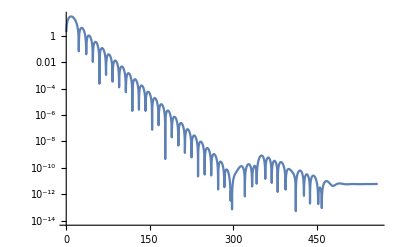

```mathematica
RNdSl1data[[;;,2]]= Abs[RNdSl1data[[;;,2]]];
ListLogPlot[{RNdSl1data},Joined->True,PlotRange->Automatic]
```

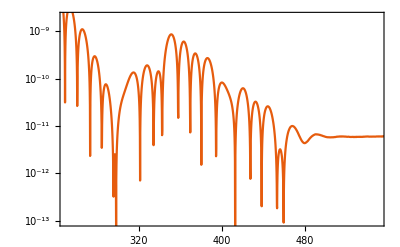

```mathematica
Show[ListLogPlot[{RNdSl1data},Joined->True,PlotRange->Automatic,PlotTheme->"Scientific"],PlotRange->{{250,550},{-30,-20}}]
```

## Appendix-Checking result of NDSolve in r_* (RNdS model)

```mathematica
M=1; Q=3/10; Λ=2/100;revent= 2.0092878253392454;
```

```mathematica
lowsolrnds=NDSolve[{r'[rstar]==1-(2 M)/r[rstar]+Q^2/r[rstar]^2- (Λ  r[rstar]^2)/3,r[0]==1.01revent},r,{rstar,-10000,10000},Method->"StiffnessSwitching",PrecisionGoal->MachinePrecision]
```

{{r→InterpolatingFunction[{{-10000., 10000.}}, <>]}}

```mathematica
highsolrnds=NDSolve[{r'[rstar]==1-(2 M)/r[rstar]+Q^2/r[rstar]^2- (Λ  r[rstar]^2)/3,r[0]==1.01revent},r,{rstar,-10000,10000},Method->"StiffnessSwitching",PrecisionGoal->MachinePrecision, WorkingPrecision->22, InterpolationOrder-> All ]
```

{{r→InterpolatingFunction[{{-10000.00000000000000000, 10000.00000000000000000}}, <>]}}

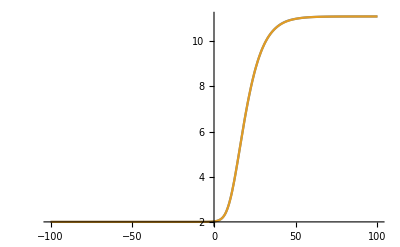

```mathematica
rlow[rstar_]=r[rstar]/.First[Out[4]];
rhigh[rstar_]=r[rstar]/.First[Out[5]];
Plot[{rlow[x],rhigh[x](*,Evaluate[D[r[x],x]]*)},{x,-100,100},PlotRange->Automatic]
```

```mathematica
rlow[5]
rhigh[5]
```

2.18158

2.18190705121429000635

“ Since errors are often quite small, it is useful to view them on a logarithmic scale. RealExponent[x] is effectively equal to Log10[Abs[x]], but without a singularity at zero, so it is a good choice for viewing differences that might be zero at some points ”

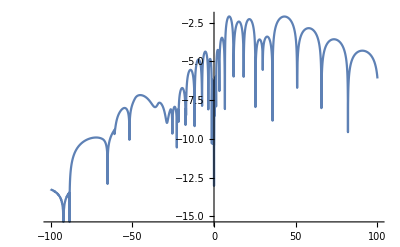

```mathematica
Plot[Evaluate[RealExponent[(rlow[x])-(rhigh[x])]],{x,-100,100}]
```

The residual for a differential equation is the difference of its left and right sides:

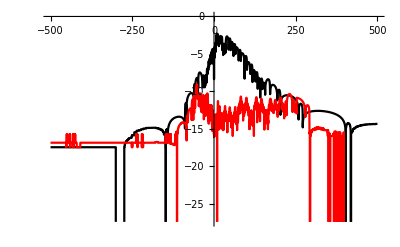

```mathematica
residual[rstar_]=r'[rstar]- ( 1-(2 M)/r[rstar]+Q^2/r[rstar]^2- (Λ  r[rstar]^2)/3 );
Plot[Evaluate[RealExponent[{residual[x]/.lowsolrnds,residual[x]/.highsolrnds}]],{x,-500,500},PlotStyle->{GrayLevel[0],RGBColor[1,0,0]},AxesOrigin->{0,0}]
```

As you can see, the numerical errors are significantly smaller when using the higher WorkingPrecision. The trade off is, of course, increased calculation time.